```mathematica
SetDirectory[NotebookDirectory[]<>"\\SavedObjects"](*Set a directory to save results in*)
```

C:\Users\irisv\Documents\Universiteit\Master\Master Thesis\Mathematica study of paper 1\SavedObjects

## Projection Wetterich equation, single scalar field without anomalous dimension.

For the scalar field theory, we derived the integral in the shift-symmetric approximation (SSA). This integrand can be written in a series, given by my function intrd.

```mathematica
intrd[ω_] = 1/(4π)^2(2k^2*ω-ηs*ω*(k^2-ω))/(k^2+F'[X]*ω)*Sum[Gamma[2]/Gamma[2+n] Gamma[2*n]/Gamma[n](-(X *F''[X]* ω)/(2*(k^2+F '[X]*ω)))^n, {n, 0, ∞}]
```

((2 k^2 ω-ηs (k^2-ω) ω) ∑_(n=0)^∞ (2^-n Gamma[2 n] (-(X ω F''[X])/(k^2+ω F'[X]))^n)/(Gamma[n] Gamma[2+n]))/(16 π^2 (k^2+ω F'[X]))

This can be simplified to a square root as seen below

```mathematica
Simplify[1/(k^2+B*ω)(Sum[Gamma[2]/Gamma[2+n] Gamma[2*n]/Gamma[n](-(X *A* ω)/(2*(k^2+B*ω)))^n, {n, 0, ∞}])]
```

(-1+√((k^2+B ω+2 A X ω)/(k^2+B ω)))/(2 A X ω)

We want to solve this system using a polynomial expansion for X. This means it is easier to work with the integrand still written as a series. First we will choose the order of our polynomial. This is given by Nmaxi.

```mathematica
Nmaxi = 2
```

2

Next we add in the Nth order polynomial approximation of the interaction term (F)

```mathematica
F[X_] := Sum[k^(4-4n)u[n, Nmaxi]X^n , {n, 2, Nmaxi}]
```

```mathematica
F''[X]
```

(2 u[2,2])/k^4

Using this the generating functional as a whole becomes:

```mathematica
func:=Simplify[(-ηs * X +Sum[(β[n, Nmaxi]+4(1-n)u[n, Nmaxi]- n*ηs * u[n, Nmaxi])k^(4(1-n))X^n , {n, 2, Nmaxi}])*k^(-4)/. X-> k^4X]
```

Also the other side of the Wetterich equation has to be expanded in order X. This is the side with the integral.  This way one can solve every power of X seperately. We start this by taking the integrand and expanding it into a series (sintrd)

```mathematica
sintrd[ω_]:= Normal[Simplify[Series[intrd[ω], {X, 0, Nmaxi}]]]
```

Next step is the actual integration, here called SInt

```mathematica
SInt[ω_] :=Integrate[sintrd[ω], ω]
```

Now we just need to add in the upper and lower bound of the integral, and collect our results.

```mathematica
SIntzero := SInt[ω] /. ω-> 0
```

```mathematica
SIntk := SInt[ω] /. ω-> k^2
```

```mathematica
IntegratedCollected := Collect[(SIntzero+SIntk)*k^(-4)/. X-> k^4X, X, Simplify]
```

Now that we have both sides of the expression, we can solve order by order for X.

```mathematica
Coefficient[IntegratedCollected, X,1 ]
```

((-8+ηs) u[2,2])/(128 π^2)

```mathematica
Solve[Coefficient[IntegratedCollected, X,1 ]==Coefficient[func, X, 1], ηs ]
```

{{ηs→(8 u[2,2])/(128 π^2+u[2,2])}}

```mathematica
β[2, Nmaxi] = 0
```

0

Eta is not zero, but it will approach zero. In order to be able to calculate stability coefficients  we will have to simplify the equations. In this case we will set eta to zero

```mathematica
ηs := 0
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2], u[2, Nmaxi] ]
```

{{u[2,2]→16/5 π^2 (-4-√(16+(5 β[2,2])/(8 π^2)))},{u[2,2]→16/5 π^2 (-4+√(16+(5 β[2,2])/(8 π^2)))}}

```mathematica
%11/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,2]→-252.662},{u[2,2]→0.}}

To then determine the stability coefficients  we have to set beta non-zero and determine the equation for beta

```mathematica
Clear[β]
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2], β[2, Nmaxi] ]
```

{{β[2,2]→(128 π^2 u[2,2]+5 u[2,2]^2)/(32 π^2)}}

```mathematica
β[2,2][u_[2,2]]:=(128 π^2 u[2,2]+5 u[2,2]^2)/(32 π^2)
```

By deriving beta to the different u[n, Nmax] we can get all components of the stability matrix

```mathematica
D[β[2,2][u[2,2]], u[2,2]]/. u[2,2]->-252.66187266788756
```

-4.

```mathematica
EV2 = -4.
```

-4.

For N=2 this is the only component of the stability matrix. This means it is also its only eigenvalue.  Therefore the only stability coefficient is 4.

### N=3

#### Starting definitions

In this section all the necessary definitions to evaluate the system for N=3 (using the initialisation cells as well) are defined.

```mathematica
Nmaxi = 3; (*Start by defining Subscript[N, max]*)
```

```mathematica
func (*Reevaluate the generating functional*)
```

X^2 (-4 u[2,3]+β[2,3]+X (-8 u[3,3]+β[3,3]))

```mathematica
β[2, Nmaxi] := 0(*Set beta=0 to find fixed points*)
β[3, Nmaxi]:= 0
```

```mathematica
IntegratedCollected(*Give the integral of the RHS of the Wetterich equation*)
```

1/(32 π^2)-(X u[2,3])/(16 π^2)+(X^2 (5 u[2,3]^2-4 u[3,3]))/(32 π^2)+(X^3 (-74 u[2,3]^3+105 u[2,3] u[3,3]))/(160 π^2)

#### Fixed point

This section intends to solve the system for beta is 0 to find the fixed points of the system. We specifically look for system with the highest non-zero value for its coordinates. As this is the fixed point we want to follow.

```mathematica
Solve[Coefficient[IntegratedCollected, X,3 ]==Coefficient[func, X, 3], u[3, Nmaxi]](*Solve for both coefficients (u3 and u2)*)
```

{{u[3,3]→(74 u[2,3]^3)/(5 (256 π^2+21 u[2,3]))}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2]/.%, u[2, Nmaxi]]
```

{{u[2,3]→0},{u[2,3]→64/229 (-155-√14865) π^2},{u[2,3]→64/229 (-155+√14865) π^2}}

```mathematica
{{u[2,3]->0},{u[2,3]->64/229 (-155-√14865) π^2},{u[2,3]->64/229 (-155+√14865) π^2}}/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,3]→0.},{u[2,3]→-763.839},{u[2,3]→-91.2393}}

```mathematica
u[3,3] = (74 u[2,3]^3)/(5 (256 π^2+21 u[2,3])) /. u[2,3]->-91.23932937715276
```

-18410.1

So we have found the fixed points for N=3 as well.

#### Beta function

The next step is undertaken in this section. Here we determine all the beta functions. This is necessary to determine the stability matrix.

```mathematica
Clear[β](*To evaluate the beta function, we should clear the 0 now given at beta*)
Clear[u]
```

```mathematica
func
```

X^2 (-4 u[2,3]+β[2,3]+X (-8 u[3,3]+β[3,3]))

First we solve for beta 3:

```mathematica
Solve[Coefficient[IntegratedCollected, X,3 ]==Coefficient[func, X, 3], β[3, Nmaxi]]
```

{{β[3,3]→(-74 u[2,3]^3+1280 π^2 u[3,3]+105 u[2,3] u[3,3])/(160 π^2)}}

```mathematica
β[3,3][u_[2,3], u_[3,3]]=(-74 u[2,3]^3+1280 π^2 u[3,3]+105 u[2,3] u[3,3])/(160 π^2)
```

(-74 u[2,3]^3+1280 π^2 u[3,3]+105 u[2,3] u[3,3])/(160 π^2)

```mathematica
D[β[3,3][u[2,3], u[3,3]], u[2,3]]/. u[2,3]->-91.23932937715276/. u[3,3]-> -18410.105745251334
```

-2394.43

```mathematica
D[β[3,3][u[2,3], u[3,3]], u[3,3]]/. u[2,3]->-91.23932937715276/. u[3,3]-> -18410.105745251334
```

1.93331

Next we solve for beta 2:

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2], β[2, Nmaxi]]
```

{{β[2,3]→(128 π^2 u[2,3]+5 u[2,3]^2-4 u[3,3])/(32 π^2)}}

```mathematica
β[2,3][u_[2,3], u_[3,3]]= (128 π^2 u[2,3]+5 u[2,3]^2-4 u[3,3])/(32 π^2)
```

(128 π^2 u[2,3]+5 u[2,3]^2-4 u[3,3])/(32 π^2)

```mathematica
D[β[2,3][u[2,3], u[3,3]], u[2,3]]/. u[2,3]->-91.23932937715276/. u[3,3]-> -18410.105745251334
```

1.1111

```mathematica
D[β[2,3][u[2,3], u[3,3]], u[3,3]]/. u[2,3]->-91.23932937715276/. u[3,3]-> -18410.105745251334
```

-1/(8 π^2)

Since we see in the pattern from N=2-16 that the beta functions up to N-1 are the same. Therefore I will save these.

```mathematica
β2gen := (128 π^2 u[2,Nmaxi]+5 u[2,Nmaxi]^2-4 u[3,Nmaxi])/(32 π^2)
```

#### Stability matrix

Now we know all 4 components we can construct the stability matrix. From this matrix, we want to know the eigenvalues. These are minus the stability coefficient of the fixed point.

```mathematica
mat3:=Table[D[β[a,3][u[2,3], u[3,3]], u[b,3]],{a,2,Nmaxi},{b,2,Nmaxi}]/. u[2,3]->-91.23932937715276/. u[3,3]-> -18410.105745251334;(*Generate the stability matrix*)
```

```mathematica
mat3//MatrixForm
```

(1.1111 | -1/(8 π^2)
-2394.43 | 1.93331)

```mathematica
Eigenvalues[{{1.1111009852418003,-1/(8 π^2)},{-2394.425810792122,1.9333120690077812}}]
```

{7.04441,-4.}

```mathematica
EV[3] = {7.044413054249583,-4.0000000000000036}(*Save the eigenvalues*)
```

{7.04441,-4.}

### N=4

Using the same steps as for N=3, now the solutions for higher N are determined.

#### Starting definitions

```mathematica
Nmaxi = 4;
func
```

X^2 (-4 u[2,4]+β[2,4]+X (-8 u[3,4]+β[3,4])+X^2 (-12 u[4,4]+β[4,4]))

```mathematica
Factor[X^2 (-4 u[2,4]+β[2,4]+X (-8 u[3,4]+β[3,4])+X^2 (-12 u[4,4]+β[4,4]))]
```

-X^2 (4 u[2,4]+8 X u[3,4]+12 X^2 u[4,4]-β[2,4]-X β[3,4]-X^2 β[4,4])

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

1/(32 π^2)-(X u[2,4])/(16 π^2)+(X^2 (5 u[2,4]^2-4 u[3,4]))/(32 π^2)-(X^3 (222 u[2,4]^3-315 u[2,4] u[3,4]+100 u[4,4]))/(480 π^2)+(X^4 (500 u[2,4]^4-972 u[2,4]^2 u[3,4]+225 u[3,4]^2+360 u[2,4] u[4,4]))/(320 π^2)

#### Fixed point

```mathematica
Solve[Coefficient[IntegratedCollected, X,4 ]==Coefficient[func, X, 4], u[4, Nmaxi]]
```

{{u[4,4]→(-500 u[2,4]^4+972 u[2,4]^2 u[3,4]-225 u[3,4]^2)/(120 (32 π^2+3 u[2,4]))}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,3 ]==Coefficient[func, X, 3]/. %18, u[3, Nmaxi]]
```

{{u[3,4]→32/25 π^2 (32 π^2+3 u[2,4]) (-8-(21 u[2,4])/(32 π^2)+(27 u[2,4]^2)/(16 π^2 (32 π^2+3 u[2,4]))-√(64+(21 u[2,4])/(2 π^2)+(441 u[2,4]^2)/(1024 π^4)+(859 u[2,4]^4)/(576 π^4 (32 π^2+3 u[2,4])^2)-(27 u[2,4]^2)/(π^2 (32 π^2+3 u[2,4]))-(191 u[2,4]^3)/(128 π^4 (32 π^2+3 u[2,4]))))},{u[3,4]→32/25 π^2 (32 π^2+3 u[2,4]) (-8-(21 u[2,4])/(32 π^2)+(27 u[2,4]^2)/(16 π^2 (32 π^2+3 u[2,4]))+√(64+(21 u[2,4])/(2 π^2)+(441 u[2,4]^2)/(1024 π^4)+(859 u[2,4]^4)/(576 π^4 (32 π^2+3 u[2,4])^2)-(27 u[2,4]^2)/(π^2 (32 π^2+3 u[2,4]))-(191 u[2,4]^3)/(128 π^4 (32 π^2+3 u[2,4]))))}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2]/. First[%19], u[2, Nmaxi], Reals]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,4]→-1516.57},{u[2,4]→-45.0005}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2]/. Last[%19], u[2, Nmaxi], Reals]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,4]→0.},{u[2,4]→-260.812}}

There is an imaginary part which is odd, since we were looking for only real answers. But since it is very small, i think it could be a remnant of rounding errors or something like that so I’ll try u2= -45.005.

```mathematica
Solve[Coefficient[IntegratedCollected, X,3 ]==Coefficient[func, X, 3]/. %18, u[3, Nmaxi]]/. u[2,4]->-45.00048823946557
```

{{u[3,4]→-11681.1},{u[3,4]→-2450.39}}

Here we need the first solution, since this is the one that relates to the solution we picked for u2.

```mathematica
Solve[Coefficient[IntegratedCollected, X,4 ]==Coefficient[func, X, 4], u[4, Nmaxi]]/. u[2,4]->-45.00048823946557/. u[3,4]->-11681.079609702923
```

{{u[4,4]→-2.56893×10^6}}

#### Beta functions

Now we can determine the beta functions.

```mathematica
Clear[β]
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,4 ]==Coefficient[func, X, 4], β[4, Nmaxi]]
```

{{β[4,4]→(500 u[2,4]^4-972 u[2,4]^2 u[3,4]+225 u[3,4]^2+3840 π^2 u[4,4]+360 u[2,4] u[4,4])/(320 π^2)}}

```mathematica
β[4,4][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi]]:=(500 u[2,4]^4-972 u[2,4]^2 u[3,4]+225 u[3,4]^2+3840 π^2 u[4,4]+360 u[2,4] u[4,4])/(320 π^2)
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,3]==Coefficient[func, X, 3], β[3, Nmaxi]]
```

{{β[3,4]→(-222 u[2,4]^3+3840 π^2 u[3,4]+315 u[2,4] u[3,4]-100 u[4,4])/(480 π^2)}}

```mathematica
β[3,4][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi]]:= (-222 u[2,4]^3+3840 π^2 u[3,4]+315 u[2,4] u[3,4]-100 u[4,4])/(480 π^2)
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,2]==Coefficient[func, X, 2], β[2, Nmaxi]]
```

{{β[2,4]→(128 π^2 u[2,4]+5 u[2,4]^2-4 u[3,4])/(32 π^2)}}

```mathematica
β[2,4][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi]]:= (128 π^2 u[2,4]+5 u[2,4]^2-4 u[3,4])/(32 π^2)
```

Again now we must save beta_3

```mathematica
β3gen := (-222 u[2,Nmaxi]^3+3840 π^2 u[3,Nmaxi]+315 u[2,Nmaxi] u[3,Nmaxi]-100 u[4,Nmaxi])/(480 π^2)
```

#### Stability matrix

```mathematica
mat:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/. u[2,4]->-45.00048823946557/. u[3,4]->-11681.079609702923/. u[4,4]->-2.5689300891001355*^6;
```

```mathematica
mat//MatrixForm
```

(2.57516 | -1/(8 π^2) | 0
-1061.39 | 5.00783 | -5/(24 π^2)
-674084. | -2287.59 | 6.87056)

```mathematica
Eigenvalues[{{2.5751553959669526,-1/(8 π^2),0},{-1061.3856986958185,5.0078263315306,-5/(24 π^2)},{-674084.3556577517,-2287.5880589338217,6.870559425481029}}]
```

{12.0648,6.38878,-4.}

```mathematica
EV[4] = {12.064765532201356,6.3887756207772295,-4.000000000000002};
```

We again find -4 as lowest eigenvalue.

### N=5

```mathematica
Nmaxi = 5;
```

```mathematica
func
```

X^2 (-4 u[2,5]+β[2,5]+X (-8 u[3,5]+β[3,5])+X^2 (-12 u[4,5]+β[4,5])+X^3 (-16 u[5,5]+β[5,5]))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

1/(32 π^2)-(X u[2,5])/(16 π^2)+(X^2 (5 u[2,5]^2-4 u[3,5]))/(32 π^2)-(X^3 (222 u[2,5]^3-315 u[2,5] u[3,5]+100 u[4,5]))/(480 π^2)+(X^5 (-6540 u[2,5]^5+15820 u[2,5]^3 u[3,5]-5964 u[2,5]^2 u[4,5]+2730 u[3,5] u[4,5]-35 u[2,5] (216 u[3,5]^2-55 u[5,5])))/(1120 π^2)+(X^4 (500 u[2,5]^4-972 u[2,5]^2 u[3,5]+225 u[3,5]^2+360 u[2,5] u[4,5]-100 u[5,5]))/(320 π^2)

#### Fixed point

```mathematica
Solve[Coefficient[IntegratedCollected, X,5 ]==Coefficient[func, X, 5], u[5, Nmaxi] ]
```

{{u[5,5]→(2 (3270 u[2,5]^5-7910 u[2,5]^3 u[3,5]+3780 u[2,5] u[3,5]^2+2982 u[2,5]^2 u[4,5]-1365 u[3,5] u[4,5]))/(35 (512 π^2+55 u[2,5]))}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,4 ]==Coefficient[func, X, 4]/. %, u[4, Nmaxi] ]
```

{{u[4,5]→(-(25 u[2,5]^4)/(16 π^2)+(1635 u[2,5]^5)/(28 π^2 (512 π^2+55 u[2,5]))+(243 u[2,5]^2 u[3,5])/(80 π^2)-(565 u[2,5]^3 u[3,5])/(4 π^2 (512 π^2+55 u[2,5]))-(45 u[3,5]^2)/(64 π^2)+(135 u[2,5] u[3,5]^2)/(2 π^2 (512 π^2+55 u[2,5])))/(12+(9 u[2,5])/(8 π^2)-(213 u[2,5]^2)/(4 π^2 (512 π^2+55 u[2,5]))+(195 u[3,5])/(8 π^2 (512 π^2+55 u[2,5])))}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,3 ]==Coefficient[func, X, 3]/. %, u[3, Nmaxi] ]
```

{{u[3,5]→1/(315 (9216 π^2+341 u[2,5]))(-264241152 π^6-74833920 π^4 u[2,5]-2989728 π^2 u[2,5]^2+59087 u[2,5]^3-√7 √(9974769487183872 π^12+5649771779850240 π^10 u[2,5]+1025733417762816 π^8 u[2,5]^2+72133705728000 π^6 u[2,5]^3+2288261348352 π^4 u[2,5]^4+8544667968 π^2 u[2,5]^5+210120055 u[2,5]^6))},{u[3,5]→1/(315 (9216 π^2+341 u[2,5]))(-264241152 π^6-74833920 π^4 u[2,5]-2989728 π^2 u[2,5]^2+59087 u[2,5]^3+√7 √(9974769487183872 π^12+5649771779850240 π^10 u[2,5]+1025733417762816 π^8 u[2,5]^2+72133705728000 π^6 u[2,5]^3+2288261348352 π^4 u[2,5]^4+8544667968 π^2 u[2,5]^5+210120055 u[2,5]^6))}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2]/. First[%20], u[2, Nmaxi], Reals ]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,5]→-2504.31},{u[2,5]→-134.289},{u[2,5]→-24.6259}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2]/. Last[%20], u[2, Nmaxi] ]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,5]→0.},{u[2,5]→-497.732+6.63242×10^-14 ⅈ}}

We are interested in the highest non-zero value, as this is the fixed point we track.

```mathematica
u[2,5]=-24.625905306442075;
```

```mathematica
First[%20]/.u[2,5]-> -24.625905306442075
```

{u[3,5]→-7019.49}

```mathematica
%19/. u[2,5]-> -24.625905306442075/. u[3,5]->-7019.49017338234
```

{{u[4,5]→-2.08267×10^6}}

```mathematica
%18/. u[2,5]-> -24.625905306442075/. u[3,5]->-7019.49017338234/. u[4,5]->-2.0826696868344978*^6
```

{{u[5,5]→-4.50601×10^8}}

```mathematica
Clear[β]
Clear[u]
```

#### Beta functions

Now we have to determine the equations for beta 2 to 5.

```mathematica
Solve[Coefficient[IntegratedCollected, X,5 ]==Coefficient[func, X, 5], β[5, Nmaxi] ]
```

{{β[5,5]→(-6540 u[2,5]^5+15820 u[2,5]^3 u[3,5]-7560 u[2,5] u[3,5]^2-5964 u[2,5]^2 u[4,5]+2730 u[3,5] u[4,5]+17920 π^2 u[5,5]+1925 u[2,5] u[5,5])/(1120 π^2)}}

```mathematica
β[5,5][u_[2,Nmaxi], u_[3,Nmaxi], u_[4, Nmaxi]u_[5,Nmaxi]]:=(-6540 u[2,5]^5+15820 u[2,5]^3 u[3,5]-7560 u[2,5] u[3,5]^2-5964 u[2,5]^2 u[4,5]+2730 u[3,5] u[4,5]+17920 π^2 u[5,5]+1925 u[2,5] u[5,5])/(1120 π^2)
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,4]==Coefficient[func, X, 4], β[4, Nmaxi] ]
```

{{β[4,5]→(500 u[2,5]^4-972 u[2,5]^2 u[3,5]+225 u[3,5]^2+3840 π^2 u[4,5]+360 u[2,5] u[4,5]-100 u[5,5])/(320 π^2)}}

```mathematica
β[4,5][u_[2,Nmaxi], u_[3,Nmaxi], u_[4, Nmaxi]u_[5,Nmaxi]]:=(500 u[2,5]^4-972 u[2,5]^2 u[3,5]+225 u[3,5]^2+3840 π^2 u[4,5]+360 u[2,5] u[4,5]-100 u[5,5])/(320 π^2)
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,3]==Coefficient[func, X, 3], β[3, Nmaxi] ]
```

{{β[3,5]→(-222 u[2,5]^3+3840 π^2 u[3,5]+315 u[2,5] u[3,5]-100 u[4,5])/(480 π^2)}}

```mathematica
β[3,5][u_[2,Nmaxi], u_[3,Nmaxi], u_[4, Nmaxi]u_[5,Nmaxi]]:=(-222 u[2,5]^3+3840 π^2 u[3,5]+315 u[2,5] u[3,5]-100 u[4,5])/(480 π^2)
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,2]==Coefficient[func, X, 2], β[2, Nmaxi] ]
```

{{β[2,5]→(128 π^2 u[2,5]+5 u[2,5]^2-4 u[3,5])/(32 π^2)}}

```mathematica
β[2,5][u_[2,Nmaxi], u_[3,Nmaxi], u_[4, Nmaxi]u_[5,Nmaxi]]:=(128 π^2 u[2,5]+5 u[2,5]^2-4 u[3,5])/(32 π^2)
```

Save beta 4

```mathematica
β4gen := (500 u[2,Nmaxi]^4-972 u[2,Nmaxi]^2 u[3,Nmaxi]+225 u[3,Nmaxi]^2+3840 π^2 u[4,Nmaxi]+360 u[2,Nmaxi] u[4,Nmaxi]-100 u[5,Nmaxi])/(320 π^2)
```

#### Stability matrix

Now we have all beta functions, we can generate the stability matrix

```mathematica
mat5:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi]u[5,Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/. u[2,5]-> -24.625905306442075/. u[3,5]->-7019.49017338234/. u[4,5]->-2.0826696868344978*^6/. u[5,5]->-4.5060102832623124*^8
```

```mathematica
Simplify[mat5]//MatrixForm
```

(3.22027 | -1/(8 π^2) | 0 | 0
-551.995 | 6.36257 | -5/(24 π^2) | 0
-353254. | -1186.8 | 9.19298 | -5/(16 π^2)
-1.86877×10^8 | -772177. | -2060.8 | 11.7115)

```mathematica
Eigenvalues[mat5]
```

{16.1978,12.4225,5.86701,-4.}

```mathematica
EV[5 ]= {16.19781185833985,12.422512993599995,5.867007753767463,-4.000000000000007};
```

This again has as lowest eigenvalue -4.

### N=6

#### Starting definitions

```mathematica
Nmaxi = 6;
```

```mathematica
func
```

X^2 (-4 u[2,6]+β[2,6]+X (-8 u[3,6]+β[3,6])+X^2 (-12 u[4,6]+β[4,6])+X^3 (-16 u[5,6]+β[5,6])+X^4 (-20 u[6,6]+β[6,6]))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

1/(32 π^2)-(X u[2,6])/(16 π^2)+(X^2 (5 u[2,6]^2-4 u[3,6]))/(32 π^2)-(X^3 (222 u[2,6]^3-315 u[2,6] u[3,6]+100 u[4,6]))/(480 π^2)+(X^4 (500 u[2,6]^4-972 u[2,6]^2 u[3,6]+225 u[3,6]^2+360 u[2,6] u[4,6]-100 u[5,6]))/(320 π^2)+1/(480 π^2)X^6 (11295 u[2,6]^6-32400 u[2,6]^4 u[3,6]+12080 u[2,6]^3 u[4,6]+180 u[2,6]^2 (129 u[3,6]^2-22 u[5,6])-30 (81 u[3,6]^3-34 u[4,6]^2-60 u[3,6] u[5,6])-18 u[2,6] (636 u[3,6] u[4,6]-65 u[6,6]))+(X^5 (-6540 u[2,6]^5+15820 u[2,6]^3 u[3,6]-5964 u[2,6]^2 u[4,6]-35 u[2,6] (216 u[3,6]^2-55 u[5,6])+70 (39 u[3,6] u[4,6]-7 u[6,6])))/(1120 π^2)

#### Fixed points

```mathematica
Solve[Coefficient[IntegratedCollected, X,6 ]==Coefficient[func, X, 6], u[6, Nmaxi] ]
```

{{u[6,6]→1/(30 (320 π^2+39 u[2,6]))(-11295 u[2,6]^6+32400 u[2,6]^4 u[3,6]-23220 u[2,6]^2 u[3,6]^2+2430 u[3,6]^3-12080 u[2,6]^3 u[4,6]+11448 u[2,6] u[3,6] u[4,6]-1020 u[4,6]^2+3960 u[2,6]^2 u[5,6]-1800 u[3,6] u[5,6])}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,5 ]==Coefficient[func, X, 5]/.%19, u[5, Nmaxi] ]
```

{{u[5,6]→((327 u[2,6]^5)/(56 π^2)-(5271 u[2,6]^6)/(32 π^2 (320 π^2+39 u[2,6]))-(113 u[2,6]^3 u[3,6])/(8 π^2)+(945 u[2,6]^4 u[3,6])/(2 π^2 (320 π^2+39 u[2,6]))+(27 u[2,6] u[3,6]^2)/(4 π^2)-(2709 u[2,6]^2 u[3,6]^2)/(8 π^2 (320 π^2+39 u[2,6]))+(567 u[3,6]^3)/(16 π^2 (320 π^2+39 u[2,6]))+(213 u[2,6]^2 u[4,6])/(40 π^2)-(1057 u[2,6]^3 u[4,6])/(6 π^2 (320 π^2+39 u[2,6]))-(39 u[3,6] u[4,6])/(16 π^2)+(3339 u[2,6] u[3,6] u[4,6])/(20 π^2 (320 π^2+39 u[2,6]))-(119 u[4,6]^2)/(8 π^2 (320 π^2+39 u[2,6])))/(16+(55 u[2,6])/(32 π^2)-(231 u[2,6]^2)/(4 π^2 (320 π^2+39 u[2,6]))+(105 u[3,6])/(4 π^2 (320 π^2+39 u[2,6])))}}

```mathematica
Simplify[Solve[Coefficient[IntegratedCollected, X,4 ]==Coefficient[func, X, 4]/. %21, u[4, Nmaxi] ]]
```

{{u[4,6]→1/7140(-47185920 π^6-457 u[2,6]^3-5427 u[2,6] u[3,6]-297 u[2,6]^2 √((2226511046246400 π^12+1438534871285760 π^10 u[2,6]+57124849 u[2,6]^6-404285958 u[2,6]^4 u[3,6]+574007634 u[2,6]^2 u[3,6]^2-80967600 u[3,6]^3+339738624 π^8 (875849 u[2,6]^2+119200 u[3,6])+1179648 π^6 (17892317 u[2,6]^3+11524230 u[2,6] u[3,6])+9216 π^4 (43788565 u[2,6]^4+100800576 u[2,6]^2 u[3,6]+15696900 u[3,6]^2)-1728 π^2 (7570719 u[2,6]^5-18234473 u[2,6]^3 u[3,6]-1740435 u[2,6] u[3,6]^2))/(163840 π^4+37568 π^2 u[2,6]+297 u[2,6]^2+840 u[3,6])^2)-840 u[3,6] √((2226511046246400 π^12+1438534871285760 π^10 u[2,6]+57124849 u[2,6]^6-404285958 u[2,6]^4 u[3,6]+574007634 u[2,6]^2 u[3,6]^2-80967600 u[3,6]^3+339738624 π^8 (875849 u[2,6]^2+119200 u[3,6])+1179648 π^6 (17892317 u[2,6]^3+11524230 u[2,6] u[3,6])+9216 π^4 (43788565 u[2,6]^4+100800576 u[2,6]^2 u[3,6]+15696900 u[3,6]^2)-1728 π^2 (7570719 u[2,6]^5-18234473 u[2,6]^3 u[3,6]-1740435 u[2,6] u[3,6]^2))/(163840 π^4+37568 π^2 u[2,6]+297 u[2,6]^2+840 u[3,6])^2)-2048 π^4 (7443 u[2,6]+80 √((2226511046246400 π^12+1438534871285760 π^10 u[2,6]+57124849 u[2,6]^6-404285958 u[2,6]^4 u[3,6]+574007634 u[2,6]^2 u[3,6]^2-80967600 u[3,6]^3+339738624 π^8 (875849 u[2,6]^2+119200 u[3,6])+1179648 π^6 (17892317 u[2,6]^3+11524230 u[2,6] u[3,6])+9216 π^4 (43788565 u[2,6]^4+100800576 u[2,6]^2 u[3,6]+15696900 u[3,6]^2)-1728 π^2 (7570719 u[2,6]^5-18234473 u[2,6]^3 u[3,6]-1740435 u[2,6] u[3,6]^2))/(163840 π^4+37568 π^2 u[2,6]+297 u[2,6]^2+840 u[3,6])^2))-32 π^2 (21591 u[2,6]^2+13410 u[3,6]+1174 u[2,6] √((2226511046246400 π^12+1438534871285760 π^10 u[2,6]+57124849 u[2,6]^6-404285958 u[2,6]^4 u[3,6]+574007634 u[2,6]^2 u[3,6]^2-80967600 u[3,6]^3+339738624 π^8 (875849 u[2,6]^2+119200 u[3,6])+1179648 π^6 (17892317 u[2,6]^3+11524230 u[2,6] u[3,6])+9216 π^4 (43788565 u[2,6]^4+100800576 u[2,6]^2 u[3,6]+15696900 u[3,6]^2)-1728 π^2 (7570719 u[2,6]^5-18234473 u[2,6]^3 u[3,6]-1740435 u[2,6] u[3,6]^2))/(163840 π^4+37568 π^2 u[2,6]+297 u[2,6]^2+840 u[3,6])^2)))},{u[4,6]→1/7140(-47185920 π^6-457 u[2,6]^3-5427 u[2,6] u[3,6]+297 u[2,6]^2 √((2226511046246400 π^12+1438534871285760 π^10 u[2,6]+57124849 u[2,6]^6-404285958 u[2,6]^4 u[3,6]+574007634 u[2,6]^2 u[3,6]^2-80967600 u[3,6]^3+339738624 π^8 (875849 u[2,6]^2+119200 u[3,6])+1179648 π^6 (17892317 u[2,6]^3+11524230 u[2,6] u[3,6])+9216 π^4 (43788565 u[2,6]^4+100800576 u[2,6]^2 u[3,6]+15696900 u[3,6]^2)-1728 π^2 (7570719 u[2,6]^5-18234473 u[2,6]^3 u[3,6]-1740435 u[2,6] u[3,6]^2))/(163840 π^4+37568 π^2 u[2,6]+297 u[2,6]^2+840 u[3,6])^2)+840 u[3,6] √((2226511046246400 π^12+1438534871285760 π^10 u[2,6]+57124849 u[2,6]^6-404285958 u[2,6]^4 u[3,6]+574007634 u[2,6]^2 u[3,6]^2-80967600 u[3,6]^3+339738624 π^8 (875849 u[2,6]^2+119200 u[3,6])+1179648 π^6 (17892317 u[2,6]^3+11524230 u[2,6] u[3,6])+9216 π^4 (43788565 u[2,6]^4+100800576 u[2,6]^2 u[3,6]+15696900 u[3,6]^2)-1728 π^2 (7570719 u[2,6]^5-18234473 u[2,6]^3 u[3,6]-1740435 u[2,6] u[3,6]^2))/(163840 π^4+37568 π^2 u[2,6]+297 u[2,6]^2+840 u[3,6])^2)+2048 π^4 (-7443 u[2,6]+80 √((2226511046246400 π^12+1438534871285760 π^10 u[2,6]+57124849 u[2,6]^6-404285958 u[2,6]^4 u[3,6]+574007634 u[2,6]^2 u[3,6]^2-80967600 u[3,6]^3+339738624 π^8 (875849 u[2,6]^2+119200 u[3,6])+1179648 π^6 (17892317 u[2,6]^3+11524230 u[2,6] u[3,6])+9216 π^4 (43788565 u[2,6]^4+100800576 u[2,6]^2 u[3,6]+15696900 u[3,6]^2)-1728 π^2 (7570719 u[2,6]^5-18234473 u[2,6]^3 u[3,6]-1740435 u[2,6] u[3,6]^2))/(163840 π^4+37568 π^2 u[2,6]+297 u[2,6]^2+840 u[3,6])^2))+32 π^2 (-21591 u[2,6]^2-13410 u[3,6]+1174 u[2,6] √((2226511046246400 π^12+1438534871285760 π^10 u[2,6]+57124849 u[2,6]^6-404285958 u[2,6]^4 u[3,6]+574007634 u[2,6]^2 u[3,6]^2-80967600 u[3,6]^3+339738624 π^8 (875849 u[2,6]^2+119200 u[3,6])+1179648 π^6 (17892317 u[2,6]^3+11524230 u[2,6] u[3,6])+9216 π^4 (43788565 u[2,6]^4+100800576 u[2,6]^2 u[3,6]+15696900 u[3,6]^2)-1728 π^2 (7570719 u[2,6]^5-18234473 u[2,6]^3 u[3,6]-1740435 u[2,6] u[3,6]^2))/(163840 π^4+37568 π^2 u[2,6]+297 u[2,6]^2+840 u[3,6])^2)))}}

```mathematica
Simplify[Solve[Coefficient[IntegratedCollected, X,3 ]==Coefficient[func, X, 3]/. First[%22], u[3, Nmaxi] ]]
```

{{u[3,6]→(-18153472 π^4-1880992 π^2 u[2,6]-10655 u[2,6]^2)/12600+(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)/(4 2^(2/3) (-43148332535152874260267008000000 π^12-12700667725507395336536064000000 π^10 u[2,6]-1310502476671834719780864000000 π^8 u[2,6]^2-57207556447547773897728000000 π^6 u[2,6]^3-1094362896444039583200000000 π^4 u[2,6]^4-11965872725583848505000000 π^2 u[2,6]^5-63971034366354560156250 u[2,6]^6+7813968750 √(-(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)^3+(5521948438193187586048 π^12+1625379897444227088384 π^10 u[2,6]+167712787010036957184 π^8 u[2,6]^2+7321190841407930368 π^6 u[2,6]^3+140052120946099200 π^4 u[2,6]^4+1531343816237280 π^2 u[2,6]^5+8186753289275 u[2,6]^6)^2))^(1/3))+1/(19845000 2^(1/3))(-43148332535152874260267008000000 π^12-12700667725507395336536064000000 π^10 u[2,6]-1310502476671834719780864000000 π^8 u[2,6]^2-57207556447547773897728000000 π^6 u[2,6]^3-1094362896444039583200000000 π^4 u[2,6]^4-11965872725583848505000000 π^2 u[2,6]^5-63971034366354560156250 u[2,6]^6+7813968750 √(-(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)^3+(5521948438193187586048 π^12+1625379897444227088384 π^10 u[2,6]+167712787010036957184 π^8 u[2,6]^2+7321190841407930368 π^6 u[2,6]^3+140052120946099200 π^4 u[2,6]^4+1531343816237280 π^2 u[2,6]^5+8186753289275 u[2,6]^6)^2))^(1/3)},{u[3,6]→(-18153472 π^4-1880992 π^2 u[2,6]-10655 u[2,6]^2)/12600-((1+ⅈ √3) (312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4))/(8 2^(2/3) (-43148332535152874260267008000000 π^12-12700667725507395336536064000000 π^10 u[2,6]-1310502476671834719780864000000 π^8 u[2,6]^2-57207556447547773897728000000 π^6 u[2,6]^3-1094362896444039583200000000 π^4 u[2,6]^4-11965872725583848505000000 π^2 u[2,6]^5-63971034366354560156250 u[2,6]^6+7813968750 √(-(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)^3+(5521948438193187586048 π^12+1625379897444227088384 π^10 u[2,6]+167712787010036957184 π^8 u[2,6]^2+7321190841407930368 π^6 u[2,6]^3+140052120946099200 π^4 u[2,6]^4+1531343816237280 π^2 u[2,6]^5+8186753289275 u[2,6]^6)^2))^(1/3))+1/(39690000 2^(1/3))(-1+ⅈ √3) (-43148332535152874260267008000000 π^12-12700667725507395336536064000000 π^10 u[2,6]-1310502476671834719780864000000 π^8 u[2,6]^2-57207556447547773897728000000 π^6 u[2,6]^3-1094362896444039583200000000 π^4 u[2,6]^4-11965872725583848505000000 π^2 u[2,6]^5-63971034366354560156250 u[2,6]^6+7813968750 √(-(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)^3+(5521948438193187586048 π^12+1625379897444227088384 π^10 u[2,6]+167712787010036957184 π^8 u[2,6]^2+7321190841407930368 π^6 u[2,6]^3+140052120946099200 π^4 u[2,6]^4+1531343816237280 π^2 u[2,6]^5+8186753289275 u[2,6]^6)^2))^(1/3)},{u[3,6]→(-18153472 π^4-1880992 π^2 u[2,6]-10655 u[2,6]^2)/12600-((1-ⅈ √3) (312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4))/(8 2^(2/3) (-43148332535152874260267008000000 π^12-12700667725507395336536064000000 π^10 u[2,6]-1310502476671834719780864000000 π^8 u[2,6]^2-57207556447547773897728000000 π^6 u[2,6]^3-1094362896444039583200000000 π^4 u[2,6]^4-11965872725583848505000000 π^2 u[2,6]^5-63971034366354560156250 u[2,6]^6+7813968750 √(-(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)^3+(5521948438193187586048 π^12+1625379897444227088384 π^10 u[2,6]+167712787010036957184 π^8 u[2,6]^2+7321190841407930368 π^6 u[2,6]^3+140052120946099200 π^4 u[2,6]^4+1531343816237280 π^2 u[2,6]^5+8186753289275 u[2,6]^6)^2))^(1/3))-1/(39690000 2^(1/3))(1+ⅈ √3) (-43148332535152874260267008000000 π^12-12700667725507395336536064000000 π^10 u[2,6]-1310502476671834719780864000000 π^8 u[2,6]^2-57207556447547773897728000000 π^6 u[2,6]^3-1094362896444039583200000000 π^4 u[2,6]^4-11965872725583848505000000 π^2 u[2,6]^5-63971034366354560156250 u[2,6]^6+7813968750 √(-(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)^3+(5521948438193187586048 π^12+1625379897444227088384 π^10 u[2,6]+167712787010036957184 π^8 u[2,6]^2+7321190841407930368 π^6 u[2,6]^3+140052120946099200 π^4 u[2,6]^4+1531343816237280 π^2 u[2,6]^5+8186753289275 u[2,6]^6)^2))^(1/3)}}

```mathematica
Simplify[Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2]/. First[%23], u[2, Nmaxi] ]]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,6]→0.},{u[2,6]→-3706.34}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2]/. %23[[2]], u[2, Nmaxi] ]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,6]→-254.806}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2]/. %23[[3]], u[2, Nmaxi] ]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,6]→-802.925},{u[2,6]→-80.8239},{u[2,6]→-14.0763}}

```mathematica
Simplify[Solve[Coefficient[IntegratedCollected, X,3 ]==Coefficient[func, X, 3]/. %22[[2]], u[3, Nmaxi] ]]
```

{{u[3,6]→(-18153472 π^4-1880992 π^2 u[2,6]-10655 u[2,6]^2)/12600+(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)/(4 2^(2/3) (-43148332535152874260267008000000 π^12-12700667725507395336536064000000 π^10 u[2,6]-1310502476671834719780864000000 π^8 u[2,6]^2-57207556447547773897728000000 π^6 u[2,6]^3-1094362896444039583200000000 π^4 u[2,6]^4-11965872725583848505000000 π^2 u[2,6]^5-63971034366354560156250 u[2,6]^6+7813968750 √(-(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)^3+(5521948438193187586048 π^12+1625379897444227088384 π^10 u[2,6]+167712787010036957184 π^8 u[2,6]^2+7321190841407930368 π^6 u[2,6]^3+140052120946099200 π^4 u[2,6]^4+1531343816237280 π^2 u[2,6]^5+8186753289275 u[2,6]^6)^2))^(1/3))+1/(19845000 2^(1/3))(-43148332535152874260267008000000 π^12-12700667725507395336536064000000 π^10 u[2,6]-1310502476671834719780864000000 π^8 u[2,6]^2-57207556447547773897728000000 π^6 u[2,6]^3-1094362896444039583200000000 π^4 u[2,6]^4-11965872725583848505000000 π^2 u[2,6]^5-63971034366354560156250 u[2,6]^6+7813968750 √(-(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)^3+(5521948438193187586048 π^12+1625379897444227088384 π^10 u[2,6]+167712787010036957184 π^8 u[2,6]^2+7321190841407930368 π^6 u[2,6]^3+140052120946099200 π^4 u[2,6]^4+1531343816237280 π^2 u[2,6]^5+8186753289275 u[2,6]^6)^2))^(1/3)},{u[3,6]→(-18153472 π^4-1880992 π^2 u[2,6]-10655 u[2,6]^2)/12600-((1+ⅈ √3) (312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4))/(8 2^(2/3) (-43148332535152874260267008000000 π^12-12700667725507395336536064000000 π^10 u[2,6]-1310502476671834719780864000000 π^8 u[2,6]^2-57207556447547773897728000000 π^6 u[2,6]^3-1094362896444039583200000000 π^4 u[2,6]^4-11965872725583848505000000 π^2 u[2,6]^5-63971034366354560156250 u[2,6]^6+7813968750 √(-(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)^3+(5521948438193187586048 π^12+1625379897444227088384 π^10 u[2,6]+167712787010036957184 π^8 u[2,6]^2+7321190841407930368 π^6 u[2,6]^3+140052120946099200 π^4 u[2,6]^4+1531343816237280 π^2 u[2,6]^5+8186753289275 u[2,6]^6)^2))^(1/3))+1/(39690000 2^(1/3))(-1+ⅈ √3) (-43148332535152874260267008000000 π^12-12700667725507395336536064000000 π^10 u[2,6]-1310502476671834719780864000000 π^8 u[2,6]^2-57207556447547773897728000000 π^6 u[2,6]^3-1094362896444039583200000000 π^4 u[2,6]^4-11965872725583848505000000 π^2 u[2,6]^5-63971034366354560156250 u[2,6]^6+7813968750 √(-(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)^3+(5521948438193187586048 π^12+1625379897444227088384 π^10 u[2,6]+167712787010036957184 π^8 u[2,6]^2+7321190841407930368 π^6 u[2,6]^3+140052120946099200 π^4 u[2,6]^4+1531343816237280 π^2 u[2,6]^5+8186753289275 u[2,6]^6)^2))^(1/3)},{u[3,6]→(-18153472 π^4-1880992 π^2 u[2,6]-10655 u[2,6]^2)/12600-((1-ⅈ √3) (312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4))/(8 2^(2/3) (-43148332535152874260267008000000 π^12-12700667725507395336536064000000 π^10 u[2,6]-1310502476671834719780864000000 π^8 u[2,6]^2-57207556447547773897728000000 π^6 u[2,6]^3-1094362896444039583200000000 π^4 u[2,6]^4-11965872725583848505000000 π^2 u[2,6]^5-63971034366354560156250 u[2,6]^6+7813968750 √(-(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)^3+(5521948438193187586048 π^12+1625379897444227088384 π^10 u[2,6]+167712787010036957184 π^8 u[2,6]^2+7321190841407930368 π^6 u[2,6]^3+140052120946099200 π^4 u[2,6]^4+1531343816237280 π^2 u[2,6]^5+8186753289275 u[2,6]^6)^2))^(1/3))-1/(39690000 2^(1/3))(1+ⅈ √3) (-43148332535152874260267008000000 π^12-12700667725507395336536064000000 π^10 u[2,6]-1310502476671834719780864000000 π^8 u[2,6]^2-57207556447547773897728000000 π^6 u[2,6]^3-1094362896444039583200000000 π^4 u[2,6]^4-11965872725583848505000000 π^2 u[2,6]^5-63971034366354560156250 u[2,6]^6+7813968750 √(-(312637111926784 π^8+61442619342848 π^6 u[2,6]+3340683305984 π^4 u[2,6]^2+49616098240 π^2 u[2,6]^3+411072985 u[2,6]^4)^3+(5521948438193187586048 π^12+1625379897444227088384 π^10 u[2,6]+167712787010036957184 π^8 u[2,6]^2+7321190841407930368 π^6 u[2,6]^3+140052120946099200 π^4 u[2,6]^4+1531343816237280 π^2 u[2,6]^5+8186753289275 u[2,6]^6)^2))^(1/3)}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2]/. %28[[1]], u[2, Nmaxi] ]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,6]→0.},{u[2,6]→-3706.34}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2]/. %28[[2]], u[2, Nmaxi] ]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,6]→-254.806}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2]/. %28[[3]], u[2, Nmaxi] ]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,6]→-802.925},{u[2,6]→-80.8239},{u[2,6]→-14.0763}}

The two different solutions for u4 give the same u2 values. -> Double check

Now we want the highest non-zero u2 value and using this, we can calculate all other values.

```mathematica
%105[[3]]/. u[2,6]->-14.076269429059257
```

{u[3,6]→-4197.99-2.18279×10^-10 ⅈ}

```mathematica
%104[[1]]/. u[2,6]->-14.076269429059257/. u[3,6]->-4197.994041356527-2.1827872842550278*^-10 ⅈ
```

{u[4,6]→-1.39868×10^6+1.03816×10^-6 ⅈ}

```mathematica
%103/. u[2,6]->-14.076269429059257/. u[3,6]->-4197.994041356527-2.1827872842550278*^-10 ⅈ/. u[4,6]->-1.3986776716336438*^6+1.038161403272957*^-6 ⅈ
```

{{u[5,6]→-4.11278×10^8+0.000345391 ⅈ}}

```mathematica
%102/. u[2,6]->-14.076269429059257/. u[3,6]->-4197.994041356527-2.1827872842550278*^-10 ⅈ/. u[4,6]->-1.3986776716336438*^6+1.038161403272957*^-6 ⅈ/. u[5,6]->-4.11277934150226*^8+0.00034539121181647827 ⅈ
```

{{u[6,6]→-8.54061×10^10+0.080901 ⅈ}}

#### Beta functions

When we know the values for u, we can then calculate the beta functions

```mathematica
Clear[β]
Clear[u]
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,6 ]==Coefficient[func, X, 6], β[6, Nmaxi] ]
```

{{β[6,6]→1/(480 π^2)(11295 u[2,6]^6-32400 u[2,6]^4 u[3,6]+23220 u[2,6]^2 u[3,6]^2-2430 u[3,6]^3+12080 u[2,6]^3 u[4,6]-11448 u[2,6] u[3,6] u[4,6]+1020 u[4,6]^2-3960 u[2,6]^2 u[5,6]+1800 u[3,6] u[5,6]+9600 π^2 u[6,6]+1170 u[2,6] u[6,6])}}

```mathematica
β[6,6][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi]]:=1/(480 π^2)(11295 u[2,6]^6-32400 u[2,6]^4 u[3,6]+23220 u[2,6]^2 u[3,6]^2-2430 u[3,6]^3+12080 u[2,6]^3 u[4,6]-11448 u[2,6] u[3,6] u[4,6]+1020 u[4,6]^2-3960 u[2,6]^2 u[5,6]+1800 u[3,6] u[5,6]+9600 π^2 u[6,6]+1170 u[2,6] u[6,6])
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,5]==Coefficient[func, X, 5], β[5, Nmaxi] ]
```

{{β[5,6]→(-6540 u[2,6]^5+15820 u[2,6]^3 u[3,6]-7560 u[2,6] u[3,6]^2-5964 u[2,6]^2 u[4,6]+2730 u[3,6] u[4,6]+17920 π^2 u[5,6]+1925 u[2,6] u[5,6]-490 u[6,6])/(1120 π^2)}}

```mathematica
β[5,6][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi]]:=(-6540 u[2,6]^5+15820 u[2,6]^3 u[3,6]-7560 u[2,6] u[3,6]^2-5964 u[2,6]^2 u[4,6]+2730 u[3,6] u[4,6]+17920 π^2 u[5,6]+1925 u[2,6] u[5,6]-490 u[6,6])/(1120 π^2)
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,4 ]==Coefficient[func, X, 4], β[4, Nmaxi] ]
```

{{β[4,6]→(500 u[2,6]^4-972 u[2,6]^2 u[3,6]+225 u[3,6]^2+3840 π^2 u[4,6]+360 u[2,6] u[4,6]-100 u[5,6])/(320 π^2)}}

```mathematica
β[4,6][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi]]:=(500 u[2,6]^4-972 u[2,6]^2 u[3,6]+225 u[3,6]^2+3840 π^2 u[4,6]+360 u[2,6] u[4,6]-100 u[5,6])/(320 π^2)
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,3 ]==Coefficient[func, X, 3], β[3, Nmaxi] ]
```

{{β[3,6]→(-222 u[2,6]^3+3840 π^2 u[3,6]+315 u[2,6] u[3,6]-100 u[4,6])/(480 π^2)}}

```mathematica
β[3,6][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi]]:=(-222 u[2,6]^3+3840 π^2 u[3,6]+315 u[2,6] u[3,6]-100 u[4,6])/(480 π^2)
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2], β[2, Nmaxi] ]
```

{{β[2,6]→(128 π^2 u[2,6]+5 u[2,6]^2-4 u[3,6])/(32 π^2)}}

```mathematica
β[2,6][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi]]:=(128 π^2 u[2,6]+5 u[2,6]^2-4 u[3,6])/(32 π^2)
```

Save Beta 5

```mathematica
β5gen := 1/(1120 π^2)(-6540 u[2,Nmaxi]^5+15820 u[2,Nmaxi]^3 u[3,Nmaxi]-7560 u[2,Nmaxi] u[3,Nmaxi]^2-5964 u[2,Nmaxi]^2 u[4,Nmaxi]+2730 u[3,Nmaxi] u[4,Nmaxi]+17920 π^2 u[5,Nmaxi]+1925 u[2,Nmaxi] u[5,Nmaxi]-490 u[6,Nmaxi])
```

#### Stability matrix

```mathematica
mat:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi],  u[5, Nmaxi], u[6, Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/. u[2,6]->-14.076269429059257/. u[3,6]->-4197.994041356527-2.1827872842550278*^-10 ⅈ/. u[4,6]->-1.3986776716336438*^6+1.038161403272957*^-6 ⅈ/. u[5,6]->-4.11277934150226*^8+0.00034539121181647827 ⅈ/. u[6,6]->-8.540611472509837*^10+0.08090097227977866 ⅈ
```

```mathematica
mat//MatrixForm
```

(3.5543 | -1/(8 π^2) | 0 | 0 | 0
-306.988-1.45138×10^-11 ⅈ | 7.06404 | -5/(24 π^2) | 0 | 0
-197569.+1.16445×10^-7 ⅈ | -659.123-3.1101×10^-11 ⅈ | 10.3955 | -5/(16 π^2) | 0
-1.08607×10^8+0.0000744783 ⅈ | -430252.+2.52192×10^-7 ⅈ | -1143.68-5.39084×10^-11 ⅈ | 13.5487 | -7/(16 π^2)
-4.98401×10^10+0.039206 ⅈ | -2.39385×10^8+0.000163302 ⅈ | -752200.+4.39623×10^-7 ⅈ | -1760.67-8.2936×10^-11 ⅈ | 16.5236)

```mathematica
Eigenvalues[%52]
```

{18.6457+1.02907 ⅈ,18.6457-1.02907 ⅈ,12.3458-1.71549×10^-12 ⅈ,5.44885-4.99209×10^-13 ⅈ,-4.+1.7645×10^-12 ⅈ}

Here the real part of the lowest eigenvalue is again -4. However I was not expecting there to be an imaginary part, I think this is a remnant of Mathematica calculating this using complex numbers since the imaginaty values are so small.

```mathematica
EV[6] = {18.64572247467246+1.029069376119416 ⅈ,18.64572247464446-1.029069376118969 ⅈ,12.345800719755948-1.7154903991272952*^-12 ⅈ,5.448852582038963-4.992090112233377*^-13 ⅈ,-3.999999999991469+1.76450243034431*^-12 ⅈ}
```

{18.6457+1.02907 ⅈ,18.6457-1.02907 ⅈ,12.3458-1.71549×10^-12 ⅈ,5.44885-4.99209×10^-13 ⅈ,-4.+1.7645×10^-12 ⅈ}

### N=7

#### Starting definitions

```mathematica
Nmaxi = 7;
```

```mathematica
funcseven= func
```

X^2 (-4 u[2,7]+β[2,7]+X (-8 u[3,7]+β[3,7])+X^2 (-12 u[4,7]+β[4,7])+X^3 (-16 u[5,7]+β[5,7])+X^4 (-20 u[6,7]+β[6,7])+X^5 (-24 u[7,7]+β[7,7]))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
```

```mathematica
ICseven = IntegratedCollected
```

1/(32 π^2)-(X u[2,7])/(16 π^2)+(X^2 (5 u[2,7]^2-4 u[3,7]))/(32 π^2)-(X^3 (222 u[2,7]^3-315 u[2,7] u[3,7]+100 u[4,7]))/(480 π^2)+(X^4 (500 u[2,7]^4-972 u[2,7]^2 u[3,7]+225 u[3,7]^2+360 u[2,7] u[4,7]-100 u[5,7]))/(320 π^2)+(X^5 (-6540 u[2,7]^5+15820 u[2,7]^3 u[3,7]-5964 u[2,7]^2 u[4,7]-35 u[2,7] (216 u[3,7]^2-55 u[5,7])+70 (39 u[3,7] u[4,7]-7 u[6,7])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,7]^6-32400 u[2,7]^4 u[3,7]+12080 u[2,7]^3 u[4,7]+180 u[2,7]^2 (129 u[3,7]^2-22 u[5,7])-18 u[2,7] (636 u[3,7] u[4,7]-65 u[6,7])+10 (-243 u[3,7]^3+102 u[4,7]^2+180 u[3,7] u[5,7]-28 u[7,7]))-1/(1120 π^2)3 X^7 (37450 u[2,7]^7-123795 u[2,7]^5 u[3,7]+45400 u[2,7]^4 u[4,7]+300 u[2,7]^3 (391 u[3,7]^2-49 u[5,7])-1470 u[2,7]^2 (44 u[3,7] u[4,7]-3 u[6,7])+35 (288 u[3,7]^2 u[4,7]-70 u[4,7] u[5,7]-57 u[3,7] u[6,7])-7 u[2,7] (3960 u[3,7]^3-1128 u[4,7]^2-1980 u[3,7] u[5,7]+175 u[7,7]))

#### Fixed point

```mathematica
Solve[Coefficient[ICseven, X,7 ]==Coefficient[funcseven, X, 7], u[7, Nmaxi]]
```

{{u[7,7]→1/(35 (256 π^2+35 u[2,7]))(37450 u[2,7]^7-123795 u[2,7]^5 u[3,7]+117300 u[2,7]^3 u[3,7]^2-27720 u[2,7] u[3,7]^3+45400 u[2,7]^4 u[4,7]-64680 u[2,7]^2 u[3,7] u[4,7]+10080 u[3,7]^2 u[4,7]+7896 u[2,7] u[4,7]^2-14700 u[2,7]^3 u[5,7]+13860 u[2,7] u[3,7] u[5,7]-2450 u[4,7] u[5,7]+4410 u[2,7]^2 u[6,7]-1995 u[3,7] u[6,7])}}

```mathematica
Solve[Coefficient[ICseven, X,6 ]==Coefficient[funcseven, X, 6]/.%, u[6, Nmaxi]]
```

{{u[6,7]→(-(753 u[2,7]^6)/(32 π^2)+(3745 u[2,7]^7)/(6 π^2 (256 π^2+35 u[2,7]))+(135 u[2,7]^4 u[3,7])/(2 π^2)-(8253 u[2,7]^5 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))+(1955 u[2,7]^3 u[3,7]^2)/(π^2 (256 π^2+35 u[2,7]))+(81 u[3,7]^3)/(16 π^2)-(462 u[2,7] u[3,7]^3)/(π^2 (256 π^2+35 u[2,7]))-(151 u[2,7]^3 u[4,7])/(6 π^2)+(2270 u[2,7]^4 u[4,7])/(3 π^2 (256 π^2+35 u[2,7]))+(477 u[2,7] u[3,7] u[4,7])/(20 π^2)-(1078 u[2,7]^2 u[3,7] u[4,7])/(π^2 (256 π^2+35 u[2,7]))+(168 u[3,7]^2 u[4,7])/(π^2 (256 π^2+35 u[2,7]))-(17 u[4,7]^2)/(8 π^2)+(658 u[2,7] u[4,7]^2)/(5 π^2 (256 π^2+35 u[2,7]))-(3 u[2,7]^2 (129 u[3,7]^2-22 u[5,7]))/(8 π^2)-(245 u[2,7]^3 u[5,7])/(π^2 (256 π^2+35 u[2,7]))-(15 u[3,7] u[5,7])/(4 π^2)+(231 u[2,7] u[3,7] u[5,7])/(π^2 (256 π^2+35 u[2,7]))-(245 u[4,7] u[5,7])/(6 π^2 (256 π^2+35 u[2,7])))/(20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7])))}}

```mathematica
Solve[Coefficient[ICseven, X,5 ]==Coefficient[funcseven, X, 5]/.%, u[5, Nmaxi]]
```

{{u[5,7]→((327 u[2,7]^5)/(56 π^2)-(113 u[2,7]^3 u[3,7])/(8 π^2)+(27 u[2,7] u[3,7]^2)/(4 π^2)-(5271 u[2,7]^6)/(512 π^4 (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))+(26215 u[2,7]^7)/(96 π^4 (256 π^2+35 u[2,7]) (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))+(945 u[2,7]^4 u[3,7])/(32 π^4 (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))-(57771 u[2,7]^5 u[3,7])/(64 π^4 (256 π^2+35 u[2,7]) (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))-(2709 u[2,7]^2 u[3,7]^2)/(128 π^4 (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))+(13685 u[2,7]^3 u[3,7]^2)/(16 π^4 (256 π^2+35 u[2,7]) (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))+(567 u[3,7]^3)/(256 π^4 (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))-(1617 u[2,7] u[3,7]^3)/(8 π^4 (256 π^2+35 u[2,7]) (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))+(213 u[2,7]^2 u[4,7])/(40 π^2)-(39 u[3,7] u[4,7])/(16 π^2)-(1057 u[2,7]^3 u[4,7])/(96 π^4 (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))+(7945 u[2,7]^4 u[4,7])/(24 π^4 (256 π^2+35 u[2,7]) (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))+(3339 u[2,7] u[3,7] u[4,7])/(320 π^4 (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))-(3773 u[2,7]^2 u[3,7] u[4,7])/(8 π^4 (256 π^2+35 u[2,7]) (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))+(147 u[3,7]^2 u[4,7])/(2 π^4 (256 π^2+35 u[2,7]) (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))-(119 u[4,7]^2)/(128 π^4 (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))+(2303 u[2,7] u[4,7]^2)/(40 π^4 (256 π^2+35 u[2,7]) (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7])))))/(16+(55 u[2,7])/(32 π^2)-(231 u[2,7]^2)/(64 π^4 (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))+(1715 u[2,7]^3)/(16 π^4 (256 π^2+35 u[2,7]) (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))+(105 u[3,7])/(64 π^4 (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))-(1617 u[2,7] u[3,7])/(16 π^4 (256 π^2+35 u[2,7]) (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7]))))+(1715 u[4,7])/(96 π^4 (256 π^2+35 u[2,7]) (20+(39 u[2,7])/(16 π^2)-(147 u[2,7]^2)/(2 π^2 (256 π^2+35 u[2,7]))+(133 u[3,7])/(4 π^2 (256 π^2+35 u[2,7])))))}}

```mathematica
Solve[Coefficient[ICseven, X,4 ]==Coefficient[funcseven, X, 4]/.%, u[4, Nmaxi]]
```

{{u[4,7]→1/(2 (993484800 π^2+42230160 u[2,7]))(-3382286745600 π^8-1555059179520 π^6 u[2,7]-150354247680 π^4 u[2,7]^2-1461456640 π^2 u[2,7]^3-91314440 u[2,7]^4-52724367360 π^4 u[3,7]-4840496640 π^2 u[2,7] u[3,7]+179404680 u[2,7]^2 u[3,7]-51332400 u[3,7]^2-√((3382286745600 π^8+1555059179520 π^6 u[2,7]+150354247680 π^4 u[2,7]^2+1461456640 π^2 u[2,7]^3+91314440 u[2,7]^4+52724367360 π^4 u[3,7]+4840496640 π^2 u[2,7] u[3,7]-179404680 u[2,7]^2 u[3,7]+51332400 u[3,7]^2)^2-4 (993484800 π^2+42230160 u[2,7]) (440401920000 π^6 u[2,7]^4+129048576000 π^4 u[2,7]^5+2803488000 π^2 u[2,7]^6+25894400 u[2,7]^7-856141332480 π^6 u[2,7]^2 u[3,7]-235602640896 π^4 u[2,7]^3 u[3,7]+996307200 π^2 u[2,7]^4 u[3,7]-109652340 u[2,7]^5 u[3,7]+198180864000 π^6 u[3,7]^2+35378380800 π^4 u[2,7] u[3,7]^2-10005847488 π^2 u[2,7]^2 u[3,7]^2+157699983 u[2,7]^3 u[3,7]^2+1693440000 π^2 u[3,7]^3-74661300 u[2,7] u[3,7]^3)))},{u[4,7]→1/(2 (993484800 π^2+42230160 u[2,7]))(-3382286745600 π^8-1555059179520 π^6 u[2,7]-150354247680 π^4 u[2,7]^2-1461456640 π^2 u[2,7]^3-91314440 u[2,7]^4-52724367360 π^4 u[3,7]-4840496640 π^2 u[2,7] u[3,7]+179404680 u[2,7]^2 u[3,7]-51332400 u[3,7]^2+√((3382286745600 π^8+1555059179520 π^6 u[2,7]+150354247680 π^4 u[2,7]^2+1461456640 π^2 u[2,7]^3+91314440 u[2,7]^4+52724367360 π^4 u[3,7]+4840496640 π^2 u[2,7] u[3,7]-179404680 u[2,7]^2 u[3,7]+51332400 u[3,7]^2)^2-4 (993484800 π^2+42230160 u[2,7]) (440401920000 π^6 u[2,7]^4+129048576000 π^4 u[2,7]^5+2803488000 π^2 u[2,7]^6+25894400 u[2,7]^7-856141332480 π^6 u[2,7]^2 u[3,7]-235602640896 π^4 u[2,7]^3 u[3,7]+996307200 π^2 u[2,7]^4 u[3,7]-109652340 u[2,7]^5 u[3,7]+198180864000 π^6 u[3,7]^2+35378380800 π^4 u[2,7] u[3,7]^2-10005847488 π^2 u[2,7]^2 u[3,7]^2+157699983 u[2,7]^3 u[3,7]^2+1693440000 π^2 u[3,7]^3-74661300 u[2,7] u[3,7]^3)))}}

```mathematica
Solve[Coefficient[ICseven, X,3 ]==Coefficient[funcseven, X, 3]/.%23[[1]], u[3, Nmaxi]]
```

{{u[3,7]→-(439017799680 π^6+82136899584 π^4 u[2,7]+2193660768 π^2 u[2,7]^2-12184991 u[2,7]^3)/(12600 (103872 π^2+2467 u[2,7]))-(-47545399277428905345024000000 π^12-16723417371669652989542400000 π^10 u[2,7]-1897068583127504765583360000 π^8 u[2,7]^2-86033228133493103984640000 π^6 u[2,7]^3-1743105931641061868160000 π^4 u[2,7]^4-9070153554357042840000 π^2 u[2,7]^5-55574205880808750625 u[2,7]^6)/(3307500 2^(2/3) (103872 π^2+2467 u[2,7]) (-20631383101199092045041031798849536000000000 π^18-10841903634221510302418914079303270400000000 π^16 u[2,7]-2170144158319430871028094904639160320000000 π^14 u[2,7]^2-213262234325041131560492904556265472000000 π^12 u[2,7]^3-11310071136694998833752935625654272000000 π^10 u[2,7]^4-335735638992184424544052346880000000000 π^8 u[2,7]^5-5316614951800651691340807429120000000 π^6 u[2,7]^6-36516763132754862708354733920000000 π^4 u[2,7]^7-230654546686903867263458037000000 π^2 u[2,7]^8-758363297410221877215101531250 u[2,7]^9+√(4 (-47545399277428905345024000000 π^12-16723417371669652989542400000 π^10 u[2,7]-1897068583127504765583360000 π^8 u[2,7]^2-86033228133493103984640000 π^6 u[2,7]^3-1743105931641061868160000 π^4 u[2,7]^4-9070153554357042840000 π^2 u[2,7]^5-55574205880808750625 u[2,7]^6)^3+(-20631383101199092045041031798849536000000000 π^18-10841903634221510302418914079303270400000000 π^16 u[2,7]-2170144158319430871028094904639160320000000 π^14 u[2,7]^2-213262234325041131560492904556265472000000 π^12 u[2,7]^3-11310071136694998833752935625654272000000 π^10 u[2,7]^4-335735638992184424544052346880000000000 π^8 u[2,7]^5-5316614951800651691340807429120000000 π^6 u[2,7]^6-36516763132754862708354733920000000 π^4 u[2,7]^7-230654546686903867263458037000000 π^2 u[2,7]^8-758363297410221877215101531250 u[2,7]^9)^2))^(1/3))+1/(6615000 2^(1/3) (103872 π^2+2467 u[2,7]))(-20631383101199092045041031798849536000000000 π^18-10841903634221510302418914079303270400000000 π^16 u[2,7]-2170144158319430871028094904639160320000000 π^14 u[2,7]^2-213262234325041131560492904556265472000000 π^12 u[2,7]^3-11310071136694998833752935625654272000000 π^10 u[2,7]^4-335735638992184424544052346880000000000 π^8 u[2,7]^5-5316614951800651691340807429120000000 π^6 u[2,7]^6-36516763132754862708354733920000000 π^4 u[2,7]^7-230654546686903867263458037000000 π^2 u[2,7]^8-758363297410221877215101531250 u[2,7]^9+√(4 (-47545399277428905345024000000 π^12-16723417371669652989542400000 π^10 u[2,7]-1897068583127504765583360000 π^8 u[2,7]^2-86033228133493103984640000 π^6 u[2,7]^3-1743105931641061868160000 π^4 u[2,7]^4-9070153554357042840000 π^2 u[2,7]^5-55574205880808750625 u[2,7]^6)^3+(-20631383101199092045041031798849536000000000 π^18-10841903634221510302418914079303270400000000 π^16 u[2,7]-2170144158319430871028094904639160320000000 π^14 u[2,7]^2-213262234325041131560492904556265472000000 π^12 u[2,7]^3-11310071136694998833752935625654272000000 π^10 u[2,7]^4-335735638992184424544052346880000000000 π^8 u[2,7]^5-5316614951800651691340807429120000000 π^6 u[2,7]^6-36516763132754862708354733920000000 π^4 u[2,7]^7-230654546686903867263458037000000 π^2 u[2,7]^8-758363297410221877215101531250 u[2,7]^9)^2))^(1/3)},{u[3,7]→-(439017799680 π^6+82136899584 π^4 u[2,7]+2193660768 π^2 u[2,7]^2-12184991 u[2,7]^3)/(12600 (103872 π^2+2467 u[2,7]))+((1+ⅈ √3) (-47545399277428905345024000000 π^12-16723417371669652989542400000 π^10 u[2,7]-1897068583127504765583360000 π^8 u[2,7]^2-86033228133493103984640000 π^6 u[2,7]^3-1743105931641061868160000 π^4 u[2,7]^4-9070153554357042840000 π^2 u[2,7]^5-55574205880808750625 u[2,7]^6))/(6615000 2^(2/3) (103872 π^2+2467 u[2,7]) (-20631383101199092045041031798849536000000000 π^18-10841903634221510302418914079303270400000000 π^16 u[2,7]-2170144158319430871028094904639160320000000 π^14 u[2,7]^2-213262234325041131560492904556265472000000 π^12 u[2,7]^3-11310071136694998833752935625654272000000 π^10 u[2,7]^4-335735638992184424544052346880000000000 π^8 u[2,7]^5-5316614951800651691340807429120000000 π^6 u[2,7]^6-36516763132754862708354733920000000 π^4 u[2,7]^7-230654546686903867263458037000000 π^2 u[2,7]^8-758363297410221877215101531250 u[2,7]^9+√(4 (-47545399277428905345024000000 π^12-16723417371669652989542400000 π^10 u[2,7]-1897068583127504765583360000 π^8 u[2,7]^2-86033228133493103984640000 π^6 u[2,7]^3-1743105931641061868160000 π^4 u[2,7]^4-9070153554357042840000 π^2 u[2,7]^5-55574205880808750625 u[2,7]^6)^3+(-20631383101199092045041031798849536000000000 π^18-10841903634221510302418914079303270400000000 π^16 u[2,7]-2170144158319430871028094904639160320000000 π^14 u[2,7]^2-213262234325041131560492904556265472000000 π^12 u[2,7]^3-11310071136694998833752935625654272000000 π^10 u[2,7]^4-335735638992184424544052346880000000000 π^8 u[2,7]^5-5316614951800651691340807429120000000 π^6 u[2,7]^6-36516763132754862708354733920000000 π^4 u[2,7]^7-230654546686903867263458037000000 π^2 u[2,7]^8-758363297410221877215101531250 u[2,7]^9)^2))^(1/3))-1/(13230000 2^(1/3) (103872 π^2+2467 u[2,7]))(1-ⅈ √3) (-20631383101199092045041031798849536000000000 π^18-10841903634221510302418914079303270400000000 π^16 u[2,7]-2170144158319430871028094904639160320000000 π^14 u[2,7]^2-213262234325041131560492904556265472000000 π^12 u[2,7]^3-11310071136694998833752935625654272000000 π^10 u[2,7]^4-335735638992184424544052346880000000000 π^8 u[2,7]^5-5316614951800651691340807429120000000 π^6 u[2,7]^6-36516763132754862708354733920000000 π^4 u[2,7]^7-230654546686903867263458037000000 π^2 u[2,7]^8-758363297410221877215101531250 u[2,7]^9+√(4 (-47545399277428905345024000000 π^12-16723417371669652989542400000 π^10 u[2,7]-1897068583127504765583360000 π^8 u[2,7]^2-86033228133493103984640000 π^6 u[2,7]^3-1743105931641061868160000 π^4 u[2,7]^4-9070153554357042840000 π^2 u[2,7]^5-55574205880808750625 u[2,7]^6)^3+(-20631383101199092045041031798849536000000000 π^18-10841903634221510302418914079303270400000000 π^16 u[2,7]-2170144158319430871028094904639160320000000 π^14 u[2,7]^2-213262234325041131560492904556265472000000 π^12 u[2,7]^3-11310071136694998833752935625654272000000 π^10 u[2,7]^4-335735638992184424544052346880000000000 π^8 u[2,7]^5-5316614951800651691340807429120000000 π^6 u[2,7]^6-36516763132754862708354733920000000 π^4 u[2,7]^7-230654546686903867263458037000000 π^2 u[2,7]^8-758363297410221877215101531250 u[2,7]^9)^2))^(1/3)},{u[3,7]→-(439017799680 π^6+82136899584 π^4 u[2,7]+2193660768 π^2 u[2,7]^2-12184991 u[2,7]^3)/(12600 (103872 π^2+2467 u[2,7]))+((1-ⅈ √3) (-47545399277428905345024000000 π^12-16723417371669652989542400000 π^10 u[2,7]-1897068583127504765583360000 π^8 u[2,7]^2-86033228133493103984640000 π^6 u[2,7]^3-1743105931641061868160000 π^4 u[2,7]^4-9070153554357042840000 π^2 u[2,7]^5-55574205880808750625 u[2,7]^6))/(6615000 2^(2/3) (103872 π^2+2467 u[2,7]) (-20631383101199092045041031798849536000000000 π^18-10841903634221510302418914079303270400000000 π^16 u[2,7]-2170144158319430871028094904639160320000000 π^14 u[2,7]^2-213262234325041131560492904556265472000000 π^12 u[2,7]^3-11310071136694998833752935625654272000000 π^10 u[2,7]^4-335735638992184424544052346880000000000 π^8 u[2,7]^5-5316614951800651691340807429120000000 π^6 u[2,7]^6-36516763132754862708354733920000000 π^4 u[2,7]^7-230654546686903867263458037000000 π^2 u[2,7]^8-758363297410221877215101531250 u[2,7]^9+√(4 (-47545399277428905345024000000 π^12-16723417371669652989542400000 π^10 u[2,7]-1897068583127504765583360000 π^8 u[2,7]^2-86033228133493103984640000 π^6 u[2,7]^3-1743105931641061868160000 π^4 u[2,7]^4-9070153554357042840000 π^2 u[2,7]^5-55574205880808750625 u[2,7]^6)^3+(-20631383101199092045041031798849536000000000 π^18-10841903634221510302418914079303270400000000 π^16 u[2,7]-2170144158319430871028094904639160320000000 π^14 u[2,7]^2-213262234325041131560492904556265472000000 π^12 u[2,7]^3-11310071136694998833752935625654272000000 π^10 u[2,7]^4-335735638992184424544052346880000000000 π^8 u[2,7]^5-5316614951800651691340807429120000000 π^6 u[2,7]^6-36516763132754862708354733920000000 π^4 u[2,7]^7-230654546686903867263458037000000 π^2 u[2,7]^8-758363297410221877215101531250 u[2,7]^9)^2))^(1/3))-1/(13230000 2^(1/3) (103872 π^2+2467 u[2,7]))(1+ⅈ √3) (-20631383101199092045041031798849536000000000 π^18-10841903634221510302418914079303270400000000 π^16 u[2,7]-2170144158319430871028094904639160320000000 π^14 u[2,7]^2-213262234325041131560492904556265472000000 π^12 u[2,7]^3-11310071136694998833752935625654272000000 π^10 u[2,7]^4-335735638992184424544052346880000000000 π^8 u[2,7]^5-5316614951800651691340807429120000000 π^6 u[2,7]^6-36516763132754862708354733920000000 π^4 u[2,7]^7-230654546686903867263458037000000 π^2 u[2,7]^8-758363297410221877215101531250 u[2,7]^9+√(4 (-47545399277428905345024000000 π^12-16723417371669652989542400000 π^10 u[2,7]-1897068583127504765583360000 π^8 u[2,7]^2-86033228133493103984640000 π^6 u[2,7]^3-1743105931641061868160000 π^4 u[2,7]^4-9070153554357042840000 π^2 u[2,7]^5-55574205880808750625 u[2,7]^6)^3+(-20631383101199092045041031798849536000000000 π^18-10841903634221510302418914079303270400000000 π^16 u[2,7]-2170144158319430871028094904639160320000000 π^14 u[2,7]^2-213262234325041131560492904556265472000000 π^12 u[2,7]^3-11310071136694998833752935625654272000000 π^10 u[2,7]^4-335735638992184424544052346880000000000 π^8 u[2,7]^5-5316614951800651691340807429120000000 π^6 u[2,7]^6-36516763132754862708354733920000000 π^4 u[2,7]^7-230654546686903867263458037000000 π^2 u[2,7]^8-758363297410221877215101531250 u[2,7]^9)^2))^(1/3)}}

```mathematica
Solve[Coefficient[ICseven, X,2]==Coefficient[funcseven, X, 2]/.%24[[1]], u[2, Nmaxi]]
```

{{u[2,7]→0}}

```mathematica
Solve[Coefficient[ICseven, X,2]==Coefficient[funcseven, X, 2]/.%24[[2]], u[2, Nmaxi]]
```

$Aborted

Since using solve and solving for all solutions takes really long, (Nsolve gives infinite solution set), we use the command findroot to find the root closest to the previous value we had.

```mathematica
FindRoot[Coefficient[ICseven, X,2]==Coefficient[funcseven, X, 2]/.%24[[2]], {u[2, Nmaxi], -14}, WorkingPrecision->10]
```

{u[2,7]→-52.52416594-5.55802243×10^-17 ⅈ}

```mathematica
NSolve[Coefficient[ICseven, X,2]==Coefficient[funcseven, X, 2]/.%24[[2]], u[2, Nmaxi]]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(142291 u[2,7])/110500 == 1.

{}

```mathematica
Solve[Coefficient[ICseven, X,2]==Coefficient[funcseven, X, 2]/.%24[[3]], u[2, Nmaxi]]
```

```mathematica
FindRoot[Coefficient[ICseven, X,2]==Coefficient[funcseven, X, 2]/.%24[[3]], {u[2, Nmaxi], -14}, WorkingPrecision->30]
```

{u[2,7]→-8.19938007663703163041036428933}

So we have found the value for u2. Using this, we can then calculate the values for u3-u7

```mathematica
%24[[3]]/. u[2,7]->-8.1993800766370316304103642893345021782112185907932282928246`30.
```

{u[3,7]→-2505.55111404715962965076467+0. ⅈ}

```mathematica
%23[[1]]/. u[2,7]->-8.1993800766370316304103642893345021782112185907932282928246`30./. u[3,7]->-2505.55111404715962965076467476983408962142`27.817398146708417+0``24.42731206856894 ⅈ
```

{u[4,7]→-883648.602903133273665163767+0. ⅈ}

```mathematica
%22[[1]]/. u[2,7]->-8.1993800766370316304103642893345021782112185907932282928246`30./. u[3,7]->-2505.55111404715962965076467476983408962142`27.817398146708417+0``24.42731206856894 ⅈ/. %40[[1]]
```

{u[5,7]→-2.9302820040176557469095975×10^8+0. ⅈ}

```mathematica
%21[[1]]/. %38[[1]]/.%39[[1]]/.%40[[1]]/.%54[[1]]
```

{u[6,7]→-8.2430616462870214473076895×10^10+0. ⅈ}

```mathematica
%20[[1]]/. %38[[1]]/.%39[[1]]/.%40[[1]]/.%54[[1]]/. %55[[1]]
```

{u[7,7]→-1.6290192755973875709886807×10^13+0. ⅈ}

#### Beta functions

Now we have all the u-values, we can then determine the beta functions

```mathematica
Clear[u]
Clear[β]
```

```mathematica
Solve[Coefficient[ICseven, X,7 ]==Coefficient[funcseven, X, 7], β[7, Nmaxi]]
```

{{β[7,7]→1/(1120 π^2)3 (-37450 u[2,7]^7+123795 u[2,7]^5 u[3,7]-117300 u[2,7]^3 u[3,7]^2+27720 u[2,7] u[3,7]^3-45400 u[2,7]^4 u[4,7]+64680 u[2,7]^2 u[3,7] u[4,7]-10080 u[3,7]^2 u[4,7]-7896 u[2,7] u[4,7]^2+14700 u[2,7]^3 u[5,7]-13860 u[2,7] u[3,7] u[5,7]+2450 u[4,7] u[5,7]-4410 u[2,7]^2 u[6,7]+1995 u[3,7] u[6,7]+8960 π^2 u[7,7]+1225 u[2,7] u[7,7])}}

```mathematica
β[7,7][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi]]:= 1/(1120 π^2)3 (-37450 u[2,7]^7+123795 u[2,7]^5 u[3,7]-117300 u[2,7]^3 u[3,7]^2+27720 u[2,7] u[3,7]^3-45400 u[2,7]^4 u[4,7]+64680 u[2,7]^2 u[3,7] u[4,7]-10080 u[3,7]^2 u[4,7]-7896 u[2,7] u[4,7]^2+14700 u[2,7]^3 u[5,7]-13860 u[2,7] u[3,7] u[5,7]+2450 u[4,7] u[5,7]-4410 u[2,7]^2 u[6,7]+1995 u[3,7] u[6,7]+8960 π^2 u[7,7]+1225 u[2,7] u[7,7])
```

```mathematica
Solve[Coefficient[ICseven, X,6 ]==Coefficient[funcseven, X, 6], β[6, Nmaxi]]
```

{{β[6,7]→1/(480 π^2)(11295 u[2,7]^6-32400 u[2,7]^4 u[3,7]+23220 u[2,7]^2 u[3,7]^2-2430 u[3,7]^3+12080 u[2,7]^3 u[4,7]-11448 u[2,7] u[3,7] u[4,7]+1020 u[4,7]^2-3960 u[2,7]^2 u[5,7]+1800 u[3,7] u[5,7]+9600 π^2 u[6,7]+1170 u[2,7] u[6,7]-280 u[7,7])}}

```mathematica
β[6,7][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi]]:=1/(480 π^2)(11295 u[2,7]^6-32400 u[2,7]^4 u[3,7]+23220 u[2,7]^2 u[3,7]^2-2430 u[3,7]^3+12080 u[2,7]^3 u[4,7]-11448 u[2,7] u[3,7] u[4,7]+1020 u[4,7]^2-3960 u[2,7]^2 u[5,7]+1800 u[3,7] u[5,7]+9600 π^2 u[6,7]+1170 u[2,7] u[6,7]-280 u[7,7])
```

```mathematica
Solve[Coefficient[ICseven, X,5 ]==Coefficient[funcseven, X, 5], β[5, Nmaxi]]
```

{{β[5,7]→(-6540 u[2,7]^5+15820 u[2,7]^3 u[3,7]-7560 u[2,7] u[3,7]^2-5964 u[2,7]^2 u[4,7]+2730 u[3,7] u[4,7]+17920 π^2 u[5,7]+1925 u[2,7] u[5,7]-490 u[6,7])/(1120 π^2)}}

```mathematica
β[5,7][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi]]:=(-6540 u[2,7]^5+15820 u[2,7]^3 u[3,7]-7560 u[2,7] u[3,7]^2-5964 u[2,7]^2 u[4,7]+2730 u[3,7] u[4,7]+17920 π^2 u[5,7]+1925 u[2,7] u[5,7]-490 u[6,7])/(1120 π^2)
```

```mathematica
Solve[Coefficient[ICseven, X,4]==Coefficient[funcseven, X, 4], β[4, Nmaxi]]
```

{{β[4,7]→(500 u[2,7]^4-972 u[2,7]^2 u[3,7]+225 u[3,7]^2+3840 π^2 u[4,7]+360 u[2,7] u[4,7]-100 u[5,7])/(320 π^2)}}

```mathematica
β[4,7][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi]]:=(500 u[2,7]^4-972 u[2,7]^2 u[3,7]+225 u[3,7]^2+3840 π^2 u[4,7]+360 u[2,7] u[4,7]-100 u[5,7])/(320 π^2)
```

```mathematica
Solve[Coefficient[ICseven, X,3]==Coefficient[funcseven, X, 3], β[3, Nmaxi]]
```

{{β[3,7]→(-222 u[2,7]^3+3840 π^2 u[3,7]+315 u[2,7] u[3,7]-100 u[4,7])/(480 π^2)}}

```mathematica
β[3,7][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi]]:=(-222 u[2,7]^3+3840 π^2 u[3,7]+315 u[2,7] u[3,7]-100 u[4,7])/(480 π^2)
```

```mathematica
Solve[Coefficient[ICseven, X,2]==Coefficient[funcseven, X, 2], β[2, Nmaxi]]
```

{{β[2,7]→(128 π^2 u[2,7]+5 u[2,7]^2-4 u[3,7])/(32 π^2)}}

```mathematica
β[2,7][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi]]:=(128 π^2 u[2,7]+5 u[2,7]^2-4 u[3,7])/(32 π^2)
```

Save beta 6

```mathematica
β6gen := 1/(480 π^2)(11295 u[2,Nmaxi]^6-32400 u[2,Nmaxi]^4 u[3,Nmaxi]+23220 u[2,Nmaxi]^2 u[3,Nmaxi]^2-2430 u[3,Nmaxi]^3+12080 u[2,Nmaxi]^3 u[4,Nmaxi]-11448 u[2,Nmaxi] u[3,Nmaxi] u[4,Nmaxi]+1020 u[4,Nmaxi]^2-3960 u[2,Nmaxi]^2 u[5,Nmaxi]+1800 u[3,Nmaxi] u[5,Nmaxi]+9600 π^2 u[6,Nmaxi]+1170 u[2,Nmaxi] u[6,Nmaxi]-280 u[7,Nmaxi])
```

#### Stability matrix

Now we have all the beta functions, we can determine the stability matrix.

```mathematica
matseven:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi],  u[5, Nmaxi], u[6, Nmaxi], u[7, Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/. %38[[1]]/.%39[[1]]/.%40[[1]]/.%54[[1]]/. %55[[1]]/. %56[[1]]
```

```mathematica
matseven//MatrixForm
```

(3.740384095469291802484383316919 | -1/(8 π^2) | 0 | 0 | 0 | 0
-176.050553006842414937716538+0. ⅈ | 7.454806600485512785217204965529 | -5/(24 π^2) | 0 | 0 | 0
-113718.290409628578423618752+0. ⅈ | -377.6890868495579683342019+0. ⅈ | 11.06538274368945048894377994091 | -5/(16 π^2) | 0 | 0
-6.3877982213355493001574842×10^7+0. ⅈ | -247124.729290123666374538892+0. ⅈ | -655.069792251803085682438658+0. ⅈ | 14.57211252508110491366410824305 | -7/(16 π^2) | 0
-3.0722245200501164083232929×10^10+0. ⅈ | -1.4018840892136809029846473×10^8+0. ⅈ | -431562.697287739286818199541+0. ⅈ | -1008.19266921357776698242681+0. ⅈ | 17.974995944660476059378189872 | -7/(12 π^2)
-1.2526395756021239065790327×10^13+0. ⅈ | -6.8075960862767434931938084×10^10+0. ⅈ | -2.4607979269693725479275626×10^8+0. ⅈ | -667032.1944024754397546007+0. ⅈ | -1437.05771773488201223416636+0. ⅈ | 21.2740330024275639260860248276)

```mathematica
Eigenvalues[%83]
```

{23.636098782093544356122047+1.1436546048589228736230411×10^-28 ⅈ,19.717523433329468359734856-3.0574603866530796768456666 ⅈ,19.717523433329468359734856+3.0574603866530796768456666 ⅈ,11.894222947139370719574358-2.4092039123784097478143636×10^-37 ⅈ,5.1163463159215481806075743-1.1390449480830394889408153×10^-28 ⅈ,-4.-6.2925346028037960364462824×10^-34 ⅈ}

```mathematica
Chop[%84]
```

{23.636098782093544356122047,19.717523433329468359734856-3.0574603866530796768456666 ⅈ,19.717523433329468359734856+3.0574603866530796768456666 ⅈ,11.894222947139370719574358,5.1163463159215481806075743,-4.}

So again our lowest eigenvalue is -4.

```mathematica
EV[7]   = {23.63609878209354435612204699028172709324`26.39862387510801,19.71752343332946835973485582061515725149`26.39862387510801-3.05746038665307967684566656797506746781`26.39862387510801 ⅈ,19.71752343332946835973485582061438697184`26.39862387510801+3.05746038665307967684566656797460713149`26.39862387510801 ⅈ,11.8942229471393707195743582820119711392`26.39862387510801,5.11634631592154818060757425249104343291`26.39862387510801,-4.00000000000000000000000000000000086739`26.39862387510801};
```

### N=8

#### Starting definitions

```mathematica
Nmaxi= 8;
```

```mathematica
funceight = func
```

X^2 (-4 u[2,8]+β[2,8]+X (-8 u[3,8]+β[3,8])+X^2 (-12 u[4,8]+β[4,8])+X^3 (-16 u[5,8]+β[5,8])+X^4 (-20 u[6,8]+β[6,8])+X^5 (-24 u[7,8]+β[7,8])+X^6 (-28 u[8,8]+β[8,8]))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0
```

```mathematica
ICeight = IntegratedCollected
```

1/(32 π^2)-(X u[2,8])/(16 π^2)+(X^2 (5 u[2,8]^2-4 u[3,8]))/(32 π^2)-(X^3 (222 u[2,8]^3-315 u[2,8] u[3,8]+100 u[4,8]))/(480 π^2)+(X^4 (500 u[2,8]^4-972 u[2,8]^2 u[3,8]+225 u[3,8]^2+360 u[2,8] u[4,8]-100 u[5,8]))/(320 π^2)+(X^5 (-6540 u[2,8]^5+15820 u[2,8]^3 u[3,8]-5964 u[2,8]^2 u[4,8]-35 u[2,8] (216 u[3,8]^2-55 u[5,8])+70 (39 u[3,8] u[4,8]-7 u[6,8])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,8]^6-32400 u[2,8]^4 u[3,8]+12080 u[2,8]^3 u[4,8]+180 u[2,8]^2 (129 u[3,8]^2-22 u[5,8])-18 u[2,8] (636 u[3,8] u[4,8]-65 u[6,8])+10 (-243 u[3,8]^3+102 u[4,8]^2+180 u[3,8] u[5,8]-28 u[7,8]))-1/(1120 π^2)3 X^7 (37450 u[2,8]^7-123795 u[2,8]^5 u[3,8]+45400 u[2,8]^4 u[4,8]+300 u[2,8]^3 (391 u[3,8]^2-49 u[5,8])-1470 u[2,8]^2 (44 u[3,8] u[4,8]-3 u[6,8])-7 u[2,8] (3960 u[3,8]^3-1128 u[4,8]^2-1980 u[3,8] u[5,8]+175 u[7,8])+35 (288 u[3,8]^2 u[4,8]-70 u[4,8] u[5,8]-57 u[3,8] u[6,8]+8 u[8,8]))+1/(2240 π^2)X^8 (999572 u[2,8]^8-3734780 u[2,8]^6 u[3,8]+96390 u[3,8]^4+1348200 u[2,8]^5 u[4,8]+75 u[2,8]^4 (58401 u[3,8]^2-5720 u[5,8])-94500 u[3,8]^2 u[5,8]-80 u[2,8]^3 (31800 u[3,8] u[4,8]-1589 u[6,8])+875 (13 u[5,8]^2+24 u[4,8] u[6,8])-42 u[3,8] (2568 u[4,8]^2-385 u[7,8])-4 u[2,8]^2 (411750 u[3,8]^3-87080 u[4,8]^2-152250 u[3,8] u[5,8]+8967 u[7,8])+56 u[2,8] (16020 u[3,8]^2 u[4,8]-2640 u[4,8] u[5,8]-2133 u[3,8] u[6,8]+170 u[8,8]))

#### Fixed point

```mathematica
Solve[Coefficient[ICeight, X,8 ]==Coefficient[funceight, X, 8], u[8, Nmaxi]]
```

{{u[8,8]→1/(560 (112 π^2+17 u[2,8]))(-999572 u[2,8]^8+3734780 u[2,8]^6 u[3,8]-4380075 u[2,8]^4 u[3,8]^2+1647000 u[2,8]^2 u[3,8]^3-96390 u[3,8]^4-1348200 u[2,8]^5 u[4,8]+2544000 u[2,8]^3 u[3,8] u[4,8]-897120 u[2,8] u[3,8]^2 u[4,8]-348320 u[2,8]^2 u[4,8]^2+107856 u[3,8] u[4,8]^2+429000 u[2,8]^4 u[5,8]-609000 u[2,8]^2 u[3,8] u[5,8]+94500 u[3,8]^2 u[5,8]+147840 u[2,8] u[4,8] u[5,8]-11375 u[5,8]^2-127120 u[2,8]^3 u[6,8]+119448 u[2,8] u[3,8] u[6,8]-21000 u[4,8] u[6,8]+35868 u[2,8]^2 u[7,8]-16170 u[3,8] u[7,8])}}

```mathematica
Solve[Coefficient[ICeight, X,7 ]==Coefficient[funceight, X, 7]/.%, u[7, Nmaxi]]
```

{{u[7,8]→((1605 u[2,8]^7)/(16 π^2)-(107097 u[2,8]^8)/(80 π^2 (112 π^2+17 u[2,8]))-(10611 u[2,8]^5 u[3,8])/(32 π^2)+(80031 u[2,8]^6 u[3,8])/(16 π^2 (112 π^2+17 u[2,8]))-(375435 u[2,8]^4 u[3,8]^2)/(64 π^2 (112 π^2+17 u[2,8]))-(297 u[2,8] u[3,8]^3)/(4 π^2)+(123525 u[2,8]^2 u[3,8]^3)/(56 π^2 (112 π^2+17 u[2,8]))-(4131 u[3,8]^4)/(32 π^2 (112 π^2+17 u[2,8]))+(3405 u[2,8]^4 u[4,8])/(28 π^2)-(14445 u[2,8]^5 u[4,8])/(8 π^2 (112 π^2+17 u[2,8]))+(23850 u[2,8]^3 u[3,8] u[4,8])/(7 π^2 (112 π^2+17 u[2,8]))+(27 u[3,8]^2 u[4,8])/π^2-(2403 u[2,8] u[3,8]^2 u[4,8])/(2 π^2 (112 π^2+17 u[2,8]))+(423 u[2,8] u[4,8]^2)/(20 π^2)-(933 u[2,8]^2 u[4,8]^2)/(2 π^2 (112 π^2+17 u[2,8]))+(2889 u[3,8] u[4,8]^2)/(20 π^2 (112 π^2+17 u[2,8]))+(45 u[2,8]^3 (391 u[3,8]^2-49 u[5,8]))/(56 π^2)+(32175 u[2,8]^4 u[5,8])/(56 π^2 (112 π^2+17 u[2,8]))+(297 u[2,8] u[3,8] u[5,8])/(8 π^2)-(6525 u[2,8]^2 u[3,8] u[5,8])/(8 π^2 (112 π^2+17 u[2,8]))+(2025 u[3,8]^2 u[5,8])/(16 π^2 (112 π^2+17 u[2,8]))-(105 u[4,8] u[5,8])/(16 π^2)+(198 u[2,8] u[4,8] u[5,8])/(π^2 (112 π^2+17 u[2,8]))-(975 u[5,8]^2)/(64 π^2 (112 π^2+17 u[2,8]))-(63 u[2,8]^2 (44 u[3,8] u[4,8]-3 u[6,8]))/(16 π^2)-(681 u[2,8]^3 u[6,8])/(4 π^2 (112 π^2+17 u[2,8]))-(171 u[3,8] u[6,8])/(32 π^2)+(6399 u[2,8] u[3,8] u[6,8])/(40 π^2 (112 π^2+17 u[2,8]))-(225 u[4,8] u[6,8])/(8 π^2 (112 π^2+17 u[2,8])))/(24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8])))}}

```mathematica
Solve[Coefficient[ICeight, X,6 ]==Coefficient[funceight, X, 6]/.%, u[6, Nmaxi]]
```

{{u[6,8]→(-(753 u[2,8]^6)/(32 π^2)+(135 u[2,8]^4 u[3,8])/(2 π^2)+(81 u[3,8]^3)/(16 π^2)+(3745 u[2,8]^7)/(64 π^4 (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(249893 u[2,8]^8)/(320 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(24759 u[2,8]^5 u[3,8])/(128 π^4 (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))+(186739 u[2,8]^6 u[3,8])/(64 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(876015 u[2,8]^4 u[3,8]^2)/(256 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(693 u[2,8] u[3,8]^3)/(16 π^4 (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))+(41175 u[2,8]^2 u[3,8]^3)/(32 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(9639 u[3,8]^4)/(128 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(151 u[2,8]^3 u[4,8])/(6 π^2)+(477 u[2,8] u[3,8] u[4,8])/(20 π^2)+(1135 u[2,8]^4 u[4,8])/(16 π^4 (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(33705 u[2,8]^5 u[4,8])/(32 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(1617 u[2,8]^2 u[3,8] u[4,8])/(16 π^4 (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))+(3975 u[2,8]^3 u[3,8] u[4,8])/(2 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))+(63 u[3,8]^2 u[4,8])/(4 π^4 (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(5607 u[2,8] u[3,8]^2 u[4,8])/(8 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(17 u[4,8]^2)/(8 π^2)+(987 u[2,8] u[4,8]^2)/(80 π^4 (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(2177 u[2,8]^2 u[4,8]^2)/(8 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))+(6741 u[3,8] u[4,8]^2)/(80 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))+(15 u[2,8]^3 (391 u[3,8]^2-49 u[5,8]))/(32 π^4 (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(3 u[2,8]^2 (129 u[3,8]^2-22 u[5,8]))/(8 π^2)-(15 u[3,8] u[5,8])/(4 π^2)+(10725 u[2,8]^4 u[5,8])/(32 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))+(693 u[2,8] u[3,8] u[5,8])/(32 π^4 (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(15225 u[2,8]^2 u[3,8] u[5,8])/(32 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))+(4725 u[3,8]^2 u[5,8])/(64 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(245 u[4,8] u[5,8])/(64 π^4 (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))+(231 u[2,8] u[4,8] u[5,8])/(2 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(2275 u[5,8]^2)/(256 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8])))))/(20+(39 u[2,8])/(16 π^2)-(441 u[2,8]^2)/(64 π^4 (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))+(1589 u[2,8]^3)/(16 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))+(399 u[3,8])/(128 π^4 (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))-(14931 u[2,8] u[3,8])/(160 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8]))))+(525 u[4,8])/(32 π^4 (112 π^2+17 u[2,8]) (24+(105 u[2,8])/(32 π^2)-(3843 u[2,8]^2)/(80 π^2 (112 π^2+17 u[2,8]))+(693 u[3,8])/(32 π^2 (112 π^2+17 u[2,8])))))}}

```mathematica
Solve[Coefficient[ICeight, X,5 ]==Coefficient[funceight, X, 5]/.%, u[5, Nmaxi]]
```

{{u[5,8]→1/15925 2048 π^6 2 (1) (-16-(55 u[2,8])/(32 π^2)+12+(1617 u[2,8] u[4,8])/(32 3 (1))-√((16+12+(1715 u[4,8])/(1024 2 (1))-(1617 u[2,8] u[4,8])/(32 π^6 (1) (1) (20+7+(525 1)/1)))^2-(15925 (-(327 1^5)/(56 π^2)+43))/(1024 π^6 (1) (24+3+1) (20+7+(525 u[4,8])/(32 π^4 1 (24+4))))))},{u[5,8]→(2048 π^6 3 (-16-(55 1)/(32 π^2)+12+1/1+√((16+15)^2-(15925 (-(327 1)/(56 π^2)+43))/(1024 3 (20+7+(525 1)/1)))))/15925}}
 |  |  |  |

```mathematica
Solve[Coefficient[ICeight, X,4]==Coefficient[funceight, X, 4]/.%99[[1]], u[4, Nmaxi]]
```

$Aborted

```mathematica
FindRoot[{Coefficient[ICeight, X,5 ]==Coefficient[funceight, X, 5], Coefficient[ICeight, X,4 ]==Coefficient[funceight, X, 4], Coefficient[ICeight, X,3 ]==Coefficient[funceight, X, 3], Coefficient[ICeight, X,2 ]==Coefficient[funceight, X, 2]}/. %98, {{u[5, Nmaxi],-2.9^8 }, {u[4, Nmaxi], -883649}, {u[3, Nmaxi],-2506}, {u[2, Nmaxi], -8.2}}, WorkingPrecision->50]
```

{u[5,8]→-1.9064645726328835423136736724422884874981215322761×10^8,u[4,8]→-541856.92054782462067863317153717046211230582627862,u[3,8]→-1489.9341197409573630400660861285614989142566500167,u[2,8]→-4.8090939383555253328983076439178329691909815468652}

```mathematica
%98[[1]]/. %106
```

{u[6,8]→-6.039051604223344412985003690117159827644898692979×10^10}

```mathematica
%97[[1]]/.%106/.%107
```

{u[7,8]→-1.60694072421579091889976958846318767808034035978×10^13}

```mathematica
%96[[1]]/. %106/.%107/.%108
```

{u[8,8]→-3.012176046027845193539307904735936851141998475451×10^15}

Now that we have all u values, we proceed to calculating the beta functions.

#### Beta functions

```mathematica
Clear[β]
Clear[u]
```

```mathematica
Solve[Coefficient[ICeight, X,8 ]==Coefficient[funceight, X, 8], β[8, Nmaxi]]
```

{{β[8,8]→1/(2240 π^2)(999572 u[2,8]^8-3734780 u[2,8]^6 u[3,8]+4380075 u[2,8]^4 u[3,8]^2-1647000 u[2,8]^2 u[3,8]^3+96390 u[3,8]^4+1348200 u[2,8]^5 u[4,8]-2544000 u[2,8]^3 u[3,8] u[4,8]+897120 u[2,8] u[3,8]^2 u[4,8]+348320 u[2,8]^2 u[4,8]^2-107856 u[3,8] u[4,8]^2-429000 u[2,8]^4 u[5,8]+609000 u[2,8]^2 u[3,8] u[5,8]-94500 u[3,8]^2 u[5,8]-147840 u[2,8] u[4,8] u[5,8]+11375 u[5,8]^2+127120 u[2,8]^3 u[6,8]-119448 u[2,8] u[3,8] u[6,8]+21000 u[4,8] u[6,8]-35868 u[2,8]^2 u[7,8]+16170 u[3,8] u[7,8]+62720 π^2 u[8,8]+9520 u[2,8] u[8,8])}}

```mathematica
β[8,8][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi]]:= 1/(2240 π^2)(999572 u[2,8]^8-3734780 u[2,8]^6 u[3,8]+4380075 u[2,8]^4 u[3,8]^2-1647000 u[2,8]^2 u[3,8]^3+96390 u[3,8]^4+1348200 u[2,8]^5 u[4,8]-2544000 u[2,8]^3 u[3,8] u[4,8]+897120 u[2,8] u[3,8]^2 u[4,8]+348320 u[2,8]^2 u[4,8]^2-107856 u[3,8] u[4,8]^2-429000 u[2,8]^4 u[5,8]+609000 u[2,8]^2 u[3,8] u[5,8]-94500 u[3,8]^2 u[5,8]-147840 u[2,8] u[4,8] u[5,8]+11375 u[5,8]^2+127120 u[2,8]^3 u[6,8]-119448 u[2,8] u[3,8] u[6,8]+21000 u[4,8] u[6,8]-35868 u[2,8]^2 u[7,8]+16170 u[3,8] u[7,8]+62720 π^2 u[8,8]+9520 u[2,8] u[8,8])
```

```mathematica
Solve[Coefficient[ICeight, X,7 ]==Coefficient[funceight, X, 7], β[7, Nmaxi]]
```

{{β[7,8]→1/(1120 π^2)3 (-37450 u[2,8]^7+123795 u[2,8]^5 u[3,8]-117300 u[2,8]^3 u[3,8]^2+27720 u[2,8] u[3,8]^3-45400 u[2,8]^4 u[4,8]+64680 u[2,8]^2 u[3,8] u[4,8]-10080 u[3,8]^2 u[4,8]-7896 u[2,8] u[4,8]^2+14700 u[2,8]^3 u[5,8]-13860 u[2,8] u[3,8] u[5,8]+2450 u[4,8] u[5,8]-4410 u[2,8]^2 u[6,8]+1995 u[3,8] u[6,8]+8960 π^2 u[7,8]+1225 u[2,8] u[7,8]-280 u[8,8])}}

```mathematica
β[7,8][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi]]:= 1/(1120 π^2)3 (-37450 u[2,8]^7+123795 u[2,8]^5 u[3,8]-117300 u[2,8]^3 u[3,8]^2+27720 u[2,8] u[3,8]^3-45400 u[2,8]^4 u[4,8]+64680 u[2,8]^2 u[3,8] u[4,8]-10080 u[3,8]^2 u[4,8]-7896 u[2,8] u[4,8]^2+14700 u[2,8]^3 u[5,8]-13860 u[2,8] u[3,8] u[5,8]+2450 u[4,8] u[5,8]-4410 u[2,8]^2 u[6,8]+1995 u[3,8] u[6,8]+8960 π^2 u[7,8]+1225 u[2,8] u[7,8]-280 u[8,8])
```

```mathematica
Solve[Coefficient[ICeight, X,6 ]==Coefficient[funceight, X, 6], β[6, Nmaxi]]
```

{{β[6,8]→1/(480 π^2)(11295 u[2,8]^6-32400 u[2,8]^4 u[3,8]+23220 u[2,8]^2 u[3,8]^2-2430 u[3,8]^3+12080 u[2,8]^3 u[4,8]-11448 u[2,8] u[3,8] u[4,8]+1020 u[4,8]^2-3960 u[2,8]^2 u[5,8]+1800 u[3,8] u[5,8]+9600 π^2 u[6,8]+1170 u[2,8] u[6,8]-280 u[7,8])}}

```mathematica
β[6,8][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi]]:= 1/(480 π^2)(11295 u[2,8]^6-32400 u[2,8]^4 u[3,8]+23220 u[2,8]^2 u[3,8]^2-2430 u[3,8]^3+12080 u[2,8]^3 u[4,8]-11448 u[2,8] u[3,8] u[4,8]+1020 u[4,8]^2-3960 u[2,8]^2 u[5,8]+1800 u[3,8] u[5,8]+9600 π^2 u[6,8]+1170 u[2,8] u[6,8]-280 u[7,8])
```

```mathematica
Solve[Coefficient[ICeight, X,5 ]==Coefficient[funceight, X, 5], β[5, Nmaxi]]
```

{{β[5,8]→(-6540 u[2,8]^5+15820 u[2,8]^3 u[3,8]-7560 u[2,8] u[3,8]^2-5964 u[2,8]^2 u[4,8]+2730 u[3,8] u[4,8]+17920 π^2 u[5,8]+1925 u[2,8] u[5,8]-490 u[6,8])/(1120 π^2)}}

```mathematica
β[5,8][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi]]:=(-6540 u[2,8]^5+15820 u[2,8]^3 u[3,8]-7560 u[2,8] u[3,8]^2-5964 u[2,8]^2 u[4,8]+2730 u[3,8] u[4,8]+17920 π^2 u[5,8]+1925 u[2,8] u[5,8]-490 u[6,8])/(1120 π^2)
```

```mathematica
Solve[Coefficient[ICeight, X,4 ]==Coefficient[funceight, X, 4], β[4, Nmaxi]]
```

{{β[4,8]→(500 u[2,8]^4-972 u[2,8]^2 u[3,8]+225 u[3,8]^2+3840 π^2 u[4,8]+360 u[2,8] u[4,8]-100 u[5,8])/(320 π^2)}}

```mathematica
β[4,8][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi]]:=(500 u[2,8]^4-972 u[2,8]^2 u[3,8]+225 u[3,8]^2+3840 π^2 u[4,8]+360 u[2,8] u[4,8]-100 u[5,8])/(320 π^2)
```

```mathematica
Solve[Coefficient[ICeight, X,3 ]==Coefficient[funceight, X, 3], β[3, Nmaxi]]
```

{{β[3,8]→(-222 u[2,8]^3+3840 π^2 u[3,8]+315 u[2,8] u[3,8]-100 u[4,8])/(480 π^2)}}

```mathematica
β[3,8][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi]]:=(-222 u[2,8]^3+3840 π^2 u[3,8]+315 u[2,8] u[3,8]-100 u[4,8])/(480 π^2)
```

```mathematica
Solve[Coefficient[ICeight, X,2 ]==Coefficient[funceight, X, 2], β[2, Nmaxi]]
```

{{β[2,8]→(128 π^2 u[2,8]+5 u[2,8]^2-4 u[3,8])/(32 π^2)}}

```mathematica
β[2,8][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi]]:=(128 π^2 u[2,8]+5 u[2,8]^2-4 u[3,8])/(32 π^2)
```

Save beta-7

```mathematica
β7gen := 1/(1120 π^2)3 (-37450 u[2,Nmaxi]^7+123795 u[2,Nmaxi]^5 u[3,Nmaxi]-117300 u[2,Nmaxi]^3 u[3,Nmaxi]^2+27720 u[2,Nmaxi] u[3,Nmaxi]^3-45400 u[2,Nmaxi]^4 u[4,Nmaxi]+64680 u[2,Nmaxi]^2 u[3,Nmaxi] u[4,Nmaxi]-10080 u[3,Nmaxi]^2 u[4,Nmaxi]-7896 u[2,Nmaxi] u[4,Nmaxi]^2+14700 u[2,Nmaxi]^3 u[5,Nmaxi]-13860 u[2,Nmaxi] u[3,Nmaxi] u[5,Nmaxi]+2450 u[4,Nmaxi] u[5,Nmaxi]-4410 u[2,Nmaxi]^2 u[6,Nmaxi]+1995 u[3,Nmaxi] u[6,Nmaxi]+8960 π^2 u[7,Nmaxi]+1225 u[2,Nmaxi] u[7,Nmaxi]-280 u[8,Nmaxi])
```

#### Stability matrix

```mathematica
mateight:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi],  u[5, Nmaxi], u[6, Nmaxi], u[7, Nmaxi], u[8, Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/. %106/.%107/.%108/.%109
```

```mathematica
mateight//MatrixForm
```

(3.84773028434957075489272408345936403196511231121128 | -1/(8 π^2) | 0 | 0 | 0 | 0 | 0
-102.3200597557172537240932938073052434541636391421 | 7.68023359713409858527472057526466446712673585354369 | -5/(24 π^2) | 0 | 0 | 0 | 0
-66245.10329124629220137896793753539555509043030197 | -219.4079112319373468661384843631900460153691801678 | 11.4518290236584547176138067004537105150744043203606 | -5/(16 π^2) | 0 | 0 | 0
-3.76799235378107680728225389419397212177896879909×10^7 | -143782.652377188346792340240951054326967075884498 | -380.4476437737317508615160373538963024659905354966 | 15.1625165639226391519099824590265021758081177116621 | -7/(16 π^2) | 0 | 0
-1.860344714698428795240747148691628523467614404768×10^10 | -8.249147739845855223110390840080618183184026843678×10^7 | -250930.1997566763403768160399944074141353548313908 | -585.4392573811004657102259527794240128060277051285 | 18.812296217926651888163247850983039449327876027448 | -7/(12 π^2) | 0
-7.957255142722032874053255479573196332927415371722×10^12 | -4.103501757500043147700358915659070758749745167976×10^10 | -1.44617425986934603137298677851603709115994673183×10^8 | -387687.7454297102729548063650675946570599272709802 | -834.3827520540434914122682306397731770354806890634 | 22.4011679856704929263736028763233223356336792677185 | -3/(4 π^2)
-2.928205075721261564058547173052633562475186243719×10^15 | -1.769622100683774185770835964331746963350939452467×10^13 | -7.221981923936590803386129477707598309730758305066×10^10 | -2.240577693032389207914068472943323030702529022294×10^8 | -554055.2893962901445263112161706160557407932032664 | -1127.278127792560827967642870934943795154349487301 | 25.9291318671541622665410475350473508347255274324734)

```mathematica
Eigenvalues[%132]
```

{28.57804774992567045084955086761370638723732343256,21.56732289386576410973539127310094144009414695479+5.062284439157477263768936692729497645762420931926 ⅈ,21.56732289386576410973539127310094144009414695479-5.062284439157477263768936692729497645762420931926 ⅈ,21.36495521493094273621338210533099280258038601981,11.35392279041389426569012850288350568961645995757,4.853333996814034618545288058527866050038989604897,-4.}

```mathematica
Chop[%133]
```

{28.57804774992567045084955086761370638723732343256,21.56732289386576410973539127310094144009414695479+5.062284439157477263768936692729497645762420931926 ⅈ,21.56732289386576410973539127310094144009414695479-5.062284439157477263768936692729497645762420931926 ⅈ,21.36495521493094273621338210533099280258038601981,11.35392279041389426569012850288350568961645995757,4.853333996814034618545288058527866050038989604897,-4.}

```mathematica
EV[8] = {28.57804774992567045084955086761370638723732343255694002151888251641870138833444`49.44673019553646,21.56732289386576410973539127310094144009414695478912669011686943319987936852033`49.44673019553646+5.06228443915747726376893669272949764576242093192605846652435538627556792275416`49.44673019553646 ⅈ,21.56732289386576410973539127310094144009414695478912669011686943319987936852033`49.44673019553646-5.06228443915747726376893669272949764576242093192605846652435538627556792275416`49.44673019553646 ⅈ,21.36495521493094273621338210533099280258038601981373977317246098040570484873254`49.44673019553646,11.35392279041389426569012850288350568961645995757141483467785321287087574496096`49.44673019553646,4.85333399681403461854528805852786605003898960489722307075569135832341188831545`49.44673019553646,-3.99999999999999999999999999999999999999999999999999999999929063455507412928588`49.44673019553646};
```

### N=9

#### Starting definitions

```mathematica
Nmaxi = 9;
```

```mathematica
funcnine = func
```

X^2 (-4 u[2,9]+β[2,9]+X (-8 u[3,9]+β[3,9])+X^2 (-12 u[4,9]+β[4,9])+X^3 (-16 u[5,9]+β[5,9])+X^4 (-20 u[6,9]+β[6,9])+X^5 (-24 u[7,9]+β[7,9])+X^6 (-28 u[8,9]+β[8,9])+X^7 (-32 u[9,9]+β[9,9]))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
```

```mathematica
ICnine = IntegratedCollected
```

1/(32 π^2)-(X u[2,9])/(16 π^2)+(X^2 (5 u[2,9]^2-4 u[3,9]))/(32 π^2)-(X^3 (222 u[2,9]^3-315 u[2,9] u[3,9]+100 u[4,9]))/(480 π^2)+(X^4 (500 u[2,9]^4-972 u[2,9]^2 u[3,9]+225 u[3,9]^2+360 u[2,9] u[4,9]-100 u[5,9]))/(320 π^2)+(X^5 (-6540 u[2,9]^5+15820 u[2,9]^3 u[3,9]-5964 u[2,9]^2 u[4,9]-35 u[2,9] (216 u[3,9]^2-55 u[5,9])+70 (39 u[3,9] u[4,9]-7 u[6,9])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,9]^6-32400 u[2,9]^4 u[3,9]+12080 u[2,9]^3 u[4,9]+180 u[2,9]^2 (129 u[3,9]^2-22 u[5,9])-18 u[2,9] (636 u[3,9] u[4,9]-65 u[6,9])+10 (-243 u[3,9]^3+102 u[4,9]^2+180 u[3,9] u[5,9]-28 u[7,9]))-1/(1120 π^2)3 X^7 (37450 u[2,9]^7-123795 u[2,9]^5 u[3,9]+45400 u[2,9]^4 u[4,9]+300 u[2,9]^3 (391 u[3,9]^2-49 u[5,9])-1470 u[2,9]^2 (44 u[3,9] u[4,9]-3 u[6,9])-7 u[2,9] (3960 u[3,9]^3-1128 u[4,9]^2-1980 u[3,9] u[5,9]+175 u[7,9])+35 (288 u[3,9]^2 u[4,9]-70 u[4,9] u[5,9]-57 u[3,9] u[6,9]+8 u[8,9]))+1/(36960 π^2)X^9 (-75833940 u[2,9]^9+315747432 u[2,9]^7 u[3,9]-112424620 u[2,9]^6 u[4,9]-51975 u[2,9]^5 (8470 u[3,9]^2-677 u[5,9])+44550 u[2,9]^4 (5901 u[3,9] u[4,9]-230 u[6,9])+275 u[2,9]^3 (829521 u[3,9]^3-138144 u[4,9]^2-240840 u[3,9] u[5,9]+10388 u[7,9])+231 (49680 u[3,9]^3 u[4,9]-4592 u[4,9]^3-9720 u[3,9]^2 u[6,9]+2325 u[5,9] u[6,9]+2030 u[4,9] u[7,9]-60 u[3,9] (402 u[4,9] u[5,9]-25 u[8,9]))-132 u[2,9]^2 (1119150 u[3,9]^2 u[4,9]-136850 u[4,9] u[5,9]-109935 u[3,9] u[6,9]+5838 u[8,9])-99 u[2,9] (322650 u[3,9]^4-235200 u[3,9]^2 u[5,9]-56 u[3,9] (4810 u[4,9]^2-483 u[7,9])+7 (2750 u[5,9]^2+5064 u[4,9] u[6,9]-285 u[9,9])))+1/(2240 π^2)X^8 (999572 u[2,9]^8-3734780 u[2,9]^6 u[3,9]+96390 u[3,9]^4+1348200 u[2,9]^5 u[4,9]+75 u[2,9]^4 (58401 u[3,9]^2-5720 u[5,9])-94500 u[3,9]^2 u[5,9]-80 u[2,9]^3 (31800 u[3,9] u[4,9]-1589 u[6,9])-42 u[3,9] (2568 u[4,9]^2-385 u[7,9])-4 u[2,9]^2 (411750 u[3,9]^3-87080 u[4,9]^2-152250 u[3,9] u[5,9]+8967 u[7,9])+56 u[2,9] (16020 u[3,9]^2 u[4,9]-2640 u[4,9] u[5,9]-2133 u[3,9] u[6,9]+170 u[8,9])+175 (65 u[5,9]^2+120 u[4,9] u[6,9]-12 u[9,9]))

#### Fixed points

```mathematica
Solve[Coefficient[ICnine, X, 9]== Coefficient[funcnine, X, 9], u[9, Nmaxi]]
```

{{u[9,9]→1/(1155 (1024 π^2+171 u[2,9]))(75833940 u[2,9]^9-315747432 u[2,9]^7 u[3,9]+440228250 u[2,9]^5 u[3,9]^2-228118275 u[2,9]^3 u[3,9]^3+31942350 u[2,9] u[3,9]^4+112424620 u[2,9]^6 u[4,9]-262889550 u[2,9]^4 u[3,9] u[4,9]+147727800 u[2,9]^2 u[3,9]^2 u[4,9]-11476080 u[3,9]^3 u[4,9]+37989600 u[2,9]^3 u[4,9]^2-26666640 u[2,9] u[3,9] u[4,9]^2+1060752 u[4,9]^3-35187075 u[2,9]^5 u[5,9]+66231000 u[2,9]^3 u[3,9] u[5,9]-23284800 u[2,9] u[3,9]^2 u[5,9]-18064200 u[2,9]^2 u[4,9] u[5,9]+5571720 u[3,9] u[4,9] u[5,9]+1905750 u[2,9] u[5,9]^2+10246500 u[2,9]^4 u[6,9]-14511420 u[2,9]^2 u[3,9] u[6,9]+2245320 u[3,9]^2 u[6,9]+3509352 u[2,9] u[4,9] u[6,9]-537075 u[5,9] u[6,9]-2856700 u[2,9]^3 u[7,9]+2677752 u[2,9] u[3,9] u[7,9]-468930 u[4,9] u[7,9]+770616 u[2,9]^2 u[8,9]-346500 u[3,9] u[8,9])}}

```mathematica
Solve[Coefficient[ICnine, X, 8]== Coefficient[funcnine, X, 8]/.%, u[8, Nmaxi]]
```

{{u[8,9]→(-(35699 u[2,9]^8)/(80 π^2)+(2708355 u[2,9]^9)/(44 π^2 (1024 π^2+171 u[2,9]))+(26677 u[2,9]^6 u[3,9])/(16 π^2)-(512577 u[2,9]^7 u[3,9])/(2 π^2 (1024 π^2+171 u[2,9]))+(2858625 u[2,9]^5 u[3,9]^2)/(8 π^2 (1024 π^2+171 u[2,9]))-(2962575 u[2,9]^3 u[3,9]^3)/(16 π^2 (1024 π^2+171 u[2,9]))-(1377 u[3,9]^4)/(32 π^2)+(1451925 u[2,9] u[3,9]^4)/(56 π^2 (1024 π^2+171 u[2,9]))-(4815 u[2,9]^5 u[4,9])/(8 π^2)+(365015 u[2,9]^6 u[4,9])/(4 π^2 (1024 π^2+171 u[2,9]))-(1707075 u[2,9]^4 u[3,9] u[4,9])/(8 π^2 (1024 π^2+171 u[2,9]))-(801 u[2,9] u[3,9]^2 u[4,9])/(2 π^2)+(1678725 u[2,9]^2 u[3,9]^2 u[4,9])/(14 π^2 (1024 π^2+171 u[2,9]))-(9315 u[3,9]^3 u[4,9])/(π^2 (1024 π^2+171 u[2,9]))+(215850 u[2,9]^3 u[4,9]^2)/(7 π^2 (1024 π^2+171 u[2,9]))-(21645 u[2,9] u[3,9] u[4,9]^2)/(π^2 (1024 π^2+171 u[2,9]))+(861 u[4,9]^3)/(π^2 (1024 π^2+171 u[2,9]))-(15 u[2,9]^4 (58401 u[3,9]^2-5720 u[5,9]))/(448 π^2)-(456975 u[2,9]^5 u[5,9])/(16 π^2 (1024 π^2+171 u[2,9]))+(752625 u[2,9]^3 u[3,9] u[5,9])/(14 π^2 (1024 π^2+171 u[2,9]))+(675 u[3,9]^2 u[5,9])/(16 π^2)-(18900 u[2,9] u[3,9]^2 u[5,9])/(π^2 (1024 π^2+171 u[2,9]))+(66 u[2,9] u[4,9] u[5,9])/π^2-(29325 u[2,9]^2 u[4,9] u[5,9])/(2 π^2 (1024 π^2+171 u[2,9]))+(9045 u[3,9] u[4,9] u[5,9])/(2 π^2 (1024 π^2+171 u[2,9]))-(325 u[5,9]^2)/(64 π^2)+(12375 u[2,9] u[5,9]^2)/(8 π^2 (1024 π^2+171 u[2,9]))+(u[2,9]^3 (31800 u[3,9] u[4,9]-1589 u[6,9]))/(28 π^2)+(232875 u[2,9]^4 u[6,9])/(28 π^2 (1024 π^2+171 u[2,9]))+(2133 u[2,9] u[3,9] u[6,9])/(40 π^2)-(47115 u[2,9]^2 u[3,9] u[6,9])/(4 π^2 (1024 π^2+171 u[2,9]))+(3645 u[3,9]^2 u[6,9])/(2 π^2 (1024 π^2+171 u[2,9]))-(75 u[4,9] u[6,9])/(8 π^2)+(5697 u[2,9] u[4,9] u[6,9])/(2 π^2 (1024 π^2+171 u[2,9]))-(6975 u[5,9] u[6,9])/(16 π^2 (1024 π^2+171 u[2,9]))+(3 u[3,9] (2568 u[4,9]^2-385 u[7,9]))/(160 π^2)-(9275 u[2,9]^3 u[7,9])/(4 π^2 (1024 π^2+171 u[2,9]))+(4347 u[2,9] u[3,9] u[7,9])/(2 π^2 (1024 π^2+171 u[2,9]))-(3045 u[4,9] u[7,9])/(8 π^2 (1024 π^2+171 u[2,9]))+(u[2,9]^2 (411750 u[3,9]^3-87080 u[4,9]^2-152250 u[3,9] u[5,9]+8967 u[7,9]))/(560 π^2))/(28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9])))}}

```mathematica
Solve[Coefficient[ICnine, X, 7]== Coefficient[funcnine, X, 7]/.%, u[7, Nmaxi]]
```

{{u[7,9]→((1605 u[2,9]^7)/(16 π^2)-(10611 u[2,9]^5 u[3,9])/(32 π^2)-(297 u[2,9] u[3,9]^3)/(4 π^2)-(107097 u[2,9]^8)/(320 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(8125065 u[2,9]^9)/(176 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(80031 u[2,9]^6 u[3,9])/(64 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(1537731 u[2,9]^7 u[3,9])/(8 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(8575875 u[2,9]^5 u[3,9]^2)/(32 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(123525 u[2,9]^2 u[3,9]^3)/(224 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(8887725 u[2,9]^3 u[3,9]^3)/(64 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(4131 u[3,9]^4)/(128 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(4355775 u[2,9] u[3,9]^4)/(224 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(3405 u[2,9]^4 u[4,9])/(28 π^2)+(27 u[3,9]^2 u[4,9])/π^2-(14445 u[2,9]^5 u[4,9])/(32 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(1095045 u[2,9]^6 u[4,9])/(16 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(5121225 u[2,9]^4 u[3,9] u[4,9])/(32 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(2403 u[2,9] u[3,9]^2 u[4,9])/(8 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(5036175 u[2,9]^2 u[3,9]^2 u[4,9])/(56 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(27945 u[3,9]^3 u[4,9])/(4 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(423 u[2,9] u[4,9]^2)/(20 π^2)-(933 u[2,9]^2 u[4,9]^2)/(8 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(323775 u[2,9]^3 u[4,9]^2)/(14 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(2889 u[3,9] u[4,9]^2)/(80 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(64935 u[2,9] u[3,9] u[4,9]^2)/(4 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(2583 u[4,9]^3)/(4 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(45 u[2,9]^4 (58401 u[3,9]^2-5720 u[5,9]))/(1792 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(45 u[2,9]^3 (391 u[3,9]^2-49 u[5,9]))/(56 π^2)+(297 u[2,9] u[3,9] u[5,9])/(8 π^2)-(1370925 u[2,9]^5 u[5,9])/(64 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(6525 u[2,9]^2 u[3,9] u[5,9])/(32 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(2257875 u[2,9]^3 u[3,9] u[5,9])/(56 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(2025 u[3,9]^2 u[5,9])/(64 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(14175 u[2,9] u[3,9]^2 u[5,9])/(π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(105 u[4,9] u[5,9])/(16 π^2)+(99 u[2,9] u[4,9] u[5,9])/(2 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(87975 u[2,9]^2 u[4,9] u[5,9])/(8 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(27135 u[3,9] u[4,9] u[5,9])/(8 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(975 u[5,9]^2)/(256 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(37125 u[2,9] u[5,9]^2)/(32 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(3 u[2,9]^3 (31800 u[3,9] u[4,9]-1589 u[6,9]))/(112 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(63 u[2,9]^2 (44 u[3,9] u[4,9]-3 u[6,9]))/(16 π^2)-(171 u[3,9] u[6,9])/(32 π^2)+(698625 u[2,9]^4 u[6,9])/(112 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(6399 u[2,9] u[3,9] u[6,9])/(160 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(141345 u[2,9]^2 u[3,9] u[6,9])/(16 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(10935 u[3,9]^2 u[6,9])/(8 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(225 u[4,9] u[6,9])/(32 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(17091 u[2,9] u[4,9] u[6,9])/(8 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(20925 u[5,9] u[6,9])/(64 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9])))))/(24+(105 u[2,9])/(32 π^2)-(3843 u[2,9]^2)/(320 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(27825 u[2,9]^3)/(16 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(693 u[3,9])/(128 π^4 (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))-(13041 u[2,9] u[3,9])/(8 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9]))))+(9135 u[4,9])/(32 π^4 (1024 π^2+171 u[2,9]) (28+(17 u[2,9])/(4 π^2)-(1251 u[2,9]^2)/(2 π^2 (1024 π^2+171 u[2,9]))+(1125 u[3,9])/(4 π^2 (1024 π^2+171 u[2,9])))))}}

```mathematica
Solve[Coefficient[ICnine, X, 6]== Coefficient[funcnine, X, 6]/.%149, u[6, Nmaxi]]
```

{{u[6,9]→(-(753 u[2,9]^6)/(32 π^2)+(135 u[2,9]^4 u[3,9])/(2 π^2)+68+(63315 2 1)/(32 3 (1))-(2275 u[5,9]^2)/(1024 π^6 (1) (24+7+(9135 1)/1))+(86625 u[2,9] u[5,9]^2)/(128 3 (24+(105 u[2,9])/(32 π^2)-(3843 1)/1+1+1/1-(13041 u[2,9] u[3,9])/(8 2 (28+3+(1125 1)/1))+(9135 u[4,9])/(32 3))))/(20+(39 u[2,9])/(16 π^2)-(441 1^2)/(64 π^4 (1))+9+(525 1)/1-(39879 u[2,9] u[4,9])/(32 π^6 (1) (1) (24+7+(9135 u[4,9])/(32 2 (1))))+(48825 u[5,9])/(256 3 (24+(105 u[2,9])/(32 π^2)-(3843 1^2)/(320 π^4 (1))+1+(693 1)/1-(13041 u[2,9] u[3,9])/(8 π^4 (1024 π^2+171 1) (1))+(9135 u[4,9])/(32 3))))}}
 |  |  |  |

```mathematica
Solve[Coefficient[ICnine, X, 5]== Coefficient[funcnine, X, 5]/.%, u[5, Nmaxi]]
```

{{u[5,9]→1/(2 (510540800000 π^2+24970522500 u[2,9]))(-27779848470528000 π^10-19023460407705600 π^8 u[2,9]-3365372421734400 π^6 u[2,9]^2-127627176033280 π^4 u[2,9]^3-161190130640 π^2 u[2,9]^4+131665401945 u[2,9]^5-819143167180800 π^6 u[3,9]-181895731691520 π^4 u[2,9] u[3,9]-2957392025280 π^2 u[2,9]^2 u[3,9]-320102937000 u[2,9]^3 u[3,9]-1661603328000 π^2 u[3,9]^2+153963463500 u[2,9] u[3,9]^2-26060210176000 π^4 u[4,9]-2752629017600 π^2 u[2,9] u[4,9]+122449103700 u[2,9]^2 u[4,9]-67952808000 u[3,9] u[4,9]-√((27779848470528000 π^10+19023460407705600 π^8 u[2,9]+3365372421734400 π^6 u[2,9]^2+127627176033280 π^4 u[2,9]^3+161190130640 π^2 u[2,9]^4-131665401945 u[2,9]^5+819143167180800 π^6 u[3,9]+181895731691520 π^4 u[2,9] u[3,9]+2957392025280 π^2 u[2,9]^2 u[3,9]+320102937000 u[2,9]^3 u[3,9]+1661603328000 π^2 u[3,9]^2-153963463500 u[2,9] u[3,9]^2+26060210176000 π^4 u[4,9]+2752629017600 π^2 u[2,9] u[4,9]-122449103700 u[2,9]^2 u[4,9]+67952808000 u[3,9] u[4,9])^2-4 (510540800000 π^2+24970522500 u[2,9]) (-10138404519936000 π^8 u[2,9]^5-4959904333824000 π^6 u[2,9]^6-399270907904000 π^4 u[2,9]^7-1077566570960 π^2 u[2,9]^8+87296447085 u[2,9]^9+24524397477888000 π^8 u[2,9]^3 u[3,9]+11596024224153600 π^6 u[2,9]^4 u[3,9]+617941142016000 π^4 u[2,9]^5 u[3,9]-10223775348160 π^2 u[2,9]^6 u[3,9]-444910074840 u[2,9]^7 u[3,9]-11719623573504000 π^8 u[2,9] u[3,9]^2-4929283266969600 π^6 u[2,9]^2 u[3,9]^2+319174543564800 π^4 u[2,9]^3 u[3,9]^2+23115590984640 π^2 u[2,9]^4 u[3,9]^2+771323220360 u[2,9]^5 u[3,9]^2-192275074252800 π^6 u[3,9]^3-304528212172800 π^4 u[2,9] u[3,9]^3-2287416146400 π^2 u[2,9]^2 u[3,9]^3-511154478450 u[2,9]^3 u[3,9]^3-2371137753600 π^2 u[3,9]^4+95316328800 u[2,9] u[3,9]^4-9245480819097600 π^8 u[2,9]^2 u[4,9]-4382241948958720 π^6 u[2,9]^3 u[4,9]-327773130854400 π^4 u[2,9]^4 u[4,9]-8210457945536 π^2 u[2,9]^5 u[4,9]+201400242736 u[2,9]^6 u[4,9]+4232086290432000 π^8 u[3,9] u[4,9]+1537657413304320 π^6 u[2,9] u[3,9] u[4,9]-179945121269760 π^4 u[2,9]^2 u[3,9] u[4,9]+8630815751712 π^2 u[2,9]^3 u[3,9] u[4,9]-651996544122 u[2,9]^4 u[3,9] u[4,9]+78169087180800 π^4 u[3,9]^2 u[4,9]-10690225983360 π^2 u[2,9] u[3,9]^2 u[4,9]+554506555680 u[2,9]^2 u[3,9]^2 u[4,9]-74918844000 u[3,9]^3 u[4,9]+80708055859200 π^6 u[4,9]^2+17238020997120 π^4 u[2,9] u[4,9]^2-6675697483840 π^2 u[2,9]^2 u[4,9]^2+125720100660 u[2,9]^3 u[4,9]^2+3298530977280 π^2 u[3,9] u[4,9]^2-171394949880 u[2,9] u[3,9] u[4,9]^2+12690862800 u[4,9]^3)))},{u[5,9]→1/(2 (510540800000 π^2+24970522500 u[2,9]))(-27779848470528000 π^10-19023460407705600 π^8 u[2,9]-3365372421734400 π^6 u[2,9]^2-127627176033280 π^4 u[2,9]^3-161190130640 π^2 u[2,9]^4+131665401945 u[2,9]^5-819143167180800 π^6 u[3,9]-181895731691520 π^4 u[2,9] u[3,9]-2957392025280 π^2 u[2,9]^2 u[3,9]-320102937000 u[2,9]^3 u[3,9]-1661603328000 π^2 u[3,9]^2+153963463500 u[2,9] u[3,9]^2-26060210176000 π^4 u[4,9]-2752629017600 π^2 u[2,9] u[4,9]+122449103700 u[2,9]^2 u[4,9]-67952808000 u[3,9] u[4,9]+√((27779848470528000 π^10+19023460407705600 π^8 u[2,9]+3365372421734400 π^6 u[2,9]^2+127627176033280 π^4 u[2,9]^3+161190130640 π^2 u[2,9]^4-131665401945 u[2,9]^5+819143167180800 π^6 u[3,9]+181895731691520 π^4 u[2,9] u[3,9]+2957392025280 π^2 u[2,9]^2 u[3,9]+320102937000 u[2,9]^3 u[3,9]+1661603328000 π^2 u[3,9]^2-153963463500 u[2,9] u[3,9]^2+26060210176000 π^4 u[4,9]+2752629017600 π^2 u[2,9] u[4,9]-122449103700 u[2,9]^2 u[4,9]+67952808000 u[3,9] u[4,9])^2-4 (510540800000 π^2+24970522500 u[2,9]) (-10138404519936000 π^8 u[2,9]^5-4959904333824000 π^6 u[2,9]^6-399270907904000 π^4 u[2,9]^7-1077566570960 π^2 u[2,9]^8+87296447085 u[2,9]^9+24524397477888000 π^8 u[2,9]^3 u[3,9]+11596024224153600 π^6 u[2,9]^4 u[3,9]+617941142016000 π^4 u[2,9]^5 u[3,9]-10223775348160 π^2 u[2,9]^6 u[3,9]-444910074840 u[2,9]^7 u[3,9]-11719623573504000 π^8 u[2,9] u[3,9]^2-4929283266969600 π^6 u[2,9]^2 u[3,9]^2+319174543564800 π^4 u[2,9]^3 u[3,9]^2+23115590984640 π^2 u[2,9]^4 u[3,9]^2+771323220360 u[2,9]^5 u[3,9]^2-192275074252800 π^6 u[3,9]^3-304528212172800 π^4 u[2,9] u[3,9]^3-2287416146400 π^2 u[2,9]^2 u[3,9]^3-511154478450 u[2,9]^3 u[3,9]^3-2371137753600 π^2 u[3,9]^4+95316328800 u[2,9] u[3,9]^4-9245480819097600 π^8 u[2,9]^2 u[4,9]-4382241948958720 π^6 u[2,9]^3 u[4,9]-327773130854400 π^4 u[2,9]^4 u[4,9]-8210457945536 π^2 u[2,9]^5 u[4,9]+201400242736 u[2,9]^6 u[4,9]+4232086290432000 π^8 u[3,9] u[4,9]+1537657413304320 π^6 u[2,9] u[3,9] u[4,9]-179945121269760 π^4 u[2,9]^2 u[3,9] u[4,9]+8630815751712 π^2 u[2,9]^3 u[3,9] u[4,9]-651996544122 u[2,9]^4 u[3,9] u[4,9]+78169087180800 π^4 u[3,9]^2 u[4,9]-10690225983360 π^2 u[2,9] u[3,9]^2 u[4,9]+554506555680 u[2,9]^2 u[3,9]^2 u[4,9]-74918844000 u[3,9]^3 u[4,9]+80708055859200 π^6 u[4,9]^2+17238020997120 π^4 u[2,9] u[4,9]^2-6675697483840 π^2 u[2,9]^2 u[4,9]^2+125720100660 u[2,9]^3 u[4,9]^2+3298530977280 π^2 u[3,9] u[4,9]^2-171394949880 u[2,9] u[3,9] u[4,9]^2+12690862800 u[4,9]^3)))}}

```mathematica
FindRoot[{Coefficient[ICnine, X,5 ]==Coefficient[funcnine, X, 5], Coefficient[ICnine, X,4 ]==Coefficient[funcnine, X, 4], Coefficient[ICnine, X,3 ]==Coefficient[funcnine, X, 3], Coefficient[ICnine, X,2 ]==Coefficient[funcnine, X, 2]}/. %169, {{u[5, Nmaxi],-2^8 }, {u[4, Nmaxi], -541857}, {u[3, Nmaxi],-1489.9}, {u[2, Nmaxi], -4}}, WorkingPrecision->100]
```

{u[5,9]→-1.184686248256064468658376275628054713047557654514917290302422543284941373183179182456673447206329947×10^8,u[4,9]→-326121.7365785583280208840277402355855256597012843505732563133943798511798536043002518370588896004263,u[3,9]→-881.2980946867262583015568494945923675507600314045993695574932205584904535230636958035767060410961344,u[2,9]→-2.821960954574788326464093820432132220063287768356061786371766830846344884518252695106437441669935016}

```mathematica
%169[[1]]/. %179
```

{u[6,9]→-3.97799904737202718626979275072683095252429538325856962179050323211323806814003772669614344339602409×10^10}

```mathematica
%149[[1]]/. %179/.%180
```

{u[7,9]→-1.18800333992717745341786663246526074409668001395031893572445660688009890484773095927756497297696181×10^13}

```mathematica
%148[[1]]/. %179/.%180/.%183
```

{u[8,9]→-2.97949481211675790643672364310006408335738497775841500696680080703613712082430998483484409288505762×10^15}

```mathematica
%147[[1]]/. %179/.%180/. %183/. %184
```

{u[9,9]→-5.29129104687021093773162280308743538742446708859583544150243622884678354461420913001239652415708273×10^17}

Now that we have all the coordinates of the fixed point, we can continue with evaluating the beta functions.

#### Beta functions

```mathematica
Clear[β]
Clear[u]
```

```mathematica
Solve[Coefficient[ICnine, X, 9]== Coefficient[funcnine, X, 9], β[9, Nmaxi]]
```

{{β[9,9]→1/(36960 π^2)(-75833940 u[2,9]^9+315747432 u[2,9]^7 u[3,9]-440228250 u[2,9]^5 u[3,9]^2+228118275 u[2,9]^3 u[3,9]^3-31942350 u[2,9] u[3,9]^4-112424620 u[2,9]^6 u[4,9]+262889550 u[2,9]^4 u[3,9] u[4,9]-147727800 u[2,9]^2 u[3,9]^2 u[4,9]+11476080 u[3,9]^3 u[4,9]-37989600 u[2,9]^3 u[4,9]^2+26666640 u[2,9] u[3,9] u[4,9]^2-1060752 u[4,9]^3+35187075 u[2,9]^5 u[5,9]-66231000 u[2,9]^3 u[3,9] u[5,9]+23284800 u[2,9] u[3,9]^2 u[5,9]+18064200 u[2,9]^2 u[4,9] u[5,9]-5571720 u[3,9] u[4,9] u[5,9]-1905750 u[2,9] u[5,9]^2-10246500 u[2,9]^4 u[6,9]+14511420 u[2,9]^2 u[3,9] u[6,9]-2245320 u[3,9]^2 u[6,9]-3509352 u[2,9] u[4,9] u[6,9]+537075 u[5,9] u[6,9]+2856700 u[2,9]^3 u[7,9]-2677752 u[2,9] u[3,9] u[7,9]+468930 u[4,9] u[7,9]-770616 u[2,9]^2 u[8,9]+346500 u[3,9] u[8,9]+1182720 π^2 u[9,9]+197505 u[2,9] u[9,9])}}

```mathematica
β[9,9][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi]]:= 1/(36960 π^2)(-75833940 u[2,9]^9+315747432 u[2,9]^7 u[3,9]-440228250 u[2,9]^5 u[3,9]^2+228118275 u[2,9]^3 u[3,9]^3-31942350 u[2,9] u[3,9]^4-112424620 u[2,9]^6 u[4,9]+262889550 u[2,9]^4 u[3,9] u[4,9]-147727800 u[2,9]^2 u[3,9]^2 u[4,9]+11476080 u[3,9]^3 u[4,9]-37989600 u[2,9]^3 u[4,9]^2+26666640 u[2,9] u[3,9] u[4,9]^2-1060752 u[4,9]^3+35187075 u[2,9]^5 u[5,9]-66231000 u[2,9]^3 u[3,9] u[5,9]+23284800 u[2,9] u[3,9]^2 u[5,9]+18064200 u[2,9]^2 u[4,9] u[5,9]-5571720 u[3,9] u[4,9] u[5,9]-1905750 u[2,9] u[5,9]^2-10246500 u[2,9]^4 u[6,9]+14511420 u[2,9]^2 u[3,9] u[6,9]-2245320 u[3,9]^2 u[6,9]-3509352 u[2,9] u[4,9] u[6,9]+537075 u[5,9] u[6,9]+2856700 u[2,9]^3 u[7,9]-2677752 u[2,9] u[3,9] u[7,9]+468930 u[4,9] u[7,9]-770616 u[2,9]^2 u[8,9]+346500 u[3,9] u[8,9]+1182720 π^2 u[9,9]+197505 u[2,9] u[9,9])
```

```mathematica
Solve[Coefficient[ICnine, X, 8]== Coefficient[funcnine, X, 8], β[8, Nmaxi]]
```

{{β[8,9]→1/(2240 π^2)(999572 u[2,9]^8-3734780 u[2,9]^6 u[3,9]+4380075 u[2,9]^4 u[3,9]^2-1647000 u[2,9]^2 u[3,9]^3+96390 u[3,9]^4+1348200 u[2,9]^5 u[4,9]-2544000 u[2,9]^3 u[3,9] u[4,9]+897120 u[2,9] u[3,9]^2 u[4,9]+348320 u[2,9]^2 u[4,9]^2-107856 u[3,9] u[4,9]^2-429000 u[2,9]^4 u[5,9]+609000 u[2,9]^2 u[3,9] u[5,9]-94500 u[3,9]^2 u[5,9]-147840 u[2,9] u[4,9] u[5,9]+11375 u[5,9]^2+127120 u[2,9]^3 u[6,9]-119448 u[2,9] u[3,9] u[6,9]+21000 u[4,9] u[6,9]-35868 u[2,9]^2 u[7,9]+16170 u[3,9] u[7,9]+62720 π^2 u[8,9]+9520 u[2,9] u[8,9]-2100 u[9,9])}}

```mathematica
β[8,9][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi]]:= 1/(2240 π^2)(999572 u[2,9]^8-3734780 u[2,9]^6 u[3,9]+4380075 u[2,9]^4 u[3,9]^2-1647000 u[2,9]^2 u[3,9]^3+96390 u[3,9]^4+1348200 u[2,9]^5 u[4,9]-2544000 u[2,9]^3 u[3,9] u[4,9]+897120 u[2,9] u[3,9]^2 u[4,9]+348320 u[2,9]^2 u[4,9]^2-107856 u[3,9] u[4,9]^2-429000 u[2,9]^4 u[5,9]+609000 u[2,9]^2 u[3,9] u[5,9]-94500 u[3,9]^2 u[5,9]-147840 u[2,9] u[4,9] u[5,9]+11375 u[5,9]^2+127120 u[2,9]^3 u[6,9]-119448 u[2,9] u[3,9] u[6,9]+21000 u[4,9] u[6,9]-35868 u[2,9]^2 u[7,9]+16170 u[3,9] u[7,9]+62720 π^2 u[8,9]+9520 u[2,9] u[8,9]-2100 u[9,9])
```

```mathematica
Solve[Coefficient[ICnine, X, 7]== Coefficient[funcnine, X, 7], β[7, Nmaxi]]
```

{{β[7,9]→1/(1120 π^2)3 (-37450 u[2,9]^7+123795 u[2,9]^5 u[3,9]-117300 u[2,9]^3 u[3,9]^2+27720 u[2,9] u[3,9]^3-45400 u[2,9]^4 u[4,9]+64680 u[2,9]^2 u[3,9] u[4,9]-10080 u[3,9]^2 u[4,9]-7896 u[2,9] u[4,9]^2+14700 u[2,9]^3 u[5,9]-13860 u[2,9] u[3,9] u[5,9]+2450 u[4,9] u[5,9]-4410 u[2,9]^2 u[6,9]+1995 u[3,9] u[6,9]+8960 π^2 u[7,9]+1225 u[2,9] u[7,9]-280 u[8,9])}}

```mathematica
β[7,9][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi]]:= 1/(1120 π^2)3 (-37450 u[2,9]^7+123795 u[2,9]^5 u[3,9]-117300 u[2,9]^3 u[3,9]^2+27720 u[2,9] u[3,9]^3-45400 u[2,9]^4 u[4,9]+64680 u[2,9]^2 u[3,9] u[4,9]-10080 u[3,9]^2 u[4,9]-7896 u[2,9] u[4,9]^2+14700 u[2,9]^3 u[5,9]-13860 u[2,9] u[3,9] u[5,9]+2450 u[4,9] u[5,9]-4410 u[2,9]^2 u[6,9]+1995 u[3,9] u[6,9]+8960 π^2 u[7,9]+1225 u[2,9] u[7,9]-280 u[8,9])
```

```mathematica
Solve[Coefficient[ICnine, X, 6]== Coefficient[funcnine, X, 6], β[6, Nmaxi]]
```

{{β[6,9]→1/(480 π^2)(11295 u[2,9]^6-32400 u[2,9]^4 u[3,9]+23220 u[2,9]^2 u[3,9]^2-2430 u[3,9]^3+12080 u[2,9]^3 u[4,9]-11448 u[2,9] u[3,9] u[4,9]+1020 u[4,9]^2-3960 u[2,9]^2 u[5,9]+1800 u[3,9] u[5,9]+9600 π^2 u[6,9]+1170 u[2,9] u[6,9]-280 u[7,9])}}

```mathematica
β[6,9][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi]]:= 1/(480 π^2)(11295 u[2,9]^6-32400 u[2,9]^4 u[3,9]+23220 u[2,9]^2 u[3,9]^2-2430 u[3,9]^3+12080 u[2,9]^3 u[4,9]-11448 u[2,9] u[3,9] u[4,9]+1020 u[4,9]^2-3960 u[2,9]^2 u[5,9]+1800 u[3,9] u[5,9]+9600 π^2 u[6,9]+1170 u[2,9] u[6,9]-280 u[7,9])
```

```mathematica
Solve[Coefficient[ICnine, X, 5]== Coefficient[funcnine, X, 5], β[5, Nmaxi]]
```

{{β[5,9]→(-6540 u[2,9]^5+15820 u[2,9]^3 u[3,9]-7560 u[2,9] u[3,9]^2-5964 u[2,9]^2 u[4,9]+2730 u[3,9] u[4,9]+17920 π^2 u[5,9]+1925 u[2,9] u[5,9]-490 u[6,9])/(1120 π^2)}}

```mathematica
β[5,9][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi]]:= (-6540 u[2,9]^5+15820 u[2,9]^3 u[3,9]-7560 u[2,9] u[3,9]^2-5964 u[2,9]^2 u[4,9]+2730 u[3,9] u[4,9]+17920 π^2 u[5,9]+1925 u[2,9] u[5,9]-490 u[6,9])/(1120 π^2)
```

```mathematica
Solve[Coefficient[ICnine, X, 4]== Coefficient[funcnine, X, 4], β[4, Nmaxi]]
```

{{β[4,9]→(500 u[2,9]^4-972 u[2,9]^2 u[3,9]+225 u[3,9]^2+3840 π^2 u[4,9]+360 u[2,9] u[4,9]-100 u[5,9])/(320 π^2)}}

```mathematica
β[4,9][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi]]:= (500 u[2,9]^4-972 u[2,9]^2 u[3,9]+225 u[3,9]^2+3840 π^2 u[4,9]+360 u[2,9] u[4,9]-100 u[5,9])/(320 π^2)
```

```mathematica
Solve[Coefficient[ICnine, X, 3]== Coefficient[funcnine, X, 3], β[3, Nmaxi]]
```

{{β[3,9]→(-222 u[2,9]^3+3840 π^2 u[3,9]+315 u[2,9] u[3,9]-100 u[4,9])/(480 π^2)}}

```mathematica
β[3,9][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi]]:= (-222 u[2,9]^3+3840 π^2 u[3,9]+315 u[2,9] u[3,9]-100 u[4,9])/(480 π^2)
```

```mathematica
Solve[Coefficient[ICnine, X, 2]== Coefficient[funcnine, X, 2], β[2, Nmaxi]]
```

{{β[2,9]→(128 π^2 u[2,9]+5 u[2,9]^2-4 u[3,9])/(32 π^2)}}

```mathematica
β[2,9][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi]]:= (128 π^2 u[2,9]+5 u[2,9]^2-4 u[3,9])/(32 π^2)
```

Save beta 8

```mathematica
β8gen := 1/(2240 π^2)(999572 u[2,Nmaxi]^8-3734780 u[2,Nmaxi]^6 u[3,Nmaxi]+4380075 u[2,Nmaxi]^4 u[3,Nmaxi]^2-1647000 u[2,Nmaxi]^2 u[3,Nmaxi]^3+96390 u[3,Nmaxi]^4+1348200 u[2,Nmaxi]^5 u[4,Nmaxi]-2544000 u[2,Nmaxi]^3 u[3,Nmaxi] u[4,Nmaxi]+897120 u[2,Nmaxi] u[3,Nmaxi]^2 u[4,Nmaxi]+348320 u[2,Nmaxi]^2 u[4,Nmaxi]^2-107856 u[3,Nmaxi] u[4,Nmaxi]^2-429000 u[2,Nmaxi]^4 u[5,Nmaxi]+609000 u[2,Nmaxi]^2 u[3,Nmaxi] u[5,Nmaxi]-94500 u[3,Nmaxi]^2 u[5,Nmaxi]-147840 u[2,Nmaxi] u[4,Nmaxi] u[5,Nmaxi]+11375 u[5,Nmaxi]^2+127120 u[2,Nmaxi]^3 u[6,Nmaxi]-119448 u[2,Nmaxi] u[3,Nmaxi] u[6,Nmaxi]+
21000 u[4,Nmaxi] u[6,Nmaxi]-35868 u[2,Nmaxi]^2 u[7,Nmaxi]+16170 u[3,Nmaxi] u[7,Nmaxi]+62720 π^2 u[8,Nmaxi]+9520 u[2,Nmaxi] u[8,Nmaxi]-2100 u[9,Nmaxi])
```

#### Stability Matrix

```mathematica
matnine:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi],  u[5, Nmaxi], u[6, Nmaxi], u[7, Nmaxi], u[8, Nmaxi], u[9, Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/. %179/.%180/. %183/. %184/. %185
```

```mathematica
matnine//MatrixForm
```

(3.9106486174656315856640173459242477538520968207879689903279573252024797311508815517424838095953553858 | -1/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0
-59.7188252407104678540392837483485038518900683346687978494701498933151904584507347289714616521083629 | 7.8123620966778263298944364264409202830894033236547348796887103829252074354168512586592160001502463101 | -5/(24 π^2) | 0 | 0 | 0 | 0 | 0
-38718.4580864585954502940216183079325145000073926998720093606029508147914028452424211724488593742458 | -128.020781287573708149843516057972623737088940314694512549010595649514873292692510783624421882848279 | 11.678335022876273708390462445327291913867548554836688365180646370728927032143173586272941714543279389 | -5/(16 π^2) | 0 | 0 | 0 | 0
-2.21853931323536455120010192963129689515837037229726474523201023905458747805222554714365848238662268×10^7 | -83976.3655602056492554599339466134685104547280729712555393883731573640343721396570961590122981926757 | -221.951099618775619358170808657896655595123704169847771098421288612075947863611892631722201716712019 | 15.508567396060973721152095402583362646186532514333829446803765288613638521329848534583660952774454622 | -7/(16 π^2) | 0 | 0 | 0
-1.11198124351016120981795012874421734160917946193902959281917095276936542480222694115985628285232491×10^10 | -4.85010096975294381343587647623571768897873052580285287250089383884070475597954452903933615844736637×10^7 | -146500.058654297873780638447287686717665545926742523604086314455851341175520015267414079135076431977 | -341.509780234316201479021161548120599425994359900128573497702228780998414171208880273264801153699581 | 19.303059216231926368179335298209132480046355202146158124558067136579341902976876103591373714843772009 | -7/(12 π^2) | 0 | 0
-4.88486917306708224795200553598813181753939314854942284841982406454684638684059368101489994473176477×10^12 | -2.4464663852839156826414088324963751760782725805429107116775978861536250399751706058820197465152239×10^10 | -8.4965239595371210667621334106993200469598739908797448362050297587993710598410009831509127910863983×10^7 | -226289.537368735269025829561641527679979773603401356917650138851032746214846472073374932817194092149 | -486.696823134195454512394574728644455229700907505536919746853416156282272215483473708252220193810967 | 23.061810483389131649472182132204601415447016618273674398443551914626037177084256293296080000751231551 | -3/(4 π^2) | 0
-1.88231299535358174586137986240164096500564642443438432562314125443420687105616466276717106259218507×10^15 | -1.08131553799116763194808207922591053901603389801704274356930155204241621053640164739703161458634583×10^13 | -4.29994787373678606740785662916856578632370129090303604550191912420426925699600106669900675833594724×10^10 | -1.31578082825878963111788727330221039691018007675279406363444179989305863896365949094783883803037185×10^8 | -323344.801703517834991033277008136355453137758049471196230861558701579152351510074978720058651173193 | -657.512228318413378458291048199468223006243346986072809845874850737927521996435672936684458837046177 | 26.784821197532589565030635904569769452388516762716378268460219622753724343651989103697779810496833247 | -15/(16 π^2)
-6.3210044550915130734881286572062028953051415368038355690687592257690881795873825691819195946433977×10^17 | -4.19710585407647594277411056992848800442146200957692159800102400981808187666050409492965086626873286×10^15 | -1.90653426669636390227115110407146840720154509833556274650083932587040728406228565685577098328390259×10^13 | -6.67242570886877236411729351876078917234546559301940559429213466692129807586471832361081731831449493×10^10 | -1.88339539389052695466860944432040694554045108557474402729190585592343507453663263080217629260993269×10^8 | -437665.851658645571676249593387512744085638390686866439828482578857839988035129272225440859447675108 | -853.955995786969973316710581960591902755621678341736243794766532525934163514065477958561517083405209 | 30.472091358662300114854696615304636590870855635474269734608070260962403402680074534796473144080577097)

```mathematica
Eigenvalues[%206]
```

{32.2132534545706795149193272112628576850642321885050905878876371297331930249625988071357848217978142,29.6754773416090790155338795472720440190238802245900555344957772668711209108264260077043567607102285,22.751234981152079624036263173489541320013343430683054379407624329206483673745772477411945226029159+7.76134659462955443389321049431210528183605427179677164558886973928742957771890215156837971481893955 ⅈ,22.751234981152079624036263173489541320013343430683054379407624329206483673745772477411945226029159-7.76134659462955443389321049431210528183605427179677164558886973928742957771890215156837971481893955 ⅈ,19.6615206462158429686398724081738109634398408486125784365995709211770413870632698971229912881275817,10.8326912182567944468028401896416062569411012617501577893718504271208469745075013493314696594693911,4.64628276594009784866941586723456097125258404739971110090090389907658990158260995052151616507241609,-4.}

```mathematica
EV[9] = {32.2132534545706795149193272112628576850642321885050905878876371297331930249625988071357848217978141978541130911029966`99.21637866627748,29.6754773416090790155338795472720440190238802245900555344957772668711209108264260077043567607102285444744379314493346`99.21637866627748,22.7512349811520796240362631734895413200133434306830543794076243292064836737457724774119452260291589916580324616157697`99.21637866627748+7.7613465946295544338932104943121052818360542717967716455888697392874295777189021515683797148189395508655218986159721`99.21637866627748 ⅈ,22.7512349811520796240362631734895413200133434306830543794076243292064836737457724774119452260291589916580324616157697`99.21637866627748-7.7613465946295544338932104943121052818360542717967716455888697392874295777189021515683797148189395508655218986159721`99.21637866627748 ⅈ,19.6615206462158429686398724081738109634398408486125784365995709211770413870632698971229912881275816656810354333002963`99.21637866627748,10.8326912182567944468028401896416062569411012617501577893718504271208469745075013493314696594693911248428797834141329`99.21637866627748,4.6462827659400978486694158672345609712525840473997111009009038990765899015826099505215161650724160934615982944160527`99.21637866627748,-4.0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000012977911516`99.21637866627748};
```

### N=10

#### Starting definitions

```mathematica
Nmaxi = 10;
```

```mathematica
ften = func
```

X^2 (-4 u[2,10]+β[2,10]+X (-8 u[3,10]+β[3,10])+X^2 (-12 u[4,10]+β[4,10])+X^3 (-16 u[5,10]+β[5,10])+X^4 (-20 u[6,10]+β[6,10])+X^5 (-24 u[7,10]+β[7,10])+X^6 (-28 u[8,10]+β[8,10])+X^7 (-32 u[9,10]+β[9,10])+X^8 (-36 u[10,10]+β[10,10]))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi] := 0
```

```mathematica
ICten = IntegratedCollected
```

1/(32 π^2)-(X u[2,10])/(16 π^2)+(X^2 (5 u[2,10]^2-4 u[3,10]))/(32 π^2)-(X^3 (222 u[2,10]^3-315 u[2,10] u[3,10]+100 u[4,10]))/(480 π^2)+(X^4 (500 u[2,10]^4-972 u[2,10]^2 u[3,10]+225 u[3,10]^2+360 u[2,10] u[4,10]-100 u[5,10]))/(320 π^2)+(X^5 (-6540 u[2,10]^5+15820 u[2,10]^3 u[3,10]-5964 u[2,10]^2 u[4,10]-35 u[2,10] (216 u[3,10]^2-55 u[5,10])+70 (39 u[3,10] u[4,10]-7 u[6,10])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,10]^6-32400 u[2,10]^4 u[3,10]+12080 u[2,10]^3 u[4,10]+180 u[2,10]^2 (129 u[3,10]^2-22 u[5,10])-18 u[2,10] (636 u[3,10] u[4,10]-65 u[6,10])+10 (-243 u[3,10]^3+102 u[4,10]^2+180 u[3,10] u[5,10]-28 u[7,10]))-1/(1120 π^2)3 X^7 (37450 u[2,10]^7-123795 u[2,10]^5 u[3,10]+45400 u[2,10]^4 u[4,10]+300 u[2,10]^3 (391 u[3,10]^2-49 u[5,10])-1470 u[2,10]^2 (44 u[3,10] u[4,10]-3 u[6,10])-7 u[2,10] (3960 u[3,10]^3-1128 u[4,10]^2-1980 u[3,10] u[5,10]+175 u[7,10])+35 (288 u[3,10]^2 u[4,10]-70 u[4,10] u[5,10]-57 u[3,10] u[6,10]+8 u[8,10]))+1/(2240 π^2)X^8 (999572 u[2,10]^8-3734780 u[2,10]^6 u[3,10]+96390 u[3,10]^4+1348200 u[2,10]^5 u[4,10]+75 u[2,10]^4 (58401 u[3,10]^2-5720 u[5,10])-94500 u[3,10]^2 u[5,10]-80 u[2,10]^3 (31800 u[3,10] u[4,10]-1589 u[6,10])-42 u[3,10] (2568 u[4,10]^2-385 u[7,10])-4 u[2,10]^2 (411750 u[3,10]^3-87080 u[4,10]^2-152250 u[3,10] u[5,10]+8967 u[7,10])+56 u[2,10] (16020 u[3,10]^2 u[4,10]-2640 u[4,10] u[5,10]-2133 u[3,10] u[6,10]+170 u[8,10])+175 (65 u[5,10]^2+120 u[4,10] u[6,10]-12 u[9,10]))+1/(36960 π^2)X^9 (-75833940 u[2,10]^9+315747432 u[2,10]^7 u[3,10]-112424620 u[2,10]^6 u[4,10]-51975 u[2,10]^5 (8470 u[3,10]^2-677 u[5,10])+44550 u[2,10]^4 (5901 u[3,10] u[4,10]-230 u[6,10])+275 u[2,10]^3 (829521 u[3,10]^3-138144 u[4,10]^2-240840 u[3,10] u[5,10]+10388 u[7,10])-132 u[2,10]^2 (1119150 u[3,10]^2 u[4,10]-136850 u[4,10] u[5,10]-109935 u[3,10] u[6,10]+5838 u[8,10])-99 u[2,10] (322650 u[3,10]^4-235200 u[3,10]^2 u[5,10]-56 u[3,10] (4810 u[4,10]^2-483 u[7,10])+7 (2750 u[5,10]^2+5064 u[4,10] u[6,10]-285 u[9,10]))+77 (149040 u[3,10]^3 u[4,10]-13776 u[4,10]^3-29160 u[3,10]^2 u[6,10]+6975 u[5,10] u[6,10]+6090 u[4,10] u[7,10]-180 u[3,10] (402 u[4,10] u[5,10]-25 u[8,10])-550 u[10,10]))+1/(24640 π^2)X^10 (238652260 u[2,10]^10-1095126480 u[2,10]^8 u[3,10]+385404096 u[2,10]^7 u[4,10]+21560 u[2,10]^6 (81936 u[3,10]^2-5515 u[5,10])-873180 u[2,10]^5 (1228 u[3,10] u[4,10]-39 u[6,10])-23100 u[2,10]^4 (50547 u[3,10]^3-6906 u[4,10]^2-12015 u[3,10] u[5,10]+404 u[7,10])+440 u[2,10]^3 (1889055 u[3,10]^2 u[4,10]-145440 u[3,10] u[6,10]-808 (225 u[4,10] u[5,10]-7 u[8,10]))+33 u[2,10]^2 (8207325 u[3,10]^4-4716000 u[3,10]^2 u[5,10]-480 u[3,10] (11280 u[4,10]^2-833 u[7,10])+56 (5125 u[5,10]^2+9420 u[4,10] u[6,10]-351 u[9,10]))-66 (152280 u[3,10]^5-182700 u[3,10]^3 u[5,10]-210 u[3,10]^2 (1496 u[4,10]^2-147 u[7,10])+35 (1440 u[4,10]^2 u[5,10]-111 u[6,10]^2-210 u[5,10] u[7,10]-176 u[4,10] u[8,10])+882 u[3,10] (50 u[5,10]^2+92 u[4,10] u[6,10]-5 u[9,10]))-308 u[2,10] (502200 u[3,10]^3 u[4,10]-34720 u[4,10]^3-72900 u[3,10]^2 u[6,10]+11880 u[5,10] u[6,10]+10332 u[4,10] u[7,10]-360 u[3,10] (505 u[4,10] u[5,10]-21 u[8,10])-525 u[10,10]))

#### Fixed Point

```mathematica
Solve[Coefficient[ICten, X, 10]== Coefficient[ften, X, 10], u[10, Nmaxi]]
```

{{u[10,10]→1/(4620 (192 π^2+35 u[2,10]))(-238652260 u[2,10]^10+1095126480 u[2,10]^8 u[3,10]-1766540160 u[2,10]^6 u[3,10]^2+1167635700 u[2,10]^4 u[3,10]^3-270841725 u[2,10]^2 u[3,10]^4+10050480 u[3,10]^5-385404096 u[2,10]^7 u[4,10]+1072265040 u[2,10]^5 u[3,10] u[4,10]-831184200 u[2,10]^3 u[3,10]^2 u[4,10]+154677600 u[2,10] u[3,10]^3 u[4,10]-159528600 u[2,10]^4 u[4,10]^2+178675200 u[2,10]^2 u[3,10] u[4,10]^2-20734560 u[3,10]^2 u[4,10]^2-10693760 u[2,10] u[4,10]^3+118903400 u[2,10]^6 u[5,10]-277546500 u[2,10]^4 u[3,10] u[5,10]+155628000 u[2,10]^2 u[3,10]^2 u[5,10]-12058200 u[3,10]^3 u[5,10]+79992000 u[2,10]^3 u[4,10] u[5,10]-55994400 u[2,10] u[3,10] u[4,10] u[5,10]+3326400 u[4,10]^2 u[5,10]-9471000 u[2,10]^2 u[5,10]^2+2910600 u[3,10] u[5,10]^2-34054020 u[2,10]^5 u[6,10]+63993600 u[2,10]^3 u[3,10] u[6,10]-22453200 u[2,10] u[3,10]^2 u[6,10]-17408160 u[2,10]^2 u[4,10] u[6,10]+5355504 u[3,10] u[4,10] u[6,10]+3659040 u[2,10] u[5,10] u[6,10]-256410 u[6,10]^2+9332400 u[2,10]^4 u[7,10]-13194720 u[2,10]^2 u[3,10] u[7,10]+2037420 u[3,10]^2 u[7,10]+3182256 u[2,10] u[4,10] u[7,10]-485100 u[5,10] u[7,10]-2488640 u[2,10]^3 u[8,10]+2328480 u[2,10] u[3,10] u[8,10]-406560 u[4,10] u[8,10]+648648 u[2,10]^2 u[9,10]-291060 u[3,10] u[9,10])}}

```mathematica
Solve[Coefficient[ICten, X, 9]== Coefficient[ften, X, 9]/.%, u[9, Nmaxi]]
```

{{u[9,10]→((180557 u[2,10]^9)/(88 π^2)-(8523295 u[2,10]^10)/(144 π^2 (192 π^2+35 u[2,10]))-(170859 u[2,10]^7 u[3,10])/(20 π^2)+(1086435 u[2,10]^8 u[3,10])/(4 π^2 (192 π^2+35 u[2,10]))-(438130 u[2,10]^6 u[3,10]^2)/(π^2 (192 π^2+35 u[2,10]))+(4633475 u[2,10]^4 u[3,10]^3)/(16 π^2 (192 π^2+35 u[2,10]))+(96795 u[2,10] u[3,10]^4)/(112 π^2)-(4299075 u[2,10]^2 u[3,10]^4)/(64 π^2 (192 π^2+35 u[2,10]))+(69795 u[3,10]^5)/(28 π^2 (192 π^2+35 u[2,10]))+(73003 u[2,10]^6 u[4,10])/(24 π^2)-(286759 u[2,10]^7 u[4,10])/(3 π^2 (192 π^2+35 u[2,10]))+(1063755 u[2,10]^5 u[3,10] u[4,10])/(4 π^2 (192 π^2+35 u[2,10]))-(1649175 u[2,10]^3 u[3,10]^2 u[4,10])/(8 π^2 (192 π^2+35 u[2,10]))-(621 u[3,10]^3 u[4,10])/(2 π^2)+(76725 u[2,10] u[3,10]^3 u[4,10])/(2 π^2 (192 π^2+35 u[2,10]))-(316525 u[2,10]^4 u[4,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(310200 u[2,10]^2 u[3,10] u[4,10]^2)/(7 π^2 (192 π^2+35 u[2,10]))-(10285 u[3,10]^2 u[4,10]^2)/(2 π^2 (192 π^2+35 u[2,10]))+(287 u[4,10]^3)/(10 π^2)-(23870 u[2,10] u[4,10]^3)/(9 π^2 (192 π^2+35 u[2,10]))+(45 u[2,10]^5 (8470 u[3,10]^2-677 u[5,10]))/(32 π^2)+(2123275 u[2,10]^6 u[5,10])/(72 π^2 (192 π^2+35 u[2,10]))-(1101375 u[2,10]^4 u[3,10] u[5,10])/(16 π^2 (192 π^2+35 u[2,10]))-(630 u[2,10] u[3,10]^2 u[5,10])/π^2+(540375 u[2,10]^2 u[3,10]^2 u[5,10])/(14 π^2 (192 π^2+35 u[2,10]))-(23925 u[3,10]^3 u[5,10])/(8 π^2 (192 π^2+35 u[2,10]))+(138875 u[2,10]^3 u[4,10] u[5,10])/(7 π^2 (192 π^2+35 u[2,10]))-(27775 u[2,10] u[3,10] u[4,10] u[5,10])/(2 π^2 (192 π^2+35 u[2,10]))+(825 u[4,10]^2 u[5,10])/(π^2 (192 π^2+35 u[2,10]))+(825 u[2,10] u[5,10]^2)/(16 π^2)-(56375 u[2,10]^2 u[5,10]^2)/(24 π^2 (192 π^2+35 u[2,10]))+(5775 u[3,10] u[5,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))-(135 u[2,10]^4 (5901 u[3,10] u[4,10]-230 u[6,10]))/(112 π^2)-(135135 u[2,10]^5 u[6,10])/(16 π^2 (192 π^2+35 u[2,10]))+(111100 u[2,10]^3 u[3,10] u[6,10])/(7 π^2 (192 π^2+35 u[2,10]))+(243 u[3,10]^2 u[6,10])/(4 π^2)-(22275 u[2,10] u[3,10]^2 u[6,10])/(4 π^2 (192 π^2+35 u[2,10]))+(1899 u[2,10] u[4,10] u[6,10])/(20 π^2)-(8635 u[2,10]^2 u[4,10] u[6,10])/(2 π^2 (192 π^2+35 u[2,10]))+(5313 u[3,10] u[4,10] u[6,10])/(4 π^2 (192 π^2+35 u[2,10]))-(465 u[5,10] u[6,10])/(32 π^2)+(1815 u[2,10] u[5,10] u[6,10])/(2 π^2 (192 π^2+35 u[2,10]))-(2035 u[6,10]^2)/(32 π^2 (192 π^2+35 u[2,10]))-(3 u[2,10] u[3,10] (4810 u[4,10]^2-483 u[7,10]))/(20 π^2)+(27775 u[2,10]^4 u[7,10])/(12 π^2 (192 π^2+35 u[2,10]))-(6545 u[2,10]^2 u[3,10] u[7,10])/(2 π^2 (192 π^2+35 u[2,10]))+(8085 u[3,10]^2 u[7,10])/(16 π^2 (192 π^2+35 u[2,10]))-(203 u[4,10] u[7,10])/(16 π^2)+(3157 u[2,10] u[4,10] u[7,10])/(4 π^2 (192 π^2+35 u[2,10]))-(1925 u[5,10] u[7,10])/(16 π^2 (192 π^2+35 u[2,10]))-(5 u[2,10]^3 (829521 u[3,10]^3-138144 u[4,10]^2-240840 u[3,10] u[5,10]+10388 u[7,10]))/(672 π^2)+(3 u[3,10] (402 u[4,10] u[5,10]-25 u[8,10]))/(8 π^2)-(5555 u[2,10]^3 u[8,10])/(9 π^2 (192 π^2+35 u[2,10]))+(1155 u[2,10] u[3,10] u[8,10])/(2 π^2 (192 π^2+35 u[2,10]))-(605 u[4,10] u[8,10])/(6 π^2 (192 π^2+35 u[2,10]))+(u[2,10]^2 (1119150 u[3,10]^2 u[4,10]-136850 u[4,10] u[5,10]-109935 u[3,10] u[6,10]+5838 u[8,10]))/(280 π^2))/(32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10])))}}

```mathematica
Solve[Coefficient[ICten, X, 8]== Coefficient[ften, X, 8]/.%, u[8, Nmaxi]]
```

{{u[8,10]→(-(35699 u[2,10]^8)/(80 π^2)+(26677 u[2,10]^6 u[3,10])/(16 π^2)-(1377 u[3,10]^4)/(32 π^2)+(2708355 u[2,10]^9)/(1408 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(42616475 u[2,10]^10)/(768 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(512577 u[2,10]^7 u[3,10])/(64 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(16296525 u[2,10]^8 u[3,10])/(64 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(3285975 u[2,10]^6 u[3,10]^2)/(8 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(69502125 u[2,10]^4 u[3,10]^3)/(256 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(1451925 u[2,10] u[3,10]^4)/(1792 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(64486125 u[2,10]^2 u[3,10]^4)/(1024 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(1046925 u[3,10]^5)/(448 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(4815 u[2,10]^5 u[4,10])/(8 π^2)-(801 u[2,10] u[3,10]^2 u[4,10])/(2 π^2)+(365015 u[2,10]^6 u[4,10])/(128 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(1433795 u[2,10]^7 u[4,10])/(16 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(15956325 u[2,10]^5 u[3,10] u[4,10])/(64 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(1678725 u[2,10]^2 u[3,10]^2 u[4,10])/(448 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(24737625 u[2,10]^3 u[3,10]^2 u[4,10])/(128 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(9315 u[3,10]^3 u[4,10])/(32 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(1150875 u[2,10] u[3,10]^3 u[4,10])/(32 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(4747875 u[2,10]^4 u[4,10]^2)/(128 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(581625 u[2,10]^2 u[3,10] u[4,10]^2)/(14 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(154275 u[3,10]^2 u[4,10]^2)/(32 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(861 u[4,10]^3)/(32 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(59675 u[2,10] u[4,10]^3)/(24 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(15 u[2,10]^4 (58401 u[3,10]^2-5720 u[5,10]))/(448 π^2)+(675 u[2,10]^5 (8470 u[3,10]^2-677 u[5,10]))/(512 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(675 u[3,10]^2 u[5,10])/(16 π^2)+(10616375 u[2,10]^6 u[5,10])/(384 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(16520625 u[2,10]^4 u[3,10] u[5,10])/(256 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(4725 u[2,10] u[3,10]^2 u[5,10])/(8 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(8105625 u[2,10]^2 u[3,10]^2 u[5,10])/(224 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(358875 u[3,10]^3 u[5,10])/(128 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(66 u[2,10] u[4,10] u[5,10])/π^2-(29325 u[2,10]^2 u[4,10] u[5,10])/(64 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(2083125 u[2,10]^3 u[4,10] u[5,10])/(112 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(9045 u[3,10] u[4,10] u[5,10])/(64 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(416625 u[2,10] u[3,10] u[4,10] u[5,10])/(32 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(12375 u[4,10]^2 u[5,10])/(16 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(325 u[5,10]^2)/(64 π^2)+(12375 u[2,10] u[5,10]^2)/(256 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(281875 u[2,10]^2 u[5,10]^2)/(128 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(86625 u[3,10] u[5,10]^2)/(128 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(u[2,10]^3 (31800 u[3,10] u[4,10]-1589 u[6,10]))/(28 π^2)-(2025 u[2,10]^4 (5901 u[3,10] u[4,10]-230 u[6,10]))/(1792 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(2133 u[2,10] u[3,10] u[6,10])/(40 π^2)-(2027025 u[2,10]^5 u[6,10])/(256 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(47115 u[2,10]^2 u[3,10] u[6,10])/(128 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(416625 u[2,10]^3 u[3,10] u[6,10])/(28 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(3645 u[3,10]^2 u[6,10])/(64 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(334125 u[2,10] u[3,10]^2 u[6,10])/(64 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(75 u[4,10] u[6,10])/(8 π^2)+(5697 u[2,10] u[4,10] u[6,10])/(64 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(129525 u[2,10]^2 u[4,10] u[6,10])/(32 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(79695 u[3,10] u[4,10] u[6,10])/(64 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(6975 u[5,10] u[6,10])/(512 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(27225 u[2,10] u[5,10] u[6,10])/(32 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(30525 u[6,10]^2)/(512 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(9 u[2,10] u[3,10] (4810 u[4,10]^2-483 u[7,10]))/(64 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(3 u[3,10] (2568 u[4,10]^2-385 u[7,10]))/(160 π^2)+(138875 u[2,10]^4 u[7,10])/(64 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(98175 u[2,10]^2 u[3,10] u[7,10])/(32 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(121275 u[3,10]^2 u[7,10])/(256 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(3045 u[4,10] u[7,10])/(256 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(47355 u[2,10] u[4,10] u[7,10])/(64 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(28875 u[5,10] u[7,10])/(256 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(u[2,10]^2 (411750 u[3,10]^3-87080 u[4,10]^2-152250 u[3,10] u[5,10]+8967 u[7,10]))/(560 π^2)-(25 u[2,10]^3 (829521 u[3,10]^3-138144 u[4,10]^2-240840 u[3,10] u[5,10]+10388 u[7,10]))/(3584 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10])))))/(28+(17 u[2,10])/(4 π^2)-(1251 u[2,10]^2)/(64 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(27775 u[2,10]^3)/(48 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(1125 u[3,10])/(128 π^4 (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))-(17325 u[2,10] u[3,10])/(32 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10]))))+(3025 u[4,10])/(32 π^4 (192 π^2+35 u[2,10]) (32+(171 u[2,10])/(32 π^2)-(1287 u[2,10]^2)/(8 π^2 (192 π^2+35 u[2,10]))+(1155 u[3,10])/(16 π^2 (192 π^2+35 u[2,10])))))}}

```mathematica
Solve[Coefficient[ICten, X, 7]== Coefficient[ften, X, 7]/.%, u[7, Nmaxi]]
```

{{u[7,10]→((1605 u[2,10]^7)/(16 π^2)-(10611 u[2,10]^5 u[3,10])/(32 π^2)-(297 11 1^3)/(4 π^2)+109+(81675 u[2,10] u[5,10] u[6,10])/(128 π^6 (1) (1) (28+7+(3025 1)/1))-(91575 u[6,10]^2)/(2048 3 (28+(17 u[2,10])/(4 π^2)-(1251 1)/1+1+1-1+(3025 u[4,10])/(32 2 (32+1/1-1+(1155 1)/1)))))/(24+(105 u[2,10])/(32 π^2)-(3843 1^2)/(320 π^4 (1))+9+1/1-(142065 u[2,10] u[4,10])/(256 π^6 (1) (1) (28+7+(3025 1)/1))+(86625 u[5,10])/(1024 π^6 11(32+1/1-1+(1155 1)/(16 π^2 (1))) (28+7+(3025 u[4,10])/(32 2 (32+3+(1155 1)/(16 11(1)))))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[ICten, X, 6]== Coefficient[ften, X, 6], Coefficient[ICten, X,5 ]==Coefficient[ften, X, 5], Coefficient[ICten, X,4 ]==Coefficient[ften, X, 4], Coefficient[ICten, X,3 ]==Coefficient[ften, X, 3], Coefficient[ICten, X,2 ]==Coefficient[ften, X, 2]}/. %29, {{u[6, Nmaxi], -3.98*10^10},{u[5, Nmaxi],-1.2*10^8 }, {u[4, Nmaxi], -326121}, {u[3, Nmaxi],-881}, {u[2, Nmaxi], -2}}, WorkingPrecision->100]
```

{u[6,10]→-2.480897796839738480992859449540698939157205024363569415439015725231286803240713302852463253876789239×10^10,u[5,10]→-7.160459769945312186251015029690069436562979260098478970441393427359042169311582107466364196315574448×10^7,u[4,10]→-193598.6808696659044194773059764286146530228954259664156231998219483108257224464112787432208248110024,u[3,10]→-517.9571445641859726416467693154047220836524299332493787771397156073540856829804759408580979898858591,u[2,10]→-1.650786513053654615338737437435971831923777489950800688386950472135879900465280014815338210087290436}

```mathematica
%29[[1]]/. %36
```

{u[7,10]→-7.83809930674422410433699979626937971468562745362041721500207709520501011738882861294041888322662942×10^12}

```mathematica
%28[[1]]/. %36/.%37
```

{u[8,10]→-2.1982107945337259540063128998512220773279869282879571740777404220621481110300372172762927264219348×10^15}

```mathematica
%27[[1]]/.%36/.%37/.%38
```

{u[9,10]→-5.19320350942628379268347693474119947313624384318001780475932913928467383719381801788114577323942391×10^17}

```mathematica
%26[[1]]/.%36/.%37/.%38/.%39
```

{u[10,10]→-8.73700544488591847294229715197025433106177875388517611977559146810218562039575614898538272603956804×10^19}

#### Beta functions

```mathematica
Clear[β]
Clear[u]
```

```mathematica
Solve[Coefficient[ICten, X, 10]== Coefficient[ften, X, 10], β[10, Nmaxi]]
```

{{β[10,10]→1/(24640 π^2)(238652260 u[2,10]^10-1095126480 u[2,10]^8 u[3,10]+1766540160 u[2,10]^6 u[3,10]^2-1167635700 u[2,10]^4 u[3,10]^3+270841725 u[2,10]^2 u[3,10]^4-10050480 u[3,10]^5+385404096 u[2,10]^7 u[4,10]-1072265040 u[2,10]^5 u[3,10] u[4,10]+831184200 u[2,10]^3 u[3,10]^2 u[4,10]-154677600 u[2,10] u[3,10]^3 u[4,10]+159528600 u[2,10]^4 u[4,10]^2-178675200 u[2,10]^2 u[3,10] u[4,10]^2+20734560 u[3,10]^2 u[4,10]^2+10693760 u[2,10] u[4,10]^3-118903400 u[2,10]^6 u[5,10]+277546500 u[2,10]^4 u[3,10] u[5,10]-155628000 u[2,10]^2 u[3,10]^2 u[5,10]+12058200 u[3,10]^3 u[5,10]-79992000 u[2,10]^3 u[4,10] u[5,10]+55994400 u[2,10] u[3,10] u[4,10] u[5,10]-3326400 u[4,10]^2 u[5,10]+9471000 u[2,10]^2 u[5,10]^2-2910600 u[3,10] u[5,10]^2+34054020 u[2,10]^5 u[6,10]-63993600 u[2,10]^3 u[3,10] u[6,10]+22453200 u[2,10] u[3,10]^2 u[6,10]+17408160 u[2,10]^2 u[4,10] u[6,10]-5355504 u[3,10] u[4,10] u[6,10]-3659040 u[2,10] u[5,10] u[6,10]+256410 u[6,10]^2-9332400 u[2,10]^4 u[7,10]+13194720 u[2,10]^2 u[3,10] u[7,10]-2037420 u[3,10]^2 u[7,10]-3182256 u[2,10] u[4,10] u[7,10]+485100 u[5,10] u[7,10]+2488640 u[2,10]^3 u[8,10]-2328480 u[2,10] u[3,10] u[8,10]+406560 u[4,10] u[8,10]-648648 u[2,10]^2 u[9,10]+291060 u[3,10] u[9,10]+887040 π^2 u[10,10]+161700 u[2,10] u[10,10])}}

```mathematica
β[10,10][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi]]:= 1/(24640 π^2)(238652260 u[2,10]^10-1095126480 u[2,10]^8 u[3,10]+1766540160 u[2,10]^6 u[3,10]^2-1167635700 u[2,10]^4 u[3,10]^3+270841725 u[2,10]^2 u[3,10]^4-10050480 u[3,10]^5+385404096 u[2,10]^7 u[4,10]-1072265040 u[2,10]^5 u[3,10] u[4,10]+831184200 u[2,10]^3 u[3,10]^2 u[4,10]-154677600 u[2,10] u[3,10]^3 u[4,10]+159528600 u[2,10]^4 u[4,10]^2-178675200 u[2,10]^2 u[3,10] u[4,10]^2+20734560 u[3,10]^2 u[4,10]^2+10693760 u[2,10] u[4,10]^3-118903400 u[2,10]^6 u[5,10]+277546500 u[2,10]^4 u[3,10] u[5,10]-155628000 u[2,10]^2 u[3,10]^2 u[5,10]+12058200 u[3,10]^3 u[5,10]-79992000 u[2,10]^3 u[4,10] u[5,10]+55994400 u[2,10] u[3,10] u[4,10] u[5,10]-3326400 u[4,10]^2 u[5,10]+9471000 u[2,10]^2 u[5,10]^2-2910600 u[3,10] u[5,10]^2+34054020 u[2,10]^5 u[6,10]-63993600 u[2,10]^3 u[3,10] u[6,10]+22453200 u[2,10] u[3,10]^2 u[6,10]+17408160 u[2,10]^2 u[4,10] u[6,10]-5355504 u[3,10] u[4,10] u[6,10]-3659040 u[2,10] u[5,10] u[6,10]+256410 u[6,10]^2-9332400 u[2,10]^4 u[7,10]+13194720 u[2,10]^2 u[3,10] u[7,10]-2037420 u[3,10]^2 u[7,10]-3182256 u[2,10] u[4,10] u[7,10]+485100 u[5,10] u[7,10]+2488640 u[2,10]^3 u[8,10]-2328480 u[2,10] u[3,10] u[8,10]+406560 u[4,10] u[8,10]-648648 u[2,10]^2 u[9,10]+291060 u[3,10] u[9,10]+887040 π^2 u[10,10]+161700 u[2,10] u[10,10])
```

```mathematica
Solve[Coefficient[ICten, X, 9]== Coefficient[ften, X, 9], β[9, Nmaxi]]
```

{{β[9,10]→1/(36960 π^2)(-75833940 u[2,10]^9+315747432 u[2,10]^7 u[3,10]-440228250 u[2,10]^5 u[3,10]^2+228118275 u[2,10]^3 u[3,10]^3-31942350 u[2,10] u[3,10]^4-112424620 u[2,10]^6 u[4,10]+262889550 u[2,10]^4 u[3,10] u[4,10]-147727800 u[2,10]^2 u[3,10]^2 u[4,10]+11476080 u[3,10]^3 u[4,10]-37989600 u[2,10]^3 u[4,10]^2+26666640 u[2,10] u[3,10] u[4,10]^2-1060752 u[4,10]^3+35187075 u[2,10]^5 u[5,10]-66231000 u[2,10]^3 u[3,10] u[5,10]+23284800 u[2,10] u[3,10]^2 u[5,10]+18064200 u[2,10]^2 u[4,10] u[5,10]-5571720 u[3,10] u[4,10] u[5,10]-1905750 u[2,10] u[5,10]^2-10246500 u[2,10]^4 u[6,10]+14511420 u[2,10]^2 u[3,10] u[6,10]-2245320 u[3,10]^2 u[6,10]-3509352 u[2,10] u[4,10] u[6,10]+537075 u[5,10] u[6,10]+2856700 u[2,10]^3 u[7,10]-2677752 u[2,10] u[3,10] u[7,10]+468930 u[4,10] u[7,10]-770616 u[2,10]^2 u[8,10]+346500 u[3,10] u[8,10]+1182720 π^2 u[9,10]+197505 u[2,10] u[9,10]-42350 u[10,10])}}

```mathematica
β[9,10][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi]]:= 1/(36960 π^2)(-75833940 u[2,10]^9+315747432 u[2,10]^7 u[3,10]-440228250 u[2,10]^5 u[3,10]^2+228118275 u[2,10]^3 u[3,10]^3-31942350 u[2,10] u[3,10]^4-112424620 u[2,10]^6 u[4,10]+262889550 u[2,10]^4 u[3,10] u[4,10]-147727800 u[2,10]^2 u[3,10]^2 u[4,10]+11476080 u[3,10]^3 u[4,10]-37989600 u[2,10]^3 u[4,10]^2+26666640 u[2,10] u[3,10] u[4,10]^2-1060752 u[4,10]^3+35187075 u[2,10]^5 u[5,10]-66231000 u[2,10]^3 u[3,10] u[5,10]+23284800 u[2,10] u[3,10]^2 u[5,10]+18064200 u[2,10]^2 u[4,10] u[5,10]-5571720 u[3,10] u[4,10] u[5,10]-1905750 u[2,10] u[5,10]^2-10246500 u[2,10]^4 u[6,10]+14511420 u[2,10]^2 u[3,10] u[6,10]-2245320 u[3,10]^2 u[6,10]-3509352 u[2,10] u[4,10] u[6,10]+537075 u[5,10] u[6,10]+2856700 u[2,10]^3 u[7,10]-2677752 u[2,10] u[3,10] u[7,10]+468930 u[4,10] u[7,10]-770616 u[2,10]^2 u[8,10]+346500 u[3,10] u[8,10]+1182720 π^2 u[9,10]+197505 u[2,10] u[9,10]-42350 u[10,10])
```

```mathematica
Solve[Coefficient[ICten, X, 8]== Coefficient[ften, X, 8], β[8, Nmaxi]]
```

{{β[8,10]→1/(2240 π^2)(999572 u[2,10]^8-3734780 u[2,10]^6 u[3,10]+4380075 u[2,10]^4 u[3,10]^2-1647000 u[2,10]^2 u[3,10]^3+96390 u[3,10]^4+1348200 u[2,10]^5 u[4,10]-2544000 u[2,10]^3 u[3,10] u[4,10]+897120 u[2,10] u[3,10]^2 u[4,10]+348320 u[2,10]^2 u[4,10]^2-107856 u[3,10] u[4,10]^2-429000 u[2,10]^4 u[5,10]+609000 u[2,10]^2 u[3,10] u[5,10]-94500 u[3,10]^2 u[5,10]-147840 u[2,10] u[4,10] u[5,10]+11375 u[5,10]^2+127120 u[2,10]^3 u[6,10]-119448 u[2,10] u[3,10] u[6,10]+21000 u[4,10] u[6,10]-35868 u[2,10]^2 u[7,10]+16170 u[3,10] u[7,10]+62720 π^2 u[8,10]+9520 u[2,10] u[8,10]-2100 u[9,10])}}

```mathematica
β[8,10][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi]]:= 1/(2240 π^2)(999572 u[2,10]^8-3734780 u[2,10]^6 u[3,10]+4380075 u[2,10]^4 u[3,10]^2-1647000 u[2,10]^2 u[3,10]^3+96390 u[3,10]^4+1348200 u[2,10]^5 u[4,10]-2544000 u[2,10]^3 u[3,10] u[4,10]+897120 u[2,10] u[3,10]^2 u[4,10]+348320 u[2,10]^2 u[4,10]^2-107856 u[3,10] u[4,10]^2-429000 u[2,10]^4 u[5,10]+609000 u[2,10]^2 u[3,10] u[5,10]-94500 u[3,10]^2 u[5,10]-147840 u[2,10] u[4,10] u[5,10]+11375 u[5,10]^2+127120 u[2,10]^3 u[6,10]-119448 u[2,10] u[3,10] u[6,10]+21000 u[4,10] u[6,10]-35868 u[2,10]^2 u[7,10]+16170 u[3,10] u[7,10]+62720 π^2 u[8,10]+9520 u[2,10] u[8,10]-2100 u[9,10])
```

```mathematica
Solve[Coefficient[ICten, X, 7]== Coefficient[ften, X, 7], β[7, Nmaxi]]
```

{{β[7,10]→1/(1120 π^2)3 (-37450 u[2,10]^7+123795 u[2,10]^5 u[3,10]-117300 u[2,10]^3 u[3,10]^2+27720 u[2,10] u[3,10]^3-45400 u[2,10]^4 u[4,10]+64680 u[2,10]^2 u[3,10] u[4,10]-10080 u[3,10]^2 u[4,10]-7896 u[2,10] u[4,10]^2+14700 u[2,10]^3 u[5,10]-13860 u[2,10] u[3,10] u[5,10]+2450 u[4,10] u[5,10]-4410 u[2,10]^2 u[6,10]+1995 u[3,10] u[6,10]+8960 π^2 u[7,10]+1225 u[2,10] u[7,10]-280 u[8,10])}}

```mathematica
β[7,10][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi]]:= 1/(1120 π^2)3 (-37450 u[2,10]^7+123795 u[2,10]^5 u[3,10]-117300 u[2,10]^3 u[3,10]^2+27720 u[2,10] u[3,10]^3-45400 u[2,10]^4 u[4,10]+64680 u[2,10]^2 u[3,10] u[4,10]-10080 u[3,10]^2 u[4,10]-7896 u[2,10] u[4,10]^2+14700 u[2,10]^3 u[5,10]-13860 u[2,10] u[3,10] u[5,10]+2450 u[4,10] u[5,10]-4410 u[2,10]^2 u[6,10]+1995 u[3,10] u[6,10]+8960 π^2 u[7,10]+1225 u[2,10] u[7,10]-280 u[8,10])
```

```mathematica
Solve[Coefficient[ICten, X, 6]== Coefficient[ften, X, 6], β[6, Nmaxi]]
```

{{β[6,10]→1/(480 π^2)(11295 u[2,10]^6-32400 u[2,10]^4 u[3,10]+23220 u[2,10]^2 u[3,10]^2-2430 u[3,10]^3+12080 u[2,10]^3 u[4,10]-11448 u[2,10] u[3,10] u[4,10]+1020 u[4,10]^2-3960 u[2,10]^2 u[5,10]+1800 u[3,10] u[5,10]+9600 π^2 u[6,10]+1170 u[2,10] u[6,10]-280 u[7,10])}}

```mathematica
β[6,10][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi]]:= 1/(480 π^2)(11295 u[2,10]^6-32400 u[2,10]^4 u[3,10]+23220 u[2,10]^2 u[3,10]^2-2430 u[3,10]^3+12080 u[2,10]^3 u[4,10]-11448 u[2,10] u[3,10] u[4,10]+1020 u[4,10]^2-3960 u[2,10]^2 u[5,10]+1800 u[3,10] u[5,10]+9600 π^2 u[6,10]+1170 u[2,10] u[6,10]-280 u[7,10])
```

```mathematica
Solve[Coefficient[ICten, X, 5]== Coefficient[ften, X, 5], β[5, Nmaxi]]
```

{{β[5,10]→(-6540 u[2,10]^5+15820 u[2,10]^3 u[3,10]-7560 u[2,10] u[3,10]^2-5964 u[2,10]^2 u[4,10]+2730 u[3,10] u[4,10]+17920 π^2 u[5,10]+1925 u[2,10] u[5,10]-490 u[6,10])/(1120 π^2)}}

```mathematica
β[5,10][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi]]:= (-6540 u[2,10]^5+15820 u[2,10]^3 u[3,10]-7560 u[2,10] u[3,10]^2-5964 u[2,10]^2 u[4,10]+2730 u[3,10] u[4,10]+17920 π^2 u[5,10]+1925 u[2,10] u[5,10]-490 u[6,10])/(1120 π^2)
```

```mathematica
Solve[Coefficient[ICten, X, 4]== Coefficient[ften, X, 4], β[4, Nmaxi]]
```

{{β[4,10]→(500 u[2,10]^4-972 u[2,10]^2 u[3,10]+225 u[3,10]^2+3840 π^2 u[4,10]+360 u[2,10] u[4,10]-100 u[5,10])/(320 π^2)}}

```mathematica
β[4,10][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi]]:= (500 u[2,10]^4-972 u[2,10]^2 u[3,10]+225 u[3,10]^2+3840 π^2 u[4,10]+360 u[2,10] u[4,10]-100 u[5,10])/(320 π^2)
```

```mathematica
Solve[Coefficient[ICten, X, 3]== Coefficient[ften, X, 3], β[3, Nmaxi]]
```

{{β[3,10]→(-222 u[2,10]^3+3840 π^2 u[3,10]+315 u[2,10] u[3,10]-100 u[4,10])/(480 π^2)}}

```mathematica
β[3,10][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi]]:=(-222 u[2,10]^3+3840 π^2 u[3,10]+315 u[2,10] u[3,10]-100 u[4,10])/(480 π^2)
```

```mathematica
Solve[Coefficient[ICten, X, 2]== Coefficient[ften, X, 2], β[2, Nmaxi]]
```

{{β[2,10]→(128 π^2 u[2,10]+5 u[2,10]^2-4 u[3,10])/(32 π^2)}}

```mathematica
β[2,10][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi]]:=(128 π^2 u[2,10]+5 u[2,10]^2-4 u[3,10])/(32 π^2)
```

Save beta-9

```mathematica
β9gen:= 1/(36960 π^2)(-75833940 u[2,Nmaxi]^9+315747432 u[2,Nmaxi]^7 u[3,Nmaxi]-440228250 u[2,Nmaxi]^5 u[3,Nmaxi]^2+228118275 u[2,Nmaxi]^3 u[3,Nmaxi]^3-31942350 u[2,Nmaxi] u[3,Nmaxi]^4-112424620 u[2,Nmaxi]^6 u[4,Nmaxi]+262889550 u[2,Nmaxi]^4 u[3,Nmaxi] u[4,Nmaxi]-147727800 u[2,Nmaxi]^2 u[3,Nmaxi]^2 u[4,Nmaxi]+11476080 u[3,Nmaxi]^3 u[4,Nmaxi]-37989600 u[2,Nmaxi]^3 u[4,Nmaxi]^2+26666640 u[2,Nmaxi] u[3,Nmaxi] u[4,Nmaxi]^2-1060752 u[4,Nmaxi]^3+35187075 u[2,Nmaxi]^5 u[5,Nmaxi]-66231000 u[2,Nmaxi]^3 u[3,Nmaxi] u[5,Nmaxi]+23284800 u[2,Nmaxi] u[3,Nmaxi]^2 u[5,Nmaxi]+18064200 u[2,Nmaxi]^2 u[4,Nmaxi] u[5,Nmaxi]-5571720 u[3,Nmaxi] u[4,Nmaxi] u[5,Nmaxi]-1905750 u[2,Nmaxi] u[5,Nmaxi]^2-10246500 u[2,Nmaxi]^4 u[6,Nmaxi]+14511420 u[2,Nmaxi]^2 u[3,Nmaxi] u[6,Nmaxi]-2245320 u[3,Nmaxi]^2 u[6,Nmaxi]-3509352 u[2,Nmaxi] u[4,Nmaxi] u[6,Nmaxi]+537075 u[5,Nmaxi] u[6,Nmaxi]+2856700 u[2,Nmaxi]^3 u[7,Nmaxi]-2677752 u[2,Nmaxi] u[3,Nmaxi] u[7,Nmaxi]+468930 u[4,Nmaxi] u[7,Nmaxi]-770616 u[2,Nmaxi]^2 u[8,Nmaxi]+346500 u[3,Nmaxi] u[8,Nmaxi]+1182720 π^2 u[9,Nmaxi]+197505 u[2,Nmaxi] u[9,Nmaxi]-42350 u[10,Nmaxi])
```

#### Stability matrix

```mathematica
matten:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi],  u[5, Nmaxi], u[6, Nmaxi], u[7, Nmaxi], u[8, Nmaxi], u[9, Nmaxi], u[10,Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/.%36/.%37/.%38/.%39/. %41
```

```mathematica
matten//MatrixForm
```

(3.947731361423936325617491261501230491611249638247552350293436694406812082461549195528052585109470684 | -1/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-34.8231228940916779560879453867753403039538592417835359731696194536512415375134166295167589959871555 | 7.8902358589902662837967316491525840323836242403198599356162170582543053731692533106089104287298884364 | -5/(24 π^2) | 0 | 0 | 0 | 0 | 0 | 0
-22596.7496392099358939759545871851311358370892452152783030446699742509216459946977595777827212846507 | -74.6387275564262442379706835422157687221930219495956588629740857427409547802244801288533702594987918 | 11.811832901126170772222968541404429769800498697691188461056372099864523496861577103900989306394094462 | -5/(16 π^2) | 0 | 0 | 0 | 0 | 0
-1.30040625020276782264977611784390279872068348540547093148816899851193760120944667372148885593729221×10^7 | -48989.1288487772724055916842303373430047582980370129867988883127357315995363334990787223140027022537 | -129.390361028953295389079265339024702651273673382021351688258323073340063005571780417908802700022467 | 15.712522487831649790896201938256767703861873010361537926613901819237466453538520575404289218102088762 | -7/(16 π^2) | 0 | 0 | 0 | 0
-6.57545475424227220401642944554328571518013868538375963363141904753430023138181739709109253872759437×10^9 | -2.84054975643410613953816386278260033819587994996513347676285946396128846122086955599700557662025813×10^7 | -85444.1776516528546269592487731959857410146162749374081909461606801157554715666020241039385646367087 | -199.078023311672831409413690777202142091195813539060614449022331445448566213555317496683056317558182 | 19.592304619106703339816431839709597834567747178330908332288806216373134243200083725118810163853871335 | -7/(12 π^2) | 0 | 0 | 0
-2.93302139936869641227491760349253704812496056735558695226455837568458294937780817695019268883245816×10^12 | -1.44451291953024476162784784326510551784155278748788233980434558683275136436622638509622895942840586×10^10 | -4.97398685008541406013555139839912863774764622909608074172462057353956069417009213521570382577943726×10^7 | -131961.896047836682558078648215761059344606043958988542479218213807403389451694006595722656407088015 | -283.701714404584852298973959856748087041959442420713447145266110859066464404175091365176131112105935 | 23.451179294951331418983658245762920161918121201599299678081085291271526865846266553044552143649442182 | -3/(4 π^2) | 0 | 0
-1.15944830136422106543409818602237834909183886694406275366572832146584164719131738352227250312191928×10^15 | -6.47557265254903875625155468655214022543301500086647287839544033283871169000112182749958467379728366×10^12 | -2.5369435012321982568709750262649575712081130295576009794186377553804769253669068808383920507302301×10^10 | -7.70071753115669158444193872469348769737598232279831272637345232724675430005711441137758360341482961×10^7 | -188542.284037328756198949882558032563815532581089166389663704472117594501476715712793578467530056174 | -383.261434307689358057760072577662537503564560026979849776989661314193757577431102023388027083665727 | 27.289146515365534028397881156416734685912995080166711963990739043932644321477069059181515157488801303 | -15/(16 π^2) | 0
-4.06584341361365266123181159164902122939787293810013862709870355976414991962790534574928625022976755×10^17 | -2.573254971757998205599064543355012271446435493347616801653062469093395408467254684791929143986278×10^15 | -1.14021509413933771921209772904872998382381188675994204378587241362007319412473751860985070857945068×10^13 | -3.93483722053008770613102449355388473161769459474753188220601841039660670614022322693559852777823213×10^10 | -1.10207417996479387124573258416656775170808882310718294307093547250828692788819363844826449095264352×10^8 | -255185.341620129075549572951800010499153794227665470949744404935610689091546631720617671371933541184 | -497.757183020986348685772028939945493476011166357859822344192982810830445733323349471318744232237559 | 31.106206280349311168059100571671041406552368814033145190017767474356486610092491243529699205371948697 | -55/(48 π^2)
-1.25625054295997673016364694355085000848739088253626623092687338379547288264981970398361158905553426×10^20 | -9.08391174848551733788299904947501015192525859184734919224032998884502406668770903849675071800027671×10^17 | -4.54311665529288641739597574356860935900681691503885263041004327465070446153004439240059937771956944×10^15 | -1.77127562659017117198831854152980158865402721675544296306544097857706437031165682527469599248241275×10^13 | -5.63819407742391310940799624513188699907029748305767504816648755188114070668617542338784839057241198×10^10 | -1.49340596555591554441817127493156980968623639539166308547323277670479056306445580545308877441142539×10^8 | -331891.068796237640609947855941694865359390983687902222721319604286687159661442030068001369617543047 | -627.188960544475824183009828943596954959299261413353364846876075348976528871851833708968282557821429 | 34.902358589902662837967316491525840323836242403198599356162170582543053731692533106089104287298884364)

```mathematica
Eigenvalues[%65]
```

{35.2256600892686313355449328794527908253206052739170917833728788475212220140875992459401258083536954+1.60449904103136051147765714649771065527580542545980273537848083593840563366231526715085481526445419 ⅈ,35.2256600892686313355449328794527908253206052739170917833728788475212220140875992459401258083536954-1.60449904103136051147765714649771065527580542545980273537848083593840563366231526715085481526445419 ⅈ,29.0022817601185719507025949239940823938169633246279634045024641902961659761434947827317881510727778,23.4424736783109375243105279879788918220120760619511325978354377752748921606767291118412890138219671+10.3157713570351554299255050038353052507837153405132035498735516936700930754245509265589276659286424 ⅈ,23.4424736783109375243105279879788918220120760619511325978354377752748921606767291118412890138219671-10.3157713570351554299255050038353052507837153405132035498735516936700930754245509265589276659286424 ⅈ,18.5194645912724362963692008360132023204505034594885113248060580902660837671970518780180504769281399,10.3612103980801057712512035969647750032395669215613716859483267436117448599393229735049247481232785,4.48429362441731422772386060356572139827232388653450801644701401047373022553081752258832947552296918,-4.}

```mathematica
Chop[%66]
```

{35.2256600892686313355449328794527908253206052739170917833728788475212220140875992459401258083536954+1.60449904103136051147765714649771065527580542545980273537848083593840563366231526715085481526445419 ⅈ,35.2256600892686313355449328794527908253206052739170917833728788475212220140875992459401258083536954-1.60449904103136051147765714649771065527580542545980273537848083593840563366231526715085481526445419 ⅈ,29.0022817601185719507025949239940823938169633246279634045024641902961659761434947827317881510727778,23.4424736783109375243105279879788918220120760619511325978354377752748921606767291118412890138219671+10.3157713570351554299255050038353052507837153405132035498735516936700930754245509265589276659286424 ⅈ,23.4424736783109375243105279879788918220120760619511325978354377752748921606767291118412890138219671-10.3157713570351554299255050038353052507837153405132035498735516936700930754245509265589276659286424 ⅈ,18.5194645912724362963692008360132023204505034594885113248060580902660837671970518780180504769281399,10.3612103980801057712512035969647750032395669215613716859483267436117448599393229735049247481232785,4.48429362441731422772386060356572139827232388653450801644701401047373022553081752258832947552296918,-4.}

```mathematica
EV[10] = {35.2256600892686313355449328794527908253206052739170917833728788475212220140875992459401258083536953778980608352069799`99.4282774871019+1.6044990410313605114776571464977106552758054254598027353784808359384056336623152671508548152644541878734671733007032`99.4282774871019 ⅈ,35.2256600892686313355449328794527908253206052739170917833728788475212220140875992459401258083536953778980608352069799`99.4282774871019-1.6044990410313605114776571464977106552758054254598027353784808359384056336623152671508548152644541878734671733007032`99.4282774871019 ⅈ,29.0022817601185719507025949239940823938169633246279634045024641902961659761434947827317881510727777685503274143316065`99.4282774871019,23.4424736783109375243105279879788918220120760619511325978354377752748921606767291118412890138219670830489285188093523`99.4282774871019+10.3157713570351554299255050038353052507837153405132035498735516936700930754245509265589276659286423659128210392965789`99.4282774871019 ⅈ,23.4424736783109375243105279879788918220120760619511325978354377752748921606767291118412890138219670830489285188093523`99.4282774871019-10.3157713570351554299255050038353052507837153405132035498735516936700930754245509265589276659286423659128210392965789`99.4282774871019 ⅈ,18.5194645912724362963692008360132023204505034594885113248060580902660837671970518780180504769281398579387078564933183`99.4282774871019,10.3612103980801057712512035969647750032395669215613716859483267436117448599393229735049247481232784977249456800890405`99.4282774871019,4.484293624417314227723860603565721398272323886534508016447014010473730225530817522588329475522969180034627277211615`99.4282774871019,-4.0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000253782`99.4282774871019}
```

{35.2256600892686313355449328794527908253206052739170917833728788475212220140875992459401258083536954+1.60449904103136051147765714649771065527580542545980273537848083593840563366231526715085481526445419 ⅈ,35.2256600892686313355449328794527908253206052739170917833728788475212220140875992459401258083536954-1.60449904103136051147765714649771065527580542545980273537848083593840563366231526715085481526445419 ⅈ,29.0022817601185719507025949239940823938169633246279634045024641902961659761434947827317881510727778,23.4424736783109375243105279879788918220120760619511325978354377752748921606767291118412890138219671+10.3157713570351554299255050038353052507837153405132035498735516936700930754245509265589276659286424 ⅈ,23.4424736783109375243105279879788918220120760619511325978354377752748921606767291118412890138219671-10.3157713570351554299255050038353052507837153405132035498735516936700930754245509265589276659286424 ⅈ,18.5194645912724362963692008360132023204505034594885113248060580902660837671970518780180504769281399,10.3612103980801057712512035969647750032395669215613716859483267436117448599393229735049247481232785,4.48429362441731422772386060356572139827232388653450801644701401047373022553081752258832947552296918,-4.}

### N=11

#### Starting definitions

```mathematica
Nmaxi = 11;
```

```mathematica
feleven = func
```

X^2 (-4 u[2,11]+β[2,11]+X (-8 u[3,11]+β[3,11])+X^2 (-12 u[4,11]+β[4,11])+X^3 (-16 u[5,11]+β[5,11])+X^4 (-20 u[6,11]+β[6,11])+X^5 (-24 u[7,11]+β[7,11])+X^6 (-28 u[8,11]+β[8,11])+X^7 (-32 u[9,11]+β[9,11])+X^8 (-36 u[10,11]+β[10,11])+X^9 (-40 u[11,11]+β[11,11]))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi] := 0
β[11,Nmaxi]:= 0
```

```mathematica
ICeleven = IntegratedCollected
```

1/(32 π^2)-(X u[2,11])/(16 π^2)+(X^2 (5 u[2,11]^2-4 u[3,11]))/(32 π^2)-(X^3 (222 u[2,11]^3-315 u[2,11] u[3,11]+100 u[4,11]))/(480 π^2)+(X^4 (500 u[2,11]^4-972 u[2,11]^2 u[3,11]+225 u[3,11]^2+360 u[2,11] u[4,11]-100 u[5,11]))/(320 π^2)+(X^5 (-6540 u[2,11]^5+15820 u[2,11]^3 u[3,11]-5964 u[2,11]^2 u[4,11]-35 u[2,11] (216 u[3,11]^2-55 u[5,11])+70 (39 u[3,11] u[4,11]-7 u[6,11])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,11]^6-32400 u[2,11]^4 u[3,11]+12080 u[2,11]^3 u[4,11]+180 u[2,11]^2 (129 u[3,11]^2-22 u[5,11])-18 u[2,11] (636 u[3,11] u[4,11]-65 u[6,11])+10 (-243 u[3,11]^3+102 u[4,11]^2+180 u[3,11] u[5,11]-28 u[7,11]))-1/(1120 π^2)3 X^7 (37450 u[2,11]^7-123795 u[2,11]^5 u[3,11]+45400 u[2,11]^4 u[4,11]+300 u[2,11]^3 (391 u[3,11]^2-49 u[5,11])-1470 u[2,11]^2 (44 u[3,11] u[4,11]-3 u[6,11])-7 u[2,11] (3960 u[3,11]^3-1128 u[4,11]^2-1980 u[3,11] u[5,11]+175 u[7,11])+35 (288 u[3,11]^2 u[4,11]-70 u[4,11] u[5,11]-57 u[3,11] u[6,11]+8 u[8,11]))+1/(2240 π^2)X^8 (999572 u[2,11]^8-3734780 u[2,11]^6 u[3,11]+96390 u[3,11]^4+1348200 u[2,11]^5 u[4,11]+75 u[2,11]^4 (58401 u[3,11]^2-5720 u[5,11])-94500 u[3,11]^2 u[5,11]-80 u[2,11]^3 (31800 u[3,11] u[4,11]-1589 u[6,11])-42 u[3,11] (2568 u[4,11]^2-385 u[7,11])-4 u[2,11]^2 (411750 u[3,11]^3-87080 u[4,11]^2-152250 u[3,11] u[5,11]+8967 u[7,11])+56 u[2,11] (16020 u[3,11]^2 u[4,11]-2640 u[4,11] u[5,11]-2133 u[3,11] u[6,11]+170 u[8,11])+175 (65 u[5,11]^2+120 u[4,11] u[6,11]-12 u[9,11]))+1/(36960 π^2)X^9 (-75833940 u[2,11]^9+315747432 u[2,11]^7 u[3,11]-112424620 u[2,11]^6 u[4,11]-51975 u[2,11]^5 (8470 u[3,11]^2-677 u[5,11])+44550 u[2,11]^4 (5901 u[3,11] u[4,11]-230 u[6,11])+275 u[2,11]^3 (829521 u[3,11]^3-138144 u[4,11]^2-240840 u[3,11] u[5,11]+10388 u[7,11])-132 u[2,11]^2 (1119150 u[3,11]^2 u[4,11]-136850 u[4,11] u[5,11]-109935 u[3,11] u[6,11]+5838 u[8,11])-99 u[2,11] (322650 u[3,11]^4-235200 u[3,11]^2 u[5,11]-56 u[3,11] (4810 u[4,11]^2-483 u[7,11])+7 (2750 u[5,11]^2+5064 u[4,11] u[6,11]-285 u[9,11]))+77 (149040 u[3,11]^3 u[4,11]-13776 u[4,11]^3-29160 u[3,11]^2 u[6,11]+6975 u[5,11] u[6,11]+6090 u[4,11] u[7,11]-180 u[3,11] (402 u[4,11] u[5,11]-25 u[8,11])-550 u[10,11]))+1/(24640 π^2)X^10 (238652260 u[2,11]^10-1095126480 u[2,11]^8 u[3,11]+385404096 u[2,11]^7 u[4,11]+21560 u[2,11]^6 (81936 u[3,11]^2-5515 u[5,11])-873180 u[2,11]^5 (1228 u[3,11] u[4,11]-39 u[6,11])-23100 u[2,11]^4 (50547 u[3,11]^3-6906 u[4,11]^2-12015 u[3,11] u[5,11]+404 u[7,11])+440 u[2,11]^3 (1889055 u[3,11]^2 u[4,11]-145440 u[3,11] u[6,11]-808 (225 u[4,11] u[5,11]-7 u[8,11]))+33 u[2,11]^2 (8207325 u[3,11]^4-4716000 u[3,11]^2 u[5,11]-480 u[3,11] (11280 u[4,11]^2-833 u[7,11])+56 (5125 u[5,11]^2+9420 u[4,11] u[6,11]-351 u[9,11]))-308 u[2,11] (502200 u[3,11]^3 u[4,11]-34720 u[4,11]^3-72900 u[3,11]^2 u[6,11]+11880 u[5,11] u[6,11]+10332 u[4,11] u[7,11]-360 u[3,11] (505 u[4,11] u[5,11]-21 u[8,11])-525 u[10,11])-22 (456840 u[3,11]^5-548100 u[3,11]^3 u[5,11]-630 u[3,11]^2 (1496 u[4,11]^2-147 u[7,11])+2646 u[3,11] (50 u[5,11]^2+92 u[4,11] u[6,11]-5 u[9,11])+35 (4320 u[4,11]^2 u[5,11]-333 u[6,11]^2-630 u[5,11] u[7,11]-528 u[4,11] u[8,11]+44 u[11,11])))+1/(320320 π^2)X^11 (-14962938760 u[2,11]^11+75000625700 u[2,11]^9 u[3,11]-26134290000 u[2,11]^8 u[4,11]-7280 u[2,11]^7 (18853803 u[3,11]^2-1094071 u[5,11])+28028 u[2,11]^6 (3003048 u[3,11] u[4,11]-80215 u[6,11])+70070 u[2,11]^5 (1574424 u[3,11]^3-181816 u[4,11]^2-315840 u[3,11] u[5,11]+8649 u[7,11])-21450 u[2,11]^4 (3882564 u[3,11]^2 u[4,11]-306390 u[4,11] u[5,11]-244377 u[3,11] u[6,11]+7408 u[8,11])-4290 u[2,11]^3 (8464260 u[3,11]^4-3992625 u[3,11]^2 u[5,11]-280 u[3,11] (16401 u[4,11]^2-947 u[7,11])+4 (47875 u[5,11]^2+87880 u[4,11] u[6,11]-2387 u[9,11]))+2860 u[2,11]^2 (8984115 u[3,11]^3 u[4,11]-1026270 u[3,11]^2 u[6,11]+u[3,11] (-2568600 u[4,11] u[5,11]+78456 u[8,11])-7 (70240 u[4,11]^3-17790 u[5,11] u[6,11]-15428 u[4,11] u[7,11]+519 u[10,11]))-286 (4155300 u[3,11]^4 u[4,11]-793800 u[3,11]^3 u[6,11]-10080 u[3,11]^2 (295 u[4,11] u[5,11]-12 u[8,11])+7 (31176 u[4,11]^2 u[6,11]-5 (903 u[6,11] u[7,11]+820 u[5,11] u[8,11])+30 u[4,11] (1130 u[5,11]^2-111 u[9,11]))-7 u[3,11] (162400 u[4,11]^3-54540 u[5,11] u[6,11]-47376 u[4,11] u[7,11]+2325 u[10,11]))+143 u[2,11] (23448285 u[3,11]^5-22248000 u[3,11]^3 u[5,11]-720 u[3,11]^2 (53250 u[4,11]^2-3871 u[7,11])+168 u[3,11] (23875 u[5,11]^2+43860 u[4,11] u[6,11]-1593 u[9,11])+14 (328400 u[4,11]^2 u[5,11]-17118 u[6,11]^2-32340 u[5,11] u[7,11]-26976 u[4,11] u[8,11]+1265 u[11,11])))

#### Fixed points

```mathematica
Solve[Coefficient[ICeleven, X, 11]== Coefficient[feleven, X, 11], u[11, Nmaxi]]
```

{{u[11,11]→1/(10010 (1280 π^2+253 u[2,11]))(14962938760 u[2,11]^11-75000625700 u[2,11]^9 u[3,11]+137255685840 u[2,11]^7 u[3,11]^2-110319889680 u[2,11]^5 u[3,11]^3+36311675400 u[2,11]^3 u[3,11]^4-3353104755 u[2,11] u[3,11]^5+26134290000 u[2,11]^8 u[4,11]-84169429344 u[2,11]^6 u[3,11] u[4,11]+83280997800 u[2,11]^4 u[3,11]^2 u[4,11]-25694568900 u[2,11]^2 u[3,11]^3 u[4,11]+1188415800 u[3,11]^4 u[4,11]+12739847120 u[2,11]^5 u[4,11]^2-19700881200 u[2,11]^3 u[3,11] u[4,11]^2+5482620000 u[2,11] u[3,11]^2 u[4,11]^2+1406204800 u[2,11]^2 u[4,11]^3-325124800 u[3,11] u[4,11]^3-7964836880 u[2,11]^7 u[5,11]+22130908800 u[2,11]^5 u[3,11] u[5,11]-17128361250 u[2,11]^3 u[3,11]^2 u[5,11]+3181464000 u[2,11] u[3,11]^3 u[5,11]-6572065500 u[2,11]^4 u[4,11] u[5,11]+7346196000 u[2,11]^2 u[3,11] u[4,11] u[5,11]-850449600 u[3,11]^2 u[4,11] u[5,11]-657456800 u[2,11] u[4,11]^2 u[5,11]+821535000 u[2,11]^3 u[5,11]^2-573573000 u[2,11] u[3,11] u[5,11]^2+67867800 u[4,11] u[5,11]^2+2248266020 u[2,11]^6 u[6,11]-5241886650 u[2,11]^4 u[3,11] u[6,11]+2935132200 u[2,11]^2 u[3,11]^2 u[6,11]-227026800 u[3,11]^3 u[6,11]+1508020800 u[2,11]^3 u[4,11] u[6,11]-1053692640 u[2,11] u[3,11] u[4,11] u[6,11]+62414352 u[4,11]^2 u[6,11]-356155800 u[2,11]^2 u[5,11] u[6,11]+109189080 u[3,11] u[5,11] u[6,11]+34270236 u[2,11] u[6,11]^2-606035430 u[2,11]^5 u[7,11]+1137536400 u[2,11]^3 u[3,11] u[7,11]-398558160 u[2,11] u[3,11]^2 u[7,11]-308868560 u[2,11]^2 u[4,11] u[7,11]+94846752 u[3,11] u[4,11] u[7,11]+64744680 u[2,11] u[5,11] u[7,11]-9039030 u[6,11] u[7,11]+158901600 u[2,11]^4 u[8,11]-224384160 u[2,11]^2 u[3,11] u[8,11]+34594560 u[3,11]^2 u[8,11]+54005952 u[2,11] u[4,11] u[8,11]-8208200 u[5,11] u[8,11]-40960920 u[2,11]^3 u[9,11]+38270232 u[2,11] u[3,11] u[9,11]-6666660 u[4,11] u[9,11]+10390380 u[2,11]^2 u[10,11]-4654650 u[3,11] u[10,11])}}

```mathematica
Solve[Coefficient[ICeleven, X, 10]== Coefficient[feleven, X, 10]/.%, u[10, Nmaxi]]
```

{{u[10,11]→(-(154969 u[2,11]^10)/(16 π^2)+(53439067 u[2,11]^11)/(26 π^2 (1280 π^2+253 u[2,11]))+(1955583 u[2,11]^8 u[3,11])/(44 π^2)-(41209135 u[2,11]^9 u[3,11])/(4 π^2 (1280 π^2+253 u[2,11]))+(18853803 u[2,11]^7 u[3,11]^2)/(π^2 (1280 π^2+253 u[2,11]))-(15153831 u[2,11]^5 u[3,11]^3)/(π^2 (1280 π^2+253 u[2,11]))+(9975735 u[2,11]^3 u[3,11]^4)/(2 π^2 (1280 π^2+253 u[2,11]))+(11421 u[3,11]^5)/(28 π^2)-(7369461 u[2,11] u[3,11]^5)/(16 π^2 (1280 π^2+253 u[2,11]))-(78207 u[2,11]^7 u[4,11])/(5 π^2)+(3589875 u[2,11]^8 u[4,11])/(π^2 (1280 π^2+253 u[2,11]))-(57808674 u[2,11]^6 u[3,11] u[4,11])/(5 π^2 (1280 π^2+253 u[2,11]))+(22879395 u[2,11]^4 u[3,11]^2 u[4,11])/(2 π^2 (1280 π^2+253 u[2,11]))+(12555 u[2,11] u[3,11]^3 u[4,11])/(2 π^2)-(14117895 u[2,11]^2 u[3,11]^3 u[4,11])/(4 π^2 (1280 π^2+253 u[2,11]))+(2285415 u[3,11]^4 u[4,11])/(14 π^2 (1280 π^2+253 u[2,11]))+(1749979 u[2,11]^5 u[4,11]^2)/(π^2 (1280 π^2+253 u[2,11]))-(2706165 u[2,11]^3 u[3,11] u[4,11]^2)/(π^2 (1280 π^2+253 u[2,11]))+(5271750 u[2,11] u[3,11]^2 u[4,11]^2)/(7 π^2 (1280 π^2+253 u[2,11]))-(434 u[2,11] u[4,11]^3)/π^2+(193160 u[2,11]^2 u[4,11]^3)/(π^2 (1280 π^2+253 u[2,11]))-(44660 u[3,11] u[4,11]^3)/(π^2 (1280 π^2+253 u[2,11]))-(7 u[2,11]^6 (81936 u[3,11]^2-5515 u[5,11]))/(8 π^2)-(1094071 u[2,11]^7 u[5,11])/(π^2 (1280 π^2+253 u[2,11]))+(3039960 u[2,11]^5 u[3,11] u[5,11])/(π^2 (1280 π^2+253 u[2,11]))-(18822375 u[2,11]^3 u[3,11]^2 u[5,11])/(8 π^2 (1280 π^2+253 u[2,11]))-(3915 u[3,11]^3 u[5,11])/(8 π^2)+(3059100 u[2,11] u[3,11]^3 u[5,11])/(7 π^2 (1280 π^2+253 u[2,11]))-(3611025 u[2,11]^4 u[4,11] u[5,11])/(4 π^2 (1280 π^2+253 u[2,11]))+(7063650 u[2,11]^2 u[3,11] u[4,11] u[5,11])/(7 π^2 (1280 π^2+253 u[2,11]))-(116820 u[3,11]^2 u[4,11] u[5,11])/(π^2 (1280 π^2+253 u[2,11]))+(135 u[4,11]^2 u[5,11])/π^2-(90310 u[2,11] u[4,11]^2 u[5,11])/(π^2 (1280 π^2+253 u[2,11]))+(1579875 u[2,11]^3 u[5,11]^2)/(14 π^2 (1280 π^2+253 u[2,11]))-(157575 u[2,11] u[3,11] u[5,11]^2)/(2 π^2 (1280 π^2+253 u[2,11]))+(18645 u[4,11] u[5,11]^2)/(2 π^2 (1280 π^2+253 u[2,11]))+(567 u[2,11]^5 (1228 u[3,11] u[4,11]-39 u[6,11]))/(16 π^2)+(1235311 u[2,11]^6 u[6,11])/(4 π^2 (1280 π^2+253 u[2,11]))-(5760315 u[2,11]^4 u[3,11] u[6,11])/(8 π^2 (1280 π^2+253 u[2,11]))-(3645 u[2,11] u[3,11]^2 u[6,11])/(4 π^2)+(806355 u[2,11]^2 u[3,11]^2 u[6,11])/(2 π^2 (1280 π^2+253 u[2,11]))-(31185 u[3,11]^3 u[6,11])/(π^2 (1280 π^2+253 u[2,11]))+(1450020 u[2,11]^3 u[4,11] u[6,11])/(7 π^2 (1280 π^2+253 u[2,11]))-(144738 u[2,11] u[3,11] u[4,11] u[6,11])/(π^2 (1280 π^2+253 u[2,11]))+(42867 u[4,11]^2 u[6,11])/(5 π^2 (1280 π^2+253 u[2,11]))+(297 u[2,11] u[5,11] u[6,11])/(2 π^2)-(97845 u[2,11]^2 u[5,11] u[6,11])/(2 π^2 (1280 π^2+253 u[2,11]))+(29997 u[3,11] u[5,11] u[6,11])/(2 π^2 (1280 π^2+253 u[2,11]))-(333 u[6,11]^2)/(32 π^2)+(94149 u[2,11] u[6,11]^2)/(20 π^2 (1280 π^2+253 u[2,11]))-(9 u[3,11]^2 (1496 u[4,11]^2-147 u[7,11]))/(16 π^2)-(665973 u[2,11]^5 u[7,11])/(8 π^2 (1280 π^2+253 u[2,11]))+(156255 u[2,11]^3 u[3,11] u[7,11])/(π^2 (1280 π^2+253 u[2,11]))-(54747 u[2,11] u[3,11]^2 u[7,11])/(π^2 (1280 π^2+253 u[2,11]))+(2583 u[2,11] u[4,11] u[7,11])/(20 π^2)-(42427 u[2,11]^2 u[4,11] u[7,11])/(π^2 (1280 π^2+253 u[2,11]))+(65142 u[3,11] u[4,11] u[7,11])/(5 π^2 (1280 π^2+253 u[2,11]))-(315 u[5,11] u[7,11])/(16 π^2)+(17787 u[2,11] u[5,11] u[7,11])/(2 π^2 (1280 π^2+253 u[2,11]))-(9933 u[6,11] u[7,11])/(8 π^2 (1280 π^2+253 u[2,11]))+(15 u[2,11]^4 (50547 u[3,11]^3-6906 u[4,11]^2-12015 u[3,11] u[5,11]+404 u[7,11]))/(16 π^2)-(u[2,11]^3 (1889055 u[3,11]^2 u[4,11]-145440 u[3,11] u[6,11]-808 (225 u[4,11] u[5,11]-7 u[8,11])))/(56 π^2)-(9 u[2,11] u[3,11] (505 u[4,11] u[5,11]-21 u[8,11]))/(2 π^2)+(152790 u[2,11]^4 u[8,11])/(7 π^2 (1280 π^2+253 u[2,11]))-(30822 u[2,11]^2 u[3,11] u[8,11])/(π^2 (1280 π^2+253 u[2,11]))+(4752 u[3,11]^2 u[8,11])/(π^2 (1280 π^2+253 u[2,11]))-(33 u[4,11] u[8,11])/(2 π^2)+(37092 u[2,11] u[4,11] u[8,11])/(5 π^2 (1280 π^2+253 u[2,11]))-(2255 u[5,11] u[8,11])/(2 π^2 (1280 π^2+253 u[2,11]))-(3 u[2,11]^2 (8207325 u[3,11]^4-4716000 u[3,11]^2 u[5,11]-480 u[3,11] (11280 u[4,11]^2-833 u[7,11])+56 (5125 u[5,11]^2+9420 u[4,11] u[6,11]-351 u[9,11])))/(2240 π^2)+(189 u[3,11] (50 u[5,11]^2+92 u[4,11] u[6,11]-5 u[9,11]))/(80 π^2)-(11253 u[2,11]^3 u[9,11])/(2 π^2 (1280 π^2+253 u[2,11]))+(52569 u[2,11] u[3,11] u[9,11])/(10 π^2 (1280 π^2+253 u[2,11]))-(3663 u[4,11] u[9,11])/(4 π^2 (1280 π^2+253 u[2,11])))/(36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11])))}}

```mathematica
Solve[Coefficient[ICeleven, X, 9]== Coefficient[feleven, X, 9]/.%, u[9, Nmaxi]]
```

{{u[9,11]→((180557 u[2,11]^9)/(88 π^2)-(170859 u[2,11]^7 u[3,11])/(20 π^2)+(96795 u[2,11] u[3,11]^4)/(112 π^2)-(8523295 u[2,11]^10)/(768 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(2939148685 u[2,11]^11)/(1248 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(3259305 u[2,11]^8 u[3,11])/(64 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(2266502425 u[2,11]^9 u[3,11])/(192 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(345653055 u[2,11]^7 u[3,11]^2)/(16 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(277820235 u[2,11]^5 u[3,11]^3)/(16 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(12897225 u[2,11]^2 u[3,11]^4)/(1024 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(182888475 u[2,11]^3 u[3,11]^4)/(32 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(209385 u[3,11]^5)/(448 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(135106785 u[2,11] u[3,11]^5)/(256 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(73003 u[2,11]^6 u[4,11])/(24 π^2)-(621 u[3,11]^3 u[4,11])/(2 π^2)-(286759 u[2,11]^7 u[4,11])/(16 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(65814375 u[2,11]^8 u[4,11])/(16 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(105982569 u[2,11]^6 u[3,11] u[4,11])/(8 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(419455575 u[2,11]^4 u[3,11]^2 u[4,11])/(32 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(230175 u[2,11] u[3,11]^3 u[4,11])/(32 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(258828075 u[2,11]^2 u[3,11]^3 u[4,11])/(64 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(41899275 u[3,11]^4 u[4,11])/(224 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(96248845 u[2,11]^5 u[4,11]^2)/(48 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(49613025 u[2,11]^3 u[3,11] u[4,11]^2)/(16 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(48324375 u[2,11] u[3,11]^2 u[4,11]^2)/(56 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(287 u[4,11]^3)/(10 π^2)-(11935 u[2,11] u[4,11]^3)/(24 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(1327975 u[2,11]^2 u[4,11]^3)/(6 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(614075 u[3,11] u[4,11]^3)/(12 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(385 u[2,11]^6 (81936 u[3,11]^2-5515 u[5,11]))/(384 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(45 u[2,11]^5 (8470 u[3,11]^2-677 u[5,11]))/(32 π^2)-(630 u[2,11] u[3,11]^2 u[5,11])/π^2-(60173905 u[2,11]^7 u[5,11])/(48 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(6966575 u[2,11]^5 u[3,11] u[5,11])/(2 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(1621125 u[2,11]^2 u[3,11]^2 u[5,11])/(224 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(345076875 u[2,11]^3 u[3,11]^2 u[5,11])/(128 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(71775 u[3,11]^3 u[5,11])/(128 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(14020875 u[2,11] u[3,11]^3 u[5,11])/(28 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(66202125 u[2,11]^4 u[4,11] u[5,11])/(64 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(64750125 u[2,11]^2 u[3,11] u[4,11] u[5,11])/(56 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(535425 u[3,11]^2 u[4,11] u[5,11])/(4 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(2475 u[4,11]^2 u[5,11])/(16 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(2483525 u[2,11] u[4,11]^2 u[5,11])/(24 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(825 u[2,11] u[5,11]^2)/(16 π^2)-(56375 u[2,11]^2 u[5,11]^2)/(128 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(28964375 u[2,11]^3 u[5,11]^2)/(224 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(17325 u[3,11] u[5,11]^2)/(128 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(2888875 u[2,11] u[3,11] u[5,11]^2)/(32 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(341825 u[4,11] u[5,11]^2)/(32 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(135 u[2,11]^4 (5901 u[3,11] u[4,11]-230 u[6,11]))/(112 π^2)+(10395 u[2,11]^5 (1228 u[3,11] u[4,11]-39 u[6,11]))/(256 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(243 u[3,11]^2 u[6,11])/(4 π^2)+(67942105 u[2,11]^6 u[6,11])/(192 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(105605775 u[2,11]^4 u[3,11] u[6,11])/(128 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(66825 u[2,11] u[3,11]^2 u[6,11])/(64 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(14783175 u[2,11]^2 u[3,11]^2 u[6,11])/(32 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(571725 u[3,11]^3 u[6,11])/(16 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(1899 u[2,11] u[4,11] u[6,11])/(20 π^2)-(25905 u[2,11]^2 u[4,11] u[6,11])/(32 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(6645925 u[2,11]^3 u[4,11] u[6,11])/(28 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(15939 u[3,11] u[4,11] u[6,11])/(64 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(1326765 u[2,11] u[3,11] u[4,11] u[6,11])/(8 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(157179 u[4,11]^2 u[6,11])/(16 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(465 u[5,11] u[6,11])/(32 π^2)+(5445 u[2,11] u[5,11] u[6,11])/(32 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(1793825 u[2,11]^2 u[5,11] u[6,11])/(32 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(549945 u[3,11] u[5,11] u[6,11])/(32 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(6105 u[6,11]^2)/(512 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(345213 u[2,11] u[6,11]^2)/(64 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(165 u[2,11]^2 u[3,11] (11280 u[4,11]^2-833 u[7,11]))/(224 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(3 u[2,11] u[3,11] (4810 u[4,11]^2-483 u[7,11]))/(20 π^2)-(165 u[3,11]^2 (1496 u[4,11]^2-147 u[7,11]))/(256 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(12209505 u[2,11]^5 u[7,11])/(128 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(2864675 u[2,11]^3 u[3,11] u[7,11])/(16 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(1003695 u[2,11] u[3,11]^2 u[7,11])/(16 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(203 u[4,11] u[7,11])/(16 π^2)+(9471 u[2,11] u[4,11] u[7,11])/(64 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(2333485 u[2,11]^2 u[4,11] u[7,11])/(48 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(119427 u[3,11] u[4,11] u[7,11])/(8 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(5775 u[5,11] u[7,11])/(256 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(326095 u[2,11] u[5,11] u[7,11])/(32 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(182105 u[6,11] u[7,11])/(128 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(275 u[2,11]^4 (50547 u[3,11]^3-6906 u[4,11]^2-12015 u[3,11] u[5,11]+404 u[7,11]))/(256 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(5 u[2,11]^3 (829521 u[3,11]^3-138144 u[4,11]^2-240840 u[3,11] u[5,11]+10388 u[7,11]))/(672 π^2)-(55 u[2,11]^3 (1889055 u[3,11]^2 u[4,11]-145440 u[3,11] u[6,11]-808 (225 u[4,11] u[5,11]-7 u[8,11])))/(2688 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(3 u[3,11] (402 u[4,11] u[5,11]-25 u[8,11]))/(8 π^2)-(165 u[2,11] u[3,11] (505 u[4,11] u[5,11]-21 u[8,11]))/(32 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(1400575 u[2,11]^4 u[8,11])/(56 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(282535 u[2,11]^2 u[3,11] u[8,11])/(8 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(5445 u[3,11]^2 u[8,11])/(π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(605 u[4,11] u[8,11])/(32 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(34001 u[2,11] u[4,11] u[8,11])/(4 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(124025 u[5,11] u[8,11])/(96 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(u[2,11]^2 (1119150 u[3,11]^2 u[4,11]-136850 u[4,11] u[5,11]-109935 u[3,11] u[6,11]+5838 u[8,11]))/(280 π^2))/(32+(171 u[2,11])/(32 π^2)-(3861 u[2,11]^2)/(128 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(206305 u[2,11]^3)/(32 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(3465 u[3,11])/(256 π^4 (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))-(192753 u[2,11] u[3,11])/(32 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))))+(67155 u[4,11])/(64 π^4 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 u[2,11]^2)/(4 π^2 (1280 π^2+253 u[2,11]))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11])))))}}

```mathematica
Solve[Coefficient[ICeleven, X, 8]== Coefficient[feleven, X, 8]/.%, u[8, Nmaxi]]
```

{{u[8,11]→(-(35699 u[2,11]^8)/(80 π^2)+152+(4125 u[1]^4 (1))/(4096 π^6 1 (32+7+1))+(u[2,11]^2 (5+8967 u[1]))/(560 π^2)-(25 u[2,11]^3 (829521 u[3,11]^3-138144 u[4,11]^2-240840 u[3,11] u[5,11]+10388 u[7,11]))/(3584 π^4 (32+7+(67155 u[4,11])/(64 2 (36+1/1-1+(5115 1)/1)))))/(28+(17 u[2,11])/(4 π^2)-(1251 1^2)/(64 π^4 (32+7+1))+9+(9075 1)/1-(510015 u[2,11] u[4,11])/(64 π^6 (1) (36+3+1) (32+7+(67155 u[4,11])/(64 π^4 1 (1))))+(620125 u[5,11])/(512 π^6 (1280 π^2+253 u[2,11]) (36+(105 u[2,11])/(16 π^2)-(5709 1^2)/(4 π^2 (1))+(5115 u[3,11])/(8 π^2 (1280 π^2+253 u[2,11]))) (32+7+(67155 u[4,11])/(64 3))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[ICeleven, X, 7]== Coefficient[feleven, X, 7], Coefficient[ICeleven, X, 6]== Coefficient[feleven, X, 6], Coefficient[ICeleven, X,5 ]==Coefficient[feleven, X, 5], Coefficient[ICeleven, X,4 ]==Coefficient[feleven, X, 4], Coefficient[ICeleven, X,3 ]==Coefficient[feleven, X, 3], Coefficient[ICeleven, X,2 ]==Coefficient[feleven, X, 2]}/. %201, {{u[7,Nmaxi], -8*10^12}, {u[6, Nmaxi], -3*10^10},{u[5, Nmaxi],-8*10^7 }, {u[4, Nmaxi], -100009}, {u[3, Nmaxi],-500}, {u[2, Nmaxi], -1.65}}, WorkingPrecision->20]
```

{u[7,11]→-4.8754549965951123363×10^12,u[6,11]→-1.4974911659185494947×10^10,u[5,11]→-4.2469698380879283878×10^7,u[4,11]→-113646.17550343843047,u[3,11]→-302.28272178967829851,u[2,11]→-0.96076724424679202653}

```mathematica
%201[[1]] /. %245
```

{u[8,11]→-1.443260241112541892×10^15}

```mathematica
%200[[1]]/.%245/.%246
```

{u[9,11]→-3.799737961427387636×10^17}

```mathematica
%199[[1]]/.%245/.%246/.%247
```

{u[10,11]→-8.462258553097726366×10^19}

```mathematica
%198[[1]]/.%245/. %246/.%247/. %248
```

{u[11,11]→-1.349488042132740119×10^22}

#### Beta functions

```mathematica
Clear[β]
Clear[u]
```

```mathematica
Solve[Coefficient[ICeleven, X, 11]== Coefficient[feleven, X, 11], β[11, Nmaxi]]
```

{{β[11,11]→40 u[11,11]+1/(320320 π^2)(-14962938760 u[2,11]^11+75000625700 u[2,11]^9 u[3,11]-26134290000 u[2,11]^8 u[4,11]-7280 u[2,11]^7 (18853803 u[3,11]^2-1094071 u[5,11])+28028 u[2,11]^6 (3003048 u[3,11] u[4,11]-80215 u[6,11])+70070 u[2,11]^5 (1574424 u[3,11]^3-181816 u[4,11]^2-315840 u[3,11] u[5,11]+8649 u[7,11])-21450 u[2,11]^4 (3882564 u[3,11]^2 u[4,11]-306390 u[4,11] u[5,11]-244377 u[3,11] u[6,11]+7408 u[8,11])-4290 u[2,11]^3 (8464260 u[3,11]^4-4592280 u[3,11] u[4,11]^2-3992625 u[3,11]^2 u[5,11]+191500 u[5,11]^2+351520 u[4,11] u[6,11]+265160 u[3,11] u[7,11]-9548 u[9,11])+2860 u[2,11]^2 (8984115 u[3,11]^3 u[4,11]-491680 u[4,11]^3-2568600 u[3,11] u[4,11] u[5,11]-1026270 u[3,11]^2 u[6,11]+124530 u[5,11] u[6,11]+107996 u[4,11] u[7,11]+78456 u[3,11] u[8,11]-3633 u[10,11])-286 (4155300 u[3,11]^4 u[4,11]-1136800 u[3,11] u[4,11]^3-2973600 u[3,11]^2 u[4,11] u[5,11]+237300 u[4,11] u[5,11]^2-793800 u[3,11]^3 u[6,11]+218232 u[4,11]^2 u[6,11]+381780 u[3,11] u[5,11] u[6,11]+331632 u[3,11] u[4,11] u[7,11]-31605 u[6,11] u[7,11]+120960 u[3,11]^2 u[8,11]-28700 u[5,11] u[8,11]-23310 u[4,11] u[9,11]-16275 u[3,11] u[10,11])+143 u[2,11] (23448285 u[3,11]^5-38340000 u[3,11]^2 u[4,11]^2-22248000 u[3,11]^3 u[5,11]+4597600 u[4,11]^2 u[5,11]+4011000 u[3,11] u[5,11]^2+7368480 u[3,11] u[4,11] u[6,11]-239652 u[6,11]^2+2787120 u[3,11]^2 u[7,11]-452760 u[5,11] u[7,11]-377664 u[4,11] u[8,11]-267624 u[3,11] u[9,11]+17710 u[11,11]))}}

```mathematica
β[11,11][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi]]:= 40 u[11,11]+1/(320320 π^2)(-14962938760 u[2,11]^11+75000625700 u[2,11]^9 u[3,11]-26134290000 u[2,11]^8 u[4,11]-7280 u[2,11]^7 (18853803 u[3,11]^2-1094071 u[5,11])+28028 u[2,11]^6 (3003048 u[3,11] u[4,11]-80215 u[6,11])+70070 u[2,11]^5 (1574424 u[3,11]^3-181816 u[4,11]^2-315840 u[3,11] u[5,11]+8649 u[7,11])-21450 u[2,11]^4 (3882564 u[3,11]^2 u[4,11]-306390 u[4,11] u[5,11]-244377 u[3,11] u[6,11]+7408 u[8,11])-4290 u[2,11]^3 (8464260 u[3,11]^4-4592280 u[3,11] u[4,11]^2-3992625 u[3,11]^2 u[5,11]+191500 u[5,11]^2+351520 u[4,11] u[6,11]+265160 u[3,11] u[7,11]-9548 u[9,11])+2860 u[2,11]^2 (8984115 u[3,11]^3 u[4,11]-491680 u[4,11]^3-2568600 u[3,11] u[4,11] u[5,11]-1026270 u[3,11]^2 u[6,11]+124530 u[5,11] u[6,11]+107996 u[4,11] u[7,11]+78456 u[3,11] u[8,11]-3633 u[10,11])-286 (4155300 u[3,11]^4 u[4,11]-1136800 u[3,11] u[4,11]^3-2973600 u[3,11]^2 u[4,11] u[5,11]+237300 u[4,11] u[5,11]^2-793800 u[3,11]^3 u[6,11]+218232 u[4,11]^2 u[6,11]+381780 u[3,11] u[5,11] u[6,11]+331632 u[3,11] u[4,11] u[7,11]-31605 u[6,11] u[7,11]+120960 u[3,11]^2 u[8,11]-28700 u[5,11] u[8,11]-23310 u[4,11] u[9,11]-16275 u[3,11] u[10,11])+143 u[2,11] (23448285 u[3,11]^5-38340000 u[3,11]^2 u[4,11]^2-22248000 u[3,11]^3 u[5,11]+4597600 u[4,11]^2 u[5,11]+4011000 u[3,11] u[5,11]^2+7368480 u[3,11] u[4,11] u[6,11]-239652 u[6,11]^2+2787120 u[3,11]^2 u[7,11]-452760 u[5,11] u[7,11]-377664 u[4,11] u[8,11]-267624 u[3,11] u[9,11]+17710 u[11,11]))
```

```mathematica
Solve[Coefficient[ICeleven, X, 10]== Coefficient[feleven, X, 10], β[10, Nmaxi]]
```

{{β[10,11]→1/(24640 π^2)(238652260 u[2,11]^10-1095126480 u[2,11]^8 u[3,11]+1766540160 u[2,11]^6 u[3,11]^2-1167635700 u[2,11]^4 u[3,11]^3+270841725 u[2,11]^2 u[3,11]^4-10050480 u[3,11]^5+385404096 u[2,11]^7 u[4,11]-1072265040 u[2,11]^5 u[3,11] u[4,11]+831184200 u[2,11]^3 u[3,11]^2 u[4,11]-154677600 u[2,11] u[3,11]^3 u[4,11]+159528600 u[2,11]^4 u[4,11]^2-178675200 u[2,11]^2 u[3,11] u[4,11]^2+20734560 u[3,11]^2 u[4,11]^2+10693760 u[2,11] u[4,11]^3-118903400 u[2,11]^6 u[5,11]+277546500 u[2,11]^4 u[3,11] u[5,11]-155628000 u[2,11]^2 u[3,11]^2 u[5,11]+12058200 u[3,11]^3 u[5,11]-79992000 u[2,11]^3 u[4,11] u[5,11]+55994400 u[2,11] u[3,11] u[4,11] u[5,11]-3326400 u[4,11]^2 u[5,11]+9471000 u[2,11]^2 u[5,11]^2-2910600 u[3,11] u[5,11]^2+34054020 u[2,11]^5 u[6,11]-63993600 u[2,11]^3 u[3,11] u[6,11]+22453200 u[2,11] u[3,11]^2 u[6,11]+17408160 u[2,11]^2 u[4,11] u[6,11]-5355504 u[3,11] u[4,11] u[6,11]-3659040 u[2,11] u[5,11] u[6,11]+256410 u[6,11]^2-9332400 u[2,11]^4 u[7,11]+13194720 u[2,11]^2 u[3,11] u[7,11]-2037420 u[3,11]^2 u[7,11]-3182256 u[2,11] u[4,11] u[7,11]+485100 u[5,11] u[7,11]+2488640 u[2,11]^3 u[8,11]-2328480 u[2,11] u[3,11] u[8,11]+406560 u[4,11] u[8,11]-648648 u[2,11]^2 u[9,11]+291060 u[3,11] u[9,11]+887040 π^2 u[10,11]+161700 u[2,11] u[10,11]-33880 u[11,11])}}

```mathematica
β[10,11][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi]]:= 1/(24640 π^2)(238652260 u[2,11]^10-1095126480 u[2,11]^8 u[3,11]+1766540160 u[2,11]^6 u[3,11]^2-1167635700 u[2,11]^4 u[3,11]^3+270841725 u[2,11]^2 u[3,11]^4-10050480 u[3,11]^5+385404096 u[2,11]^7 u[4,11]-1072265040 u[2,11]^5 u[3,11] u[4,11]+831184200 u[2,11]^3 u[3,11]^2 u[4,11]-154677600 u[2,11] u[3,11]^3 u[4,11]+159528600 u[2,11]^4 u[4,11]^2-178675200 u[2,11]^2 u[3,11] u[4,11]^2+20734560 u[3,11]^2 u[4,11]^2+10693760 u[2,11] u[4,11]^3-118903400 u[2,11]^6 u[5,11]+277546500 u[2,11]^4 u[3,11] u[5,11]-155628000 u[2,11]^2 u[3,11]^2 u[5,11]+12058200 u[3,11]^3 u[5,11]-79992000 u[2,11]^3 u[4,11] u[5,11]+55994400 u[2,11] u[3,11] u[4,11] u[5,11]-3326400 u[4,11]^2 u[5,11]+9471000 u[2,11]^2 u[5,11]^2-2910600 u[3,11] u[5,11]^2+34054020 u[2,11]^5 u[6,11]-63993600 u[2,11]^3 u[3,11] u[6,11]+22453200 u[2,11] u[3,11]^2 u[6,11]+17408160 u[2,11]^2 u[4,11] u[6,11]-5355504 u[3,11] u[4,11] u[6,11]-3659040 u[2,11] u[5,11] u[6,11]+256410 u[6,11]^2-9332400 u[2,11]^4 u[7,11]+13194720 u[2,11]^2 u[3,11] u[7,11]-2037420 u[3,11]^2 u[7,11]-3182256 u[2,11] u[4,11] u[7,11]+485100 u[5,11] u[7,11]+2488640 u[2,11]^3 u[8,11]-2328480 u[2,11] u[3,11] u[8,11]+406560 u[4,11] u[8,11]-648648 u[2,11]^2 u[9,11]+291060 u[3,11] u[9,11]+887040 π^2 u[10,11]+161700 u[2,11] u[10,11]-33880 u[11,11])
```

```mathematica
Solve[Coefficient[ICeleven, X, 9]== Coefficient[feleven, X, 9], β[9, Nmaxi]]
```

{{β[9,11]→1/(36960 π^2)(-75833940 u[2,11]^9+315747432 u[2,11]^7 u[3,11]-440228250 u[2,11]^5 u[3,11]^2+228118275 u[2,11]^3 u[3,11]^3-31942350 u[2,11] u[3,11]^4-112424620 u[2,11]^6 u[4,11]+262889550 u[2,11]^4 u[3,11] u[4,11]-147727800 u[2,11]^2 u[3,11]^2 u[4,11]+11476080 u[3,11]^3 u[4,11]-37989600 u[2,11]^3 u[4,11]^2+26666640 u[2,11] u[3,11] u[4,11]^2-1060752 u[4,11]^3+35187075 u[2,11]^5 u[5,11]-66231000 u[2,11]^3 u[3,11] u[5,11]+23284800 u[2,11] u[3,11]^2 u[5,11]+18064200 u[2,11]^2 u[4,11] u[5,11]-5571720 u[3,11] u[4,11] u[5,11]-1905750 u[2,11] u[5,11]^2-10246500 u[2,11]^4 u[6,11]+14511420 u[2,11]^2 u[3,11] u[6,11]-2245320 u[3,11]^2 u[6,11]-3509352 u[2,11] u[4,11] u[6,11]+537075 u[5,11] u[6,11]+2856700 u[2,11]^3 u[7,11]-2677752 u[2,11] u[3,11] u[7,11]+468930 u[4,11] u[7,11]-770616 u[2,11]^2 u[8,11]+346500 u[3,11] u[8,11]+1182720 π^2 u[9,11]+197505 u[2,11] u[9,11]-42350 u[10,11])}}

```mathematica
β[9,11][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi]]:= 1/(36960 π^2)(-75833940 u[2,11]^9+315747432 u[2,11]^7 u[3,11]-440228250 u[2,11]^5 u[3,11]^2+228118275 u[2,11]^3 u[3,11]^3-31942350 u[2,11] u[3,11]^4-112424620 u[2,11]^6 u[4,11]+262889550 u[2,11]^4 u[3,11] u[4,11]-147727800 u[2,11]^2 u[3,11]^2 u[4,11]+11476080 u[3,11]^3 u[4,11]-37989600 u[2,11]^3 u[4,11]^2+26666640 u[2,11] u[3,11] u[4,11]^2-1060752 u[4,11]^3+35187075 u[2,11]^5 u[5,11]-66231000 u[2,11]^3 u[3,11] u[5,11]+23284800 u[2,11] u[3,11]^2 u[5,11]+18064200 u[2,11]^2 u[4,11] u[5,11]-5571720 u[3,11] u[4,11] u[5,11]-1905750 u[2,11] u[5,11]^2-10246500 u[2,11]^4 u[6,11]+14511420 u[2,11]^2 u[3,11] u[6,11]-2245320 u[3,11]^2 u[6,11]-3509352 u[2,11] u[4,11] u[6,11]+537075 u[5,11] u[6,11]+2856700 u[2,11]^3 u[7,11]-2677752 u[2,11] u[3,11] u[7,11]+468930 u[4,11] u[7,11]-770616 u[2,11]^2 u[8,11]+346500 u[3,11] u[8,11]+1182720 π^2 u[9,11]+197505 u[2,11] u[9,11]-42350 u[10,11])
```

```mathematica
Solve[Coefficient[ICeleven, X, 8]== Coefficient[feleven, X, 8], β[8, Nmaxi]]
```

{{β[8,11]→1/(2240 π^2)(999572 u[2,11]^8-3734780 u[2,11]^6 u[3,11]+4380075 u[2,11]^4 u[3,11]^2-1647000 u[2,11]^2 u[3,11]^3+96390 u[3,11]^4+1348200 u[2,11]^5 u[4,11]-2544000 u[2,11]^3 u[3,11] u[4,11]+897120 u[2,11] u[3,11]^2 u[4,11]+348320 u[2,11]^2 u[4,11]^2-107856 u[3,11] u[4,11]^2-429000 u[2,11]^4 u[5,11]+609000 u[2,11]^2 u[3,11] u[5,11]-94500 u[3,11]^2 u[5,11]-147840 u[2,11] u[4,11] u[5,11]+11375 u[5,11]^2+127120 u[2,11]^3 u[6,11]-119448 u[2,11] u[3,11] u[6,11]+21000 u[4,11] u[6,11]-35868 u[2,11]^2 u[7,11]+16170 u[3,11] u[7,11]+62720 π^2 u[8,11]+9520 u[2,11] u[8,11]-2100 u[9,11])}}

```mathematica
β[8,11][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi]]:= 1/(2240 π^2)(999572 u[2,11]^8-3734780 u[2,11]^6 u[3,11]+4380075 u[2,11]^4 u[3,11]^2-1647000 u[2,11]^2 u[3,11]^3+96390 u[3,11]^4+1348200 u[2,11]^5 u[4,11]-2544000 u[2,11]^3 u[3,11] u[4,11]+897120 u[2,11] u[3,11]^2 u[4,11]+348320 u[2,11]^2 u[4,11]^2-107856 u[3,11] u[4,11]^2-429000 u[2,11]^4 u[5,11]+609000 u[2,11]^2 u[3,11] u[5,11]-94500 u[3,11]^2 u[5,11]-147840 u[2,11] u[4,11] u[5,11]+11375 u[5,11]^2+127120 u[2,11]^3 u[6,11]-119448 u[2,11] u[3,11] u[6,11]+21000 u[4,11] u[6,11]-35868 u[2,11]^2 u[7,11]+16170 u[3,11] u[7,11]+62720 π^2 u[8,11]+9520 u[2,11] u[8,11]-2100 u[9,11])
```

```mathematica
Solve[Coefficient[ICeleven, X, 7]== Coefficient[feleven, X, 7], β[7, Nmaxi]]
```

{{β[7,11]→1/(1120 π^2)3 (-37450 u[2,11]^7+123795 u[2,11]^5 u[3,11]-117300 u[2,11]^3 u[3,11]^2+27720 u[2,11] u[3,11]^3-45400 u[2,11]^4 u[4,11]+64680 u[2,11]^2 u[3,11] u[4,11]-10080 u[3,11]^2 u[4,11]-7896 u[2,11] u[4,11]^2+14700 u[2,11]^3 u[5,11]-13860 u[2,11] u[3,11] u[5,11]+2450 u[4,11] u[5,11]-4410 u[2,11]^2 u[6,11]+1995 u[3,11] u[6,11]+8960 π^2 u[7,11]+1225 u[2,11] u[7,11]-280 u[8,11])}}

```mathematica
β[7,11][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi]]:= 1/(1120 π^2)3 (-37450 u[2,11]^7+123795 u[2,11]^5 u[3,11]-117300 u[2,11]^3 u[3,11]^2+27720 u[2,11] u[3,11]^3-45400 u[2,11]^4 u[4,11]+64680 u[2,11]^2 u[3,11] u[4,11]-10080 u[3,11]^2 u[4,11]-7896 u[2,11] u[4,11]^2+14700 u[2,11]^3 u[5,11]-13860 u[2,11] u[3,11] u[5,11]+2450 u[4,11] u[5,11]-4410 u[2,11]^2 u[6,11]+1995 u[3,11] u[6,11]+8960 π^2 u[7,11]+1225 u[2,11] u[7,11]-280 u[8,11])
```

```mathematica
Solve[Coefficient[ICeleven, X, 6]== Coefficient[feleven, X, 6], β[6, Nmaxi]]
```

{{β[6,11]→1/(480 π^2)(11295 u[2,11]^6-32400 u[2,11]^4 u[3,11]+23220 u[2,11]^2 u[3,11]^2-2430 u[3,11]^3+12080 u[2,11]^3 u[4,11]-11448 u[2,11] u[3,11] u[4,11]+1020 u[4,11]^2-3960 u[2,11]^2 u[5,11]+1800 u[3,11] u[5,11]+9600 π^2 u[6,11]+1170 u[2,11] u[6,11]-280 u[7,11])}}

```mathematica
β[6,11][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi]]:= 1/(480 π^2)(11295 u[2,11]^6-32400 u[2,11]^4 u[3,11]+23220 u[2,11]^2 u[3,11]^2-2430 u[3,11]^3+12080 u[2,11]^3 u[4,11]-11448 u[2,11] u[3,11] u[4,11]+1020 u[4,11]^2-3960 u[2,11]^2 u[5,11]+1800 u[3,11] u[5,11]+9600 π^2 u[6,11]+1170 u[2,11] u[6,11]-280 u[7,11])
```

```mathematica
Solve[Coefficient[ICeleven, X, 5]== Coefficient[feleven, X, 5], β[5, Nmaxi]]
```

{{β[5,11]→(-6540 u[2,11]^5+15820 u[2,11]^3 u[3,11]-7560 u[2,11] u[3,11]^2-5964 u[2,11]^2 u[4,11]+2730 u[3,11] u[4,11]+17920 π^2 u[5,11]+1925 u[2,11] u[5,11]-490 u[6,11])/(1120 π^2)}}

```mathematica
β[5,11][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi]]:= (-6540 u[2,11]^5+15820 u[2,11]^3 u[3,11]-7560 u[2,11] u[3,11]^2-5964 u[2,11]^2 u[4,11]+2730 u[3,11] u[4,11]+17920 π^2 u[5,11]+1925 u[2,11] u[5,11]-490 u[6,11])/(1120 π^2)
```

```mathematica
Solve[Coefficient[ICeleven, X, 4]== Coefficient[feleven, X, 4], β[4, Nmaxi]]
```

{{β[4,11]→(500 u[2,11]^4-972 u[2,11]^2 u[3,11]+225 u[3,11]^2+3840 π^2 u[4,11]+360 u[2,11] u[4,11]-100 u[5,11])/(320 π^2)}}

```mathematica
β[4,11][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi]]:= (500 u[2,11]^4-972 u[2,11]^2 u[3,11]+225 u[3,11]^2+3840 π^2 u[4,11]+360 u[2,11] u[4,11]-100 u[5,11])/(320 π^2)
```

```mathematica
Solve[Coefficient[ICeleven, X, 3]== Coefficient[feleven, X, 3], β[3, Nmaxi]]
```

{{β[3,11]→(-222 u[2,11]^3+3840 π^2 u[3,11]+315 u[2,11] u[3,11]-100 u[4,11])/(480 π^2)}}

```mathematica
β[3,11][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi]]:= (-222 u[2,11]^3+3840 π^2 u[3,11]+315 u[2,11] u[3,11]-100 u[4,11])/(480 π^2)
```

```mathematica
Solve[Coefficient[ICeleven, X, 2]== Coefficient[feleven, X, 2], β[2, Nmaxi]]
```

{{β[2,11]→(128 π^2 u[2,11]+5 u[2,11]^2-4 u[3,11])/(32 π^2)}}

```mathematica
β[2,11][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi]]:= (128 π^2 u[2,11]+5 u[2,11]^2-4 u[3,11])/(32 π^2)
```

Save beta 10

```mathematica
β10gen := 1/(24640 π^2)(238652260 u[2,Nmaxi]^10-1095126480 u[2,Nmaxi]^8 u[3,Nmaxi]+1766540160 u[2,Nmaxi]^6 u[3,Nmaxi]^2-1167635700 u[2,Nmaxi]^4 u[3,Nmaxi]^3+270841725 u[2,Nmaxi]^2 u[3,Nmaxi]^4-10050480 u[3,Nmaxi]^5+385404096 u[2,Nmaxi]^7 u[4,Nmaxi]-1072265040 u[2,Nmaxi]^5 u[3,Nmaxi] u[4,Nmaxi]+831184200 u[2,Nmaxi]^3 u[3,Nmaxi]^2 u[4,Nmaxi]-154677600 u[2,Nmaxi] u[3,Nmaxi]^3 u[4,Nmaxi]+159528600 u[2,Nmaxi]^4 u[4,Nmaxi]^2-178675200 u[2,Nmaxi]^2 u[3,Nmaxi] u[4,Nmaxi]^2+20734560 u[3,Nmaxi]^2 u[4,Nmaxi]^2+10693760 u[2,Nmaxi] u[4,Nmaxi]^3-118903400 u[2,Nmaxi]^6 u[5,Nmaxi]+277546500 u[2,Nmaxi]^4 u[3,Nmaxi] u[5,Nmaxi]-155628000 u[2,Nmaxi]^2 u[3,Nmaxi]^2 u[5,Nmaxi]+12058200 u[3,Nmaxi]^3 u[5,Nmaxi]-79992000 u[2,Nmaxi]^3 u[4,Nmaxi] u[5,Nmaxi]+55994400 u[2,Nmaxi] u[3,Nmaxi] u[4,Nmaxi] u[5,Nmaxi]-3326400 u[4,Nmaxi]^2 u[5,Nmaxi]+9471000 u[2,Nmaxi]^2 u[5,Nmaxi]^2-2910600 u[3,Nmaxi] u[5,Nmaxi]^2+34054020 u[2,Nmaxi]^5 u[6,Nmaxi]-63993600 u[2,Nmaxi]^3 u[3,Nmaxi] u[6,Nmaxi]+22453200 u[2,Nmaxi] u[3,Nmaxi]^2 u[6,Nmaxi]+17408160 u[2,Nmaxi]^2 u[4,Nmaxi] u[6,Nmaxi]-5355504 u[3,Nmaxi] u[4,Nmaxi] u[6,Nmaxi]-3659040 u[2,Nmaxi] u[5,Nmaxi] u[6,Nmaxi]+256410 u[6,Nmaxi]^2-9332400 u[2,Nmaxi]^4 u[7,Nmaxi]+13194720 u[2,Nmaxi]^2 u[3,Nmaxi] u[7,Nmaxi]-2037420 u[3,Nmaxi]^2 u[7,Nmaxi]-3182256 u[2,Nmaxi] u[4,Nmaxi] u[7,Nmaxi]+485100 u[5,Nmaxi] u[7,Nmaxi]+2488640 u[2,Nmaxi]^3 u[8,Nmaxi]-2328480 u[2,Nmaxi] u[3,Nmaxi] u[8,Nmaxi]+406560 u[4,Nmaxi] u[8,Nmaxi]-648648 u[2,Nmaxi]^2 u[9,Nmaxi]+291060 u[3,Nmaxi] u[9,Nmaxi]+887040 π^2 u[10,Nmaxi]+161700 u[2,Nmaxi] u[10,Nmaxi]-33880 u[11,Nmaxi])
```

#### Stability Matrix

```mathematica
mateleven:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi],  u[5, Nmaxi], u[6, Nmaxi], u[7, Nmaxi], u[8, Nmaxi], u[9, Nmaxi], u[10,Nmaxi], u[11, Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/.%245/. %246/.%247/. %248/.%249
```

```mathematica
mateleven//MatrixForm
```

(3.969579351752539999179 | -1/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-20.22915942891124992 | 7.936116638680333998275 | -5/(24 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-13133.43542640311886 | -43.35421122107186054 | 11.89048566630914399704 | -5/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0
-7.577433411561710976×10^6 | -28465.76046139949588 | -75.15291106503579492 | 15.8326864346389699955 | -7/(16 π^2) | 0 | 0 | 0 | 0 | 0
-3.851260427546845567×10^9 | -1.654375330022501009×10^7 | -49641.82371092575131 | -115.6252589608030531 | 19.7627189436698119936 | -7/(12 π^2) | 0 | 0 | 0 | 0
-1.733149853447829381×10^12 | -8.453225269673558754×10^9 | -2.896180864414327161×10^7 | -76661.62517498188513 | -164.771254908373635 | 23.6805831934016699914 | -3/(4 π^2) | 0 | 0 | 0
-6.951703179840060904×10^14 | -3.82073304815391625×10^12 | -1.483941319736913221×10^10 | -4.483159944331649555×10^7 | -109525.1648535678973 | -222.5908989077475407 | 27.5862791838345439888 | -15/(16 π^2) | 0 | 0
-2.49668639974800625×10^17 | -1.538818432425590956×10^15 | -6.722321754848117904×10^12 | -2.300982421063356593×10^10 | -6.41531256977446819×10^7 | -148232.442746683788 | -289.0841909589247702 | 31.479806914968433986 | -55/(48 π^2) | 0
-8.032278780127405577×10^19 | -5.552175167566042287×10^17 | -2.713175183833563702×10^15 | -1.043791597353043434×10^13 | -3.296445830946685993×10^10 | -8.692638740742783067×10^7 | -192783.458854329557 | -364.2511310619053234 | 35.3611663868033399828 | -11/(8 π^2)
-2.298285156218865947×10^22 | -1.797381853879339739×10^20 | -9.81242764734676693×10^17 | -4.218240572207924328×10^15 | -1.496751570420086557×10^13 | -4.470331549386901419×10^10 | -1.131513845723659419×10^8 | -243178.2131765052044 | -448.0917192166892004 | 39.2303575993392619792)

```mathematica
Eigenvalues[%268]
```

{39.91095609193882354,36.91195979243097988+3.552048090327524042 ⅈ,36.91195979243097988-3.552048090327524042 ⅈ,27.50030619344412647,23.80771129033394307+12.78164020749380985 ⅈ,23.80771129033394307-12.78164020749380985 ⅈ,17.57415343987490737,9.946411399144057939,4.358611023466288674,-4.}

```mathematica
EV[11] = {39.91095609193882353751904486916294909257`19.52884128540465,36.91195979243097988215869548480972022711`19.52884128540465+3.55204809032752404166647423453587202099`19.52884128540465 ⅈ,36.91195979243097988215869548480972022711`19.52884128540465-3.55204809032752404166647423453587202099`19.52884128540465 ⅈ,27.50030619344412647474083281339653821999`19.52884128540465,23.80771129033394307393880180631310362842`19.52884128540465+12.78164020749380985290794584672124107261`19.52884128540465 ⅈ,23.80771129033394307393880180631310362842`19.52884128540465-12.78164020749380985290794584672124107261`19.52884128540465 ⅈ,17.5741534398749073742274270712540980488`19.52884128540465,9.94641139914405793873249740513540490323`19.52884128540465,4.35861102346628867428514017494852207735`19.52884128540465,-3.99999999999999999999984992096792131962`19.52884128540465}
```

{39.91095609193882354,36.91195979243097988+3.552048090327524042 ⅈ,36.91195979243097988-3.552048090327524042 ⅈ,27.50030619344412647,23.80771129033394307+12.78164020749380985 ⅈ,23.80771129033394307-12.78164020749380985 ⅈ,17.57415343987490737,9.946411399144057939,4.358611023466288674,-4.}

### N=12

#### Starting definitions

```mathematica
Nmaxi = 12;
```

```mathematica
ftwelve = func
```

X^2 (-4 u[2,12]+β[2,12]+X (-8 u[3,12]+β[3,12])+X^2 (-12 u[4,12]+β[4,12])+X^3 (-16 u[5,12]+β[5,12])+X^4 (-20 u[6,12]+β[6,12])+X^5 (-24 u[7,12]+β[7,12])+X^6 (-28 u[8,12]+β[8,12])+X^7 (-32 u[9,12]+β[9,12])+X^8 (-36 u[10,12]+β[10,12])+X^9 (-40 u[11,12]+β[11,12])+X^10 (-44 u[12,12]+β[12,12]))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi] := 0
β[11,Nmaxi]:= 0
β[12, Nmaxi]:= 0
```

```mathematica
ICtwelve = IntegratedCollected
```

1/(32 π^2)-(X u[2,12])/(16 π^2)+(X^2 (5 u[2,12]^2-4 u[3,12]))/(32 π^2)-(X^3 (222 u[2,12]^3-315 u[2,12] u[3,12]+100 u[4,12]))/(480 π^2)+(X^4 (500 u[2,12]^4-972 u[2,12]^2 u[3,12]+225 u[3,12]^2+360 u[2,12] u[4,12]-100 u[5,12]))/(320 π^2)+(X^5 (-6540 u[2,12]^5+15820 u[2,12]^3 u[3,12]-5964 u[2,12]^2 u[4,12]-35 u[2,12] (216 u[3,12]^2-55 u[5,12])+70 (39 u[3,12] u[4,12]-7 u[6,12])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,12]^6-32400 u[2,12]^4 u[3,12]+12080 u[2,12]^3 u[4,12]+180 u[2,12]^2 (129 u[3,12]^2-22 u[5,12])-18 u[2,12] (636 u[3,12] u[4,12]-65 u[6,12])+10 (-243 u[3,12]^3+102 u[4,12]^2+180 u[3,12] u[5,12]-28 u[7,12]))-1/(1120 π^2)3 X^7 (37450 u[2,12]^7-123795 u[2,12]^5 u[3,12]+45400 u[2,12]^4 u[4,12]+300 u[2,12]^3 (391 u[3,12]^2-49 u[5,12])-1470 u[2,12]^2 (44 u[3,12] u[4,12]-3 u[6,12])-7 u[2,12] (3960 u[3,12]^3-1128 u[4,12]^2-1980 u[3,12] u[5,12]+175 u[7,12])+35 (288 u[3,12]^2 u[4,12]-70 u[4,12] u[5,12]-57 u[3,12] u[6,12]+8 u[8,12]))+1/(2240 π^2)X^8 (999572 u[2,12]^8-3734780 u[2,12]^6 u[3,12]+96390 u[3,12]^4+1348200 u[2,12]^5 u[4,12]+75 u[2,12]^4 (58401 u[3,12]^2-5720 u[5,12])-94500 u[3,12]^2 u[5,12]-80 u[2,12]^3 (31800 u[3,12] u[4,12]-1589 u[6,12])-42 u[3,12] (2568 u[4,12]^2-385 u[7,12])-4 u[2,12]^2 (411750 u[3,12]^3-87080 u[4,12]^2-152250 u[3,12] u[5,12]+8967 u[7,12])+56 u[2,12] (16020 u[3,12]^2 u[4,12]-2640 u[4,12] u[5,12]-2133 u[3,12] u[6,12]+170 u[8,12])+175 (65 u[5,12]^2+120 u[4,12] u[6,12]-12 u[9,12]))+1/(36960 π^2)X^9 (-75833940 u[2,12]^9+315747432 u[2,12]^7 u[3,12]-112424620 u[2,12]^6 u[4,12]-51975 u[2,12]^5 (8470 u[3,12]^2-677 u[5,12])+44550 u[2,12]^4 (5901 u[3,12] u[4,12]-230 u[6,12])+275 u[2,12]^3 (829521 u[3,12]^3-138144 u[4,12]^2-240840 u[3,12] u[5,12]+10388 u[7,12])-132 u[2,12]^2 (1119150 u[3,12]^2 u[4,12]-136850 u[4,12] u[5,12]-109935 u[3,12] u[6,12]+5838 u[8,12])-99 u[2,12] (322650 u[3,12]^4-235200 u[3,12]^2 u[5,12]-56 u[3,12] (4810 u[4,12]^2-483 u[7,12])+7 (2750 u[5,12]^2+5064 u[4,12] u[6,12]-285 u[9,12]))+77 (149040 u[3,12]^3 u[4,12]-13776 u[4,12]^3-29160 u[3,12]^2 u[6,12]+6975 u[5,12] u[6,12]+6090 u[4,12] u[7,12]-180 u[3,12] (402 u[4,12] u[5,12]-25 u[8,12])-550 u[10,12]))+1/(24640 π^2)X^10 (238652260 u[2,12]^10-1095126480 u[2,12]^8 u[3,12]+385404096 u[2,12]^7 u[4,12]+21560 u[2,12]^6 (81936 u[3,12]^2-5515 u[5,12])-873180 u[2,12]^5 (1228 u[3,12] u[4,12]-39 u[6,12])-23100 u[2,12]^4 (50547 u[3,12]^3-6906 u[4,12]^2-12015 u[3,12] u[5,12]+404 u[7,12])+440 u[2,12]^3 (1889055 u[3,12]^2 u[4,12]-145440 u[3,12] u[6,12]-808 (225 u[4,12] u[5,12]-7 u[8,12]))+33 u[2,12]^2 (8207325 u[3,12]^4-4716000 u[3,12]^2 u[5,12]-480 u[3,12] (11280 u[4,12]^2-833 u[7,12])+56 (5125 u[5,12]^2+9420 u[4,12] u[6,12]-351 u[9,12]))-308 u[2,12] (502200 u[3,12]^3 u[4,12]-34720 u[4,12]^3-72900 u[3,12]^2 u[6,12]+11880 u[5,12] u[6,12]+10332 u[4,12] u[7,12]-360 u[3,12] (505 u[4,12] u[5,12]-21 u[8,12])-525 u[10,12])-22 (456840 u[3,12]^5-548100 u[3,12]^3 u[5,12]-630 u[3,12]^2 (1496 u[4,12]^2-147 u[7,12])+2646 u[3,12] (50 u[5,12]^2+92 u[4,12] u[6,12]-5 u[9,12])+35 (4320 u[4,12]^2 u[5,12]-333 u[6,12]^2-630 u[5,12] u[7,12]-528 u[4,12] u[8,12]+44 u[11,12])))+1/(320320 π^2)X^11 (-14962938760 u[2,12]^11+75000625700 u[2,12]^9 u[3,12]-26134290000 u[2,12]^8 u[4,12]-7280 u[2,12]^7 (18853803 u[3,12]^2-1094071 u[5,12])+28028 u[2,12]^6 (3003048 u[3,12] u[4,12]-80215 u[6,12])+70070 u[2,12]^5 (1574424 u[3,12]^3-181816 u[4,12]^2-315840 u[3,12] u[5,12]+8649 u[7,12])-21450 u[2,12]^4 (3882564 u[3,12]^2 u[4,12]-306390 u[4,12] u[5,12]-244377 u[3,12] u[6,12]+7408 u[8,12])-4290 u[2,12]^3 (8464260 u[3,12]^4-3992625 u[3,12]^2 u[5,12]-280 u[3,12] (16401 u[4,12]^2-947 u[7,12])+4 (47875 u[5,12]^2+87880 u[4,12] u[6,12]-2387 u[9,12]))+2860 u[2,12]^2 (8984115 u[3,12]^3 u[4,12]-1026270 u[3,12]^2 u[6,12]+u[3,12] (-2568600 u[4,12] u[5,12]+78456 u[8,12])-7 (70240 u[4,12]^3-17790 u[5,12] u[6,12]-15428 u[4,12] u[7,12]+519 u[10,12]))+143 u[2,12] (23448285 u[3,12]^5-22248000 u[3,12]^3 u[5,12]-720 u[3,12]^2 (53250 u[4,12]^2-3871 u[7,12])+168 u[3,12] (23875 u[5,12]^2+43860 u[4,12] u[6,12]-1593 u[9,12])+14 (328400 u[4,12]^2 u[5,12]-17118 u[6,12]^2-32340 u[5,12] u[7,12]-26976 u[4,12] u[8,12]+1265 u[11,12]))-286 (4155300 u[3,12]^4 u[4,12]-793800 u[3,12]^3 u[6,12]-10080 u[3,12]^2 (295 u[4,12] u[5,12]-12 u[8,12])-7 u[3,12] (162400 u[4,12]^3-54540 u[5,12] u[6,12]-47376 u[4,12] u[7,12]+2325 u[10,12])+7 (31176 u[4,12]^2 u[6,12]+30 u[4,12] (1130 u[5,12]^2-111 u[9,12])-5 (903 u[6,12] u[7,12]+820 u[5,12] u[8,12]-52 u[12,12]))))+1/(1921920 π^2)X^12 (440781884400 u[2,12]^12-2395624104720 u[2,12]^10 u[3,12]+827712485600 u[2,12]^9 u[4,12]+245700 u[2,12]^8 (19945167 u[3,12]^2-1016068 u[5,12])-262080 u[2,12]^7 (11544048 u[3,12] u[4,12]-265573 u[6,12])-5096 u[2,12]^6 (910000980 u[3,12]^3-90840816 u[4,12]^2-157621860 u[3,12] u[5,12]+3628625 u[7,12])+240240 u[2,12]^5 (15159312 u[3,12]^2 u[4,12]-1010660 u[4,12] u[5,12]-804321 u[3,12] u[6,12]+19854 u[8,12])+38610 u[2,12]^4 (51551136 u[3,12]^4-20560400 u[3,12]^2 u[5,12]+809375 u[5,12]^2-490 u[3,12] (48328 u[4,12]^2-2277 u[7,12])+360 (4123 u[4,12] u[6,12]-87 u[9,12]))-28600 u[2,12]^3 (55781208 u[3,12]^3 u[4,12]-2513616 u[4,12]^3-5223771 u[3,12]^2 u[6,12]+500040 u[5,12] u[6,12]+432768 u[4,12] u[7,12]-432 u[3,12] (30345 u[4,12] u[5,12]-724 u[8,12])-10612 u[10,12])-8580 u[2,12]^2 (36514800 u[3,12]^5-28505925 u[3,12]^3 u[5,12]+4668000 u[4,12]^2 u[5,12]-180180 u[6,12]^2-3780 u[3,12]^2 (13017 u[4,12]^2-743 u[7,12])-340060 u[5,12] u[7,12]-282688 u[4,12] u[8,12]+108 u[3,12] (37625 u[5,12]^2+69040 u[4,12] u[6,12]-1841 u[9,12])+8778 u[11,12])+143 (55954395 u[3,12]^6-78975000 u[3,12]^4 u[5,12]-6480 u[3,12]^3 (28020 u[4,12]^2-2009 u[7,12])+7560 u[3,12]^2 (3725 u[5,12]^2+6840 u[4,12] u[6,12]-243 u[9,12])+14 (441280 u[4,12]^4-255024 u[4,12]^2 u[7,12]+15 (-7100 u[5,12]^3+1225 u[7,12]^2+2352 u[6,12] u[8,12]+2070 u[5,12] u[9,12])-120 u[4,12] (4896 u[5,12] u[6,12]-205 u[10,12]))+252 u[3,12] (256400 u[4,12]^2 u[5,12]-13122 u[6,12]^2-24780 u[5,12] u[7,12]-20640 u[4,12] u[8,12]+935 u[11,12]))+3432 u[2,12] (53538975 u[3,12]^4 u[4,12]-8075700 u[3,12]^3 u[6,12]+1664880 u[4,12]^2 u[6,12]-720 u[3,12]^2 (42150 u[4,12] u[5,12]-1267 u[8,12])+56 u[4,12] (32375 u[5,12]^2-2133 u[9,12])-210 u[3,12] (55360 u[4,12]^3-13830 u[5,12] u[6,12]-11984 u[4,12] u[7,12]+393 u[10,12])-210 (777 u[6,12] u[7,12]+704 u[5,12] u[8,12]-25 u[12,12])))

#### Fixed point

```mathematica
Solve[Coefficient[ICtwelve, X, 12]== Coefficient[ftwelve, X, 12], u[12, Nmaxi]]
```

{{u[12,12]→1/(240240 (352 π^2+75 u[2,12]))(-440781884400 u[2,12]^12+2395624104720 u[2,12]^10 u[3,12]-4900527531900 u[2,12]^8 u[3,12]^2+4637364994080 u[2,12]^6 u[3,12]^3-1990389360960 u[2,12]^4 u[3,12]^4+313296984000 u[2,12]^2 u[3,12]^5-8001478485 u[3,12]^6-827712485600 u[2,12]^9 u[4,12]+3025464099840 u[2,12]^7 u[3,12] u[4,12]-3641873114880 u[2,12]^5 u[3,12]^2 u[4,12]+1595342548800 u[2,12]^3 u[3,12]^3 u[4,12]-183745762200 u[2,12] u[3,12]^4 u[4,12]-462924798336 u[2,12]^6 u[4,12]^2+914312599200 u[2,12]^4 u[3,12] u[4,12]^2-422172550800 u[2,12]^2 u[3,12]^2 u[4,12]^2+25964452800 u[3,12]^3 u[4,12]^2-71889417600 u[2,12]^3 u[4,12]^3+39899059200 u[2,12] u[3,12] u[4,12]^3-883442560 u[4,12]^4+249647907600 u[2,12]^8 u[5,12]-803240998560 u[2,12]^6 u[3,12] u[5,12]+793837044000 u[2,12]^4 u[3,12]^2 u[5,12]-244580836500 u[2,12]^2 u[3,12]^3 u[5,12]+11293425000 u[3,12]^4 u[5,12]+242800958400 u[2,12]^5 u[4,12] u[5,12]-374918544000 u[2,12]^3 u[3,12] u[4,12] u[5,12]+104154336000 u[2,12] u[3,12]^2 u[4,12] u[5,12]+40051440000 u[2,12]^2 u[4,12]^2 u[5,12]-9239630400 u[3,12] u[4,12]^2 u[5,12]-31249968750 u[2,12]^4 u[5,12]^2+34864830000 u[2,12]^2 u[3,12] u[5,12]^2-4027023000 u[3,12]^2 u[5,12]^2-6222216000 u[2,12] u[4,12] u[5,12]^2+213213000 u[5,12]^3-69601371840 u[2,12]^7 u[6,12]+193230077040 u[2,12]^5 u[3,12] u[6,12]-149399850600 u[2,12]^3 u[3,12]^2 u[6,12]+27715802400 u[2,12] u[3,12]^3 u[6,12]-57308050800 u[2,12]^4 u[4,12] u[6,12]+63975225600 u[2,12]^2 u[3,12] u[4,12] u[6,12]-7394587200 u[3,12]^2 u[4,12] u[6,12]-5713868160 u[2,12] u[4,12]^2 u[6,12]+14301144000 u[2,12]^3 u[5,12] u[6,12]-9967557600 u[2,12] u[3,12] u[5,12] u[6,12]+1176215040 u[4,12] u[5,12] u[6,12]-1545944400 u[2,12]^2 u[6,12]^2+472864392 u[3,12] u[6,12]^2+18491473000 u[2,12]^6 u[7,12]-43078335300 u[2,12]^4 u[3,12] u[7,12]+24097273200 u[2,12]^2 u[3,12]^2 u[7,12]-1861619760 u[3,12]^3 u[7,12]+12377164800 u[2,12]^3 u[4,12] u[7,12]-8637108480 u[2,12] u[3,12] u[4,12] u[7,12]+510558048 u[4,12]^2 u[7,12]-2917714800 u[2,12]^2 u[5,12] u[7,12]+892972080 u[3,12] u[5,12] u[7,12]+559999440 u[2,12] u[6,12] u[7,12]-36786750 u[7,12]^2-4769724960 u[2,12]^5 u[8,12]+8945164800 u[2,12]^3 u[3,12] u[8,12]-3130807680 u[2,12] u[3,12]^2 u[8,12]-2425463040 u[2,12]^2 u[4,12] u[8,12]+743783040 u[3,12] u[4,12] u[8,12]+507386880 u[2,12] u[5,12] u[8,12]-70630560 u[6,12] u[8,12]+1209265200 u[2,12]^4 u[9,12]-1705944240 u[2,12]^2 u[3,12] u[9,12]+262702440 u[3,12]^2 u[9,12]+409945536 u[2,12] u[4,12] u[9,12]-62162100 u[5,12] u[9,12]-303503200 u[2,12]^3 u[10,12]+283242960 u[2,12] u[3,12] u[10,12]-49249200 u[4,12] u[10,12]+75315240 u[2,12]^2 u[11,12]-33693660 u[3,12] u[11,12])}}

```mathematica
Solve[Coefficient[ICtwelve, X, 11]== Coefficient[ftwelve, X, 11]/.%, u[11, Nmaxi]]
```

{{u[11,12]→((4858097 u[2,12]^11)/(104 π^2)-(166962835 u[2,12]^12)/(56 π^2 (352 π^2+75 u[2,12]))-(3746285 u[2,12]^9 u[3,12])/(16 π^2)+(129633339 u[2,12]^10 u[3,12])/(8 π^2 (352 π^2+75 u[2,12]))-(1060720245 u[2,12]^8 u[3,12]^2)/(32 π^2 (352 π^2+75 u[2,12]))+(1380168153 u[2,12]^6 u[3,12]^3)/(44 π^2 (352 π^2+75 u[2,12]))-(26926263 u[2,12]^4 u[3,12]^4)/(2 π^2 (352 π^2+75 u[2,12]))-(669951 u[2,12] u[3,12]^5)/(64 π^2)+(4238325 u[2,12]^2 u[3,12]^5)/(2 π^2 (352 π^2+75 u[2,12]))-(6927687 u[3,12]^6)/(128 π^2 (352 π^2+75 u[2,12]))+(3589875 u[2,12]^8 u[4,12])/(44 π^2)-(67184455 u[2,12]^9 u[4,12])/(12 π^2 (352 π^2+75 u[2,12]))+(225108936 u[2,12]^7 u[3,12] u[4,12])/(11 π^2 (352 π^2+75 u[2,12]))-(24633882 u[2,12]^5 u[3,12]^2 u[4,12])/(π^2 (352 π^2+75 u[2,12]))+(21582015 u[2,12]^3 u[3,12]^3 u[4,12])/(2 π^2 (352 π^2+75 u[2,12]))+(207765 u[3,12]^4 u[4,12])/(56 π^2)-(19885905 u[2,12] u[3,12]^4 u[4,12])/(16 π^2 (352 π^2+75 u[2,12]))-(15656277 u[2,12]^6 u[4,12]^2)/(5 π^2 (352 π^2+75 u[2,12]))+(24737895 u[2,12]^4 u[3,12] u[4,12]^2)/(4 π^2 (352 π^2+75 u[2,12]))-(22844835 u[2,12]^2 u[3,12]^2 u[4,12]^2)/(8 π^2 (352 π^2+75 u[2,12]))+(2458755 u[3,12]^3 u[4,12]^2)/(14 π^2 (352 π^2+75 u[2,12]))-(486265 u[2,12]^3 u[4,12]^3)/(π^2 (352 π^2+75 u[2,12]))+(269880 u[2,12] u[3,12] u[4,12]^3)/(π^2 (352 π^2+75 u[2,12]))-(17927 u[4,12]^4)/(3 π^2 (352 π^2+75 u[2,12]))+(u[2,12]^7 (18853803 u[3,12]^2-1094071 u[5,12]))/(44 π^2)+(148599945 u[2,12]^8 u[5,12])/(88 π^2 (352 π^2+75 u[2,12]))-(21732711 u[2,12]^6 u[3,12] u[5,12])/(4 π^2 (352 π^2+75 u[2,12]))+(21478275 u[2,12]^4 u[3,12]^2 u[5,12])/(4 π^2 (352 π^2+75 u[2,12]))+(69525 u[2,12] u[3,12]^3 u[5,12])/(7 π^2)-(52939575 u[2,12]^2 u[3,12]^3 u[5,12])/(32 π^2 (352 π^2+75 u[2,12]))+(8555625 u[3,12]^4 u[5,12])/(112 π^2 (352 π^2+75 u[2,12]))+(3284645 u[2,12]^5 u[4,12] u[5,12])/(2 π^2 (352 π^2+75 u[2,12]))-(2535975 u[2,12]^3 u[3,12] u[4,12] u[5,12])/(π^2 (352 π^2+75 u[2,12]))+(4931550 u[2,12] u[3,12]^2 u[4,12] u[5,12])/(7 π^2 (352 π^2+75 u[2,12]))-(4105 u[2,12] u[4,12]^2 u[5,12])/(2 π^2)+(1896375 u[2,12]^2 u[4,12]^2 u[5,12])/(7 π^2 (352 π^2+75 u[2,12]))-(124995 u[3,12] u[4,12]^2 u[5,12])/(2 π^2 (352 π^2+75 u[2,12]))-(13528125 u[2,12]^4 u[5,12]^2)/(64 π^2 (352 π^2+75 u[2,12]))+(1886625 u[2,12]^2 u[3,12] u[5,12]^2)/(8 π^2 (352 π^2+75 u[2,12]))-(435825 u[3,12]^2 u[5,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))-(84175 u[2,12] u[4,12] u[5,12]^2)/(2 π^2 (352 π^2+75 u[2,12]))+(23075 u[5,12]^3)/(16 π^2 (352 π^2+75 u[2,12]))-(7 u[2,12]^6 (3003048 u[3,12] u[4,12]-80215 u[6,12]))/(80 π^2)-(941577 u[2,12]^7 u[6,12])/(2 π^2 (352 π^2+75 u[2,12]))+(10456173 u[2,12]^5 u[3,12] u[6,12])/(8 π^2 (352 π^2+75 u[2,12]))-(16168815 u[2,12]^3 u[3,12]^2 u[6,12])/(16 π^2 (352 π^2+75 u[2,12]))-(2835 u[3,12]^3 u[6,12])/(4 π^2)+(5249205 u[2,12] u[3,12]^3 u[6,12])/(28 π^2 (352 π^2+75 u[2,12]))-(3101085 u[2,12]^4 u[4,12] u[6,12])/(8 π^2 (352 π^2+75 u[2,12]))+(3029130 u[2,12]^2 u[3,12] u[4,12] u[6,12])/(7 π^2 (352 π^2+75 u[2,12]))-(100035 u[3,12]^2 u[4,12] u[6,12])/(2 π^2 (352 π^2+75 u[2,12]))+(3897 u[4,12]^2 u[6,12])/(20 π^2)-(38649 u[2,12] u[4,12]^2 u[6,12])/(π^2 (352 π^2+75 u[2,12]))+(1354275 u[2,12]^3 u[5,12] u[6,12])/(14 π^2 (352 π^2+75 u[2,12]))-(269685 u[2,12] u[3,12] u[5,12] u[6,12])/(4 π^2 (352 π^2+75 u[2,12]))+(7956 u[4,12] u[5,12] u[6,12])/(π^2 (352 π^2+75 u[2,12]))+(8559 u[2,12] u[6,12]^2)/(80 π^2)-(83655 u[2,12]^2 u[6,12]^2)/(8 π^2 (352 π^2+75 u[2,12]))+(255879 u[3,12] u[6,12]^2)/(80 π^2 (352 π^2+75 u[2,12]))+(9 u[2,12] u[3,12]^2 (53250 u[4,12]^2-3871 u[7,12]))/(28 π^2)+(6003725 u[2,12]^6 u[7,12])/(48 π^2 (352 π^2+75 u[2,12]))-(9324315 u[2,12]^4 u[3,12] u[7,12])/(32 π^2 (352 π^2+75 u[2,12]))+(1303965 u[2,12]^2 u[3,12]^2 u[7,12])/(8 π^2 (352 π^2+75 u[2,12]))-(100737 u[3,12]^3 u[7,12])/(8 π^2 (352 π^2+75 u[2,12]))+(83720 u[2,12]^3 u[4,12] u[7,12])/(π^2 (352 π^2+75 u[2,12]))-(58422 u[2,12] u[3,12] u[4,12] u[7,12])/(π^2 (352 π^2+75 u[2,12]))+(69069 u[4,12]^2 u[7,12])/(20 π^2 (352 π^2+75 u[2,12]))+(1617 u[2,12] u[5,12] u[7,12])/(8 π^2)-(157885 u[2,12]^2 u[5,12] u[7,12])/(8 π^2 (352 π^2+75 u[2,12]))+(48321 u[3,12] u[5,12] u[7,12])/(8 π^2 (352 π^2+75 u[2,12]))-(903 u[6,12] u[7,12])/(32 π^2)+(30303 u[2,12] u[6,12] u[7,12])/(8 π^2 (352 π^2+75 u[2,12]))-(15925 u[7,12]^2)/(64 π^2 (352 π^2+75 u[2,12]))-(7 u[2,12]^5 (1574424 u[3,12]^3-181816 u[4,12]^2-315840 u[3,12] u[5,12]+8649 u[7,12]))/(32 π^2)-(9 u[3,12]^2 (295 u[4,12] u[5,12]-12 u[8,12]))/π^2-(129051 u[2,12]^5 u[8,12])/(4 π^2 (352 π^2+75 u[2,12]))+(423540 u[2,12]^3 u[3,12] u[8,12])/(7 π^2 (352 π^2+75 u[2,12]))-(21177 u[2,12] u[3,12]^2 u[8,12])/(π^2 (352 π^2+75 u[2,12]))+(843 u[2,12] u[4,12] u[8,12])/(5 π^2)-(16406 u[2,12]^2 u[4,12] u[8,12])/(π^2 (352 π^2+75 u[2,12]))+(5031 u[3,12] u[4,12] u[8,12])/(π^2 (352 π^2+75 u[2,12]))-(205 u[5,12] u[8,12])/(8 π^2)+(3432 u[2,12] u[5,12] u[8,12])/(π^2 (352 π^2+75 u[2,12]))-(1911 u[6,12] u[8,12])/(4 π^2 (352 π^2+75 u[2,12]))+(15 u[2,12]^4 (3882564 u[3,12]^2 u[4,12]-306390 u[4,12] u[5,12]-244377 u[3,12] u[6,12]+7408 u[8,12]))/(224 π^2)+(3 u[2,12]^3 (8464260 u[3,12]^4-3992625 u[3,12]^2 u[5,12]-280 u[3,12] (16401 u[4,12]^2-947 u[7,12])+4 (47875 u[5,12]^2+87880 u[4,12] u[6,12]-2387 u[9,12])))/(224 π^2)-(3 u[2,12] u[3,12] (23875 u[5,12]^2+43860 u[4,12] u[6,12]-1593 u[9,12]))/(40 π^2)+(3 u[4,12] (1130 u[5,12]^2-111 u[9,12]))/(16 π^2)+(458055 u[2,12]^4 u[9,12])/(56 π^2 (352 π^2+75 u[2,12]))-(92313 u[2,12]^2 u[3,12] u[9,12])/(8 π^2 (352 π^2+75 u[2,12]))+(28431 u[3,12]^2 u[9,12])/(16 π^2 (352 π^2+75 u[2,12]))+(27729 u[2,12] u[4,12] u[9,12])/(10 π^2 (352 π^2+75 u[2,12]))-(13455 u[5,12] u[9,12])/(32 π^2 (352 π^2+75 u[2,12]))-(24635 u[2,12]^3 u[10,12])/(12 π^2 (352 π^2+75 u[2,12]))+(15327 u[2,12] u[3,12] u[10,12])/(8 π^2 (352 π^2+75 u[2,12]))-(2665 u[4,12] u[10,12])/(8 π^2 (352 π^2+75 u[2,12]))-(u[3,12] (162400 u[4,12]^3-54540 u[5,12] u[6,12]-47376 u[4,12] u[7,12]+2325 u[10,12]))/(160 π^2)-1/(112 π^2)u[2,12]^2 (8984115 u[3,12]^3 u[4,12]-1026270 u[3,12]^2 u[6,12]+u[3,12] (-2568600 u[4,12] u[5,12]+78456 u[8,12])-7 (70240 u[4,12]^3-17790 u[5,12] u[6,12]-15428 u[4,12] u[7,12]+519 u[10,12])))/(40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12])))}}

```mathematica
Solve[Coefficient[ICtwelve, X, 10]== Coefficient[ftwelve, X, 10]/.%, u[10, Nmaxi]]
```

{{u[10,12]→(-(154969 u[2,12]^10)/(16 π^2)+(1955583 u[2,12]^8 u[3,12])/(44 π^2)+(11421 u[3,12]^5)/(28 π^2)+(53439067 u[2,12]^11)/(832 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(1836591185 u[2,12]^12)/(448 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(41209135 u[2,12]^9 u[3,12])/(128 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(1425966729 u[2,12]^10 u[3,12])/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(11667922695 u[2,12]^8 u[3,12]^2)/(256 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(1380168153 u[2,12]^6 u[3,12]^3)/(32 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(296188893 u[2,12]^4 u[3,12]^4)/(16 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(7369461 u[2,12] u[3,12]^5)/(512 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(46621575 u[2,12]^2 u[3,12]^5)/(16 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(76204557 u[3,12]^6)/(1024 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(78207 u[2,12]^7 u[4,12])/(5 π^2)+(12555 u[2,12] u[3,12]^3 u[4,12])/(2 π^2)+(3589875 u[2,12]^8 u[4,12])/(32 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(739029005 u[2,12]^9 u[4,12])/(96 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(28138617 u[2,12]^7 u[3,12] u[4,12])/(π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(135486351 u[2,12]^5 u[3,12]^2 u[4,12])/(4 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(14117895 u[2,12]^2 u[3,12]^3 u[4,12])/(128 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(237402165 u[2,12]^3 u[3,12]^3 u[4,12])/(16 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(2285415 u[3,12]^4 u[4,12])/(448 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(218744955 u[2,12] u[3,12]^4 u[4,12])/(128 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(172219047 u[2,12]^6 u[4,12]^2)/(40 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(272116845 u[2,12]^4 u[3,12] u[4,12]^2)/(32 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(251293185 u[2,12]^2 u[3,12]^2 u[4,12]^2)/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(27046305 u[3,12]^3 u[4,12]^2)/(112 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(434 u[2,12] u[4,12]^3)/π^2+(24145 u[2,12]^2 u[4,12]^3)/(4 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(5348915 u[2,12]^3 u[4,12]^3)/(8 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(11165 u[3,12] u[4,12]^3)/(8 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(371085 u[2,12] u[3,12] u[4,12]^3)/(π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(197197 u[4,12]^4)/(24 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(u[2,12]^7 (18853803 u[3,12]^2-1094071 u[5,12]))/(32 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(7 u[2,12]^6 (81936 u[3,12]^2-5515 u[5,12]))/(8 π^2)-(3915 u[3,12]^3 u[5,12])/(8 π^2)+(148599945 u[2,12]^8 u[5,12])/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(239059821 u[2,12]^6 u[3,12] u[5,12])/(32 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(236261025 u[2,12]^4 u[3,12]^2 u[5,12])/(32 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(764775 u[2,12] u[3,12]^3 u[5,12])/(56 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(582335325 u[2,12]^2 u[3,12]^3 u[5,12])/(256 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(94111875 u[3,12]^4 u[5,12])/(896 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(36131095 u[2,12]^5 u[4,12] u[5,12])/(16 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(27895725 u[2,12]^3 u[3,12] u[4,12] u[5,12])/(8 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(27123525 u[2,12] u[3,12]^2 u[4,12] u[5,12])/(28 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(135 u[4,12]^2 u[5,12])/π^2-(45155 u[2,12] u[4,12]^2 u[5,12])/(16 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(20860125 u[2,12]^2 u[4,12]^2 u[5,12])/(56 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(1374945 u[3,12] u[4,12]^2 u[5,12])/(16 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(148809375 u[2,12]^4 u[5,12]^2)/(512 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(20752875 u[2,12]^2 u[3,12] u[5,12]^2)/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(4794075 u[3,12]^2 u[5,12]^2)/(128 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(925925 u[2,12] u[4,12] u[5,12]^2)/(16 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(253825 u[5,12]^3)/(128 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(77 u[2,12]^6 (3003048 u[3,12] u[4,12]-80215 u[6,12]))/(640 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(567 u[2,12]^5 (1228 u[3,12] u[4,12]-39 u[6,12]))/(16 π^2)-(3645 u[2,12] u[3,12]^2 u[6,12])/(4 π^2)-(10357347 u[2,12]^7 u[6,12])/(16 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(115017903 u[2,12]^5 u[3,12] u[6,12])/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(806355 u[2,12]^2 u[3,12]^2 u[6,12])/(64 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(177856965 u[2,12]^3 u[3,12]^2 u[6,12])/(128 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(31185 u[3,12]^3 u[6,12])/(32 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(57741255 u[2,12] u[3,12]^3 u[6,12])/(224 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(34111935 u[2,12]^4 u[4,12] u[6,12])/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(16660215 u[2,12]^2 u[3,12] u[4,12] u[6,12])/(28 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(1100385 u[3,12]^2 u[4,12] u[6,12])/(16 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(42867 u[4,12]^2 u[6,12])/(160 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(425139 u[2,12] u[4,12]^2 u[6,12])/(8 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(297 u[2,12] u[5,12] u[6,12])/(2 π^2)-(97845 u[2,12]^2 u[5,12] u[6,12])/(64 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(14897025 u[2,12]^3 u[5,12] u[6,12])/(112 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(29997 u[3,12] u[5,12] u[6,12])/(64 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(2966535 u[2,12] u[3,12] u[5,12] u[6,12])/(32 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(21879 u[4,12] u[5,12] u[6,12])/(2 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(333 u[6,12]^2)/(32 π^2)+(94149 u[2,12] u[6,12]^2)/(640 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(920205 u[2,12]^2 u[6,12]^2)/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(2814669 u[3,12] u[6,12]^2)/(640 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(99 u[2,12] u[3,12]^2 (53250 u[4,12]^2-3871 u[7,12]))/(224 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(9 u[3,12]^2 (1496 u[4,12]^2-147 u[7,12]))/(16 π^2)+(66040975 u[2,12]^6 u[7,12])/(384 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(102567465 u[2,12]^4 u[3,12] u[7,12])/(256 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(14343615 u[2,12]^2 u[3,12]^2 u[7,12])/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(1108107 u[3,12]^3 u[7,12])/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(2583 u[2,12] u[4,12] u[7,12])/(20 π^2)-(42427 u[2,12]^2 u[4,12] u[7,12])/(32 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(115115 u[2,12]^3 u[4,12] u[7,12])/(π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(32571 u[3,12] u[4,12] u[7,12])/(80 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(321321 u[2,12] u[3,12] u[4,12] u[7,12])/(4 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(759759 u[4,12]^2 u[7,12])/(160 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(315 u[5,12] u[7,12])/(16 π^2)+(17787 u[2,12] u[5,12] u[7,12])/(64 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(1736735 u[2,12]^2 u[5,12] u[7,12])/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(531531 u[3,12] u[5,12] u[7,12])/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(9933 u[6,12] u[7,12])/(256 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(333333 u[2,12] u[6,12] u[7,12])/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(175175 u[7,12]^2)/(512 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(15 u[2,12]^4 (50547 u[3,12]^3-6906 u[4,12]^2-12015 u[3,12] u[5,12]+404 u[7,12]))/(16 π^2)-(77 u[2,12]^5 (1574424 u[3,12]^3-181816 u[4,12]^2-315840 u[3,12] u[5,12]+8649 u[7,12]))/(256 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(u[2,12]^3 (1889055 u[3,12]^2 u[4,12]-145440 u[3,12] u[6,12]-808 (225 u[4,12] u[5,12]-7 u[8,12])))/(56 π^2)-(9 u[2,12] u[3,12] (505 u[4,12] u[5,12]-21 u[8,12]))/(2 π^2)-(99 u[3,12]^2 (295 u[4,12] u[5,12]-12 u[8,12]))/(8 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(1419561 u[2,12]^5 u[8,12])/(32 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(1164735 u[2,12]^3 u[3,12] u[8,12])/(14 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(232947 u[2,12] u[3,12]^2 u[8,12])/(8 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(33 u[4,12] u[8,12])/(2 π^2)+(9273 u[2,12] u[4,12] u[8,12])/(40 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(90233 u[2,12]^2 u[4,12] u[8,12])/(4 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(55341 u[3,12] u[4,12] u[8,12])/(8 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(2255 u[5,12] u[8,12])/(64 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(4719 u[2,12] u[5,12] u[8,12])/(π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(21021 u[6,12] u[8,12])/(32 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(165 u[2,12]^4 (3882564 u[3,12]^2 u[4,12]-306390 u[4,12] u[5,12]-244377 u[3,12] u[6,12]+7408 u[8,12]))/(1792 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(11 u[2,12]^2 u[3,12] (-2568600 u[4,12] u[5,12]+78456 u[8,12]))/(896 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(33 u[2,12]^3 (8464260 u[3,12]^4-3992625 u[3,12]^2 u[5,12]-280 u[3,12] (16401 u[4,12]^2-947 u[7,12])+4 (47875 u[5,12]^2+87880 u[4,12] u[6,12]-2387 u[9,12])))/(1792 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(3 u[2,12]^2 (8207325 u[3,12]^4-4716000 u[3,12]^2 u[5,12]-480 u[3,12] (11280 u[4,12]^2-833 u[7,12])+56 (5125 u[5,12]^2+9420 u[4,12] u[6,12]-351 u[9,12])))/(2240 π^2)-(33 u[2,12] u[3,12] (23875 u[5,12]^2+43860 u[4,12] u[6,12]-1593 u[9,12]))/(320 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(33 u[4,12] (1130 u[5,12]^2-111 u[9,12]))/(128 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(189 u[3,12] (50 u[5,12]^2+92 u[4,12] u[6,12]-5 u[9,12]))/(80 π^2)+(5038605 u[2,12]^4 u[9,12])/(448 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(1015443 u[2,12]^2 u[3,12] u[9,12])/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(312741 u[3,12]^2 u[9,12])/(128 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(305019 u[2,12] u[4,12] u[9,12])/(80 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(148005 u[5,12] u[9,12])/(256 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12])))))/(36+(105 u[2,12])/(16 π^2)-(5709 u[2,12]^2)/(128 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(270985 u[2,12]^3)/(96 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(5115 u[3,12])/(256 π^4 (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))-(168597 u[2,12] u[3,12])/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12]))))+(29315 u[4,12])/(64 π^4 (352 π^2+75 u[2,12]) (40+(253 u[2,12])/(32 π^2)-(8151 u[2,12]^2)/(16 π^2 (352 π^2+75 u[2,12]))+(7293 u[3,12])/(32 π^2 (352 π^2+75 u[2,12])))))}}

```mathematica
Solve[Coefficient[ICtwelve, X, 9]== Coefficient[ftwelve, X, 9]/.%, u[9, Nmaxi]]
```

{{u[9,12]→((180557 u[2,12]^9)/(88 π^2)-(170859 u[2,12]^7 u[3,12])/(20 π^2)+1/(112 1)+214+1+(3025 u[2,12]^4 (1))/(28672 π^6 1 (36+7+1/1))-(605 u[2,12]^2 u[3,12] (-2568600 u[4,12] u[5,12]+78456 u[8,12]))/(43008 π^6 (40+1/1-1+(7293 1)/1) (36+7+(29315 u[4,12])/(64 2 (40+1/1-1+(7293 1)/1)))))/(32+(171 u[2,12])/(32 π^2)-(3861 u[2,12]^2)/(128 π^4 (36+7+(29315 u[4,12])/(64 π^4 1 (1))))+(3465 1)/1+8+(67155 u[4,12])/(2048 π^6 1 (36+7+1/1))-(1118403 u[2,12] u[4,12])/(256 π^6 (352 π^2+75 u[2,12]) (1) (36+7+(29315 u[4,12])/(64 π^4 1 (40+1-1+(7293 1)/1))))+(2713425 u[5,12])/(4096 4))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[ICtwelve, X, 8]== Coefficient[ftwelve, X, 8], Coefficient[ICtwelve, X, 7]== Coefficient[ftwelve, X, 7], Coefficient[ICtwelve, X, 6]== Coefficient[ftwelve, X, 6], Coefficient[ICtwelve, X, 5]== Coefficient[ftwelve, X, 5], Coefficient[ICtwelve, X, 4]== Coefficient[ftwelve, X, 4],Coefficient[ICtwelve, X, 3]== Coefficient[ftwelve, X, 3], Coefficient[ICtwelve, X, 2]== Coefficient[ftwelve, X, 2]}/. %287, {{u[8, Nmaxi], -1.44*10^(15)}, {u[7, Nmaxi], -5*10^(12)}, {u[6,Nmaxi], -1.5*10^(10)}, {u[5,Nmaxi], -4*10^7}, {u[4, Nmaxi], -113646}, {u[3, Nmaxi], -302}, {u[2, Nmaxi], -0.96}}, WorkingPrecision->30]
```

{u[8,12]→-8.9206928310990712660199178305×10^14,u[7,12]→-2.92847214105345130495783164562×10^12,u[6,12]→-8.84579876240330907817534778469×10^9,u[5,12]→-2.48375563657764605834990829112×10^7,u[4,12]→-66067.9486889162668143228360563,u[3,12]→-175.13504717143067484322463486,u[2,12]→-0.555750238777090397111173097144}

```mathematica
%287[[1]]/. %289
```

{u[9,12]→-2.473713659218164489285512478×10^17}

```mathematica
%286[[1]]/.%289/.%290
```

{u[10,12]→-6.120940252537002680158637639×10^19}

```mathematica
%285[[1]]/.%289/.%290/.%291
```

{u[11,12]→-1.2868341765836630734876372421×10^22}

```mathematica
%284[[1]]/.%289/.%290/.%291/.%292
```

{u[12,12]→-1.9470852410525090034523133217×10^24}

#### Beta functions

```mathematica
Clear[β]
Clear[u]
```

```mathematica
Solve[Coefficient[ICtwelve, X, 12]== Coefficient[ftwelve, X, 12], β[12, Nmaxi]]
```

{{β[12,12]→44 u[12,12]+1/(1921920 π^2)(440781884400 u[2,12]^12-2395624104720 u[2,12]^10 u[3,12]+827712485600 u[2,12]^9 u[4,12]+245700 u[2,12]^8 (19945167 u[3,12]^2-1016068 u[5,12])-262080 u[2,12]^7 (11544048 u[3,12] u[4,12]-265573 u[6,12])-5096 u[2,12]^6 (910000980 u[3,12]^3-90840816 u[4,12]^2-157621860 u[3,12] u[5,12]+3628625 u[7,12])+240240 u[2,12]^5 (15159312 u[3,12]^2 u[4,12]-1010660 u[4,12] u[5,12]-804321 u[3,12] u[6,12]+19854 u[8,12])+38610 u[2,12]^4 (51551136 u[3,12]^4-23680720 u[3,12] u[4,12]^2-20560400 u[3,12]^2 u[5,12]+809375 u[5,12]^2+1484280 u[4,12] u[6,12]+1115730 u[3,12] u[7,12]-31320 u[9,12])-28600 u[2,12]^3 (55781208 u[3,12]^3 u[4,12]-2513616 u[4,12]^3-13109040 u[3,12] u[4,12] u[5,12]-5223771 u[3,12]^2 u[6,12]+500040 u[5,12] u[6,12]+432768 u[4,12] u[7,12]+312768 u[3,12] u[8,12]-10612 u[10,12])-8580 u[2,12]^2 (36514800 u[3,12]^5-49204260 u[3,12]^2 u[4,12]^2-28505925 u[3,12]^3 u[5,12]+4668000 u[4,12]^2 u[5,12]+4063500 u[3,12] u[5,12]^2+7456320 u[3,12] u[4,12] u[6,12]-180180 u[6,12]^2+2808540 u[3,12]^2 u[7,12]-340060 u[5,12] u[7,12]-282688 u[4,12] u[8,12]-198828 u[3,12] u[9,12]+8778 u[11,12])+143 (55954395 u[3,12]^6-181569600 u[3,12]^3 u[4,12]^2+6177920 u[4,12]^4-78975000 u[3,12]^4 u[5,12]+64612800 u[3,12] u[4,12]^2 u[5,12]+28161000 u[3,12]^2 u[5,12]^2-1491000 u[5,12]^3+51710400 u[3,12]^2 u[4,12] u[6,12]-8225280 u[4,12] u[5,12] u[6,12]-3306744 u[3,12] u[6,12]^2+13018320 u[3,12]^3 u[7,12]-3570336 u[4,12]^2 u[7,12]-6244560 u[3,12] u[5,12] u[7,12]+257250 u[7,12]^2-5201280 u[3,12] u[4,12] u[8,12]+493920 u[6,12] u[8,12]-1837080 u[3,12]^2 u[9,12]+434700 u[5,12] u[9,12]+344400 u[4,12] u[10,12]+235620 u[3,12] u[11,12])+3432 u[2,12] (53538975 u[3,12]^4 u[4,12]-11625600 u[3,12] u[4,12]^3-30348000 u[3,12]^2 u[4,12] u[5,12]+1813000 u[4,12] u[5,12]^2-8075700 u[3,12]^3 u[6,12]+1664880 u[4,12]^2 u[6,12]+2904300 u[3,12] u[5,12] u[6,12]+2516640 u[3,12] u[4,12] u[7,12]-163170 u[6,12] u[7,12]+912240 u[3,12]^2 u[8,12]-147840 u[5,12] u[8,12]-119448 u[4,12] u[9,12]-82530 u[3,12] u[10,12]+5250 u[12,12]))}}

```mathematica
β[12,12][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi]]:= 44 u[12,12]+1/(1921920 π^2)(440781884400 u[2,12]^12-2395624104720 u[2,12]^10 u[3,12]+827712485600 u[2,12]^9 u[4,12]+245700 u[2,12]^8 (19945167 u[3,12]^2-1016068 u[5,12])-262080 u[2,12]^7 (11544048 u[3,12] u[4,12]-265573 u[6,12])-5096 u[2,12]^6 (910000980 u[3,12]^3-90840816 u[4,12]^2-157621860 u[3,12] u[5,12]+3628625 u[7,12])+240240 u[2,12]^5 (15159312 u[3,12]^2 u[4,12]-1010660 u[4,12] u[5,12]-804321 u[3,12] u[6,12]+19854 u[8,12])+38610 u[2,12]^4 (51551136 u[3,12]^4-23680720 u[3,12] u[4,12]^2-20560400 u[3,12]^2 u[5,12]+809375 u[5,12]^2+1484280 u[4,12] u[6,12]+1115730 u[3,12] u[7,12]-31320 u[9,12])-28600 u[2,12]^3 (55781208 u[3,12]^3 u[4,12]-2513616 u[4,12]^3-13109040 u[3,12] u[4,12] u[5,12]-5223771 u[3,12]^2 u[6,12]+500040 u[5,12] u[6,12]+432768 u[4,12] u[7,12]+312768 u[3,12] u[8,12]-10612 u[10,12])-8580 u[2,12]^2 (36514800 u[3,12]^5-49204260 u[3,12]^2 u[4,12]^2-28505925 u[3,12]^3 u[5,12]+4668000 u[4,12]^2 u[5,12]+4063500 u[3,12] u[5,12]^2+7456320 u[3,12] u[4,12] u[6,12]-180180 u[6,12]^2+2808540 u[3,12]^2 u[7,12]-340060 u[5,12] u[7,12]-282688 u[4,12] u[8,12]-198828 u[3,12] u[9,12]+8778 u[11,12])+143 (55954395 u[3,12]^6-181569600 u[3,12]^3 u[4,12]^2+6177920 u[4,12]^4-78975000 u[3,12]^4 u[5,12]+64612800 u[3,12] u[4,12]^2 u[5,12]+28161000 u[3,12]^2 u[5,12]^2-1491000 u[5,12]^3+51710400 u[3,12]^2 u[4,12] u[6,12]-8225280 u[4,12] u[5,12] u[6,12]-3306744 u[3,12] u[6,12]^2+13018320 u[3,12]^3 u[7,12]-3570336 u[4,12]^2 u[7,12]-6244560 u[3,12] u[5,12] u[7,12]+257250 u[7,12]^2-5201280 u[3,12] u[4,12] u[8,12]+493920 u[6,12] u[8,12]-1837080 u[3,12]^2 u[9,12]+434700 u[5,12] u[9,12]+344400 u[4,12] u[10,12]+235620 u[3,12] u[11,12])+3432 u[2,12] (53538975 u[3,12]^4 u[4,12]-11625600 u[3,12] u[4,12]^3-30348000 u[3,12]^2 u[4,12] u[5,12]+1813000 u[4,12] u[5,12]^2-8075700 u[3,12]^3 u[6,12]+1664880 u[4,12]^2 u[6,12]+2904300 u[3,12] u[5,12] u[6,12]+2516640 u[3,12] u[4,12] u[7,12]-163170 u[6,12] u[7,12]+912240 u[3,12]^2 u[8,12]-147840 u[5,12] u[8,12]-119448 u[4,12] u[9,12]-82530 u[3,12] u[10,12]+5250 u[12,12]))
```

```mathematica
Solve[Coefficient[ICtwelve, X, 11]== Coefficient[ftwelve, X, 11], β[11, Nmaxi]]
```

{{β[11,12]→40 u[11,12]+1/(320320 π^2)(-14962938760 u[2,12]^11+75000625700 u[2,12]^9 u[3,12]-26134290000 u[2,12]^8 u[4,12]-7280 u[2,12]^7 (18853803 u[3,12]^2-1094071 u[5,12])+28028 u[2,12]^6 (3003048 u[3,12] u[4,12]-80215 u[6,12])+70070 u[2,12]^5 (1574424 u[3,12]^3-181816 u[4,12]^2-315840 u[3,12] u[5,12]+8649 u[7,12])-21450 u[2,12]^4 (3882564 u[3,12]^2 u[4,12]-306390 u[4,12] u[5,12]-244377 u[3,12] u[6,12]+7408 u[8,12])-4290 u[2,12]^3 (8464260 u[3,12]^4-4592280 u[3,12] u[4,12]^2-3992625 u[3,12]^2 u[5,12]+191500 u[5,12]^2+351520 u[4,12] u[6,12]+265160 u[3,12] u[7,12]-9548 u[9,12])+2860 u[2,12]^2 (8984115 u[3,12]^3 u[4,12]-491680 u[4,12]^3-2568600 u[3,12] u[4,12] u[5,12]-1026270 u[3,12]^2 u[6,12]+124530 u[5,12] u[6,12]+107996 u[4,12] u[7,12]+78456 u[3,12] u[8,12]-3633 u[10,12])+143 u[2,12] (23448285 u[3,12]^5-38340000 u[3,12]^2 u[4,12]^2-22248000 u[3,12]^3 u[5,12]+4597600 u[4,12]^2 u[5,12]+4011000 u[3,12] u[5,12]^2+7368480 u[3,12] u[4,12] u[6,12]-239652 u[6,12]^2+2787120 u[3,12]^2 u[7,12]-452760 u[5,12] u[7,12]-377664 u[4,12] u[8,12]-267624 u[3,12] u[9,12]+17710 u[11,12])-286 (4155300 u[3,12]^4 u[4,12]-1136800 u[3,12] u[4,12]^3-2973600 u[3,12]^2 u[4,12] u[5,12]+237300 u[4,12] u[5,12]^2-793800 u[3,12]^3 u[6,12]+218232 u[4,12]^2 u[6,12]+381780 u[3,12] u[5,12] u[6,12]+331632 u[3,12] u[4,12] u[7,12]-31605 u[6,12] u[7,12]+120960 u[3,12]^2 u[8,12]-28700 u[5,12] u[8,12]-23310 u[4,12] u[9,12]-16275 u[3,12] u[10,12]+1820 u[12,12]))}}

```mathematica
β[11,12][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi]]:= 40 u[11,12]+1/(320320 π^2)(-14962938760 u[2,12]^11+75000625700 u[2,12]^9 u[3,12]-26134290000 u[2,12]^8 u[4,12]-7280 u[2,12]^7 (18853803 u[3,12]^2-1094071 u[5,12])+28028 u[2,12]^6 (3003048 u[3,12] u[4,12]-80215 u[6,12])+70070 u[2,12]^5 (1574424 u[3,12]^3-181816 u[4,12]^2-315840 u[3,12] u[5,12]+8649 u[7,12])-21450 u[2,12]^4 (3882564 u[3,12]^2 u[4,12]-306390 u[4,12] u[5,12]-244377 u[3,12] u[6,12]+7408 u[8,12])-4290 u[2,12]^3 (8464260 u[3,12]^4-4592280 u[3,12] u[4,12]^2-3992625 u[3,12]^2 u[5,12]+191500 u[5,12]^2+351520 u[4,12] u[6,12]+265160 u[3,12] u[7,12]-9548 u[9,12])+2860 u[2,12]^2 (8984115 u[3,12]^3 u[4,12]-491680 u[4,12]^3-2568600 u[3,12] u[4,12] u[5,12]-1026270 u[3,12]^2 u[6,12]+124530 u[5,12] u[6,12]+107996 u[4,12] u[7,12]+78456 u[3,12] u[8,12]-3633 u[10,12])+143 u[2,12] (23448285 u[3,12]^5-38340000 u[3,12]^2 u[4,12]^2-22248000 u[3,12]^3 u[5,12]+4597600 u[4,12]^2 u[5,12]+4011000 u[3,12] u[5,12]^2+7368480 u[3,12] u[4,12] u[6,12]-239652 u[6,12]^2+2787120 u[3,12]^2 u[7,12]-452760 u[5,12] u[7,12]-377664 u[4,12] u[8,12]-267624 u[3,12] u[9,12]+17710 u[11,12])-286 (4155300 u[3,12]^4 u[4,12]-1136800 u[3,12] u[4,12]^3-2973600 u[3,12]^2 u[4,12] u[5,12]+237300 u[4,12] u[5,12]^2-793800 u[3,12]^3 u[6,12]+218232 u[4,12]^2 u[6,12]+381780 u[3,12] u[5,12] u[6,12]+331632 u[3,12] u[4,12] u[7,12]-31605 u[6,12] u[7,12]+120960 u[3,12]^2 u[8,12]-28700 u[5,12] u[8,12]-23310 u[4,12] u[9,12]-16275 u[3,12] u[10,12]+1820 u[12,12]))
```

```mathematica
Solve[Coefficient[ICtwelve, X, 10]== Coefficient[ftwelve, X, 10], β[10, Nmaxi]]
```

{{β[10,12]→1/(24640 π^2)(238652260 u[2,12]^10-1095126480 u[2,12]^8 u[3,12]+1766540160 u[2,12]^6 u[3,12]^2-1167635700 u[2,12]^4 u[3,12]^3+270841725 u[2,12]^2 u[3,12]^4-10050480 u[3,12]^5+385404096 u[2,12]^7 u[4,12]-1072265040 u[2,12]^5 u[3,12] u[4,12]+831184200 u[2,12]^3 u[3,12]^2 u[4,12]-154677600 u[2,12] u[3,12]^3 u[4,12]+159528600 u[2,12]^4 u[4,12]^2-178675200 u[2,12]^2 u[3,12] u[4,12]^2+20734560 u[3,12]^2 u[4,12]^2+10693760 u[2,12] u[4,12]^3-118903400 u[2,12]^6 u[5,12]+277546500 u[2,12]^4 u[3,12] u[5,12]-155628000 u[2,12]^2 u[3,12]^2 u[5,12]+12058200 u[3,12]^3 u[5,12]-79992000 u[2,12]^3 u[4,12] u[5,12]+55994400 u[2,12] u[3,12] u[4,12] u[5,12]-3326400 u[4,12]^2 u[5,12]+9471000 u[2,12]^2 u[5,12]^2-2910600 u[3,12] u[5,12]^2+34054020 u[2,12]^5 u[6,12]-63993600 u[2,12]^3 u[3,12] u[6,12]+22453200 u[2,12] u[3,12]^2 u[6,12]+17408160 u[2,12]^2 u[4,12] u[6,12]-5355504 u[3,12] u[4,12] u[6,12]-3659040 u[2,12] u[5,12] u[6,12]+256410 u[6,12]^2-9332400 u[2,12]^4 u[7,12]+13194720 u[2,12]^2 u[3,12] u[7,12]-2037420 u[3,12]^2 u[7,12]-3182256 u[2,12] u[4,12] u[7,12]+485100 u[5,12] u[7,12]+2488640 u[2,12]^3 u[8,12]-2328480 u[2,12] u[3,12] u[8,12]+406560 u[4,12] u[8,12]-648648 u[2,12]^2 u[9,12]+291060 u[3,12] u[9,12]+887040 π^2 u[10,12]+161700 u[2,12] u[10,12]-33880 u[11,12])}}

```mathematica
β[10,12][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi]]:= 1/(24640 π^2)(238652260 u[2,12]^10-1095126480 u[2,12]^8 u[3,12]+1766540160 u[2,12]^6 u[3,12]^2-1167635700 u[2,12]^4 u[3,12]^3+270841725 u[2,12]^2 u[3,12]^4-10050480 u[3,12]^5+385404096 u[2,12]^7 u[4,12]-1072265040 u[2,12]^5 u[3,12] u[4,12]+831184200 u[2,12]^3 u[3,12]^2 u[4,12]-154677600 u[2,12] u[3,12]^3 u[4,12]+159528600 u[2,12]^4 u[4,12]^2-178675200 u[2,12]^2 u[3,12] u[4,12]^2+20734560 u[3,12]^2 u[4,12]^2+10693760 u[2,12] u[4,12]^3-118903400 u[2,12]^6 u[5,12]+277546500 u[2,12]^4 u[3,12] u[5,12]-155628000 u[2,12]^2 u[3,12]^2 u[5,12]+12058200 u[3,12]^3 u[5,12]-79992000 u[2,12]^3 u[4,12] u[5,12]+55994400 u[2,12] u[3,12] u[4,12] u[5,12]-3326400 u[4,12]^2 u[5,12]+9471000 u[2,12]^2 u[5,12]^2-2910600 u[3,12] u[5,12]^2+34054020 u[2,12]^5 u[6,12]-63993600 u[2,12]^3 u[3,12] u[6,12]+22453200 u[2,12] u[3,12]^2 u[6,12]+17408160 u[2,12]^2 u[4,12] u[6,12]-5355504 u[3,12] u[4,12] u[6,12]-3659040 u[2,12] u[5,12] u[6,12]+256410 u[6,12]^2-9332400 u[2,12]^4 u[7,12]+13194720 u[2,12]^2 u[3,12] u[7,12]-2037420 u[3,12]^2 u[7,12]-3182256 u[2,12] u[4,12] u[7,12]+485100 u[5,12] u[7,12]+2488640 u[2,12]^3 u[8,12]-2328480 u[2,12] u[3,12] u[8,12]+406560 u[4,12] u[8,12]-648648 u[2,12]^2 u[9,12]+291060 u[3,12] u[9,12]+887040 π^2 u[10,12]+161700 u[2,12] u[10,12]-33880 u[11,12])
```

```mathematica
Solve[Coefficient[ICtwelve, X, 9]== Coefficient[ftwelve, X, 9], β[9, Nmaxi]]
```

{{β[9,12]→1/(36960 π^2)(-75833940 u[2,12]^9+315747432 u[2,12]^7 u[3,12]-440228250 u[2,12]^5 u[3,12]^2+228118275 u[2,12]^3 u[3,12]^3-31942350 u[2,12] u[3,12]^4-112424620 u[2,12]^6 u[4,12]+262889550 u[2,12]^4 u[3,12] u[4,12]-147727800 u[2,12]^2 u[3,12]^2 u[4,12]+11476080 u[3,12]^3 u[4,12]-37989600 u[2,12]^3 u[4,12]^2+26666640 u[2,12] u[3,12] u[4,12]^2-1060752 u[4,12]^3+35187075 u[2,12]^5 u[5,12]-66231000 u[2,12]^3 u[3,12] u[5,12]+23284800 u[2,12] u[3,12]^2 u[5,12]+18064200 u[2,12]^2 u[4,12] u[5,12]-5571720 u[3,12] u[4,12] u[5,12]-1905750 u[2,12] u[5,12]^2-10246500 u[2,12]^4 u[6,12]+14511420 u[2,12]^2 u[3,12] u[6,12]-2245320 u[3,12]^2 u[6,12]-3509352 u[2,12] u[4,12] u[6,12]+537075 u[5,12] u[6,12]+2856700 u[2,12]^3 u[7,12]-2677752 u[2,12] u[3,12] u[7,12]+468930 u[4,12] u[7,12]-770616 u[2,12]^2 u[8,12]+346500 u[3,12] u[8,12]+1182720 π^2 u[9,12]+197505 u[2,12] u[9,12]-42350 u[10,12])}}

```mathematica
β[9,12][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi]]:= 1/(36960 π^2)(-75833940 u[2,12]^9+315747432 u[2,12]^7 u[3,12]-440228250 u[2,12]^5 u[3,12]^2+228118275 u[2,12]^3 u[3,12]^3-31942350 u[2,12] u[3,12]^4-112424620 u[2,12]^6 u[4,12]+262889550 u[2,12]^4 u[3,12] u[4,12]-147727800 u[2,12]^2 u[3,12]^2 u[4,12]+11476080 u[3,12]^3 u[4,12]-37989600 u[2,12]^3 u[4,12]^2+26666640 u[2,12] u[3,12] u[4,12]^2-1060752 u[4,12]^3+35187075 u[2,12]^5 u[5,12]-66231000 u[2,12]^3 u[3,12] u[5,12]+23284800 u[2,12] u[3,12]^2 u[5,12]+18064200 u[2,12]^2 u[4,12] u[5,12]-5571720 u[3,12] u[4,12] u[5,12]-1905750 u[2,12] u[5,12]^2-10246500 u[2,12]^4 u[6,12]+14511420 u[2,12]^2 u[3,12] u[6,12]-2245320 u[3,12]^2 u[6,12]-3509352 u[2,12] u[4,12] u[6,12]+537075 u[5,12] u[6,12]+2856700 u[2,12]^3 u[7,12]-2677752 u[2,12] u[3,12] u[7,12]+468930 u[4,12] u[7,12]-770616 u[2,12]^2 u[8,12]+346500 u[3,12] u[8,12]+1182720 π^2 u[9,12]+197505 u[2,12] u[9,12]-42350 u[10,12])
```

```mathematica
Solve[Coefficient[ICtwelve, X, 8]== Coefficient[ftwelve, X, 8], β[8, Nmaxi]]
```

{{β[8,12]→1/(2240 π^2)(999572 u[2,12]^8-3734780 u[2,12]^6 u[3,12]+4380075 u[2,12]^4 u[3,12]^2-1647000 u[2,12]^2 u[3,12]^3+96390 u[3,12]^4+1348200 u[2,12]^5 u[4,12]-2544000 u[2,12]^3 u[3,12] u[4,12]+897120 u[2,12] u[3,12]^2 u[4,12]+348320 u[2,12]^2 u[4,12]^2-107856 u[3,12] u[4,12]^2-429000 u[2,12]^4 u[5,12]+609000 u[2,12]^2 u[3,12] u[5,12]-94500 u[3,12]^2 u[5,12]-147840 u[2,12] u[4,12] u[5,12]+11375 u[5,12]^2+127120 u[2,12]^3 u[6,12]-119448 u[2,12] u[3,12] u[6,12]+21000 u[4,12] u[6,12]-35868 u[2,12]^2 u[7,12]+16170 u[3,12] u[7,12]+62720 π^2 u[8,12]+9520 u[2,12] u[8,12]-2100 u[9,12])}}

```mathematica
β[8,12][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi]]:= 1/(2240 π^2)(999572 u[2,12]^8-3734780 u[2,12]^6 u[3,12]+4380075 u[2,12]^4 u[3,12]^2-1647000 u[2,12]^2 u[3,12]^3+96390 u[3,12]^4+1348200 u[2,12]^5 u[4,12]-2544000 u[2,12]^3 u[3,12] u[4,12]+897120 u[2,12] u[3,12]^2 u[4,12]+348320 u[2,12]^2 u[4,12]^2-107856 u[3,12] u[4,12]^2-429000 u[2,12]^4 u[5,12]+609000 u[2,12]^2 u[3,12] u[5,12]-94500 u[3,12]^2 u[5,12]-147840 u[2,12] u[4,12] u[5,12]+11375 u[5,12]^2+127120 u[2,12]^3 u[6,12]-119448 u[2,12] u[3,12] u[6,12]+21000 u[4,12] u[6,12]-35868 u[2,12]^2 u[7,12]+16170 u[3,12] u[7,12]+62720 π^2 u[8,12]+9520 u[2,12] u[8,12]-2100 u[9,12])
```

```mathematica
Solve[Coefficient[ICtwelve, X, 7]== Coefficient[ftwelve, X, 7], β[7, Nmaxi]]
```

{{β[7,12]→1/(1120 π^2)3 (-37450 u[2,12]^7+123795 u[2,12]^5 u[3,12]-117300 u[2,12]^3 u[3,12]^2+27720 u[2,12] u[3,12]^3-45400 u[2,12]^4 u[4,12]+64680 u[2,12]^2 u[3,12] u[4,12]-10080 u[3,12]^2 u[4,12]-7896 u[2,12] u[4,12]^2+14700 u[2,12]^3 u[5,12]-13860 u[2,12] u[3,12] u[5,12]+2450 u[4,12] u[5,12]-4410 u[2,12]^2 u[6,12]+1995 u[3,12] u[6,12]+8960 π^2 u[7,12]+1225 u[2,12] u[7,12]-280 u[8,12])}}

```mathematica
β[7,12][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi]]:= 1/(1120 π^2)3 (-37450 u[2,12]^7+123795 u[2,12]^5 u[3,12]-117300 u[2,12]^3 u[3,12]^2+27720 u[2,12] u[3,12]^3-45400 u[2,12]^4 u[4,12]+64680 u[2,12]^2 u[3,12] u[4,12]-10080 u[3,12]^2 u[4,12]-7896 u[2,12] u[4,12]^2+14700 u[2,12]^3 u[5,12]-13860 u[2,12] u[3,12] u[5,12]+2450 u[4,12] u[5,12]-4410 u[2,12]^2 u[6,12]+1995 u[3,12] u[6,12]+8960 π^2 u[7,12]+1225 u[2,12] u[7,12]-280 u[8,12])
```

```mathematica
Solve[Coefficient[ICtwelve, X, 6]== Coefficient[ftwelve, X, 6], β[6, Nmaxi]]
```

{{β[6,12]→1/(480 π^2)(11295 u[2,12]^6-32400 u[2,12]^4 u[3,12]+23220 u[2,12]^2 u[3,12]^2-2430 u[3,12]^3+12080 u[2,12]^3 u[4,12]-11448 u[2,12] u[3,12] u[4,12]+1020 u[4,12]^2-3960 u[2,12]^2 u[5,12]+1800 u[3,12] u[5,12]+9600 π^2 u[6,12]+1170 u[2,12] u[6,12]-280 u[7,12])}}

```mathematica
β[6,12][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi]]:= 1/(480 π^2)(11295 u[2,12]^6-32400 u[2,12]^4 u[3,12]+23220 u[2,12]^2 u[3,12]^2-2430 u[3,12]^3+12080 u[2,12]^3 u[4,12]-11448 u[2,12] u[3,12] u[4,12]+1020 u[4,12]^2-3960 u[2,12]^2 u[5,12]+1800 u[3,12] u[5,12]+9600 π^2 u[6,12]+1170 u[2,12] u[6,12]-280 u[7,12])
```

```mathematica
Solve[Coefficient[ICtwelve, X, 5]== Coefficient[ftwelve, X, 5], β[5, Nmaxi]]
```

{{β[5,12]→(-6540 u[2,12]^5+15820 u[2,12]^3 u[3,12]-7560 u[2,12] u[3,12]^2-5964 u[2,12]^2 u[4,12]+2730 u[3,12] u[4,12]+17920 π^2 u[5,12]+1925 u[2,12] u[5,12]-490 u[6,12])/(1120 π^2)}}

```mathematica
β[5,12][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi]]:= (-6540 u[2,12]^5+15820 u[2,12]^3 u[3,12]-7560 u[2,12] u[3,12]^2-5964 u[2,12]^2 u[4,12]+2730 u[3,12] u[4,12]+17920 π^2 u[5,12]+1925 u[2,12] u[5,12]-490 u[6,12])/(1120 π^2)
```

```mathematica
Solve[Coefficient[ICtwelve, X, 4]== Coefficient[ftwelve, X, 4], β[4, Nmaxi]]
```

{{β[4,12]→(500 u[2,12]^4-972 u[2,12]^2 u[3,12]+225 u[3,12]^2+3840 π^2 u[4,12]+360 u[2,12] u[4,12]-100 u[5,12])/(320 π^2)}}

```mathematica
β[4,12][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi]]:= (500 u[2,12]^4-972 u[2,12]^2 u[3,12]+225 u[3,12]^2+3840 π^2 u[4,12]+360 u[2,12] u[4,12]-100 u[5,12])/(320 π^2)
```

```mathematica
Solve[Coefficient[ICtwelve, X, 3]== Coefficient[ftwelve, X, 3], β[3, Nmaxi]]
```

{{β[3,12]→(-222 u[2,12]^3+3840 π^2 u[3,12]+315 u[2,12] u[3,12]-100 u[4,12])/(480 π^2)}}

```mathematica
β[3,12][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi]]:= (-222 u[2,12]^3+3840 π^2 u[3,12]+315 u[2,12] u[3,12]-100 u[4,12])/(480 π^2)
```

```mathematica
Solve[Coefficient[ICtwelve, X, 2]== Coefficient[ftwelve, X, 2], β[2, Nmaxi]]
```

{{β[2,12]→(128 π^2 u[2,12]+5 u[2,12]^2-4 u[3,12])/(32 π^2)}}

```mathematica
β[2,12][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi]]:=(128 π^2 u[2,12]+5 u[2,12]^2-4 u[3,12])/(32 π^2)
```

Save beta-11

```mathematica
β11gen := 40 u[11,Nmaxi]+1/(320320 π^2)(-14962938760 u[2,Nmaxi]^11+75000625700 u[2,Nmaxi]^9 u[3,Nmaxi]-26134290000 u[2,Nmaxi]^8 u[4,Nmaxi]-7280 u[2,Nmaxi]^7 (18853803 u[3,Nmaxi]^2-1094071 u[5,Nmaxi])+28028 u[2,Nmaxi]^6 (3003048 u[3,Nmaxi] u[4,Nmaxi]-80215 u[6,Nmaxi])+70070 u[2,Nmaxi]^5 (1574424 u[3,Nmaxi]^3-181816 u[4,Nmaxi]^2-315840 u[3,Nmaxi] u[5,Nmaxi]+8649 u[7,Nmaxi])-21450 u[2,Nmaxi]^4 (3882564 u[3,Nmaxi]^2 u[4,Nmaxi]-306390 u[4,Nmaxi] u[5,Nmaxi]-244377 u[3,Nmaxi] u[6,Nmaxi]+7408 u[8,Nmaxi])-4290 u[2,Nmaxi]^3 (8464260 u[3,Nmaxi]^4-4592280 u[3,Nmaxi] u[4,Nmaxi]^2-3992625 u[3,Nmaxi]^2 u[5,Nmaxi]+191500 u[5,Nmaxi]^2+351520 u[4,Nmaxi] u[6,Nmaxi]+265160 u[3,Nmaxi] u[7,Nmaxi]-9548 u[9,Nmaxi])+2860 u[2,Nmaxi]^2 (8984115 u[3,Nmaxi]^3 u[4,Nmaxi]-491680 u[4,Nmaxi]^3-2568600 u[3,Nmaxi] u[4,Nmaxi] u[5,Nmaxi]-1026270 u[3,Nmaxi]^2 u[6,Nmaxi]+124530 u[5,Nmaxi] u[6,Nmaxi]+107996 u[4,Nmaxi] u[7,Nmaxi]+78456 u[3,Nmaxi] u[8,Nmaxi]-3633 u[10,Nmaxi])+143 u[2,Nmaxi] (23448285 u[3,Nmaxi]^5-38340000 u[3,Nmaxi]^2 u[4,Nmaxi]^2-22248000 u[3,Nmaxi]^3 u[5,Nmaxi]+4597600 u[4,Nmaxi]^2 u[5,Nmaxi]+4011000 u[3,Nmaxi] u[5,Nmaxi]^2+7368480 u[3,Nmaxi] u[4,Nmaxi] u[6,Nmaxi]-239652 u[6,Nmaxi]^2+2787120 u[3,Nmaxi]^2 u[7,Nmaxi]-452760 u[5,Nmaxi] u[7,Nmaxi]-377664 u[4,Nmaxi] u[8,Nmaxi]-267624 u[3,Nmaxi] u[9,Nmaxi]+17710 u[11,Nmaxi])-286 (4155300 u[3,Nmaxi]^4 u[4,Nmaxi]-1136800 u[3,Nmaxi] u[4,Nmaxi]^3-2973600 u[3,Nmaxi]^2 u[4,Nmaxi] u[5,Nmaxi]+237300 u[4,Nmaxi] u[5,Nmaxi]^2-793800 u[3,Nmaxi]^3 u[6,Nmaxi]+218232 u[4,Nmaxi]^2 u[6,Nmaxi]+381780 u[3,Nmaxi] u[5,Nmaxi] u[6,Nmaxi]+331632 u[3,Nmaxi] u[4,Nmaxi] u[7,Nmaxi]-31605 u[6,Nmaxi] u[7,Nmaxi]+120960 u[3,Nmaxi]^2 u[8,Nmaxi]-28700 u[5,Nmaxi] u[8,Nmaxi]-23310 u[4,Nmaxi] u[9,Nmaxi]-16275 u[3,Nmaxi] u[10,Nmaxi]+1820 u[12,Nmaxi]))
```

#### Stability Matrix

```mathematica
mattwelve:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi],  u[5, Nmaxi], u[6, Nmaxi], u[7, Nmaxi], u[8, Nmaxi], u[9, Nmaxi], u[10,Nmaxi], u[11, Nmaxi], u[12, Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/.%289/.%290/.%291/.%292/.%293
```

```mathematica
mattwelve//MatrixForm
```

(3.9824033524992479243160237593958 | -1/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-11.688504518325046290852340696 | 7.9630470402484206410636498947313 | -5/(24 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-7590.8617962280953915887421419 | -25.048807146569715727559265768 | 11.936652068997292527537685533825 | -5/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.3861861235873037872601761787×10^6 | -16450.205703118949179420133845 | -43.419810020869149358453360657 | 15.903218438745863583738130676677 | -7/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0
-2.2360119850484388947017817921×10^9 | -9.5735973576036931704400155417×10^6 | -28685.491615861007028609539302 | -66.801513141223347183534625362 | 19.862746149494133809664985323288 | -7/(12 π^2) | 0 | 0 | 0 | 0 | 0
-1.0114436693832683597520366238×10^12 | -4.9054009070743586693098917454×10^9 | -1.6757220706435240879986355754×10^7 | -44296.719534454268939156958514 | -95.193916507632309202803059884 | 23.815235201242103205318249473656 | -3/(4 π^2) | 0 | 0 | 0 | 0
-4.0910414272380508937206960321×10^14 | -2.2277944942579704493823380669×10^12 | -8.6090451154347453287561477368×10^9 | -2.5937056170081946915899196815×10^7 | -63283.889458898734911062391481 | -128.59702012009603541625866422 | 27.760685593989771770697923127783 | -15/(16 π^2) | 0 | 0 | 0
-1.4892736430704741561480473715×10^17 | -9.0423783569293269661017058339×10^14 | -3.9178979792547178121821615973×10^12 | -1.3346944610129598873040549766×10^10 | -3.7113103748543811278178538726×10^7 | -85647.001389194404944325838202 | -167.01082397861452582390143838 | 31.699097327737139505804006285669 | -55/(48 π^2) | 0 | 0
-4.8985065519127805884744081198×10^19 | -3.3032963885397559915525895145×10^17 | -1.5930926097335436788829823493×10^15 | -6.0817541243735104481515072152×10^12 | -1.9119099391158919302163097834×10^10 | -5.0285363441820833966824381486×10^7 | -111386.05532534127903894729868 | -210.43532808318778042573138235 | 35.63047040248420641063649894731 | -11/(8 π^2) | 0
-1.4554684368369867993807328766×10^22 | -1.0910644467620863605048074651×10^20 | -5.830243083298400998510810629×10^17 | -2.4756684648456380361905049009×10^15 | -8.7193629296143483572903749205×10^12 | -2.592550945852270661612379194×10^10 | -6.5453835249913014981836725095×10^7 | -140501.05126733935719492677291 | -258.87053243381579922174849613 | 39.55480481823097248519540111271 | -13/(8 π^2)
-3.8771269500906293623423212281×10^24 | -3.2610285528939503725573237975×10^22 | -1.9298038809830075103179382829×10^20 | -9.0701137273464091770227107149×10^17 | -3.5519654010292157685327382383×10^15 | -1.1830724394977231539598764713×10^13 | -3.3766174812220960814922632084×10^10 | -8.2618519172820354323215569553×10^7 | -172991.98921518863941226426089 | -312.31643703049858221195277974 | 43.47210057497743772948071278188)

```mathematica
Eigenvalues[%326]
```

{44.742260601461080224090451791,39.466352343222604481240436733+5.4694863897498862118989543056 ⅈ,39.466352343222604481240436733-5.4694863897498862118989543056 ⅈ,37.521417368631107309434604083,23.870187934823784755947104838+15.121087045351134948709385431 ⅈ,23.870187934823784755947104838-15.121087045351134948709385431 ⅈ,26.03700650476266761569812995,16.757144157193290042289699719,9.5874330296033974424096213792,4.2621187509022684851556768537,-4.}

```mathematica
EV[12] = {44.74226060146108022409045179069565752945`29.587129908974365,39.46635234322260448124043673306758052518`29.587129908974365+5.469486389749886211898954305626574299679520513244021527572`29.587129908974365 ⅈ,39.46635234322260448124043673306758052518`29.587129908974365-5.469486389749886211898954305626574299679520513244021527572`29.587129908974365 ⅈ,37.52141736863110730943460408295189282514`29.587129908974365,23.87018793482378475594710483772108615015`29.587129908974365+15.12108704535113494870938543139639806547`29.587129908974365 ⅈ,23.87018793482378475594710483772108615015`29.587129908974365-15.12108704535113494870938543139639806547`29.587129908974365 ⅈ,26.03700650476266761569812995014933809244`29.587129908974365,16.75714415719329004228969971864198741323`29.587129908974365,9.58743302960339744240962137918020943394`29.587129908974365,4.2621187509022684851556768537331658707738292450428396918206`29.587129908974365,-4.0000000000000000000000000000017743010007421796767851867077`29.587129908974365}
```

{44.742260601461080224090451791,39.466352343222604481240436733+5.4694863897498862118989543056 ⅈ,39.466352343222604481240436733-5.4694863897498862118989543056 ⅈ,37.521417368631107309434604083,23.870187934823784755947104838+15.121087045351134948709385431 ⅈ,23.870187934823784755947104838-15.121087045351134948709385431 ⅈ,26.03700650476266761569812995,16.757144157193290042289699719,9.5874330296033974424096213792,4.2621187509022684851556768537,-4.}

### N=13

#### Starting definitions

```mathematica
Nmaxi = 13;
```

```mathematica
fthirteen = func
```

X^2 (-4 u[2,13]+β[2,13]+X (-8 u[3,13]+β[3,13])+X^2 (-12 u[4,13]+β[4,13])+X^3 (-16 u[5,13]+β[5,13])+X^4 (-20 u[6,13]+β[6,13])+X^5 (-24 u[7,13]+β[7,13])+X^6 (-28 u[8,13]+β[8,13])+X^7 (-32 u[9,13]+β[9,13])+X^8 (-36 u[10,13]+β[10,13])+X^9 (-40 u[11,13]+β[11,13])+X^10 (-44 u[12,13]+β[12,13])+X^11 (-48 u[13,13]+β[13,13]))

```mathematica
β[2, Nmaxi]:=0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi]:=0
β[11,Nmaxi]:= 0
β[12, Nmaxi]:=0
β[13, Nmaxi]:=0
```

```mathematica
ICthirteen = IntegratedCollected
```

1/(32 π^2)-(X u[2,13])/(16 π^2)+(X^2 (5 u[2,13]^2-4 u[3,13]))/(32 π^2)-(X^3 (222 u[2,13]^3-315 u[2,13] u[3,13]+100 u[4,13]))/(480 π^2)+(X^4 (500 u[2,13]^4-972 u[2,13]^2 u[3,13]+225 u[3,13]^2+360 u[2,13] u[4,13]-100 u[5,13]))/(320 π^2)+(X^5 (-6540 u[2,13]^5+15820 u[2,13]^3 u[3,13]-5964 u[2,13]^2 u[4,13]-35 u[2,13] (216 u[3,13]^2-55 u[5,13])+70 (39 u[3,13] u[4,13]-7 u[6,13])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,13]^6-32400 u[2,13]^4 u[3,13]+12080 u[2,13]^3 u[4,13]+180 u[2,13]^2 (129 u[3,13]^2-22 u[5,13])-18 u[2,13] (636 u[3,13] u[4,13]-65 u[6,13])+10 (-243 u[3,13]^3+102 u[4,13]^2+180 u[3,13] u[5,13]-28 u[7,13]))-1/(1120 π^2)3 X^7 (37450 u[2,13]^7-123795 u[2,13]^5 u[3,13]+45400 u[2,13]^4 u[4,13]+300 u[2,13]^3 (391 u[3,13]^2-49 u[5,13])-1470 u[2,13]^2 (44 u[3,13] u[4,13]-3 u[6,13])-7 u[2,13] (3960 u[3,13]^3-1128 u[4,13]^2-1980 u[3,13] u[5,13]+175 u[7,13])+35 (288 u[3,13]^2 u[4,13]-70 u[4,13] u[5,13]-57 u[3,13] u[6,13]+8 u[8,13]))+1/(2240 π^2)X^8 (999572 u[2,13]^8-3734780 u[2,13]^6 u[3,13]+96390 u[3,13]^4+1348200 u[2,13]^5 u[4,13]+75 u[2,13]^4 (58401 u[3,13]^2-5720 u[5,13])-94500 u[3,13]^2 u[5,13]-80 u[2,13]^3 (31800 u[3,13] u[4,13]-1589 u[6,13])-42 u[3,13] (2568 u[4,13]^2-385 u[7,13])-4 u[2,13]^2 (411750 u[3,13]^3-87080 u[4,13]^2-152250 u[3,13] u[5,13]+8967 u[7,13])+56 u[2,13] (16020 u[3,13]^2 u[4,13]-2640 u[4,13] u[5,13]-2133 u[3,13] u[6,13]+170 u[8,13])+175 (65 u[5,13]^2+120 u[4,13] u[6,13]-12 u[9,13]))+1/(36960 π^2)X^9 (-75833940 u[2,13]^9+315747432 u[2,13]^7 u[3,13]-112424620 u[2,13]^6 u[4,13]-51975 u[2,13]^5 (8470 u[3,13]^2-677 u[5,13])+44550 u[2,13]^4 (5901 u[3,13] u[4,13]-230 u[6,13])+275 u[2,13]^3 (829521 u[3,13]^3-138144 u[4,13]^2-240840 u[3,13] u[5,13]+10388 u[7,13])-132 u[2,13]^2 (1119150 u[3,13]^2 u[4,13]-136850 u[4,13] u[5,13]-109935 u[3,13] u[6,13]+5838 u[8,13])-99 u[2,13] (322650 u[3,13]^4-235200 u[3,13]^2 u[5,13]-56 u[3,13] (4810 u[4,13]^2-483 u[7,13])+7 (2750 u[5,13]^2+5064 u[4,13] u[6,13]-285 u[9,13]))+77 (149040 u[3,13]^3 u[4,13]-13776 u[4,13]^3-29160 u[3,13]^2 u[6,13]+6975 u[5,13] u[6,13]+6090 u[4,13] u[7,13]-180 u[3,13] (402 u[4,13] u[5,13]-25 u[8,13])-550 u[10,13]))+1/(24640 π^2)X^10 (238652260 u[2,13]^10-1095126480 u[2,13]^8 u[3,13]+385404096 u[2,13]^7 u[4,13]+21560 u[2,13]^6 (81936 u[3,13]^2-5515 u[5,13])-873180 u[2,13]^5 (1228 u[3,13] u[4,13]-39 u[6,13])-23100 u[2,13]^4 (50547 u[3,13]^3-6906 u[4,13]^2-12015 u[3,13] u[5,13]+404 u[7,13])+440 u[2,13]^3 (1889055 u[3,13]^2 u[4,13]-145440 u[3,13] u[6,13]-808 (225 u[4,13] u[5,13]-7 u[8,13]))+33 u[2,13]^2 (8207325 u[3,13]^4-4716000 u[3,13]^2 u[5,13]-480 u[3,13] (11280 u[4,13]^2-833 u[7,13])+56 (5125 u[5,13]^2+9420 u[4,13] u[6,13]-351 u[9,13]))-308 u[2,13] (502200 u[3,13]^3 u[4,13]-34720 u[4,13]^3-72900 u[3,13]^2 u[6,13]+11880 u[5,13] u[6,13]+10332 u[4,13] u[7,13]-360 u[3,13] (505 u[4,13] u[5,13]-21 u[8,13])-525 u[10,13])-22 (456840 u[3,13]^5-548100 u[3,13]^3 u[5,13]-630 u[3,13]^2 (1496 u[4,13]^2-147 u[7,13])+2646 u[3,13] (50 u[5,13]^2+92 u[4,13] u[6,13]-5 u[9,13])+35 (4320 u[4,13]^2 u[5,13]-333 u[6,13]^2-630 u[5,13] u[7,13]-528 u[4,13] u[8,13]+44 u[11,13])))+1/(320320 π^2)X^11 (-14962938760 u[2,13]^11+75000625700 u[2,13]^9 u[3,13]-26134290000 u[2,13]^8 u[4,13]-7280 u[2,13]^7 (18853803 u[3,13]^2-1094071 u[5,13])+28028 u[2,13]^6 (3003048 u[3,13] u[4,13]-80215 u[6,13])+70070 u[2,13]^5 (1574424 u[3,13]^3-181816 u[4,13]^2-315840 u[3,13] u[5,13]+8649 u[7,13])-21450 u[2,13]^4 (3882564 u[3,13]^2 u[4,13]-306390 u[4,13] u[5,13]-244377 u[3,13] u[6,13]+7408 u[8,13])-4290 u[2,13]^3 (8464260 u[3,13]^4-3992625 u[3,13]^2 u[5,13]-280 u[3,13] (16401 u[4,13]^2-947 u[7,13])+4 (47875 u[5,13]^2+87880 u[4,13] u[6,13]-2387 u[9,13]))+2860 u[2,13]^2 (8984115 u[3,13]^3 u[4,13]-1026270 u[3,13]^2 u[6,13]+u[3,13] (-2568600 u[4,13] u[5,13]+78456 u[8,13])-7 (70240 u[4,13]^3-17790 u[5,13] u[6,13]-15428 u[4,13] u[7,13]+519 u[10,13]))+143 u[2,13] (23448285 u[3,13]^5-22248000 u[3,13]^3 u[5,13]-720 u[3,13]^2 (53250 u[4,13]^2-3871 u[7,13])+168 u[3,13] (23875 u[5,13]^2+43860 u[4,13] u[6,13]-1593 u[9,13])+14 (328400 u[4,13]^2 u[5,13]-17118 u[6,13]^2-32340 u[5,13] u[7,13]-26976 u[4,13] u[8,13]+1265 u[11,13]))-286 (4155300 u[3,13]^4 u[4,13]-793800 u[3,13]^3 u[6,13]-10080 u[3,13]^2 (295 u[4,13] u[5,13]-12 u[8,13])-7 u[3,13] (162400 u[4,13]^3-54540 u[5,13] u[6,13]-47376 u[4,13] u[7,13]+2325 u[10,13])+7 (31176 u[4,13]^2 u[6,13]+30 u[4,13] (1130 u[5,13]^2-111 u[9,13])-5 (903 u[6,13] u[7,13]+820 u[5,13] u[8,13]-52 u[12,13]))))+1/(960960 π^2)X^13 (-1098506673264 u[2,13]^13+6433504917840 u[2,13]^11 u[3,13]-2206611514800 u[2,13]^10 u[4,13]-23100 u[2,13]^9 (629447148 u[3,13]^2-28555735 u[5,13])+884520 u[2,13]^8 (10195405 u[3,13] u[4,13]-205731 u[6,13])+6552 u[2,13]^7 (2415686625 u[3,13]^3-212111280 u[4,13]^2-367715700 u[3,13] u[5,13]+7287742 u[7,13])-30576 u[2,13]^6 (418129290 u[3,13]^2 u[4,13]-19136799 u[3,13] u[6,13]+55 (-437934 u[4,13] u[5,13]+7219 u[8,13]))-1638 u[2,13]^5 (5130147960 u[3,13]^4-1768951800 u[3,13]^2 u[5,13]-924 u[3,13] (2207304 u[4,13]^2-87535 u[7,13])+275 (214060 u[5,13]^2+392280 u[4,13] u[6,13]-6723 u[9,13]))+10010 u[2,13]^4 (729851472 u[3,13]^3 u[4,13]-57726270 u[3,13]^2 u[6,13]-11340 u[3,13] (12800 u[4,13] u[5,13]-249 u[8,13])+25 (-1114736 u[4,13]^3+156870 u[4,13] u[7,13]+747 (243 u[5,13] u[6,13]-4 u[10,13])))+858 u[2,13]^3 (2235277296 u[3,13]^5-1477791000 u[3,13]^3 u[5,13]-3675 u[3,13]^2 (694960 u[4,13]^2-32463 u[7,13])+23625 u[3,13] (7335 u[5,13]^2+13448 u[4,13] u[6,13]-280 u[9,13])+20 (9969750 u[4,13]^2 u[5,13]-302310 u[6,13]^2-570150 u[5,13] u[7,13]-472800 u[4,13] u[8,13]+10703 u[11,13]))-2574 u[2,13]^2 (557512200 u[3,13]^4 u[4,13]-69103125 u[3,13]^3 u[6,13]-2250 u[3,13]^2 (115689 u[4,13] u[5,13]-2728 u[8,13])-900 u[3,13] (110964 u[4,13]^3-21850 u[5,13] u[6,13]-18900 u[4,13] u[7,13]+455 u[10,13])+4 (2824200 u[4,13]^2 u[6,13]+30 u[4,13] (102625 u[5,13]^2-4977 u[9,13])-7 (29295 u[6,13] u[7,13]+26500 u[5,13] u[8,13]-621 u[12,13])))+858 (51157575 u[3,13]^5 u[4,13]-9562050 u[3,13]^4 u[6,13]-4320 u[3,13]^3 (11100 u[4,13] u[5,13]-329 u[8,13])-2520 u[3,13]^2 (10940 u[4,13]^3-2338 u[4,13] u[7,13]+75 (-36 u[5,13] u[6,13]+u[10,13]))+7 (464800 u[4,13]^3 u[5,13]-55584 u[4,13]^2 u[8,13]+15 (-5130 u[5,13]^2 u[6,13]+532 u[7,13] u[8,13]+495 u[6,13] u[9,13]+425 u[5,13] u[10,13])-90 u[4,13] (786 u[6,13]^2+1484 u[5,13] u[7,13]-55 u[11,13]))+126 u[3,13] (61960 u[4,13]^2 u[6,13]-5964 u[6,13] u[7,13]-5400 u[5,13] u[8,13]+36 u[4,13] (1875 u[5,13]^2-121 u[9,13])+185 u[12,13]))-429 u[2,13] (292197780 u[3,13]^6-339987375 u[3,13]^4 u[5,13]-4422600 u[3,13]^3 (177 u[4,13]^2-10 u[7,13])+4320 u[3,13]^2 (22250 u[5,13]^2+40815 u[4,13] u[6,13]-1071 u[9,13])+216 u[3,13] (1023000 u[4,13]^2 u[5,13]-61040 u[4,13] u[8,13]-21 (1855 u[6,13]^2+3500 u[5,13] u[7,13]-88 u[11,13]))+14 (1512000 u[4,13]^4-272500 u[5,13]^3-650160 u[4,13]^2 u[7,13]+31752 u[7,13]^2+60912 u[6,13] u[8,13]+53460 u[5,13] u[9,13]-1080 u[4,13] (1390 u[5,13] u[6,13]-39 u[10,13])-1755 u[13,13])))+1/(1921920 π^2)X^12 (440781884400 u[2,13]^12-2395624104720 u[2,13]^10 u[3,13]+827712485600 u[2,13]^9 u[4,13]+245700 u[2,13]^8 (19945167 u[3,13]^2-1016068 u[5,13])-262080 u[2,13]^7 (11544048 u[3,13] u[4,13]-265573 u[6,13])-5096 u[2,13]^6 (910000980 u[3,13]^3-90840816 u[4,13]^2-157621860 u[3,13] u[5,13]+3628625 u[7,13])+240240 u[2,13]^5 (15159312 u[3,13]^2 u[4,13]-1010660 u[4,13] u[5,13]-804321 u[3,13] u[6,13]+19854 u[8,13])+38610 u[2,13]^4 (51551136 u[3,13]^4-20560400 u[3,13]^2 u[5,13]+809375 u[5,13]^2-490 u[3,13] (48328 u[4,13]^2-2277 u[7,13])+360 (4123 u[4,13] u[6,13]-87 u[9,13]))-28600 u[2,13]^3 (55781208 u[3,13]^3 u[4,13]-2513616 u[4,13]^3-5223771 u[3,13]^2 u[6,13]+500040 u[5,13] u[6,13]+432768 u[4,13] u[7,13]-432 u[3,13] (30345 u[4,13] u[5,13]-724 u[8,13])-10612 u[10,13])-8580 u[2,13]^2 (36514800 u[3,13]^5-28505925 u[3,13]^3 u[5,13]+4668000 u[4,13]^2 u[5,13]-180180 u[6,13]^2-3780 u[3,13]^2 (13017 u[4,13]^2-743 u[7,13])-340060 u[5,13] u[7,13]-282688 u[4,13] u[8,13]+108 u[3,13] (37625 u[5,13]^2+69040 u[4,13] u[6,13]-1841 u[9,13])+8778 u[11,13])+3432 u[2,13] (53538975 u[3,13]^4 u[4,13]-8075700 u[3,13]^3 u[6,13]+1664880 u[4,13]^2 u[6,13]-720 u[3,13]^2 (42150 u[4,13] u[5,13]-1267 u[8,13])+56 u[4,13] (32375 u[5,13]^2-2133 u[9,13])-210 u[3,13] (55360 u[4,13]^3-13830 u[5,13] u[6,13]-11984 u[4,13] u[7,13]+393 u[10,13])-210 (777 u[6,13] u[7,13]+704 u[5,13] u[8,13]-25 u[12,13]))+143 (55954395 u[3,13]^6-78975000 u[3,13]^4 u[5,13]-6480 u[3,13]^3 (28020 u[4,13]^2-2009 u[7,13])+7560 u[3,13]^2 (3725 u[5,13]^2+6840 u[4,13] u[6,13]-243 u[9,13])+252 u[3,13] (256400 u[4,13]^2 u[5,13]-13122 u[6,13]^2-24780 u[5,13] u[7,13]-20640 u[4,13] u[8,13]+935 u[11,13])+14 (441280 u[4,13]^4-255024 u[4,13]^2 u[7,13]-120 u[4,13] (4896 u[5,13] u[6,13]-205 u[10,13])-5 (21300 u[5,13]^3-3675 u[7,13]^2-7056 u[6,13] u[8,13]-6210 u[5,13] u[9,13]+364 u[13,13]))))

#### Fixed point

```mathematica
Solve[Coefficient[ICthirteen, X, 13]== Coefficient[fthirteen, X, 13], u[13, Nmaxi]]
```

{{u[13,13]→1/(90090 (512 π^2+117 u[2,13]))(1098506673264 u[2,13]^13-6433504917840 u[2,13]^11 u[3,13]+14540229118800 u[2,13]^9 u[3,13]^2-15827578767000 u[2,13]^7 u[3,13]^3+8403182358480 u[2,13]^5 u[3,13]^4-1917867919968 u[2,13]^3 u[3,13]^5+125352847620 u[2,13] u[3,13]^6+2206611514800 u[2,13]^10 u[4,13]-9018039630600 u[2,13]^8 u[3,13] u[4,13]+12784721171040 u[2,13]^6 u[3,13]^2 u[4,13]-7305813234720 u[2,13]^4 u[3,13]^3 u[4,13]+1435036402800 u[2,13]^2 u[3,13]^4 u[4,13]-43893199350 u[3,13]^5 u[4,13]+1389753106560 u[2,13]^7 u[4,13]^2-3340781091648 u[2,13]^5 u[3,13] u[4,13]^2+2191313124000 u[2,13]^3 u[3,13]^2 u[4,13]^2-335821285800 u[2,13] u[3,13]^3 u[4,13]^2+278962684000 u[2,13]^4 u[4,13]^3-257059202400 u[2,13]^2 u[3,13] u[4,13]^3+23654030400 u[3,13]^2 u[4,13]^3+9081072000 u[2,13] u[4,13]^4-659637478500 u[2,13]^9 u[5,13]+2409273266400 u[2,13]^7 u[3,13] u[5,13]-2897543048400 u[2,13]^5 u[3,13]^2 u[5,13]+1267944678000 u[2,13]^3 u[3,13]^3 u[5,13]-145854583875 u[2,13] u[3,13]^4 u[5,13]-736464849120 u[2,13]^6 u[4,13] u[5,13]+1452971520000 u[2,13]^4 u[3,13] u[4,13] u[5,13]-670012843500 u[2,13]^2 u[3,13]^2 u[4,13] u[5,13]+41142816000 u[3,13]^3 u[4,13] u[5,13]-171080910000 u[2,13]^3 u[4,13]^2 u[5,13]+94795272000 u[2,13] u[3,13] u[4,13]^2 u[5,13]-2791588800 u[4,13]^3 u[5,13]+96423327000 u[2,13]^5 u[5,13]^2-148682283750 u[2,13]^3 u[3,13] u[5,13]^2+41235480000 u[2,13] u[3,13]^2 u[5,13]^2+31698810000 u[2,13]^2 u[4,13] u[5,13]^2-7297290000 u[3,13] u[4,13] u[5,13]^2-1636635000 u[2,13] u[5,13]^3+181973184120 u[2,13]^8 u[6,13]-585126766224 u[2,13]^6 u[3,13] u[6,13]+577839962700 u[2,13]^4 u[3,13]^2 u[6,13]-177871443750 u[2,13]^2 u[3,13]^3 u[6,13]+8204238900 u[3,13]^4 u[6,13]+176702526000 u[2,13]^5 u[4,13] u[6,13]-272594322000 u[2,13]^3 u[3,13] u[4,13] u[6,13]+75641623200 u[2,13] u[3,13]^2 u[4,13] u[6,13]+29077963200 u[2,13]^2 u[4,13]^2 u[6,13]-6698371680 u[3,13] u[4,13]^2 u[6,13]-45425630250 u[2,13]^4 u[5,13] u[6,13]+50617710000 u[2,13]^2 u[3,13] u[5,13] u[6,13]-5837832000 u[3,13]^2 u[5,13] u[6,13]-9016207200 u[2,13] u[4,13] u[5,13] u[6,13]+462161700 u[5,13]^2 u[6,13]+5187639600 u[2,13]^3 u[6,13]^2-3609726120 u[2,13] u[3,13] u[6,13]^2+424864440 u[4,13] u[6,13]^2-47749285584 u[2,13]^7 u[7,13]+132485272920 u[2,13]^5 u[3,13] u[7,13]-102360708450 u[2,13]^3 u[3,13]^2 u[7,13]+18972954000 u[2,13] u[3,13]^3 u[7,13]-39256717500 u[2,13]^4 u[4,13] u[7,13]+43783740000 u[2,13]^2 u[3,13] u[4,13] u[7,13]-5055130080 u[3,13]^2 u[4,13] u[7,13]-3904860960 u[2,13] u[4,13]^2 u[7,13]+9783774000 u[2,13]^3 u[5,13] u[7,13]-6810804000 u[2,13] u[3,13] u[5,13] u[7,13]+802161360 u[4,13] u[5,13] u[7,13]-2111349240 u[2,13]^2 u[6,13] u[7,13]+644756112 u[3,13] u[6,13] u[7,13]+190702512 u[2,13] u[7,13]^2+12140047920 u[2,13]^6 u[8,13]-28264836600 u[2,13]^4 u[3,13] u[8,13]+15799212000 u[2,13]^2 u[3,13]^2 u[8,13]-1219458240 u[3,13]^3 u[8,13]+8113248000 u[2,13]^3 u[4,13] u[8,13]-5656210560 u[2,13] u[3,13] u[4,13] u[8,13]+333837504 u[4,13]^2 u[8,13]-1909908000 u[2,13]^2 u[5,13] u[8,13]+583783200 u[3,13] u[5,13] u[8,13]+365837472 u[2,13] u[6,13] u[8,13]-47927880 u[7,13] u[8,13]-3028375350 u[2,13]^5 u[9,13]+5675670000 u[2,13]^3 u[3,13] u[9,13]-1984862880 u[2,13] u[3,13]^2 u[9,13]-1537295760 u[2,13]^2 u[4,13] u[9,13]+470918448 u[3,13] u[4,13] u[9,13]+321080760 u[2,13] u[5,13] u[9,13]-44594550 u[6,13] u[9,13]+747747000 u[2,13]^4 u[10,13]-1054053000 u[2,13]^2 u[3,13] u[10,13]+162162000 u[3,13]^2 u[10,13]+252972720 u[2,13] u[4,13] u[10,13]-38288250 u[5,13] u[10,13]-183663480 u[2,13]^3 u[11,13]+171243072 u[2,13] u[3,13] u[11,13]-29729700 u[4,13] u[11,13]+44756712 u[2,13]^2 u[12,13]-19999980 u[3,13] u[12,13])}}

```mathematica
Solve[Coefficient[ICthirteen, X, 12]== Coefficient[fthirteen, X, 12]/.%, u[12, Nmaxi]]
```

{{u[12,13]→(-(12843295 u[2,13]^12)/(56 π^2)+(2080505063 u[2,13]^13)/(90 π^2 (512 π^2+117 u[2,13]))+(129633339 u[2,13]^10 u[3,13])/(104 π^2)-(270770409 u[2,13]^11 u[3,13])/(2 π^2 (512 π^2+117 u[2,13]))+(611962505 u[2,13]^9 u[3,13]^2)/(2 π^2 (512 π^2+117 u[2,13]))-(1332287775 u[2,13]^7 u[3,13]^3)/(4 π^2 (512 π^2+117 u[2,13]))+(3890362203 u[2,13]^5 u[3,13]^4)/(22 π^2 (512 π^2+117 u[2,13]))-(201795867 u[2,13]^3 u[3,13]^5)/(5 π^2 (512 π^2+117 u[2,13]))-(532899 u[3,13]^6)/(128 π^2)+(21103173 u[2,13] u[3,13]^6)/(8 π^2 (512 π^2+117 u[2,13]))-(5168035 u[2,13]^9 u[4,13])/(12 π^2)+(92870855 u[2,13]^10 u[4,13])/(2 π^2 (512 π^2+117 u[2,13]))-(759094245 u[2,13]^8 u[3,13] u[4,13])/(4 π^2 (512 π^2+117 u[2,13]))+(2959426197 u[2,13]^6 u[3,13]^2 u[4,13])/(11 π^2 (512 π^2+117 u[2,13]))-(153741861 u[2,13]^4 u[3,13]^3 u[4,13])/(π^2 (512 π^2+117 u[2,13]))-(1529685 u[2,13] u[3,13]^4 u[4,13])/(16 π^2)+(60397155 u[2,13]^2 u[3,13]^4 u[4,13])/(2 π^2 (512 π^2+117 u[2,13]))-(14778855 u[3,13]^5 u[4,13])/(16 π^2 (512 π^2+117 u[2,13]))+(321702108 u[2,13]^7 u[4,13]^2)/(11 π^2 (512 π^2+117 u[2,13]))-(351513162 u[2,13]^5 u[3,13] u[4,13]^2)/(5 π^2 (512 π^2+117 u[2,13]))+(138340475 u[2,13]^3 u[3,13]^2 u[4,13]^2)/(3 π^2 (512 π^2+117 u[2,13]))-(28267785 u[2,13] u[3,13]^3 u[4,13]^2)/(4 π^2 (512 π^2+117 u[2,13]))+(158501525 u[2,13]^4 u[4,13]^3)/(27 π^2 (512 π^2+117 u[2,13]))-(5409495 u[2,13]^2 u[3,13] u[4,13]^3)/(π^2 (512 π^2+117 u[2,13]))+(497770 u[3,13]^2 u[4,13]^3)/(π^2 (512 π^2+117 u[2,13]))-(1379 u[4,13]^4)/(3 π^2)+(191100 u[2,13] u[4,13]^4)/(π^2 (512 π^2+117 u[2,13]))-(45 u[2,13]^8 (19945167 u[3,13]^2-1016068 u[5,13]))/(352 π^2)-(999450725 u[2,13]^9 u[5,13])/(72 π^2 (512 π^2+117 u[2,13]))+(50700195 u[2,13]^7 u[3,13] u[5,13])/(π^2 (512 π^2+117 u[2,13]))-(121950465 u[2,13]^5 u[3,13]^2 u[5,13])/(2 π^2 (512 π^2+117 u[2,13]))+(53364675 u[2,13]^3 u[3,13]^3 u[5,13])/(2 π^2 (512 π^2+117 u[2,13]))+(658125 u[3,13]^4 u[5,13])/(112 π^2)-(98218575 u[2,13] u[3,13]^4 u[5,13])/(32 π^2 (512 π^2+117 u[2,13]))-(46493993 u[2,13]^6 u[4,13] u[5,13])/(3 π^2 (512 π^2+117 u[2,13]))+(30576000 u[2,13]^4 u[3,13] u[4,13] u[5,13])/(π^2 (512 π^2+117 u[2,13]))-(112796775 u[2,13]^2 u[3,13]^2 u[4,13] u[5,13])/(8 π^2 (512 π^2+117 u[2,13]))+(865800 u[3,13]^3 u[4,13] u[5,13])/(π^2 (512 π^2+117 u[2,13]))-(7200375 u[2,13]^3 u[4,13]^2 u[5,13])/(2 π^2 (512 π^2+117 u[2,13]))+(1994850 u[2,13] u[3,13] u[4,13]^2 u[5,13])/(π^2 (512 π^2+117 u[2,13]))-(528710 u[4,13]^3 u[5,13])/(9 π^2 (512 π^2+117 u[2,13]))+(24349325 u[2,13]^5 u[5,13]^2)/(12 π^2 (512 π^2+117 u[2,13]))-(50061375 u[2,13]^3 u[3,13] u[5,13]^2)/(16 π^2 (512 π^2+117 u[2,13]))+(867750 u[2,13] u[3,13]^2 u[5,13]^2)/(π^2 (512 π^2+117 u[2,13]))+(1334125 u[2,13]^2 u[4,13] u[5,13]^2)/(2 π^2 (512 π^2+117 u[2,13]))-(307125 u[3,13] u[4,13] u[5,13]^2)/(2 π^2 (512 π^2+117 u[2,13]))+(1775 u[5,13]^3)/(16 π^2)-(1239875 u[2,13] u[5,13]^3)/(36 π^2 (512 π^2+117 u[2,13]))+(3 u[2,13]^7 (11544048 u[3,13] u[4,13]-265573 u[6,13]))/(22 π^2)+(168493689 u[2,13]^8 u[6,13])/(44 π^2 (512 π^2+117 u[2,13]))-(123132737 u[2,13]^6 u[3,13] u[6,13])/(10 π^2 (512 π^2+117 u[2,13]))+(97279455 u[2,13]^4 u[3,13]^2 u[6,13])/(8 π^2 (512 π^2+117 u[2,13]))+(403785 u[2,13] u[3,13]^3 u[6,13])/(28 π^2)-(59889375 u[2,13]^2 u[3,13]^3 u[6,13])/(16 π^2 (512 π^2+117 u[2,13]))+(1381185 u[3,13]^4 u[6,13])/(8 π^2 (512 π^2+117 u[2,13]))+(7436975 u[2,13]^5 u[4,13] u[6,13])/(2 π^2 (512 π^2+117 u[2,13]))-(11472825 u[2,13]^3 u[3,13] u[4,13] u[6,13])/(2 π^2 (512 π^2+117 u[2,13]))+(1591785 u[2,13] u[3,13]^2 u[4,13] u[6,13])/(π^2 (512 π^2+117 u[2,13]))-(2973 u[2,13] u[4,13]^2 u[6,13])/π^2+(611910 u[2,13]^2 u[4,13]^2 u[6,13])/(π^2 (512 π^2+117 u[2,13]))-(140959 u[3,13] u[4,13]^2 u[6,13])/(π^2 (512 π^2+117 u[2,13]))-(15294825 u[2,13]^4 u[5,13] u[6,13])/(16 π^2 (512 π^2+117 u[2,13]))+(2130375 u[2,13]^2 u[3,13] u[5,13] u[6,13])/(2 π^2 (512 π^2+117 u[2,13]))-(122850 u[3,13]^2 u[5,13] u[6,13])/(π^2 (512 π^2+117 u[2,13]))-(189735 u[2,13] u[4,13] u[5,13] u[6,13])/(π^2 (512 π^2+117 u[2,13]))+(77805 u[5,13]^2 u[6,13])/(8 π^2 (512 π^2+117 u[2,13]))+(218335 u[2,13]^3 u[6,13]^2)/(2 π^2 (512 π^2+117 u[2,13]))-(303849 u[2,13] u[3,13] u[6,13]^2)/(4 π^2 (512 π^2+117 u[2,13]))+(35763 u[4,13] u[6,13]^2)/(4 π^2 (512 π^2+117 u[2,13]))+(27 u[3,13]^3 (28020 u[4,13]^2-2009 u[7,13]))/(56 π^2)-(30144751 u[2,13]^7 u[7,13])/(30 π^2 (512 π^2+117 u[2,13]))+(11151959 u[2,13]^5 u[3,13] u[7,13])/(4 π^2 (512 π^2+117 u[2,13]))-(34464885 u[2,13]^3 u[3,13]^2 u[7,13])/(16 π^2 (512 π^2+117 u[2,13]))+(798525 u[2,13] u[3,13]^3 u[7,13])/(2 π^2 (512 π^2+117 u[2,13]))-(6608875 u[2,13]^4 u[4,13] u[7,13])/(8 π^2 (512 π^2+117 u[2,13]))+(921375 u[2,13]^2 u[3,13] u[4,13] u[7,13])/(π^2 (512 π^2+117 u[2,13]))-(106379 u[3,13]^2 u[4,13] u[7,13])/(π^2 (512 π^2+117 u[2,13]))+(5313 u[4,13]^2 u[7,13])/(20 π^2)-(82173 u[2,13] u[4,13]^2 u[7,13])/(π^2 (512 π^2+117 u[2,13]))+(411775 u[2,13]^3 u[5,13] u[7,13])/(2 π^2 (512 π^2+117 u[2,13]))-(143325 u[2,13] u[3,13] u[5,13] u[7,13])/(π^2 (512 π^2+117 u[2,13]))+(33761 u[4,13] u[5,13] u[7,13])/(2 π^2 (512 π^2+117 u[2,13]))+(2331 u[2,13] u[6,13] u[7,13])/(8 π^2)-(177723 u[2,13]^2 u[6,13] u[7,13])/(4 π^2 (512 π^2+117 u[2,13]))+(135681 u[3,13] u[6,13] u[7,13])/(10 π^2 (512 π^2+117 u[2,13]))-(1225 u[7,13]^2)/(64 π^2)+(40131 u[2,13] u[7,13]^2)/(10 π^2 (512 π^2+117 u[2,13]))+(7 u[2,13]^6 (910000980 u[3,13]^3-90840816 u[4,13]^2-157621860 u[3,13] u[5,13]+3628625 u[7,13]))/(2640 π^2)+(9 u[2,13] u[3,13]^2 (42150 u[4,13] u[5,13]-1267 u[8,13]))/(7 π^2)+(4598503 u[2,13]^6 u[8,13])/(18 π^2 (512 π^2+117 u[2,13]))-(2379195 u[2,13]^4 u[3,13] u[8,13])/(4 π^2 (512 π^2+117 u[2,13]))+(332475 u[2,13]^2 u[3,13]^2 u[8,13])/(π^2 (512 π^2+117 u[2,13]))-(25662 u[3,13]^3 u[8,13])/(π^2 (512 π^2+117 u[2,13]))+(512200 u[2,13]^3 u[4,13] u[8,13])/(3 π^2 (512 π^2+117 u[2,13]))-(119028 u[2,13] u[3,13] u[4,13] u[8,13])/(π^2 (512 π^2+117 u[2,13]))+(35126 u[4,13]^2 u[8,13])/(5 π^2 (512 π^2+117 u[2,13]))+(264 u[2,13] u[5,13] u[8,13])/π^2-(120575 u[2,13]^2 u[5,13] u[8,13])/(3 π^2 (512 π^2+117 u[2,13]))+(12285 u[3,13] u[5,13] u[8,13])/(π^2 (512 π^2+117 u[2,13]))-(147 u[6,13] u[8,13])/(4 π^2)+(38493 u[2,13] u[6,13] u[8,13])/(5 π^2 (512 π^2+117 u[2,13]))-(12103 u[7,13] u[8,13])/(12 π^2 (512 π^2+117 u[2,13]))-(u[2,13]^5 (15159312 u[3,13]^2 u[4,13]-1010660 u[4,13] u[5,13]-804321 u[3,13] u[6,13]+19854 u[8,13]))/(8 π^2)-1/(448 π^2)9 u[2,13]^4 (51551136 u[3,13]^4-20560400 u[3,13]^2 u[5,13]+809375 u[5,13]^2-490 u[3,13] (48328 u[4,13]^2-2277 u[7,13])+360 (4123 u[4,13] u[6,13]-87 u[9,13]))-(u[2,13] u[4,13] (32375 u[5,13]^2-2133 u[9,13]))/(10 π^2)-(9 u[3,13]^2 (3725 u[5,13]^2+6840 u[4,13] u[6,13]-243 u[9,13]))/(16 π^2)-(1019655 u[2,13]^5 u[9,13])/(16 π^2 (512 π^2+117 u[2,13]))+(238875 u[2,13]^3 u[3,13] u[9,13])/(2 π^2 (512 π^2+117 u[2,13]))-(41769 u[2,13] u[3,13]^2 u[9,13])/(π^2 (512 π^2+117 u[2,13]))-(64701 u[2,13]^2 u[4,13] u[9,13])/(2 π^2 (512 π^2+117 u[2,13]))+(99099 u[3,13] u[4,13] u[9,13])/(10 π^2 (512 π^2+117 u[2,13]))-(1035 u[5,13] u[9,13])/(32 π^2)+(27027 u[2,13] u[5,13] u[9,13])/(4 π^2 (512 π^2+117 u[2,13]))-(15015 u[6,13] u[9,13])/(16 π^2 (512 π^2+117 u[2,13]))+1/(336 π^2)5 u[2,13]^3 (55781208 u[3,13]^3 u[4,13]-2513616 u[4,13]^3-5223771 u[3,13]^2 u[6,13]+500040 u[5,13] u[6,13]+432768 u[4,13] u[7,13]-432 u[3,13] (30345 u[4,13] u[5,13]-724 u[8,13])-10612 u[10,13])+(u[4,13] (4896 u[5,13] u[6,13]-205 u[10,13]))/(8 π^2)+(188825 u[2,13]^4 u[10,13])/(12 π^2 (512 π^2+117 u[2,13]))-(88725 u[2,13]^2 u[3,13] u[10,13])/(4 π^2 (512 π^2+117 u[2,13]))+(6825 u[3,13]^2 u[10,13])/(2 π^2 (512 π^2+117 u[2,13]))+(10647 u[2,13] u[4,13] u[10,13])/(2 π^2 (512 π^2+117 u[2,13]))-(38675 u[5,13] u[10,13])/(48 π^2 (512 π^2+117 u[2,13]))+(3 u[2,13] u[3,13] (55360 u[4,13]^3-13830 u[5,13] u[6,13]-11984 u[4,13] u[7,13]+393 u[10,13]))/(8 π^2)-(139139 u[2,13]^3 u[11,13])/(36 π^2 (512 π^2+117 u[2,13]))+(18018 u[2,13] u[3,13] u[11,13])/(5 π^2 (512 π^2+117 u[2,13]))-(5005 u[4,13] u[11,13])/(8 π^2 (512 π^2+117 u[2,13]))-(3 u[3,13] (256400 u[4,13]^2 u[5,13]-13122 u[6,13]^2-24780 u[5,13] u[7,13]-20640 u[4,13] u[8,13]+935 u[11,13]))/(160 π^2)+1/(224 π^2)u[2,13]^2 (36514800 u[3,13]^5-28505925 u[3,13]^3 u[5,13]+4668000 u[4,13]^2 u[5,13]-180180 u[6,13]^2-3780 u[3,13]^2 (13017 u[4,13]^2-743 u[7,13])-340060 u[5,13] u[7,13]-282688 u[4,13] u[8,13]+108 u[3,13] (37625 u[5,13]^2+69040 u[4,13] u[6,13]-1841 u[9,13])+8778 u[11,13]))/(44+(75 u[2,13])/(8 π^2)-(18837 u[2,13]^2)/(20 π^2 (512 π^2+117 u[2,13]))+(3367 u[3,13])/(8 π^2 (512 π^2+117 u[2,13])))}}

```mathematica
Solve[Coefficient[ICthirteen, X, 11]== Coefficient[fthirteen, X, 11]/.%, u[11, Nmaxi]]
```

{{u[11,13]→((4858097 u[2,13]^11)/(104 π^2)-(3746285 u[2,13]^9 u[3,13])/(16 π^2)-(669951 u[2,13] u[3,13]^5)/(64 π^2)-(166962835 1^12)/(448 π^4 (1))+224+1-(u[3,13] (162400 u[4,13]^3-54540 u[5,13] u[6,13]-1+2325 u[10,13]))/(160 π^2)-(u[2,13]^2 (8984115 u[3,13]^3 u[4,13]-1026270 u[3,13]^2 u[6,13]+u[3,13] (1+1)-7 (70240 u[4,13]^3-17790 u[5,13] u[6,13]-15428 u[4,13] u[7,13]+519 u[10,13])))/(112 π^2))/(40+(253 u[2,13])/(32 π^2)-(8151 u[2,13]^2)/(128 π^4 (44+3+1/1))+(1808807 1)/1+(7293 u[3,13])/(256 π^4 (1))-(117117 u[2,13] u[3,13])/(20 π^4 (1) (44+(75 u[2,2])/(8 π^2)-(18837 1)/1+(3367 u[3,13])/(8 π^2 (512 π^2+117 1))))+(65065 u[4,13])/(64 π^4 (512 π^2+117 u[2,13]) (44+(75 u[2,13])/(8 π^2)-(18837 u[2,13]^2)/(20 π^2 (512 π^2+117 u[2,13]))+(3367 u[3,13])/(8 π^2 (512 π^2+117 u[2,13])))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[ICthirteen, X, 10]== Coefficient[fthirteen, X, 10],Coefficient[ICthirteen, X, 9]== Coefficient[fthirteen, X, 9],Coefficient[ICthirteen, X, 8]== Coefficient[fthirteen, X, 8], Coefficient[ICthirteen, X, 7]== Coefficient[fthirteen, X, 7], Coefficient[ICthirteen, X, 6]== Coefficient[fthirteen, X, 6], Coefficient[ICthirteen, X, 5]== Coefficient[fthirteen, X, 5], Coefficient[ICthirteen, X, 4]== Coefficient[fthirteen, X, 4],Coefficient[ICthirteen, X, 3]== Coefficient[fthirteen, X, 3], Coefficient[ICthirteen, X, 2]== Coefficient[fthirteen, X, 2]}/. %28, {{u[10,Nmaxi], -6*10^(19)},{u[9, Nmaxi], -2.5*10^(17)}, {u[8, Nmaxi], -8.9*10^(14)}, {u[7, Nmaxi], -2.9*10^(12)}, {u[6,Nmaxi], -8.9*10^9}, {u[5,Nmaxi], -2.5*10^7}, {u[4, Nmaxi], -66068}, {u[3, Nmaxi], -175}, {u[2, Nmaxi], -0.55}}, WorkingPrecision->30]
```

{u[10,13]→-3.94449938107295400935735209129×10^19,u[9,13]→-1.51636512119722799395961941609×10^17,u[8,13]→-5.32126793704890533551315350784×10^14,u[7,13]→-1.71950248726315030549520292661×10^12,u[6,13]→-5.14509800318183029583708507184×10^9,u[5,13]→-1.43639021058804487100836022078×10^7,u[4,13]→-38076.2091754134322038217297737,u[3,13]→-100.734412526949143167243597247,u[2,13]→-0.319357719161727896914377902065}

```mathematica
%28[[1]]/. %29
```

{u[11,13]→-9.1902110276628122582265462369×10^21}

```mathematica
%27[[1]]/.%29/.%30
```

{u[12,13]→-1.8270363144677086969368677112×10^24}

```mathematica
%26[[1]]/.%29/.%30/.%31
```

{u[13,13]→-2.6262078767348375304636783651×10^26}

#### Beta functions

```mathematica
Clear[β]
Clear[u]
```

```mathematica
Solve[Coefficient[ICthirteen, X, 13]== Coefficient[fthirteen, X, 13], β[13, Nmaxi]]
```

{{β[13,13]→1/(960960 π^2)(-1098506673264 u[2,13]^13+6433504917840 u[2,13]^11 u[3,13]-2206611514800 u[2,13]^10 u[4,13]-23100 u[2,13]^9 (629447148 u[3,13]^2-28555735 u[5,13])+884520 u[2,13]^8 (10195405 u[3,13] u[4,13]-205731 u[6,13])+6552 u[2,13]^7 (2415686625 u[3,13]^3-212111280 u[4,13]^2-367715700 u[3,13] u[5,13]+7287742 u[7,13])-30576 u[2,13]^6 (418129290 u[3,13]^2 u[4,13]-24086370 u[4,13] u[5,13]-19136799 u[3,13] u[6,13]+397045 u[8,13])-1638 u[2,13]^5 (5130147960 u[3,13]^4-2039548896 u[3,13] u[4,13]^2-1768951800 u[3,13]^2 u[5,13]+58866500 u[5,13]^2+107877000 u[4,13] u[6,13]+80882340 u[3,13] u[7,13]-1848825 u[9,13])+10010 u[2,13]^4 (729851472 u[3,13]^3 u[4,13]-27868400 u[4,13]^3-145152000 u[3,13] u[4,13] u[5,13]-57726270 u[3,13]^2 u[6,13]+4538025 u[5,13] u[6,13]+3921750 u[4,13] u[7,13]+2823660 u[3,13] u[8,13]-74700 u[10,13])+858 u[2,13]^3 (2235277296 u[3,13]^5-2553978000 u[3,13]^2 u[4,13]^2-1477791000 u[3,13]^3 u[5,13]+199395000 u[4,13]^2 u[5,13]+173289375 u[3,13] u[5,13]^2+317709000 u[3,13] u[4,13] u[6,13]-6046200 u[6,13]^2+119301525 u[3,13]^2 u[7,13]-11403000 u[5,13] u[7,13]-9456000 u[4,13] u[8,13]-6615000 u[3,13] u[9,13]+214060 u[11,13])-2574 u[2,13]^2 (557512200 u[3,13]^4 u[4,13]-99867600 u[3,13] u[4,13]^3-260300250 u[3,13]^2 u[4,13] u[5,13]+12315000 u[4,13] u[5,13]^2-69103125 u[3,13]^3 u[6,13]+11296800 u[4,13]^2 u[6,13]+19665000 u[3,13] u[5,13] u[6,13]+17010000 u[3,13] u[4,13] u[7,13]-820260 u[6,13] u[7,13]+6138000 u[3,13]^2 u[8,13]-742000 u[5,13] u[8,13]-597240 u[4,13] u[9,13]-409500 u[3,13] u[10,13]+17388 u[12,13])+858 (51157575 u[3,13]^5 u[4,13]-27568800 u[3,13]^2 u[4,13]^3-47952000 u[3,13]^3 u[4,13] u[5,13]+3253600 u[4,13]^3 u[5,13]+8505000 u[3,13] u[4,13] u[5,13]^2-9562050 u[3,13]^4 u[6,13]+7806960 u[3,13] u[4,13]^2 u[6,13]+6804000 u[3,13]^2 u[5,13] u[6,13]-538650 u[5,13]^2 u[6,13]-495180 u[4,13] u[6,13]^2+5891760 u[3,13]^2 u[4,13] u[7,13]-934920 u[4,13] u[5,13] u[7,13]-751464 u[3,13] u[6,13] u[7,13]+1421280 u[3,13]^3 u[8,13]-389088 u[4,13]^2 u[8,13]-680400 u[3,13] u[5,13] u[8,13]+55860 u[7,13] u[8,13]-548856 u[3,13] u[4,13] u[9,13]+51975 u[6,13] u[9,13]-189000 u[3,13]^2 u[10,13]+44625 u[5,13] u[10,13]+34650 u[4,13] u[11,13]+23310 u[3,13] u[12,13])-429 u[2,13] (292197780 u[3,13]^6-782800200 u[3,13]^3 u[4,13]^2+21168000 u[4,13]^4-339987375 u[3,13]^4 u[5,13]+220968000 u[3,13] u[4,13]^2 u[5,13]+96120000 u[3,13]^2 u[5,13]^2-3815000 u[5,13]^3+176320800 u[3,13]^2 u[4,13] u[6,13]-21016800 u[4,13] u[5,13] u[6,13]-8414280 u[3,13] u[6,13]^2+44226000 u[3,13]^3 u[7,13]-9102240 u[4,13]^2 u[7,13]-15876000 u[3,13] u[5,13] u[7,13]+444528 u[7,13]^2-13184640 u[3,13] u[4,13] u[8,13]+852768 u[6,13] u[8,13]-4626720 u[3,13]^2 u[9,13]+748440 u[5,13] u[9,13]+589680 u[4,13] u[10,13]+399168 u[3,13] u[11,13]-24570 u[13,13]))+48 u[13,13]}}

```mathematica
β[13,13][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi]]:= 1/(960960 π^2)(-1098506673264 u[2,13]^13+6433504917840 u[2,13]^11 u[3,13]-2206611514800 u[2,13]^10 u[4,13]-23100 u[2,13]^9 (629447148 u[3,13]^2-28555735 u[5,13])+884520 u[2,13]^8 (10195405 u[3,13] u[4,13]-205731 u[6,13])+6552 u[2,13]^7 (2415686625 u[3,13]^3-212111280 u[4,13]^2-367715700 u[3,13] u[5,13]+7287742 u[7,13])-30576 u[2,13]^6 (418129290 u[3,13]^2 u[4,13]-24086370 u[4,13] u[5,13]-19136799 u[3,13] u[6,13]+397045 u[8,13])-1638 u[2,13]^5 (5130147960 u[3,13]^4-2039548896 u[3,13] u[4,13]^2-1768951800 u[3,13]^2 u[5,13]+58866500 u[5,13]^2+107877000 u[4,13] u[6,13]+80882340 u[3,13] u[7,13]-1848825 u[9,13])+10010 u[2,13]^4 (729851472 u[3,13]^3 u[4,13]-27868400 u[4,13]^3-145152000 u[3,13] u[4,13] u[5,13]-57726270 u[3,13]^2 u[6,13]+4538025 u[5,13] u[6,13]+3921750 u[4,13] u[7,13]+2823660 u[3,13] u[8,13]-74700 u[10,13])+858 u[2,13]^3 (2235277296 u[3,13]^5-2553978000 u[3,13]^2 u[4,13]^2-1477791000 u[3,13]^3 u[5,13]+199395000 u[4,13]^2 u[5,13]+173289375 u[3,13] u[5,13]^2+317709000 u[3,13] u[4,13] u[6,13]-6046200 u[6,13]^2+119301525 u[3,13]^2 u[7,13]-11403000 u[5,13] u[7,13]-9456000 u[4,13] u[8,13]-6615000 u[3,13] u[9,13]+214060 u[11,13])-2574 u[2,13]^2 (557512200 u[3,13]^4 u[4,13]-99867600 u[3,13] u[4,13]^3-260300250 u[3,13]^2 u[4,13] u[5,13]+12315000 u[4,13] u[5,13]^2-69103125 u[3,13]^3 u[6,13]+11296800 u[4,13]^2 u[6,13]+19665000 u[3,13] u[5,13] u[6,13]+17010000 u[3,13] u[4,13] u[7,13]-820260 u[6,13] u[7,13]+6138000 u[3,13]^2 u[8,13]-742000 u[5,13] u[8,13]-597240 u[4,13] u[9,13]-409500 u[3,13] u[10,13]+17388 u[12,13])+858 (51157575 u[3,13]^5 u[4,13]-27568800 u[3,13]^2 u[4,13]^3-47952000 u[3,13]^3 u[4,13] u[5,13]+3253600 u[4,13]^3 u[5,13]+8505000 u[3,13] u[4,13] u[5,13]^2-9562050 u[3,13]^4 u[6,13]+7806960 u[3,13] u[4,13]^2 u[6,13]+6804000 u[3,13]^2 u[5,13] u[6,13]-538650 u[5,13]^2 u[6,13]-495180 u[4,13] u[6,13]^2+5891760 u[3,13]^2 u[4,13] u[7,13]-934920 u[4,13] u[5,13] u[7,13]-751464 u[3,13] u[6,13] u[7,13]+1421280 u[3,13]^3 u[8,13]-389088 u[4,13]^2 u[8,13]-680400 u[3,13] u[5,13] u[8,13]+55860 u[7,13] u[8,13]-548856 u[3,13] u[4,13] u[9,13]+51975 u[6,13] u[9,13]-189000 u[3,13]^2 u[10,13]+44625 u[5,13] u[10,13]+34650 u[4,13] u[11,13]+23310 u[3,13] u[12,13])-429 u[2,13] (292197780 u[3,13]^6-782800200 u[3,13]^3 u[4,13]^2+21168000 u[4,13]^4-339987375 u[3,13]^4 u[5,13]+220968000 u[3,13] u[4,13]^2 u[5,13]+96120000 u[3,13]^2 u[5,13]^2-3815000 u[5,13]^3+176320800 u[3,13]^2 u[4,13] u[6,13]-21016800 u[4,13] u[5,13] u[6,13]-8414280 u[3,13] u[6,13]^2+44226000 u[3,13]^3 u[7,13]-9102240 u[4,13]^2 u[7,13]-15876000 u[3,13] u[5,13] u[7,13]+444528 u[7,13]^2-13184640 u[3,13] u[4,13] u[8,13]+852768 u[6,13] u[8,13]-4626720 u[3,13]^2 u[9,13]+748440 u[5,13] u[9,13]+589680 u[4,13] u[10,13]+399168 u[3,13] u[11,13]-24570 u[13,13]))+48 u[13,13]
```

```mathematica
Solve[Coefficient[ICthirteen, X, 12]== Coefficient[fthirteen, X, 12], β[12, Nmaxi]]
```

{{β[12,13]→44 u[12,13]+1/(1921920 π^2)(440781884400 u[2,13]^12-2395624104720 u[2,13]^10 u[3,13]+827712485600 u[2,13]^9 u[4,13]+245700 u[2,13]^8 (19945167 u[3,13]^2-1016068 u[5,13])-262080 u[2,13]^7 (11544048 u[3,13] u[4,13]-265573 u[6,13])-5096 u[2,13]^6 (910000980 u[3,13]^3-90840816 u[4,13]^2-157621860 u[3,13] u[5,13]+3628625 u[7,13])+240240 u[2,13]^5 (15159312 u[3,13]^2 u[4,13]-1010660 u[4,13] u[5,13]-804321 u[3,13] u[6,13]+19854 u[8,13])+38610 u[2,13]^4 (51551136 u[3,13]^4-23680720 u[3,13] u[4,13]^2-20560400 u[3,13]^2 u[5,13]+809375 u[5,13]^2+1484280 u[4,13] u[6,13]+1115730 u[3,13] u[7,13]-31320 u[9,13])-28600 u[2,13]^3 (55781208 u[3,13]^3 u[4,13]-2513616 u[4,13]^3-13109040 u[3,13] u[4,13] u[5,13]-5223771 u[3,13]^2 u[6,13]+500040 u[5,13] u[6,13]+432768 u[4,13] u[7,13]+312768 u[3,13] u[8,13]-10612 u[10,13])-8580 u[2,13]^2 (36514800 u[3,13]^5-49204260 u[3,13]^2 u[4,13]^2-28505925 u[3,13]^3 u[5,13]+4668000 u[4,13]^2 u[5,13]+4063500 u[3,13] u[5,13]^2+7456320 u[3,13] u[4,13] u[6,13]-180180 u[6,13]^2+2808540 u[3,13]^2 u[7,13]-340060 u[5,13] u[7,13]-282688 u[4,13] u[8,13]-198828 u[3,13] u[9,13]+8778 u[11,13])+3432 u[2,13] (53538975 u[3,13]^4 u[4,13]-11625600 u[3,13] u[4,13]^3-30348000 u[3,13]^2 u[4,13] u[5,13]+1813000 u[4,13] u[5,13]^2-8075700 u[3,13]^3 u[6,13]+1664880 u[4,13]^2 u[6,13]+2904300 u[3,13] u[5,13] u[6,13]+2516640 u[3,13] u[4,13] u[7,13]-163170 u[6,13] u[7,13]+912240 u[3,13]^2 u[8,13]-147840 u[5,13] u[8,13]-119448 u[4,13] u[9,13]-82530 u[3,13] u[10,13]+5250 u[12,13])+143 (55954395 u[3,13]^6-181569600 u[3,13]^3 u[4,13]^2+6177920 u[4,13]^4-78975000 u[3,13]^4 u[5,13]+64612800 u[3,13] u[4,13]^2 u[5,13]+28161000 u[3,13]^2 u[5,13]^2-1491000 u[5,13]^3+51710400 u[3,13]^2 u[4,13] u[6,13]-8225280 u[4,13] u[5,13] u[6,13]-3306744 u[3,13] u[6,13]^2+13018320 u[3,13]^3 u[7,13]-3570336 u[4,13]^2 u[7,13]-6244560 u[3,13] u[5,13] u[7,13]+257250 u[7,13]^2-5201280 u[3,13] u[4,13] u[8,13]+493920 u[6,13] u[8,13]-1837080 u[3,13]^2 u[9,13]+434700 u[5,13] u[9,13]+344400 u[4,13] u[10,13]+235620 u[3,13] u[11,13]-25480 u[13,13]))}}

```mathematica
β[12,13][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi]]:= 44 u[12,13]+1/(1921920 π^2)(440781884400 u[2,13]^12-2395624104720 u[2,13]^10 u[3,13]+827712485600 u[2,13]^9 u[4,13]+245700 u[2,13]^8 (19945167 u[3,13]^2-1016068 u[5,13])-262080 u[2,13]^7 (11544048 u[3,13] u[4,13]-265573 u[6,13])-5096 u[2,13]^6 (910000980 u[3,13]^3-90840816 u[4,13]^2-157621860 u[3,13] u[5,13]+3628625 u[7,13])+240240 u[2,13]^5 (15159312 u[3,13]^2 u[4,13]-1010660 u[4,13] u[5,13]-804321 u[3,13] u[6,13]+19854 u[8,13])+38610 u[2,13]^4 (51551136 u[3,13]^4-23680720 u[3,13] u[4,13]^2-20560400 u[3,13]^2 u[5,13]+809375 u[5,13]^2+1484280 u[4,13] u[6,13]+1115730 u[3,13] u[7,13]-31320 u[9,13])-28600 u[2,13]^3 (55781208 u[3,13]^3 u[4,13]-2513616 u[4,13]^3-13109040 u[3,13] u[4,13] u[5,13]-5223771 u[3,13]^2 u[6,13]+500040 u[5,13] u[6,13]+432768 u[4,13] u[7,13]+312768 u[3,13] u[8,13]-10612 u[10,13])-8580 u[2,13]^2 (36514800 u[3,13]^5-49204260 u[3,13]^2 u[4,13]^2-28505925 u[3,13]^3 u[5,13]+4668000 u[4,13]^2 u[5,13]+4063500 u[3,13] u[5,13]^2+7456320 u[3,13] u[4,13] u[6,13]-180180 u[6,13]^2+2808540 u[3,13]^2 u[7,13]-340060 u[5,13] u[7,13]-282688 u[4,13] u[8,13]-198828 u[3,13] u[9,13]+8778 u[11,13])+3432 u[2,13] (53538975 u[3,13]^4 u[4,13]-11625600 u[3,13] u[4,13]^3-30348000 u[3,13]^2 u[4,13] u[5,13]+1813000 u[4,13] u[5,13]^2-8075700 u[3,13]^3 u[6,13]+1664880 u[4,13]^2 u[6,13]+2904300 u[3,13] u[5,13] u[6,13]+2516640 u[3,13] u[4,13] u[7,13]-163170 u[6,13] u[7,13]+912240 u[3,13]^2 u[8,13]-147840 u[5,13] u[8,13]-119448 u[4,13] u[9,13]-82530 u[3,13] u[10,13]+5250 u[12,13])+143 (55954395 u[3,13]^6-181569600 u[3,13]^3 u[4,13]^2+6177920 u[4,13]^4-78975000 u[3,13]^4 u[5,13]+64612800 u[3,13] u[4,13]^2 u[5,13]+28161000 u[3,13]^2 u[5,13]^2-1491000 u[5,13]^3+51710400 u[3,13]^2 u[4,13] u[6,13]-8225280 u[4,13] u[5,13] u[6,13]-3306744 u[3,13] u[6,13]^2+13018320 u[3,13]^3 u[7,13]-3570336 u[4,13]^2 u[7,13]-6244560 u[3,13] u[5,13] u[7,13]+257250 u[7,13]^2-5201280 u[3,13] u[4,13] u[8,13]+493920 u[6,13] u[8,13]-1837080 u[3,13]^2 u[9,13]+434700 u[5,13] u[9,13]+344400 u[4,13] u[10,13]+235620 u[3,13] u[11,13]-25480 u[13,13]))
```

```mathematica
Solve[Coefficient[ICthirteen, X, 11]== Coefficient[fthirteen, X, 11], β[11, Nmaxi]]
```

{{β[11,13]→40 u[11,13]+1/(320320 π^2)(-14962938760 u[2,13]^11+75000625700 u[2,13]^9 u[3,13]-26134290000 u[2,13]^8 u[4,13]-7280 u[2,13]^7 (18853803 u[3,13]^2-1094071 u[5,13])+28028 u[2,13]^6 (3003048 u[3,13] u[4,13]-80215 u[6,13])+70070 u[2,13]^5 (1574424 u[3,13]^3-181816 u[4,13]^2-315840 u[3,13] u[5,13]+8649 u[7,13])-21450 u[2,13]^4 (3882564 u[3,13]^2 u[4,13]-306390 u[4,13] u[5,13]-244377 u[3,13] u[6,13]+7408 u[8,13])-4290 u[2,13]^3 (8464260 u[3,13]^4-4592280 u[3,13] u[4,13]^2-3992625 u[3,13]^2 u[5,13]+191500 u[5,13]^2+351520 u[4,13] u[6,13]+265160 u[3,13] u[7,13]-9548 u[9,13])+2860 u[2,13]^2 (8984115 u[3,13]^3 u[4,13]-491680 u[4,13]^3-2568600 u[3,13] u[4,13] u[5,13]-1026270 u[3,13]^2 u[6,13]+124530 u[5,13] u[6,13]+107996 u[4,13] u[7,13]+78456 u[3,13] u[8,13]-3633 u[10,13])+143 u[2,13] (23448285 u[3,13]^5-38340000 u[3,13]^2 u[4,13]^2-22248000 u[3,13]^3 u[5,13]+4597600 u[4,13]^2 u[5,13]+4011000 u[3,13] u[5,13]^2+7368480 u[3,13] u[4,13] u[6,13]-239652 u[6,13]^2+2787120 u[3,13]^2 u[7,13]-452760 u[5,13] u[7,13]-377664 u[4,13] u[8,13]-267624 u[3,13] u[9,13]+17710 u[11,13])-286 (4155300 u[3,13]^4 u[4,13]-1136800 u[3,13] u[4,13]^3-2973600 u[3,13]^2 u[4,13] u[5,13]+237300 u[4,13] u[5,13]^2-793800 u[3,13]^3 u[6,13]+218232 u[4,13]^2 u[6,13]+381780 u[3,13] u[5,13] u[6,13]+331632 u[3,13] u[4,13] u[7,13]-31605 u[6,13] u[7,13]+120960 u[3,13]^2 u[8,13]-28700 u[5,13] u[8,13]-23310 u[4,13] u[9,13]-16275 u[3,13] u[10,13]+1820 u[12,13]))}}

```mathematica
β[11,13][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi]]:= 40 u[11,13]+1/(320320 π^2)(-14962938760 u[2,13]^11+75000625700 u[2,13]^9 u[3,13]-26134290000 u[2,13]^8 u[4,13]-7280 u[2,13]^7 (18853803 u[3,13]^2-1094071 u[5,13])+28028 u[2,13]^6 (3003048 u[3,13] u[4,13]-80215 u[6,13])+70070 u[2,13]^5 (1574424 u[3,13]^3-181816 u[4,13]^2-315840 u[3,13] u[5,13]+8649 u[7,13])-21450 u[2,13]^4 (3882564 u[3,13]^2 u[4,13]-306390 u[4,13] u[5,13]-244377 u[3,13] u[6,13]+7408 u[8,13])-4290 u[2,13]^3 (8464260 u[3,13]^4-4592280 u[3,13] u[4,13]^2-3992625 u[3,13]^2 u[5,13]+191500 u[5,13]^2+351520 u[4,13] u[6,13]+265160 u[3,13] u[7,13]-9548 u[9,13])+2860 u[2,13]^2 (8984115 u[3,13]^3 u[4,13]-491680 u[4,13]^3-2568600 u[3,13] u[4,13] u[5,13]-1026270 u[3,13]^2 u[6,13]+124530 u[5,13] u[6,13]+107996 u[4,13] u[7,13]+78456 u[3,13] u[8,13]-3633 u[10,13])+143 u[2,13] (23448285 u[3,13]^5-38340000 u[3,13]^2 u[4,13]^2-22248000 u[3,13]^3 u[5,13]+4597600 u[4,13]^2 u[5,13]+4011000 u[3,13] u[5,13]^2+7368480 u[3,13] u[4,13] u[6,13]-239652 u[6,13]^2+2787120 u[3,13]^2 u[7,13]-452760 u[5,13] u[7,13]-377664 u[4,13] u[8,13]-267624 u[3,13] u[9,13]+17710 u[11,13])-286 (4155300 u[3,13]^4 u[4,13]-1136800 u[3,13] u[4,13]^3-2973600 u[3,13]^2 u[4,13] u[5,13]+237300 u[4,13] u[5,13]^2-793800 u[3,13]^3 u[6,13]+218232 u[4,13]^2 u[6,13]+381780 u[3,13] u[5,13] u[6,13]+331632 u[3,13] u[4,13] u[7,13]-31605 u[6,13] u[7,13]+120960 u[3,13]^2 u[8,13]-28700 u[5,13] u[8,13]-23310 u[4,13] u[9,13]-16275 u[3,13] u[10,13]+1820 u[12,13]))
```

```mathematica
Solve[Coefficient[ICthirteen, X, 10]== Coefficient[fthirteen, X, 10], β[10, Nmaxi]]
```

{{β[10,13]→1/(24640 π^2)(238652260 u[2,13]^10-1095126480 u[2,13]^8 u[3,13]+1766540160 u[2,13]^6 u[3,13]^2-1167635700 u[2,13]^4 u[3,13]^3+270841725 u[2,13]^2 u[3,13]^4-10050480 u[3,13]^5+385404096 u[2,13]^7 u[4,13]-1072265040 u[2,13]^5 u[3,13] u[4,13]+831184200 u[2,13]^3 u[3,13]^2 u[4,13]-154677600 u[2,13] u[3,13]^3 u[4,13]+159528600 u[2,13]^4 u[4,13]^2-178675200 u[2,13]^2 u[3,13] u[4,13]^2+20734560 u[3,13]^2 u[4,13]^2+10693760 u[2,13] u[4,13]^3-118903400 u[2,13]^6 u[5,13]+277546500 u[2,13]^4 u[3,13] u[5,13]-155628000 u[2,13]^2 u[3,13]^2 u[5,13]+12058200 u[3,13]^3 u[5,13]-79992000 u[2,13]^3 u[4,13] u[5,13]+55994400 u[2,13] u[3,13] u[4,13] u[5,13]-3326400 u[4,13]^2 u[5,13]+9471000 u[2,13]^2 u[5,13]^2-2910600 u[3,13] u[5,13]^2+34054020 u[2,13]^5 u[6,13]-63993600 u[2,13]^3 u[3,13] u[6,13]+22453200 u[2,13] u[3,13]^2 u[6,13]+17408160 u[2,13]^2 u[4,13] u[6,13]-5355504 u[3,13] u[4,13] u[6,13]-3659040 u[2,13] u[5,13] u[6,13]+256410 u[6,13]^2-9332400 u[2,13]^4 u[7,13]+13194720 u[2,13]^2 u[3,13] u[7,13]-2037420 u[3,13]^2 u[7,13]-3182256 u[2,13] u[4,13] u[7,13]+485100 u[5,13] u[7,13]+2488640 u[2,13]^3 u[8,13]-2328480 u[2,13] u[3,13] u[8,13]+406560 u[4,13] u[8,13]-648648 u[2,13]^2 u[9,13]+291060 u[3,13] u[9,13]+887040 π^2 u[10,13]+161700 u[2,13] u[10,13]-33880 u[11,13])}}

```mathematica
β[10,13][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi]]:= 1/(24640 π^2)(238652260 u[2,13]^10-1095126480 u[2,13]^8 u[3,13]+1766540160 u[2,13]^6 u[3,13]^2-1167635700 u[2,13]^4 u[3,13]^3+270841725 u[2,13]^2 u[3,13]^4-10050480 u[3,13]^5+385404096 u[2,13]^7 u[4,13]-1072265040 u[2,13]^5 u[3,13] u[4,13]+831184200 u[2,13]^3 u[3,13]^2 u[4,13]-154677600 u[2,13] u[3,13]^3 u[4,13]+159528600 u[2,13]^4 u[4,13]^2-178675200 u[2,13]^2 u[3,13] u[4,13]^2+20734560 u[3,13]^2 u[4,13]^2+10693760 u[2,13] u[4,13]^3-118903400 u[2,13]^6 u[5,13]+277546500 u[2,13]^4 u[3,13] u[5,13]-155628000 u[2,13]^2 u[3,13]^2 u[5,13]+12058200 u[3,13]^3 u[5,13]-79992000 u[2,13]^3 u[4,13] u[5,13]+55994400 u[2,13] u[3,13] u[4,13] u[5,13]-3326400 u[4,13]^2 u[5,13]+9471000 u[2,13]^2 u[5,13]^2-2910600 u[3,13] u[5,13]^2+34054020 u[2,13]^5 u[6,13]-63993600 u[2,13]^3 u[3,13] u[6,13]+22453200 u[2,13] u[3,13]^2 u[6,13]+17408160 u[2,13]^2 u[4,13] u[6,13]-5355504 u[3,13] u[4,13] u[6,13]-3659040 u[2,13] u[5,13] u[6,13]+256410 u[6,13]^2-9332400 u[2,13]^4 u[7,13]+13194720 u[2,13]^2 u[3,13] u[7,13]-2037420 u[3,13]^2 u[7,13]-3182256 u[2,13] u[4,13] u[7,13]+485100 u[5,13] u[7,13]+2488640 u[2,13]^3 u[8,13]-2328480 u[2,13] u[3,13] u[8,13]+406560 u[4,13] u[8,13]-648648 u[2,13]^2 u[9,13]+291060 u[3,13] u[9,13]+887040 π^2 u[10,13]+161700 u[2,13] u[10,13]-33880 u[11,13])
```

```mathematica
Solve[Coefficient[ICthirteen, X, 9]== Coefficient[fthirteen, X, 9], β[9, Nmaxi]]
```

{{β[9,13]→1/(36960 π^2)(-75833940 u[2,13]^9+315747432 u[2,13]^7 u[3,13]-440228250 u[2,13]^5 u[3,13]^2+228118275 u[2,13]^3 u[3,13]^3-31942350 u[2,13] u[3,13]^4-112424620 u[2,13]^6 u[4,13]+262889550 u[2,13]^4 u[3,13] u[4,13]-147727800 u[2,13]^2 u[3,13]^2 u[4,13]+11476080 u[3,13]^3 u[4,13]-37989600 u[2,13]^3 u[4,13]^2+26666640 u[2,13] u[3,13] u[4,13]^2-1060752 u[4,13]^3+35187075 u[2,13]^5 u[5,13]-66231000 u[2,13]^3 u[3,13] u[5,13]+23284800 u[2,13] u[3,13]^2 u[5,13]+18064200 u[2,13]^2 u[4,13] u[5,13]-5571720 u[3,13] u[4,13] u[5,13]-1905750 u[2,13] u[5,13]^2-10246500 u[2,13]^4 u[6,13]+14511420 u[2,13]^2 u[3,13] u[6,13]-2245320 u[3,13]^2 u[6,13]-3509352 u[2,13] u[4,13] u[6,13]+537075 u[5,13] u[6,13]+2856700 u[2,13]^3 u[7,13]-2677752 u[2,13] u[3,13] u[7,13]+468930 u[4,13] u[7,13]-770616 u[2,13]^2 u[8,13]+346500 u[3,13] u[8,13]+1182720 π^2 u[9,13]+197505 u[2,13] u[9,13]-42350 u[10,13])}}

```mathematica
β[9,13][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi]]:= 1/(36960 π^2)(-75833940 u[2,13]^9+315747432 u[2,13]^7 u[3,13]-440228250 u[2,13]^5 u[3,13]^2+228118275 u[2,13]^3 u[3,13]^3-31942350 u[2,13] u[3,13]^4-112424620 u[2,13]^6 u[4,13]+262889550 u[2,13]^4 u[3,13] u[4,13]-147727800 u[2,13]^2 u[3,13]^2 u[4,13]+11476080 u[3,13]^3 u[4,13]-37989600 u[2,13]^3 u[4,13]^2+26666640 u[2,13] u[3,13] u[4,13]^2-1060752 u[4,13]^3+35187075 u[2,13]^5 u[5,13]-66231000 u[2,13]^3 u[3,13] u[5,13]+23284800 u[2,13] u[3,13]^2 u[5,13]+18064200 u[2,13]^2 u[4,13] u[5,13]-5571720 u[3,13] u[4,13] u[5,13]-1905750 u[2,13] u[5,13]^2-10246500 u[2,13]^4 u[6,13]+14511420 u[2,13]^2 u[3,13] u[6,13]-2245320 u[3,13]^2 u[6,13]-3509352 u[2,13] u[4,13] u[6,13]+537075 u[5,13] u[6,13]+2856700 u[2,13]^3 u[7,13]-2677752 u[2,13] u[3,13] u[7,13]+468930 u[4,13] u[7,13]-770616 u[2,13]^2 u[8,13]+346500 u[3,13] u[8,13]+1182720 π^2 u[9,13]+197505 u[2,13] u[9,13]-42350 u[10,13])
```

```mathematica
Solve[Coefficient[ICthirteen, X, 8]== Coefficient[fthirteen, X, 8], β[8, Nmaxi]]
```

{{β[8,13]→1/(2240 π^2)(999572 u[2,13]^8-3734780 u[2,13]^6 u[3,13]+4380075 u[2,13]^4 u[3,13]^2-1647000 u[2,13]^2 u[3,13]^3+96390 u[3,13]^4+1348200 u[2,13]^5 u[4,13]-2544000 u[2,13]^3 u[3,13] u[4,13]+897120 u[2,13] u[3,13]^2 u[4,13]+348320 u[2,13]^2 u[4,13]^2-107856 u[3,13] u[4,13]^2-429000 u[2,13]^4 u[5,13]+609000 u[2,13]^2 u[3,13] u[5,13]-94500 u[3,13]^2 u[5,13]-147840 u[2,13] u[4,13] u[5,13]+11375 u[5,13]^2+127120 u[2,13]^3 u[6,13]-119448 u[2,13] u[3,13] u[6,13]+21000 u[4,13] u[6,13]-35868 u[2,13]^2 u[7,13]+16170 u[3,13] u[7,13]+62720 π^2 u[8,13]+9520 u[2,13] u[8,13]-2100 u[9,13])}}

```mathematica
β[8,13][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi]]:= 1/(2240 π^2)(999572 u[2,13]^8-3734780 u[2,13]^6 u[3,13]+4380075 u[2,13]^4 u[3,13]^2-1647000 u[2,13]^2 u[3,13]^3+96390 u[3,13]^4+1348200 u[2,13]^5 u[4,13]-2544000 u[2,13]^3 u[3,13] u[4,13]+897120 u[2,13] u[3,13]^2 u[4,13]+348320 u[2,13]^2 u[4,13]^2-107856 u[3,13] u[4,13]^2-429000 u[2,13]^4 u[5,13]+609000 u[2,13]^2 u[3,13] u[5,13]-94500 u[3,13]^2 u[5,13]-147840 u[2,13] u[4,13] u[5,13]+11375 u[5,13]^2+127120 u[2,13]^3 u[6,13]-119448 u[2,13] u[3,13] u[6,13]+21000 u[4,13] u[6,13]-35868 u[2,13]^2 u[7,13]+16170 u[3,13] u[7,13]+62720 π^2 u[8,13]+9520 u[2,13] u[8,13]-2100 u[9,13])
```

```mathematica
Solve[Coefficient[ICthirteen, X, 7]== Coefficient[fthirteen, X, 7], β[7, Nmaxi]]
```

{{β[7,13]→1/(1120 π^2)3 (-37450 u[2,13]^7+123795 u[2,13]^5 u[3,13]-117300 u[2,13]^3 u[3,13]^2+27720 u[2,13] u[3,13]^3-45400 u[2,13]^4 u[4,13]+64680 u[2,13]^2 u[3,13] u[4,13]-10080 u[3,13]^2 u[4,13]-7896 u[2,13] u[4,13]^2+14700 u[2,13]^3 u[5,13]-13860 u[2,13] u[3,13] u[5,13]+2450 u[4,13] u[5,13]-4410 u[2,13]^2 u[6,13]+1995 u[3,13] u[6,13]+8960 π^2 u[7,13]+1225 u[2,13] u[7,13]-280 u[8,13])}}

```mathematica
β[7,13][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi]]:= 1/(1120 π^2)3 (-37450 u[2,13]^7+123795 u[2,13]^5 u[3,13]-117300 u[2,13]^3 u[3,13]^2+27720 u[2,13] u[3,13]^3-45400 u[2,13]^4 u[4,13]+64680 u[2,13]^2 u[3,13] u[4,13]-10080 u[3,13]^2 u[4,13]-7896 u[2,13] u[4,13]^2+14700 u[2,13]^3 u[5,13]-13860 u[2,13] u[3,13] u[5,13]+2450 u[4,13] u[5,13]-4410 u[2,13]^2 u[6,13]+1995 u[3,13] u[6,13]+8960 π^2 u[7,13]+1225 u[2,13] u[7,13]-280 u[8,13])
```

```mathematica
Solve[Coefficient[ICthirteen, X, 6]== Coefficient[fthirteen, X, 6], β[6, Nmaxi]]
```

{{β[6,13]→1/(480 π^2)(11295 u[2,13]^6-32400 u[2,13]^4 u[3,13]+23220 u[2,13]^2 u[3,13]^2-2430 u[3,13]^3+12080 u[2,13]^3 u[4,13]-11448 u[2,13] u[3,13] u[4,13]+1020 u[4,13]^2-3960 u[2,13]^2 u[5,13]+1800 u[3,13] u[5,13]+9600 π^2 u[6,13]+1170 u[2,13] u[6,13]-280 u[7,13])}}

```mathematica
β[6,13][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi]]:= 1/(480 π^2)(11295 u[2,13]^6-32400 u[2,13]^4 u[3,13]+23220 u[2,13]^2 u[3,13]^2-2430 u[3,13]^3+12080 u[2,13]^3 u[4,13]-11448 u[2,13] u[3,13] u[4,13]+1020 u[4,13]^2-3960 u[2,13]^2 u[5,13]+1800 u[3,13] u[5,13]+9600 π^2 u[6,13]+1170 u[2,13] u[6,13]-280 u[7,13])
```

```mathematica
Solve[Coefficient[ICthirteen, X, 5]== Coefficient[fthirteen, X, 5], β[5, Nmaxi]]
```

{{β[5,13]→(-6540 u[2,13]^5+15820 u[2,13]^3 u[3,13]-7560 u[2,13] u[3,13]^2-5964 u[2,13]^2 u[4,13]+2730 u[3,13] u[4,13]+17920 π^2 u[5,13]+1925 u[2,13] u[5,13]-490 u[6,13])/(1120 π^2)}}

```mathematica
β[5,13][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi]]:= (-6540 u[2,13]^5+15820 u[2,13]^3 u[3,13]-7560 u[2,13] u[3,13]^2-5964 u[2,13]^2 u[4,13]+2730 u[3,13] u[4,13]+17920 π^2 u[5,13]+1925 u[2,13] u[5,13]-490 u[6,13])/(1120 π^2)
```

```mathematica
Solve[Coefficient[ICthirteen, X, 4]== Coefficient[fthirteen, X, 4], β[4, Nmaxi]]
```

{{β[4,13]→(500 u[2,13]^4-972 u[2,13]^2 u[3,13]+225 u[3,13]^2+3840 π^2 u[4,13]+360 u[2,13] u[4,13]-100 u[5,13])/(320 π^2)}}

```mathematica
β[4,13][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi]]:= (500 u[2,13]^4-972 u[2,13]^2 u[3,13]+225 u[3,13]^2+3840 π^2 u[4,13]+360 u[2,13] u[4,13]-100 u[5,13])/(320 π^2)
```

```mathematica
Solve[Coefficient[ICthirteen, X, 3]== Coefficient[fthirteen, X, 3], β[3, Nmaxi]]
```

{{β[3,13]→(-222 u[2,13]^3+3840 π^2 u[3,13]+315 u[2,13] u[3,13]-100 u[4,13])/(480 π^2)}}

```mathematica
β[3,13][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi]]:=(-222 u[2,13]^3+3840 π^2 u[3,13]+315 u[2,13] u[3,13]-100 u[4,13])/(480 π^2)
```

```mathematica
Solve[Coefficient[ICthirteen, X, 2]== Coefficient[fthirteen, X, 2], β[2, Nmaxi]]
```

{{β[2,13]→(128 π^2 u[2,13]+5 u[2,13]^2-4 u[3,13])/(32 π^2)}}

```mathematica
β[2,13][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi]]:=(128 π^2 u[2,13]+5 u[2,13]^2-4 u[3,13])/(32 π^2)
```

Save beta-12

```mathematica
β12gen :=44 u[12,Nmaxi]+1/(1921920 π^2)(440781884400 u[2,Nmaxi]^12-2395624104720 u[2,Nmaxi]^10 u[3,Nmaxi]+827712485600 u[2,Nmaxi]^9 u[4,Nmaxi]+245700 u[2,Nmaxi]^8 (19945167 u[3,Nmaxi]^2-1016068 u[5,Nmaxi])-262080 u[2,Nmaxi]^7 (11544048 u[3,Nmaxi] u[4,Nmaxi]-265573 u[6,Nmaxi])-5096 u[2,Nmaxi]^6 (910000980 u[3,Nmaxi]^3-90840816 u[4,Nmaxi]^2-157621860 u[3,Nmaxi] u[5,Nmaxi]+3628625 u[7,Nmaxi])+240240 u[2,Nmaxi]^5 (15159312 u[3,Nmaxi]^2 u[4,Nmaxi]-1010660 u[4,Nmaxi] u[5,Nmaxi]-804321 u[3,Nmaxi] u[6,Nmaxi]+19854 u[8,Nmaxi])+38610 u[2,Nmaxi]^4 (51551136 u[3,Nmaxi]^4-23680720 u[3,Nmaxi] u[4,Nmaxi]^2-20560400 u[3,Nmaxi]^2 u[5,Nmaxi]+809375 u[5,Nmaxi]^2+1484280 u[4,Nmaxi] u[6,Nmaxi]+1115730 u[3,Nmaxi] u[7,Nmaxi]-31320 u[9,Nmaxi])-28600 u[2,Nmaxi]^3 (55781208 u[3,Nmaxi]^3 u[4,Nmaxi]-2513616 u[4,Nmaxi]^3-13109040 u[3,Nmaxi] u[4,Nmaxi] u[5,Nmaxi]-5223771 u[3,Nmaxi]^2 u[6,Nmaxi]+500040 u[5,Nmaxi] u[6,Nmaxi]+432768 u[4,Nmaxi] u[7,Nmaxi]+312768 u[3,Nmaxi] u[8,Nmaxi]-10612 u[10,Nmaxi])-8580 u[2,Nmaxi]^2 (36514800 u[3,Nmaxi]^5-49204260 u[3,Nmaxi]^2 u[4,Nmaxi]^2-28505925 u[3,Nmaxi]^3 u[5,Nmaxi]+4668000 u[4,Nmaxi]^2 u[5,Nmaxi]+4063500 u[3,Nmaxi] u[5,Nmaxi]^2+7456320 u[3,Nmaxi] u[4,Nmaxi] u[6,Nmaxi]-180180 u[6,Nmaxi]^2+2808540 u[3,Nmaxi]^2 u[7,Nmaxi]-340060 u[5,Nmaxi] u[7,Nmaxi]-282688 u[4,Nmaxi] u[8,Nmaxi]-198828 u[3,Nmaxi] u[9,Nmaxi]+8778 u[11,Nmaxi])+3432 u[2,Nmaxi] (53538975 u[3,Nmaxi]^4 u[4,Nmaxi]-11625600 u[3,Nmaxi] u[4,Nmaxi]^3-30348000 u[3,Nmaxi]^2 u[4,Nmaxi] u[5,Nmaxi]+1813000 u[4,Nmaxi] u[5,Nmaxi]^2-8075700 u[3,Nmaxi]^3 u[6,Nmaxi]+1664880 u[4,Nmaxi]^2 u[6,Nmaxi]+2904300 u[3,Nmaxi] u[5,Nmaxi] u[6,Nmaxi]+2516640 u[3,Nmaxi] u[4,Nmaxi] u[7,Nmaxi]-163170 u[6,Nmaxi] u[7,Nmaxi]+912240 u[3,Nmaxi]^2 u[8,Nmaxi]-147840 u[5,Nmaxi] u[8,Nmaxi]-119448 u[4,Nmaxi] u[9,Nmaxi]-82530 u[3,Nmaxi] u[10,Nmaxi]+5250 u[12,Nmaxi])+143 (55954395 u[3,Nmaxi]^6-181569600 u[3,Nmaxi]^3 u[4,Nmaxi]^2+6177920 u[4,Nmaxi]^4-78975000 u[3,Nmaxi]^4 u[5,Nmaxi]+64612800 u[3,Nmaxi] u[4,Nmaxi]^2 u[5,Nmaxi]+28161000 u[3,Nmaxi]^2 u[5,Nmaxi]^2-1491000 u[5,Nmaxi]^3+51710400 u[3,Nmaxi]^2 u[4,Nmaxi] u[6,Nmaxi]-8225280 u[4,Nmaxi] u[5,Nmaxi] u[6,Nmaxi]-3306744 u[3,Nmaxi] u[6,Nmaxi]^2+13018320 u[3,Nmaxi]^3 u[7,Nmaxi]-3570336 u[4,Nmaxi]^2 u[7,Nmaxi]-6244560 u[3,Nmaxi] u[5,Nmaxi] u[7,Nmaxi]+257250 u[7,Nmaxi]^2-5201280 u[3,Nmaxi] u[4,Nmaxi] u[8,Nmaxi]+493920 u[6,Nmaxi] u[8,Nmaxi]-1837080 u[3,Nmaxi]^2 u[9,Nmaxi]+434700 u[5,Nmaxi] u[9,Nmaxi]+344400 u[4,Nmaxi] u[10,Nmaxi]+235620 u[3,Nmaxi] u[11,Nmaxi]-25480 u[13,Nmaxi]))
```

#### Stability Matrix

```mathematica
matthirteen:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi],  u[5, Nmaxi], u[6, Nmaxi], u[7, Nmaxi], u[8, Nmaxi], u[9, Nmaxi], u[10,Nmaxi], u[11, Nmaxi], u[12, Nmaxi], u[13, Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/.%29/.%30/.%31/.%32
```

```mathematica
matthirteen//MatrixForm
```

(3.9898882180903801361064964257775 | -1/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6.7123732376235662285209772144 | 7.9787652579897982858236424941327 | -5/(24 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4359.9897006668218236767646957 | -14.384321245889718562602363171 | 11.963597585125368489983387132799 | -5/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.5215185692166079140086680745×10^6 | -9447.7463692901740971140502842 | -24.933443513792117043231014028 | 15.944385199497090748585730341776 | -7/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.2876860461755407345478653041×10^9 | -5.5027287535932274429236585989×10^6 | -16474.010916773487278283938033 | -38.359740041330761670406929785 | 19.921128101104965061630672121064 | -7/(12 π^2) | 0 | 0 | 0 | 0 | 0 | 0
-5.8421715562361983511188860976×10^11 | -2.8241189064333158951311924693×10^9 | -9.6309062044820573531124201147×10^6 | -25438.783343116761367186427942 | -54.663210828505652444130110441 | 23.893826289948991429118212470663 | -3/(4 π^2) | 0 | 0 | 0 | 0 | 0
-2.3744630767222318641470871103×10^14 | -1.2861438157434255939883737069×10^12 | -4.9556116581377609179207826432×10^9 | -1.4906050921883097644574952622×10^7 | -36342.063648319996363821520012 | -73.843855875316789364400555997 | 27.862479766029169851048351390573 | -15/(16 π^2) | 0 | 0 | 0 | 0
-8.7108268858765865520526762655×10^16 | -5.2437579272220907505045676569×10^14 | -2.2612825307352285804118859988×10^12 | -7.6821643012888758029166358259×10^9 | -2.1328162905796348317311256121×10^7 | -49183.851832383192268189214242 | -95.901675181764172431218266453 | 31.827088529345500327421088880795 | -55/(48 π^2) | 0 | 0 | 0
-2.9010018413064283128098567126×10^19 | -1.9292776359611184508705960693×10^17 | -9.2344283191477782730513395311×10^14 | -3.5096333005990287943824254855×10^12 | -1.1003776835886660550118752017×10^10 | -2.8897242156221809371321330611×10^7 | -63964.147895306349080289510633 | -120.83666874784780164458324181 | 35.787652579897982858236424941327 | -11/(8 π^2) | 0 | 0
-8.7981697923116523069310771667×10^21 | -6.4449639727092157288860004008×10^19 | -3.4025749853876652252443875984×10^17 | -1.4346474252499294431787402733×10^15 | -5.031196125334826235899992167×10^12 | -1.4920449261931115159527131218×10^10 | -3.7613288673159480806605176092×10^7 | -80682.951837089466800122409184 | -148.64883657356767700449548206 | 39.74417191768661744349435957217 | -13/(8 π^2) | 0
-2.4278937508371605827388660119×10^24 | -1.9621787985068371339345743202×10^22 | -1.1384566911278385318076287644×10^20 | -5.2909747368672989783266422139×10^17 | -2.0579895727276639226712757263×10^15 | -6.8259710049426209049645860434×10^12 | -1.9432181579422239631141773427×10^10 | -4.7476302456609362623162792565×10^7 | -99340.263657732545427687909896 | -179.33817865892379851095498722 | 43.696646542711404083194892773324 | -91/(48 π^2)
-6.0482910594346966324291921159×10^26 | -5.4455029636391341702506751057×10^24 | -3.4728428375559018957726494205×10^22 | -1.7719810657013937080380718441×10^20 | -7.5944768904000197101173599156×10^17 | -2.793469274347981265782740312×10^15 | -8.8939579394224128015762071145×10^12 | -2.4538973788360033964962678644×10^10 | -5.8486283506571454820994180029×10^7 | -119936.08335723558496298601277 | -212.90469500391616616396175728 | 47.645076454972342777338024544789)

```mathematica
Eigenvalues[%60]
```

{48.031953379265172541352506204,46.443355945081461280350479307,41.406805897343718633703576416+8.045085305503634753789188445 ⅈ,41.406805897343718633703576416-8.045085305503634753789188445 ⅈ,35.341895140291968380082251998,23.684741208646823873050414708+17.292509904783867323510872895 ⅈ,23.684741208646823873050414708-17.292509904783867323510872895 ⅈ,24.74070724300059026104329444,16.044061835999254062182943068,9.2806809545509557086920337397,4.1889577322291242447697920853,-4.}

```mathematica
EV[13] = {48.03195337926517254135250620357220853599`29.667835756475068,46.44335594508146128035047930745555591672`29.667835756475068,41.40680589734371863370357641584146801993`29.667835756475068+8.04508530550363475378918844500534419233`29.667835756475068 ⅈ,41.40680589734371863370357641584146801993`29.667835756475068-8.04508530550363475378918844500534419233`29.667835756475068 ⅈ,35.34189514029196838008225199802174459747`29.667835756475068,23.68474120864682387305041470761177052247`29.667835756475068+17.2925099047838673235108728950634084868`29.667835756475068 ⅈ,23.68474120864682387305041470761177052247`29.667835756475068-17.2925099047838673235108728950634084868`29.667835756475068 ⅈ,24.74070724300059026104329444046012845993`29.667835756475068,16.04406183599925406218294306778515776585`29.667835756475068,9.2806809545509557086920337396867604371`29.667835756475068,4.1889577322291242447697920853123254057891928186611492662701`29.667835756475068,-4.0000000000000000000000000000112575699900725116946295822647`29.667835756475068}
```

{48.031953379265172541352506204,46.443355945081461280350479307,41.406805897343718633703576416+8.045085305503634753789188445 ⅈ,41.406805897343718633703576416-8.045085305503634753789188445 ⅈ,35.341895140291968380082251998,23.684741208646823873050414708+17.292509904783867323510872895 ⅈ,23.684741208646823873050414708-17.292509904783867323510872895 ⅈ,24.74070724300059026104329444,16.044061835999254062182943068,9.2806809545509557086920337397,4.1889577322291242447697920853,-4.}

### N=14

#### Starting definitions

```mathematica
Nmaxi = 14;
```

```mathematica
f14 = func
```

X^2 (-4 u[2,14]+β[2,14]+X (-8 u[3,14]+β[3,14])+X^2 (-12 u[4,14]+β[4,14])+X^3 (-16 u[5,14]+β[5,14])+X^4 (-20 u[6,14]+β[6,14])+X^5 (-24 u[7,14]+β[7,14])+X^6 (-28 u[8,14]+β[8,14])+X^7 (-32 u[9,14]+β[9,14])+X^8 (-36 u[10,14]+β[10,14])+X^9 (-40 u[11,14]+β[11,14])+X^10 (-44 u[12,14]+β[12,14])+X^11 (-48 u[13,14]+β[13,14])+X^12 (-52 u[14,14]+β[14,14]))

```mathematica
β[2, Nmaxi]:=0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi]:=0
β[11,Nmaxi]:= 0
β[12, Nmaxi]:=0
β[13, Nmaxi]:=0
β[14, Nmaxi]:=0
```

```mathematica
IC14 = IntegratedCollected
```

1/(32 π^2)-(X u[2,14])/(16 π^2)+(X^2 (5 u[2,14]^2-4 u[3,14]))/(32 π^2)-(X^3 (222 u[2,14]^3-315 u[2,14] u[3,14]+100 u[4,14]))/(480 π^2)+(X^4 (500 u[2,14]^4-972 u[2,14]^2 u[3,14]+225 u[3,14]^2+360 u[2,14] u[4,14]-100 u[5,14]))/(320 π^2)+(X^5 (-6540 u[2,14]^5+15820 u[2,14]^3 u[3,14]-5964 u[2,14]^2 u[4,14]-35 u[2,14] (216 u[3,14]^2-55 u[5,14])+70 (39 u[3,14] u[4,14]-7 u[6,14])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,14]^6-32400 u[2,14]^4 u[3,14]+12080 u[2,14]^3 u[4,14]+180 u[2,14]^2 (129 u[3,14]^2-22 u[5,14])-18 u[2,14] (636 u[3,14] u[4,14]-65 u[6,14])+10 (-243 u[3,14]^3+102 u[4,14]^2+180 u[3,14] u[5,14]-28 u[7,14]))-1/(1120 π^2)3 X^7 (37450 u[2,14]^7-123795 u[2,14]^5 u[3,14]+45400 u[2,14]^4 u[4,14]+300 u[2,14]^3 (391 u[3,14]^2-49 u[5,14])-1470 u[2,14]^2 (44 u[3,14] u[4,14]-3 u[6,14])-7 u[2,14] (3960 u[3,14]^3-1128 u[4,14]^2-1980 u[3,14] u[5,14]+175 u[7,14])+35 (288 u[3,14]^2 u[4,14]-70 u[4,14] u[5,14]-57 u[3,14] u[6,14]+8 u[8,14]))+1/(2240 π^2)X^8 (999572 u[2,14]^8-3734780 u[2,14]^6 u[3,14]+96390 u[3,14]^4+1348200 u[2,14]^5 u[4,14]+75 u[2,14]^4 (58401 u[3,14]^2-5720 u[5,14])-94500 u[3,14]^2 u[5,14]-80 u[2,14]^3 (31800 u[3,14] u[4,14]-1589 u[6,14])-42 u[3,14] (2568 u[4,14]^2-385 u[7,14])-4 u[2,14]^2 (411750 u[3,14]^3-87080 u[4,14]^2-152250 u[3,14] u[5,14]+8967 u[7,14])+56 u[2,14] (16020 u[3,14]^2 u[4,14]-2640 u[4,14] u[5,14]-2133 u[3,14] u[6,14]+170 u[8,14])+175 (65 u[5,14]^2+120 u[4,14] u[6,14]-12 u[9,14]))+1/(36960 π^2)X^9 (-75833940 u[2,14]^9+315747432 u[2,14]^7 u[3,14]-112424620 u[2,14]^6 u[4,14]-51975 u[2,14]^5 (8470 u[3,14]^2-677 u[5,14])+44550 u[2,14]^4 (5901 u[3,14] u[4,14]-230 u[6,14])+275 u[2,14]^3 (829521 u[3,14]^3-138144 u[4,14]^2-240840 u[3,14] u[5,14]+10388 u[7,14])-132 u[2,14]^2 (1119150 u[3,14]^2 u[4,14]-136850 u[4,14] u[5,14]-109935 u[3,14] u[6,14]+5838 u[8,14])-99 u[2,14] (322650 u[3,14]^4-235200 u[3,14]^2 u[5,14]-56 u[3,14] (4810 u[4,14]^2-483 u[7,14])+7 (2750 u[5,14]^2+5064 u[4,14] u[6,14]-285 u[9,14]))+77 (149040 u[3,14]^3 u[4,14]-13776 u[4,14]^3-29160 u[3,14]^2 u[6,14]+6975 u[5,14] u[6,14]+6090 u[4,14] u[7,14]-180 u[3,14] (402 u[4,14] u[5,14]-25 u[8,14])-550 u[10,14]))+1/(24640 π^2)X^10 (238652260 u[2,14]^10-1095126480 u[2,14]^8 u[3,14]+385404096 u[2,14]^7 u[4,14]+21560 u[2,14]^6 (81936 u[3,14]^2-5515 u[5,14])-873180 u[2,14]^5 (1228 u[3,14] u[4,14]-39 u[6,14])-23100 u[2,14]^4 (50547 u[3,14]^3-6906 u[4,14]^2-12015 u[3,14] u[5,14]+404 u[7,14])+440 u[2,14]^3 (1889055 u[3,14]^2 u[4,14]-145440 u[3,14] u[6,14]-808 (225 u[4,14] u[5,14]-7 u[8,14]))+33 u[2,14]^2 (8207325 u[3,14]^4-4716000 u[3,14]^2 u[5,14]-480 u[3,14] (11280 u[4,14]^2-833 u[7,14])+56 (5125 u[5,14]^2+9420 u[4,14] u[6,14]-351 u[9,14]))-308 u[2,14] (502200 u[3,14]^3 u[4,14]-34720 u[4,14]^3-72900 u[3,14]^2 u[6,14]+11880 u[5,14] u[6,14]+10332 u[4,14] u[7,14]-360 u[3,14] (505 u[4,14] u[5,14]-21 u[8,14])-525 u[10,14])-22 (456840 u[3,14]^5-548100 u[3,14]^3 u[5,14]-630 u[3,14]^2 (1496 u[4,14]^2-147 u[7,14])+2646 u[3,14] (50 u[5,14]^2+92 u[4,14] u[6,14]-5 u[9,14])+35 (4320 u[4,14]^2 u[5,14]-333 u[6,14]^2-630 u[5,14] u[7,14]-528 u[4,14] u[8,14]+44 u[11,14])))+1/(320320 π^2)X^11 (-14962938760 u[2,14]^11+75000625700 u[2,14]^9 u[3,14]-26134290000 u[2,14]^8 u[4,14]-7280 u[2,14]^7 (18853803 u[3,14]^2-1094071 u[5,14])+28028 u[2,14]^6 (3003048 u[3,14] u[4,14]-80215 u[6,14])+70070 u[2,14]^5 (1574424 u[3,14]^3-181816 u[4,14]^2-315840 u[3,14] u[5,14]+8649 u[7,14])-21450 u[2,14]^4 (3882564 u[3,14]^2 u[4,14]-306390 u[4,14] u[5,14]-244377 u[3,14] u[6,14]+7408 u[8,14])-4290 u[2,14]^3 (8464260 u[3,14]^4-3992625 u[3,14]^2 u[5,14]-280 u[3,14] (16401 u[4,14]^2-947 u[7,14])+4 (47875 u[5,14]^2+87880 u[4,14] u[6,14]-2387 u[9,14]))+2860 u[2,14]^2 (8984115 u[3,14]^3 u[4,14]-1026270 u[3,14]^2 u[6,14]+u[3,14] (-2568600 u[4,14] u[5,14]+78456 u[8,14])-7 (70240 u[4,14]^3-17790 u[5,14] u[6,14]-15428 u[4,14] u[7,14]+519 u[10,14]))+143 u[2,14] (23448285 u[3,14]^5-22248000 u[3,14]^3 u[5,14]-720 u[3,14]^2 (53250 u[4,14]^2-3871 u[7,14])+168 u[3,14] (23875 u[5,14]^2+43860 u[4,14] u[6,14]-1593 u[9,14])+14 (328400 u[4,14]^2 u[5,14]-17118 u[6,14]^2-32340 u[5,14] u[7,14]-26976 u[4,14] u[8,14]+1265 u[11,14]))-286 (4155300 u[3,14]^4 u[4,14]-793800 u[3,14]^3 u[6,14]-10080 u[3,14]^2 (295 u[4,14] u[5,14]-12 u[8,14])-7 u[3,14] (162400 u[4,14]^3-54540 u[5,14] u[6,14]-47376 u[4,14] u[7,14]+2325 u[10,14])+7 (31176 u[4,14]^2 u[6,14]+30 u[4,14] (1130 u[5,14]^2-111 u[9,14])-5 (903 u[6,14] u[7,14]+820 u[5,14] u[8,14]-52 u[12,14]))))+1/(1921920 π^2)X^12 (440781884400 u[2,14]^12-2395624104720 u[2,14]^10 u[3,14]+827712485600 u[2,14]^9 u[4,14]+245700 u[2,14]^8 (19945167 u[3,14]^2-1016068 u[5,14])-262080 u[2,14]^7 (11544048 u[3,14] u[4,14]-265573 u[6,14])-5096 u[2,14]^6 (910000980 u[3,14]^3-90840816 u[4,14]^2-157621860 u[3,14] u[5,14]+3628625 u[7,14])+240240 u[2,14]^5 (15159312 u[3,14]^2 u[4,14]-1010660 u[4,14] u[5,14]-804321 u[3,14] u[6,14]+19854 u[8,14])+38610 u[2,14]^4 (51551136 u[3,14]^4-20560400 u[3,14]^2 u[5,14]+809375 u[5,14]^2-490 u[3,14] (48328 u[4,14]^2-2277 u[7,14])+360 (4123 u[4,14] u[6,14]-87 u[9,14]))-28600 u[2,14]^3 (55781208 u[3,14]^3 u[4,14]-2513616 u[4,14]^3-5223771 u[3,14]^2 u[6,14]+500040 u[5,14] u[6,14]+432768 u[4,14] u[7,14]-432 u[3,14] (30345 u[4,14] u[5,14]-724 u[8,14])-10612 u[10,14])-8580 u[2,14]^2 (36514800 u[3,14]^5-28505925 u[3,14]^3 u[5,14]+4668000 u[4,14]^2 u[5,14]-180180 u[6,14]^2-3780 u[3,14]^2 (13017 u[4,14]^2-743 u[7,14])-340060 u[5,14] u[7,14]-282688 u[4,14] u[8,14]+108 u[3,14] (37625 u[5,14]^2+69040 u[4,14] u[6,14]-1841 u[9,14])+8778 u[11,14])+3432 u[2,14] (53538975 u[3,14]^4 u[4,14]-8075700 u[3,14]^3 u[6,14]+1664880 u[4,14]^2 u[6,14]-720 u[3,14]^2 (42150 u[4,14] u[5,14]-1267 u[8,14])+56 u[4,14] (32375 u[5,14]^2-2133 u[9,14])-210 u[3,14] (55360 u[4,14]^3-13830 u[5,14] u[6,14]-11984 u[4,14] u[7,14]+393 u[10,14])-210 (777 u[6,14] u[7,14]+704 u[5,14] u[8,14]-25 u[12,14]))+143 (55954395 u[3,14]^6-78975000 u[3,14]^4 u[5,14]-6480 u[3,14]^3 (28020 u[4,14]^2-2009 u[7,14])+7560 u[3,14]^2 (3725 u[5,14]^2+6840 u[4,14] u[6,14]-243 u[9,14])+252 u[3,14] (256400 u[4,14]^2 u[5,14]-13122 u[6,14]^2-24780 u[5,14] u[7,14]-20640 u[4,14] u[8,14]+935 u[11,14])+14 (441280 u[4,14]^4-255024 u[4,14]^2 u[7,14]-120 u[4,14] (4896 u[5,14] u[6,14]-205 u[10,14])-5 (21300 u[5,14]^3-3675 u[7,14]^2-7056 u[6,14] u[8,14]-6210 u[5,14] u[9,14]+364 u[13,14]))))+1/(480480 π^2)X^14 (2773337902335 u[2,14]^14-17409764980608 u[2,14]^12 u[3,14]+5933315250720 u[2,14]^11 u[4,14]+1234200 u[2,14]^10 (34893963 u[3,14]^2-1426096 u[5,14])-161700 u[2,14]^9 (165713196 u[3,14] u[4,14]-2975713 u[6,14])-13860 u[2,14]^8 (3823321095 u[3,14]^3-299399230 u[4,14]^2-518670750 u[3,14] u[5,14]+9013368 u[7,14])+4368 u[2,14]^7 (10006457175 u[3,14]^2 u[4,14]-506816100 u[4,14] u[5,14]-402147180 u[3,14] u[6,14]+7181812 u[8,14])+15288 u[2,14]^6 (2196292725 u[3,14]^4-666156150 u[3,14]^2 u[5,14]+u[3,14] (-768690000 u[4,14]^2+26263314 u[7,14])+22 (871000 u[5,14]^2+1595322 u[4,14] u[6,14]-22935 u[9,14]))-546 u[2,14]^5 (56602339920 u[3,14]^3 u[4,14]-1871550912 u[4,14]^3-3866940000 u[3,14]^2 u[6,14]+221927860 u[4,14] u[7,14]-9240 u[3,14] (1053918 u[4,14] u[5,14]-17245 u[8,14])+825 (311612 u[5,14] u[6,14]-4161 u[10,14]))-195 u[2,14]^4 (52112938248 u[3,14]^5-29820261240 u[3,14]^3 u[5,14]-87318 u[3,14]^2 (590784 u[4,14]^2-23275 u[7,14])+9240 u[3,14] (320425 u[5,14]^2+587097 u[4,14] u[6,14]-9963 u[9,14])+55 (62018320 u[4,14]^2 u[5,14]-1539405 u[6,14]^2-2901780 u[5,14] u[7,14]-2402064 u[4,14] u[8,14]+42240 u[11,14]))+14300 u[2,14]^3 (615734784 u[3,14]^4 u[4,14]-64565046 u[3,14]^3 u[6,14]+8700804 u[4,14]^2 u[6,14]-378 u[3,14]^2 (644560 u[4,14] u[5,14]-12429 u[8,14])+27 u[4,14] (351575 u[5,14]^2-13336 u[9,14])-2 u[3,14] (46793432 u[4,14]^3-7560945 u[5,14] u[6,14]-6531651 u[4,14] u[7,14]+122760 u[10,14])-84 (5910 u[6,14] u[7,14]+5340 u[5,14] u[8,14]-91 u[12,14]))+429 u[2,14]^2 (2695649544 u[3,14]^6-2659891500 u[3,14]^4 u[5,14]-176400 u[3,14]^3 (34757 u[4,14]^2-1611 u[7,14])+6075 u[3,14]^2 (102025 u[5,14]^2+187012 u[4,14] u[6,14]-3848 u[9,14])+120 u[3,14] (11891250 u[4,14]^2 u[5,14]-356940 u[6,14]^2-673050 u[5,14] u[7,14]-557760 u[4,14] u[8,14]+12397 u[11,14])+4 (34223700 u[4,14]^4-4875000 u[5,14]^3-11600400 u[4,14]^2 u[7,14]+705600 u[5,14] u[9,14]-100 u[4,14] (268290 u[5,14] u[6,14]-5537 u[10,14])+49 (8575 u[7,14]^2+16440 u[6,14] u[8,14]-312 u[13,14])))-429 (50179500 u[3,14]^7-81265275 u[3,14]^5 u[5,14]-595350 u[3,14]^4 (393 u[4,14]^2-22 u[7,14])+540 u[3,14]^3 (70375 u[5,14]^2+129060 u[4,14] u[6,14]-3339 u[9,14])+90 u[3,14]^2 (1456800 u[4,14]^2 u[5,14]-85792 u[4,14] u[8,14]-7 (7830 u[6,14]^2+14770 u[5,14] u[7,14]-363 u[11,14]))-14 (337120 u[4,14]^3 u[6,14]+8 u[4,14]^2 (68875 u[5,14]^2-4401 u[9,14])+5 (-10500 u[5,14]^2 u[7,14]+520 u[8,14]^2+1008 u[7,14] u[9,14]+915 u[6,14] u[10,14]+u[5,14] (-11124 u[6,14]^2+770 u[11,14]))-84 u[4,14] (1149 u[6,14] u[7,14]+1040 u[5,14] u[8,14]-35 u[12,14]))+14 u[3,14] (1795200 u[4,14]^4-320000 u[5,14]^3-762720 u[4,14]^2 u[7,14]+36603 u[7,14]^2+70200 u[6,14] u[8,14]+61560 u[5,14] u[9,14]-180 u[4,14] (9790 u[5,14] u[6,14]-269 u[10,14])-1950 u[13,14]))-429 u[2,14] (1607286240 u[3,14]^5 u[4,14]-247367925 u[3,14]^4 u[6,14]-2700 u[3,14]^3 (460425 u[4,14] u[5,14]-10744 u[8,14])-1800 u[3,14]^2 (397614 u[4,14]^3-77580 u[5,14] u[6,14]-67074 u[4,14] u[7,14]+1589 u[10,14])+24 u[3,14] (6688800 u[4,14]^2 u[6,14]+30 u[4,14] (243125 u[5,14]^2-11613 u[9,14])-7 (68460 u[6,14] u[7,14]+61900 u[5,14] u[8,14]-1413 u[12,14]))+14 (4792000 u[4,14]^3 u[5,14]-592500 u[5,14]^2 u[6,14]-425920 u[4,14]^2 u[8,14]+41496 u[7,14] u[8,14]+38556 u[6,14] u[9,14]+33000 u[5,14] u[10,14]-4 u[4,14] (135990 u[6,14]^2+256550 u[5,14] u[7,14]-6369 u[11,14])-1015 u[14,14])))+1/(960960 π^2)X^13 (-1098506673264 u[2,14]^13+6433504917840 u[2,14]^11 u[3,14]-2206611514800 u[2,14]^10 u[4,14]-23100 u[2,14]^9 (629447148 u[3,14]^2-28555735 u[5,14])+884520 u[2,14]^8 (10195405 u[3,14] u[4,14]-205731 u[6,14])+6552 u[2,14]^7 (2415686625 u[3,14]^3-212111280 u[4,14]^2-367715700 u[3,14] u[5,14]+7287742 u[7,14])-30576 u[2,14]^6 (418129290 u[3,14]^2 u[4,14]-19136799 u[3,14] u[6,14]+55 (-437934 u[4,14] u[5,14]+7219 u[8,14]))-1638 u[2,14]^5 (5130147960 u[3,14]^4-1768951800 u[3,14]^2 u[5,14]-924 u[3,14] (2207304 u[4,14]^2-87535 u[7,14])+275 (214060 u[5,14]^2+392280 u[4,14] u[6,14]-6723 u[9,14]))+10010 u[2,14]^4 (729851472 u[3,14]^3 u[4,14]-57726270 u[3,14]^2 u[6,14]-11340 u[3,14] (12800 u[4,14] u[5,14]-249 u[8,14])+25 (-1114736 u[4,14]^3+156870 u[4,14] u[7,14]+747 (243 u[5,14] u[6,14]-4 u[10,14])))+858 u[2,14]^3 (2235277296 u[3,14]^5-1477791000 u[3,14]^3 u[5,14]-3675 u[3,14]^2 (694960 u[4,14]^2-32463 u[7,14])+23625 u[3,14] (7335 u[5,14]^2+13448 u[4,14] u[6,14]-280 u[9,14])+20 (9969750 u[4,14]^2 u[5,14]-302310 u[6,14]^2-570150 u[5,14] u[7,14]-472800 u[4,14] u[8,14]+10703 u[11,14]))-2574 u[2,14]^2 (557512200 u[3,14]^4 u[4,14]-69103125 u[3,14]^3 u[6,14]-2250 u[3,14]^2 (115689 u[4,14] u[5,14]-2728 u[8,14])-900 u[3,14] (110964 u[4,14]^3-21850 u[5,14] u[6,14]-18900 u[4,14] u[7,14]+455 u[10,14])+4 (2824200 u[4,14]^2 u[6,14]+30 u[4,14] (102625 u[5,14]^2-4977 u[9,14])-7 (29295 u[6,14] u[7,14]+26500 u[5,14] u[8,14]-621 u[12,14])))-429 u[2,14] (292197780 u[3,14]^6-339987375 u[3,14]^4 u[5,14]-4422600 u[3,14]^3 (177 u[4,14]^2-10 u[7,14])+4320 u[3,14]^2 (22250 u[5,14]^2+40815 u[4,14] u[6,14]-1071 u[9,14])+216 u[3,14] (1023000 u[4,14]^2 u[5,14]-61040 u[4,14] u[8,14]-21 (1855 u[6,14]^2+3500 u[5,14] u[7,14]-88 u[11,14]))+14 (1512000 u[4,14]^4-272500 u[5,14]^3-650160 u[4,14]^2 u[7,14]+31752 u[7,14]^2+60912 u[6,14] u[8,14]+53460 u[5,14] u[9,14]-1080 u[4,14] (1390 u[5,14] u[6,14]-39 u[10,14])-1755 u[13,14]))+858 (51157575 u[3,14]^5 u[4,14]-9562050 u[3,14]^4 u[6,14]-4320 u[3,14]^3 (11100 u[4,14] u[5,14]-329 u[8,14])-2520 u[3,14]^2 (10940 u[4,14]^3-2338 u[4,14] u[7,14]+75 (-36 u[5,14] u[6,14]+u[10,14]))+126 u[3,14] (61960 u[4,14]^2 u[6,14]-5964 u[6,14] u[7,14]-5400 u[5,14] u[8,14]+36 u[4,14] (1875 u[5,14]^2-121 u[9,14])+185 u[12,14])+7 (464800 u[4,14]^3 u[5,14]-76950 u[5,14]^2 u[6,14]-55584 u[4,14]^2 u[8,14]+7980 u[7,14] u[8,14]+7425 u[6,14] u[9,14]+6375 u[5,14] u[10,14]-90 u[4,14] (786 u[6,14]^2+1484 u[5,14] u[7,14]-55 u[11,14])-350 u[14,14])))

#### Fixed point

```mathematica
IC14 = 1/(32 π^2)-(X u[2,14])/(16 π^2)+(X^2 (5 u[2,14]^2-4 u[3,14]))/(32 π^2)-(X^3 (222 u[2,14]^3-315 u[2,14] u[3,14]+100 u[4,14]))/(480 π^2)+(X^4 (500 u[2,14]^4-972 u[2,14]^2 u[3,14]+225 u[3,14]^2+360 u[2,14] u[4,14]-100 u[5,14]))/(320 π^2)+(X^5 (-6540 u[2,14]^5+15820 u[2,14]^3 u[3,14]-5964 u[2,14]^2 u[4,14]-35 u[2,14] (216 u[3,14]^2-55 u[5,14])+70 (39 u[3,14] u[4,14]-7 u[6,14])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,14]^6-32400 u[2,14]^4 u[3,14]+12080 u[2,14]^3 u[4,14]+180 u[2,14]^2 (129 u[3,14]^2-22 u[5,14])-18 u[2,14] (636 u[3,14] u[4,14]-65 u[6,14])+10 (-243 u[3,14]^3+102 u[4,14]^2+180 u[3,14] u[5,14]-28 u[7,14]))-1/(1120 π^2)3 X^7 (37450 u[2,14]^7-123795 u[2,14]^5 u[3,14]+45400 u[2,14]^4 u[4,14]+300 u[2,14]^3 (391 u[3,14]^2-49 u[5,14])-1470 u[2,14]^2 (44 u[3,14] u[4,14]-3 u[6,14])-7 u[2,14] (3960 u[3,14]^3-1128 u[4,14]^2-1980 u[3,14] u[5,14]+175 u[7,14])+35 (288 u[3,14]^2 u[4,14]-70 u[4,14] u[5,14]-57 u[3,14] u[6,14]+8 u[8,14]))+1/(2240 π^2)X^8 (999572 u[2,14]^8-3734780 u[2,14]^6 u[3,14]+96390 u[3,14]^4+1348200 u[2,14]^5 u[4,14]+75 u[2,14]^4 (58401 u[3,14]^2-5720 u[5,14])-94500 u[3,14]^2 u[5,14]-80 u[2,14]^3 (31800 u[3,14] u[4,14]-1589 u[6,14])-42 u[3,14] (2568 u[4,14]^2-385 u[7,14])-4 u[2,14]^2 (411750 u[3,14]^3-87080 u[4,14]^2-152250 u[3,14] u[5,14]+8967 u[7,14])+56 u[2,14] (16020 u[3,14]^2 u[4,14]-2640 u[4,14] u[5,14]-2133 u[3,14] u[6,14]+170 u[8,14])+175 (65 u[5,14]^2+120 u[4,14] u[6,14]-12 u[9,14]))+1/(36960 π^2)X^9 (-75833940 u[2,14]^9+315747432 u[2,14]^7 u[3,14]-112424620 u[2,14]^6 u[4,14]-51975 u[2,14]^5 (8470 u[3,14]^2-677 u[5,14])+44550 u[2,14]^4 (5901 u[3,14] u[4,14]-230 u[6,14])+275 u[2,14]^3 (829521 u[3,14]^3-138144 u[4,14]^2-240840 u[3,14] u[5,14]+10388 u[7,14])-132 u[2,14]^2 (1119150 u[3,14]^2 u[4,14]-136850 u[4,14] u[5,14]-109935 u[3,14] u[6,14]+5838 u[8,14])-99 u[2,14] (322650 u[3,14]^4-235200 u[3,14]^2 u[5,14]-56 u[3,14] (4810 u[4,14]^2-483 u[7,14])+7 (2750 u[5,14]^2+5064 u[4,14] u[6,14]-285 u[9,14]))+77 (149040 u[3,14]^3 u[4,14]-13776 u[4,14]^3-29160 u[3,14]^2 u[6,14]+6975 u[5,14] u[6,14]+6090 u[4,14] u[7,14]-180 u[3,14] (402 u[4,14] u[5,14]-25 u[8,14])-550 u[10,14]))+1/(24640 π^2)X^10 (238652260 u[2,14]^10-1095126480 u[2,14]^8 u[3,14]+385404096 u[2,14]^7 u[4,14]+21560 u[2,14]^6 (81936 u[3,14]^2-5515 u[5,14])-873180 u[2,14]^5 (1228 u[3,14] u[4,14]-39 u[6,14])-23100 u[2,14]^4 (50547 u[3,14]^3-6906 u[4,14]^2-12015 u[3,14] u[5,14]+404 u[7,14])+440 u[2,14]^3 (1889055 u[3,14]^2 u[4,14]-145440 u[3,14] u[6,14]-808 (225 u[4,14] u[5,14]-7 u[8,14]))+33 u[2,14]^2 (8207325 u[3,14]^4-4716000 u[3,14]^2 u[5,14]-480 u[3,14] (11280 u[4,14]^2-833 u[7,14])+56 (5125 u[5,14]^2+9420 u[4,14] u[6,14]-351 u[9,14]))-308 u[2,14] (502200 u[3,14]^3 u[4,14]-34720 u[4,14]^3-72900 u[3,14]^2 u[6,14]+11880 u[5,14] u[6,14]+10332 u[4,14] u[7,14]-360 u[3,14] (505 u[4,14] u[5,14]-21 u[8,14])-525 u[10,14])-22 (456840 u[3,14]^5-548100 u[3,14]^3 u[5,14]-630 u[3,14]^2 (1496 u[4,14]^2-147 u[7,14])+2646 u[3,14] (50 u[5,14]^2+92 u[4,14] u[6,14]-5 u[9,14])+35 (4320 u[4,14]^2 u[5,14]-333 u[6,14]^2-630 u[5,14] u[7,14]-528 u[4,14] u[8,14]+44 u[11,14])))+1/(320320 π^2)X^11 (-14962938760 u[2,14]^11+75000625700 u[2,14]^9 u[3,14]-26134290000 u[2,14]^8 u[4,14]-7280 u[2,14]^7 (18853803 u[3,14]^2-1094071 u[5,14])+28028 u[2,14]^6 (3003048 u[3,14] u[4,14]-80215 u[6,14])+70070 u[2,14]^5 (1574424 u[3,14]^3-181816 u[4,14]^2-315840 u[3,14] u[5,14]+8649 u[7,14])-21450 u[2,14]^4 (3882564 u[3,14]^2 u[4,14]-306390 u[4,14] u[5,14]-244377 u[3,14] u[6,14]+7408 u[8,14])-4290 u[2,14]^3 (8464260 u[3,14]^4-3992625 u[3,14]^2 u[5,14]-280 u[3,14] (16401 u[4,14]^2-947 u[7,14])+4 (47875 u[5,14]^2+87880 u[4,14] u[6,14]-2387 u[9,14]))+2860 u[2,14]^2 (8984115 u[3,14]^3 u[4,14]-1026270 u[3,14]^2 u[6,14]+u[3,14] (-2568600 u[4,14] u[5,14]+78456 u[8,14])-7 (70240 u[4,14]^3-17790 u[5,14] u[6,14]-15428 u[4,14] u[7,14]+519 u[10,14]))+143 u[2,14] (23448285 u[3,14]^5-22248000 u[3,14]^3 u[5,14]-720 u[3,14]^2 (53250 u[4,14]^2-3871 u[7,14])+168 u[3,14] (23875 u[5,14]^2+43860 u[4,14] u[6,14]-1593 u[9,14])+14 (328400 u[4,14]^2 u[5,14]-17118 u[6,14]^2-32340 u[5,14] u[7,14]-26976 u[4,14] u[8,14]+1265 u[11,14]))-286 (4155300 u[3,14]^4 u[4,14]-793800 u[3,14]^3 u[6,14]-10080 u[3,14]^2 (295 u[4,14] u[5,14]-12 u[8,14])-7 u[3,14] (162400 u[4,14]^3-54540 u[5,14] u[6,14]-47376 u[4,14] u[7,14]+2325 u[10,14])+7 (31176 u[4,14]^2 u[6,14]+30 u[4,14] (1130 u[5,14]^2-111 u[9,14])-5 (903 u[6,14] u[7,14]+820 u[5,14] u[8,14]-52 u[12,14]))))+1/(1921920 π^2)X^12 (440781884400 u[2,14]^12-2395624104720 u[2,14]^10 u[3,14]+827712485600 u[2,14]^9 u[4,14]+245700 u[2,14]^8 (19945167 u[3,14]^2-1016068 u[5,14])-262080 u[2,14]^7 (11544048 u[3,14] u[4,14]-265573 u[6,14])-5096 u[2,14]^6 (910000980 u[3,14]^3-90840816 u[4,14]^2-157621860 u[3,14] u[5,14]+3628625 u[7,14])+240240 u[2,14]^5 (15159312 u[3,14]^2 u[4,14]-1010660 u[4,14] u[5,14]-804321 u[3,14] u[6,14]+19854 u[8,14])+38610 u[2,14]^4 (51551136 u[3,14]^4-20560400 u[3,14]^2 u[5,14]+809375 u[5,14]^2-490 u[3,14] (48328 u[4,14]^2-2277 u[7,14])+360 (4123 u[4,14] u[6,14]-87 u[9,14]))-28600 u[2,14]^3 (55781208 u[3,14]^3 u[4,14]-2513616 u[4,14]^3-5223771 u[3,14]^2 u[6,14]+500040 u[5,14] u[6,14]+432768 u[4,14] u[7,14]-432 u[3,14] (30345 u[4,14] u[5,14]-724 u[8,14])-10612 u[10,14])-8580 u[2,14]^2 (36514800 u[3,14]^5-28505925 u[3,14]^3 u[5,14]+4668000 u[4,14]^2 u[5,14]-180180 u[6,14]^2-3780 u[3,14]^2 (13017 u[4,14]^2-743 u[7,14])-340060 u[5,14] u[7,14]-282688 u[4,14] u[8,14]+108 u[3,14] (37625 u[5,14]^2+69040 u[4,14] u[6,14]-1841 u[9,14])+8778 u[11,14])+3432 u[2,14] (53538975 u[3,14]^4 u[4,14]-8075700 u[3,14]^3 u[6,14]+1664880 u[4,14]^2 u[6,14]-720 u[3,14]^2 (42150 u[4,14] u[5,14]-1267 u[8,14])+56 u[4,14] (32375 u[5,14]^2-2133 u[9,14])-210 u[3,14] (55360 u[4,14]^3-13830 u[5,14] u[6,14]-11984 u[4,14] u[7,14]+393 u[10,14])-210 (777 u[6,14] u[7,14]+704 u[5,14] u[8,14]-25 u[12,14]))+143 (55954395 u[3,14]^6-78975000 u[3,14]^4 u[5,14]-6480 u[3,14]^3 (28020 u[4,14]^2-2009 u[7,14])+7560 u[3,14]^2 (3725 u[5,14]^2+6840 u[4,14] u[6,14]-243 u[9,14])+252 u[3,14] (256400 u[4,14]^2 u[5,14]-13122 u[6,14]^2-24780 u[5,14] u[7,14]-20640 u[4,14] u[8,14]+935 u[11,14])+14 (441280 u[4,14]^4-255024 u[4,14]^2 u[7,14]-120 u[4,14] (4896 u[5,14] u[6,14]-205 u[10,14])-5 (21300 u[5,14]^3-3675 u[7,14]^2-7056 u[6,14] u[8,14]-6210 u[5,14] u[9,14]+364 u[13,14]))))+1/(480480 π^2)X^14 (2773337902335 u[2,14]^14-17409764980608 u[2,14]^12 u[3,14]+5933315250720 u[2,14]^11 u[4,14]+1234200 u[2,14]^10 (34893963 u[3,14]^2-1426096 u[5,14])-161700 u[2,14]^9 (165713196 u[3,14] u[4,14]-2975713 u[6,14])-13860 u[2,14]^8 (3823321095 u[3,14]^3-299399230 u[4,14]^2-518670750 u[3,14] u[5,14]+9013368 u[7,14])+4368 u[2,14]^7 (10006457175 u[3,14]^2 u[4,14]-506816100 u[4,14] u[5,14]-402147180 u[3,14] u[6,14]+7181812 u[8,14])+15288 u[2,14]^6 (2196292725 u[3,14]^4-666156150 u[3,14]^2 u[5,14]+u[3,14] (-768690000 u[4,14]^2+26263314 u[7,14])+22 (871000 u[5,14]^2+1595322 u[4,14] u[6,14]-22935 u[9,14]))-546 u[2,14]^5 (56602339920 u[3,14]^3 u[4,14]-1871550912 u[4,14]^3-3866940000 u[3,14]^2 u[6,14]+221927860 u[4,14] u[7,14]-9240 u[3,14] (1053918 u[4,14] u[5,14]-17245 u[8,14])+825 (311612 u[5,14] u[6,14]-4161 u[10,14]))-195 u[2,14]^4 (52112938248 u[3,14]^5-29820261240 u[3,14]^3 u[5,14]-87318 u[3,14]^2 (590784 u[4,14]^2-23275 u[7,14])+9240 u[3,14] (320425 u[5,14]^2+587097 u[4,14] u[6,14]-9963 u[9,14])+55 (62018320 u[4,14]^2 u[5,14]-1539405 u[6,14]^2-2901780 u[5,14] u[7,14]-2402064 u[4,14] u[8,14]+42240 u[11,14]))+14300 u[2,14]^3 (615734784 u[3,14]^4 u[4,14]-64565046 u[3,14]^3 u[6,14]+8700804 u[4,14]^2 u[6,14]-378 u[3,14]^2 (644560 u[4,14] u[5,14]-12429 u[8,14])+27 u[4,14] (351575 u[5,14]^2-13336 u[9,14])-2 u[3,14] (46793432 u[4,14]^3-7560945 u[5,14] u[6,14]-6531651 u[4,14] u[7,14]+122760 u[10,14])-84 (5910 u[6,14] u[7,14]+5340 u[5,14] u[8,14]-91 u[12,14]))+429 u[2,14]^2 (2695649544 u[3,14]^6-2659891500 u[3,14]^4 u[5,14]-176400 u[3,14]^3 (34757 u[4,14]^2-1611 u[7,14])+6075 u[3,14]^2 (102025 u[5,14]^2+187012 u[4,14] u[6,14]-3848 u[9,14])+120 u[3,14] (11891250 u[4,14]^2 u[5,14]-356940 u[6,14]^2-673050 u[5,14] u[7,14]-557760 u[4,14] u[8,14]+12397 u[11,14])+4 (34223700 u[4,14]^4-4875000 u[5,14]^3-11600400 u[4,14]^2 u[7,14]+705600 u[5,14] u[9,14]-100 u[4,14] (268290 u[5,14] u[6,14]-5537 u[10,14])+49 (8575 u[7,14]^2+16440 u[6,14] u[8,14]-312 u[13,14])))-429 (50179500 u[3,14]^7-81265275 u[3,14]^5 u[5,14]-595350 u[3,14]^4 (393 u[4,14]^2-22 u[7,14])+540 u[3,14]^3 (70375 u[5,14]^2+129060 u[4,14] u[6,14]-3339 u[9,14])+90 u[3,14]^2 (1456800 u[4,14]^2 u[5,14]-85792 u[4,14] u[8,14]-7 (7830 u[6,14]^2+14770 u[5,14] u[7,14]-363 u[11,14]))-14 (337120 u[4,14]^3 u[6,14]+8 u[4,14]^2 (68875 u[5,14]^2-4401 u[9,14])+5 (-10500 u[5,14]^2 u[7,14]+520 u[8,14]^2+1008 u[7,14] u[9,14]+915 u[6,14] u[10,14]+u[5,14] (-11124 u[6,14]^2+770 u[11,14]))-84 u[4,14] (1149 u[6,14] u[7,14]+1040 u[5,14] u[8,14]-35 u[12,14]))+14 u[3,14] (1795200 u[4,14]^4-320000 u[5,14]^3-762720 u[4,14]^2 u[7,14]+36603 u[7,14]^2+70200 u[6,14] u[8,14]+61560 u[5,14] u[9,14]-180 u[4,14] (9790 u[5,14] u[6,14]-269 u[10,14])-1950 u[13,14]))-429 u[2,14] (1607286240 u[3,14]^5 u[4,14]-247367925 u[3,14]^4 u[6,14]-2700 u[3,14]^3 (460425 u[4,14] u[5,14]-10744 u[8,14])-1800 u[3,14]^2 (397614 u[4,14]^3-77580 u[5,14] u[6,14]-67074 u[4,14] u[7,14]+1589 u[10,14])+24 u[3,14] (6688800 u[4,14]^2 u[6,14]+30 u[4,14] (243125 u[5,14]^2-11613 u[9,14])-7 (68460 u[6,14] u[7,14]+61900 u[5,14] u[8,14]-1413 u[12,14]))+14 (4792000 u[4,14]^3 u[5,14]-592500 u[5,14]^2 u[6,14]-425920 u[4,14]^2 u[8,14]+41496 u[7,14] u[8,14]+38556 u[6,14] u[9,14]+33000 u[5,14] u[10,14]-4 u[4,14] (135990 u[6,14]^2+256550 u[5,14] u[7,14]-6369 u[11,14])-1015 u[14,14])))+1/(960960 π^2)X^13 (-1098506673264 u[2,14]^13+6433504917840 u[2,14]^11 u[3,14]-2206611514800 u[2,14]^10 u[4,14]-23100 u[2,14]^9 (629447148 u[3,14]^2-28555735 u[5,14])+884520 u[2,14]^8 (10195405 u[3,14] u[4,14]-205731 u[6,14])+6552 u[2,14]^7 (2415686625 u[3,14]^3-212111280 u[4,14]^2-367715700 u[3,14] u[5,14]+7287742 u[7,14])-30576 u[2,14]^6 (418129290 u[3,14]^2 u[4,14]-19136799 u[3,14] u[6,14]+55 (-437934 u[4,14] u[5,14]+7219 u[8,14]))-1638 u[2,14]^5 (5130147960 u[3,14]^4-1768951800 u[3,14]^2 u[5,14]-924 u[3,14] (2207304 u[4,14]^2-87535 u[7,14])+275 (214060 u[5,14]^2+392280 u[4,14] u[6,14]-6723 u[9,14]))+10010 u[2,14]^4 (729851472 u[3,14]^3 u[4,14]-57726270 u[3,14]^2 u[6,14]-11340 u[3,14] (12800 u[4,14] u[5,14]-249 u[8,14])+25 (-1114736 u[4,14]^3+156870 u[4,14] u[7,14]+747 (243 u[5,14] u[6,14]-4 u[10,14])))+858 u[2,14]^3 (2235277296 u[3,14]^5-1477791000 u[3,14]^3 u[5,14]-3675 u[3,14]^2 (694960 u[4,14]^2-32463 u[7,14])+23625 u[3,14] (7335 u[5,14]^2+13448 u[4,14] u[6,14]-280 u[9,14])+20 (9969750 u[4,14]^2 u[5,14]-302310 u[6,14]^2-570150 u[5,14] u[7,14]-472800 u[4,14] u[8,14]+10703 u[11,14]))-2574 u[2,14]^2 (557512200 u[3,14]^4 u[4,14]-69103125 u[3,14]^3 u[6,14]-2250 u[3,14]^2 (115689 u[4,14] u[5,14]-2728 u[8,14])-900 u[3,14] (110964 u[4,14]^3-21850 u[5,14] u[6,14]-18900 u[4,14] u[7,14]+455 u[10,14])+4 (2824200 u[4,14]^2 u[6,14]+30 u[4,14] (102625 u[5,14]^2-4977 u[9,14])-7 (29295 u[6,14] u[7,14]+26500 u[5,14] u[8,14]-621 u[12,14])))-429 u[2,14] (292197780 u[3,14]^6-339987375 u[3,14]^4 u[5,14]-4422600 u[3,14]^3 (177 u[4,14]^2-10 u[7,14])+4320 u[3,14]^2 (22250 u[5,14]^2+40815 u[4,14] u[6,14]-1071 u[9,14])+216 u[3,14] (1023000 u[4,14]^2 u[5,14]-61040 u[4,14] u[8,14]-21 (1855 u[6,14]^2+3500 u[5,14] u[7,14]-88 u[11,14]))+14 (1512000 u[4,14]^4-272500 u[5,14]^3-650160 u[4,14]^2 u[7,14]+31752 u[7,14]^2+60912 u[6,14] u[8,14]+53460 u[5,14] u[9,14]-1080 u[4,14] (1390 u[5,14] u[6,14]-39 u[10,14])-1755 u[13,14]))+858 (51157575 u[3,14]^5 u[4,14]-9562050 u[3,14]^4 u[6,14]-4320 u[3,14]^3 (11100 u[4,14] u[5,14]-329 u[8,14])-2520 u[3,14]^2 (10940 u[4,14]^3-2338 u[4,14] u[7,14]+75 (-36 u[5,14] u[6,14]+u[10,14]))+126 u[3,14] (61960 u[4,14]^2 u[6,14]-5964 u[6,14] u[7,14]-5400 u[5,14] u[8,14]+36 u[4,14] (1875 u[5,14]^2-121 u[9,14])+185 u[12,14])+7 (464800 u[4,14]^3 u[5,14]-76950 u[5,14]^2 u[6,14]-55584 u[4,14]^2 u[8,14]+7980 u[7,14] u[8,14]+7425 u[6,14] u[9,14]+6375 u[5,14] u[10,14]-90 u[4,14] (786 u[6,14]^2+1484 u[5,14] u[7,14]-55 u[11,14])-350 u[14,14])));
```

```mathematica
Solve[Coefficient[IC14, X, 14]== Coefficient[f14, X, 14], u[14, Nmaxi]]
```

{{u[14,14]→1/(832 π^2+203 u[2,14])16 π^2 (-(184704489 u[2,14]^14)/(32 π^2)+(181170548 u[2,14]^12 u[3,14])/(5 π^2)-(86441073 u[2,14]^11 u[4,14])/(7 π^2)+(1435077 u[2,14] u[3,14]^5 u[4,14])/π^2-(935 u[2,14]^10 (34893963 u[3,14]^2-1426096 u[5,14]))/(364 π^2)+(59900 u[2,14] u[4,14]^3 u[5,14])/π^2+(35 u[2,14]^9 (165713196 u[3,14] u[4,14]-2975713 u[6,14]))/(104 π^2)-(7067655 u[2,14] u[3,14]^4 u[6,14])/(32 π^2)-(29625 u[2,14] u[5,14]^2 u[6,14])/(4 π^2)+(3 u[2,14]^8 (3823321095 u[3,14]^3-299399230 u[4,14]^2-518670750 u[3,14] u[5,14]+9013368 u[7,14]))/(104 π^2)-(135 u[2,14] u[3,14]^3 (460425 u[4,14] u[5,14]-10744 u[8,14]))/(56 π^2)-(5324 u[2,14] u[4,14]^2 u[8,14])/π^2+(5187 u[2,14] u[7,14] u[8,14])/(10 π^2)-(u[2,14]^7 (10006457175 u[3,14]^2 u[4,14]-506816100 u[4,14] u[5,14]-402147180 u[3,14] u[6,14]+7181812 u[8,14]))/(110 π^2)-1/(220 π^2)7 u[2,14]^6 (2196292725 u[3,14]^4-768690000 u[3,14] u[4,14]^2-666156150 u[3,14]^2 u[5,14]+19162000 u[5,14]^2+35097084 u[4,14] u[6,14]+26263314 u[3,14] u[7,14]-504570 u[9,14])+(9639 u[2,14] u[6,14] u[9,14])/(20 π^2)+1/(880 π^2)u[2,14]^5 (56602339920 u[3,14]^3 u[4,14]-1871550912 u[4,14]^3-9738202320 u[3,14] u[4,14] u[5,14]-3866940000 u[3,14]^2 u[6,14]+257079900 u[5,14] u[6,14]+221927860 u[4,14] u[7,14]+159343800 u[3,14] u[8,14]-3432825 u[10,14])+(825 u[2,14] u[5,14] u[10,14])/(2 π^2)-(45 u[2,14] u[3,14]^2 (397614 u[4,14]^3-77580 u[5,14] u[6,14]-67074 u[4,14] u[7,14]+1589 u[10,14]))/(28 π^2)-(u[2,14] u[4,14] (135990 u[6,14]^2+256550 u[5,14] u[7,14]-6369 u[11,14]))/(20 π^2)+1/(2464 π^2)u[2,14]^4 (52112938248 u[3,14]^5-51586077312 u[3,14]^2 u[4,14]^2-29820261240 u[3,14]^3 u[5,14]+3411007600 u[4,14]^2 u[5,14]+2960727000 u[3,14] u[5,14]^2+5424776280 u[3,14] u[4,14] u[6,14]-84667275 u[6,14]^2+2032326450 u[3,14]^2 u[7,14]-159597900 u[5,14] u[7,14]-132113520 u[4,14] u[8,14]-92058120 u[3,14] u[9,14]+2323200 u[11,14])-1/(168 π^2)5 u[2,14]^3 (615734784 u[3,14]^4 u[4,14]-93586864 u[3,14] u[4,14]^3-243643680 u[3,14]^2 u[4,14] u[5,14]+9492525 u[4,14] u[5,14]^2-64565046 u[3,14]^3 u[6,14]+8700804 u[4,14]^2 u[6,14]+15121890 u[3,14] u[5,14] u[6,14]+13063302 u[3,14] u[4,14] u[7,14]-496440 u[6,14] u[7,14]+4698162 u[3,14]^2 u[8,14]-448560 u[5,14] u[8,14]-360072 u[4,14] u[9,14]-245520 u[3,14] u[10,14]+7644 u[12,14])+1/(140 π^2)3 u[2,14] u[3,14] (7293750 u[4,14] u[5,14]^2+6688800 u[4,14]^2 u[6,14]-479220 u[6,14] u[7,14]-433300 u[5,14] u[8,14]-348390 u[4,14] u[9,14]+9891 u[12,14])+1/(1120 π^2)(50179500 u[3,14]^7-81265275 u[3,14]^5 u[5,14]-595350 u[3,14]^4 (393 u[4,14]^2-22 u[7,14])+540 u[3,14]^3 (70375 u[5,14]^2+129060 u[4,14] u[6,14]-3339 u[9,14])+90 u[3,14]^2 (1456800 u[4,14]^2 u[5,14]-54810 u[6,14]^2-103390 u[5,14] u[7,14]-85792 u[4,14] u[8,14]+2541 u[11,14])-14 (551000 u[4,14]^2 u[5,14]^2+337120 u[4,14]^3 u[6,14]-55620 u[5,14] u[6,14]^2-52500 u[5,14]^2 u[7,14]-96516 u[4,14] u[6,14] u[7,14]-87360 u[4,14] u[5,14] u[8,14]+2600 u[8,14]^2-35208 u[4,14]^2 u[9,14]+5040 u[7,14] u[9,14]+4575 u[6,14] u[10,14]+3850 u[5,14] u[11,14]+2940 u[4,14] u[12,14])+14 u[3,14] (1795200 u[4,14]^4-320000 u[5,14]^3-1762200 u[4,14] u[5,14] u[6,14]-762720 u[4,14]^2 u[7,14]+36603 u[7,14]^2+70200 u[6,14] u[8,14]+61560 u[5,14] u[9,14]+48420 u[4,14] u[10,14]-1950 u[13,14]))-1/(1120 π^2)u[2,14]^2 (2695649544 u[3,14]^6-6131134800 u[3,14]^3 u[4,14]^2+136894800 u[4,14]^4-2659891500 u[3,14]^4 u[5,14]+1426950000 u[3,14] u[4,14]^2 u[5,14]+619801875 u[3,14]^2 u[5,14]^2-19500000 u[5,14]^3+1136097900 u[3,14]^2 u[4,14] u[6,14]-107316000 u[4,14] u[5,14] u[6,14]-42832800 u[3,14] u[6,14]^2+284180400 u[3,14]^3 u[7,14]-46401600 u[4,14]^2 u[7,14]-80766000 u[3,14] u[5,14] u[7,14]+1680700 u[7,14]^2-66931200 u[3,14] u[4,14] u[8,14]+3222240 u[6,14] u[8,14]-23376600 u[3,14]^2 u[9,14]+2822400 u[5,14] u[9,14]+2214800 u[4,14] u[10,14]+1487640 u[3,14] u[11,14]-61152 u[13,14]))}}

```mathematica
Solve[Coefficient[IC14, X, 13]== Coefficient[f14, X, 13]/.%, u[13, Nmaxi]]
```

{{u[13,14]→((22862693 u[2,14]^13)/(20 π^2)-(6464657115 u[2,14]^14)/(32 π^2 (832 π^2+203 u[2,14]))-(26779491 u[2,14]^11 u[3,14])/(4 π^2)+(1268193836 u[2,14]^12 u[3,14])/(π^2 (832 π^2+203 u[2,14]))+(2087127 u[2,14] u[3,14]^6)/(16 π^2)-(336956193 u[2,14]^2 u[3,14]^6)/(4 π^2 (832 π^2+203 u[2,14]))+(12544875 u[3,14]^7)/(8 π^2 (832 π^2+203 u[2,14]))+(119405385 u[2,14]^10 u[4,14])/(52 π^2)-(432205365 u[2,14]^11 u[4,14])/(π^2 (832 π^2+203 u[2,14]))-(1461645 u[3,14]^5 u[4,14])/(32 π^2)+(50227695 u[2,14] u[3,14]^5 u[4,14])/(π^2 (832 π^2+203 u[2,14]))+(383195925 u[2,14]^2 u[3,14]^3 u[4,14]^2)/(2 π^2 (832 π^2+203 u[2,14]))+(9450 u[2,14] u[4,14]^4)/π^2-(8555925 u[2,14]^2 u[4,14]^4)/(2 π^2 (832 π^2+203 u[2,14]))+(785400 u[3,14] u[4,14]^4)/(π^2 (832 π^2+203 u[2,14]))+(5 u[2,14]^9 (629447148 u[3,14]^2-28555735 u[5,14]))/(208 π^2)-(4675 u[2,14]^10 (34893963 u[3,14]^2-1426096 u[5,14]))/(52 π^2 (832 π^2+203 u[2,14]))-(9713925 u[2,14] u[3,14]^4 u[5,14])/(64 π^2)+(664972875 u[2,14]^2 u[3,14]^4 u[5,14])/(8 π^2 (832 π^2+203 u[2,14]))-(81265275 u[3,14]^5 u[5,14])/(32 π^2 (832 π^2+203 u[2,14]))-(89184375 u[2,14]^2 u[3,14] u[4,14]^2 u[5,14])/(2 π^2 (832 π^2+203 u[2,14]))-(2905 u[4,14]^3 u[5,14])/π^2+(2096500 u[2,14] u[4,14]^3 u[5,14])/(π^2 (832 π^2+203 u[2,14]))-(619801875 u[2,14]^2 u[3,14]^2 u[5,14]^2)/(32 π^2 (832 π^2+203 u[2,14]))-(13625 u[2,14] u[5,14]^3)/(8 π^2)+(609375 u[2,14]^2 u[5,14]^3)/(π^2 (832 π^2+203 u[2,14]))-(140000 u[3,14] u[5,14]^3)/(π^2 (832 π^2+203 u[2,14]))+(1225 u[2,14]^9 (165713196 u[3,14] u[4,14]-2975713 u[6,14]))/(104 π^2 (832 π^2+203 u[2,14]))-(81 u[2,14]^8 (10195405 u[3,14] u[4,14]-205731 u[6,14]))/(88 π^2)+(956205 u[3,14]^4 u[6,14])/(112 π^2)-(247367925 u[2,14] u[3,14]^4 u[6,14])/(32 π^2 (832 π^2+203 u[2,14]))-(284024475 u[2,14]^2 u[3,14]^2 u[4,14] u[6,14])/(8 π^2 (832 π^2+203 u[2,14]))+(3353625 u[2,14]^2 u[4,14] u[5,14] u[6,14])/(π^2 (832 π^2+203 u[2,14]))-(1541925 u[3,14] u[4,14] u[5,14] u[6,14])/(2 π^2 (832 π^2+203 u[2,14]))+(7695 u[5,14]^2 u[6,14])/(16 π^2)-(1036875 u[2,14] u[5,14]^2 u[6,14])/(4 π^2 (832 π^2+203 u[2,14]))+(1338525 u[2,14]^2 u[3,14] u[6,14]^2)/(π^2 (832 π^2+203 u[2,14]))-(297675 u[3,14]^4 (393 u[4,14]^2-22 u[7,14]))/(16 π^2 (832 π^2+203 u[2,14]))-(15795 u[2,14] u[3,14]^3 (177 u[4,14]^2-10 u[7,14]))/(8 π^2)-(17761275 u[2,14]^2 u[3,14]^3 u[7,14])/(2 π^2 (832 π^2+203 u[2,14]))-(8127 u[2,14] u[4,14]^2 u[7,14])/(2 π^2)+(1450050 u[2,14]^2 u[4,14]^2 u[7,14])/(π^2 (832 π^2+203 u[2,14]))-(333690 u[3,14] u[4,14]^2 u[7,14])/(π^2 (832 π^2+203 u[2,14]))+(5047875 u[2,14]^2 u[3,14] u[5,14] u[7,14])/(2 π^2 (832 π^2+203 u[2,14]))+(3969 u[2,14] u[7,14]^2)/(20 π^2)-(420175 u[2,14]^2 u[7,14]^2)/(8 π^2 (832 π^2+203 u[2,14]))+(256221 u[3,14] u[7,14]^2)/(16 π^2 (832 π^2+203 u[2,14]))-(3 u[2,14]^7 (2415686625 u[3,14]^3-212111280 u[4,14]^2-367715700 u[3,14] u[5,14]+7287742 u[7,14]))/(440 π^2)+(105 u[2,14]^8 (3823321095 u[3,14]^3-299399230 u[4,14]^2-518670750 u[3,14] u[5,14]+9013368 u[7,14]))/(104 π^2 (832 π^2+203 u[2,14]))-(675 u[2,14] u[3,14]^3 (460425 u[4,14] u[5,14]-10744 u[8,14]))/(8 π^2 (832 π^2+203 u[2,14]))+(27 u[3,14]^3 (11100 u[4,14] u[5,14]-329 u[8,14]))/(7 π^2)+(2091600 u[2,14]^2 u[3,14] u[4,14] u[8,14])/(π^2 (832 π^2+203 u[2,14]))+(1737 u[4,14]^2 u[8,14])/(5 π^2)-(186340 u[2,14] u[4,14]^2 u[8,14])/(π^2 (832 π^2+203 u[2,14]))+(3807 u[2,14] u[6,14] u[8,14])/(10 π^2)-(100695 u[2,14]^2 u[6,14] u[8,14])/(π^2 (832 π^2+203 u[2,14]))+(61425 u[3,14] u[6,14] u[8,14])/(2 π^2 (832 π^2+203 u[2,14]))-(399 u[7,14] u[8,14])/(8 π^2)+(36309 u[2,14] u[7,14] u[8,14])/(2 π^2 (832 π^2+203 u[2,14]))-(7 u[2,14]^7 (10006457175 u[3,14]^2 u[4,14]-506816100 u[4,14] u[5,14]-402147180 u[3,14] u[6,14]+7181812 u[8,14]))/(22 π^2 (832 π^2+203 u[2,14]))+(7 u[2,14]^6 (418129290 u[3,14]^2 u[4,14]-19136799 u[3,14] u[6,14]+55 (-437934 u[4,14] u[5,14]+7219 u[8,14])))/(220 π^2)+1/(1760 π^2)3 u[2,14]^5 (5130147960 u[3,14]^4-1768951800 u[3,14]^2 u[5,14]-924 u[3,14] (2207304 u[4,14]^2-87535 u[7,14])+275 (214060 u[5,14]^2+392280 u[4,14] u[6,14]-6723 u[9,14]))-1/(44 π^2 (832 π^2+203 u[2,14]))49 u[2,14]^6 (2196292725 u[3,14]^4-768690000 u[3,14] u[4,14]^2-666156150 u[3,14]^2 u[5,14]+19162000 u[5,14]^2+35097084 u[4,14] u[6,14]+26263314 u[3,14] u[7,14]-504570 u[9,14])+(135 u[3,14]^3 (70375 u[5,14]^2+129060 u[4,14] u[6,14]-3339 u[9,14]))/(8 π^2 (832 π^2+203 u[2,14]))+(27 u[2,14] u[3,14]^2 (22250 u[5,14]^2+40815 u[4,14] u[6,14]-1071 u[9,14]))/(14 π^2)+(2922075 u[2,14]^2 u[3,14]^2 u[9,14])/(4 π^2 (832 π^2+203 u[2,14]))+(2673 u[2,14] u[5,14] u[9,14])/(8 π^2)-(88200 u[2,14]^2 u[5,14] u[9,14])/(π^2 (832 π^2+203 u[2,14]))+(53865 u[3,14] u[5,14] u[9,14])/(2 π^2 (832 π^2+203 u[2,14]))-(1485 u[6,14] u[9,14])/(32 π^2)+(67473 u[2,14] u[6,14] u[9,14])/(4 π^2 (832 π^2+203 u[2,14]))-1/(96 π^2)u[2,14]^4 (729851472 u[3,14]^3 u[4,14]-57726270 u[3,14]^2 u[6,14]-11340 u[3,14] (12800 u[4,14] u[5,14]-249 u[8,14])+25 (-1114736 u[4,14]^3+156870 u[4,14] u[7,14]+747 (243 u[5,14] u[6,14]-4 u[10,14])))+1/(176 π^2 (832 π^2+203 u[2,14]))7 u[2,14]^5 (56602339920 u[3,14]^3 u[4,14]-1871550912 u[4,14]^3-9738202320 u[3,14] u[4,14] u[5,14]-3866940000 u[3,14]^2 u[6,14]+257079900 u[5,14] u[6,14]+221927860 u[4,14] u[7,14]+159343800 u[3,14] u[8,14]-3432825 u[10,14])-(27 u[2,14] u[4,14] (1390 u[5,14] u[6,14]-39 u[10,14]))/(4 π^2)-(138425 u[2,14]^2 u[4,14] u[10,14])/(2 π^2 (832 π^2+203 u[2,14]))+(84735 u[3,14] u[4,14] u[10,14])/(4 π^2 (832 π^2+203 u[2,14]))-(1275 u[5,14] u[10,14])/(32 π^2)+(28875 u[2,14] u[5,14] u[10,14])/(2 π^2 (832 π^2+203 u[2,14]))-(225 u[2,14] u[3,14]^2 (397614 u[4,14]^3-77580 u[5,14] u[6,14]-67074 u[4,14] u[7,14]+1589 u[10,14]))/(4 π^2 (832 π^2+203 u[2,14]))+(9 u[3,14]^2 (10940 u[4,14]^3-2338 u[4,14] u[7,14]+75 (-36 u[5,14] u[6,14]+u[10,14])))/(4 π^2)+(27 u[2,14] u[3,14] (1023000 u[4,14]^2 u[5,14]-61040 u[4,14] u[8,14]-21 (1855 u[6,14]^2+3500 u[5,14] u[7,14]-88 u[11,14])))/(280 π^2)-(7 u[2,14] u[4,14] (135990 u[6,14]^2+256550 u[5,14] u[7,14]-6369 u[11,14]))/(4 π^2 (832 π^2+203 u[2,14]))+(9 u[4,14] (786 u[6,14]^2+1484 u[5,14] u[7,14]-55 u[11,14]))/(16 π^2)-(185955 u[2,14]^2 u[3,14] u[11,14])/(4 π^2 (832 π^2+203 u[2,14]))+(45 u[3,14]^2 (1456800 u[4,14]^2 u[5,14]-54810 u[6,14]^2-103390 u[5,14] u[7,14]-85792 u[4,14] u[8,14]+2541 u[11,14]))/(16 π^2 (832 π^2+203 u[2,14]))+1/(352 π^2 (832 π^2+203 u[2,14]))5 u[2,14]^4 (52112938248 u[3,14]^5-51586077312 u[3,14]^2 u[4,14]^2-29820261240 u[3,14]^3 u[5,14]+3411007600 u[4,14]^2 u[5,14]+2960727000 u[3,14] u[5,14]^2+5424776280 u[3,14] u[4,14] u[6,14]-84667275 u[6,14]^2+2032326450 u[3,14]^2 u[7,14]-159597900 u[5,14] u[7,14]-132113520 u[4,14] u[8,14]-92058120 u[3,14] u[9,14]+2323200 u[11,14])-1/(1120 π^2)u[2,14]^3 (2235277296 u[3,14]^5-1477791000 u[3,14]^3 u[5,14]-3675 u[3,14]^2 (694960 u[4,14]^2-32463 u[7,14])+23625 u[3,14] (7335 u[5,14]^2+13448 u[4,14] u[6,14]-280 u[9,14])+20 (9969750 u[4,14]^2 u[5,14]-302310 u[6,14]^2-570150 u[5,14] u[7,14]-472800 u[4,14] u[8,14]+10703 u[11,14]))+1/(1120 π^2)3 u[2,14]^2 (557512200 u[3,14]^4 u[4,14]-69103125 u[3,14]^3 u[6,14]-2250 u[3,14]^2 (115689 u[4,14] u[5,14]-2728 u[8,14])-900 u[3,14] (110964 u[4,14]^3-21850 u[5,14] u[6,14]-18900 u[4,14] u[7,14]+455 u[10,14])+4 (2824200 u[4,14]^2 u[6,14]+30 u[4,14] (102625 u[5,14]^2-4977 u[9,14])-7 (29295 u[6,14] u[7,14]+26500 u[5,14] u[8,14]-621 u[12,14])))-(9 u[3,14] (61960 u[4,14]^2 u[6,14]-5964 u[6,14] u[7,14]-5400 u[5,14] u[8,14]+36 u[4,14] (1875 u[5,14]^2-121 u[9,14])+185 u[12,14]))/(80 π^2)-1/(24 π^2 (832 π^2+203 u[2,14]))25 u[2,14]^3 (615734784 u[3,14]^4 u[4,14]-93586864 u[3,14] u[4,14]^3-243643680 u[3,14]^2 u[4,14] u[5,14]+9492525 u[4,14] u[5,14]^2-64565046 u[3,14]^3 u[6,14]+8700804 u[4,14]^2 u[6,14]+15121890 u[3,14] u[5,14] u[6,14]+13063302 u[3,14] u[4,14] u[7,14]-496440 u[6,14] u[7,14]+4698162 u[3,14]^2 u[8,14]-448560 u[5,14] u[8,14]-360072 u[4,14] u[9,14]-245520 u[3,14] u[10,14]+7644 u[12,14])+1/(4 π^2 (832 π^2+203 u[2,14]))3 u[2,14] u[3,14] (7293750 u[4,14] u[5,14]^2+6688800 u[4,14]^2 u[6,14]-479220 u[6,14] u[7,14]-433300 u[5,14] u[8,14]-348390 u[4,14] u[9,14]+9891 u[12,14])-1/(16 π^2 (832 π^2+203 u[2,14]))7 (551000 u[4,14]^2 u[5,14]^2+337120 u[4,14]^3 u[6,14]-55620 u[5,14] u[6,14]^2-52500 u[5,14]^2 u[7,14]-96516 u[4,14] u[6,14] u[7,14]-87360 u[4,14] u[5,14] u[8,14]+2600 u[8,14]^2-35208 u[4,14]^2 u[9,14]+5040 u[7,14] u[9,14]+4575 u[6,14] u[10,14]+3850 u[5,14] u[11,14]+2940 u[4,14] u[12,14]))/(48+(351 u[2,14])/(32 π^2)-(1911 u[2,14]^2)/(π^2 (832 π^2+203 u[2,14]))+(6825 u[3,14])/(8 π^2 (832 π^2+203 u[2,14])))}}

```mathematica
Solve[Coefficient[IC14, X, 12]== Coefficient[f14, X, 12]/.%, u[12, Nmaxi]]
```

{{u[12,14]→(-(12843295 u[2,14]^12)/(56 π^2)+232+1/1-(13 1 (2235277296 u[3,14]^5-1477791000 1^3 u[5,14]-1+1+20 (9969750 u[4,14]^2 u[5,14]-302310 u[6,14]^2-570150 u[5,14] u[7,14]-472800 u[4,14] u[8,14]+10703 u[11,14])))/(7680 π^4 (48+(351 u[2,14])/(32 π^2)-(1911 u[2,14]^2)/(π^2 (832 π^2+203 1))+(6825 u[3,14])/(8 π^2 (832 π^2+203 u[2,14])))))/(44+(75 u[2,14])/(8 π^2)-(56511 u[2,14]^2)/(640 π^4 (48+3+1/1))+1/1+(10101 1)/(256 π^4 (1))-(900081 u[2,14] u[3,14])/(64 π^4 (1) (48+(351 1)/(32 π^2)-(1911 1)/(π^2 1)+(6825 u[3,14])/(8 π^2 (832 π^2+203 1))))+(156065 u[4,14])/(64 π^4 (832 π^2+203 u[2,14]) (48+(351 u[2,14])/(32 π^2)-(1911 u[2,14]^2)/(π^2 (832 π^2+203 u[2,2]))+(6825 u[3,14])/(8 π^2 (832 π^2+203 u[2,14])))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[IC14, X, 11]== Coefficient[f14, X, 11],Coefficient[IC14, X, 10]== Coefficient[f14, X, 10],Coefficient[IC14, X, 9]== Coefficient[f14, X, 9],Coefficient[IC14, X, 8]== Coefficient[f14, X, 8], Coefficient[IC14, X, 7]== Coefficient[f14, X, 7], Coefficient[IC14, X, 6]== Coefficient[f14, X, 6], Coefficient[IC14, X, 5]== Coefficient[f14, X, 5], Coefficient[IC14, X, 4]== Coefficient[f14, X, 4],Coefficient[IC14, X, 3]== Coefficient[f14, X, 3], Coefficient[IC14, X, 2]== Coefficient[f14, X, 2]}/. %82, {{u[11, Nmaxi], -9.1*10^(21)}, {u[10,Nmaxi], -4*10^(19)},{u[9, Nmaxi], -1.5*10^(17)}, {u[8, Nmaxi], -5.3*10^(14)}, {u[7, Nmaxi], -1.7*10^(12)}, {u[6,Nmaxi], -5.2*10^9}, {u[5,Nmaxi], -1.4*10^7}, {u[4, Nmaxi], -38076}, {u[3, Nmaxi], -100}, {u[2, Nmaxi], -0.3}}, WorkingPrecision->30]
```

{u[11,14]→-5.85935901318028852442480488893×10^21,u[10,14]→-2.39607000981792103422347278581×10^19,u[9,14]→-8.97422783999070407810779898027×10^16,u[8,14]→-3.10262893179606939220470931168×10^14,u[7,14]→-9.93727400102612946956791177584×10^11,u[6,14]→-2.95746291753333706900503882622×10^9,u[5,14]→-8.22936629539941376813788093785×10^6,u[4,14]→-21771.1777015183466974934753486,u[3,14]→-57.532035203637370715363863558,u[2,14]→-0.18229445917745948510379300294}

```mathematica
%82[[1]]/. %83
```

{u[12,14]→-1.2881921114912140988727664242×10^24}

```mathematica
%81[[1]]/.%83/.%84
```

{u[13,14]→-2.4262330819134210555606024516×10^26}

```mathematica
%80[[1]]/.%83/.%84/.%85
```

{u[14,14]→-3.317780879360174475373113202×10^28}

#### Beta functions

```mathematica
Clear[β]
Clear[u]
```

```mathematica
Solve[Coefficient[IC14, X, 14]== Coefficient[f14, X, 14], β[14, Nmaxi]];
```

```mathematica
β[14,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=1/(480480 π^2)(2773337902335 u[2,14]^14-17409764980608 u[2,14]^12 u[3,14]+5933315250720 u[2,14]^11 u[4,14]+1234200 u[2,14]^10 (34893963 u[3,14]^2-1426096 u[5,14])-161700 u[2,14]^9 (165713196 u[3,14] u[4,14]-2975713 u[6,14])-13860 u[2,14]^8 (3823321095 u[3,14]^3-299399230 u[4,14]^2-518670750 u[3,14] u[5,14]+9013368 u[7,14])+4368 u[2,14]^7 (10006457175 u[3,14]^2 u[4,14]-506816100 u[4,14] u[5,14]-402147180 u[3,14] u[6,14]+7181812 u[8,14])+15288 u[2,14]^6 (2196292725 u[3,14]^4-768690000 u[3,14] u[4,14]^2-666156150 u[3,14]^2 u[5,14]+19162000 u[5,14]^2+35097084 u[4,14] u[6,14]+26263314 u[3,14] u[7,14]-504570 u[9,14])-546 u[2,14]^5 (56602339920 u[3,14]^3 u[4,14]-1871550912 u[4,14]^3-9738202320 u[3,14] u[4,14] u[5,14]-3866940000 u[3,14]^2 u[6,14]+257079900 u[5,14] u[6,14]+221927860 u[4,14] u[7,14]+159343800 u[3,14] u[8,14]-3432825 u[10,14])-195 u[2,14]^4 (52112938248 u[3,14]^5-51586077312 u[3,14]^2 u[4,14]^2-29820261240 u[3,14]^3 u[5,14]+3411007600 u[4,14]^2 u[5,14]+2960727000 u[3,14] u[5,14]^2+5424776280 u[3,14] u[4,14] u[6,14]-84667275 u[6,14]^2+2032326450 u[3,14]^2 u[7,14]-159597900 u[5,14] u[7,14]-132113520 u[4,14] u[8,14]-92058120 u[3,14] u[9,14]+2323200 u[11,14])+14300 u[2,14]^3 (615734784 u[3,14]^4 u[4,14]-93586864 u[3,14] u[4,14]^3-243643680 u[3,14]^2 u[4,14] u[5,14]+9492525 u[4,14] u[5,14]^2-64565046 u[3,14]^3 u[6,14]+8700804 u[4,14]^2 u[6,14]+15121890 u[3,14] u[5,14] u[6,14]+13063302 u[3,14] u[4,14] u[7,14]-496440 u[6,14] u[7,14]+4698162 u[3,14]^2 u[8,14]-448560 u[5,14] u[8,14]-360072 u[4,14] u[9,14]-245520 u[3,14] u[10,14]+7644 u[12,14])-429 (50179500 u[3,14]^7-81265275 u[3,14]^5 u[5,14]-595350 u[3,14]^4 (393 u[4,14]^2-22 u[7,14])+540 u[3,14]^3 (70375 u[5,14]^2+129060 u[4,14] u[6,14]-3339 u[9,14])+90 u[3,14]^2 (1456800 u[4,14]^2 u[5,14]-54810 u[6,14]^2-103390 u[5,14] u[7,14]-85792 u[4,14] u[8,14]+2541 u[11,14])-14 (551000 u[4,14]^2 u[5,14]^2+337120 u[4,14]^3 u[6,14]-55620 u[5,14] u[6,14]^2-52500 u[5,14]^2 u[7,14]-96516 u[4,14] u[6,14] u[7,14]-87360 u[4,14] u[5,14] u[8,14]+2600 u[8,14]^2-35208 u[4,14]^2 u[9,14]+5040 u[7,14] u[9,14]+4575 u[6,14] u[10,14]+3850 u[5,14] u[11,14]+2940 u[4,14] u[12,14])+14 u[3,14] (1795200 u[4,14]^4-320000 u[5,14]^3-1762200 u[4,14] u[5,14] u[6,14]-762720 u[4,14]^2 u[7,14]+36603 u[7,14]^2+70200 u[6,14] u[8,14]+61560 u[5,14] u[9,14]+48420 u[4,14] u[10,14]-1950 u[13,14]))+429 u[2,14]^2 (2695649544 u[3,14]^6-6131134800 u[3,14]^3 u[4,14]^2+136894800 u[4,14]^4-2659891500 u[3,14]^4 u[5,14]+1426950000 u[3,14] u[4,14]^2 u[5,14]+619801875 u[3,14]^2 u[5,14]^2-19500000 u[5,14]^3+1136097900 u[3,14]^2 u[4,14] u[6,14]-107316000 u[4,14] u[5,14] u[6,14]-42832800 u[3,14] u[6,14]^2+284180400 u[3,14]^3 u[7,14]-46401600 u[4,14]^2 u[7,14]-80766000 u[3,14] u[5,14] u[7,14]+1680700 u[7,14]^2-66931200 u[3,14] u[4,14] u[8,14]+3222240 u[6,14] u[8,14]-23376600 u[3,14]^2 u[9,14]+2822400 u[5,14] u[9,14]+2214800 u[4,14] u[10,14]+1487640 u[3,14] u[11,14]-61152 u[13,14])-429 u[2,14] (1607286240 u[3,14]^5 u[4,14]-715705200 u[3,14]^2 u[4,14]^3-1243147500 u[3,14]^3 u[4,14] u[5,14]+67088000 u[4,14]^3 u[5,14]+175050000 u[3,14] u[4,14] u[5,14]^2-247367925 u[3,14]^4 u[6,14]+160531200 u[3,14] u[4,14]^2 u[6,14]+139644000 u[3,14]^2 u[5,14] u[6,14]-8295000 u[5,14]^2 u[6,14]-7615440 u[4,14] u[6,14]^2+120733200 u[3,14]^2 u[4,14] u[7,14]-14366800 u[4,14] u[5,14] u[7,14]-11501280 u[3,14] u[6,14] u[7,14]+29008800 u[3,14]^3 u[8,14]-5962880 u[4,14]^2 u[8,14]-10399200 u[3,14] u[5,14] u[8,14]+580944 u[7,14] u[8,14]-8361360 u[3,14] u[4,14] u[9,14]+539784 u[6,14] u[9,14]-2860200 u[3,14]^2 u[10,14]+462000 u[5,14] u[10,14]+356664 u[4,14] u[11,14]+237384 u[3,14] u[12,14]-14210 u[14,14]))+52 u[14,14]
```

```mathematica
Solve[Coefficient[IC14, X, 13]== Coefficient[f14, X, 13], β[13, Nmaxi]];
```

```mathematica
β[13,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=48 u[13,14]+1/(960960 π^2)(-1098506673264 u[2,14]^13+6433504917840 u[2,14]^11 u[3,14]-2206611514800 u[2,14]^10 u[4,14]-23100 u[2,14]^9 (629447148 u[3,14]^2-28555735 u[5,14])+884520 u[2,14]^8 (10195405 u[3,14] u[4,14]-205731 u[6,14])+6552 u[2,14]^7 (2415686625 u[3,14]^3-212111280 u[4,14]^2-367715700 u[3,14] u[5,14]+7287742 u[7,14])-30576 u[2,14]^6 (418129290 u[3,14]^2 u[4,14]-24086370 u[4,14] u[5,14]-19136799 u[3,14] u[6,14]+397045 u[8,14])-1638 u[2,14]^5 (5130147960 u[3,14]^4-2039548896 u[3,14] u[4,14]^2-1768951800 u[3,14]^2 u[5,14]+58866500 u[5,14]^2+107877000 u[4,14] u[6,14]+80882340 u[3,14] u[7,14]-1848825 u[9,14])+10010 u[2,14]^4 (729851472 u[3,14]^3 u[4,14]-27868400 u[4,14]^3-145152000 u[3,14] u[4,14] u[5,14]-57726270 u[3,14]^2 u[6,14]+4538025 u[5,14] u[6,14]+3921750 u[4,14] u[7,14]+2823660 u[3,14] u[8,14]-74700 u[10,14])+858 u[2,14]^3 (2235277296 u[3,14]^5-2553978000 u[3,14]^2 u[4,14]^2-1477791000 u[3,14]^3 u[5,14]+199395000 u[4,14]^2 u[5,14]+173289375 u[3,14] u[5,14]^2+317709000 u[3,14] u[4,14] u[6,14]-6046200 u[6,14]^2+119301525 u[3,14]^2 u[7,14]-11403000 u[5,14] u[7,14]-9456000 u[4,14] u[8,14]-6615000 u[3,14] u[9,14]+214060 u[11,14])-2574 u[2,14]^2 (557512200 u[3,14]^4 u[4,14]-99867600 u[3,14] u[4,14]^3-260300250 u[3,14]^2 u[4,14] u[5,14]+12315000 u[4,14] u[5,14]^2-69103125 u[3,14]^3 u[6,14]+11296800 u[4,14]^2 u[6,14]+19665000 u[3,14] u[5,14] u[6,14]+17010000 u[3,14] u[4,14] u[7,14]-820260 u[6,14] u[7,14]+6138000 u[3,14]^2 u[8,14]-742000 u[5,14] u[8,14]-597240 u[4,14] u[9,14]-409500 u[3,14] u[10,14]+17388 u[12,14])-429 u[2,14] (292197780 u[3,14]^6-782800200 u[3,14]^3 u[4,14]^2+21168000 u[4,14]^4-339987375 u[3,14]^4 u[5,14]+220968000 u[3,14] u[4,14]^2 u[5,14]+96120000 u[3,14]^2 u[5,14]^2-3815000 u[5,14]^3+176320800 u[3,14]^2 u[4,14] u[6,14]-21016800 u[4,14] u[5,14] u[6,14]-8414280 u[3,14] u[6,14]^2+44226000 u[3,14]^3 u[7,14]-9102240 u[4,14]^2 u[7,14]-15876000 u[3,14] u[5,14] u[7,14]+444528 u[7,14]^2-13184640 u[3,14] u[4,14] u[8,14]+852768 u[6,14] u[8,14]-4626720 u[3,14]^2 u[9,14]+748440 u[5,14] u[9,14]+589680 u[4,14] u[10,14]+399168 u[3,14] u[11,14]-24570 u[13,14])+858 (51157575 u[3,14]^5 u[4,14]-27568800 u[3,14]^2 u[4,14]^3-47952000 u[3,14]^3 u[4,14] u[5,14]+3253600 u[4,14]^3 u[5,14]+8505000 u[3,14] u[4,14] u[5,14]^2-9562050 u[3,14]^4 u[6,14]+7806960 u[3,14] u[4,14]^2 u[6,14]+6804000 u[3,14]^2 u[5,14] u[6,14]-538650 u[5,14]^2 u[6,14]-495180 u[4,14] u[6,14]^2+5891760 u[3,14]^2 u[4,14] u[7,14]-934920 u[4,14] u[5,14] u[7,14]-751464 u[3,14] u[6,14] u[7,14]+1421280 u[3,14]^3 u[8,14]-389088 u[4,14]^2 u[8,14]-680400 u[3,14] u[5,14] u[8,14]+55860 u[7,14] u[8,14]-548856 u[3,14] u[4,14] u[9,14]+51975 u[6,14] u[9,14]-189000 u[3,14]^2 u[10,14]+44625 u[5,14] u[10,14]+34650 u[4,14] u[11,14]+23310 u[3,14] u[12,14]-2450 u[14,14]))
```

```mathematica
Solve[Coefficient[IC14, X, 12]== Coefficient[f14, X, 12], β[12, Nmaxi]]
```

{{β[12,14]→44 u[12,14]+1/(1921920 π^2)(440781884400 u[2,14]^12-2395624104720 u[2,14]^10 u[3,14]+827712485600 u[2,14]^9 u[4,14]+245700 u[2,14]^8 (19945167 u[3,14]^2-1016068 u[5,14])-262080 u[2,14]^7 (11544048 u[3,14] u[4,14]-265573 u[6,14])-5096 u[2,14]^6 (910000980 u[3,14]^3-90840816 u[4,14]^2-157621860 u[3,14] u[5,14]+3628625 u[7,14])+240240 u[2,14]^5 (15159312 u[3,14]^2 u[4,14]-1010660 u[4,14] u[5,14]-804321 u[3,14] u[6,14]+19854 u[8,14])+38610 u[2,14]^4 (51551136 u[3,14]^4-23680720 u[3,14] u[4,14]^2-20560400 u[3,14]^2 u[5,14]+809375 u[5,14]^2+1484280 u[4,14] u[6,14]+1115730 u[3,14] u[7,14]-31320 u[9,14])-28600 u[2,14]^3 (55781208 u[3,14]^3 u[4,14]-2513616 u[4,14]^3-13109040 u[3,14] u[4,14] u[5,14]-5223771 u[3,14]^2 u[6,14]+500040 u[5,14] u[6,14]+432768 u[4,14] u[7,14]+312768 u[3,14] u[8,14]-10612 u[10,14])-8580 u[2,14]^2 (36514800 u[3,14]^5-49204260 u[3,14]^2 u[4,14]^2-28505925 u[3,14]^3 u[5,14]+4668000 u[4,14]^2 u[5,14]+4063500 u[3,14] u[5,14]^2+7456320 u[3,14] u[4,14] u[6,14]-180180 u[6,14]^2+2808540 u[3,14]^2 u[7,14]-340060 u[5,14] u[7,14]-282688 u[4,14] u[8,14]-198828 u[3,14] u[9,14]+8778 u[11,14])+3432 u[2,14] (53538975 u[3,14]^4 u[4,14]-11625600 u[3,14] u[4,14]^3-30348000 u[3,14]^2 u[4,14] u[5,14]+1813000 u[4,14] u[5,14]^2-8075700 u[3,14]^3 u[6,14]+1664880 u[4,14]^2 u[6,14]+2904300 u[3,14] u[5,14] u[6,14]+2516640 u[3,14] u[4,14] u[7,14]-163170 u[6,14] u[7,14]+912240 u[3,14]^2 u[8,14]-147840 u[5,14] u[8,14]-119448 u[4,14] u[9,14]-82530 u[3,14] u[10,14]+5250 u[12,14])+143 (55954395 u[3,14]^6-181569600 u[3,14]^3 u[4,14]^2+6177920 u[4,14]^4-78975000 u[3,14]^4 u[5,14]+64612800 u[3,14] u[4,14]^2 u[5,14]+28161000 u[3,14]^2 u[5,14]^2-1491000 u[5,14]^3+51710400 u[3,14]^2 u[4,14] u[6,14]-8225280 u[4,14] u[5,14] u[6,14]-3306744 u[3,14] u[6,14]^2+13018320 u[3,14]^3 u[7,14]-3570336 u[4,14]^2 u[7,14]-6244560 u[3,14] u[5,14] u[7,14]+257250 u[7,14]^2-5201280 u[3,14] u[4,14] u[8,14]+493920 u[6,14] u[8,14]-1837080 u[3,14]^2 u[9,14]+434700 u[5,14] u[9,14]+344400 u[4,14] u[10,14]+235620 u[3,14] u[11,14]-25480 u[13,14]))}}

```mathematica
β[12,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=44 u[12,14]+1/(1921920 π^2)(440781884400 u[2,14]^12-2395624104720 u[2,14]^10 u[3,14]+827712485600 u[2,14]^9 u[4,14]+245700 u[2,14]^8 (19945167 u[3,14]^2-1016068 u[5,14])-262080 u[2,14]^7 (11544048 u[3,14] u[4,14]-265573 u[6,14])-5096 u[2,14]^6 (910000980 u[3,14]^3-90840816 u[4,14]^2-157621860 u[3,14] u[5,14]+3628625 u[7,14])+240240 u[2,14]^5 (15159312 u[3,14]^2 u[4,14]-1010660 u[4,14] u[5,14]-804321 u[3,14] u[6,14]+19854 u[8,14])+38610 u[2,14]^4 (51551136 u[3,14]^4-23680720 u[3,14] u[4,14]^2-20560400 u[3,14]^2 u[5,14]+809375 u[5,14]^2+1484280 u[4,14] u[6,14]+1115730 u[3,14] u[7,14]-31320 u[9,14])-28600 u[2,14]^3 (55781208 u[3,14]^3 u[4,14]-2513616 u[4,14]^3-13109040 u[3,14] u[4,14] u[5,14]-5223771 u[3,14]^2 u[6,14]+500040 u[5,14] u[6,14]+432768 u[4,14] u[7,14]+312768 u[3,14] u[8,14]-10612 u[10,14])-8580 u[2,14]^2 (36514800 u[3,14]^5-49204260 u[3,14]^2 u[4,14]^2-28505925 u[3,14]^3 u[5,14]+4668000 u[4,14]^2 u[5,14]+4063500 u[3,14] u[5,14]^2+7456320 u[3,14] u[4,14] u[6,14]-180180 u[6,14]^2+2808540 u[3,14]^2 u[7,14]-340060 u[5,14] u[7,14]-282688 u[4,14] u[8,14]-198828 u[3,14] u[9,14]+8778 u[11,14])+3432 u[2,14] (53538975 u[3,14]^4 u[4,14]-11625600 u[3,14] u[4,14]^3-30348000 u[3,14]^2 u[4,14] u[5,14]+1813000 u[4,14] u[5,14]^2-8075700 u[3,14]^3 u[6,14]+1664880 u[4,14]^2 u[6,14]+2904300 u[3,14] u[5,14] u[6,14]+2516640 u[3,14] u[4,14] u[7,14]-163170 u[6,14] u[7,14]+912240 u[3,14]^2 u[8,14]-147840 u[5,14] u[8,14]-119448 u[4,14] u[9,14]-82530 u[3,14] u[10,14]+5250 u[12,14])+143 (55954395 u[3,14]^6-181569600 u[3,14]^3 u[4,14]^2+6177920 u[4,14]^4-78975000 u[3,14]^4 u[5,14]+64612800 u[3,14] u[4,14]^2 u[5,14]+28161000 u[3,14]^2 u[5,14]^2-1491000 u[5,14]^3+51710400 u[3,14]^2 u[4,14] u[6,14]-8225280 u[4,14] u[5,14] u[6,14]-3306744 u[3,14] u[6,14]^2+13018320 u[3,14]^3 u[7,14]-3570336 u[4,14]^2 u[7,14]-6244560 u[3,14] u[5,14] u[7,14]+257250 u[7,14]^2-5201280 u[3,14] u[4,14] u[8,14]+493920 u[6,14] u[8,14]-1837080 u[3,14]^2 u[9,14]+434700 u[5,14] u[9,14]+344400 u[4,14] u[10,14]+235620 u[3,14] u[11,14]-25480 u[13,14]))
```

```mathematica
Solve[Coefficient[IC14, X, 11]== Coefficient[f14, X, 11], β[11, Nmaxi]]
```

{{β[11,14]→40 u[11,14]+1/(320320 π^2)(-14962938760 u[2,14]^11+75000625700 u[2,14]^9 u[3,14]-26134290000 u[2,14]^8 u[4,14]-7280 u[2,14]^7 (18853803 u[3,14]^2-1094071 u[5,14])+28028 u[2,14]^6 (3003048 u[3,14] u[4,14]-80215 u[6,14])+70070 u[2,14]^5 (1574424 u[3,14]^3-181816 u[4,14]^2-315840 u[3,14] u[5,14]+8649 u[7,14])-21450 u[2,14]^4 (3882564 u[3,14]^2 u[4,14]-306390 u[4,14] u[5,14]-244377 u[3,14] u[6,14]+7408 u[8,14])-4290 u[2,14]^3 (8464260 u[3,14]^4-4592280 u[3,14] u[4,14]^2-3992625 u[3,14]^2 u[5,14]+191500 u[5,14]^2+351520 u[4,14] u[6,14]+265160 u[3,14] u[7,14]-9548 u[9,14])+2860 u[2,14]^2 (8984115 u[3,14]^3 u[4,14]-491680 u[4,14]^3-2568600 u[3,14] u[4,14] u[5,14]-1026270 u[3,14]^2 u[6,14]+124530 u[5,14] u[6,14]+107996 u[4,14] u[7,14]+78456 u[3,14] u[8,14]-3633 u[10,14])+143 u[2,14] (23448285 u[3,14]^5-38340000 u[3,14]^2 u[4,14]^2-22248000 u[3,14]^3 u[5,14]+4597600 u[4,14]^2 u[5,14]+4011000 u[3,14] u[5,14]^2+7368480 u[3,14] u[4,14] u[6,14]-239652 u[6,14]^2+2787120 u[3,14]^2 u[7,14]-452760 u[5,14] u[7,14]-377664 u[4,14] u[8,14]-267624 u[3,14] u[9,14]+17710 u[11,14])-286 (4155300 u[3,14]^4 u[4,14]-1136800 u[3,14] u[4,14]^3-2973600 u[3,14]^2 u[4,14] u[5,14]+237300 u[4,14] u[5,14]^2-793800 u[3,14]^3 u[6,14]+218232 u[4,14]^2 u[6,14]+381780 u[3,14] u[5,14] u[6,14]+331632 u[3,14] u[4,14] u[7,14]-31605 u[6,14] u[7,14]+120960 u[3,14]^2 u[8,14]-28700 u[5,14] u[8,14]-23310 u[4,14] u[9,14]-16275 u[3,14] u[10,14]+1820 u[12,14]))}}

```mathematica
β[11,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=40 u[11,14]+1/(320320 π^2)(-14962938760 u[2,14]^11+75000625700 u[2,14]^9 u[3,14]-26134290000 u[2,14]^8 u[4,14]-7280 u[2,14]^7 (18853803 u[3,14]^2-1094071 u[5,14])+28028 u[2,14]^6 (3003048 u[3,14] u[4,14]-80215 u[6,14])+70070 u[2,14]^5 (1574424 u[3,14]^3-181816 u[4,14]^2-315840 u[3,14] u[5,14]+8649 u[7,14])-21450 u[2,14]^4 (3882564 u[3,14]^2 u[4,14]-306390 u[4,14] u[5,14]-244377 u[3,14] u[6,14]+7408 u[8,14])-4290 u[2,14]^3 (8464260 u[3,14]^4-4592280 u[3,14] u[4,14]^2-3992625 u[3,14]^2 u[5,14]+191500 u[5,14]^2+351520 u[4,14] u[6,14]+265160 u[3,14] u[7,14]-9548 u[9,14])+2860 u[2,14]^2 (8984115 u[3,14]^3 u[4,14]-491680 u[4,14]^3-2568600 u[3,14] u[4,14] u[5,14]-1026270 u[3,14]^2 u[6,14]+124530 u[5,14] u[6,14]+107996 u[4,14] u[7,14]+78456 u[3,14] u[8,14]-3633 u[10,14])+143 u[2,14] (23448285 u[3,14]^5-38340000 u[3,14]^2 u[4,14]^2-22248000 u[3,14]^3 u[5,14]+4597600 u[4,14]^2 u[5,14]+4011000 u[3,14] u[5,14]^2+7368480 u[3,14] u[4,14] u[6,14]-239652 u[6,14]^2+2787120 u[3,14]^2 u[7,14]-452760 u[5,14] u[7,14]-377664 u[4,14] u[8,14]-267624 u[3,14] u[9,14]+17710 u[11,14])-286 (4155300 u[3,14]^4 u[4,14]-1136800 u[3,14] u[4,14]^3-2973600 u[3,14]^2 u[4,14] u[5,14]+237300 u[4,14] u[5,14]^2-793800 u[3,14]^3 u[6,14]+218232 u[4,14]^2 u[6,14]+381780 u[3,14] u[5,14] u[6,14]+331632 u[3,14] u[4,14] u[7,14]-31605 u[6,14] u[7,14]+120960 u[3,14]^2 u[8,14]-28700 u[5,14] u[8,14]-23310 u[4,14] u[9,14]-16275 u[3,14] u[10,14]+1820 u[12,14]))
```

```mathematica
Solve[Coefficient[IC14, X, 10]== Coefficient[f14, X, 10], β[10, Nmaxi]]
```

{{β[10,14]→1/(24640 π^2)(238652260 u[2,14]^10-1095126480 u[2,14]^8 u[3,14]+1766540160 u[2,14]^6 u[3,14]^2-1167635700 u[2,14]^4 u[3,14]^3+270841725 u[2,14]^2 u[3,14]^4-10050480 u[3,14]^5+385404096 u[2,14]^7 u[4,14]-1072265040 u[2,14]^5 u[3,14] u[4,14]+831184200 u[2,14]^3 u[3,14]^2 u[4,14]-154677600 u[2,14] u[3,14]^3 u[4,14]+159528600 u[2,14]^4 u[4,14]^2-178675200 u[2,14]^2 u[3,14] u[4,14]^2+20734560 u[3,14]^2 u[4,14]^2+10693760 u[2,14] u[4,14]^3-118903400 u[2,14]^6 u[5,14]+277546500 u[2,14]^4 u[3,14] u[5,14]-155628000 u[2,14]^2 u[3,14]^2 u[5,14]+12058200 u[3,14]^3 u[5,14]-79992000 u[2,14]^3 u[4,14] u[5,14]+55994400 u[2,14] u[3,14] u[4,14] u[5,14]-3326400 u[4,14]^2 u[5,14]+9471000 u[2,14]^2 u[5,14]^2-2910600 u[3,14] u[5,14]^2+34054020 u[2,14]^5 u[6,14]-63993600 u[2,14]^3 u[3,14] u[6,14]+22453200 u[2,14] u[3,14]^2 u[6,14]+17408160 u[2,14]^2 u[4,14] u[6,14]-5355504 u[3,14] u[4,14] u[6,14]-3659040 u[2,14] u[5,14] u[6,14]+256410 u[6,14]^2-9332400 u[2,14]^4 u[7,14]+13194720 u[2,14]^2 u[3,14] u[7,14]-2037420 u[3,14]^2 u[7,14]-3182256 u[2,14] u[4,14] u[7,14]+485100 u[5,14] u[7,14]+2488640 u[2,14]^3 u[8,14]-2328480 u[2,14] u[3,14] u[8,14]+406560 u[4,14] u[8,14]-648648 u[2,14]^2 u[9,14]+291060 u[3,14] u[9,14]+887040 π^2 u[10,14]+161700 u[2,14] u[10,14]-33880 u[11,14])}}

```mathematica
β[10,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=1/(24640 π^2)(238652260 u[2,14]^10-1095126480 u[2,14]^8 u[3,14]+1766540160 u[2,14]^6 u[3,14]^2-1167635700 u[2,14]^4 u[3,14]^3+270841725 u[2,14]^2 u[3,14]^4-10050480 u[3,14]^5+385404096 u[2,14]^7 u[4,14]-1072265040 u[2,14]^5 u[3,14] u[4,14]+831184200 u[2,14]^3 u[3,14]^2 u[4,14]-154677600 u[2,14] u[3,14]^3 u[4,14]+159528600 u[2,14]^4 u[4,14]^2-178675200 u[2,14]^2 u[3,14] u[4,14]^2+20734560 u[3,14]^2 u[4,14]^2+10693760 u[2,14] u[4,14]^3-118903400 u[2,14]^6 u[5,14]+277546500 u[2,14]^4 u[3,14] u[5,14]-155628000 u[2,14]^2 u[3,14]^2 u[5,14]+12058200 u[3,14]^3 u[5,14]-79992000 u[2,14]^3 u[4,14] u[5,14]+55994400 u[2,14] u[3,14] u[4,14] u[5,14]-3326400 u[4,14]^2 u[5,14]+9471000 u[2,14]^2 u[5,14]^2-2910600 u[3,14] u[5,14]^2+34054020 u[2,14]^5 u[6,14]-63993600 u[2,14]^3 u[3,14] u[6,14]+22453200 u[2,14] u[3,14]^2 u[6,14]+17408160 u[2,14]^2 u[4,14] u[6,14]-5355504 u[3,14] u[4,14] u[6,14]-3659040 u[2,14] u[5,14] u[6,14]+256410 u[6,14]^2-9332400 u[2,14]^4 u[7,14]+13194720 u[2,14]^2 u[3,14] u[7,14]-2037420 u[3,14]^2 u[7,14]-3182256 u[2,14] u[4,14] u[7,14]+485100 u[5,14] u[7,14]+2488640 u[2,14]^3 u[8,14]-2328480 u[2,14] u[3,14] u[8,14]+406560 u[4,14] u[8,14]-648648 u[2,14]^2 u[9,14]+291060 u[3,14] u[9,14]+887040 π^2 u[10,14]+161700 u[2,14] u[10,14]-33880 u[11,14])
```

```mathematica
Solve[Coefficient[IC14, X, 9]== Coefficient[f14, X, 9], β[9, Nmaxi]]
```

{{β[9,14]→1/(36960 π^2)(-75833940 u[2,14]^9+315747432 u[2,14]^7 u[3,14]-440228250 u[2,14]^5 u[3,14]^2+228118275 u[2,14]^3 u[3,14]^3-31942350 u[2,14] u[3,14]^4-112424620 u[2,14]^6 u[4,14]+262889550 u[2,14]^4 u[3,14] u[4,14]-147727800 u[2,14]^2 u[3,14]^2 u[4,14]+11476080 u[3,14]^3 u[4,14]-37989600 u[2,14]^3 u[4,14]^2+26666640 u[2,14] u[3,14] u[4,14]^2-1060752 u[4,14]^3+35187075 u[2,14]^5 u[5,14]-66231000 u[2,14]^3 u[3,14] u[5,14]+23284800 u[2,14] u[3,14]^2 u[5,14]+18064200 u[2,14]^2 u[4,14] u[5,14]-5571720 u[3,14] u[4,14] u[5,14]-1905750 u[2,14] u[5,14]^2-10246500 u[2,14]^4 u[6,14]+14511420 u[2,14]^2 u[3,14] u[6,14]-2245320 u[3,14]^2 u[6,14]-3509352 u[2,14] u[4,14] u[6,14]+537075 u[5,14] u[6,14]+2856700 u[2,14]^3 u[7,14]-2677752 u[2,14] u[3,14] u[7,14]+468930 u[4,14] u[7,14]-770616 u[2,14]^2 u[8,14]+346500 u[3,14] u[8,14]+1182720 π^2 u[9,14]+197505 u[2,14] u[9,14]-42350 u[10,14])}}

```mathematica
β[9,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=1/(36960 π^2)(-75833940 u[2,14]^9+315747432 u[2,14]^7 u[3,14]-440228250 u[2,14]^5 u[3,14]^2+228118275 u[2,14]^3 u[3,14]^3-31942350 u[2,14] u[3,14]^4-112424620 u[2,14]^6 u[4,14]+262889550 u[2,14]^4 u[3,14] u[4,14]-147727800 u[2,14]^2 u[3,14]^2 u[4,14]+11476080 u[3,14]^3 u[4,14]-37989600 u[2,14]^3 u[4,14]^2+26666640 u[2,14] u[3,14] u[4,14]^2-1060752 u[4,14]^3+35187075 u[2,14]^5 u[5,14]-66231000 u[2,14]^3 u[3,14] u[5,14]+23284800 u[2,14] u[3,14]^2 u[5,14]+18064200 u[2,14]^2 u[4,14] u[5,14]-5571720 u[3,14] u[4,14] u[5,14]-1905750 u[2,14] u[5,14]^2-10246500 u[2,14]^4 u[6,14]+14511420 u[2,14]^2 u[3,14] u[6,14]-2245320 u[3,14]^2 u[6,14]-3509352 u[2,14] u[4,14] u[6,14]+537075 u[5,14] u[6,14]+2856700 u[2,14]^3 u[7,14]-2677752 u[2,14] u[3,14] u[7,14]+468930 u[4,14] u[7,14]-770616 u[2,14]^2 u[8,14]+346500 u[3,14] u[8,14]+1182720 π^2 u[9,14]+197505 u[2,14] u[9,14]-42350 u[10,14])
```

```mathematica
Solve[Coefficient[IC14, X, 8]== Coefficient[f14, X, 8], β[8, Nmaxi]]
```

{{β[8,14]→1/(2240 π^2)(999572 u[2,14]^8-3734780 u[2,14]^6 u[3,14]+4380075 u[2,14]^4 u[3,14]^2-1647000 u[2,14]^2 u[3,14]^3+96390 u[3,14]^4+1348200 u[2,14]^5 u[4,14]-2544000 u[2,14]^3 u[3,14] u[4,14]+897120 u[2,14] u[3,14]^2 u[4,14]+348320 u[2,14]^2 u[4,14]^2-107856 u[3,14] u[4,14]^2-429000 u[2,14]^4 u[5,14]+609000 u[2,14]^2 u[3,14] u[5,14]-94500 u[3,14]^2 u[5,14]-147840 u[2,14] u[4,14] u[5,14]+11375 u[5,14]^2+127120 u[2,14]^3 u[6,14]-119448 u[2,14] u[3,14] u[6,14]+21000 u[4,14] u[6,14]-35868 u[2,14]^2 u[7,14]+16170 u[3,14] u[7,14]+62720 π^2 u[8,14]+9520 u[2,14] u[8,14]-2100 u[9,14])}}

```mathematica
β[8,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=1/(2240 π^2)(999572 u[2,14]^8-3734780 u[2,14]^6 u[3,14]+4380075 u[2,14]^4 u[3,14]^2-1647000 u[2,14]^2 u[3,14]^3+96390 u[3,14]^4+1348200 u[2,14]^5 u[4,14]-2544000 u[2,14]^3 u[3,14] u[4,14]+897120 u[2,14] u[3,14]^2 u[4,14]+348320 u[2,14]^2 u[4,14]^2-107856 u[3,14] u[4,14]^2-429000 u[2,14]^4 u[5,14]+609000 u[2,14]^2 u[3,14] u[5,14]-94500 u[3,14]^2 u[5,14]-147840 u[2,14] u[4,14] u[5,14]+11375 u[5,14]^2+127120 u[2,14]^3 u[6,14]-119448 u[2,14] u[3,14] u[6,14]+21000 u[4,14] u[6,14]-35868 u[2,14]^2 u[7,14]+16170 u[3,14] u[7,14]+62720 π^2 u[8,14]+9520 u[2,14] u[8,14]-2100 u[9,14])
```

```mathematica
Solve[Coefficient[IC14, X, 7]== Coefficient[f14, X, 7], β[7, Nmaxi]]
```

{{β[7,14]→1/(1120 π^2)3 (-37450 u[2,14]^7+123795 u[2,14]^5 u[3,14]-117300 u[2,14]^3 u[3,14]^2+27720 u[2,14] u[3,14]^3-45400 u[2,14]^4 u[4,14]+64680 u[2,14]^2 u[3,14] u[4,14]-10080 u[3,14]^2 u[4,14]-7896 u[2,14] u[4,14]^2+14700 u[2,14]^3 u[5,14]-13860 u[2,14] u[3,14] u[5,14]+2450 u[4,14] u[5,14]-4410 u[2,14]^2 u[6,14]+1995 u[3,14] u[6,14]+8960 π^2 u[7,14]+1225 u[2,14] u[7,14]-280 u[8,14])}}

```mathematica
β[7,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=1/(1120 π^2)3 (-37450 u[2,14]^7+123795 u[2,14]^5 u[3,14]-117300 u[2,14]^3 u[3,14]^2+27720 u[2,14] u[3,14]^3-45400 u[2,14]^4 u[4,14]+64680 u[2,14]^2 u[3,14] u[4,14]-10080 u[3,14]^2 u[4,14]-7896 u[2,14] u[4,14]^2+14700 u[2,14]^3 u[5,14]-13860 u[2,14] u[3,14] u[5,14]+2450 u[4,14] u[5,14]-4410 u[2,14]^2 u[6,14]+1995 u[3,14] u[6,14]+8960 π^2 u[7,14]+1225 u[2,14] u[7,14]-280 u[8,14])
```

```mathematica
Solve[Coefficient[IC14, X, 6]== Coefficient[f14, X, 6], β[6, Nmaxi]]
```

{{β[6,14]→1/(480 π^2)(11295 u[2,14]^6-32400 u[2,14]^4 u[3,14]+23220 u[2,14]^2 u[3,14]^2-2430 u[3,14]^3+12080 u[2,14]^3 u[4,14]-11448 u[2,14] u[3,14] u[4,14]+1020 u[4,14]^2-3960 u[2,14]^2 u[5,14]+1800 u[3,14] u[5,14]+9600 π^2 u[6,14]+1170 u[2,14] u[6,14]-280 u[7,14])}}

```mathematica
β[6,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=1/(480 π^2)(11295 u[2,14]^6-32400 u[2,14]^4 u[3,14]+23220 u[2,14]^2 u[3,14]^2-2430 u[3,14]^3+12080 u[2,14]^3 u[4,14]-11448 u[2,14] u[3,14] u[4,14]+1020 u[4,14]^2-3960 u[2,14]^2 u[5,14]+1800 u[3,14] u[5,14]+9600 π^2 u[6,14]+1170 u[2,14] u[6,14]-280 u[7,14])
```

```mathematica
Solve[Coefficient[IC14, X, 5]== Coefficient[f14, X, 5], β[5, Nmaxi]]
```

{{β[5,14]→(-6540 u[2,14]^5+15820 u[2,14]^3 u[3,14]-7560 u[2,14] u[3,14]^2-5964 u[2,14]^2 u[4,14]+2730 u[3,14] u[4,14]+17920 π^2 u[5,14]+1925 u[2,14] u[5,14]-490 u[6,14])/(1120 π^2)}}

```mathematica
β[5,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=(-6540 u[2,14]^5+15820 u[2,14]^3 u[3,14]-7560 u[2,14] u[3,14]^2-5964 u[2,14]^2 u[4,14]+2730 u[3,14] u[4,14]+17920 π^2 u[5,14]+1925 u[2,14] u[5,14]-490 u[6,14])/(1120 π^2)
```

```mathematica
Solve[Coefficient[IC14, X, 4]== Coefficient[f14, X, 4], β[4, Nmaxi]]
```

{{β[4,14]→(500 u[2,14]^4-972 u[2,14]^2 u[3,14]+225 u[3,14]^2+3840 π^2 u[4,14]+360 u[2,14] u[4,14]-100 u[5,14])/(320 π^2)}}

```mathematica
β[4,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=(500 u[2,14]^4-972 u[2,14]^2 u[3,14]+225 u[3,14]^2+3840 π^2 u[4,14]+360 u[2,14] u[4,14]-100 u[5,14])/(320 π^2)
```

```mathematica
Solve[Coefficient[IC14, X, 3]== Coefficient[f14, X, 3], β[3, Nmaxi]]
```

{{β[3,14]→(-222 u[2,14]^3+3840 π^2 u[3,14]+315 u[2,14] u[3,14]-100 u[4,14])/(480 π^2)}}

```mathematica
β[3,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=(-222 u[2,14]^3+3840 π^2 u[3,14]+315 u[2,14] u[3,14]-100 u[4,14])/(480 π^2)
```

```mathematica
Solve[Coefficient[IC14, X, 2]== Coefficient[f14, X, 2], β[2, Nmaxi]]
```

{{β[2,14]→(128 π^2 u[2,14]+5 u[2,14]^2-4 u[3,14])/(32 π^2)}}

```mathematica
β[2,14][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u[14, Nmaxi]]:=(128 π^2 u[2,14]+5 u[2,14]^2-4 u[3,14])/(32 π^2)
```

Save beta-13

```mathematica
β13gen := 48 u[13,Nmaxi]+1/(960960 π^2)(-1098506673264 u[2,Nmaxi]^13+6433504917840 u[2,Nmaxi]^11 u[3,Nmaxi]-2206611514800 u[2,Nmaxi]^10 u[4,Nmaxi]-23100 u[2,Nmaxi]^9 (629447148 u[3,Nmaxi]^2-28555735 u[5,Nmaxi])+884520 u[2,Nmaxi]^8 (10195405 u[3,Nmaxi] u[4,Nmaxi]-205731 u[6,Nmaxi])+6552 u[2,Nmaxi]^7 (2415686625 u[3,Nmaxi]^3-212111280 u[4,Nmaxi]^2-367715700 u[3,Nmaxi] u[5,Nmaxi]+7287742 u[7,Nmaxi])-30576 u[2,Nmaxi]^6 (418129290 u[3,Nmaxi]^2 u[4,Nmaxi]-24086370 u[4,Nmaxi] u[5,Nmaxi]-19136799 u[3,Nmaxi] u[6,Nmaxi]+397045 u[8,Nmaxi])-1638 u[2,Nmaxi]^5 (5130147960 u[3,Nmaxi]^4-2039548896 u[3,Nmaxi] u[4,Nmaxi]^2-1768951800 u[3,Nmaxi]^2 u[5,Nmaxi]+58866500 u[5,Nmaxi]^2+107877000 u[4,Nmaxi] u[6,Nmaxi]+80882340 u[3,Nmaxi] u[7,Nmaxi]-1848825 u[9,Nmaxi])+10010 u[2,Nmaxi]^4 (729851472 u[3,Nmaxi]^3 u[4,Nmaxi]-27868400 u[4,Nmaxi]^3-145152000 u[3,Nmaxi] u[4,Nmaxi] u[5,Nmaxi]-57726270 u[3,Nmaxi]^2 u[6,Nmaxi]+4538025 u[5,Nmaxi] u[6,Nmaxi]+3921750 u[4,Nmaxi] u[7,Nmaxi]+2823660 u[3,Nmaxi] u[8,Nmaxi]-74700 u[10,Nmaxi])+858 u[2,Nmaxi]^3 (2235277296 u[3,Nmaxi]^5-2553978000 u[3,Nmaxi]^2 u[4,Nmaxi]^2-1477791000 u[3,Nmaxi]^3 u[5,Nmaxi]+199395000 u[4,Nmaxi]^2 u[5,Nmaxi]+173289375 u[3,Nmaxi] u[5,Nmaxi]^2+317709000 u[3,Nmaxi] u[4,Nmaxi] u[6,Nmaxi]-6046200 u[6,Nmaxi]^2+119301525 u[3,Nmaxi]^2 u[7,Nmaxi]-11403000 u[5,Nmaxi] u[7,Nmaxi]-9456000 u[4,Nmaxi] u[8,Nmaxi]-6615000 u[3,Nmaxi] u[9,Nmaxi]+214060 u[11,Nmaxi])-2574 u[2,Nmaxi]^2 (557512200 u[3,Nmaxi]^4 u[4,Nmaxi]-99867600 u[3,Nmaxi] u[4,Nmaxi]^3-260300250 u[3,Nmaxi]^2 u[4,Nmaxi] u[5,Nmaxi]+12315000 u[4,Nmaxi] u[5,Nmaxi]^2-69103125 u[3,Nmaxi]^3 u[6,Nmaxi]+11296800 u[4,Nmaxi]^2 u[6,Nmaxi]+19665000 u[3,Nmaxi] u[5,Nmaxi] u[6,Nmaxi]+17010000 u[3,Nmaxi] u[4,Nmaxi] u[7,Nmaxi]-820260 u[6,Nmaxi] u[7,Nmaxi]+6138000 u[3,Nmaxi]^2 u[8,Nmaxi]-742000 u[5,Nmaxi] u[8,Nmaxi]-597240 u[4,Nmaxi] u[9,Nmaxi]-409500 u[3,Nmaxi] u[10,Nmaxi]+17388 u[12,Nmaxi])-429 u[2,Nmaxi] (292197780 u[3,Nmaxi]^6-782800200 u[3,Nmaxi]^3 u[4,Nmaxi]^2+21168000 u[4,Nmaxi]^4-339987375 u[3,Nmaxi]^4 u[5,Nmaxi]+220968000 u[3,Nmaxi] u[4,Nmaxi]^2 u[5,Nmaxi]+96120000 u[3,Nmaxi]^2 u[5,Nmaxi]^2-3815000 u[5,Nmaxi]^3+176320800 u[3,Nmaxi]^2 u[4,Nmaxi] u[6,Nmaxi]-21016800 u[4,Nmaxi] u[5,Nmaxi] u[6,Nmaxi]-8414280 u[3,Nmaxi] u[6,Nmaxi]^2+44226000 u[3,Nmaxi]^3 u[7,Nmaxi]-9102240 u[4,Nmaxi]^2 u[7,Nmaxi]-15876000 u[3,Nmaxi] u[5,Nmaxi] u[7,Nmaxi]+444528 u[7,Nmaxi]^2-13184640 u[3,Nmaxi] u[4,Nmaxi] u[8,Nmaxi]+852768 u[6,Nmaxi] u[8,Nmaxi]-4626720 u[3,Nmaxi]^2 u[9,Nmaxi]+748440 u[5,Nmaxi] u[9,Nmaxi]+589680 u[4,Nmaxi] u[10,Nmaxi]+399168 u[3,Nmaxi] u[11,Nmaxi]-24570 u[13,Nmaxi])+858 (51157575 u[3,Nmaxi]^5 u[4,Nmaxi]-27568800 u[3,Nmaxi]^2 u[4,Nmaxi]^3-47952000 u[3,Nmaxi]^3 u[4,Nmaxi] u[5,Nmaxi]+3253600 u[4,Nmaxi]^3 u[5,Nmaxi]+8505000 u[3,Nmaxi] u[4,Nmaxi] u[5,Nmaxi]^2-9562050 u[3,Nmaxi]^4 u[6,Nmaxi]+7806960 u[3,Nmaxi] u[4,Nmaxi]^2 u[6,Nmaxi]+6804000 u[3,Nmaxi]^2 u[5,Nmaxi] u[6,Nmaxi]-538650 u[5,Nmaxi]^2 u[6,Nmaxi]-495180 u[4,Nmaxi] u[6,Nmaxi]^2+5891760 u[3,Nmaxi]^2 u[4,Nmaxi] u[7,Nmaxi]-934920 u[4,Nmaxi] u[5,Nmaxi] u[7,Nmaxi]-751464 u[3,Nmaxi] u[6,Nmaxi] u[7,Nmaxi]+1421280 u[3,Nmaxi]^3 u[8,Nmaxi]-389088 u[4,Nmaxi]^2 u[8,Nmaxi]-680400 u[3,Nmaxi] u[5,Nmaxi] u[8,Nmaxi]+55860 u[7,Nmaxi] u[8,Nmaxi]-548856 u[3,Nmaxi] u[4,Nmaxi] u[9,Nmaxi]+51975 u[6,Nmaxi] u[9,Nmaxi]-189000 u[3,Nmaxi]^2 u[10,Nmaxi]+44625 u[5,Nmaxi] u[10,Nmaxi]+34650 u[4,Nmaxi] u[11,Nmaxi]+23310 u[3,Nmaxi] u[12,Nmaxi]-2450 u[14,Nmaxi]))
```

#### Stability Matrix

```mathematica
mat14:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi],  u[5, Nmaxi], u[6, Nmaxi], u[7, Nmaxi], u[8, Nmaxi], u[9, Nmaxi], u[10,Nmaxi], u[11, Nmaxi], u[12, Nmaxi], u[13, Nmaxi], u[14, Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/.%83/.%84/.%85/.%86
```

```mathematica
mat14//MatrixForm
```

(3.9942280342577187441812800716765 | -1/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.8300933809593338599981697113 | 7.9878788719412093627806881505206 | -5/(24 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2488.0760148324867872525201283 | -8.2075594112296678683438673251 | 11.979220923327787479052608258035 | -5/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.4396639621910621768283608456×10^6 | -5391.1903622864382550229096088 | -14.226638334693779928920640111 | 15.968254188417453092997040394221 | -7/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-7.3595197067767745736329321837×10^8 | -3.1414869411901923211986511254×10^6 | -9400.3556030988617722227187002 | -21.887330151351670041728488069 | 19.954978667210206204613984559077 | -7/(12 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.3447463832295644375279042839×10^11 | -1.6137965297997030130098132829×10^9 | -5.4979705854583885028730146433×10^6 | -14515.571737269757338851947403 | -31.189634861203338206767411199 | 23.939394359706046813903440752603 | -3/(4 π^2) | 0 | 0 | 0 | 0 | 0 | 0
-1.3632119115293664126132265372×10^14 | -7.361266687071906179952408873×10^11 | -2.8315534714438531199662489843×10^9 | -8.5091148949956507218514513992×10^6 | -20736.838764799124954910595716 | -42.133552464248784424037409501 | 27.9215012659049749208654089748 | -15/(16 π^2) | 0 | 0 | 0 | 0 | 0
-5.0231743823209167217396925914×10^16 | -3.0090347541353509571048368323×10^14 | -1.294055173239928760481728176×10^12 | -4.3892227956101277782326003226×10^9 | -1.2174919869801978978133961393×10^7 | -28064.15668568696462039866364 | -54.719082960488008693538482975 | 31.901299385806990525499889225668 | -55/(48 π^2) | 0 | 0 | 0 | 0
-1.6847283233119400077414812742×10^19 | -1.1116042965282689451937803932×10^17 | -5.2976688546355363937197784783×10^14 | -2.0082601519211708712122522946×10^12 | -6.2868045022985269878088672977×10^9 | -1.6495385509877373271720544625×10^7 | -36497.525499933276335316151175 | -68.946226349921011015270631622 | 35.878788719412093627806881505206 | -11/(8 π^2) | 0 | 0 | 0
-5.168193584088764357941573733×10^21 | -3.7374534255337346293873311278×10^19 | -1.9596432476112005095021425303×10^17 | -8.2291142130299227224580514753×10^14 | -2.8787416047509169501868132429×10^12 | -8.5242985915090507486950499098×10^9 | -2.1470511815221833602611201095×10^7 | -46036.945207538060099663058321 | -84.81498263254779138923385544 | 39.853969266720284227786385813415 | -13/(8 π^2) | 0 | 0
-1.4536279273766311107782384135×10^24 | -1.1496960274590242313931532832×10^22 | -6.5970858214660789962165871258×10^19 | -3.0464342914808863650990556705×10^17 | -1.1803370829318509943319655823×10^15 | -3.9054995317291669974054110211×10^12 | -1.1101705063241699060891148159×10^10 | -2.7100298785835359970805930803×10^7 | -56682.415808501315913439385078 | -102.32535180836834981542815443 | 43.826841027731562325438402150295 | -91/(48 π^2) | 0
-3.7435445451193497494175994915×10^26 | -3.2453744212853766588127328659×10^24 | -2.0322173564063117454600940085×10^22 | -1.0263625511108973108229249268×10^20 | -4.3719774281373265119845198136×10^17 | -1.6020438703501298056304591522×10^15 | -5.0885339328559210128680456291×10^12 | -1.4019023917496471924397162045×10^10 | -3.3384746421717952376304733749×10^7 | -68433.937302823043776645131446 | -121.47733387738268629385352859 | 47.797404002445927920762930515845 | -35/(16 π^2)
-8.7555324131147806939013768738×10^28 | -8.4038336246379869465464858224×10^26 | -5.7470759353410755352774774821×10^24 | -3.1643833452507389779949795494×10^22 | -1.4737072494462416965425317555×10^20 | -5.9362726575805209501585349597×10^17 | -2.0880317835578287061412858572×10^15 | -6.4278448081311789965747170669×10^12 | -1.7276255154273369339213091567×10^10 | -4.0323854722869610819107609934×10^7 | -81291.509690503243689280297425 | -142.27092883959080082450997793 | 51.765658190863381013759970910066)

```mathematica
Eigenvalues[%122]
```

{51.488344002234241626664630213+1.733602515256276533734552824 ⅈ,51.488344002234241626664630213-1.733602515256276533734552824 ⅈ,45.279961618234147457678585528,43.062982138628691049088334685+10.52963992824222728177883468 ⅈ,43.062982138628691049088334685-10.52963992824222728177883468 ⅈ,33.589468610140612773120259849,23.307790332260814405715477371+19.278436654533544869054723802 ⅈ,23.307790332260814405715477371-19.278436654533544869054723802 ⅈ,23.604984721351014584859857826,15.420909009532014347311845886,9.0215943354138507119479173184,4.134265662826502221593560335,-4.}

```mathematica
EV[14] = {51.488344002234241626664630213278017747`29.677818980635944+1.7336025152562765337345528240062740095139025317830110290601`29.677818980635944 ⅈ,51.488344002234241626664630213278017747`29.677818980635944-1.7336025152562765337345528240062740095139025317830110290601`29.677818980635944 ⅈ,45.27996161823414745767858552830343321416`29.677818980635944,43.06298213862869104908833468457356473567`29.677818980635944+10.52963992824222728177883467960716946471`29.677818980635944 ⅈ,43.06298213862869104908833468457356473567`29.677818980635944-10.52963992824222728177883467960716946471`29.677818980635944 ⅈ,33.58946861014061277312025984890905134872`29.677818980635944,23.30779033226081440571547737115548395884`29.677818980635944+19.2784366545335448690547238015200147777`29.677818980635944 ⅈ,23.30779033226081440571547737115548395884`29.677818980635944-19.2784366545335448690547238015200147777`29.677818980635944 ⅈ,23.6049847213510145848598578264633072496`29.677818980635944,15.42090900953201434731184588632162566236`29.677818980635944,9.02159433541385071194791731839155776657`29.677818980635944,4.1342656628265022215935603350257957766776744323514152728927`29.677818980635944,-3.9999999999999999999999999999999745198666989146911653950383`29.677818980635944}
```

{51.488344002234241626664630213+1.733602515256276533734552824 ⅈ,51.488344002234241626664630213-1.733602515256276533734552824 ⅈ,45.279961618234147457678585528,43.062982138628691049088334685+10.52963992824222728177883468 ⅈ,43.062982138628691049088334685-10.52963992824222728177883468 ⅈ,33.589468610140612773120259849,23.307790332260814405715477371+19.278436654533544869054723802 ⅈ,23.307790332260814405715477371-19.278436654533544869054723802 ⅈ,23.604984721351014584859857826,15.420909009532014347311845886,9.0215943354138507119479173184,4.134265662826502221593560335,-4.}

### N=15

#### Starting definitions

```mathematica
Nmaxi = 15;
```

```mathematica
f15 = func
```

X^2 (-4 u[2,15]+β[2,15]+X (-8 u[3,15]+β[3,15])+X^2 (-12 u[4,15]+β[4,15])+X^3 (-16 u[5,15]+β[5,15])+X^4 (-20 u[6,15]+β[6,15])+X^5 (-24 u[7,15]+β[7,15])+X^6 (-28 u[8,15]+β[8,15])+X^7 (-32 u[9,15]+β[9,15])+X^8 (-36 u[10,15]+β[10,15])+X^9 (-40 u[11,15]+β[11,15])+X^10 (-44 u[12,15]+β[12,15])+X^11 (-48 u[13,15]+β[13,15])+X^12 (-52 u[14,15]+β[14,15])+X^13 (-56 u[15,15]+β[15,15]))

```mathematica
β[2, Nmaxi]:=0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi]:=0
β[11,Nmaxi]:= 0
β[12, Nmaxi]:=0
β[13, Nmaxi]:=0
β[14, Nmaxi]:=0
β[15, Nmaxi]:=0
```

```mathematica
IC15 = IntegratedCollected
```

1/(32 π^2)-(X u[2,15])/(16 π^2)+(X^2 (5 u[2,15]^2-4 u[3,15]))/(32 π^2)-(X^3 (222 u[2,15]^3-315 u[2,15] u[3,15]+100 u[4,15]))/(480 π^2)+(X^4 (500 u[2,15]^4-972 u[2,15]^2 u[3,15]+225 u[3,15]^2+360 u[2,15] u[4,15]-100 u[5,15]))/(320 π^2)+(X^5 (-6540 u[2,15]^5+15820 u[2,15]^3 u[3,15]-5964 u[2,15]^2 u[4,15]-35 u[2,15] (216 u[3,15]^2-55 u[5,15])+70 (39 u[3,15] u[4,15]-7 u[6,15])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,15]^6-32400 u[2,15]^4 u[3,15]+12080 u[2,15]^3 u[4,15]+180 u[2,15]^2 (129 u[3,15]^2-22 u[5,15])-18 u[2,15] (636 u[3,15] u[4,15]-65 u[6,15])+10 (-243 u[3,15]^3+102 u[4,15]^2+180 u[3,15] u[5,15]-28 u[7,15]))-1/(1120 π^2)3 X^7 (37450 u[2,15]^7-123795 u[2,15]^5 u[3,15]+45400 u[2,15]^4 u[4,15]+300 u[2,15]^3 (391 u[3,15]^2-49 u[5,15])-1470 u[2,15]^2 (44 u[3,15] u[4,15]-3 u[6,15])-7 u[2,15] (3960 u[3,15]^3-1128 u[4,15]^2-1980 u[3,15] u[5,15]+175 u[7,15])+35 (288 u[3,15]^2 u[4,15]-70 u[4,15] u[5,15]-57 u[3,15] u[6,15]+8 u[8,15]))+1/(2240 π^2)X^8 (999572 u[2,15]^8-3734780 u[2,15]^6 u[3,15]+96390 u[3,15]^4+1348200 u[2,15]^5 u[4,15]+75 u[2,15]^4 (58401 u[3,15]^2-5720 u[5,15])-94500 u[3,15]^2 u[5,15]-80 u[2,15]^3 (31800 u[3,15] u[4,15]-1589 u[6,15])-42 u[3,15] (2568 u[4,15]^2-385 u[7,15])-4 u[2,15]^2 (411750 u[3,15]^3-87080 u[4,15]^2-152250 u[3,15] u[5,15]+8967 u[7,15])+56 u[2,15] (16020 u[3,15]^2 u[4,15]-2640 u[4,15] u[5,15]-2133 u[3,15] u[6,15]+170 u[8,15])+175 (65 u[5,15]^2+120 u[4,15] u[6,15]-12 u[9,15]))+1/(36960 π^2)X^9 (-75833940 u[2,15]^9+315747432 u[2,15]^7 u[3,15]-112424620 u[2,15]^6 u[4,15]-51975 u[2,15]^5 (8470 u[3,15]^2-677 u[5,15])+44550 u[2,15]^4 (5901 u[3,15] u[4,15]-230 u[6,15])+275 u[2,15]^3 (829521 u[3,15]^3-138144 u[4,15]^2-240840 u[3,15] u[5,15]+10388 u[7,15])-132 u[2,15]^2 (1119150 u[3,15]^2 u[4,15]-136850 u[4,15] u[5,15]-109935 u[3,15] u[6,15]+5838 u[8,15])-99 u[2,15] (322650 u[3,15]^4-235200 u[3,15]^2 u[5,15]-56 u[3,15] (4810 u[4,15]^2-483 u[7,15])+7 (2750 u[5,15]^2+5064 u[4,15] u[6,15]-285 u[9,15]))+77 (149040 u[3,15]^3 u[4,15]-13776 u[4,15]^3-29160 u[3,15]^2 u[6,15]+6975 u[5,15] u[6,15]+6090 u[4,15] u[7,15]-180 u[3,15] (402 u[4,15] u[5,15]-25 u[8,15])-550 u[10,15]))+1/(24640 π^2)X^10 (238652260 u[2,15]^10-1095126480 u[2,15]^8 u[3,15]+385404096 u[2,15]^7 u[4,15]+21560 u[2,15]^6 (81936 u[3,15]^2-5515 u[5,15])-873180 u[2,15]^5 (1228 u[3,15] u[4,15]-39 u[6,15])-23100 u[2,15]^4 (50547 u[3,15]^3-6906 u[4,15]^2-12015 u[3,15] u[5,15]+404 u[7,15])+440 u[2,15]^3 (1889055 u[3,15]^2 u[4,15]-145440 u[3,15] u[6,15]-808 (225 u[4,15] u[5,15]-7 u[8,15]))+33 u[2,15]^2 (8207325 u[3,15]^4-4716000 u[3,15]^2 u[5,15]-480 u[3,15] (11280 u[4,15]^2-833 u[7,15])+56 (5125 u[5,15]^2+9420 u[4,15] u[6,15]-351 u[9,15]))-308 u[2,15] (502200 u[3,15]^3 u[4,15]-34720 u[4,15]^3-72900 u[3,15]^2 u[6,15]+11880 u[5,15] u[6,15]+10332 u[4,15] u[7,15]-360 u[3,15] (505 u[4,15] u[5,15]-21 u[8,15])-525 u[10,15])-22 (456840 u[3,15]^5-548100 u[3,15]^3 u[5,15]-630 u[3,15]^2 (1496 u[4,15]^2-147 u[7,15])+2646 u[3,15] (50 u[5,15]^2+92 u[4,15] u[6,15]-5 u[9,15])+35 (4320 u[4,15]^2 u[5,15]-333 u[6,15]^2-630 u[5,15] u[7,15]-528 u[4,15] u[8,15]+44 u[11,15])))+1/(320320 π^2)X^11 (-14962938760 u[2,15]^11+75000625700 u[2,15]^9 u[3,15]-26134290000 u[2,15]^8 u[4,15]-7280 u[2,15]^7 (18853803 u[3,15]^2-1094071 u[5,15])+28028 u[2,15]^6 (3003048 u[3,15] u[4,15]-80215 u[6,15])+70070 u[2,15]^5 (1574424 u[3,15]^3-181816 u[4,15]^2-315840 u[3,15] u[5,15]+8649 u[7,15])-21450 u[2,15]^4 (3882564 u[3,15]^2 u[4,15]-306390 u[4,15] u[5,15]-244377 u[3,15] u[6,15]+7408 u[8,15])-4290 u[2,15]^3 (8464260 u[3,15]^4-3992625 u[3,15]^2 u[5,15]-280 u[3,15] (16401 u[4,15]^2-947 u[7,15])+4 (47875 u[5,15]^2+87880 u[4,15] u[6,15]-2387 u[9,15]))+2860 u[2,15]^2 (8984115 u[3,15]^3 u[4,15]-1026270 u[3,15]^2 u[6,15]+u[3,15] (-2568600 u[4,15] u[5,15]+78456 u[8,15])-7 (70240 u[4,15]^3-17790 u[5,15] u[6,15]-15428 u[4,15] u[7,15]+519 u[10,15]))+143 u[2,15] (23448285 u[3,15]^5-22248000 u[3,15]^3 u[5,15]-720 u[3,15]^2 (53250 u[4,15]^2-3871 u[7,15])+168 u[3,15] (23875 u[5,15]^2+43860 u[4,15] u[6,15]-1593 u[9,15])+14 (328400 u[4,15]^2 u[5,15]-17118 u[6,15]^2-32340 u[5,15] u[7,15]-26976 u[4,15] u[8,15]+1265 u[11,15]))-286 (4155300 u[3,15]^4 u[4,15]-793800 u[3,15]^3 u[6,15]-10080 u[3,15]^2 (295 u[4,15] u[5,15]-12 u[8,15])-7 u[3,15] (162400 u[4,15]^3-54540 u[5,15] u[6,15]-47376 u[4,15] u[7,15]+2325 u[10,15])+7 (31176 u[4,15]^2 u[6,15]+30 u[4,15] (1130 u[5,15]^2-111 u[9,15])-5 (903 u[6,15] u[7,15]+820 u[5,15] u[8,15]-52 u[12,15]))))+1/(1921920 π^2)X^12 (440781884400 u[2,15]^12-2395624104720 u[2,15]^10 u[3,15]+827712485600 u[2,15]^9 u[4,15]+245700 u[2,15]^8 (19945167 u[3,15]^2-1016068 u[5,15])-262080 u[2,15]^7 (11544048 u[3,15] u[4,15]-265573 u[6,15])-5096 u[2,15]^6 (910000980 u[3,15]^3-90840816 u[4,15]^2-157621860 u[3,15] u[5,15]+3628625 u[7,15])+240240 u[2,15]^5 (15159312 u[3,15]^2 u[4,15]-1010660 u[4,15] u[5,15]-804321 u[3,15] u[6,15]+19854 u[8,15])+38610 u[2,15]^4 (51551136 u[3,15]^4-20560400 u[3,15]^2 u[5,15]+809375 u[5,15]^2-490 u[3,15] (48328 u[4,15]^2-2277 u[7,15])+360 (4123 u[4,15] u[6,15]-87 u[9,15]))-28600 u[2,15]^3 (55781208 u[3,15]^3 u[4,15]-2513616 u[4,15]^3-5223771 u[3,15]^2 u[6,15]+500040 u[5,15] u[6,15]+432768 u[4,15] u[7,15]-432 u[3,15] (30345 u[4,15] u[5,15]-724 u[8,15])-10612 u[10,15])-8580 u[2,15]^2 (36514800 u[3,15]^5-28505925 u[3,15]^3 u[5,15]+4668000 u[4,15]^2 u[5,15]-180180 u[6,15]^2-3780 u[3,15]^2 (13017 u[4,15]^2-743 u[7,15])-340060 u[5,15] u[7,15]-282688 u[4,15] u[8,15]+108 u[3,15] (37625 u[5,15]^2+69040 u[4,15] u[6,15]-1841 u[9,15])+8778 u[11,15])+3432 u[2,15] (53538975 u[3,15]^4 u[4,15]-8075700 u[3,15]^3 u[6,15]+1664880 u[4,15]^2 u[6,15]-720 u[3,15]^2 (42150 u[4,15] u[5,15]-1267 u[8,15])+56 u[4,15] (32375 u[5,15]^2-2133 u[9,15])-210 u[3,15] (55360 u[4,15]^3-13830 u[5,15] u[6,15]-11984 u[4,15] u[7,15]+393 u[10,15])-210 (777 u[6,15] u[7,15]+704 u[5,15] u[8,15]-25 u[12,15]))+143 (55954395 u[3,15]^6-78975000 u[3,15]^4 u[5,15]-6480 u[3,15]^3 (28020 u[4,15]^2-2009 u[7,15])+7560 u[3,15]^2 (3725 u[5,15]^2+6840 u[4,15] u[6,15]-243 u[9,15])+252 u[3,15] (256400 u[4,15]^2 u[5,15]-13122 u[6,15]^2-24780 u[5,15] u[7,15]-20640 u[4,15] u[8,15]+935 u[11,15])+14 (441280 u[4,15]^4-255024 u[4,15]^2 u[7,15]-120 u[4,15] (4896 u[5,15] u[6,15]-205 u[10,15])-5 (21300 u[5,15]^3-3675 u[7,15]^2-7056 u[6,15] u[8,15]-6210 u[5,15] u[9,15]+364 u[13,15]))))+1/(960960 π^2)X^13 (-1098506673264 u[2,15]^13+6433504917840 u[2,15]^11 u[3,15]-2206611514800 u[2,15]^10 u[4,15]-23100 u[2,15]^9 (629447148 u[3,15]^2-28555735 u[5,15])+884520 u[2,15]^8 (10195405 u[3,15] u[4,15]-205731 u[6,15])+6552 u[2,15]^7 (2415686625 u[3,15]^3-212111280 u[4,15]^2-367715700 u[3,15] u[5,15]+7287742 u[7,15])-30576 u[2,15]^6 (418129290 u[3,15]^2 u[4,15]-19136799 u[3,15] u[6,15]+55 (-437934 u[4,15] u[5,15]+7219 u[8,15]))-1638 u[2,15]^5 (5130147960 u[3,15]^4-1768951800 u[3,15]^2 u[5,15]-924 u[3,15] (2207304 u[4,15]^2-87535 u[7,15])+275 (214060 u[5,15]^2+392280 u[4,15] u[6,15]-6723 u[9,15]))+10010 u[2,15]^4 (729851472 u[3,15]^3 u[4,15]-57726270 u[3,15]^2 u[6,15]-11340 u[3,15] (12800 u[4,15] u[5,15]-249 u[8,15])+25 (-1114736 u[4,15]^3+156870 u[4,15] u[7,15]+747 (243 u[5,15] u[6,15]-4 u[10,15])))+858 u[2,15]^3 (2235277296 u[3,15]^5-1477791000 u[3,15]^3 u[5,15]-3675 u[3,15]^2 (694960 u[4,15]^2-32463 u[7,15])+23625 u[3,15] (7335 u[5,15]^2+13448 u[4,15] u[6,15]-280 u[9,15])+20 (9969750 u[4,15]^2 u[5,15]-302310 u[6,15]^2-570150 u[5,15] u[7,15]-472800 u[4,15] u[8,15]+10703 u[11,15]))-2574 u[2,15]^2 (557512200 u[3,15]^4 u[4,15]-69103125 u[3,15]^3 u[6,15]-2250 u[3,15]^2 (115689 u[4,15] u[5,15]-2728 u[8,15])-900 u[3,15] (110964 u[4,15]^3-21850 u[5,15] u[6,15]-18900 u[4,15] u[7,15]+455 u[10,15])+4 (2824200 u[4,15]^2 u[6,15]+30 u[4,15] (102625 u[5,15]^2-4977 u[9,15])-7 (29295 u[6,15] u[7,15]+26500 u[5,15] u[8,15]-621 u[12,15])))-429 u[2,15] (292197780 u[3,15]^6-339987375 u[3,15]^4 u[5,15]-4422600 u[3,15]^3 (177 u[4,15]^2-10 u[7,15])+4320 u[3,15]^2 (22250 u[5,15]^2+40815 u[4,15] u[6,15]-1071 u[9,15])+216 u[3,15] (1023000 u[4,15]^2 u[5,15]-61040 u[4,15] u[8,15]-21 (1855 u[6,15]^2+3500 u[5,15] u[7,15]-88 u[11,15]))+14 (1512000 u[4,15]^4-272500 u[5,15]^3-650160 u[4,15]^2 u[7,15]+31752 u[7,15]^2+60912 u[6,15] u[8,15]+53460 u[5,15] u[9,15]-1080 u[4,15] (1390 u[5,15] u[6,15]-39 u[10,15])-1755 u[13,15]))+858 (51157575 u[3,15]^5 u[4,15]-9562050 u[3,15]^4 u[6,15]-4320 u[3,15]^3 (11100 u[4,15] u[5,15]-329 u[8,15])-2520 u[3,15]^2 (10940 u[4,15]^3-2338 u[4,15] u[7,15]+75 (-36 u[5,15] u[6,15]+u[10,15]))+126 u[3,15] (61960 u[4,15]^2 u[6,15]-5964 u[6,15] u[7,15]-5400 u[5,15] u[8,15]+36 u[4,15] (1875 u[5,15]^2-121 u[9,15])+185 u[12,15])+7 (464800 u[4,15]^3 u[5,15]-76950 u[5,15]^2 u[6,15]-55584 u[4,15]^2 u[8,15]+7980 u[7,15] u[8,15]+7425 u[6,15] u[9,15]+6375 u[5,15] u[10,15]-90 u[4,15] (786 u[6,15]^2+1484 u[5,15] u[7,15]-55 u[11,15])-350 u[14,15])))+1/(480480 π^2)X^14 (2773337902335 u[2,15]^14-17409764980608 u[2,15]^12 u[3,15]+5933315250720 u[2,15]^11 u[4,15]+1234200 u[2,15]^10 (34893963 u[3,15]^2-1426096 u[5,15])-161700 u[2,15]^9 (165713196 u[3,15] u[4,15]-2975713 u[6,15])-13860 u[2,15]^8 (3823321095 u[3,15]^3-299399230 u[4,15]^2-518670750 u[3,15] u[5,15]+9013368 u[7,15])+4368 u[2,15]^7 (10006457175 u[3,15]^2 u[4,15]-506816100 u[4,15] u[5,15]-402147180 u[3,15] u[6,15]+7181812 u[8,15])+15288 u[2,15]^6 (2196292725 u[3,15]^4-666156150 u[3,15]^2 u[5,15]+u[3,15] (-768690000 u[4,15]^2+26263314 u[7,15])+22 (871000 u[5,15]^2+1595322 u[4,15] u[6,15]-22935 u[9,15]))-546 u[2,15]^5 (56602339920 u[3,15]^3 u[4,15]-1871550912 u[4,15]^3-3866940000 u[3,15]^2 u[6,15]+221927860 u[4,15] u[7,15]-9240 u[3,15] (1053918 u[4,15] u[5,15]-17245 u[8,15])+825 (311612 u[5,15] u[6,15]-4161 u[10,15]))-195 u[2,15]^4 (52112938248 u[3,15]^5-29820261240 u[3,15]^3 u[5,15]-87318 u[3,15]^2 (590784 u[4,15]^2-23275 u[7,15])+9240 u[3,15] (320425 u[5,15]^2+587097 u[4,15] u[6,15]-9963 u[9,15])+55 (62018320 u[4,15]^2 u[5,15]-1539405 u[6,15]^2-2901780 u[5,15] u[7,15]-2402064 u[4,15] u[8,15]+42240 u[11,15]))+14300 u[2,15]^3 (615734784 u[3,15]^4 u[4,15]-64565046 u[3,15]^3 u[6,15]+8700804 u[4,15]^2 u[6,15]-378 u[3,15]^2 (644560 u[4,15] u[5,15]-12429 u[8,15])+27 u[4,15] (351575 u[5,15]^2-13336 u[9,15])-2 u[3,15] (46793432 u[4,15]^3-7560945 u[5,15] u[6,15]-6531651 u[4,15] u[7,15]+122760 u[10,15])-84 (5910 u[6,15] u[7,15]+5340 u[5,15] u[8,15]-91 u[12,15]))+429 u[2,15]^2 (2695649544 u[3,15]^6-2659891500 u[3,15]^4 u[5,15]-176400 u[3,15]^3 (34757 u[4,15]^2-1611 u[7,15])+6075 u[3,15]^2 (102025 u[5,15]^2+187012 u[4,15] u[6,15]-3848 u[9,15])+120 u[3,15] (11891250 u[4,15]^2 u[5,15]-356940 u[6,15]^2-673050 u[5,15] u[7,15]-557760 u[4,15] u[8,15]+12397 u[11,15])+4 (34223700 u[4,15]^4-4875000 u[5,15]^3-11600400 u[4,15]^2 u[7,15]+705600 u[5,15] u[9,15]-100 u[4,15] (268290 u[5,15] u[6,15]-5537 u[10,15])+49 (8575 u[7,15]^2+16440 u[6,15] u[8,15]-312 u[13,15])))-429 u[2,15] (1607286240 u[3,15]^5 u[4,15]-247367925 u[3,15]^4 u[6,15]-2700 u[3,15]^3 (460425 u[4,15] u[5,15]-10744 u[8,15])-1800 u[3,15]^2 (397614 u[4,15]^3-77580 u[5,15] u[6,15]-67074 u[4,15] u[7,15]+1589 u[10,15])+24 u[3,15] (6688800 u[4,15]^2 u[6,15]+30 u[4,15] (243125 u[5,15]^2-11613 u[9,15])-7 (68460 u[6,15] u[7,15]+61900 u[5,15] u[8,15]-1413 u[12,15]))+14 (4792000 u[4,15]^3 u[5,15]-592500 u[5,15]^2 u[6,15]-425920 u[4,15]^2 u[8,15]+41496 u[7,15] u[8,15]+38556 u[6,15] u[9,15]+33000 u[5,15] u[10,15]-4 u[4,15] (135990 u[6,15]^2+256550 u[5,15] u[7,15]-6369 u[11,15])-1015 u[14,15]))-429 (50179500 u[3,15]^7-81265275 u[3,15]^5 u[5,15]-595350 u[3,15]^4 (393 u[4,15]^2-22 u[7,15])+540 u[3,15]^3 (70375 u[5,15]^2+129060 u[4,15] u[6,15]-3339 u[9,15])+90 u[3,15]^2 (1456800 u[4,15]^2 u[5,15]-85792 u[4,15] u[8,15]-7 (7830 u[6,15]^2+14770 u[5,15] u[7,15]-363 u[11,15]))+14 u[3,15] (1795200 u[4,15]^4-320000 u[5,15]^3-762720 u[4,15]^2 u[7,15]+36603 u[7,15]^2+70200 u[6,15] u[8,15]+61560 u[5,15] u[9,15]-180 u[4,15] (9790 u[5,15] u[6,15]-269 u[10,15])-1950 u[13,15])-14 (337120 u[4,15]^3 u[6,15]+8 u[4,15]^2 (68875 u[5,15]^2-4401 u[9,15])-84 u[4,15] (1149 u[6,15] u[7,15]+1040 u[5,15] u[8,15]-35 u[12,15])+5 (-10500 u[5,15]^2 u[7,15]+520 u[8,15]^2+1008 u[7,15] u[9,15]+915 u[6,15] u[10,15]+u[5,15] (-11124 u[6,15]^2+770 u[11,15])-40 u[15,15]))))+1/(49008960 π^2)X^15 (-1444478831735940 u[2,15]^15+9675040860354870 u[2,15]^13 u[3,15]-3278836225977312 u[2,15]^12 u[4,15]-26254800 u[2,15]^11 (990018939 u[3,15]^2-36798889 u[5,15])+2221560 u[2,15]^10 (7296486132 u[3,15] u[4,15]-117963811 u[6,15])+56100 u[2,15]^9 (635729897088 u[3,15]^3-44899468152 u[4,15]^2-77737898700 u[3,15] u[5,15]+1201800509 u[7,15])-64260 u[2,15]^8 (465186953880 u[3,15]^2 u[4,15]-21005291450 u[4,15] u[5,15]-16650054135 u[3,15] u[6,15]+260679432 u[8,15])-77112 u[2,15]^7 (340847661825 u[3,15]^4-92197837875 u[3,15]^2 u[5,15]-260 u[3,15] (409457950 u[4,15]^2-12272043 u[7,15])+26 (89710625 u[5,15]^2+164246280 u[4,15] u[6,15]-2029247 u[9,15]))+129948 u[2,15]^6 (194160750300 u[3,15]^3 u[4,15]-11658969900 u[3,15]^2 u[6,15]-39600 u[3,15] (742329 u[4,15] u[5,15]-10459 u[8,15])+11 (-514002240 u[4,15]^3+60925140 u[5,15] u[6,15]+52551576 u[4,15] u[7,15]-681775 u[10,15]))+27846 u[2,15]^5 (358125172020 u[3,15]^5-180408740400 u[3,15]^3 u[5,15]-158760 u[3,15]^2 (1967292 u[4,15]^2-66869 u[7,15])+5544 u[3,15] (2795950 u[5,15]^2+5120388 u[4,15] u[6,15]-73065 u[9,15])+55 (325009440 u[4,15]^2 u[5,15]-6804882 u[6,15]^2-12822320 u[5,15] u[7,15]-10600352 u[4,15] u[8,15]+151371 u[11,15]))-19890 u[2,15]^4 (479372962320 u[3,15]^4 u[4,15]-43469345304 u[3,15]^3 u[6,15]-194040 u[3,15]^2 (846558 u[4,15] u[5,15]-13759 u[8,15])-693 u[3,15] (91132608 u[4,15]^3-10738840 u[4,15] u[7,15]+25 (-497728 u[5,15] u[6,15]+6579 u[10,15]))+55 (90320328 u[4,15]^2 u[6,15]+14 u[4,15] (7042700 u[5,15]^2-217971 u[9,15])-9 (468783 u[6,15] u[7,15]+423220 u[5,15] u[8,15]-5592 u[12,15])))-2210 u[2,15]^3 (756975427488 u[3,15]^6-647141639760 u[3,15]^4 u[5,15]-7916832 u[3,15]^3 (188586 u[4,15]^2-7385 u[7,15])+31185 u[3,15]^2 (4099900 u[5,15]^2+7510832 u[4,15] u[6,15]-126333 u[9,15])+2970 u[3,15] (99223040 u[4,15]^2 u[5,15]-3811248 u[4,15] u[8,15]-9 (271551 u[6,15]^2+511805 u[5,15] u[7,15]-7348 u[11,15]))+11 (2573001760 u[4,15]^4-301336875 u[5,15]^3-715637160 u[4,15]^2 u[7,15]+20383020 u[7,15]^2+39061440 u[6,15] u[8,15]+34165800 u[5,15] u[9,15]-1800 u[4,15] (920619 u[5,15] u[6,15]-14852 u[10,15])-538356 u[13,15]))-7293 (3866917320 u[3,15]^6 u[4,15]-709801785 u[3,15]^5 u[6,15]-12150 u[3,15]^4 (367185 u[4,15] u[5,15]-8488 u[8,15])-32400 u[3,15]^3 (105735 u[4,15]^3-20460 u[5,15] u[6,15]-17682 u[4,15] u[7,15]+413 u[10,15])+2160 u[3,15]^2 (529470 u[4,15]^2 u[6,15]+84 u[4,15] (6875 u[5,15]^2-324 u[9,15])-7 (5355 u[6,15] u[7,15]+4840 u[5,15] u[8,15]-108 u[12,15]))+14 (3930240 u[4,15]^5+160866 u[6,15]^3-2767520 u[4,15]^3 u[7,15]-9000 u[4,15]^2 (1066 u[5,15] u[6,15]-29 u[10,15])+45 u[6,15] (20244 u[5,15] u[7,15]-737 u[11,15])+15 (27480 u[5,15]^2 u[8,15]-2628 u[8,15] u[9,15]-2485 u[7,15] u[10,15]-1830 u[5,15] u[12,15])+u[4,15] (-3485000 u[5,15]^3+395136 u[7,15]^2+757728 u[6,15] u[8,15]+664200 u[5,15] u[9,15]-20670 u[13,15]))+126 u[3,15] (7592000 u[4,15]^3 u[5,15]-928500 u[5,15]^2 u[6,15]-666560 u[4,15]^2 u[8,15]+63840 u[7,15] u[8,15]+59292 u[6,15] u[9,15]+50700 u[5,15] u[10,15]-8 u[4,15] (106515 u[6,15]^2+200900 u[5,15] u[7,15]-4884 u[11,15])-1505 u[14,15]))+43758 u[2,15]^2 (29718728928 u[3,15]^5 u[4,15]+869610000 u[4,15]^3 u[5,15]-3874934700 u[3,15]^4 u[6,15]-84982500 u[5,15]^2 u[6,15]-6300 u[3,15]^3 (3096100 u[4,15] u[5,15]-59229 u[8,15])-60873600 u[4,15]^2 u[8,15]+4402160 u[7,15] u[8,15]+4086180 u[6,15] u[9,15]+3489500 u[5,15] u[10,15]-75 u[3,15]^2 (149889824 u[4,15]^3-20768454 u[4,15] u[7,15]+45 (-534429 u[5,15] u[6,15]+8572 u[10,15]))-280 u[4,15] (278370 u[6,15]^2+524850 u[5,15] u[7,15]-9581 u[11,15])+90 u[3,15] (23071860 u[4,15]^2 u[6,15]+45 u[4,15] (559475 u[5,15]^2-20984 u[9,15])-4 (325815 u[6,15] u[7,15]+294300 u[5,15] u[8,15]-4921 u[12,15]))-70854 u[14,15])+21879 u[2,15] (3719474640 u[3,15]^7-5114453400 u[3,15]^5 u[5,15]-195014400 u[4,15]^3 u[6,15]-33075 u[3,15]^4 (445664 u[4,15]^2-20511 u[7,15])+22687000 u[5,15]^2 u[7,15]-480 u[4,15]^2 (664625 u[5,15]^2-31521 u[9,15])+8100 u[3,15]^3 (243775 u[5,15]^2+446754 u[4,15] u[6,15]-9096 u[9,15])+1800 u[3,15]^2 (3789765 u[4,15]^2 u[5,15]-176016 u[4,15] u[8,15]-5 (22545 u[6,15]^2+42504 u[5,15] u[7,15]-770 u[11,15]))+840 u[5,15] (28635 u[6,15]^2-1331 u[11,15])+224 u[4,15] (185955 u[6,15] u[7,15]+168100 u[5,15] u[8,15]-3789 u[12,15])+120 u[3,15] (10911180 u[4,15]^4-1541250 u[5,15]^3-3664920 u[4,15]^2 u[7,15]+131026 u[7,15]^2+251160 u[6,15] u[8,15]+219870 u[5,15] u[9,15]-140 u[4,15] (60570 u[5,15] u[6,15]-1231 u[10,15])-4641 u[13,15])-42 (18080 u[8,15]^2+35028 u[7,15] u[9,15]+31740 u[6,15] u[10,15]-775 u[15,15])))

```mathematica
IC15 = 1/(32 π^2)-(X u[2,15])/(16 π^2)+(X^2 (5 u[2,15]^2-4 u[3,15]))/(32 π^2)-(X^3 (222 u[2,15]^3-315 u[2,15] u[3,15]+100 u[4,15]))/(480 π^2)+(X^4 (500 u[2,15]^4-972 u[2,15]^2 u[3,15]+225 u[3,15]^2+360 u[2,15] u[4,15]-100 u[5,15]))/(320 π^2)+(X^5 (-6540 u[2,15]^5+15820 u[2,15]^3 u[3,15]-5964 u[2,15]^2 u[4,15]-35 u[2,15] (216 u[3,15]^2-55 u[5,15])+70 (39 u[3,15] u[4,15]-7 u[6,15])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,15]^6-32400 u[2,15]^4 u[3,15]+12080 u[2,15]^3 u[4,15]+180 u[2,15]^2 (129 u[3,15]^2-22 u[5,15])-18 u[2,15] (636 u[3,15] u[4,15]-65 u[6,15])+10 (-243 u[3,15]^3+102 u[4,15]^2+180 u[3,15] u[5,15]-28 u[7,15]))-1/(1120 π^2)3 X^7 (37450 u[2,15]^7-123795 u[2,15]^5 u[3,15]+45400 u[2,15]^4 u[4,15]+300 u[2,15]^3 (391 u[3,15]^2-49 u[5,15])-1470 u[2,15]^2 (44 u[3,15] u[4,15]-3 u[6,15])-7 u[2,15] (3960 u[3,15]^3-1128 u[4,15]^2-1980 u[3,15] u[5,15]+175 u[7,15])+35 (288 u[3,15]^2 u[4,15]-70 u[4,15] u[5,15]-57 u[3,15] u[6,15]+8 u[8,15]))+1/(2240 π^2)X^8 (999572 u[2,15]^8-3734780 u[2,15]^6 u[3,15]+96390 u[3,15]^4+1348200 u[2,15]^5 u[4,15]+75 u[2,15]^4 (58401 u[3,15]^2-5720 u[5,15])-94500 u[3,15]^2 u[5,15]-80 u[2,15]^3 (31800 u[3,15] u[4,15]-1589 u[6,15])-42 u[3,15] (2568 u[4,15]^2-385 u[7,15])-4 u[2,15]^2 (411750 u[3,15]^3-87080 u[4,15]^2-152250 u[3,15] u[5,15]+8967 u[7,15])+56 u[2,15] (16020 u[3,15]^2 u[4,15]-2640 u[4,15] u[5,15]-2133 u[3,15] u[6,15]+170 u[8,15])+175 (65 u[5,15]^2+120 u[4,15] u[6,15]-12 u[9,15]))+1/(36960 π^2)X^9 (-75833940 u[2,15]^9+315747432 u[2,15]^7 u[3,15]-112424620 u[2,15]^6 u[4,15]-51975 u[2,15]^5 (8470 u[3,15]^2-677 u[5,15])+44550 u[2,15]^4 (5901 u[3,15] u[4,15]-230 u[6,15])+275 u[2,15]^3 (829521 u[3,15]^3-138144 u[4,15]^2-240840 u[3,15] u[5,15]+10388 u[7,15])-132 u[2,15]^2 (1119150 u[3,15]^2 u[4,15]-136850 u[4,15] u[5,15]-109935 u[3,15] u[6,15]+5838 u[8,15])-99 u[2,15] (322650 u[3,15]^4-235200 u[3,15]^2 u[5,15]-56 u[3,15] (4810 u[4,15]^2-483 u[7,15])+7 (2750 u[5,15]^2+5064 u[4,15] u[6,15]-285 u[9,15]))+77 (149040 u[3,15]^3 u[4,15]-13776 u[4,15]^3-29160 u[3,15]^2 u[6,15]+6975 u[5,15] u[6,15]+6090 u[4,15] u[7,15]-180 u[3,15] (402 u[4,15] u[5,15]-25 u[8,15])-550 u[10,15]))+1/(24640 π^2)X^10 (238652260 u[2,15]^10-1095126480 u[2,15]^8 u[3,15]+385404096 u[2,15]^7 u[4,15]+21560 u[2,15]^6 (81936 u[3,15]^2-5515 u[5,15])-873180 u[2,15]^5 (1228 u[3,15] u[4,15]-39 u[6,15])-23100 u[2,15]^4 (50547 u[3,15]^3-6906 u[4,15]^2-12015 u[3,15] u[5,15]+404 u[7,15])+440 u[2,15]^3 (1889055 u[3,15]^2 u[4,15]-145440 u[3,15] u[6,15]-808 (225 u[4,15] u[5,15]-7 u[8,15]))+33 u[2,15]^2 (8207325 u[3,15]^4-4716000 u[3,15]^2 u[5,15]-480 u[3,15] (11280 u[4,15]^2-833 u[7,15])+56 (5125 u[5,15]^2+9420 u[4,15] u[6,15]-351 u[9,15]))-308 u[2,15] (502200 u[3,15]^3 u[4,15]-34720 u[4,15]^3-72900 u[3,15]^2 u[6,15]+11880 u[5,15] u[6,15]+10332 u[4,15] u[7,15]-360 u[3,15] (505 u[4,15] u[5,15]-21 u[8,15])-525 u[10,15])-22 (456840 u[3,15]^5-548100 u[3,15]^3 u[5,15]-630 u[3,15]^2 (1496 u[4,15]^2-147 u[7,15])+2646 u[3,15] (50 u[5,15]^2+92 u[4,15] u[6,15]-5 u[9,15])+35 (4320 u[4,15]^2 u[5,15]-333 u[6,15]^2-630 u[5,15] u[7,15]-528 u[4,15] u[8,15]+44 u[11,15])))+1/(320320 π^2)X^11 (-14962938760 u[2,15]^11+75000625700 u[2,15]^9 u[3,15]-26134290000 u[2,15]^8 u[4,15]-7280 u[2,15]^7 (18853803 u[3,15]^2-1094071 u[5,15])+28028 u[2,15]^6 (3003048 u[3,15] u[4,15]-80215 u[6,15])+70070 u[2,15]^5 (1574424 u[3,15]^3-181816 u[4,15]^2-315840 u[3,15] u[5,15]+8649 u[7,15])-21450 u[2,15]^4 (3882564 u[3,15]^2 u[4,15]-306390 u[4,15] u[5,15]-244377 u[3,15] u[6,15]+7408 u[8,15])-4290 u[2,15]^3 (8464260 u[3,15]^4-3992625 u[3,15]^2 u[5,15]-280 u[3,15] (16401 u[4,15]^2-947 u[7,15])+4 (47875 u[5,15]^2+87880 u[4,15] u[6,15]-2387 u[9,15]))+2860 u[2,15]^2 (8984115 u[3,15]^3 u[4,15]-1026270 u[3,15]^2 u[6,15]+u[3,15] (-2568600 u[4,15] u[5,15]+78456 u[8,15])-7 (70240 u[4,15]^3-17790 u[5,15] u[6,15]-15428 u[4,15] u[7,15]+519 u[10,15]))+143 u[2,15] (23448285 u[3,15]^5-22248000 u[3,15]^3 u[5,15]-720 u[3,15]^2 (53250 u[4,15]^2-3871 u[7,15])+168 u[3,15] (23875 u[5,15]^2+43860 u[4,15] u[6,15]-1593 u[9,15])+14 (328400 u[4,15]^2 u[5,15]-17118 u[6,15]^2-32340 u[5,15] u[7,15]-26976 u[4,15] u[8,15]+1265 u[11,15]))-286 (4155300 u[3,15]^4 u[4,15]-793800 u[3,15]^3 u[6,15]-10080 u[3,15]^2 (295 u[4,15] u[5,15]-12 u[8,15])-7 u[3,15] (162400 u[4,15]^3-54540 u[5,15] u[6,15]-47376 u[4,15] u[7,15]+2325 u[10,15])+7 (31176 u[4,15]^2 u[6,15]+30 u[4,15] (1130 u[5,15]^2-111 u[9,15])-5 (903 u[6,15] u[7,15]+820 u[5,15] u[8,15]-52 u[12,15]))))+1/(1921920 π^2)X^12 (440781884400 u[2,15]^12-2395624104720 u[2,15]^10 u[3,15]+827712485600 u[2,15]^9 u[4,15]+245700 u[2,15]^8 (19945167 u[3,15]^2-1016068 u[5,15])-262080 u[2,15]^7 (11544048 u[3,15] u[4,15]-265573 u[6,15])-5096 u[2,15]^6 (910000980 u[3,15]^3-90840816 u[4,15]^2-157621860 u[3,15] u[5,15]+3628625 u[7,15])+240240 u[2,15]^5 (15159312 u[3,15]^2 u[4,15]-1010660 u[4,15] u[5,15]-804321 u[3,15] u[6,15]+19854 u[8,15])+38610 u[2,15]^4 (51551136 u[3,15]^4-20560400 u[3,15]^2 u[5,15]+809375 u[5,15]^2-490 u[3,15] (48328 u[4,15]^2-2277 u[7,15])+360 (4123 u[4,15] u[6,15]-87 u[9,15]))-28600 u[2,15]^3 (55781208 u[3,15]^3 u[4,15]-2513616 u[4,15]^3-5223771 u[3,15]^2 u[6,15]+500040 u[5,15] u[6,15]+432768 u[4,15] u[7,15]-432 u[3,15] (30345 u[4,15] u[5,15]-724 u[8,15])-10612 u[10,15])-8580 u[2,15]^2 (36514800 u[3,15]^5-28505925 u[3,15]^3 u[5,15]+4668000 u[4,15]^2 u[5,15]-180180 u[6,15]^2-3780 u[3,15]^2 (13017 u[4,15]^2-743 u[7,15])-340060 u[5,15] u[7,15]-282688 u[4,15] u[8,15]+108 u[3,15] (37625 u[5,15]^2+69040 u[4,15] u[6,15]-1841 u[9,15])+8778 u[11,15])+3432 u[2,15] (53538975 u[3,15]^4 u[4,15]-8075700 u[3,15]^3 u[6,15]+1664880 u[4,15]^2 u[6,15]-720 u[3,15]^2 (42150 u[4,15] u[5,15]-1267 u[8,15])+56 u[4,15] (32375 u[5,15]^2-2133 u[9,15])-210 u[3,15] (55360 u[4,15]^3-13830 u[5,15] u[6,15]-11984 u[4,15] u[7,15]+393 u[10,15])-210 (777 u[6,15] u[7,15]+704 u[5,15] u[8,15]-25 u[12,15]))+143 (55954395 u[3,15]^6-78975000 u[3,15]^4 u[5,15]-6480 u[3,15]^3 (28020 u[4,15]^2-2009 u[7,15])+7560 u[3,15]^2 (3725 u[5,15]^2+6840 u[4,15] u[6,15]-243 u[9,15])+252 u[3,15] (256400 u[4,15]^2 u[5,15]-13122 u[6,15]^2-24780 u[5,15] u[7,15]-20640 u[4,15] u[8,15]+935 u[11,15])+14 (441280 u[4,15]^4-255024 u[4,15]^2 u[7,15]-120 u[4,15] (4896 u[5,15] u[6,15]-205 u[10,15])-5 (21300 u[5,15]^3-3675 u[7,15]^2-7056 u[6,15] u[8,15]-6210 u[5,15] u[9,15]+364 u[13,15]))))+1/(960960 π^2)X^13 (-1098506673264 u[2,15]^13+6433504917840 u[2,15]^11 u[3,15]-2206611514800 u[2,15]^10 u[4,15]-23100 u[2,15]^9 (629447148 u[3,15]^2-28555735 u[5,15])+884520 u[2,15]^8 (10195405 u[3,15] u[4,15]-205731 u[6,15])+6552 u[2,15]^7 (2415686625 u[3,15]^3-212111280 u[4,15]^2-367715700 u[3,15] u[5,15]+7287742 u[7,15])-30576 u[2,15]^6 (418129290 u[3,15]^2 u[4,15]-19136799 u[3,15] u[6,15]+55 (-437934 u[4,15] u[5,15]+7219 u[8,15]))-1638 u[2,15]^5 (5130147960 u[3,15]^4-1768951800 u[3,15]^2 u[5,15]-924 u[3,15] (2207304 u[4,15]^2-87535 u[7,15])+275 (214060 u[5,15]^2+392280 u[4,15] u[6,15]-6723 u[9,15]))+10010 u[2,15]^4 (729851472 u[3,15]^3 u[4,15]-57726270 u[3,15]^2 u[6,15]-11340 u[3,15] (12800 u[4,15] u[5,15]-249 u[8,15])+25 (-1114736 u[4,15]^3+156870 u[4,15] u[7,15]+747 (243 u[5,15] u[6,15]-4 u[10,15])))+858 u[2,15]^3 (2235277296 u[3,15]^5-1477791000 u[3,15]^3 u[5,15]-3675 u[3,15]^2 (694960 u[4,15]^2-32463 u[7,15])+23625 u[3,15] (7335 u[5,15]^2+13448 u[4,15] u[6,15]-280 u[9,15])+20 (9969750 u[4,15]^2 u[5,15]-302310 u[6,15]^2-570150 u[5,15] u[7,15]-472800 u[4,15] u[8,15]+10703 u[11,15]))-2574 u[2,15]^2 (557512200 u[3,15]^4 u[4,15]-69103125 u[3,15]^3 u[6,15]-2250 u[3,15]^2 (115689 u[4,15] u[5,15]-2728 u[8,15])-900 u[3,15] (110964 u[4,15]^3-21850 u[5,15] u[6,15]-18900 u[4,15] u[7,15]+455 u[10,15])+4 (2824200 u[4,15]^2 u[6,15]+30 u[4,15] (102625 u[5,15]^2-4977 u[9,15])-7 (29295 u[6,15] u[7,15]+26500 u[5,15] u[8,15]-621 u[12,15])))-429 u[2,15] (292197780 u[3,15]^6-339987375 u[3,15]^4 u[5,15]-4422600 u[3,15]^3 (177 u[4,15]^2-10 u[7,15])+4320 u[3,15]^2 (22250 u[5,15]^2+40815 u[4,15] u[6,15]-1071 u[9,15])+216 u[3,15] (1023000 u[4,15]^2 u[5,15]-61040 u[4,15] u[8,15]-21 (1855 u[6,15]^2+3500 u[5,15] u[7,15]-88 u[11,15]))+14 (1512000 u[4,15]^4-272500 u[5,15]^3-650160 u[4,15]^2 u[7,15]+31752 u[7,15]^2+60912 u[6,15] u[8,15]+53460 u[5,15] u[9,15]-1080 u[4,15] (1390 u[5,15] u[6,15]-39 u[10,15])-1755 u[13,15]))+858 (51157575 u[3,15]^5 u[4,15]-9562050 u[3,15]^4 u[6,15]-4320 u[3,15]^3 (11100 u[4,15] u[5,15]-329 u[8,15])-2520 u[3,15]^2 (10940 u[4,15]^3-2338 u[4,15] u[7,15]+75 (-36 u[5,15] u[6,15]+u[10,15]))+126 u[3,15] (61960 u[4,15]^2 u[6,15]-5964 u[6,15] u[7,15]-5400 u[5,15] u[8,15]+36 u[4,15] (1875 u[5,15]^2-121 u[9,15])+185 u[12,15])+7 (464800 u[4,15]^3 u[5,15]-76950 u[5,15]^2 u[6,15]-55584 u[4,15]^2 u[8,15]+7980 u[7,15] u[8,15]+7425 u[6,15] u[9,15]+6375 u[5,15] u[10,15]-90 u[4,15] (786 u[6,15]^2+1484 u[5,15] u[7,15]-55 u[11,15])-350 u[14,15])))+1/(480480 π^2)X^14 (2773337902335 u[2,15]^14-17409764980608 u[2,15]^12 u[3,15]+5933315250720 u[2,15]^11 u[4,15]+1234200 u[2,15]^10 (34893963 u[3,15]^2-1426096 u[5,15])-161700 u[2,15]^9 (165713196 u[3,15] u[4,15]-2975713 u[6,15])-13860 u[2,15]^8 (3823321095 u[3,15]^3-299399230 u[4,15]^2-518670750 u[3,15] u[5,15]+9013368 u[7,15])+4368 u[2,15]^7 (10006457175 u[3,15]^2 u[4,15]-506816100 u[4,15] u[5,15]-402147180 u[3,15] u[6,15]+7181812 u[8,15])+15288 u[2,15]^6 (2196292725 u[3,15]^4-666156150 u[3,15]^2 u[5,15]+u[3,15] (-768690000 u[4,15]^2+26263314 u[7,15])+22 (871000 u[5,15]^2+1595322 u[4,15] u[6,15]-22935 u[9,15]))-546 u[2,15]^5 (56602339920 u[3,15]^3 u[4,15]-1871550912 u[4,15]^3-3866940000 u[3,15]^2 u[6,15]+221927860 u[4,15] u[7,15]-9240 u[3,15] (1053918 u[4,15] u[5,15]-17245 u[8,15])+825 (311612 u[5,15] u[6,15]-4161 u[10,15]))-195 u[2,15]^4 (52112938248 u[3,15]^5-29820261240 u[3,15]^3 u[5,15]-87318 u[3,15]^2 (590784 u[4,15]^2-23275 u[7,15])+9240 u[3,15] (320425 u[5,15]^2+587097 u[4,15] u[6,15]-9963 u[9,15])+55 (62018320 u[4,15]^2 u[5,15]-1539405 u[6,15]^2-2901780 u[5,15] u[7,15]-2402064 u[4,15] u[8,15]+42240 u[11,15]))+14300 u[2,15]^3 (615734784 u[3,15]^4 u[4,15]-64565046 u[3,15]^3 u[6,15]+8700804 u[4,15]^2 u[6,15]-378 u[3,15]^2 (644560 u[4,15] u[5,15]-12429 u[8,15])+27 u[4,15] (351575 u[5,15]^2-13336 u[9,15])-2 u[3,15] (46793432 u[4,15]^3-7560945 u[5,15] u[6,15]-6531651 u[4,15] u[7,15]+122760 u[10,15])-84 (5910 u[6,15] u[7,15]+5340 u[5,15] u[8,15]-91 u[12,15]))+429 u[2,15]^2 (2695649544 u[3,15]^6-2659891500 u[3,15]^4 u[5,15]-176400 u[3,15]^3 (34757 u[4,15]^2-1611 u[7,15])+6075 u[3,15]^2 (102025 u[5,15]^2+187012 u[4,15] u[6,15]-3848 u[9,15])+120 u[3,15] (11891250 u[4,15]^2 u[5,15]-356940 u[6,15]^2-673050 u[5,15] u[7,15]-557760 u[4,15] u[8,15]+12397 u[11,15])+4 (34223700 u[4,15]^4-4875000 u[5,15]^3-11600400 u[4,15]^2 u[7,15]+705600 u[5,15] u[9,15]-100 u[4,15] (268290 u[5,15] u[6,15]-5537 u[10,15])+49 (8575 u[7,15]^2+16440 u[6,15] u[8,15]-312 u[13,15])))-429 u[2,15] (1607286240 u[3,15]^5 u[4,15]-247367925 u[3,15]^4 u[6,15]-2700 u[3,15]^3 (460425 u[4,15] u[5,15]-10744 u[8,15])-1800 u[3,15]^2 (397614 u[4,15]^3-77580 u[5,15] u[6,15]-67074 u[4,15] u[7,15]+1589 u[10,15])+24 u[3,15] (6688800 u[4,15]^2 u[6,15]+30 u[4,15] (243125 u[5,15]^2-11613 u[9,15])-7 (68460 u[6,15] u[7,15]+61900 u[5,15] u[8,15]-1413 u[12,15]))+14 (4792000 u[4,15]^3 u[5,15]-592500 u[5,15]^2 u[6,15]-425920 u[4,15]^2 u[8,15]+41496 u[7,15] u[8,15]+38556 u[6,15] u[9,15]+33000 u[5,15] u[10,15]-4 u[4,15] (135990 u[6,15]^2+256550 u[5,15] u[7,15]-6369 u[11,15])-1015 u[14,15]))-429 (50179500 u[3,15]^7-81265275 u[3,15]^5 u[5,15]-595350 u[3,15]^4 (393 u[4,15]^2-22 u[7,15])+540 u[3,15]^3 (70375 u[5,15]^2+129060 u[4,15] u[6,15]-3339 u[9,15])+90 u[3,15]^2 (1456800 u[4,15]^2 u[5,15]-85792 u[4,15] u[8,15]-7 (7830 u[6,15]^2+14770 u[5,15] u[7,15]-363 u[11,15]))+14 u[3,15] (1795200 u[4,15]^4-320000 u[5,15]^3-762720 u[4,15]^2 u[7,15]+36603 u[7,15]^2+70200 u[6,15] u[8,15]+61560 u[5,15] u[9,15]-180 u[4,15] (9790 u[5,15] u[6,15]-269 u[10,15])-1950 u[13,15])-14 (337120 u[4,15]^3 u[6,15]+8 u[4,15]^2 (68875 u[5,15]^2-4401 u[9,15])-84 u[4,15] (1149 u[6,15] u[7,15]+1040 u[5,15] u[8,15]-35 u[12,15])+5 (-10500 u[5,15]^2 u[7,15]+520 u[8,15]^2+1008 u[7,15] u[9,15]+915 u[6,15] u[10,15]+u[5,15] (-11124 u[6,15]^2+770 u[11,15])-40 u[15,15]))))+1/(49008960 π^2)X^15 (-1444478831735940 u[2,15]^15+9675040860354870 u[2,15]^13 u[3,15]-3278836225977312 u[2,15]^12 u[4,15]-26254800 u[2,15]^11 (990018939 u[3,15]^2-36798889 u[5,15])+2221560 u[2,15]^10 (7296486132 u[3,15] u[4,15]-117963811 u[6,15])+56100 u[2,15]^9 (635729897088 u[3,15]^3-44899468152 u[4,15]^2-77737898700 u[3,15] u[5,15]+1201800509 u[7,15])-64260 u[2,15]^8 (465186953880 u[3,15]^2 u[4,15]-21005291450 u[4,15] u[5,15]-16650054135 u[3,15] u[6,15]+260679432 u[8,15])-77112 u[2,15]^7 (340847661825 u[3,15]^4-92197837875 u[3,15]^2 u[5,15]-260 u[3,15] (409457950 u[4,15]^2-12272043 u[7,15])+26 (89710625 u[5,15]^2+164246280 u[4,15] u[6,15]-2029247 u[9,15]))+129948 u[2,15]^6 (194160750300 u[3,15]^3 u[4,15]-11658969900 u[3,15]^2 u[6,15]-39600 u[3,15] (742329 u[4,15] u[5,15]-10459 u[8,15])+11 (-514002240 u[4,15]^3+60925140 u[5,15] u[6,15]+52551576 u[4,15] u[7,15]-681775 u[10,15]))+27846 u[2,15]^5 (358125172020 u[3,15]^5-180408740400 u[3,15]^3 u[5,15]-158760 u[3,15]^2 (1967292 u[4,15]^2-66869 u[7,15])+5544 u[3,15] (2795950 u[5,15]^2+5120388 u[4,15] u[6,15]-73065 u[9,15])+55 (325009440 u[4,15]^2 u[5,15]-6804882 u[6,15]^2-12822320 u[5,15] u[7,15]-10600352 u[4,15] u[8,15]+151371 u[11,15]))-19890 u[2,15]^4 (479372962320 u[3,15]^4 u[4,15]-43469345304 u[3,15]^3 u[6,15]-194040 u[3,15]^2 (846558 u[4,15] u[5,15]-13759 u[8,15])-693 u[3,15] (91132608 u[4,15]^3-10738840 u[4,15] u[7,15]+25 (-497728 u[5,15] u[6,15]+6579 u[10,15]))+55 (90320328 u[4,15]^2 u[6,15]+14 u[4,15] (7042700 u[5,15]^2-217971 u[9,15])-9 (468783 u[6,15] u[7,15]+423220 u[5,15] u[8,15]-5592 u[12,15])))-2210 u[2,15]^3 (756975427488 u[3,15]^6-647141639760 u[3,15]^4 u[5,15]-7916832 u[3,15]^3 (188586 u[4,15]^2-7385 u[7,15])+31185 u[3,15]^2 (4099900 u[5,15]^2+7510832 u[4,15] u[6,15]-126333 u[9,15])+2970 u[3,15] (99223040 u[4,15]^2 u[5,15]-3811248 u[4,15] u[8,15]-9 (271551 u[6,15]^2+511805 u[5,15] u[7,15]-7348 u[11,15]))+11 (2573001760 u[4,15]^4-301336875 u[5,15]^3-715637160 u[4,15]^2 u[7,15]+20383020 u[7,15]^2+39061440 u[6,15] u[8,15]+34165800 u[5,15] u[9,15]-1800 u[4,15] (920619 u[5,15] u[6,15]-14852 u[10,15])-538356 u[13,15]))-7293 (3866917320 u[3,15]^6 u[4,15]-709801785 u[3,15]^5 u[6,15]-12150 u[3,15]^4 (367185 u[4,15] u[5,15]-8488 u[8,15])-32400 u[3,15]^3 (105735 u[4,15]^3-20460 u[5,15] u[6,15]-17682 u[4,15] u[7,15]+413 u[10,15])+2160 u[3,15]^2 (529470 u[4,15]^2 u[6,15]+84 u[4,15] (6875 u[5,15]^2-324 u[9,15])-7 (5355 u[6,15] u[7,15]+4840 u[5,15] u[8,15]-108 u[12,15]))+14 (3930240 u[4,15]^5+160866 u[6,15]^3-2767520 u[4,15]^3 u[7,15]-9000 u[4,15]^2 (1066 u[5,15] u[6,15]-29 u[10,15])+45 u[6,15] (20244 u[5,15] u[7,15]-737 u[11,15])+15 (27480 u[5,15]^2 u[8,15]-2628 u[8,15] u[9,15]-2485 u[7,15] u[10,15]-1830 u[5,15] u[12,15])+u[4,15] (-3485000 u[5,15]^3+395136 u[7,15]^2+757728 u[6,15] u[8,15]+664200 u[5,15] u[9,15]-20670 u[13,15]))+126 u[3,15] (7592000 u[4,15]^3 u[5,15]-928500 u[5,15]^2 u[6,15]-666560 u[4,15]^2 u[8,15]+63840 u[7,15] u[8,15]+59292 u[6,15] u[9,15]+50700 u[5,15] u[10,15]-8 u[4,15] (106515 u[6,15]^2+200900 u[5,15] u[7,15]-4884 u[11,15])-1505 u[14,15]))+43758 u[2,15]^2 (29718728928 u[3,15]^5 u[4,15]+869610000 u[4,15]^3 u[5,15]-3874934700 u[3,15]^4 u[6,15]-84982500 u[5,15]^2 u[6,15]-6300 u[3,15]^3 (3096100 u[4,15] u[5,15]-59229 u[8,15])-60873600 u[4,15]^2 u[8,15]+4402160 u[7,15] u[8,15]+4086180 u[6,15] u[9,15]+3489500 u[5,15] u[10,15]-75 u[3,15]^2 (149889824 u[4,15]^3-20768454 u[4,15] u[7,15]+45 (-534429 u[5,15] u[6,15]+8572 u[10,15]))-280 u[4,15] (278370 u[6,15]^2+524850 u[5,15] u[7,15]-9581 u[11,15])+90 u[3,15] (23071860 u[4,15]^2 u[6,15]+45 u[4,15] (559475 u[5,15]^2-20984 u[9,15])-4 (325815 u[6,15] u[7,15]+294300 u[5,15] u[8,15]-4921 u[12,15]))-70854 u[14,15])+21879 u[2,15] (3719474640 u[3,15]^7-5114453400 u[3,15]^5 u[5,15]-195014400 u[4,15]^3 u[6,15]-33075 u[3,15]^4 (445664 u[4,15]^2-20511 u[7,15])+22687000 u[5,15]^2 u[7,15]-480 u[4,15]^2 (664625 u[5,15]^2-31521 u[9,15])+8100 u[3,15]^3 (243775 u[5,15]^2+446754 u[4,15] u[6,15]-9096 u[9,15])+1800 u[3,15]^2 (3789765 u[4,15]^2 u[5,15]-176016 u[4,15] u[8,15]-5 (22545 u[6,15]^2+42504 u[5,15] u[7,15]-770 u[11,15]))+840 u[5,15] (28635 u[6,15]^2-1331 u[11,15])+224 u[4,15] (185955 u[6,15] u[7,15]+168100 u[5,15] u[8,15]-3789 u[12,15])+120 u[3,15] (10911180 u[4,15]^4-1541250 u[5,15]^3-3664920 u[4,15]^2 u[7,15]+131026 u[7,15]^2+251160 u[6,15] u[8,15]+219870 u[5,15] u[9,15]-140 u[4,15] (60570 u[5,15] u[6,15]-1231 u[10,15])-4641 u[13,15])-42 (18080 u[8,15]^2+35028 u[7,15] u[9,15]+31740 u[6,15] u[10,15]-775 u[15,15])));
```

#### Fixed point

```mathematica
Solve[Coefficient[IC15, X, 15]== Coefficient[f15, X, 15], u[15, Nmaxi]]
```

{{u[15,15]→1/(1792 π^2+465 u[2,15])32 π^2 ((8016865533 u[2,15]^15)/(272 π^2)-(6317238879 u[2,15]^13 u[3,15])/(32 π^2)-(6641919 u[2,15] u[3,15]^7)/(4 π^2)+(2007083741 u[2,15]^12 u[4,15])/(30 π^2)+(15 u[2,15]^11 (990018939 u[3,15]^2-36798889 u[5,15]))/(28 π^2)+(18265905 u[2,15] u[3,15]^5 u[5,15])/(8 π^2)-(33 u[2,15]^10 (7296486132 u[3,15] u[4,15]-117963811 u[6,15]))/(728 π^2)+(87060 u[2,15] u[4,15]^3 u[6,15])/π^2+(945 u[2,15] u[3,15]^4 (445664 u[4,15]^2-20511 u[7,15]))/(64 π^2)-(81025 u[2,15] u[5,15]^2 u[7,15])/(8 π^2)-(5 u[2,15]^9 (635729897088 u[3,15]^3-44899468152 u[4,15]^2-77737898700 u[3,15] u[5,15]+1201800509 u[7,15]))/(4368 π^2)+(339 u[2,15] u[8,15]^2)/π^2+(3 u[2,15]^8 (465186953880 u[3,15]^2 u[4,15]-21005291450 u[4,15] u[5,15]-16650054135 u[3,15] u[6,15]+260679432 u[8,15]))/(2288 π^2)+1/(5720 π^2)9 u[2,15]^7 (340847661825 u[3,15]^4-106459067000 u[3,15] u[4,15]^2-92197837875 u[3,15]^2 u[5,15]+2332476250 u[5,15]^2+4270403280 u[4,15] u[6,15]+3190731180 u[3,15] u[7,15]-52760422 u[9,15])+(3 u[2,15] u[4,15]^2 (664625 u[5,15]^2-31521 u[9,15]))/(14 π^2)-(405 u[2,15] u[3,15]^3 (243775 u[5,15]^2+446754 u[4,15] u[6,15]-9096 u[9,15]))/(112 π^2)+(26271 u[2,15] u[7,15] u[9,15])/(40 π^2)-1/(2640 π^2)7 u[2,15]^6 (194160750300 u[3,15]^3 u[4,15]-5654024640 u[4,15]^3-29396228400 u[3,15] u[4,15] u[5,15]-11658969900 u[3,15]^2 u[6,15]+670176540 u[5,15] u[6,15]+578067336 u[4,15] u[7,15]+414176400 u[3,15] u[8,15]-7499525 u[10,15])+(4761 u[2,15] u[6,15] u[10,15])/(8 π^2)-(3 u[2,15] u[5,15] (28635 u[6,15]^2-1331 u[11,15]))/(8 π^2)-(45 u[2,15] u[3,15]^2 (3789765 u[4,15]^2 u[5,15]-112725 u[6,15]^2-212520 u[5,15] u[7,15]-176016 u[4,15] u[8,15]+3850 u[11,15]))/(56 π^2)-1/(1760 π^2)u[2,15]^5 (358125172020 u[3,15]^5-312327277920 u[3,15]^2 u[4,15]^2-180408740400 u[3,15]^3 u[5,15]+17875519200 u[4,15]^2 u[5,15]+15500746800 u[3,15] u[5,15]^2+28387431072 u[3,15] u[4,15] u[6,15]-374268510 u[6,15]^2+10616122440 u[3,15]^2 u[7,15]-705227600 u[5,15] u[7,15]-583019360 u[4,15] u[8,15]-405072360 u[3,15] u[9,15]+8325405 u[11,15])-(u[2,15] u[4,15] (185955 u[6,15] u[7,15]+168100 u[5,15] u[8,15]-3789 u[12,15]))/(10 π^2)+1/(2464 π^2)u[2,15]^4 (479372962320 u[3,15]^4 u[4,15]-63154897344 u[3,15] u[4,15]^3-164266114320 u[3,15]^2 u[4,15] u[5,15]+5422879000 u[4,15] u[5,15]^2-43469345304 u[3,15]^3 u[6,15]+4967618040 u[4,15]^2 u[6,15]+8623137600 u[3,15] u[5,15] u[6,15]+7442016120 u[3,15] u[4,15] u[7,15]-232047585 u[6,15] u[7,15]+2669796360 u[3,15]^2 u[8,15]-209493900 u[5,15] u[8,15]-167837670 u[4,15] u[9,15]-113981175 u[3,15] u[10,15]+2768040 u[12,15])+1/(22176 π^2)u[2,15]^3 (756975427488 u[3,15]^6-1493003679552 u[3,15]^3 u[4,15]^2+28303019360 u[4,15]^4-647141639760 u[3,15]^4 u[5,15]+294692428800 u[3,15] u[4,15]^2 u[5,15]+127855381500 u[3,15]^2 u[5,15]^2-3314705625 u[5,15]^3+234225295920 u[3,15]^2 u[4,15] u[6,15]-18228256200 u[4,15] u[5,15] u[6,15]-7258558230 u[3,15] u[6,15]^2+58465804320 u[3,15]^3 u[7,15]-7872008760 u[4,15]^2 u[7,15]-13680547650 u[3,15] u[5,15] u[7,15]+224213220 u[7,15]^2-11319406560 u[3,15] u[4,15] u[8,15]+429675840 u[6,15] u[8,15]-3939694605 u[3,15]^2 u[9,15]+375823800 u[5,15] u[9,15]+294069600 u[4,15] u[10,15]+196412040 u[3,15] u[11,15]-5921916 u[13,15])-1/(56 π^2)3 u[2,15] u[3,15] (10911180 u[4,15]^4-1541250 u[5,15]^3-8479800 u[4,15] u[5,15] u[6,15]-3664920 u[4,15]^2 u[7,15]+131026 u[7,15]^2+251160 u[6,15] u[8,15]+219870 u[5,15] u[9,15]+172340 u[4,15] u[10,15]-4641 u[13,15])+1/(6720 π^2)(3866917320 u[3,15]^6 u[4,15]-709801785 u[3,15]^5 u[6,15]-12150 u[3,15]^4 (367185 u[4,15] u[5,15]-8488 u[8,15])-32400 u[3,15]^3 (105735 u[4,15]^3-20460 u[5,15] u[6,15]-17682 u[4,15] u[7,15]+413 u[10,15])+2160 u[3,15]^2 (577500 u[4,15] u[5,15]^2+529470 u[4,15]^2 u[6,15]-37485 u[6,15] u[7,15]-33880 u[5,15] u[8,15]-27216 u[4,15] u[9,15]+756 u[12,15])+14 (3930240 u[4,15]^5-3485000 u[4,15] u[5,15]^3-9594000 u[4,15]^2 u[5,15] u[6,15]+160866 u[6,15]^3-2767520 u[4,15]^3 u[7,15]+910980 u[5,15] u[6,15] u[7,15]+395136 u[4,15] u[7,15]^2+412200 u[5,15]^2 u[8,15]+757728 u[4,15] u[6,15] u[8,15]+664200 u[4,15] u[5,15] u[9,15]-39420 u[8,15] u[9,15]+261000 u[4,15]^2 u[10,15]-37275 u[7,15] u[10,15]-33165 u[6,15] u[11,15]-27450 u[5,15] u[12,15]-20670 u[4,15] u[13,15])+126 u[3,15] (7592000 u[4,15]^3 u[5,15]-928500 u[5,15]^2 u[6,15]-852120 u[4,15] u[6,15]^2-1607200 u[4,15] u[5,15] u[7,15]-666560 u[4,15]^2 u[8,15]+63840 u[7,15] u[8,15]+59292 u[6,15] u[9,15]+50700 u[5,15] u[10,15]+39072 u[4,15] u[11,15]-1505 u[14,15]))-1/(1120 π^2)u[2,15]^2 (29718728928 u[3,15]^5 u[4,15]-11241736800 u[3,15]^2 u[4,15]^3-19505430000 u[3,15]^3 u[4,15] u[5,15]+869610000 u[4,15]^3 u[5,15]+2265873750 u[3,15] u[4,15] u[5,15]^2-3874934700 u[3,15]^4 u[6,15]+2076467400 u[3,15] u[4,15]^2 u[6,15]+1803697875 u[3,15]^2 u[5,15] u[6,15]-84982500 u[5,15]^2 u[6,15]-77943600 u[4,15] u[6,15]^2+1557634050 u[3,15]^2 u[4,15] u[7,15]-146958000 u[4,15] u[5,15] u[7,15]-117293400 u[3,15] u[6,15] u[7,15]+373142700 u[3,15]^3 u[8,15]-60873600 u[4,15]^2 u[8,15]-105948000 u[3,15] u[5,15] u[8,15]+4402160 u[7,15] u[8,15]-84985200 u[3,15] u[4,15] u[9,15]+4086180 u[6,15] u[9,15]-28930500 u[3,15]^2 u[10,15]+3489500 u[5,15] u[10,15]+2682680 u[4,15] u[11,15]+1771560 u[3,15] u[12,15]-70854 u[14,15]))}}

```mathematica
Solve[Coefficient[IC15, X, 14]== Coefficient[f15, X, 14]/.%, u[14, Nmaxi]]
```

{{u[14,15]→(-(184704489 u[2,15]^14)/(32 π^2)+(40084327665 u[2,15]^15)/(17 π^2 (1792 π^2+465 u[2,15]))+(181170548 u[2,15]^12 u[3,15])/(5 π^2)-(31586194395 u[2,15]^13 u[3,15])/(2 π^2 (1792 π^2+465 u[2,15]))+(358425 u[3,15]^7)/(8 π^2)-(132838380 u[2,15] u[3,15]^7)/(π^2 (1792 π^2+465 u[2,15]))-(86441073 u[2,15]^11 u[4,15])/(7 π^2)+(16056669928 u[2,15]^12 u[4,15])/(3 π^2 (1792 π^2+465 u[2,15]))+(1435077 u[2,15] u[3,15]^5 u[4,15])/π^2-(2122766352 u[2,15]^2 u[3,15]^5 u[4,15])/(π^2 (1792 π^2+465 u[2,15]))+(46034730 u[3,15]^6 u[4,15])/(π^2 (1792 π^2+465 u[2,15]))+(802981200 u[2,15]^2 u[3,15]^2 u[4,15]^3)/(π^2 (1792 π^2+465 u[2,15]))+(300 u[2,15]^11 (990018939 u[3,15]^2-36798889 u[5,15]))/(7 π^2 (1792 π^2+465 u[2,15]))-(935 u[2,15]^10 (34893963 u[3,15]^2-1426096 u[5,15]))/(364 π^2)-(2321865 u[3,15]^5 u[5,15])/(32 π^2)+(182659050 u[2,15] u[3,15]^5 u[5,15])/(π^2 (1792 π^2+465 u[2,15]))+(1393245000 u[2,15]^2 u[3,15]^3 u[4,15] u[5,15])/(π^2 (1792 π^2+465 u[2,15]))+(59900 u[2,15] u[4,15]^3 u[5,15])/π^2-(62115000 u[2,15]^2 u[4,15]^3 u[5,15])/(π^2 (1792 π^2+465 u[2,15]))+(11388000 u[3,15] u[4,15]^3 u[5,15])/(π^2 (1792 π^2+465 u[2,15]))-(161848125 u[2,15]^2 u[3,15] u[4,15] u[5,15]^2)/(π^2 (1792 π^2+465 u[2,15]))-(330 u[2,15]^10 (7296486132 u[3,15] u[4,15]-117963811 u[6,15]))/(91 π^2 (1792 π^2+465 u[2,15]))+(35 u[2,15]^9 (165713196 u[3,15] u[4,15]-2975713 u[6,15]))/(104 π^2)-(7067655 u[2,15] u[3,15]^4 u[6,15])/(32 π^2)+(276781050 u[2,15]^2 u[3,15]^4 u[6,15])/(π^2 (1792 π^2+465 u[2,15]))-(33800085 u[3,15]^5 u[6,15])/(4 π^2 (1792 π^2+465 u[2,15]))-(148319100 u[2,15]^2 u[3,15] u[4,15]^2 u[6,15])/(π^2 (1792 π^2+465 u[2,15]))-(4214 u[4,15]^3 u[6,15])/π^2+(6964800 u[2,15] u[4,15]^3 u[6,15])/(π^2 (1792 π^2+465 u[2,15]))-(257671125 u[2,15]^2 u[3,15]^2 u[5,15] u[6,15])/(2 π^2 (1792 π^2+465 u[2,15]))-(29625 u[2,15] u[5,15]^2 u[6,15])/(4 π^2)+(42491250 u[2,15]^2 u[5,15]^2 u[6,15])/(7 π^2 (1792 π^2+465 u[2,15]))-(1392750 u[3,15] u[5,15]^2 u[6,15])/(π^2 (1792 π^2+465 u[2,15]))+(5567400 u[2,15]^2 u[4,15] u[6,15]^2)/(π^2 (1792 π^2+465 u[2,15]))-(1278180 u[3,15] u[4,15] u[6,15]^2)/(π^2 (1792 π^2+465 u[2,15]))+(4725 u[2,15] u[3,15]^4 (445664 u[4,15]^2-20511 u[7,15]))/(4 π^2 (1792 π^2+465 u[2,15]))-(8505 u[3,15]^4 (393 u[4,15]^2-22 u[7,15]))/(16 π^2)-(111259575 u[2,15]^2 u[3,15]^2 u[4,15] u[7,15])/(π^2 (1792 π^2+465 u[2,15]))+(10497000 u[2,15]^2 u[4,15] u[5,15] u[7,15])/(π^2 (1792 π^2+465 u[2,15]))-(2410800 u[3,15] u[4,15] u[5,15] u[7,15])/(π^2 (1792 π^2+465 u[2,15]))+(2625 u[5,15]^2 u[7,15])/(4 π^2)-(810250 u[2,15] u[5,15]^2 u[7,15])/(π^2 (1792 π^2+465 u[2,15]))+(8378100 u[2,15]^2 u[3,15] u[6,15] u[7,15])/(π^2 (1792 π^2+465 u[2,15]))+(3 u[2,15]^8 (3823321095 u[3,15]^3-299399230 u[4,15]^2-518670750 u[3,15] u[5,15]+9013368 u[7,15]))/(104 π^2)-(25 u[2,15]^9 (635729897088 u[3,15]^3-44899468152 u[4,15]^2-77737898700 u[3,15] u[5,15]+1201800509 u[7,15]))/(273 π^2 (1792 π^2+465 u[2,15]))-(135 u[2,15] u[3,15]^3 (460425 u[4,15] u[5,15]-10744 u[8,15]))/(56 π^2)-(2025 u[3,15]^4 (367185 u[4,15] u[5,15]-8488 u[8,15]))/(14 π^2 (1792 π^2+465 u[2,15]))-(26653050 u[2,15]^2 u[3,15]^3 u[8,15])/(π^2 (1792 π^2+465 u[2,15]))-(5324 u[2,15] u[4,15]^2 u[8,15])/π^2+(30436800 u[2,15]^2 u[4,15]^2 u[8,15])/(7 π^2 (1792 π^2+465 u[2,15]))-(999840 u[3,15] u[4,15]^2 u[8,15])/(π^2 (1792 π^2+465 u[2,15]))+(52974000 u[2,15]^2 u[3,15] u[5,15] u[8,15])/(7 π^2 (1792 π^2+465 u[2,15]))+(5187 u[2,15] u[7,15] u[8,15])/(10 π^2)-(314440 u[2,15]^2 u[7,15] u[8,15])/(π^2 (1792 π^2+465 u[2,15]))+(95760 u[3,15] u[7,15] u[8,15])/(π^2 (1792 π^2+465 u[2,15]))-(65 u[8,15]^2)/(2 π^2)+(27120 u[2,15] u[8,15]^2)/(π^2 (1792 π^2+465 u[2,15]))-(u[2,15]^7 (10006457175 u[3,15]^2 u[4,15]-506816100 u[4,15] u[5,15]-402147180 u[3,15] u[6,15]+7181812 u[8,15]))/(110 π^2)+(15 u[2,15]^8 (465186953880 u[3,15]^2 u[4,15]-21005291450 u[4,15] u[5,15]-16650054135 u[3,15] u[6,15]+260679432 u[8,15]))/(143 π^2 (1792 π^2+465 u[2,15]))-1/(220 π^2)7 u[2,15]^6 (2196292725 u[3,15]^4-666156150 u[3,15]^2 u[5,15]+u[3,15] (-768690000 u[4,15]^2+26263314 u[7,15])+22 (871000 u[5,15]^2+1595322 u[4,15] u[6,15]-22935 u[9,15]))+1/(143 π^2 (1792 π^2+465 u[2,15]))18 u[2,15]^7 (340847661825 u[3,15]^4-106459067000 u[3,15] u[4,15]^2-92197837875 u[3,15]^2 u[5,15]+2332476250 u[5,15]^2+4270403280 u[4,15] u[6,15]+3190731180 u[3,15] u[7,15]-52760422 u[9,15])+(120 u[2,15] u[4,15]^2 (664625 u[5,15]^2-31521 u[9,15]))/(7 π^2 (1792 π^2+465 u[2,15]))-(2025 u[2,15] u[3,15]^3 (243775 u[5,15]^2+446754 u[4,15] u[6,15]-9096 u[9,15]))/(7 π^2 (1792 π^2+465 u[2,15]))-(u[4,15]^2 (68875 u[5,15]^2-4401 u[9,15]))/(10 π^2)+(27 u[3,15]^3 (70375 u[5,15]^2+129060 u[4,15] u[6,15]-3339 u[9,15]))/(56 π^2)+(42492600 u[2,15]^2 u[3,15] u[4,15] u[9,15])/(7 π^2 (1792 π^2+465 u[2,15]))+(9639 u[2,15] u[6,15] u[9,15])/(20 π^2)-(291870 u[2,15]^2 u[6,15] u[9,15])/(π^2 (1792 π^2+465 u[2,15]))+(88938 u[3,15] u[6,15] u[9,15])/(π^2 (1792 π^2+465 u[2,15]))-(63 u[7,15] u[9,15])/π^2+(52542 u[2,15] u[7,15] u[9,15])/(π^2 (1792 π^2+465 u[2,15]))+1/(880 π^2)u[2,15]^5 (56602339920 u[3,15]^3 u[4,15]-1871550912 u[4,15]^3-3866940000 u[3,15]^2 u[6,15]+221927860 u[4,15] u[7,15]-9240 u[3,15] (1053918 u[4,15] u[5,15]-17245 u[8,15])+825 (311612 u[5,15] u[6,15]-4161 u[10,15]))-1/(33 π^2 (1792 π^2+465 u[2,15]))7 u[2,15]^6 (194160750300 u[3,15]^3 u[4,15]-5654024640 u[4,15]^3-29396228400 u[3,15] u[4,15] u[5,15]-11658969900 u[3,15]^2 u[6,15]+670176540 u[5,15] u[6,15]+578067336 u[4,15] u[7,15]+414176400 u[3,15] u[8,15]-7499525 u[10,15])+(14465250 u[2,15]^2 u[3,15]^2 u[10,15])/(7 π^2 (1792 π^2+465 u[2,15]))+(825 u[2,15] u[5,15] u[10,15])/(2 π^2)-(249250 u[2,15]^2 u[5,15] u[10,15])/(π^2 (1792 π^2+465 u[2,15]))+(76050 u[3,15] u[5,15] u[10,15])/(π^2 (1792 π^2+465 u[2,15]))-(915 u[6,15] u[10,15])/(16 π^2)+(47610 u[2,15] u[6,15] u[10,15])/(π^2 (1792 π^2+465 u[2,15]))-(2700 u[3,15]^3 (105735 u[4,15]^3-20460 u[5,15] u[6,15]-17682 u[4,15] u[7,15]+413 u[10,15]))/(7 π^2 (1792 π^2+465 u[2,15]))-(45 u[2,15] u[3,15]^2 (397614 u[4,15]^3-77580 u[5,15] u[6,15]-67074 u[4,15] u[7,15]+1589 u[10,15]))/(28 π^2)+(9 u[3,15]^2 (1456800 u[4,15]^2 u[5,15]-85792 u[4,15] u[8,15]-7 (7830 u[6,15]^2+14770 u[5,15] u[7,15]-363 u[11,15])))/(112 π^2)-(u[2,15] u[4,15] (135990 u[6,15]^2+256550 u[5,15] u[7,15]-6369 u[11,15]))/(20 π^2)-(30 u[2,15] u[5,15] (28635 u[6,15]^2-1331 u[11,15]))/(π^2 (1792 π^2+465 u[2,15]))-(191620 u[2,15]^2 u[4,15] u[11,15])/(π^2 (1792 π^2+465 u[2,15]))+(58608 u[3,15] u[4,15] u[11,15])/(π^2 (1792 π^2+465 u[2,15]))-(u[5,15] (-11124 u[6,15]^2+770 u[11,15]))/(16 π^2)-(450 u[2,15] u[3,15]^2 (3789765 u[4,15]^2 u[5,15]-112725 u[6,15]^2-212520 u[5,15] u[7,15]-176016 u[4,15] u[8,15]+3850 u[11,15]))/(7 π^2 (1792 π^2+465 u[2,15]))-1/(22 π^2 (1792 π^2+465 u[2,15]))u[2,15]^5 (358125172020 u[3,15]^5-312327277920 u[3,15]^2 u[4,15]^2-180408740400 u[3,15]^3 u[5,15]+17875519200 u[4,15]^2 u[5,15]+15500746800 u[3,15] u[5,15]^2+28387431072 u[3,15] u[4,15] u[6,15]-374268510 u[6,15]^2+10616122440 u[3,15]^2 u[7,15]-705227600 u[5,15] u[7,15]-583019360 u[4,15] u[8,15]-405072360 u[3,15] u[9,15]+8325405 u[11,15])+1/(2464 π^2)u[2,15]^4 (52112938248 u[3,15]^5-29820261240 u[3,15]^3 u[5,15]-87318 u[3,15]^2 (590784 u[4,15]^2-23275 u[7,15])+9240 u[3,15] (320425 u[5,15]^2+587097 u[4,15] u[6,15]-9963 u[9,15])+55 (62018320 u[4,15]^2 u[5,15]-1539405 u[6,15]^2-2901780 u[5,15] u[7,15]-2402064 u[4,15] u[8,15]+42240 u[11,15]))+1/(140 π^2)3 u[2,15] u[3,15] (6688800 u[4,15]^2 u[6,15]+30 u[4,15] (243125 u[5,15]^2-11613 u[9,15])-7 (68460 u[6,15] u[7,15]+61900 u[5,15] u[8,15]-1413 u[12,15]))-1/(168 π^2)5 u[2,15]^3 (615734784 u[3,15]^4 u[4,15]-64565046 u[3,15]^3 u[6,15]+8700804 u[4,15]^2 u[6,15]-378 u[3,15]^2 (644560 u[4,15] u[5,15]-12429 u[8,15])+27 u[4,15] (351575 u[5,15]^2-13336 u[9,15])-2 u[3,15] (46793432 u[4,15]^3-7560945 u[5,15] u[6,15]-6531651 u[4,15] u[7,15]+122760 u[10,15])-84 (5910 u[6,15] u[7,15]+5340 u[5,15] u[8,15]-91 u[12,15]))-(8 u[2,15] u[4,15] (185955 u[6,15] u[7,15]+168100 u[5,15] u[8,15]-3789 u[12,15]))/(π^2 (1792 π^2+465 u[2,15]))+(21 u[4,15] (1149 u[6,15] u[7,15]+1040 u[5,15] u[8,15]-35 u[12,15]))/(20 π^2)-(126540 u[2,15]^2 u[3,15] u[12,15])/(π^2 (1792 π^2+465 u[2,15]))+(180 u[3,15]^2 (577500 u[4,15] u[5,15]^2+529470 u[4,15]^2 u[6,15]-37485 u[6,15] u[7,15]-33880 u[5,15] u[8,15]-27216 u[4,15] u[9,15]+756 u[12,15]))/(7 π^2 (1792 π^2+465 u[2,15]))+1/(154 π^2 (1792 π^2+465 u[2,15]))5 u[2,15]^4 (479372962320 u[3,15]^4 u[4,15]-63154897344 u[3,15] u[4,15]^3-164266114320 u[3,15]^2 u[4,15] u[5,15]+5422879000 u[4,15] u[5,15]^2-43469345304 u[3,15]^3 u[6,15]+4967618040 u[4,15]^2 u[6,15]+8623137600 u[3,15] u[5,15] u[6,15]+7442016120 u[3,15] u[4,15] u[7,15]-232047585 u[6,15] u[7,15]+2669796360 u[3,15]^2 u[8,15]-209493900 u[5,15] u[8,15]-167837670 u[4,15] u[9,15]-113981175 u[3,15] u[10,15]+2768040 u[12,15])-1/(1120 π^2)u[2,15]^2 (2695649544 u[3,15]^6-2659891500 u[3,15]^4 u[5,15]-176400 u[3,15]^3 (34757 u[4,15]^2-1611 u[7,15])+6075 u[3,15]^2 (102025 u[5,15]^2+187012 u[4,15] u[6,15]-3848 u[9,15])+120 u[3,15] (11891250 u[4,15]^2 u[5,15]-356940 u[6,15]^2-673050 u[5,15] u[7,15]-557760 u[4,15] u[8,15]+12397 u[11,15])+4 (34223700 u[4,15]^4-4875000 u[5,15]^3-11600400 u[4,15]^2 u[7,15]+705600 u[5,15] u[9,15]-100 u[4,15] (268290 u[5,15] u[6,15]-5537 u[10,15])+49 (8575 u[7,15]^2+16440 u[6,15] u[8,15]-312 u[13,15])))+1/(1386 π^2 (1792 π^2+465 u[2,15]))5 u[2,15]^3 (756975427488 u[3,15]^6-1493003679552 u[3,15]^3 u[4,15]^2+28303019360 u[4,15]^4-647141639760 u[3,15]^4 u[5,15]+294692428800 u[3,15] u[4,15]^2 u[5,15]+127855381500 u[3,15]^2 u[5,15]^2-3314705625 u[5,15]^3+234225295920 u[3,15]^2 u[4,15] u[6,15]-18228256200 u[4,15] u[5,15] u[6,15]-7258558230 u[3,15] u[6,15]^2+58465804320 u[3,15]^3 u[7,15]-7872008760 u[4,15]^2 u[7,15]-13680547650 u[3,15] u[5,15] u[7,15]+224213220 u[7,15]^2-11319406560 u[3,15] u[4,15] u[8,15]+429675840 u[6,15] u[8,15]-3939694605 u[3,15]^2 u[9,15]+375823800 u[5,15] u[9,15]+294069600 u[4,15] u[10,15]+196412040 u[3,15] u[11,15]-5921916 u[13,15])-1/(7 π^2 (1792 π^2+465 u[2,15]))30 u[2,15] u[3,15] (10911180 u[4,15]^4-1541250 u[5,15]^3-8479800 u[4,15] u[5,15] u[6,15]-3664920 u[4,15]^2 u[7,15]+131026 u[7,15]^2+251160 u[6,15] u[8,15]+219870 u[5,15] u[9,15]+172340 u[4,15] u[10,15]-4641 u[13,15])+1/(80 π^2)u[3,15] (1795200 u[4,15]^4-320000 u[5,15]^3-762720 u[4,15]^2 u[7,15]+36603 u[7,15]^2+70200 u[6,15] u[8,15]+61560 u[5,15] u[9,15]-180 u[4,15] (9790 u[5,15] u[6,15]-269 u[10,15])-1950 u[13,15])+1/(6 π^2 (1792 π^2+465 u[2,15]))(3930240 u[4,15]^5-3485000 u[4,15] u[5,15]^3-9594000 u[4,15]^2 u[5,15] u[6,15]+160866 u[6,15]^3-2767520 u[4,15]^3 u[7,15]+910980 u[5,15] u[6,15] u[7,15]+395136 u[4,15] u[7,15]^2+412200 u[5,15]^2 u[8,15]+757728 u[4,15] u[6,15] u[8,15]+664200 u[4,15] u[5,15] u[9,15]-39420 u[8,15] u[9,15]+261000 u[4,15]^2 u[10,15]-37275 u[7,15] u[10,15]-33165 u[6,15] u[11,15]-27450 u[5,15] u[12,15]-20670 u[4,15] u[13,15]))/(52+(203 u[2,15])/(16 π^2)-(5061 u[2,15]^2)/(π^2 (1792 π^2+465 u[2,15]))+(4515 u[3,15])/(2 π^2 (1792 π^2+465 u[2,15])))}}

```mathematica
Solve[Coefficient[IC15, X, 13]== Coefficient[f15, X, 13]/.%, u[13, Nmaxi]]
```

{{u[13,15]→((22862693 u[2,15]^13)/(20 π^2)-(26779491 u[2,15]^11 u[3,15])/(4 π^2)+286+(225 1^2 (1))/(4 2 (52+3+1))+(25 u[2,15]^4 (479372962320 u[3,15]^4 u[4,15]-63154897344 u[3,15] u[4,15]^3-164266114320 u[3,2]^2 u[4,15] u[5,15]+15+2768040 u[12,15]))/(352 π^4 (1792 π^2+465 u[2,15]) (52+(203 u[2,15])/(16 π^2)-(5061 u[2,15]^2)/(π^2 (1792 π^2+465 1))+(4515 u[3,15])/(2 π^2 (1792 π^2+465 u[2,15])))))/(48+(351 u[2,15])/(32 π^2)-(1911 u[2,15]^2)/(16 π^4 (52+3+1/1))+1/1+(6825 u[1])/(128 π^4 (1))-(348075 u[2,15] u[3,15])/(8 π^4 (1) (52+(203 1)/(16 π^2)-(5061 1)/1+(4515 u[3,15])/(2 π^2 (1792 π^2+465 1))))+(120575 u[4,15])/(16 π^4 (1792 π^2+465 u[2,15]) (52+(203 u[2,15])/(16 π^2)-(5061 u[2,15]^2)/(π^2 (1792 π^2+465 u[1]))+(4515 u[3,15])/(2 π^2 (1792 π^2+465 u[2,15])))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[IC15, X, 12]== Coefficient[f15, X, 12], Coefficient[IC15, X, 11]== Coefficient[f15, X, 11],Coefficient[IC15, X, 10]== Coefficient[f15, X, 10],Coefficient[IC15, X, 9]== Coefficient[f15, X, 9],Coefficient[IC15, X, 8]== Coefficient[f15, X, 8], Coefficient[IC15, X, 7]== Coefficient[f15, X, 7], Coefficient[IC15, X, 6]== Coefficient[f15, X, 6], Coefficient[IC15, X, 5]== Coefficient[f15, X, 5], Coefficient[IC15, X, 4]== Coefficient[f15, X, 4],Coefficient[IC15, X, 3]== Coefficient[f15, X, 3], Coefficient[IC15, X, 2]== Coefficient[f15, X, 2]}/. %60, {{u[12, Nmaxi], -1.3*10^(24)},{u[11, Nmaxi], -5.9*10^(21)}, {u[10,Nmaxi], -2.4*10^(19)},{u[9, Nmaxi], -9*10^(16)}, {u[8, Nmaxi], -3*10^(14)}, {u[7, Nmaxi], -9.9*10^(11)}, {u[6,Nmaxi], -3*10^9}, {u[5,Nmaxi], -8.2*10^6}, {u[4, Nmaxi], -21771}, {u[3, Nmaxi], -57}, {u[2, Nmaxi], -0.2}}, WorkingPrecision->30]
```

{u[12,15]→-8.12710284546997452440119480834×10^23,u[11,15]→-3.5267675819595543044294430061×10^21,u[10,15]→-1.40656675996731847196196408592×10^19,u[9,15]→-5.19412353816162606494795603468×10^16,u[8,15]→-1.78087412941765803423642094213×10^14,u[7,15]→-5.6753590841473974214753613174×10^11,u[6,15]→-1.68388419122348621512562265049×10^9,u[5,15]→-4.67669994662776336223393126803×10^6,u[4,15]→-12358.2797088488574856170423726,u[3,15]→-32.6362653122460403144913115651,u[2,15]→-0.103378079966768837141885742669}

```mathematica
%60[[1]]/.%61
```

{u[13,15]→-1.6898117080808930455346310482×10^26}

```mathematica
%59[[1]]/.%61/.%62
```

{u[14,15]→-3.0210571699928515030251629165×10^28}

```mathematica
%58[[1]]/.%61/.%62/.%63
```

{u[15,15]→-3.9360827054360803577859978742×10^30}

#### Beta functions

```mathematica
Clear[β]
```

```mathematica
Solve[Coefficient[IC15, X, 15]== Coefficient[f15, X, 15], β[15, Nmaxi]]
```

{{β[15,15]→1/(49008960 π^2)(-1444478831735940 u[2,15]^15+9675040860354870 u[2,15]^13 u[3,15]-3278836225977312 u[2,15]^12 u[4,15]-26254800 u[2,15]^11 (990018939 u[3,15]^2-36798889 u[5,15])+2221560 u[2,15]^10 (7296486132 u[3,15] u[4,15]-117963811 u[6,15])+56100 u[2,15]^9 (635729897088 u[3,15]^3-44899468152 u[4,15]^2-77737898700 u[3,15] u[5,15]+1201800509 u[7,15])-64260 u[2,15]^8 (465186953880 u[3,15]^2 u[4,15]-21005291450 u[4,15] u[5,15]-16650054135 u[3,15] u[6,15]+260679432 u[8,15])-77112 u[2,15]^7 (340847661825 u[3,15]^4-106459067000 u[3,15] u[4,15]^2-92197837875 u[3,15]^2 u[5,15]+2332476250 u[5,15]^2+4270403280 u[4,15] u[6,15]+3190731180 u[3,15] u[7,15]-52760422 u[9,15])+129948 u[2,15]^6 (194160750300 u[3,15]^3 u[4,15]-5654024640 u[4,15]^3-29396228400 u[3,15] u[4,15] u[5,15]-11658969900 u[3,15]^2 u[6,15]+670176540 u[5,15] u[6,15]+578067336 u[4,15] u[7,15]+414176400 u[3,15] u[8,15]-7499525 u[10,15])+27846 u[2,15]^5 (358125172020 u[3,15]^5-312327277920 u[3,15]^2 u[4,15]^2-180408740400 u[3,15]^3 u[5,15]+17875519200 u[4,15]^2 u[5,15]+15500746800 u[3,15] u[5,15]^2+28387431072 u[3,15] u[4,15] u[6,15]-374268510 u[6,15]^2+10616122440 u[3,15]^2 u[7,15]-705227600 u[5,15] u[7,15]-583019360 u[4,15] u[8,15]-405072360 u[3,15] u[9,15]+8325405 u[11,15])-19890 u[2,15]^4 (479372962320 u[3,15]^4 u[4,15]-63154897344 u[3,15] u[4,15]^3-164266114320 u[3,15]^2 u[4,15] u[5,15]+5422879000 u[4,15] u[5,15]^2-43469345304 u[3,15]^3 u[6,15]+4967618040 u[4,15]^2 u[6,15]+8623137600 u[3,15] u[5,15] u[6,15]+7442016120 u[3,15] u[4,15] u[7,15]-232047585 u[6,15] u[7,15]+2669796360 u[3,15]^2 u[8,15]-209493900 u[5,15] u[8,15]-167837670 u[4,15] u[9,15]-113981175 u[3,15] u[10,15]+2768040 u[12,15])-2210 u[2,15]^3 (756975427488 u[3,15]^6-1493003679552 u[3,15]^3 u[4,15]^2+28303019360 u[4,15]^4-647141639760 u[3,15]^4 u[5,15]+294692428800 u[3,15] u[4,15]^2 u[5,15]+127855381500 u[3,15]^2 u[5,15]^2-3314705625 u[5,15]^3+234225295920 u[3,15]^2 u[4,15] u[6,15]-18228256200 u[4,15] u[5,15] u[6,15]-7258558230 u[3,15] u[6,15]^2+58465804320 u[3,15]^3 u[7,15]-7872008760 u[4,15]^2 u[7,15]-13680547650 u[3,15] u[5,15] u[7,15]+224213220 u[7,15]^2-11319406560 u[3,15] u[4,15] u[8,15]+429675840 u[6,15] u[8,15]-3939694605 u[3,15]^2 u[9,15]+375823800 u[5,15] u[9,15]+294069600 u[4,15] u[10,15]+196412040 u[3,15] u[11,15]-5921916 u[13,15])-7293 (3866917320 u[3,15]^6 u[4,15]-709801785 u[3,15]^5 u[6,15]-12150 u[3,15]^4 (367185 u[4,15] u[5,15]-8488 u[8,15])-32400 u[3,15]^3 (105735 u[4,15]^3-20460 u[5,15] u[6,15]-17682 u[4,15] u[7,15]+413 u[10,15])+2160 u[3,15]^2 (577500 u[4,15] u[5,15]^2+529470 u[4,15]^2 u[6,15]-37485 u[6,15] u[7,15]-33880 u[5,15] u[8,15]-27216 u[4,15] u[9,15]+756 u[12,15])+14 (3930240 u[4,15]^5-3485000 u[4,15] u[5,15]^3-9594000 u[4,15]^2 u[5,15] u[6,15]+160866 u[6,15]^3-2767520 u[4,15]^3 u[7,15]+910980 u[5,15] u[6,15] u[7,15]+395136 u[4,15] u[7,15]^2+412200 u[5,15]^2 u[8,15]+757728 u[4,15] u[6,15] u[8,15]+664200 u[4,15] u[5,15] u[9,15]-39420 u[8,15] u[9,15]+261000 u[4,15]^2 u[10,15]-37275 u[7,15] u[10,15]-33165 u[6,15] u[11,15]-27450 u[5,15] u[12,15]-20670 u[4,15] u[13,15])+126 u[3,15] (7592000 u[4,15]^3 u[5,15]-928500 u[5,15]^2 u[6,15]-852120 u[4,15] u[6,15]^2-1607200 u[4,15] u[5,15] u[7,15]-666560 u[4,15]^2 u[8,15]+63840 u[7,15] u[8,15]+59292 u[6,15] u[9,15]+50700 u[5,15] u[10,15]+39072 u[4,15] u[11,15]-1505 u[14,15]))+43758 u[2,15]^2 (29718728928 u[3,15]^5 u[4,15]-11241736800 u[3,15]^2 u[4,15]^3-19505430000 u[3,15]^3 u[4,15] u[5,15]+869610000 u[4,15]^3 u[5,15]+2265873750 u[3,15] u[4,15] u[5,15]^2-3874934700 u[3,15]^4 u[6,15]+2076467400 u[3,15] u[4,15]^2 u[6,15]+1803697875 u[3,15]^2 u[5,15] u[6,15]-84982500 u[5,15]^2 u[6,15]-77943600 u[4,15] u[6,15]^2+1557634050 u[3,15]^2 u[4,15] u[7,15]-146958000 u[4,15] u[5,15] u[7,15]-117293400 u[3,15] u[6,15] u[7,15]+373142700 u[3,15]^3 u[8,15]-60873600 u[4,15]^2 u[8,15]-105948000 u[3,15] u[5,15] u[8,15]+4402160 u[7,15] u[8,15]-84985200 u[3,15] u[4,15] u[9,15]+4086180 u[6,15] u[9,15]-28930500 u[3,15]^2 u[10,15]+3489500 u[5,15] u[10,15]+2682680 u[4,15] u[11,15]+1771560 u[3,15] u[12,15]-70854 u[14,15])+21879 u[2,15] (3719474640 u[3,15]^7-5114453400 u[3,15]^5 u[5,15]-195014400 u[4,15]^3 u[6,15]-33075 u[3,15]^4 (445664 u[4,15]^2-20511 u[7,15])+22687000 u[5,15]^2 u[7,15]-480 u[4,15]^2 (664625 u[5,15]^2-31521 u[9,15])+8100 u[3,15]^3 (243775 u[5,15]^2+446754 u[4,15] u[6,15]-9096 u[9,15])+840 u[5,15] (28635 u[6,15]^2-1331 u[11,15])+1800 u[3,15]^2 (3789765 u[4,15]^2 u[5,15]-112725 u[6,15]^2-212520 u[5,15] u[7,15]-176016 u[4,15] u[8,15]+3850 u[11,15])+224 u[4,15] (185955 u[6,15] u[7,15]+168100 u[5,15] u[8,15]-3789 u[12,15])+120 u[3,15] (10911180 u[4,15]^4-1541250 u[5,15]^3-8479800 u[4,15] u[5,15] u[6,15]-3664920 u[4,15]^2 u[7,15]+131026 u[7,15]^2+251160 u[6,15] u[8,15]+219870 u[5,15] u[9,15]+172340 u[4,15] u[10,15]-4641 u[13,15])-42 (18080 u[8,15]^2+35028 u[7,15] u[9,15]+31740 u[6,15] u[10,15]-775 u[15,15])))+56 u[15,15]}}

```mathematica
β[15,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=1/(49008960 π^2)(-1444478831735940 u[2,15]^15+9675040860354870 u[2,15]^13 u[3,15]-3278836225977312 u[2,15]^12 u[4,15]-26254800 u[2,15]^11 (990018939 u[3,15]^2-36798889 u[5,15])+2221560 u[2,15]^10 (7296486132 u[3,15] u[4,15]-117963811 u[6,15])+56100 u[2,15]^9 (635729897088 u[3,15]^3-44899468152 u[4,15]^2-77737898700 u[3,15] u[5,15]+1201800509 u[7,15])-64260 u[2,15]^8 (465186953880 u[3,15]^2 u[4,15]-21005291450 u[4,15] u[5,15]-16650054135 u[3,15] u[6,15]+260679432 u[8,15])-77112 u[2,15]^7 (340847661825 u[3,15]^4-106459067000 u[3,15] u[4,15]^2-92197837875 u[3,15]^2 u[5,15]+2332476250 u[5,15]^2+4270403280 u[4,15] u[6,15]+3190731180 u[3,15] u[7,15]-52760422 u[9,15])+129948 u[2,15]^6 (194160750300 u[3,15]^3 u[4,15]-5654024640 u[4,15]^3-29396228400 u[3,15] u[4,15] u[5,15]-11658969900 u[3,15]^2 u[6,15]+670176540 u[5,15] u[6,15]+578067336 u[4,15] u[7,15]+414176400 u[3,15] u[8,15]-7499525 u[10,15])+27846 u[2,15]^5 (358125172020 u[3,15]^5-312327277920 u[3,15]^2 u[4,15]^2-180408740400 u[3,15]^3 u[5,15]+17875519200 u[4,15]^2 u[5,15]+15500746800 u[3,15] u[5,15]^2+28387431072 u[3,15] u[4,15] u[6,15]-374268510 u[6,15]^2+10616122440 u[3,15]^2 u[7,15]-705227600 u[5,15] u[7,15]-583019360 u[4,15] u[8,15]-405072360 u[3,15] u[9,15]+8325405 u[11,15])-19890 u[2,15]^4 (479372962320 u[3,15]^4 u[4,15]-63154897344 u[3,15] u[4,15]^3-164266114320 u[3,15]^2 u[4,15] u[5,15]+5422879000 u[4,15] u[5,15]^2-43469345304 u[3,15]^3 u[6,15]+4967618040 u[4,15]^2 u[6,15]+8623137600 u[3,15] u[5,15] u[6,15]+7442016120 u[3,15] u[4,15] u[7,15]-232047585 u[6,15] u[7,15]+2669796360 u[3,15]^2 u[8,15]-209493900 u[5,15] u[8,15]-167837670 u[4,15] u[9,15]-113981175 u[3,15] u[10,15]+2768040 u[12,15])-2210 u[2,15]^3 (756975427488 u[3,15]^6-1493003679552 u[3,15]^3 u[4,15]^2+28303019360 u[4,15]^4-647141639760 u[3,15]^4 u[5,15]+294692428800 u[3,15] u[4,15]^2 u[5,15]+127855381500 u[3,15]^2 u[5,15]^2-3314705625 u[5,15]^3+234225295920 u[3,15]^2 u[4,15] u[6,15]-18228256200 u[4,15] u[5,15] u[6,15]-7258558230 u[3,15] u[6,15]^2+58465804320 u[3,15]^3 u[7,15]-7872008760 u[4,15]^2 u[7,15]-13680547650 u[3,15] u[5,15] u[7,15]+224213220 u[7,15]^2-11319406560 u[3,15] u[4,15] u[8,15]+429675840 u[6,15] u[8,15]-3939694605 u[3,15]^2 u[9,15]+375823800 u[5,15] u[9,15]+294069600 u[4,15] u[10,15]+196412040 u[3,15] u[11,15]-5921916 u[13,15])-7293 (3866917320 u[3,15]^6 u[4,15]-709801785 u[3,15]^5 u[6,15]-12150 u[3,15]^4 (367185 u[4,15] u[5,15]-8488 u[8,15])-32400 u[3,15]^3 (105735 u[4,15]^3-20460 u[5,15] u[6,15]-17682 u[4,15] u[7,15]+413 u[10,15])+2160 u[3,15]^2 (577500 u[4,15] u[5,15]^2+529470 u[4,15]^2 u[6,15]-37485 u[6,15] u[7,15]-33880 u[5,15] u[8,15]-27216 u[4,15] u[9,15]+756 u[12,15])+14 (3930240 u[4,15]^5-3485000 u[4,15] u[5,15]^3-9594000 u[4,15]^2 u[5,15] u[6,15]+160866 u[6,15]^3-2767520 u[4,15]^3 u[7,15]+910980 u[5,15] u[6,15] u[7,15]+395136 u[4,15] u[7,15]^2+412200 u[5,15]^2 u[8,15]+757728 u[4,15] u[6,15] u[8,15]+664200 u[4,15] u[5,15] u[9,15]-39420 u[8,15] u[9,15]+261000 u[4,15]^2 u[10,15]-37275 u[7,15] u[10,15]-33165 u[6,15] u[11,15]-27450 u[5,15] u[12,15]-20670 u[4,15] u[13,15])+126 u[3,15] (7592000 u[4,15]^3 u[5,15]-928500 u[5,15]^2 u[6,15]-852120 u[4,15] u[6,15]^2-1607200 u[4,15] u[5,15] u[7,15]-666560 u[4,15]^2 u[8,15]+63840 u[7,15] u[8,15]+59292 u[6,15] u[9,15]+50700 u[5,15] u[10,15]+39072 u[4,15] u[11,15]-1505 u[14,15]))+43758 u[2,15]^2 (29718728928 u[3,15]^5 u[4,15]-11241736800 u[3,15]^2 u[4,15]^3-19505430000 u[3,15]^3 u[4,15] u[5,15]+869610000 u[4,15]^3 u[5,15]+2265873750 u[3,15] u[4,15] u[5,15]^2-3874934700 u[3,15]^4 u[6,15]+2076467400 u[3,15] u[4,15]^2 u[6,15]+1803697875 u[3,15]^2 u[5,15] u[6,15]-84982500 u[5,15]^2 u[6,15]-77943600 u[4,15] u[6,15]^2+1557634050 u[3,15]^2 u[4,15] u[7,15]-146958000 u[4,15] u[5,15] u[7,15]-117293400 u[3,15] u[6,15] u[7,15]+373142700 u[3,15]^3 u[8,15]-60873600 u[4,15]^2 u[8,15]-105948000 u[3,15] u[5,15] u[8,15]+4402160 u[7,15] u[8,15]-84985200 u[3,15] u[4,15] u[9,15]+4086180 u[6,15] u[9,15]-28930500 u[3,15]^2 u[10,15]+3489500 u[5,15] u[10,15]+2682680 u[4,15] u[11,15]+1771560 u[3,15] u[12,15]-70854 u[14,15])+21879 u[2,15] (3719474640 u[3,15]^7-5114453400 u[3,15]^5 u[5,15]-195014400 u[4,15]^3 u[6,15]-33075 u[3,15]^4 (445664 u[4,15]^2-20511 u[7,15])+22687000 u[5,15]^2 u[7,15]-480 u[4,15]^2 (664625 u[5,15]^2-31521 u[9,15])+8100 u[3,15]^3 (243775 u[5,15]^2+446754 u[4,15] u[6,15]-9096 u[9,15])+840 u[5,15] (28635 u[6,15]^2-1331 u[11,15])+1800 u[3,15]^2 (3789765 u[4,15]^2 u[5,15]-112725 u[6,15]^2-212520 u[5,15] u[7,15]-176016 u[4,15] u[8,15]+3850 u[11,15])+224 u[4,15] (185955 u[6,15] u[7,15]+168100 u[5,15] u[8,15]-3789 u[12,15])+120 u[3,15] (10911180 u[4,15]^4-1541250 u[5,15]^3-8479800 u[4,15] u[5,15] u[6,15]-3664920 u[4,15]^2 u[7,15]+131026 u[7,15]^2+251160 u[6,15] u[8,15]+219870 u[5,15] u[9,15]+172340 u[4,15] u[10,15]-4641 u[13,15])-42 (18080 u[8,15]^2+35028 u[7,15] u[9,15]+31740 u[6,15] u[10,15]-775 u[15,15])))+56 u[15,15]
```

```mathematica
Solve[Coefficient[IC15, X, 14]== Coefficient[f15, X, 14], β[14, Nmaxi]]
```

{{β[14,15]→52 u[14,15]+1/(480480 π^2)(2773337902335 u[2,15]^14-17409764980608 u[2,15]^12 u[3,15]+5933315250720 u[2,15]^11 u[4,15]+1234200 u[2,15]^10 (34893963 u[3,15]^2-1426096 u[5,15])-161700 u[2,15]^9 (165713196 u[3,15] u[4,15]-2975713 u[6,15])-13860 u[2,15]^8 (3823321095 u[3,15]^3-299399230 u[4,15]^2-518670750 u[3,15] u[5,15]+9013368 u[7,15])+4368 u[2,15]^7 (10006457175 u[3,15]^2 u[4,15]-506816100 u[4,15] u[5,15]-402147180 u[3,15] u[6,15]+7181812 u[8,15])+15288 u[2,15]^6 (2196292725 u[3,15]^4-768690000 u[3,15] u[4,15]^2-666156150 u[3,15]^2 u[5,15]+19162000 u[5,15]^2+35097084 u[4,15] u[6,15]+26263314 u[3,15] u[7,15]-504570 u[9,15])-546 u[2,15]^5 (56602339920 u[3,15]^3 u[4,15]-1871550912 u[4,15]^3-9738202320 u[3,15] u[4,15] u[5,15]-3866940000 u[3,15]^2 u[6,15]+257079900 u[5,15] u[6,15]+221927860 u[4,15] u[7,15]+159343800 u[3,15] u[8,15]-3432825 u[10,15])-195 u[2,15]^4 (52112938248 u[3,15]^5-51586077312 u[3,15]^2 u[4,15]^2-29820261240 u[3,15]^3 u[5,15]+3411007600 u[4,15]^2 u[5,15]+2960727000 u[3,15] u[5,15]^2+5424776280 u[3,15] u[4,15] u[6,15]-84667275 u[6,15]^2+2032326450 u[3,15]^2 u[7,15]-159597900 u[5,15] u[7,15]-132113520 u[4,15] u[8,15]-92058120 u[3,15] u[9,15]+2323200 u[11,15])+14300 u[2,15]^3 (615734784 u[3,15]^4 u[4,15]-93586864 u[3,15] u[4,15]^3-243643680 u[3,15]^2 u[4,15] u[5,15]+9492525 u[4,15] u[5,15]^2-64565046 u[3,15]^3 u[6,15]+8700804 u[4,15]^2 u[6,15]+15121890 u[3,15] u[5,15] u[6,15]+13063302 u[3,15] u[4,15] u[7,15]-496440 u[6,15] u[7,15]+4698162 u[3,15]^2 u[8,15]-448560 u[5,15] u[8,15]-360072 u[4,15] u[9,15]-245520 u[3,15] u[10,15]+7644 u[12,15])+429 u[2,15]^2 (2695649544 u[3,15]^6-6131134800 u[3,15]^3 u[4,15]^2+136894800 u[4,15]^4-2659891500 u[3,15]^4 u[5,15]+1426950000 u[3,15] u[4,15]^2 u[5,15]+619801875 u[3,15]^2 u[5,15]^2-19500000 u[5,15]^3+1136097900 u[3,15]^2 u[4,15] u[6,15]-107316000 u[4,15] u[5,15] u[6,15]-42832800 u[3,15] u[6,15]^2+284180400 u[3,15]^3 u[7,15]-46401600 u[4,15]^2 u[7,15]-80766000 u[3,15] u[5,15] u[7,15]+1680700 u[7,15]^2-66931200 u[3,15] u[4,15] u[8,15]+3222240 u[6,15] u[8,15]-23376600 u[3,15]^2 u[9,15]+2822400 u[5,15] u[9,15]+2214800 u[4,15] u[10,15]+1487640 u[3,15] u[11,15]-61152 u[13,15])-429 u[2,15] (1607286240 u[3,15]^5 u[4,15]-715705200 u[3,15]^2 u[4,15]^3-1243147500 u[3,15]^3 u[4,15] u[5,15]+67088000 u[4,15]^3 u[5,15]+175050000 u[3,15] u[4,15] u[5,15]^2-247367925 u[3,15]^4 u[6,15]+160531200 u[3,15] u[4,15]^2 u[6,15]+139644000 u[3,15]^2 u[5,15] u[6,15]-8295000 u[5,15]^2 u[6,15]-7615440 u[4,15] u[6,15]^2+120733200 u[3,15]^2 u[4,15] u[7,15]-14366800 u[4,15] u[5,15] u[7,15]-11501280 u[3,15] u[6,15] u[7,15]+29008800 u[3,15]^3 u[8,15]-5962880 u[4,15]^2 u[8,15]-10399200 u[3,15] u[5,15] u[8,15]+580944 u[7,15] u[8,15]-8361360 u[3,15] u[4,15] u[9,15]+539784 u[6,15] u[9,15]-2860200 u[3,15]^2 u[10,15]+462000 u[5,15] u[10,15]+356664 u[4,15] u[11,15]+237384 u[3,15] u[12,15]-14210 u[14,15])-429 (50179500 u[3,15]^7-81265275 u[3,15]^5 u[5,15]-595350 u[3,15]^4 (393 u[4,15]^2-22 u[7,15])+540 u[3,15]^3 (70375 u[5,15]^2+129060 u[4,15] u[6,15]-3339 u[9,15])+90 u[3,15]^2 (1456800 u[4,15]^2 u[5,15]-54810 u[6,15]^2-103390 u[5,15] u[7,15]-85792 u[4,15] u[8,15]+2541 u[11,15])+14 u[3,15] (1795200 u[4,15]^4-320000 u[5,15]^3-1762200 u[4,15] u[5,15] u[6,15]-762720 u[4,15]^2 u[7,15]+36603 u[7,15]^2+70200 u[6,15] u[8,15]+61560 u[5,15] u[9,15]+48420 u[4,15] u[10,15]-1950 u[13,15])-14 (551000 u[4,15]^2 u[5,15]^2+337120 u[4,15]^3 u[6,15]-55620 u[5,15] u[6,15]^2-52500 u[5,15]^2 u[7,15]-96516 u[4,15] u[6,15] u[7,15]-87360 u[4,15] u[5,15] u[8,15]+2600 u[8,15]^2-35208 u[4,15]^2 u[9,15]+5040 u[7,15] u[9,15]+4575 u[6,15] u[10,15]+3850 u[5,15] u[11,15]+2940 u[4,15] u[12,15]-200 u[15,15])))}}

```mathematica
β[14,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=52 u[14,15]+1/(480480 π^2)(2773337902335 u[2,15]^14-17409764980608 u[2,15]^12 u[3,15]+5933315250720 u[2,15]^11 u[4,15]+1234200 u[2,15]^10 (34893963 u[3,15]^2-1426096 u[5,15])-161700 u[2,15]^9 (165713196 u[3,15] u[4,15]-2975713 u[6,15])-13860 u[2,15]^8 (3823321095 u[3,15]^3-299399230 u[4,15]^2-518670750 u[3,15] u[5,15]+9013368 u[7,15])+4368 u[2,15]^7 (10006457175 u[3,15]^2 u[4,15]-506816100 u[4,15] u[5,15]-402147180 u[3,15] u[6,15]+7181812 u[8,15])+15288 u[2,15]^6 (2196292725 u[3,15]^4-768690000 u[3,15] u[4,15]^2-666156150 u[3,15]^2 u[5,15]+19162000 u[5,15]^2+35097084 u[4,15] u[6,15]+26263314 u[3,15] u[7,15]-504570 u[9,15])-546 u[2,15]^5 (56602339920 u[3,15]^3 u[4,15]-1871550912 u[4,15]^3-9738202320 u[3,15] u[4,15] u[5,15]-3866940000 u[3,15]^2 u[6,15]+257079900 u[5,15] u[6,15]+221927860 u[4,15] u[7,15]+159343800 u[3,15] u[8,15]-3432825 u[10,15])-195 u[2,15]^4 (52112938248 u[3,15]^5-51586077312 u[3,15]^2 u[4,15]^2-29820261240 u[3,15]^3 u[5,15]+3411007600 u[4,15]^2 u[5,15]+2960727000 u[3,15] u[5,15]^2+5424776280 u[3,15] u[4,15] u[6,15]-84667275 u[6,15]^2+2032326450 u[3,15]^2 u[7,15]-159597900 u[5,15] u[7,15]-132113520 u[4,15] u[8,15]-92058120 u[3,15] u[9,15]+2323200 u[11,15])+14300 u[2,15]^3 (615734784 u[3,15]^4 u[4,15]-93586864 u[3,15] u[4,15]^3-243643680 u[3,15]^2 u[4,15] u[5,15]+9492525 u[4,15] u[5,15]^2-64565046 u[3,15]^3 u[6,15]+8700804 u[4,15]^2 u[6,15]+15121890 u[3,15] u[5,15] u[6,15]+13063302 u[3,15] u[4,15] u[7,15]-496440 u[6,15] u[7,15]+4698162 u[3,15]^2 u[8,15]-448560 u[5,15] u[8,15]-360072 u[4,15] u[9,15]-245520 u[3,15] u[10,15]+7644 u[12,15])+429 u[2,15]^2 (2695649544 u[3,15]^6-6131134800 u[3,15]^3 u[4,15]^2+136894800 u[4,15]^4-2659891500 u[3,15]^4 u[5,15]+1426950000 u[3,15] u[4,15]^2 u[5,15]+619801875 u[3,15]^2 u[5,15]^2-19500000 u[5,15]^3+1136097900 u[3,15]^2 u[4,15] u[6,15]-107316000 u[4,15] u[5,15] u[6,15]-42832800 u[3,15] u[6,15]^2+284180400 u[3,15]^3 u[7,15]-46401600 u[4,15]^2 u[7,15]-80766000 u[3,15] u[5,15] u[7,15]+1680700 u[7,15]^2-66931200 u[3,15] u[4,15] u[8,15]+3222240 u[6,15] u[8,15]-23376600 u[3,15]^2 u[9,15]+2822400 u[5,15] u[9,15]+2214800 u[4,15] u[10,15]+1487640 u[3,15] u[11,15]-61152 u[13,15])-429 u[2,15] (1607286240 u[3,15]^5 u[4,15]-715705200 u[3,15]^2 u[4,15]^3-1243147500 u[3,15]^3 u[4,15] u[5,15]+67088000 u[4,15]^3 u[5,15]+175050000 u[3,15] u[4,15] u[5,15]^2-247367925 u[3,15]^4 u[6,15]+160531200 u[3,15] u[4,15]^2 u[6,15]+139644000 u[3,15]^2 u[5,15] u[6,15]-8295000 u[5,15]^2 u[6,15]-7615440 u[4,15] u[6,15]^2+120733200 u[3,15]^2 u[4,15] u[7,15]-14366800 u[4,15] u[5,15] u[7,15]-11501280 u[3,15] u[6,15] u[7,15]+29008800 u[3,15]^3 u[8,15]-5962880 u[4,15]^2 u[8,15]-10399200 u[3,15] u[5,15] u[8,15]+580944 u[7,15] u[8,15]-8361360 u[3,15] u[4,15] u[9,15]+539784 u[6,15] u[9,15]-2860200 u[3,15]^2 u[10,15]+462000 u[5,15] u[10,15]+356664 u[4,15] u[11,15]+237384 u[3,15] u[12,15]-14210 u[14,15])-429 (50179500 u[3,15]^7-81265275 u[3,15]^5 u[5,15]-595350 u[3,15]^4 (393 u[4,15]^2-22 u[7,15])+540 u[3,15]^3 (70375 u[5,15]^2+129060 u[4,15] u[6,15]-3339 u[9,15])+90 u[3,15]^2 (1456800 u[4,15]^2 u[5,15]-54810 u[6,15]^2-103390 u[5,15] u[7,15]-85792 u[4,15] u[8,15]+2541 u[11,15])+14 u[3,15] (1795200 u[4,15]^4-320000 u[5,15]^3-1762200 u[4,15] u[5,15] u[6,15]-762720 u[4,15]^2 u[7,15]+36603 u[7,15]^2+70200 u[6,15] u[8,15]+61560 u[5,15] u[9,15]+48420 u[4,15] u[10,15]-1950 u[13,15])-14 (551000 u[4,15]^2 u[5,15]^2+337120 u[4,15]^3 u[6,15]-55620 u[5,15] u[6,15]^2-52500 u[5,15]^2 u[7,15]-96516 u[4,15] u[6,15] u[7,15]-87360 u[4,15] u[5,15] u[8,15]+2600 u[8,15]^2-35208 u[4,15]^2 u[9,15]+5040 u[7,15] u[9,15]+4575 u[6,15] u[10,15]+3850 u[5,15] u[11,15]+2940 u[4,15] u[12,15]-200 u[15,15])))
```

```mathematica
Solve[Coefficient[IC15, X, 13]== Coefficient[f15, X, 13], β[13, Nmaxi]]
```

{{β[13,15]→48 u[13,15]+1/(960960 π^2)(-1098506673264 u[2,15]^13+6433504917840 u[2,15]^11 u[3,15]-2206611514800 u[2,15]^10 u[4,15]-23100 u[2,15]^9 (629447148 u[3,15]^2-28555735 u[5,15])+884520 u[2,15]^8 (10195405 u[3,15] u[4,15]-205731 u[6,15])+6552 u[2,15]^7 (2415686625 u[3,15]^3-212111280 u[4,15]^2-367715700 u[3,15] u[5,15]+7287742 u[7,15])-30576 u[2,15]^6 (418129290 u[3,15]^2 u[4,15]-24086370 u[4,15] u[5,15]-19136799 u[3,15] u[6,15]+397045 u[8,15])-1638 u[2,15]^5 (5130147960 u[3,15]^4-2039548896 u[3,15] u[4,15]^2-1768951800 u[3,15]^2 u[5,15]+58866500 u[5,15]^2+107877000 u[4,15] u[6,15]+80882340 u[3,15] u[7,15]-1848825 u[9,15])+10010 u[2,15]^4 (729851472 u[3,15]^3 u[4,15]-27868400 u[4,15]^3-145152000 u[3,15] u[4,15] u[5,15]-57726270 u[3,15]^2 u[6,15]+4538025 u[5,15] u[6,15]+3921750 u[4,15] u[7,15]+2823660 u[3,15] u[8,15]-74700 u[10,15])+858 u[2,15]^3 (2235277296 u[3,15]^5-2553978000 u[3,15]^2 u[4,15]^2-1477791000 u[3,15]^3 u[5,15]+199395000 u[4,15]^2 u[5,15]+173289375 u[3,15] u[5,15]^2+317709000 u[3,15] u[4,15] u[6,15]-6046200 u[6,15]^2+119301525 u[3,15]^2 u[7,15]-11403000 u[5,15] u[7,15]-9456000 u[4,15] u[8,15]-6615000 u[3,15] u[9,15]+214060 u[11,15])-2574 u[2,15]^2 (557512200 u[3,15]^4 u[4,15]-99867600 u[3,15] u[4,15]^3-260300250 u[3,15]^2 u[4,15] u[5,15]+12315000 u[4,15] u[5,15]^2-69103125 u[3,15]^3 u[6,15]+11296800 u[4,15]^2 u[6,15]+19665000 u[3,15] u[5,15] u[6,15]+17010000 u[3,15] u[4,15] u[7,15]-820260 u[6,15] u[7,15]+6138000 u[3,15]^2 u[8,15]-742000 u[5,15] u[8,15]-597240 u[4,15] u[9,15]-409500 u[3,15] u[10,15]+17388 u[12,15])-429 u[2,15] (292197780 u[3,15]^6-782800200 u[3,15]^3 u[4,15]^2+21168000 u[4,15]^4-339987375 u[3,15]^4 u[5,15]+220968000 u[3,15] u[4,15]^2 u[5,15]+96120000 u[3,15]^2 u[5,15]^2-3815000 u[5,15]^3+176320800 u[3,15]^2 u[4,15] u[6,15]-21016800 u[4,15] u[5,15] u[6,15]-8414280 u[3,15] u[6,15]^2+44226000 u[3,15]^3 u[7,15]-9102240 u[4,15]^2 u[7,15]-15876000 u[3,15] u[5,15] u[7,15]+444528 u[7,15]^2-13184640 u[3,15] u[4,15] u[8,15]+852768 u[6,15] u[8,15]-4626720 u[3,15]^2 u[9,15]+748440 u[5,15] u[9,15]+589680 u[4,15] u[10,15]+399168 u[3,15] u[11,15]-24570 u[13,15])+858 (51157575 u[3,15]^5 u[4,15]-27568800 u[3,15]^2 u[4,15]^3-47952000 u[3,15]^3 u[4,15] u[5,15]+3253600 u[4,15]^3 u[5,15]+8505000 u[3,15] u[4,15] u[5,15]^2-9562050 u[3,15]^4 u[6,15]+7806960 u[3,15] u[4,15]^2 u[6,15]+6804000 u[3,15]^2 u[5,15] u[6,15]-538650 u[5,15]^2 u[6,15]-495180 u[4,15] u[6,15]^2+5891760 u[3,15]^2 u[4,15] u[7,15]-934920 u[4,15] u[5,15] u[7,15]-751464 u[3,15] u[6,15] u[7,15]+1421280 u[3,15]^3 u[8,15]-389088 u[4,15]^2 u[8,15]-680400 u[3,15] u[5,15] u[8,15]+55860 u[7,15] u[8,15]-548856 u[3,15] u[4,15] u[9,15]+51975 u[6,15] u[9,15]-189000 u[3,15]^2 u[10,15]+44625 u[5,15] u[10,15]+34650 u[4,15] u[11,15]+23310 u[3,15] u[12,15]-2450 u[14,15]))}}

```mathematica
β[13,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=48 u[13,15]+1/(960960 π^2)(-1098506673264 u[2,15]^13+6433504917840 u[2,15]^11 u[3,15]-2206611514800 u[2,15]^10 u[4,15]-23100 u[2,15]^9 (629447148 u[3,15]^2-28555735 u[5,15])+884520 u[2,15]^8 (10195405 u[3,15] u[4,15]-205731 u[6,15])+6552 u[2,15]^7 (2415686625 u[3,15]^3-212111280 u[4,15]^2-367715700 u[3,15] u[5,15]+7287742 u[7,15])-30576 u[2,15]^6 (418129290 u[3,15]^2 u[4,15]-24086370 u[4,15] u[5,15]-19136799 u[3,15] u[6,15]+397045 u[8,15])-1638 u[2,15]^5 (5130147960 u[3,15]^4-2039548896 u[3,15] u[4,15]^2-1768951800 u[3,15]^2 u[5,15]+58866500 u[5,15]^2+107877000 u[4,15] u[6,15]+80882340 u[3,15] u[7,15]-1848825 u[9,15])+10010 u[2,15]^4 (729851472 u[3,15]^3 u[4,15]-27868400 u[4,15]^3-145152000 u[3,15] u[4,15] u[5,15]-57726270 u[3,15]^2 u[6,15]+4538025 u[5,15] u[6,15]+3921750 u[4,15] u[7,15]+2823660 u[3,15] u[8,15]-74700 u[10,15])+858 u[2,15]^3 (2235277296 u[3,15]^5-2553978000 u[3,15]^2 u[4,15]^2-1477791000 u[3,15]^3 u[5,15]+199395000 u[4,15]^2 u[5,15]+173289375 u[3,15] u[5,15]^2+317709000 u[3,15] u[4,15] u[6,15]-6046200 u[6,15]^2+119301525 u[3,15]^2 u[7,15]-11403000 u[5,15] u[7,15]-9456000 u[4,15] u[8,15]-6615000 u[3,15] u[9,15]+214060 u[11,15])-2574 u[2,15]^2 (557512200 u[3,15]^4 u[4,15]-99867600 u[3,15] u[4,15]^3-260300250 u[3,15]^2 u[4,15] u[5,15]+12315000 u[4,15] u[5,15]^2-69103125 u[3,15]^3 u[6,15]+11296800 u[4,15]^2 u[6,15]+19665000 u[3,15] u[5,15] u[6,15]+17010000 u[3,15] u[4,15] u[7,15]-820260 u[6,15] u[7,15]+6138000 u[3,15]^2 u[8,15]-742000 u[5,15] u[8,15]-597240 u[4,15] u[9,15]-409500 u[3,15] u[10,15]+17388 u[12,15])-429 u[2,15] (292197780 u[3,15]^6-782800200 u[3,15]^3 u[4,15]^2+21168000 u[4,15]^4-339987375 u[3,15]^4 u[5,15]+220968000 u[3,15] u[4,15]^2 u[5,15]+96120000 u[3,15]^2 u[5,15]^2-3815000 u[5,15]^3+176320800 u[3,15]^2 u[4,15] u[6,15]-21016800 u[4,15] u[5,15] u[6,15]-8414280 u[3,15] u[6,15]^2+44226000 u[3,15]^3 u[7,15]-9102240 u[4,15]^2 u[7,15]-15876000 u[3,15] u[5,15] u[7,15]+444528 u[7,15]^2-13184640 u[3,15] u[4,15] u[8,15]+852768 u[6,15] u[8,15]-4626720 u[3,15]^2 u[9,15]+748440 u[5,15] u[9,15]+589680 u[4,15] u[10,15]+399168 u[3,15] u[11,15]-24570 u[13,15])+858 (51157575 u[3,15]^5 u[4,15]-27568800 u[3,15]^2 u[4,15]^3-47952000 u[3,15]^3 u[4,15] u[5,15]+3253600 u[4,15]^3 u[5,15]+8505000 u[3,15] u[4,15] u[5,15]^2-9562050 u[3,15]^4 u[6,15]+7806960 u[3,15] u[4,15]^2 u[6,15]+6804000 u[3,15]^2 u[5,15] u[6,15]-538650 u[5,15]^2 u[6,15]-495180 u[4,15] u[6,15]^2+5891760 u[3,15]^2 u[4,15] u[7,15]-934920 u[4,15] u[5,15] u[7,15]-751464 u[3,15] u[6,15] u[7,15]+1421280 u[3,15]^3 u[8,15]-389088 u[4,15]^2 u[8,15]-680400 u[3,15] u[5,15] u[8,15]+55860 u[7,15] u[8,15]-548856 u[3,15] u[4,15] u[9,15]+51975 u[6,15] u[9,15]-189000 u[3,15]^2 u[10,15]+44625 u[5,15] u[10,15]+34650 u[4,15] u[11,15]+23310 u[3,15] u[12,15]-2450 u[14,15]))
```

```mathematica
Solve[Coefficient[IC15, X, 12]== Coefficient[f15, X, 12], β[12, Nmaxi]]
```

{{β[12,15]→44 u[12,15]+1/(1921920 π^2)(440781884400 u[2,15]^12-2395624104720 u[2,15]^10 u[3,15]+827712485600 u[2,15]^9 u[4,15]+245700 u[2,15]^8 (19945167 u[3,15]^2-1016068 u[5,15])-262080 u[2,15]^7 (11544048 u[3,15] u[4,15]-265573 u[6,15])-5096 u[2,15]^6 (910000980 u[3,15]^3-90840816 u[4,15]^2-157621860 u[3,15] u[5,15]+3628625 u[7,15])+240240 u[2,15]^5 (15159312 u[3,15]^2 u[4,15]-1010660 u[4,15] u[5,15]-804321 u[3,15] u[6,15]+19854 u[8,15])+38610 u[2,15]^4 (51551136 u[3,15]^4-23680720 u[3,15] u[4,15]^2-20560400 u[3,15]^2 u[5,15]+809375 u[5,15]^2+1484280 u[4,15] u[6,15]+1115730 u[3,15] u[7,15]-31320 u[9,15])-28600 u[2,15]^3 (55781208 u[3,15]^3 u[4,15]-2513616 u[4,15]^3-13109040 u[3,15] u[4,15] u[5,15]-5223771 u[3,15]^2 u[6,15]+500040 u[5,15] u[6,15]+432768 u[4,15] u[7,15]+312768 u[3,15] u[8,15]-10612 u[10,15])-8580 u[2,15]^2 (36514800 u[3,15]^5-49204260 u[3,15]^2 u[4,15]^2-28505925 u[3,15]^3 u[5,15]+4668000 u[4,15]^2 u[5,15]+4063500 u[3,15] u[5,15]^2+7456320 u[3,15] u[4,15] u[6,15]-180180 u[6,15]^2+2808540 u[3,15]^2 u[7,15]-340060 u[5,15] u[7,15]-282688 u[4,15] u[8,15]-198828 u[3,15] u[9,15]+8778 u[11,15])+3432 u[2,15] (53538975 u[3,15]^4 u[4,15]-11625600 u[3,15] u[4,15]^3-30348000 u[3,15]^2 u[4,15] u[5,15]+1813000 u[4,15] u[5,15]^2-8075700 u[3,15]^3 u[6,15]+1664880 u[4,15]^2 u[6,15]+2904300 u[3,15] u[5,15] u[6,15]+2516640 u[3,15] u[4,15] u[7,15]-163170 u[6,15] u[7,15]+912240 u[3,15]^2 u[8,15]-147840 u[5,15] u[8,15]-119448 u[4,15] u[9,15]-82530 u[3,15] u[10,15]+5250 u[12,15])+143 (55954395 u[3,15]^6-181569600 u[3,15]^3 u[4,15]^2+6177920 u[4,15]^4-78975000 u[3,15]^4 u[5,15]+64612800 u[3,15] u[4,15]^2 u[5,15]+28161000 u[3,15]^2 u[5,15]^2-1491000 u[5,15]^3+51710400 u[3,15]^2 u[4,15] u[6,15]-8225280 u[4,15] u[5,15] u[6,15]-3306744 u[3,15] u[6,15]^2+13018320 u[3,15]^3 u[7,15]-3570336 u[4,15]^2 u[7,15]-6244560 u[3,15] u[5,15] u[7,15]+257250 u[7,15]^2-5201280 u[3,15] u[4,15] u[8,15]+493920 u[6,15] u[8,15]-1837080 u[3,15]^2 u[9,15]+434700 u[5,15] u[9,15]+344400 u[4,15] u[10,15]+235620 u[3,15] u[11,15]-25480 u[13,15]))}}

```mathematica
β[12,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=44 u[12,15]+1/(1921920 π^2)(440781884400 u[2,15]^12-2395624104720 u[2,15]^10 u[3,15]+827712485600 u[2,15]^9 u[4,15]+245700 u[2,15]^8 (19945167 u[3,15]^2-1016068 u[5,15])-262080 u[2,15]^7 (11544048 u[3,15] u[4,15]-265573 u[6,15])-5096 u[2,15]^6 (910000980 u[3,15]^3-90840816 u[4,15]^2-157621860 u[3,15] u[5,15]+3628625 u[7,15])+240240 u[2,15]^5 (15159312 u[3,15]^2 u[4,15]-1010660 u[4,15] u[5,15]-804321 u[3,15] u[6,15]+19854 u[8,15])+38610 u[2,15]^4 (51551136 u[3,15]^4-23680720 u[3,15] u[4,15]^2-20560400 u[3,15]^2 u[5,15]+809375 u[5,15]^2+1484280 u[4,15] u[6,15]+1115730 u[3,15] u[7,15]-31320 u[9,15])-28600 u[2,15]^3 (55781208 u[3,15]^3 u[4,15]-2513616 u[4,15]^3-13109040 u[3,15] u[4,15] u[5,15]-5223771 u[3,15]^2 u[6,15]+500040 u[5,15] u[6,15]+432768 u[4,15] u[7,15]+312768 u[3,15] u[8,15]-10612 u[10,15])-8580 u[2,15]^2 (36514800 u[3,15]^5-49204260 u[3,15]^2 u[4,15]^2-28505925 u[3,15]^3 u[5,15]+4668000 u[4,15]^2 u[5,15]+4063500 u[3,15] u[5,15]^2+7456320 u[3,15] u[4,15] u[6,15]-180180 u[6,15]^2+2808540 u[3,15]^2 u[7,15]-340060 u[5,15] u[7,15]-282688 u[4,15] u[8,15]-198828 u[3,15] u[9,15]+8778 u[11,15])+3432 u[2,15] (53538975 u[3,15]^4 u[4,15]-11625600 u[3,15] u[4,15]^3-30348000 u[3,15]^2 u[4,15] u[5,15]+1813000 u[4,15] u[5,15]^2-8075700 u[3,15]^3 u[6,15]+1664880 u[4,15]^2 u[6,15]+2904300 u[3,15] u[5,15] u[6,15]+2516640 u[3,15] u[4,15] u[7,15]-163170 u[6,15] u[7,15]+912240 u[3,15]^2 u[8,15]-147840 u[5,15] u[8,15]-119448 u[4,15] u[9,15]-82530 u[3,15] u[10,15]+5250 u[12,15])+143 (55954395 u[3,15]^6-181569600 u[3,15]^3 u[4,15]^2+6177920 u[4,15]^4-78975000 u[3,15]^4 u[5,15]+64612800 u[3,15] u[4,15]^2 u[5,15]+28161000 u[3,15]^2 u[5,15]^2-1491000 u[5,15]^3+51710400 u[3,15]^2 u[4,15] u[6,15]-8225280 u[4,15] u[5,15] u[6,15]-3306744 u[3,15] u[6,15]^2+13018320 u[3,15]^3 u[7,15]-3570336 u[4,15]^2 u[7,15]-6244560 u[3,15] u[5,15] u[7,15]+257250 u[7,15]^2-5201280 u[3,15] u[4,15] u[8,15]+493920 u[6,15] u[8,15]-1837080 u[3,15]^2 u[9,15]+434700 u[5,15] u[9,15]+344400 u[4,15] u[10,15]+235620 u[3,15] u[11,15]-25480 u[13,15]))
```

```mathematica
Solve[Coefficient[IC15, X, 11]== Coefficient[f15, X, 11], β[11, Nmaxi]]
```

{{β[11,15]→40 u[11,15]+1/(320320 π^2)(-14962938760 u[2,15]^11+75000625700 u[2,15]^9 u[3,15]-26134290000 u[2,15]^8 u[4,15]-7280 u[2,15]^7 (18853803 u[3,15]^2-1094071 u[5,15])+28028 u[2,15]^6 (3003048 u[3,15] u[4,15]-80215 u[6,15])+70070 u[2,15]^5 (1574424 u[3,15]^3-181816 u[4,15]^2-315840 u[3,15] u[5,15]+8649 u[7,15])-21450 u[2,15]^4 (3882564 u[3,15]^2 u[4,15]-306390 u[4,15] u[5,15]-244377 u[3,15] u[6,15]+7408 u[8,15])-4290 u[2,15]^3 (8464260 u[3,15]^4-4592280 u[3,15] u[4,15]^2-3992625 u[3,15]^2 u[5,15]+191500 u[5,15]^2+351520 u[4,15] u[6,15]+265160 u[3,15] u[7,15]-9548 u[9,15])+2860 u[2,15]^2 (8984115 u[3,15]^3 u[4,15]-491680 u[4,15]^3-2568600 u[3,15] u[4,15] u[5,15]-1026270 u[3,15]^2 u[6,15]+124530 u[5,15] u[6,15]+107996 u[4,15] u[7,15]+78456 u[3,15] u[8,15]-3633 u[10,15])+143 u[2,15] (23448285 u[3,15]^5-38340000 u[3,15]^2 u[4,15]^2-22248000 u[3,15]^3 u[5,15]+4597600 u[4,15]^2 u[5,15]+4011000 u[3,15] u[5,15]^2+7368480 u[3,15] u[4,15] u[6,15]-239652 u[6,15]^2+2787120 u[3,15]^2 u[7,15]-452760 u[5,15] u[7,15]-377664 u[4,15] u[8,15]-267624 u[3,15] u[9,15]+17710 u[11,15])-286 (4155300 u[3,15]^4 u[4,15]-1136800 u[3,15] u[4,15]^3-2973600 u[3,15]^2 u[4,15] u[5,15]+237300 u[4,15] u[5,15]^2-793800 u[3,15]^3 u[6,15]+218232 u[4,15]^2 u[6,15]+381780 u[3,15] u[5,15] u[6,15]+331632 u[3,15] u[4,15] u[7,15]-31605 u[6,15] u[7,15]+120960 u[3,15]^2 u[8,15]-28700 u[5,15] u[8,15]-23310 u[4,15] u[9,15]-16275 u[3,15] u[10,15]+1820 u[12,15]))}}

```mathematica
β[11,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=40 u[11,15]+1/(320320 π^2)(-14962938760 u[2,15]^11+75000625700 u[2,15]^9 u[3,15]-26134290000 u[2,15]^8 u[4,15]-7280 u[2,15]^7 (18853803 u[3,15]^2-1094071 u[5,15])+28028 u[2,15]^6 (3003048 u[3,15] u[4,15]-80215 u[6,15])+70070 u[2,15]^5 (1574424 u[3,15]^3-181816 u[4,15]^2-315840 u[3,15] u[5,15]+8649 u[7,15])-21450 u[2,15]^4 (3882564 u[3,15]^2 u[4,15]-306390 u[4,15] u[5,15]-244377 u[3,15] u[6,15]+7408 u[8,15])-4290 u[2,15]^3 (8464260 u[3,15]^4-4592280 u[3,15] u[4,15]^2-3992625 u[3,15]^2 u[5,15]+191500 u[5,15]^2+351520 u[4,15] u[6,15]+265160 u[3,15] u[7,15]-9548 u[9,15])+2860 u[2,15]^2 (8984115 u[3,15]^3 u[4,15]-491680 u[4,15]^3-2568600 u[3,15] u[4,15] u[5,15]-1026270 u[3,15]^2 u[6,15]+124530 u[5,15] u[6,15]+107996 u[4,15] u[7,15]+78456 u[3,15] u[8,15]-3633 u[10,15])+143 u[2,15] (23448285 u[3,15]^5-38340000 u[3,15]^2 u[4,15]^2-22248000 u[3,15]^3 u[5,15]+4597600 u[4,15]^2 u[5,15]+4011000 u[3,15] u[5,15]^2+7368480 u[3,15] u[4,15] u[6,15]-239652 u[6,15]^2+2787120 u[3,15]^2 u[7,15]-452760 u[5,15] u[7,15]-377664 u[4,15] u[8,15]-267624 u[3,15] u[9,15]+17710 u[11,15])-286 (4155300 u[3,15]^4 u[4,15]-1136800 u[3,15] u[4,15]^3-2973600 u[3,15]^2 u[4,15] u[5,15]+237300 u[4,15] u[5,15]^2-793800 u[3,15]^3 u[6,15]+218232 u[4,15]^2 u[6,15]+381780 u[3,15] u[5,15] u[6,15]+331632 u[3,15] u[4,15] u[7,15]-31605 u[6,15] u[7,15]+120960 u[3,15]^2 u[8,15]-28700 u[5,15] u[8,15]-23310 u[4,15] u[9,15]-16275 u[3,15] u[10,15]+1820 u[12,15]))
```

```mathematica
Solve[Coefficient[IC15, X, 10]== Coefficient[f15, X, 10], β[10, Nmaxi]]
```

{{β[10,15]→1/(24640 π^2)(238652260 u[2,15]^10-1095126480 u[2,15]^8 u[3,15]+1766540160 u[2,15]^6 u[3,15]^2-1167635700 u[2,15]^4 u[3,15]^3+270841725 u[2,15]^2 u[3,15]^4-10050480 u[3,15]^5+385404096 u[2,15]^7 u[4,15]-1072265040 u[2,15]^5 u[3,15] u[4,15]+831184200 u[2,15]^3 u[3,15]^2 u[4,15]-154677600 u[2,15] u[3,15]^3 u[4,15]+159528600 u[2,15]^4 u[4,15]^2-178675200 u[2,15]^2 u[3,15] u[4,15]^2+20734560 u[3,15]^2 u[4,15]^2+10693760 u[2,15] u[4,15]^3-118903400 u[2,15]^6 u[5,15]+277546500 u[2,15]^4 u[3,15] u[5,15]-155628000 u[2,15]^2 u[3,15]^2 u[5,15]+12058200 u[3,15]^3 u[5,15]-79992000 u[2,15]^3 u[4,15] u[5,15]+55994400 u[2,15] u[3,15] u[4,15] u[5,15]-3326400 u[4,15]^2 u[5,15]+9471000 u[2,15]^2 u[5,15]^2-2910600 u[3,15] u[5,15]^2+34054020 u[2,15]^5 u[6,15]-63993600 u[2,15]^3 u[3,15] u[6,15]+22453200 u[2,15] u[3,15]^2 u[6,15]+17408160 u[2,15]^2 u[4,15] u[6,15]-5355504 u[3,15] u[4,15] u[6,15]-3659040 u[2,15] u[5,15] u[6,15]+256410 u[6,15]^2-9332400 u[2,15]^4 u[7,15]+13194720 u[2,15]^2 u[3,15] u[7,15]-2037420 u[3,15]^2 u[7,15]-3182256 u[2,15] u[4,15] u[7,15]+485100 u[5,15] u[7,15]+2488640 u[2,15]^3 u[8,15]-2328480 u[2,15] u[3,15] u[8,15]+406560 u[4,15] u[8,15]-648648 u[2,15]^2 u[9,15]+291060 u[3,15] u[9,15]+887040 π^2 u[10,15]+161700 u[2,15] u[10,15]-33880 u[11,15])}}

```mathematica
β[10,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=1/(24640 π^2)(238652260 u[2,15]^10-1095126480 u[2,15]^8 u[3,15]+1766540160 u[2,15]^6 u[3,15]^2-1167635700 u[2,15]^4 u[3,15]^3+270841725 u[2,15]^2 u[3,15]^4-10050480 u[3,15]^5+385404096 u[2,15]^7 u[4,15]-1072265040 u[2,15]^5 u[3,15] u[4,15]+831184200 u[2,15]^3 u[3,15]^2 u[4,15]-154677600 u[2,15] u[3,15]^3 u[4,15]+159528600 u[2,15]^4 u[4,15]^2-178675200 u[2,15]^2 u[3,15] u[4,15]^2+20734560 u[3,15]^2 u[4,15]^2+10693760 u[2,15] u[4,15]^3-118903400 u[2,15]^6 u[5,15]+277546500 u[2,15]^4 u[3,15] u[5,15]-155628000 u[2,15]^2 u[3,15]^2 u[5,15]+12058200 u[3,15]^3 u[5,15]-79992000 u[2,15]^3 u[4,15] u[5,15]+55994400 u[2,15] u[3,15] u[4,15] u[5,15]-3326400 u[4,15]^2 u[5,15]+9471000 u[2,15]^2 u[5,15]^2-2910600 u[3,15] u[5,15]^2+34054020 u[2,15]^5 u[6,15]-63993600 u[2,15]^3 u[3,15] u[6,15]+22453200 u[2,15] u[3,15]^2 u[6,15]+17408160 u[2,15]^2 u[4,15] u[6,15]-5355504 u[3,15] u[4,15] u[6,15]-3659040 u[2,15] u[5,15] u[6,15]+256410 u[6,15]^2-9332400 u[2,15]^4 u[7,15]+13194720 u[2,15]^2 u[3,15] u[7,15]-2037420 u[3,15]^2 u[7,15]-3182256 u[2,15] u[4,15] u[7,15]+485100 u[5,15] u[7,15]+2488640 u[2,15]^3 u[8,15]-2328480 u[2,15] u[3,15] u[8,15]+406560 u[4,15] u[8,15]-648648 u[2,15]^2 u[9,15]+291060 u[3,15] u[9,15]+887040 π^2 u[10,15]+161700 u[2,15] u[10,15]-33880 u[11,15])
```

```mathematica
Solve[Coefficient[IC15, X, 9]== Coefficient[f15, X, 9], β[9, Nmaxi]]
```

{{β[9,15]→1/(36960 π^2)(-75833940 u[2,15]^9+315747432 u[2,15]^7 u[3,15]-440228250 u[2,15]^5 u[3,15]^2+228118275 u[2,15]^3 u[3,15]^3-31942350 u[2,15] u[3,15]^4-112424620 u[2,15]^6 u[4,15]+262889550 u[2,15]^4 u[3,15] u[4,15]-147727800 u[2,15]^2 u[3,15]^2 u[4,15]+11476080 u[3,15]^3 u[4,15]-37989600 u[2,15]^3 u[4,15]^2+26666640 u[2,15] u[3,15] u[4,15]^2-1060752 u[4,15]^3+35187075 u[2,15]^5 u[5,15]-66231000 u[2,15]^3 u[3,15] u[5,15]+23284800 u[2,15] u[3,15]^2 u[5,15]+18064200 u[2,15]^2 u[4,15] u[5,15]-5571720 u[3,15] u[4,15] u[5,15]-1905750 u[2,15] u[5,15]^2-10246500 u[2,15]^4 u[6,15]+14511420 u[2,15]^2 u[3,15] u[6,15]-2245320 u[3,15]^2 u[6,15]-3509352 u[2,15] u[4,15] u[6,15]+537075 u[5,15] u[6,15]+2856700 u[2,15]^3 u[7,15]-2677752 u[2,15] u[3,15] u[7,15]+468930 u[4,15] u[7,15]-770616 u[2,15]^2 u[8,15]+346500 u[3,15] u[8,15]+1182720 π^2 u[9,15]+197505 u[2,15] u[9,15]-42350 u[10,15])}}

```mathematica
β[9,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=1/(36960 π^2)(-75833940 u[2,15]^9+315747432 u[2,15]^7 u[3,15]-440228250 u[2,15]^5 u[3,15]^2+228118275 u[2,15]^3 u[3,15]^3-31942350 u[2,15] u[3,15]^4-112424620 u[2,15]^6 u[4,15]+262889550 u[2,15]^4 u[3,15] u[4,15]-147727800 u[2,15]^2 u[3,15]^2 u[4,15]+11476080 u[3,15]^3 u[4,15]-37989600 u[2,15]^3 u[4,15]^2+26666640 u[2,15] u[3,15] u[4,15]^2-1060752 u[4,15]^3+35187075 u[2,15]^5 u[5,15]-66231000 u[2,15]^3 u[3,15] u[5,15]+23284800 u[2,15] u[3,15]^2 u[5,15]+18064200 u[2,15]^2 u[4,15] u[5,15]-5571720 u[3,15] u[4,15] u[5,15]-1905750 u[2,15] u[5,15]^2-10246500 u[2,15]^4 u[6,15]+14511420 u[2,15]^2 u[3,15] u[6,15]-2245320 u[3,15]^2 u[6,15]-3509352 u[2,15] u[4,15] u[6,15]+537075 u[5,15] u[6,15]+2856700 u[2,15]^3 u[7,15]-2677752 u[2,15] u[3,15] u[7,15]+468930 u[4,15] u[7,15]-770616 u[2,15]^2 u[8,15]+346500 u[3,15] u[8,15]+1182720 π^2 u[9,15]+197505 u[2,15] u[9,15]-42350 u[10,15])
```

```mathematica
Solve[Coefficient[IC15, X, 8]== Coefficient[f15, X, 8], β[8, Nmaxi]]
```

{{β[8,15]→1/(2240 π^2)(999572 u[2,15]^8-3734780 u[2,15]^6 u[3,15]+4380075 u[2,15]^4 u[3,15]^2-1647000 u[2,15]^2 u[3,15]^3+96390 u[3,15]^4+1348200 u[2,15]^5 u[4,15]-2544000 u[2,15]^3 u[3,15] u[4,15]+897120 u[2,15] u[3,15]^2 u[4,15]+348320 u[2,15]^2 u[4,15]^2-107856 u[3,15] u[4,15]^2-429000 u[2,15]^4 u[5,15]+609000 u[2,15]^2 u[3,15] u[5,15]-94500 u[3,15]^2 u[5,15]-147840 u[2,15] u[4,15] u[5,15]+11375 u[5,15]^2+127120 u[2,15]^3 u[6,15]-119448 u[2,15] u[3,15] u[6,15]+21000 u[4,15] u[6,15]-35868 u[2,15]^2 u[7,15]+16170 u[3,15] u[7,15]+62720 π^2 u[8,15]+9520 u[2,15] u[8,15]-2100 u[9,15])}}

```mathematica
β[8,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=1/(2240 π^2)(999572 u[2,15]^8-3734780 u[2,15]^6 u[3,15]+4380075 u[2,15]^4 u[3,15]^2-1647000 u[2,15]^2 u[3,15]^3+96390 u[3,15]^4+1348200 u[2,15]^5 u[4,15]-2544000 u[2,15]^3 u[3,15] u[4,15]+897120 u[2,15] u[3,15]^2 u[4,15]+348320 u[2,15]^2 u[4,15]^2-107856 u[3,15] u[4,15]^2-429000 u[2,15]^4 u[5,15]+609000 u[2,15]^2 u[3,15] u[5,15]-94500 u[3,15]^2 u[5,15]-147840 u[2,15] u[4,15] u[5,15]+11375 u[5,15]^2+127120 u[2,15]^3 u[6,15]-119448 u[2,15] u[3,15] u[6,15]+21000 u[4,15] u[6,15]-35868 u[2,15]^2 u[7,15]+16170 u[3,15] u[7,15]+62720 π^2 u[8,15]+9520 u[2,15] u[8,15]-2100 u[9,15])
```

```mathematica
Solve[Coefficient[IC15, X, 7]== Coefficient[f15, X, 7], β[7, Nmaxi]]
```

{{β[7,15]→1/(1120 π^2)3 (-37450 u[2,15]^7+123795 u[2,15]^5 u[3,15]-117300 u[2,15]^3 u[3,15]^2+27720 u[2,15] u[3,15]^3-45400 u[2,15]^4 u[4,15]+64680 u[2,15]^2 u[3,15] u[4,15]-10080 u[3,15]^2 u[4,15]-7896 u[2,15] u[4,15]^2+14700 u[2,15]^3 u[5,15]-13860 u[2,15] u[3,15] u[5,15]+2450 u[4,15] u[5,15]-4410 u[2,15]^2 u[6,15]+1995 u[3,15] u[6,15]+8960 π^2 u[7,15]+1225 u[2,15] u[7,15]-280 u[8,15])}}

```mathematica
β[7,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=1/(1120 π^2)3 (-37450 u[2,15]^7+123795 u[2,15]^5 u[3,15]-117300 u[2,15]^3 u[3,15]^2+27720 u[2,15] u[3,15]^3-45400 u[2,15]^4 u[4,15]+64680 u[2,15]^2 u[3,15] u[4,15]-10080 u[3,15]^2 u[4,15]-7896 u[2,15] u[4,15]^2+14700 u[2,15]^3 u[5,15]-13860 u[2,15] u[3,15] u[5,15]+2450 u[4,15] u[5,15]-4410 u[2,15]^2 u[6,15]+1995 u[3,15] u[6,15]+8960 π^2 u[7,15]+1225 u[2,15] u[7,15]-280 u[8,15])
```

```mathematica
Solve[Coefficient[IC15, X, 6]== Coefficient[f15, X, 6], β[6, Nmaxi]]
```

{{β[6,15]→1/(480 π^2)(11295 u[2,15]^6-32400 u[2,15]^4 u[3,15]+23220 u[2,15]^2 u[3,15]^2-2430 u[3,15]^3+12080 u[2,15]^3 u[4,15]-11448 u[2,15] u[3,15] u[4,15]+1020 u[4,15]^2-3960 u[2,15]^2 u[5,15]+1800 u[3,15] u[5,15]+9600 π^2 u[6,15]+1170 u[2,15] u[6,15]-280 u[7,15])}}

```mathematica
β[6,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=1/(480 π^2)(11295 u[2,15]^6-32400 u[2,15]^4 u[3,15]+23220 u[2,15]^2 u[3,15]^2-2430 u[3,15]^3+12080 u[2,15]^3 u[4,15]-11448 u[2,15] u[3,15] u[4,15]+1020 u[4,15]^2-3960 u[2,15]^2 u[5,15]+1800 u[3,15] u[5,15]+9600 π^2 u[6,15]+1170 u[2,15] u[6,15]-280 u[7,15])
```

```mathematica
Solve[Coefficient[IC15, X, 5]== Coefficient[f15, X, 5], β[5, Nmaxi]]
```

{{β[5,15]→(-6540 u[2,15]^5+15820 u[2,15]^3 u[3,15]-7560 u[2,15] u[3,15]^2-5964 u[2,15]^2 u[4,15]+2730 u[3,15] u[4,15]+17920 π^2 u[5,15]+1925 u[2,15] u[5,15]-490 u[6,15])/(1120 π^2)}}

```mathematica
β[5,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=(-6540 u[2,15]^5+15820 u[2,15]^3 u[3,15]-7560 u[2,15] u[3,15]^2-5964 u[2,15]^2 u[4,15]+2730 u[3,15] u[4,15]+17920 π^2 u[5,15]+1925 u[2,15] u[5,15]-490 u[6,15])/(1120 π^2)
```

```mathematica
Solve[Coefficient[IC15, X, 4]== Coefficient[f15, X, 4], β[4, Nmaxi]]
```

{{β[4,15]→(500 u[2,15]^4-972 u[2,15]^2 u[3,15]+225 u[3,15]^2+3840 π^2 u[4,15]+360 u[2,15] u[4,15]-100 u[5,15])/(320 π^2)}}

```mathematica
β[4,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=(500 u[2,15]^4-972 u[2,15]^2 u[3,15]+225 u[3,15]^2+3840 π^2 u[4,15]+360 u[2,15] u[4,15]-100 u[5,15])/(320 π^2)
```

```mathematica
Solve[Coefficient[IC15, X, 3]== Coefficient[f15, X, 3], β[3, Nmaxi]]
```

{{β[3,15]→(-222 u[2,15]^3+3840 π^2 u[3,15]+315 u[2,15] u[3,15]-100 u[4,15])/(480 π^2)}}

```mathematica
β[3,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=(-222 u[2,15]^3+3840 π^2 u[3,15]+315 u[2,15] u[3,15]-100 u[4,15])/(480 π^2)
```

```mathematica
Solve[Coefficient[IC15, X, 2]== Coefficient[f15, X, 2], β[2, Nmaxi]]
```

{{β[2,15]→(128 π^2 u[2,15]+5 u[2,15]^2-4 u[3,15])/(32 π^2)}}

```mathematica
β[2,15][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi]]:=(128 π^2 u[2,15]+5 u[2,15]^2-4 u[3,15])/(32 π^2)
```

Save beta-14

```mathematica
β14gen := 52 u[14,Nmaxi]+1/(480480 π^2)(2773337902335 u[2,Nmaxi]^14-17409764980608 u[2,Nmaxi]^12 u[3,Nmaxi]+5933315250720 u[2,Nmaxi]^11 u[4,Nmaxi]+1234200 u[2,Nmaxi]^10 (34893963 u[3,Nmaxi]^2-1426096 u[5,Nmaxi])-161700 u[2,Nmaxi]^9 (165713196 u[3,Nmaxi] u[4,Nmaxi]-2975713 u[6,Nmaxi])-13860 u[2,Nmaxi]^8 (3823321095 u[3,Nmaxi]^3-299399230 u[4,Nmaxi]^2-518670750 u[3,Nmaxi] u[5,Nmaxi]+9013368 u[7,Nmaxi])+4368 u[2,Nmaxi]^7 (10006457175 u[3,Nmaxi]^2 u[4,Nmaxi]-506816100 u[4,Nmaxi] u[5,Nmaxi]-402147180 u[3,Nmaxi] u[6,Nmaxi]+7181812 u[8,Nmaxi])+15288 u[2,Nmaxi]^6 (2196292725 u[3,Nmaxi]^4-768690000 u[3,Nmaxi] u[4,Nmaxi]^2-666156150 u[3,Nmaxi]^2 u[5,Nmaxi]+19162000 u[5,Nmaxi]^2+35097084 u[4,Nmaxi] u[6,Nmaxi]+26263314 u[3,Nmaxi] u[7,Nmaxi]-504570 u[9,Nmaxi])-546 u[2,Nmaxi]^5 (56602339920 u[3,Nmaxi]^3 u[4,Nmaxi]-1871550912 u[4,Nmaxi]^3-9738202320 u[3,Nmaxi] u[4,Nmaxi] u[5,Nmaxi]-3866940000 u[3,Nmaxi]^2 u[6,Nmaxi]+257079900 u[5,Nmaxi] u[6,Nmaxi]+221927860 u[4,Nmaxi] u[7,Nmaxi]+159343800 u[3,Nmaxi] u[8,Nmaxi]-3432825 u[10,Nmaxi])-195 u[2,Nmaxi]^4 (52112938248 u[3,Nmaxi]^5-51586077312 u[3,Nmaxi]^2 u[4,Nmaxi]^2-29820261240 u[3,Nmaxi]^3 u[5,Nmaxi]+3411007600 u[4,Nmaxi]^2 u[5,Nmaxi]+2960727000 u[3,Nmaxi] u[5,Nmaxi]^2+5424776280 u[3,Nmaxi] u[4,Nmaxi] u[6,Nmaxi]-84667275 u[6,Nmaxi]^2+2032326450 u[3,Nmaxi]^2 u[7,Nmaxi]-159597900 u[5,Nmaxi] u[7,Nmaxi]-132113520 u[4,Nmaxi] u[8,Nmaxi]-92058120 u[3,Nmaxi] u[9,Nmaxi]+2323200 u[11,Nmaxi])+14300 u[2,Nmaxi]^3 (615734784 u[3,Nmaxi]^4 u[4,Nmaxi]-93586864 u[3,Nmaxi] u[4,Nmaxi]^3-243643680 u[3,Nmaxi]^2 u[4,Nmaxi] u[5,Nmaxi]+9492525 u[4,Nmaxi] u[5,Nmaxi]^2-64565046 u[3,Nmaxi]^3 u[6,Nmaxi]+8700804 u[4,Nmaxi]^2 u[6,Nmaxi]+15121890 u[3,Nmaxi] u[5,Nmaxi] u[6,Nmaxi]+13063302 u[3,Nmaxi] u[4,Nmaxi] u[7,Nmaxi]-496440 u[6,Nmaxi] u[7,Nmaxi]+4698162 u[3,Nmaxi]^2 u[8,Nmaxi]-448560 u[5,Nmaxi] u[8,Nmaxi]-360072 u[4,Nmaxi] u[9,Nmaxi]-245520 u[3,Nmaxi] u[10,Nmaxi]+7644 u[12,Nmaxi])+429 u[2,Nmaxi]^2 (2695649544 u[3,Nmaxi]^6-6131134800 u[3,Nmaxi]^3 u[4,Nmaxi]^2+136894800 u[4,Nmaxi]^4-2659891500 u[3,Nmaxi]^4 u[5,Nmaxi]+1426950000 u[3,Nmaxi] u[4,Nmaxi]^2 u[5,Nmaxi]+619801875 u[3,Nmaxi]^2 u[5,Nmaxi]^2-19500000 u[5,Nmaxi]^3+1136097900 u[3,Nmaxi]^2 u[4,Nmaxi] u[6,Nmaxi]-107316000 u[4,Nmaxi] u[5,Nmaxi] u[6,Nmaxi]-42832800 u[3,Nmaxi] u[6,Nmaxi]^2+284180400 u[3,Nmaxi]^3 u[7,Nmaxi]-46401600 u[4,Nmaxi]^2 u[7,Nmaxi]-80766000 u[3,Nmaxi] u[5,Nmaxi] u[7,Nmaxi]+1680700 u[7,Nmaxi]^2-66931200 u[3,Nmaxi] u[4,Nmaxi] u[8,Nmaxi]+3222240 u[6,Nmaxi] u[8,Nmaxi]-23376600 u[3,Nmaxi]^2 u[9,Nmaxi]+2822400 u[5,Nmaxi] u[9,Nmaxi]+2214800 u[4,Nmaxi] u[10,Nmaxi]+1487640 u[3,Nmaxi] u[11,Nmaxi]-61152 u[13,Nmaxi])-429 u[2,Nmaxi] (1607286240 u[3,Nmaxi]^5 u[4,Nmaxi]-715705200 u[3,Nmaxi]^2 u[4,Nmaxi]^3-1243147500 u[3,Nmaxi]^3 u[4,Nmaxi] u[5,Nmaxi]+67088000 u[4,Nmaxi]^3 u[5,Nmaxi]+175050000 u[3,Nmaxi] u[4,Nmaxi] u[5,Nmaxi]^2-247367925 u[3,Nmaxi]^4 u[6,Nmaxi]+160531200 u[3,Nmaxi] u[4,Nmaxi]^2 u[6,Nmaxi]+139644000 u[3,Nmaxi]^2 u[5,Nmaxi] u[6,Nmaxi]-8295000 u[5,Nmaxi]^2 u[6,Nmaxi]-7615440 u[4,Nmaxi] u[6,Nmaxi]^2+120733200 u[3,Nmaxi]^2 u[4,Nmaxi] u[7,Nmaxi]-14366800 u[4,Nmaxi] u[5,Nmaxi] u[7,Nmaxi]-11501280 u[3,Nmaxi] u[6,Nmaxi] u[7,Nmaxi]+29008800 u[3,Nmaxi]^3 u[8,Nmaxi]-5962880 u[4,Nmaxi]^2 u[8,Nmaxi]-10399200 u[3,Nmaxi] u[5,Nmaxi] u[8,Nmaxi]+580944 u[7,Nmaxi] u[8,Nmaxi]-8361360 u[3,Nmaxi] u[4,Nmaxi] u[9,Nmaxi]+539784 u[6,Nmaxi] u[9,Nmaxi]-2860200 u[3,Nmaxi]^2 u[10,Nmaxi]+462000 u[5,Nmaxi] u[10,Nmaxi]+356664 u[4,Nmaxi] u[11,Nmaxi]+237384 u[3,Nmaxi] u[12,Nmaxi]-14210 u[14,Nmaxi])-429 (50179500 u[3,Nmaxi]^7-81265275 u[3,Nmaxi]^5 u[5,Nmaxi]-595350 u[3,Nmaxi]^4 (393 u[4,Nmaxi]^2-22 u[7,Nmaxi])+540 u[3,Nmaxi]^3 (70375 u[5,Nmaxi]^2+129060 u[4,Nmaxi] u[6,Nmaxi]-3339 u[9,Nmaxi])+90 u[3,Nmaxi]^2 (1456800 u[4,Nmaxi]^2 u[5,Nmaxi]-54810 u[6,Nmaxi]^2-103390 u[5,Nmaxi] u[7,Nmaxi]-85792 u[4,Nmaxi] u[8,Nmaxi]+2541 u[11,Nmaxi])+14 u[3,Nmaxi] (1795200 u[4,Nmaxi]^4-320000 u[5,Nmaxi]^3-1762200 u[4,Nmaxi] u[5,Nmaxi] u[6,Nmaxi]-762720 u[4,Nmaxi]^2 u[7,Nmaxi]+36603 u[7,Nmaxi]^2+70200 u[6,Nmaxi] u[8,Nmaxi]+61560 u[5,Nmaxi] u[9,Nmaxi]+48420 u[4,Nmaxi] u[10,Nmaxi]-1950 u[13,Nmaxi])-14 (551000 u[4,Nmaxi]^2 u[5,Nmaxi]^2+337120 u[4,Nmaxi]^3 u[6,Nmaxi]-55620 u[5,Nmaxi] u[6,Nmaxi]^2-52500 u[5,Nmaxi]^2 u[7,Nmaxi]-96516 u[4,Nmaxi] u[6,Nmaxi] u[7,Nmaxi]-87360 u[4,Nmaxi] u[5,Nmaxi] u[8,Nmaxi]+2600 u[8,Nmaxi]^2-35208 u[4,Nmaxi]^2 u[9,Nmaxi]+5040 u[7,Nmaxi] u[9,Nmaxi]+4575 u[6,Nmaxi] u[10,Nmaxi]+3850 u[5,Nmaxi] u[11,Nmaxi]+2940 u[4,Nmaxi] u[12,Nmaxi]-200 u[15,Nmaxi])))
```

#### Stability Matrix

```mathematica
mat15:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi],  u[5, Nmaxi], u[6, Nmaxi], u[7, Nmaxi], u[8, Nmaxi], u[9, Nmaxi], u[10,Nmaxi], u[11, Nmaxi], u[12, Nmaxi], u[13, Nmaxi], u[14, Nmaxi], u[15, Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/.%61/.%62/.%63/.%64
```

```mathematica
mat15//MatrixForm
```

(3.99672675330471710475976510691771 | -1/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.1715538425570334692851797647 | 7.99312618193990591999550672452719 | -5/(24 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1410.7523765796007339231041942 | -4.6533992726251298513883552221 | 11.9882163118969815771351543849038 | -5/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-816536.13095992881613950672979 | -3056.745587225571714051588518 | -8.0659570418862793317985877295 | 15.981997143175944076178708088047 | -7/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.1765452640739247410306978226×10^8 | -1.7816626285466213905582217015×10^6 | -5329.8168127756564362913609928 | -12.409227150340481910515877287 | 19.974468675776793417126167833958 | -7/(12 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.9000348976397150806009249593×10^11 | -9.1574410557952437947184153373×10^8 | -3.1180280808711327425429110779×10^6 | -8229.9660532298549006424216187 | -17.683209597987737587540223894 | 23.965630909699529599977533622636 | -3/(4 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-7.7563122167599232983279148486×10^13 | -4.180985669683151289090621794×10^11 | -1.6066752287306133970521045254×10^9 | -4.8256324879334628720935748587×10^6 | -11757.193308588167107104770396 | -23.887904384828046362871627552 | 27.955483844944152624732805454081 | -15/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0
-2.8652895791642140143110165884×10^16 | -1.7115789440328868059306333129×10^14 | -7.3492253238756399430398081988×10^11 | -2.4904478958606595268438587574×10^9 | -6.9044758497336117792102130442×10^6 | -15911.498578850593055678407324 | -31.023311510861408236510088259 | 31.944027481510662491391983328293 | -55/(48 π^2) | 0 | 0 | 0 | 0 | 0
-9.6485466848838964137879144282×10^18 | -6.3377240523730815043090260289×10^16 | -3.0129480740690468228161058646×10^14 | -1.1404753860217181042448484174×10^12 | -3.5670621069696627688471042295×10^9 | -9.3545581662715794638928256342×10^6 | -20692.881864017132746363332403 | -39.089430976087823208455606017 | 35.931261819399059199955067245272 | -11/(8 π^2) | 0 | 0 | 0 | 0
-2.978973733606763879768280649×10^21 | -2.1387168115034322199837203303×10^19 | -1.11700183146664559828687029×10^17 | -4.67973861178447238048920914×10^14 | -1.6347571278707774587316649719×10^12 | -4.8365178620576231230618409419×10^9 | -1.2175879437547365926141412629×10^7 | -26101.343164087786179159545633 | -48.086262780507291278708180824 | 39.917186858609342750422057205018 | -13/(8 π^2) | 0 | 0 | 0
-8.4676444325167597771576078792×10^23 | -6.6175218538827411531514427526×10^21 | -3.7735354936990399705323379951×10^19 | -1.7362172366044337449990047203×10^17 | -6.7119505571791634789499431392×10^14 | -2.2177677579347420577644304834×10^12 | -6.2988151611245405894880688946×10^9 | -1.5368439663560971165955974028×10^7 | -32136.882479062553354067047015 | -58.013806924119812447267812682 | 43.901802599141513142792953207531 | -91/(48 π^2) | 0 | 0
-2.21987254075331436232194315×10^26 | -1.8857481220296207916934800171×10^24 | -1.1688777476473781982200619376×10^22 | -5.8693107150752128930246444374×10^19 | -2.4914186206506725905673058936×10^17 | -9.109583910253120118198307862×10^14 | -2.8895072762136119013431449519×10^12 | -7.9539540041704151681257880874×10^9 | -1.8932238844312395183336509832×10^7 | -38799.499808941434271085836547 | -68.87206340692538671413450159 | 47.885109040995570377067755252812 | -35/(16 π^2) | 0
-5.3577465656001537593498141497×10^28 | -4.9605909518786401773936504452×10^26 | -3.3351327722423034890844251364×10^24 | -1.8192740601379886366915810518×10^22 | -8.4260424756319509874606396569×10^19 | -3.38260598360536213499177381×10^17 | -1.1872638671006342298234303309×10^15 | -3.6499756827073869894678083774×10^12 | -9.8019343911952468589749985205×10^9 | -2.286727697980163797828302004×10^7 | -46089.19515372442893021591423 | -80.661032228924014079308247547 | 51.867106184171514453246463340859 | -5/(2 π^2)
-1.1805552667394666576460594689×10^31 | -1.2036723095933241746099598839×10^29 | -8.7884974568364117484058482206×10^26 | -5.1949183938897240698885961458×10^24 | -2.612941122860105430729701618×10^22 | -1.1443730775369254253840323654×10^20 | -4.4097793254685023782724084695×10^17 | -1.5001114839438830019057929479×10^15 | -4.4991729774160673221384207599×10^12 | -1.1842756322199035662035700194×10^10 | -2.7173554070028699550795504653×10^7 | -54005.968513411537331457280065 | -93.380713390115694542789050555 | 55.847794028669345371329077471674)

```mathematica
Eigenvalues[mat15]
```

{56.005394486684913736565104567,53.491794830034246736860987343+3.5777330192123313003151340556 ⅈ,53.491794830034246736860987343-3.5777330192123313003151340556 ⅈ,44.498743618060812935283332458+13.110204916222097547783805446 ⅈ,44.498743618060812935283332458-13.110204916222097547783805446 ⅈ,43.159967856581068471265102593,32.043003127647960346745754925,22.788166058586466372412540947+21.075242015495008127435678997 ⅈ,22.788166058586466372412540947-21.075242015495008127435678997 ⅈ,22.607551989229867234891718465,14.87728869811842844560307646,8.8053175524146749316962293758,4.0940051091950668502302903846,-4.}

```mathematica
EV[15] = {56.00539448668491373656510456659061930262`29.684602092336064,53.49179483003424673686098734342320470376`29.684602092336064+3.5777330192123313003151340555777180612594317423720348987423`29.684602092336064 ⅈ,53.49179483003424673686098734342320470376`29.684602092336064-3.5777330192123313003151340555777180612594317423720348987423`29.684602092336064 ⅈ,44.49874361806081293528333245752962919223`29.684602092336064+13.11020491622209754778380544581473815845`29.684602092336064 ⅈ,44.49874361806081293528333245752962919223`29.684602092336064-13.11020491622209754778380544581473815845`29.684602092336064 ⅈ,43.1599678565810684712651025928911281256`29.684602092336064,32.04300312764796034674575492469740856929`29.684602092336064,22.78816605858646637241254094739257700202`29.684602092336064+21.07524201549500812743567899703522604409`29.684602092336064 ⅈ,22.78816605858646637241254094739257700202`29.684602092336064-21.07524201549500812743567899703522604409`29.684602092336064 ⅈ,22.60755198922986723489171846526253354878`29.684602092336064,14.87728869811842844560307646002240147713`29.684602092336064,8.80531755241467493169622937580582884443`29.684602092336064,4.0940051091950668502302903845688310237932561036057067716407`29.684602092336064,-3.9999999999999999999999999999999192209927128695055050179662`29.684602092336064}
```

{56.005394486684913736565104567,53.491794830034246736860987343+3.5777330192123313003151340556 ⅈ,53.491794830034246736860987343-3.5777330192123313003151340556 ⅈ,44.498743618060812935283332458+13.110204916222097547783805446 ⅈ,44.498743618060812935283332458-13.110204916222097547783805446 ⅈ,43.159967856581068471265102593,32.043003127647960346745754925,22.788166058586466372412540947+21.075242015495008127435678997 ⅈ,22.788166058586466372412540947-21.075242015495008127435678997 ⅈ,22.607551989229867234891718465,14.87728869811842844560307646,8.8053175524146749316962293758,4.0940051091950668502302903846,-4.}

### N=16

#### Starting definitions

```mathematica
Nmaxi = 16;
```

```mathematica
f16 = func
```

X^2 (-4 u[2,16]+β[2,16]+X (-8 u[3,16]+β[3,16])+X^2 (-12 u[4,16]+β[4,16])+X^3 (-16 u[5,16]+β[5,16])+X^4 (-20 u[6,16]+β[6,16])+X^5 (-24 u[7,16]+β[7,16])+X^6 (-28 u[8,16]+β[8,16])+X^7 (-32 u[9,16]+β[9,16])+X^8 (-36 u[10,16]+β[10,16])+X^9 (-40 u[11,16]+β[11,16])+X^10 (-44 u[12,16]+β[12,16])+X^11 (-48 u[13,16]+β[13,16])+X^12 (-52 u[14,16]+β[14,16])+X^13 (-56 u[15,16]+β[15,16])+X^14 (-60 u[16,16]+β[16,16]))

```mathematica
β[2, Nmaxi]:=0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi]:=0
β[11,Nmaxi]:= 0
β[12, Nmaxi]:=0
β[13, Nmaxi]:=0
β[14, Nmaxi]:=0
β[15, Nmaxi]:=0
β[16, Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

1/(32 π^2)-(X u[2,16])/(16 π^2)+(X^2 (5 u[2,16]^2-4 u[3,16]))/(32 π^2)-(X^3 (222 u[2,16]^3-315 u[2,16] u[3,16]+100 u[4,16]))/(480 π^2)+(X^4 (500 u[2,16]^4-972 u[2,16]^2 u[3,16]+225 u[3,16]^2+360 u[2,16] u[4,16]-100 u[5,16]))/(320 π^2)+(X^5 (-6540 u[2,16]^5+15820 u[2,16]^3 u[3,16]-5964 u[2,16]^2 u[4,16]-35 u[2,16] (216 u[3,16]^2-55 u[5,16])+70 (39 u[3,16] u[4,16]-7 u[6,16])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,16]^6-32400 u[2,16]^4 u[3,16]+12080 u[2,16]^3 u[4,16]+180 u[2,16]^2 (129 u[3,16]^2-22 u[5,16])-18 u[2,16] (636 u[3,16] u[4,16]-65 u[6,16])+10 (-243 u[3,16]^3+102 u[4,16]^2+180 u[3,16] u[5,16]-28 u[7,16]))-1/(1120 π^2)3 X^7 (37450 u[2,16]^7-123795 u[2,16]^5 u[3,16]+45400 u[2,16]^4 u[4,16]+300 u[2,16]^3 (391 u[3,16]^2-49 u[5,16])-1470 u[2,16]^2 (44 u[3,16] u[4,16]-3 u[6,16])-7 u[2,16] (3960 u[3,16]^3-1128 u[4,16]^2-1980 u[3,16] u[5,16]+175 u[7,16])+35 (288 u[3,16]^2 u[4,16]-70 u[4,16] u[5,16]-57 u[3,16] u[6,16]+8 u[8,16]))+1/(2240 π^2)X^8 (999572 u[2,16]^8-3734780 u[2,16]^6 u[3,16]+96390 u[3,16]^4+1348200 u[2,16]^5 u[4,16]+75 u[2,16]^4 (58401 u[3,16]^2-5720 u[5,16])-94500 u[3,16]^2 u[5,16]-80 u[2,16]^3 (31800 u[3,16] u[4,16]-1589 u[6,16])-42 u[3,16] (2568 u[4,16]^2-385 u[7,16])-4 u[2,16]^2 (411750 u[3,16]^3-87080 u[4,16]^2-152250 u[3,16] u[5,16]+8967 u[7,16])+56 u[2,16] (16020 u[3,16]^2 u[4,16]-2640 u[4,16] u[5,16]-2133 u[3,16] u[6,16]+170 u[8,16])+175 (65 u[5,16]^2+120 u[4,16] u[6,16]-12 u[9,16]))+1/(36960 π^2)X^9 (-75833940 u[2,16]^9+315747432 u[2,16]^7 u[3,16]-112424620 u[2,16]^6 u[4,16]-51975 u[2,16]^5 (8470 u[3,16]^2-677 u[5,16])+44550 u[2,16]^4 (5901 u[3,16] u[4,16]-230 u[6,16])+275 u[2,16]^3 (829521 u[3,16]^3-138144 u[4,16]^2-240840 u[3,16] u[5,16]+10388 u[7,16])-132 u[2,16]^2 (1119150 u[3,16]^2 u[4,16]-136850 u[4,16] u[5,16]-109935 u[3,16] u[6,16]+5838 u[8,16])-99 u[2,16] (322650 u[3,16]^4-235200 u[3,16]^2 u[5,16]-56 u[3,16] (4810 u[4,16]^2-483 u[7,16])+7 (2750 u[5,16]^2+5064 u[4,16] u[6,16]-285 u[9,16]))+77 (149040 u[3,16]^3 u[4,16]-13776 u[4,16]^3-29160 u[3,16]^2 u[6,16]+6975 u[5,16] u[6,16]+6090 u[4,16] u[7,16]-180 u[3,16] (402 u[4,16] u[5,16]-25 u[8,16])-550 u[10,16]))+1/(24640 π^2)X^10 (238652260 u[2,16]^10-1095126480 u[2,16]^8 u[3,16]+385404096 u[2,16]^7 u[4,16]+21560 u[2,16]^6 (81936 u[3,16]^2-5515 u[5,16])-873180 u[2,16]^5 (1228 u[3,16] u[4,16]-39 u[6,16])-23100 u[2,16]^4 (50547 u[3,16]^3-6906 u[4,16]^2-12015 u[3,16] u[5,16]+404 u[7,16])+440 u[2,16]^3 (1889055 u[3,16]^2 u[4,16]-145440 u[3,16] u[6,16]-808 (225 u[4,16] u[5,16]-7 u[8,16]))+33 u[2,16]^2 (8207325 u[3,16]^4-4716000 u[3,16]^2 u[5,16]-480 u[3,16] (11280 u[4,16]^2-833 u[7,16])+56 (5125 u[5,16]^2+9420 u[4,16] u[6,16]-351 u[9,16]))-308 u[2,16] (502200 u[3,16]^3 u[4,16]-34720 u[4,16]^3-72900 u[3,16]^2 u[6,16]+11880 u[5,16] u[6,16]+10332 u[4,16] u[7,16]-360 u[3,16] (505 u[4,16] u[5,16]-21 u[8,16])-525 u[10,16])-22 (456840 u[3,16]^5-548100 u[3,16]^3 u[5,16]-630 u[3,16]^2 (1496 u[4,16]^2-147 u[7,16])+2646 u[3,16] (50 u[5,16]^2+92 u[4,16] u[6,16]-5 u[9,16])+35 (4320 u[4,16]^2 u[5,16]-333 u[6,16]^2-630 u[5,16] u[7,16]-528 u[4,16] u[8,16]+44 u[11,16])))+1/(320320 π^2)X^11 (-14962938760 u[2,16]^11+75000625700 u[2,16]^9 u[3,16]-26134290000 u[2,16]^8 u[4,16]-7280 u[2,16]^7 (18853803 u[3,16]^2-1094071 u[5,16])+28028 u[2,16]^6 (3003048 u[3,16] u[4,16]-80215 u[6,16])+70070 u[2,16]^5 (1574424 u[3,16]^3-181816 u[4,16]^2-315840 u[3,16] u[5,16]+8649 u[7,16])-21450 u[2,16]^4 (3882564 u[3,16]^2 u[4,16]-306390 u[4,16] u[5,16]-244377 u[3,16] u[6,16]+7408 u[8,16])-4290 u[2,16]^3 (8464260 u[3,16]^4-3992625 u[3,16]^2 u[5,16]-280 u[3,16] (16401 u[4,16]^2-947 u[7,16])+4 (47875 u[5,16]^2+87880 u[4,16] u[6,16]-2387 u[9,16]))+2860 u[2,16]^2 (8984115 u[3,16]^3 u[4,16]-1026270 u[3,16]^2 u[6,16]+u[3,16] (-2568600 u[4,16] u[5,16]+78456 u[8,16])-7 (70240 u[4,16]^3-17790 u[5,16] u[6,16]-15428 u[4,16] u[7,16]+519 u[10,16]))+143 u[2,16] (23448285 u[3,16]^5-22248000 u[3,16]^3 u[5,16]-720 u[3,16]^2 (53250 u[4,16]^2-3871 u[7,16])+168 u[3,16] (23875 u[5,16]^2+43860 u[4,16] u[6,16]-1593 u[9,16])+14 (328400 u[4,16]^2 u[5,16]-17118 u[6,16]^2-32340 u[5,16] u[7,16]-26976 u[4,16] u[8,16]+1265 u[11,16]))-286 (4155300 u[3,16]^4 u[4,16]-793800 u[3,16]^3 u[6,16]-10080 u[3,16]^2 (295 u[4,16] u[5,16]-12 u[8,16])-7 u[3,16] (162400 u[4,16]^3-54540 u[5,16] u[6,16]-47376 u[4,16] u[7,16]+2325 u[10,16])+7 (31176 u[4,16]^2 u[6,16]+30 u[4,16] (1130 u[5,16]^2-111 u[9,16])-5 (903 u[6,16] u[7,16]+820 u[5,16] u[8,16]-52 u[12,16]))))+1/(1921920 π^2)X^12 (440781884400 u[2,16]^12-2395624104720 u[2,16]^10 u[3,16]+827712485600 u[2,16]^9 u[4,16]+245700 u[2,16]^8 (19945167 u[3,16]^2-1016068 u[5,16])-262080 u[2,16]^7 (11544048 u[3,16] u[4,16]-265573 u[6,16])-5096 u[2,16]^6 (910000980 u[3,16]^3-90840816 u[4,16]^2-157621860 u[3,16] u[5,16]+3628625 u[7,16])+240240 u[2,16]^5 (15159312 u[3,16]^2 u[4,16]-1010660 u[4,16] u[5,16]-804321 u[3,16] u[6,16]+19854 u[8,16])+38610 u[2,16]^4 (51551136 u[3,16]^4-20560400 u[3,16]^2 u[5,16]+809375 u[5,16]^2-490 u[3,16] (48328 u[4,16]^2-2277 u[7,16])+360 (4123 u[4,16] u[6,16]-87 u[9,16]))-28600 u[2,16]^3 (55781208 u[3,16]^3 u[4,16]-2513616 u[4,16]^3-5223771 u[3,16]^2 u[6,16]+500040 u[5,16] u[6,16]+432768 u[4,16] u[7,16]-432 u[3,16] (30345 u[4,16] u[5,16]-724 u[8,16])-10612 u[10,16])-8580 u[2,16]^2 (36514800 u[3,16]^5-28505925 u[3,16]^3 u[5,16]+4668000 u[4,16]^2 u[5,16]-180180 u[6,16]^2-3780 u[3,16]^2 (13017 u[4,16]^2-743 u[7,16])-340060 u[5,16] u[7,16]-282688 u[4,16] u[8,16]+108 u[3,16] (37625 u[5,16]^2+69040 u[4,16] u[6,16]-1841 u[9,16])+8778 u[11,16])+3432 u[2,16] (53538975 u[3,16]^4 u[4,16]-8075700 u[3,16]^3 u[6,16]+1664880 u[4,16]^2 u[6,16]-720 u[3,16]^2 (42150 u[4,16] u[5,16]-1267 u[8,16])+56 u[4,16] (32375 u[5,16]^2-2133 u[9,16])-210 u[3,16] (55360 u[4,16]^3-13830 u[5,16] u[6,16]-11984 u[4,16] u[7,16]+393 u[10,16])-210 (777 u[6,16] u[7,16]+704 u[5,16] u[8,16]-25 u[12,16]))+143 (55954395 u[3,16]^6-78975000 u[3,16]^4 u[5,16]-6480 u[3,16]^3 (28020 u[4,16]^2-2009 u[7,16])+7560 u[3,16]^2 (3725 u[5,16]^2+6840 u[4,16] u[6,16]-243 u[9,16])+252 u[3,16] (256400 u[4,16]^2 u[5,16]-13122 u[6,16]^2-24780 u[5,16] u[7,16]-20640 u[4,16] u[8,16]+935 u[11,16])+14 (441280 u[4,16]^4-255024 u[4,16]^2 u[7,16]-120 u[4,16] (4896 u[5,16] u[6,16]-205 u[10,16])-5 (21300 u[5,16]^3-3675 u[7,16]^2-7056 u[6,16] u[8,16]-6210 u[5,16] u[9,16]+364 u[13,16]))))+1/(960960 π^2)X^13 (-1098506673264 u[2,16]^13+6433504917840 u[2,16]^11 u[3,16]-2206611514800 u[2,16]^10 u[4,16]-23100 u[2,16]^9 (629447148 u[3,16]^2-28555735 u[5,16])+884520 u[2,16]^8 (10195405 u[3,16] u[4,16]-205731 u[6,16])+6552 u[2,16]^7 (2415686625 u[3,16]^3-212111280 u[4,16]^2-367715700 u[3,16] u[5,16]+7287742 u[7,16])-30576 u[2,16]^6 (418129290 u[3,16]^2 u[4,16]-19136799 u[3,16] u[6,16]+55 (-437934 u[4,16] u[5,16]+7219 u[8,16]))-1638 u[2,16]^5 (5130147960 u[3,16]^4-1768951800 u[3,16]^2 u[5,16]-924 u[3,16] (2207304 u[4,16]^2-87535 u[7,16])+275 (214060 u[5,16]^2+392280 u[4,16] u[6,16]-6723 u[9,16]))+10010 u[2,16]^4 (729851472 u[3,16]^3 u[4,16]-57726270 u[3,16]^2 u[6,16]-11340 u[3,16] (12800 u[4,16] u[5,16]-249 u[8,16])+25 (-1114736 u[4,16]^3+156870 u[4,16] u[7,16]+747 (243 u[5,16] u[6,16]-4 u[10,16])))+858 u[2,16]^3 (2235277296 u[3,16]^5-1477791000 u[3,16]^3 u[5,16]-3675 u[3,16]^2 (694960 u[4,16]^2-32463 u[7,16])+23625 u[3,16] (7335 u[5,16]^2+13448 u[4,16] u[6,16]-280 u[9,16])+20 (9969750 u[4,16]^2 u[5,16]-302310 u[6,16]^2-570150 u[5,16] u[7,16]-472800 u[4,16] u[8,16]+10703 u[11,16]))-2574 u[2,16]^2 (557512200 u[3,16]^4 u[4,16]-69103125 u[3,16]^3 u[6,16]-2250 u[3,16]^2 (115689 u[4,16] u[5,16]-2728 u[8,16])-900 u[3,16] (110964 u[4,16]^3-21850 u[5,16] u[6,16]-18900 u[4,16] u[7,16]+455 u[10,16])+4 (2824200 u[4,16]^2 u[6,16]+30 u[4,16] (102625 u[5,16]^2-4977 u[9,16])-7 (29295 u[6,16] u[7,16]+26500 u[5,16] u[8,16]-621 u[12,16])))-429 u[2,16] (292197780 u[3,16]^6-339987375 u[3,16]^4 u[5,16]-4422600 u[3,16]^3 (177 u[4,16]^2-10 u[7,16])+4320 u[3,16]^2 (22250 u[5,16]^2+40815 u[4,16] u[6,16]-1071 u[9,16])+216 u[3,16] (1023000 u[4,16]^2 u[5,16]-61040 u[4,16] u[8,16]-21 (1855 u[6,16]^2+3500 u[5,16] u[7,16]-88 u[11,16]))+14 (1512000 u[4,16]^4-272500 u[5,16]^3-650160 u[4,16]^2 u[7,16]+31752 u[7,16]^2+60912 u[6,16] u[8,16]+53460 u[5,16] u[9,16]-1080 u[4,16] (1390 u[5,16] u[6,16]-39 u[10,16])-1755 u[13,16]))+858 (51157575 u[3,16]^5 u[4,16]-9562050 u[3,16]^4 u[6,16]-4320 u[3,16]^3 (11100 u[4,16] u[5,16]-329 u[8,16])-2520 u[3,16]^2 (10940 u[4,16]^3-2338 u[4,16] u[7,16]+75 (-36 u[5,16] u[6,16]+u[10,16]))+126 u[3,16] (61960 u[4,16]^2 u[6,16]-5964 u[6,16] u[7,16]-5400 u[5,16] u[8,16]+36 u[4,16] (1875 u[5,16]^2-121 u[9,16])+185 u[12,16])+7 (464800 u[4,16]^3 u[5,16]-76950 u[5,16]^2 u[6,16]-55584 u[4,16]^2 u[8,16]+7980 u[7,16] u[8,16]+7425 u[6,16] u[9,16]+6375 u[5,16] u[10,16]-90 u[4,16] (786 u[6,16]^2+1484 u[5,16] u[7,16]-55 u[11,16])-350 u[14,16])))+1/(480480 π^2)X^14 (2773337902335 u[2,16]^14-17409764980608 u[2,16]^12 u[3,16]+5933315250720 u[2,16]^11 u[4,16]+1234200 u[2,16]^10 (34893963 u[3,16]^2-1426096 u[5,16])-161700 u[2,16]^9 (165713196 u[3,16] u[4,16]-2975713 u[6,16])-13860 u[2,16]^8 (3823321095 u[3,16]^3-299399230 u[4,16]^2-518670750 u[3,16] u[5,16]+9013368 u[7,16])+4368 u[2,16]^7 (10006457175 u[3,16]^2 u[4,16]-506816100 u[4,16] u[5,16]-402147180 u[3,16] u[6,16]+7181812 u[8,16])+15288 u[2,16]^6 (2196292725 u[3,16]^4-666156150 u[3,16]^2 u[5,16]+u[3,16] (-768690000 u[4,16]^2+26263314 u[7,16])+22 (871000 u[5,16]^2+1595322 u[4,16] u[6,16]-22935 u[9,16]))-546 u[2,16]^5 (56602339920 u[3,16]^3 u[4,16]-1871550912 u[4,16]^3-3866940000 u[3,16]^2 u[6,16]+221927860 u[4,16] u[7,16]-9240 u[3,16] (1053918 u[4,16] u[5,16]-17245 u[8,16])+825 (311612 u[5,16] u[6,16]-4161 u[10,16]))-195 u[2,16]^4 (52112938248 u[3,16]^5-29820261240 u[3,16]^3 u[5,16]-87318 u[3,16]^2 (590784 u[4,16]^2-23275 u[7,16])+9240 u[3,16] (320425 u[5,16]^2+587097 u[4,16] u[6,16]-9963 u[9,16])+55 (62018320 u[4,16]^2 u[5,16]-1539405 u[6,16]^2-2901780 u[5,16] u[7,16]-2402064 u[4,16] u[8,16]+42240 u[11,16]))+14300 u[2,16]^3 (615734784 u[3,16]^4 u[4,16]-64565046 u[3,16]^3 u[6,16]+8700804 u[4,16]^2 u[6,16]-378 u[3,16]^2 (644560 u[4,16] u[5,16]-12429 u[8,16])+27 u[4,16] (351575 u[5,16]^2-13336 u[9,16])-2 u[3,16] (46793432 u[4,16]^3-7560945 u[5,16] u[6,16]-6531651 u[4,16] u[7,16]+122760 u[10,16])-84 (5910 u[6,16] u[7,16]+5340 u[5,16] u[8,16]-91 u[12,16]))+429 u[2,16]^2 (2695649544 u[3,16]^6-2659891500 u[3,16]^4 u[5,16]-176400 u[3,16]^3 (34757 u[4,16]^2-1611 u[7,16])+6075 u[3,16]^2 (102025 u[5,16]^2+187012 u[4,16] u[6,16]-3848 u[9,16])+120 u[3,16] (11891250 u[4,16]^2 u[5,16]-356940 u[6,16]^2-673050 u[5,16] u[7,16]-557760 u[4,16] u[8,16]+12397 u[11,16])+4 (34223700 u[4,16]^4-4875000 u[5,16]^3-11600400 u[4,16]^2 u[7,16]+705600 u[5,16] u[9,16]-100 u[4,16] (268290 u[5,16] u[6,16]-5537 u[10,16])+49 (8575 u[7,16]^2+16440 u[6,16] u[8,16]-312 u[13,16])))-429 u[2,16] (1607286240 u[3,16]^5 u[4,16]-247367925 u[3,16]^4 u[6,16]-2700 u[3,16]^3 (460425 u[4,16] u[5,16]-10744 u[8,16])-1800 u[3,16]^2 (397614 u[4,16]^3-77580 u[5,16] u[6,16]-67074 u[4,16] u[7,16]+1589 u[10,16])+24 u[3,16] (6688800 u[4,16]^2 u[6,16]+30 u[4,16] (243125 u[5,16]^2-11613 u[9,16])-7 (68460 u[6,16] u[7,16]+61900 u[5,16] u[8,16]-1413 u[12,16]))+14 (4792000 u[4,16]^3 u[5,16]-592500 u[5,16]^2 u[6,16]-425920 u[4,16]^2 u[8,16]+41496 u[7,16] u[8,16]+38556 u[6,16] u[9,16]+33000 u[5,16] u[10,16]-4 u[4,16] (135990 u[6,16]^2+256550 u[5,16] u[7,16]-6369 u[11,16])-1015 u[14,16]))-429 (50179500 u[3,16]^7-81265275 u[3,16]^5 u[5,16]-595350 u[3,16]^4 (393 u[4,16]^2-22 u[7,16])+540 u[3,16]^3 (70375 u[5,16]^2+129060 u[4,16] u[6,16]-3339 u[9,16])+90 u[3,16]^2 (1456800 u[4,16]^2 u[5,16]-85792 u[4,16] u[8,16]-7 (7830 u[6,16]^2+14770 u[5,16] u[7,16]-363 u[11,16]))+14 u[3,16] (1795200 u[4,16]^4-320000 u[5,16]^3-762720 u[4,16]^2 u[7,16]+36603 u[7,16]^2+70200 u[6,16] u[8,16]+61560 u[5,16] u[9,16]-180 u[4,16] (9790 u[5,16] u[6,16]-269 u[10,16])-1950 u[13,16])-14 (337120 u[4,16]^3 u[6,16]+8 u[4,16]^2 (68875 u[5,16]^2-4401 u[9,16])-84 u[4,16] (1149 u[6,16] u[7,16]+1040 u[5,16] u[8,16]-35 u[12,16])+5 (-10500 u[5,16]^2 u[7,16]+520 u[8,16]^2+1008 u[7,16] u[9,16]+915 u[6,16] u[10,16]+u[5,16] (-11124 u[6,16]^2+770 u[11,16])-40 u[15,16]))))+1/(10890880 π^2)X^16 (1655321652424440 u[2,16]^16-11782383931117800 u[2,16]^14 u[3,16]+3973212424861680 u[2,16]^13 u[4,16]+6636630 u[2,16]^12 (5146598415 u[3,16]^2-175371152 u[5,16])-1400256 u[2,16]^11 (15236720408 u[3,16] u[4,16]-223920435 u[6,16])-493680 u[2,16]^10 (104710923954 u[3,16]^3-6732024312 u[4,16]^2-11650133430 u[3,16] u[5,16]+162111943 u[7,16])+448800 u[2,16]^9 (97772169924 u[3,16]^2 u[4,16]-3980496520 u[4,16] u[5,16]-3152539929 u[3,16] u[6,16]+43902586 u[8,16])+45900 u[2,16]^8 (946810844694 u[3,16]^4-230969531100 u[3,16]^2 u[5,16]-154 u[3,16] (1732729416 u[4,16]^2-46212257 u[7,16])+91 (57256925 u[5,16]^2+104794360 u[4,16] u[6,16]-1133604 u[9,16]))-171360 u[2,16]^7 (251420087160 u[3,16]^3 u[4,16]-13455218205 u[3,16]^2 u[6,16]-312 u[3,16] (108839225 u[4,16] u[5,16]-1344576 u[8,16])+26 (-251368040 u[4,16]^3+26167230 u[5,16] u[6,16]+22556520 u[4,16] u[7,16]-251449 u[10,16]))-19992 u[2,16]^6 (995123070810 u[3,16]^5-447342216750 u[3,16]^3 u[5,16]-16380 u[3,16]^2 (47309350 u[4,16]^2-1412067 u[7,16])+468 u[3,16] (72290625 u[5,16]^2+132339840 u[4,16] u[6,16]-1625591 u[9,16])+13 (3003487200 u[4,16]^2 u[5,16]-84415936 u[4,16] u[8,16]-11 (4932708 u[6,16]^2+9291940 u[5,16] u[7,16]-91905 u[11,16])))+222768 u[2,16]^5 (91641488400 u[3,16]^4 u[4,16]-7310387700 u[3,16]^3 u[6,16]-1680 u[3,16]^2 (16461855 u[4,16] u[5,16]-230714 u[8,16])-7 u[3,16] (1520087040 u[4,16]^3-154644336 u[4,16] u[7,16]+55 (-3260388 u[5,16] u[6,16]+36205 u[10,16]))+11 (65801232 u[4,16]^2 u[6,16]+1120 u[4,16] (64165 u[5,16]^2-1671 u[9,16])-2785 (931 u[6,16] u[7,16]+840 u[5,16] u[8,16]-9 u[12,16])))+2210 u[2,16]^4 (2029174270200 u[3,16]^6-1528315840800 u[3,16]^4 u[5,16]-635040 u[3,16]^3 (5556258 u[4,16]^2-187957 u[7,16])+116424 u[3,16]^2 (2246650 u[5,16]^2+4113936 u[4,16] u[6,16]-58305 u[9,16])+6930 u[3,16] (87073056 u[4,16]^2 u[5,16]-1812174 u[6,16]^2-3414320 u[5,16] u[7,16]-2821728 u[4,16] u[8,16]+39897 u[11,16])+11 (5273165184 u[4,16]^4-1239217840 u[4,16]^2 u[7,16]-12600 u[4,16] (227948 u[5,16] u[6,16]-2999 u[10,16])+15 (-34839000 u[5,16]^3+1927317 u[7,16]^2+3692304 u[6,16] u[8,16]+3226230 u[5,16] u[9,16]-39416 u[13,16])))-26520 u[2,16]^3 (154805097888 u[3,16]^5 u[4,16]-17473379616 u[3,16]^4 u[6,16]-129360 u[3,16]^3 (680814 u[4,16] u[5,16]-10997 u[8,16])-539 u[3,16]^2 (94251264 u[4,16]^3-11042360 u[4,16] u[7,16]+1125 (-11376 u[5,16] u[6,16]+149 u[10,16]))+110 u[3,16] (72274216 u[4,16]^2 u[6,16]-3350277 u[6,16] u[7,16]-3024000 u[5,16] u[8,16]+84 u[4,16] (939400 u[5,16]^2-28827 u[9,16])+39408 u[12,16])+11 (303172800 u[4,16]^3 u[5,16]-24357375 u[5,16]^2 u[6,16]-17401440 u[4,16]^2 u[8,16]+990080 u[7,16] u[8,16]+918360 u[6,16] u[9,16]+783000 u[5,16] u[10,16]-20 u[4,16] (1116171 u[6,16]^2+2103570 u[5,16] u[7,16]-30008 u[11,16])-11564 u[14,16]))-13260 u[2,16]^2 (29114778672 u[3,16]^7-34716239712 u[3,16]^5 u[5,16]-3841992 u[3,16]^4 (26064 u[4,16]^2-1015 u[7,16])+24255 u[3,16]^3 (469100 u[5,16]^2+243 (3536 u[4,16] u[6,16]-59 u[9,16]))+165 u[3,16]^2 (238477120 u[4,16]^2 u[5,16]-5832729 u[6,16]^2-10991925 u[5,16] u[7,16]-9091152 u[4,16] u[8,16]+155892 u[11,16])+11 u[3,16] (687309280 u[4,16]^4-79970625 u[5,16]^3-189824040 u[4,16]^2 u[7,16]+8969400 u[5,16] u[9,16]-14400 u[4,16] (30534 u[5,16] u[6,16]-487 u[10,16])+12 (446145 u[7,16]^2+854880 u[6,16] u[8,16]-11557 u[13,16]))-66 (14063280 u[4,16]^3 u[6,16]-1293250 u[5,16]^2 u[7,16]+30 u[4,16]^2 (767375 u[5,16]^2-28632 u[9,16])+u[5,16] (-1371900 u[6,16]^2+46970 u[11,16])-16 u[4,16] (148260 u[6,16] u[7,16]+133900 u[5,16] u[8,16]-2219 u[12,16])+7 (4576 u[8,16]^2+8862 u[7,16] u[9,16]+8020 u[6,16] u[10,16]-129 u[15,16])))+7293 (749222460 u[3,16]^8-1367717400 u[3,16]^6 u[5,16]-13230 u[3,16]^5 (357632 u[4,16]^2-16353 u[7,16])+6075 u[3,16]^4 (129675 u[5,16]^2+237608 u[4,16] u[6,16]-4792 u[9,16])+3600 u[3,16]^3 (1008315 u[4,16]^2 u[5,16]-29745 u[6,16]^2-56070 u[5,16] u[7,16]-46416 u[4,16] u[8,16]+1001 u[11,16])+120 u[3,16]^2 (8712060 u[4,16]^4-1221250 u[5,16]^3-2902200 u[4,16]^2 u[7,16]+171990 u[5,16] u[9,16]-40 u[4,16] (167940 u[5,16] u[6,16]-3367 u[10,16])+91 (1127 u[7,16]^2+2160 u[6,16] u[8,16]-39 u[13,16]))-14 (6928000 u[4,16]^4 u[5,16]-306250 u[5,16]^4+146412 u[6,16]^2 u[7,16]-806400 u[4,16]^3 u[8,16]+116100 u[5,16]^2 u[9,16]-5535 u[9,16]^2-10800 u[8,16] u[10,16]-16 u[4,16]^2 (96690 u[6,16]^2+182350 u[5,16] u[7,16]-4389 u[11,16])-10010 u[7,16] u[11,16]-8760 u[6,16] u[12,16]+10 u[5,16] (13818 u[7,16]^2+26496 u[6,16] u[8,16]-715 u[13,16])-8 u[4,16] (421500 u[5,16]^2 u[6,16]-28728 u[7,16] u[8,16]-26676 u[6,16] u[9,16]-22800 u[5,16] u[10,16]+665 u[14,16]))-12 u[3,16] (25760000 u[4,16]^3 u[6,16]+6000 u[4,16]^2 (7025 u[5,16]^2-329 u[9,16])-112 u[4,16] (48580 u[6,16] u[7,16]+43900 u[5,16] u[8,16]-969 u[12,16])-7 (423500 u[5,16]^2 u[7,16]-13920 u[8,16]^2-26964 u[7,16] u[9,16]-24420 u[6,16] u[10,16]+60 u[5,16] (7485 u[6,16]^2-341 u[11,16])+575 u[15,16])))+58344 u[2,16] (3988749744 u[3,16]^6 u[4,16]+39940320 u[4,16]^5-621069120 u[3,16]^5 u[6,16]-22265600 u[4,16]^3 u[7,16]-28350 u[3,16]^4 (137900 u[4,16] u[5,16]-2619 u[8,16])-400 u[4,16]^2 (193230 u[5,16] u[6,16]-3899 u[10,16])-75 u[3,16]^3 (40067104 u[4,16]^3-6387255 u[5,16] u[6,16]-5514264 u[4,16] u[7,16]+101340 u[10,16])+90 u[3,16]^2 (9194850 u[4,16]^2 u[6,16]+75 u[4,16] (133805 u[5,16]^2-4968 u[9,16])-14 (36765 u[6,16] u[7,16]+33200 u[5,16] u[8,16]-546 u[12,16]))-8 u[4,16] (3512500 u[5,16]^3-497700 u[5,16] u[9,16]-7 (42385 u[7,16]^2+81240 u[6,16] u[8,16]-1482 u[13,16]))+6 u[3,16] (115584000 u[4,16]^3 u[5,16]-11201250 u[5,16]^2 u[6,16]-8016000 u[4,16]^2 u[8,16]+572320 u[7,16] u[8,16]+531090 u[6,16] u[9,16]+453250 u[5,16] u[10,16]-40 u[4,16] (256770 u[6,16]^2+484050 u[5,16] u[7,16]-8701 u[11,16])-8967 u[14,16])+14 (69210 u[6,16]^3+177000 u[5,16]^2 u[8,16]-11448 u[8,16] u[9,16]-10815 u[7,16] u[10,16]+u[6,16] (391650 u[5,16] u[7,16]-9603 u[11,16])-7920 u[5,16] u[12,16]+220 u[16,16])))+1/(49008960 π^2)X^15 (-1444478831735940 u[2,16]^15+9675040860354870 u[2,16]^13 u[3,16]-3278836225977312 u[2,16]^12 u[4,16]-26254800 u[2,16]^11 (990018939 u[3,16]^2-36798889 u[5,16])+2221560 u[2,16]^10 (7296486132 u[3,16] u[4,16]-117963811 u[6,16])+56100 u[2,16]^9 (635729897088 u[3,16]^3-44899468152 u[4,16]^2-77737898700 u[3,16] u[5,16]+1201800509 u[7,16])-64260 u[2,16]^8 (465186953880 u[3,16]^2 u[4,16]-21005291450 u[4,16] u[5,16]-16650054135 u[3,16] u[6,16]+260679432 u[8,16])-77112 u[2,16]^7 (340847661825 u[3,16]^4-92197837875 u[3,16]^2 u[5,16]-260 u[3,16] (409457950 u[4,16]^2-12272043 u[7,16])+26 (89710625 u[5,16]^2+164246280 u[4,16] u[6,16]-2029247 u[9,16]))+129948 u[2,16]^6 (194160750300 u[3,16]^3 u[4,16]-11658969900 u[3,16]^2 u[6,16]-39600 u[3,16] (742329 u[4,16] u[5,16]-10459 u[8,16])+11 (-514002240 u[4,16]^3+60925140 u[5,16] u[6,16]+52551576 u[4,16] u[7,16]-681775 u[10,16]))+27846 u[2,16]^5 (358125172020 u[3,16]^5-180408740400 u[3,16]^3 u[5,16]-158760 u[3,16]^2 (1967292 u[4,16]^2-66869 u[7,16])+5544 u[3,16] (2795950 u[5,16]^2+5120388 u[4,16] u[6,16]-73065 u[9,16])+55 (325009440 u[4,16]^2 u[5,16]-6804882 u[6,16]^2-12822320 u[5,16] u[7,16]-10600352 u[4,16] u[8,16]+151371 u[11,16]))-19890 u[2,16]^4 (479372962320 u[3,16]^4 u[4,16]-43469345304 u[3,16]^3 u[6,16]-194040 u[3,16]^2 (846558 u[4,16] u[5,16]-13759 u[8,16])-693 u[3,16] (91132608 u[4,16]^3-10738840 u[4,16] u[7,16]+25 (-497728 u[5,16] u[6,16]+6579 u[10,16]))+55 (90320328 u[4,16]^2 u[6,16]+14 u[4,16] (7042700 u[5,16]^2-217971 u[9,16])-9 (468783 u[6,16] u[7,16]+423220 u[5,16] u[8,16]-5592 u[12,16])))-2210 u[2,16]^3 (756975427488 u[3,16]^6-647141639760 u[3,16]^4 u[5,16]-7916832 u[3,16]^3 (188586 u[4,16]^2-7385 u[7,16])+31185 u[3,16]^2 (4099900 u[5,16]^2+7510832 u[4,16] u[6,16]-126333 u[9,16])+2970 u[3,16] (99223040 u[4,16]^2 u[5,16]-3811248 u[4,16] u[8,16]-9 (271551 u[6,16]^2+511805 u[5,16] u[7,16]-7348 u[11,16]))+11 (2573001760 u[4,16]^4-301336875 u[5,16]^3-715637160 u[4,16]^2 u[7,16]+20383020 u[7,16]^2+39061440 u[6,16] u[8,16]+34165800 u[5,16] u[9,16]-1800 u[4,16] (920619 u[5,16] u[6,16]-14852 u[10,16])-538356 u[13,16]))+43758 u[2,16]^2 (29718728928 u[3,16]^5 u[4,16]+869610000 u[4,16]^3 u[5,16]-3874934700 u[3,16]^4 u[6,16]-84982500 u[5,16]^2 u[6,16]-6300 u[3,16]^3 (3096100 u[4,16] u[5,16]-59229 u[8,16])-60873600 u[4,16]^2 u[8,16]+4402160 u[7,16] u[8,16]+4086180 u[6,16] u[9,16]+3489500 u[5,16] u[10,16]-75 u[3,16]^2 (149889824 u[4,16]^3-20768454 u[4,16] u[7,16]+45 (-534429 u[5,16] u[6,16]+8572 u[10,16]))-280 u[4,16] (278370 u[6,16]^2+524850 u[5,16] u[7,16]-9581 u[11,16])+90 u[3,16] (23071860 u[4,16]^2 u[6,16]+45 u[4,16] (559475 u[5,16]^2-20984 u[9,16])-4 (325815 u[6,16] u[7,16]+294300 u[5,16] u[8,16]-4921 u[12,16]))-70854 u[14,16])+21879 u[2,16] (3719474640 u[3,16]^7-5114453400 u[3,16]^5 u[5,16]-195014400 u[4,16]^3 u[6,16]-33075 u[3,16]^4 (445664 u[4,16]^2-20511 u[7,16])+22687000 u[5,16]^2 u[7,16]-480 u[4,16]^2 (664625 u[5,16]^2-31521 u[9,16])+8100 u[3,16]^3 (243775 u[5,16]^2+446754 u[4,16] u[6,16]-9096 u[9,16])+1800 u[3,16]^2 (3789765 u[4,16]^2 u[5,16]-176016 u[4,16] u[8,16]-5 (22545 u[6,16]^2+42504 u[5,16] u[7,16]-770 u[11,16]))+840 u[5,16] (28635 u[6,16]^2-1331 u[11,16])+224 u[4,16] (185955 u[6,16] u[7,16]+168100 u[5,16] u[8,16]-3789 u[12,16])+120 u[3,16] (10911180 u[4,16]^4-1541250 u[5,16]^3-3664920 u[4,16]^2 u[7,16]+131026 u[7,16]^2+251160 u[6,16] u[8,16]+219870 u[5,16] u[9,16]-140 u[4,16] (60570 u[5,16] u[6,16]-1231 u[10,16])-4641 u[13,16])-42 (18080 u[8,16]^2+35028 u[7,16] u[9,16]+31740 u[6,16] u[10,16]-775 u[15,16]))-7293 (3866917320 u[3,16]^6 u[4,16]-709801785 u[3,16]^5 u[6,16]-12150 u[3,16]^4 (367185 u[4,16] u[5,16]-8488 u[8,16])-32400 u[3,16]^3 (105735 u[4,16]^3-20460 u[5,16] u[6,16]-17682 u[4,16] u[7,16]+413 u[10,16])+2160 u[3,16]^2 (529470 u[4,16]^2 u[6,16]+84 u[4,16] (6875 u[5,16]^2-324 u[9,16])-7 (5355 u[6,16] u[7,16]+4840 u[5,16] u[8,16]-108 u[12,16]))+126 u[3,16] (7592000 u[4,16]^3 u[5,16]-928500 u[5,16]^2 u[6,16]-666560 u[4,16]^2 u[8,16]+63840 u[7,16] u[8,16]+59292 u[6,16] u[9,16]+50700 u[5,16] u[10,16]-8 u[4,16] (106515 u[6,16]^2+200900 u[5,16] u[7,16]-4884 u[11,16])-1505 u[14,16])+14 (3930240 u[4,16]^5+160866 u[6,16]^3-2767520 u[4,16]^3 u[7,16]-9000 u[4,16]^2 (1066 u[5,16] u[6,16]-29 u[10,16])+45 u[6,16] (20244 u[5,16] u[7,16]-737 u[11,16])+u[4,16] (-3485000 u[5,16]^3+395136 u[7,16]^2+757728 u[6,16] u[8,16]+664200 u[5,16] u[9,16]-20670 u[13,16])+5 (82440 u[5,16]^2 u[8,16]-7884 u[8,16] u[9,16]-7455 u[7,16] u[10,16]-5490 u[5,16] u[12,16]+272 u[16,16]))))

```mathematica
IC16 = 1/(32 π^2)-(X u[2,16])/(16 π^2)+(X^2 (5 u[2,16]^2-4 u[3,16]))/(32 π^2)-(X^3 (222 u[2,16]^3-315 u[2,16] u[3,16]+100 u[4,16]))/(480 π^2)+(X^4 (500 u[2,16]^4-972 u[2,16]^2 u[3,16]+225 u[3,16]^2+360 u[2,16] u[4,16]-100 u[5,16]))/(320 π^2)+(X^5 (-6540 u[2,16]^5+15820 u[2,16]^3 u[3,16]-5964 u[2,16]^2 u[4,16]-35 u[2,16] (216 u[3,16]^2-55 u[5,16])+70 (39 u[3,16] u[4,16]-7 u[6,16])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,16]^6-32400 u[2,16]^4 u[3,16]+12080 u[2,16]^3 u[4,16]+180 u[2,16]^2 (129 u[3,16]^2-22 u[5,16])-18 u[2,16] (636 u[3,16] u[4,16]-65 u[6,16])+10 (-243 u[3,16]^3+102 u[4,16]^2+180 u[3,16] u[5,16]-28 u[7,16]))-1/(1120 π^2)3 X^7 (37450 u[2,16]^7-123795 u[2,16]^5 u[3,16]+45400 u[2,16]^4 u[4,16]+300 u[2,16]^3 (391 u[3,16]^2-49 u[5,16])-1470 u[2,16]^2 (44 u[3,16] u[4,16]-3 u[6,16])-7 u[2,16] (3960 u[3,16]^3-1128 u[4,16]^2-1980 u[3,16] u[5,16]+175 u[7,16])+35 (288 u[3,16]^2 u[4,16]-70 u[4,16] u[5,16]-57 u[3,16] u[6,16]+8 u[8,16]))+1/(2240 π^2)X^8 (999572 u[2,16]^8-3734780 u[2,16]^6 u[3,16]+96390 u[3,16]^4+1348200 u[2,16]^5 u[4,16]+75 u[2,16]^4 (58401 u[3,16]^2-5720 u[5,16])-94500 u[3,16]^2 u[5,16]-80 u[2,16]^3 (31800 u[3,16] u[4,16]-1589 u[6,16])-42 u[3,16] (2568 u[4,16]^2-385 u[7,16])-4 u[2,16]^2 (411750 u[3,16]^3-87080 u[4,16]^2-152250 u[3,16] u[5,16]+8967 u[7,16])+56 u[2,16] (16020 u[3,16]^2 u[4,16]-2640 u[4,16] u[5,16]-2133 u[3,16] u[6,16]+170 u[8,16])+175 (65 u[5,16]^2+120 u[4,16] u[6,16]-12 u[9,16]))+1/(36960 π^2)X^9 (-75833940 u[2,16]^9+315747432 u[2,16]^7 u[3,16]-112424620 u[2,16]^6 u[4,16]-51975 u[2,16]^5 (8470 u[3,16]^2-677 u[5,16])+44550 u[2,16]^4 (5901 u[3,16] u[4,16]-230 u[6,16])+275 u[2,16]^3 (829521 u[3,16]^3-138144 u[4,16]^2-240840 u[3,16] u[5,16]+10388 u[7,16])-132 u[2,16]^2 (1119150 u[3,16]^2 u[4,16]-136850 u[4,16] u[5,16]-109935 u[3,16] u[6,16]+5838 u[8,16])-99 u[2,16] (322650 u[3,16]^4-235200 u[3,16]^2 u[5,16]-56 u[3,16] (4810 u[4,16]^2-483 u[7,16])+7 (2750 u[5,16]^2+5064 u[4,16] u[6,16]-285 u[9,16]))+77 (149040 u[3,16]^3 u[4,16]-13776 u[4,16]^3-29160 u[3,16]^2 u[6,16]+6975 u[5,16] u[6,16]+6090 u[4,16] u[7,16]-180 u[3,16] (402 u[4,16] u[5,16]-25 u[8,16])-550 u[10,16]))+1/(24640 π^2)X^10 (238652260 u[2,16]^10-1095126480 u[2,16]^8 u[3,16]+385404096 u[2,16]^7 u[4,16]+21560 u[2,16]^6 (81936 u[3,16]^2-5515 u[5,16])-873180 u[2,16]^5 (1228 u[3,16] u[4,16]-39 u[6,16])-23100 u[2,16]^4 (50547 u[3,16]^3-6906 u[4,16]^2-12015 u[3,16] u[5,16]+404 u[7,16])+440 u[2,16]^3 (1889055 u[3,16]^2 u[4,16]-145440 u[3,16] u[6,16]-808 (225 u[4,16] u[5,16]-7 u[8,16]))+33 u[2,16]^2 (8207325 u[3,16]^4-4716000 u[3,16]^2 u[5,16]-480 u[3,16] (11280 u[4,16]^2-833 u[7,16])+56 (5125 u[5,16]^2+9420 u[4,16] u[6,16]-351 u[9,16]))-308 u[2,16] (502200 u[3,16]^3 u[4,16]-34720 u[4,16]^3-72900 u[3,16]^2 u[6,16]+11880 u[5,16] u[6,16]+10332 u[4,16] u[7,16]-360 u[3,16] (505 u[4,16] u[5,16]-21 u[8,16])-525 u[10,16])-22 (456840 u[3,16]^5-548100 u[3,16]^3 u[5,16]-630 u[3,16]^2 (1496 u[4,16]^2-147 u[7,16])+2646 u[3,16] (50 u[5,16]^2+92 u[4,16] u[6,16]-5 u[9,16])+35 (4320 u[4,16]^2 u[5,16]-333 u[6,16]^2-630 u[5,16] u[7,16]-528 u[4,16] u[8,16]+44 u[11,16])))+1/(320320 π^2)X^11 (-14962938760 u[2,16]^11+75000625700 u[2,16]^9 u[3,16]-26134290000 u[2,16]^8 u[4,16]-7280 u[2,16]^7 (18853803 u[3,16]^2-1094071 u[5,16])+28028 u[2,16]^6 (3003048 u[3,16] u[4,16]-80215 u[6,16])+70070 u[2,16]^5 (1574424 u[3,16]^3-181816 u[4,16]^2-315840 u[3,16] u[5,16]+8649 u[7,16])-21450 u[2,16]^4 (3882564 u[3,16]^2 u[4,16]-306390 u[4,16] u[5,16]-244377 u[3,16] u[6,16]+7408 u[8,16])-4290 u[2,16]^3 (8464260 u[3,16]^4-3992625 u[3,16]^2 u[5,16]-280 u[3,16] (16401 u[4,16]^2-947 u[7,16])+4 (47875 u[5,16]^2+87880 u[4,16] u[6,16]-2387 u[9,16]))+2860 u[2,16]^2 (8984115 u[3,16]^3 u[4,16]-1026270 u[3,16]^2 u[6,16]+u[3,16] (-2568600 u[4,16] u[5,16]+78456 u[8,16])-7 (70240 u[4,16]^3-17790 u[5,16] u[6,16]-15428 u[4,16] u[7,16]+519 u[10,16]))+143 u[2,16] (23448285 u[3,16]^5-22248000 u[3,16]^3 u[5,16]-720 u[3,16]^2 (53250 u[4,16]^2-3871 u[7,16])+168 u[3,16] (23875 u[5,16]^2+43860 u[4,16] u[6,16]-1593 u[9,16])+14 (328400 u[4,16]^2 u[5,16]-17118 u[6,16]^2-32340 u[5,16] u[7,16]-26976 u[4,16] u[8,16]+1265 u[11,16]))-286 (4155300 u[3,16]^4 u[4,16]-793800 u[3,16]^3 u[6,16]-10080 u[3,16]^2 (295 u[4,16] u[5,16]-12 u[8,16])-7 u[3,16] (162400 u[4,16]^3-54540 u[5,16] u[6,16]-47376 u[4,16] u[7,16]+2325 u[10,16])+7 (31176 u[4,16]^2 u[6,16]+30 u[4,16] (1130 u[5,16]^2-111 u[9,16])-5 (903 u[6,16] u[7,16]+820 u[5,16] u[8,16]-52 u[12,16]))))+1/(1921920 π^2)X^12 (440781884400 u[2,16]^12-2395624104720 u[2,16]^10 u[3,16]+827712485600 u[2,16]^9 u[4,16]+245700 u[2,16]^8 (19945167 u[3,16]^2-1016068 u[5,16])-262080 u[2,16]^7 (11544048 u[3,16] u[4,16]-265573 u[6,16])-5096 u[2,16]^6 (910000980 u[3,16]^3-90840816 u[4,16]^2-157621860 u[3,16] u[5,16]+3628625 u[7,16])+240240 u[2,16]^5 (15159312 u[3,16]^2 u[4,16]-1010660 u[4,16] u[5,16]-804321 u[3,16] u[6,16]+19854 u[8,16])+38610 u[2,16]^4 (51551136 u[3,16]^4-20560400 u[3,16]^2 u[5,16]+809375 u[5,16]^2-490 u[3,16] (48328 u[4,16]^2-2277 u[7,16])+360 (4123 u[4,16] u[6,16]-87 u[9,16]))-28600 u[2,16]^3 (55781208 u[3,16]^3 u[4,16]-2513616 u[4,16]^3-5223771 u[3,16]^2 u[6,16]+500040 u[5,16] u[6,16]+432768 u[4,16] u[7,16]-432 u[3,16] (30345 u[4,16] u[5,16]-724 u[8,16])-10612 u[10,16])-8580 u[2,16]^2 (36514800 u[3,16]^5-28505925 u[3,16]^3 u[5,16]+4668000 u[4,16]^2 u[5,16]-180180 u[6,16]^2-3780 u[3,16]^2 (13017 u[4,16]^2-743 u[7,16])-340060 u[5,16] u[7,16]-282688 u[4,16] u[8,16]+108 u[3,16] (37625 u[5,16]^2+69040 u[4,16] u[6,16]-1841 u[9,16])+8778 u[11,16])+3432 u[2,16] (53538975 u[3,16]^4 u[4,16]-8075700 u[3,16]^3 u[6,16]+1664880 u[4,16]^2 u[6,16]-720 u[3,16]^2 (42150 u[4,16] u[5,16]-1267 u[8,16])+56 u[4,16] (32375 u[5,16]^2-2133 u[9,16])-210 u[3,16] (55360 u[4,16]^3-13830 u[5,16] u[6,16]-11984 u[4,16] u[7,16]+393 u[10,16])-210 (777 u[6,16] u[7,16]+704 u[5,16] u[8,16]-25 u[12,16]))+143 (55954395 u[3,16]^6-78975000 u[3,16]^4 u[5,16]-6480 u[3,16]^3 (28020 u[4,16]^2-2009 u[7,16])+7560 u[3,16]^2 (3725 u[5,16]^2+6840 u[4,16] u[6,16]-243 u[9,16])+252 u[3,16] (256400 u[4,16]^2 u[5,16]-13122 u[6,16]^2-24780 u[5,16] u[7,16]-20640 u[4,16] u[8,16]+935 u[11,16])+14 (441280 u[4,16]^4-255024 u[4,16]^2 u[7,16]-120 u[4,16] (4896 u[5,16] u[6,16]-205 u[10,16])-5 (21300 u[5,16]^3-3675 u[7,16]^2-7056 u[6,16] u[8,16]-6210 u[5,16] u[9,16]+364 u[13,16]))))+1/(960960 π^2)X^13 (-1098506673264 u[2,16]^13+6433504917840 u[2,16]^11 u[3,16]-2206611514800 u[2,16]^10 u[4,16]-23100 u[2,16]^9 (629447148 u[3,16]^2-28555735 u[5,16])+884520 u[2,16]^8 (10195405 u[3,16] u[4,16]-205731 u[6,16])+6552 u[2,16]^7 (2415686625 u[3,16]^3-212111280 u[4,16]^2-367715700 u[3,16] u[5,16]+7287742 u[7,16])-30576 u[2,16]^6 (418129290 u[3,16]^2 u[4,16]-19136799 u[3,16] u[6,16]+55 (-437934 u[4,16] u[5,16]+7219 u[8,16]))-1638 u[2,16]^5 (5130147960 u[3,16]^4-1768951800 u[3,16]^2 u[5,16]-924 u[3,16] (2207304 u[4,16]^2-87535 u[7,16])+275 (214060 u[5,16]^2+392280 u[4,16] u[6,16]-6723 u[9,16]))+10010 u[2,16]^4 (729851472 u[3,16]^3 u[4,16]-57726270 u[3,16]^2 u[6,16]-11340 u[3,16] (12800 u[4,16] u[5,16]-249 u[8,16])+25 (-1114736 u[4,16]^3+156870 u[4,16] u[7,16]+747 (243 u[5,16] u[6,16]-4 u[10,16])))+858 u[2,16]^3 (2235277296 u[3,16]^5-1477791000 u[3,16]^3 u[5,16]-3675 u[3,16]^2 (694960 u[4,16]^2-32463 u[7,16])+23625 u[3,16] (7335 u[5,16]^2+13448 u[4,16] u[6,16]-280 u[9,16])+20 (9969750 u[4,16]^2 u[5,16]-302310 u[6,16]^2-570150 u[5,16] u[7,16]-472800 u[4,16] u[8,16]+10703 u[11,16]))-2574 u[2,16]^2 (557512200 u[3,16]^4 u[4,16]-69103125 u[3,16]^3 u[6,16]-2250 u[3,16]^2 (115689 u[4,16] u[5,16]-2728 u[8,16])-900 u[3,16] (110964 u[4,16]^3-21850 u[5,16] u[6,16]-18900 u[4,16] u[7,16]+455 u[10,16])+4 (2824200 u[4,16]^2 u[6,16]+30 u[4,16] (102625 u[5,16]^2-4977 u[9,16])-7 (29295 u[6,16] u[7,16]+26500 u[5,16] u[8,16]-621 u[12,16])))-429 u[2,16] (292197780 u[3,16]^6-339987375 u[3,16]^4 u[5,16]-4422600 u[3,16]^3 (177 u[4,16]^2-10 u[7,16])+4320 u[3,16]^2 (22250 u[5,16]^2+40815 u[4,16] u[6,16]-1071 u[9,16])+216 u[3,16] (1023000 u[4,16]^2 u[5,16]-61040 u[4,16] u[8,16]-21 (1855 u[6,16]^2+3500 u[5,16] u[7,16]-88 u[11,16]))+14 (1512000 u[4,16]^4-272500 u[5,16]^3-650160 u[4,16]^2 u[7,16]+31752 u[7,16]^2+60912 u[6,16] u[8,16]+53460 u[5,16] u[9,16]-1080 u[4,16] (1390 u[5,16] u[6,16]-39 u[10,16])-1755 u[13,16]))+858 (51157575 u[3,16]^5 u[4,16]-9562050 u[3,16]^4 u[6,16]-4320 u[3,16]^3 (11100 u[4,16] u[5,16]-329 u[8,16])-2520 u[3,16]^2 (10940 u[4,16]^3-2338 u[4,16] u[7,16]+75 (-36 u[5,16] u[6,16]+u[10,16]))+126 u[3,16] (61960 u[4,16]^2 u[6,16]-5964 u[6,16] u[7,16]-5400 u[5,16] u[8,16]+36 u[4,16] (1875 u[5,16]^2-121 u[9,16])+185 u[12,16])+7 (464800 u[4,16]^3 u[5,16]-76950 u[5,16]^2 u[6,16]-55584 u[4,16]^2 u[8,16]+7980 u[7,16] u[8,16]+7425 u[6,16] u[9,16]+6375 u[5,16] u[10,16]-90 u[4,16] (786 u[6,16]^2+1484 u[5,16] u[7,16]-55 u[11,16])-350 u[14,16])))+1/(480480 π^2)X^14 (2773337902335 u[2,16]^14-17409764980608 u[2,16]^12 u[3,16]+5933315250720 u[2,16]^11 u[4,16]+1234200 u[2,16]^10 (34893963 u[3,16]^2-1426096 u[5,16])-161700 u[2,16]^9 (165713196 u[3,16] u[4,16]-2975713 u[6,16])-13860 u[2,16]^8 (3823321095 u[3,16]^3-299399230 u[4,16]^2-518670750 u[3,16] u[5,16]+9013368 u[7,16])+4368 u[2,16]^7 (10006457175 u[3,16]^2 u[4,16]-506816100 u[4,16] u[5,16]-402147180 u[3,16] u[6,16]+7181812 u[8,16])+15288 u[2,16]^6 (2196292725 u[3,16]^4-666156150 u[3,16]^2 u[5,16]+u[3,16] (-768690000 u[4,16]^2+26263314 u[7,16])+22 (871000 u[5,16]^2+1595322 u[4,16] u[6,16]-22935 u[9,16]))-546 u[2,16]^5 (56602339920 u[3,16]^3 u[4,16]-1871550912 u[4,16]^3-3866940000 u[3,16]^2 u[6,16]+221927860 u[4,16] u[7,16]-9240 u[3,16] (1053918 u[4,16] u[5,16]-17245 u[8,16])+825 (311612 u[5,16] u[6,16]-4161 u[10,16]))-195 u[2,16]^4 (52112938248 u[3,16]^5-29820261240 u[3,16]^3 u[5,16]-87318 u[3,16]^2 (590784 u[4,16]^2-23275 u[7,16])+9240 u[3,16] (320425 u[5,16]^2+587097 u[4,16] u[6,16]-9963 u[9,16])+55 (62018320 u[4,16]^2 u[5,16]-1539405 u[6,16]^2-2901780 u[5,16] u[7,16]-2402064 u[4,16] u[8,16]+42240 u[11,16]))+14300 u[2,16]^3 (615734784 u[3,16]^4 u[4,16]-64565046 u[3,16]^3 u[6,16]+8700804 u[4,16]^2 u[6,16]-378 u[3,16]^2 (644560 u[4,16] u[5,16]-12429 u[8,16])+27 u[4,16] (351575 u[5,16]^2-13336 u[9,16])-2 u[3,16] (46793432 u[4,16]^3-7560945 u[5,16] u[6,16]-6531651 u[4,16] u[7,16]+122760 u[10,16])-84 (5910 u[6,16] u[7,16]+5340 u[5,16] u[8,16]-91 u[12,16]))+429 u[2,16]^2 (2695649544 u[3,16]^6-2659891500 u[3,16]^4 u[5,16]-176400 u[3,16]^3 (34757 u[4,16]^2-1611 u[7,16])+6075 u[3,16]^2 (102025 u[5,16]^2+187012 u[4,16] u[6,16]-3848 u[9,16])+120 u[3,16] (11891250 u[4,16]^2 u[5,16]-356940 u[6,16]^2-673050 u[5,16] u[7,16]-557760 u[4,16] u[8,16]+12397 u[11,16])+4 (34223700 u[4,16]^4-4875000 u[5,16]^3-11600400 u[4,16]^2 u[7,16]+705600 u[5,16] u[9,16]-100 u[4,16] (268290 u[5,16] u[6,16]-5537 u[10,16])+49 (8575 u[7,16]^2+16440 u[6,16] u[8,16]-312 u[13,16])))-429 u[2,16] (1607286240 u[3,16]^5 u[4,16]-247367925 u[3,16]^4 u[6,16]-2700 u[3,16]^3 (460425 u[4,16] u[5,16]-10744 u[8,16])-1800 u[3,16]^2 (397614 u[4,16]^3-77580 u[5,16] u[6,16]-67074 u[4,16] u[7,16]+1589 u[10,16])+24 u[3,16] (6688800 u[4,16]^2 u[6,16]+30 u[4,16] (243125 u[5,16]^2-11613 u[9,16])-7 (68460 u[6,16] u[7,16]+61900 u[5,16] u[8,16]-1413 u[12,16]))+14 (4792000 u[4,16]^3 u[5,16]-592500 u[5,16]^2 u[6,16]-425920 u[4,16]^2 u[8,16]+41496 u[7,16] u[8,16]+38556 u[6,16] u[9,16]+33000 u[5,16] u[10,16]-4 u[4,16] (135990 u[6,16]^2+256550 u[5,16] u[7,16]-6369 u[11,16])-1015 u[14,16]))-429 (50179500 u[3,16]^7-81265275 u[3,16]^5 u[5,16]-595350 u[3,16]^4 (393 u[4,16]^2-22 u[7,16])+540 u[3,16]^3 (70375 u[5,16]^2+129060 u[4,16] u[6,16]-3339 u[9,16])+90 u[3,16]^2 (1456800 u[4,16]^2 u[5,16]-85792 u[4,16] u[8,16]-7 (7830 u[6,16]^2+14770 u[5,16] u[7,16]-363 u[11,16]))+14 u[3,16] (1795200 u[4,16]^4-320000 u[5,16]^3-762720 u[4,16]^2 u[7,16]+36603 u[7,16]^2+70200 u[6,16] u[8,16]+61560 u[5,16] u[9,16]-180 u[4,16] (9790 u[5,16] u[6,16]-269 u[10,16])-1950 u[13,16])-14 (337120 u[4,16]^3 u[6,16]+8 u[4,16]^2 (68875 u[5,16]^2-4401 u[9,16])-84 u[4,16] (1149 u[6,16] u[7,16]+1040 u[5,16] u[8,16]-35 u[12,16])+5 (-10500 u[5,16]^2 u[7,16]+520 u[8,16]^2+1008 u[7,16] u[9,16]+915 u[6,16] u[10,16]+u[5,16] (-11124 u[6,16]^2+770 u[11,16])-40 u[15,16]))))+1/(10890880 π^2)X^16 (1655321652424440 u[2,16]^16-11782383931117800 u[2,16]^14 u[3,16]+3973212424861680 u[2,16]^13 u[4,16]+6636630 u[2,16]^12 (5146598415 u[3,16]^2-175371152 u[5,16])-1400256 u[2,16]^11 (15236720408 u[3,16] u[4,16]-223920435 u[6,16])-493680 u[2,16]^10 (104710923954 u[3,16]^3-6732024312 u[4,16]^2-11650133430 u[3,16] u[5,16]+162111943 u[7,16])+448800 u[2,16]^9 (97772169924 u[3,16]^2 u[4,16]-3980496520 u[4,16] u[5,16]-3152539929 u[3,16] u[6,16]+43902586 u[8,16])+45900 u[2,16]^8 (946810844694 u[3,16]^4-230969531100 u[3,16]^2 u[5,16]-154 u[3,16] (1732729416 u[4,16]^2-46212257 u[7,16])+91 (57256925 u[5,16]^2+104794360 u[4,16] u[6,16]-1133604 u[9,16]))-171360 u[2,16]^7 (251420087160 u[3,16]^3 u[4,16]-13455218205 u[3,16]^2 u[6,16]-312 u[3,16] (108839225 u[4,16] u[5,16]-1344576 u[8,16])+26 (-251368040 u[4,16]^3+26167230 u[5,16] u[6,16]+22556520 u[4,16] u[7,16]-251449 u[10,16]))-19992 u[2,16]^6 (995123070810 u[3,16]^5-447342216750 u[3,16]^3 u[5,16]-16380 u[3,16]^2 (47309350 u[4,16]^2-1412067 u[7,16])+468 u[3,16] (72290625 u[5,16]^2+132339840 u[4,16] u[6,16]-1625591 u[9,16])+13 (3003487200 u[4,16]^2 u[5,16]-84415936 u[4,16] u[8,16]-11 (4932708 u[6,16]^2+9291940 u[5,16] u[7,16]-91905 u[11,16])))+222768 u[2,16]^5 (91641488400 u[3,16]^4 u[4,16]-7310387700 u[3,16]^3 u[6,16]-1680 u[3,16]^2 (16461855 u[4,16] u[5,16]-230714 u[8,16])-7 u[3,16] (1520087040 u[4,16]^3-154644336 u[4,16] u[7,16]+55 (-3260388 u[5,16] u[6,16]+36205 u[10,16]))+11 (65801232 u[4,16]^2 u[6,16]+1120 u[4,16] (64165 u[5,16]^2-1671 u[9,16])-2785 (931 u[6,16] u[7,16]+840 u[5,16] u[8,16]-9 u[12,16])))+2210 u[2,16]^4 (2029174270200 u[3,16]^6-1528315840800 u[3,16]^4 u[5,16]-635040 u[3,16]^3 (5556258 u[4,16]^2-187957 u[7,16])+116424 u[3,16]^2 (2246650 u[5,16]^2+4113936 u[4,16] u[6,16]-58305 u[9,16])+6930 u[3,16] (87073056 u[4,16]^2 u[5,16]-1812174 u[6,16]^2-3414320 u[5,16] u[7,16]-2821728 u[4,16] u[8,16]+39897 u[11,16])+11 (5273165184 u[4,16]^4-1239217840 u[4,16]^2 u[7,16]-12600 u[4,16] (227948 u[5,16] u[6,16]-2999 u[10,16])+15 (-34839000 u[5,16]^3+1927317 u[7,16]^2+3692304 u[6,16] u[8,16]+3226230 u[5,16] u[9,16]-39416 u[13,16])))-26520 u[2,16]^3 (154805097888 u[3,16]^5 u[4,16]-17473379616 u[3,16]^4 u[6,16]-129360 u[3,16]^3 (680814 u[4,16] u[5,16]-10997 u[8,16])-539 u[3,16]^2 (94251264 u[4,16]^3-11042360 u[4,16] u[7,16]+1125 (-11376 u[5,16] u[6,16]+149 u[10,16]))+110 u[3,16] (72274216 u[4,16]^2 u[6,16]-3350277 u[6,16] u[7,16]-3024000 u[5,16] u[8,16]+84 u[4,16] (939400 u[5,16]^2-28827 u[9,16])+39408 u[12,16])+11 (303172800 u[4,16]^3 u[5,16]-24357375 u[5,16]^2 u[6,16]-17401440 u[4,16]^2 u[8,16]+990080 u[7,16] u[8,16]+918360 u[6,16] u[9,16]+783000 u[5,16] u[10,16]-20 u[4,16] (1116171 u[6,16]^2+2103570 u[5,16] u[7,16]-30008 u[11,16])-11564 u[14,16]))-13260 u[2,16]^2 (29114778672 u[3,16]^7-34716239712 u[3,16]^5 u[5,16]-3841992 u[3,16]^4 (26064 u[4,16]^2-1015 u[7,16])+24255 u[3,16]^3 (469100 u[5,16]^2+243 (3536 u[4,16] u[6,16]-59 u[9,16]))+165 u[3,16]^2 (238477120 u[4,16]^2 u[5,16]-5832729 u[6,16]^2-10991925 u[5,16] u[7,16]-9091152 u[4,16] u[8,16]+155892 u[11,16])+11 u[3,16] (687309280 u[4,16]^4-79970625 u[5,16]^3-189824040 u[4,16]^2 u[7,16]+8969400 u[5,16] u[9,16]-14400 u[4,16] (30534 u[5,16] u[6,16]-487 u[10,16])+12 (446145 u[7,16]^2+854880 u[6,16] u[8,16]-11557 u[13,16]))-66 (14063280 u[4,16]^3 u[6,16]-1293250 u[5,16]^2 u[7,16]+30 u[4,16]^2 (767375 u[5,16]^2-28632 u[9,16])+u[5,16] (-1371900 u[6,16]^2+46970 u[11,16])-16 u[4,16] (148260 u[6,16] u[7,16]+133900 u[5,16] u[8,16]-2219 u[12,16])+7 (4576 u[8,16]^2+8862 u[7,16] u[9,16]+8020 u[6,16] u[10,16]-129 u[15,16])))+7293 (749222460 u[3,16]^8-1367717400 u[3,16]^6 u[5,16]-13230 u[3,16]^5 (357632 u[4,16]^2-16353 u[7,16])+6075 u[3,16]^4 (129675 u[5,16]^2+237608 u[4,16] u[6,16]-4792 u[9,16])+3600 u[3,16]^3 (1008315 u[4,16]^2 u[5,16]-29745 u[6,16]^2-56070 u[5,16] u[7,16]-46416 u[4,16] u[8,16]+1001 u[11,16])+120 u[3,16]^2 (8712060 u[4,16]^4-1221250 u[5,16]^3-2902200 u[4,16]^2 u[7,16]+171990 u[5,16] u[9,16]-40 u[4,16] (167940 u[5,16] u[6,16]-3367 u[10,16])+91 (1127 u[7,16]^2+2160 u[6,16] u[8,16]-39 u[13,16]))-14 (6928000 u[4,16]^4 u[5,16]-306250 u[5,16]^4+146412 u[6,16]^2 u[7,16]-806400 u[4,16]^3 u[8,16]+116100 u[5,16]^2 u[9,16]-5535 u[9,16]^2-10800 u[8,16] u[10,16]-16 u[4,16]^2 (96690 u[6,16]^2+182350 u[5,16] u[7,16]-4389 u[11,16])-10010 u[7,16] u[11,16]-8760 u[6,16] u[12,16]+10 u[5,16] (13818 u[7,16]^2+26496 u[6,16] u[8,16]-715 u[13,16])-8 u[4,16] (421500 u[5,16]^2 u[6,16]-28728 u[7,16] u[8,16]-26676 u[6,16] u[9,16]-22800 u[5,16] u[10,16]+665 u[14,16]))-12 u[3,16] (25760000 u[4,16]^3 u[6,16]+6000 u[4,16]^2 (7025 u[5,16]^2-329 u[9,16])-112 u[4,16] (48580 u[6,16] u[7,16]+43900 u[5,16] u[8,16]-969 u[12,16])-7 (423500 u[5,16]^2 u[7,16]-13920 u[8,16]^2-26964 u[7,16] u[9,16]-24420 u[6,16] u[10,16]+60 u[5,16] (7485 u[6,16]^2-341 u[11,16])+575 u[15,16])))+58344 u[2,16] (3988749744 u[3,16]^6 u[4,16]+39940320 u[4,16]^5-621069120 u[3,16]^5 u[6,16]-22265600 u[4,16]^3 u[7,16]-28350 u[3,16]^4 (137900 u[4,16] u[5,16]-2619 u[8,16])-400 u[4,16]^2 (193230 u[5,16] u[6,16]-3899 u[10,16])-75 u[3,16]^3 (40067104 u[4,16]^3-6387255 u[5,16] u[6,16]-5514264 u[4,16] u[7,16]+101340 u[10,16])+90 u[3,16]^2 (9194850 u[4,16]^2 u[6,16]+75 u[4,16] (133805 u[5,16]^2-4968 u[9,16])-14 (36765 u[6,16] u[7,16]+33200 u[5,16] u[8,16]-546 u[12,16]))-8 u[4,16] (3512500 u[5,16]^3-497700 u[5,16] u[9,16]-7 (42385 u[7,16]^2+81240 u[6,16] u[8,16]-1482 u[13,16]))+6 u[3,16] (115584000 u[4,16]^3 u[5,16]-11201250 u[5,16]^2 u[6,16]-8016000 u[4,16]^2 u[8,16]+572320 u[7,16] u[8,16]+531090 u[6,16] u[9,16]+453250 u[5,16] u[10,16]-40 u[4,16] (256770 u[6,16]^2+484050 u[5,16] u[7,16]-8701 u[11,16])-8967 u[14,16])+14 (69210 u[6,16]^3+177000 u[5,16]^2 u[8,16]-11448 u[8,16] u[9,16]-10815 u[7,16] u[10,16]+u[6,16] (391650 u[5,16] u[7,16]-9603 u[11,16])-7920 u[5,16] u[12,16]+220 u[16,16])))+1/(49008960 π^2)X^15 (-1444478831735940 u[2,16]^15+9675040860354870 u[2,16]^13 u[3,16]-3278836225977312 u[2,16]^12 u[4,16]-26254800 u[2,16]^11 (990018939 u[3,16]^2-36798889 u[5,16])+2221560 u[2,16]^10 (7296486132 u[3,16] u[4,16]-117963811 u[6,16])+56100 u[2,16]^9 (635729897088 u[3,16]^3-44899468152 u[4,16]^2-77737898700 u[3,16] u[5,16]+1201800509 u[7,16])-64260 u[2,16]^8 (465186953880 u[3,16]^2 u[4,16]-21005291450 u[4,16] u[5,16]-16650054135 u[3,16] u[6,16]+260679432 u[8,16])-77112 u[2,16]^7 (340847661825 u[3,16]^4-92197837875 u[3,16]^2 u[5,16]-260 u[3,16] (409457950 u[4,16]^2-12272043 u[7,16])+26 (89710625 u[5,16]^2+164246280 u[4,16] u[6,16]-2029247 u[9,16]))+129948 u[2,16]^6 (194160750300 u[3,16]^3 u[4,16]-11658969900 u[3,16]^2 u[6,16]-39600 u[3,16] (742329 u[4,16] u[5,16]-10459 u[8,16])+11 (-514002240 u[4,16]^3+60925140 u[5,16] u[6,16]+52551576 u[4,16] u[7,16]-681775 u[10,16]))+27846 u[2,16]^5 (358125172020 u[3,16]^5-180408740400 u[3,16]^3 u[5,16]-158760 u[3,16]^2 (1967292 u[4,16]^2-66869 u[7,16])+5544 u[3,16] (2795950 u[5,16]^2+5120388 u[4,16] u[6,16]-73065 u[9,16])+55 (325009440 u[4,16]^2 u[5,16]-6804882 u[6,16]^2-12822320 u[5,16] u[7,16]-10600352 u[4,16] u[8,16]+151371 u[11,16]))-19890 u[2,16]^4 (479372962320 u[3,16]^4 u[4,16]-43469345304 u[3,16]^3 u[6,16]-194040 u[3,16]^2 (846558 u[4,16] u[5,16]-13759 u[8,16])-693 u[3,16] (91132608 u[4,16]^3-10738840 u[4,16] u[7,16]+25 (-497728 u[5,16] u[6,16]+6579 u[10,16]))+55 (90320328 u[4,16]^2 u[6,16]+14 u[4,16] (7042700 u[5,16]^2-217971 u[9,16])-9 (468783 u[6,16] u[7,16]+423220 u[5,16] u[8,16]-5592 u[12,16])))-2210 u[2,16]^3 (756975427488 u[3,16]^6-647141639760 u[3,16]^4 u[5,16]-7916832 u[3,16]^3 (188586 u[4,16]^2-7385 u[7,16])+31185 u[3,16]^2 (4099900 u[5,16]^2+7510832 u[4,16] u[6,16]-126333 u[9,16])+2970 u[3,16] (99223040 u[4,16]^2 u[5,16]-3811248 u[4,16] u[8,16]-9 (271551 u[6,16]^2+511805 u[5,16] u[7,16]-7348 u[11,16]))+11 (2573001760 u[4,16]^4-301336875 u[5,16]^3-715637160 u[4,16]^2 u[7,16]+20383020 u[7,16]^2+39061440 u[6,16] u[8,16]+34165800 u[5,16] u[9,16]-1800 u[4,16] (920619 u[5,16] u[6,16]-14852 u[10,16])-538356 u[13,16]))+43758 u[2,16]^2 (29718728928 u[3,16]^5 u[4,16]+869610000 u[4,16]^3 u[5,16]-3874934700 u[3,16]^4 u[6,16]-84982500 u[5,16]^2 u[6,16]-6300 u[3,16]^3 (3096100 u[4,16] u[5,16]-59229 u[8,16])-60873600 u[4,16]^2 u[8,16]+4402160 u[7,16] u[8,16]+4086180 u[6,16] u[9,16]+3489500 u[5,16] u[10,16]-75 u[3,16]^2 (149889824 u[4,16]^3-20768454 u[4,16] u[7,16]+45 (-534429 u[5,16] u[6,16]+8572 u[10,16]))-280 u[4,16] (278370 u[6,16]^2+524850 u[5,16] u[7,16]-9581 u[11,16])+90 u[3,16] (23071860 u[4,16]^2 u[6,16]+45 u[4,16] (559475 u[5,16]^2-20984 u[9,16])-4 (325815 u[6,16] u[7,16]+294300 u[5,16] u[8,16]-4921 u[12,16]))-70854 u[14,16])+21879 u[2,16] (3719474640 u[3,16]^7-5114453400 u[3,16]^5 u[5,16]-195014400 u[4,16]^3 u[6,16]-33075 u[3,16]^4 (445664 u[4,16]^2-20511 u[7,16])+22687000 u[5,16]^2 u[7,16]-480 u[4,16]^2 (664625 u[5,16]^2-31521 u[9,16])+8100 u[3,16]^3 (243775 u[5,16]^2+446754 u[4,16] u[6,16]-9096 u[9,16])+1800 u[3,16]^2 (3789765 u[4,16]^2 u[5,16]-176016 u[4,16] u[8,16]-5 (22545 u[6,16]^2+42504 u[5,16] u[7,16]-770 u[11,16]))+840 u[5,16] (28635 u[6,16]^2-1331 u[11,16])+224 u[4,16] (185955 u[6,16] u[7,16]+168100 u[5,16] u[8,16]-3789 u[12,16])+120 u[3,16] (10911180 u[4,16]^4-1541250 u[5,16]^3-3664920 u[4,16]^2 u[7,16]+131026 u[7,16]^2+251160 u[6,16] u[8,16]+219870 u[5,16] u[9,16]-140 u[4,16] (60570 u[5,16] u[6,16]-1231 u[10,16])-4641 u[13,16])-42 (18080 u[8,16]^2+35028 u[7,16] u[9,16]+31740 u[6,16] u[10,16]-775 u[15,16]))-7293 (3866917320 u[3,16]^6 u[4,16]-709801785 u[3,16]^5 u[6,16]-12150 u[3,16]^4 (367185 u[4,16] u[5,16]-8488 u[8,16])-32400 u[3,16]^3 (105735 u[4,16]^3-20460 u[5,16] u[6,16]-17682 u[4,16] u[7,16]+413 u[10,16])+2160 u[3,16]^2 (529470 u[4,16]^2 u[6,16]+84 u[4,16] (6875 u[5,16]^2-324 u[9,16])-7 (5355 u[6,16] u[7,16]+4840 u[5,16] u[8,16]-108 u[12,16]))+126 u[3,16] (7592000 u[4,16]^3 u[5,16]-928500 u[5,16]^2 u[6,16]-666560 u[4,16]^2 u[8,16]+63840 u[7,16] u[8,16]+59292 u[6,16] u[9,16]+50700 u[5,16] u[10,16]-8 u[4,16] (106515 u[6,16]^2+200900 u[5,16] u[7,16]-4884 u[11,16])-1505 u[14,16])+14 (3930240 u[4,16]^5+160866 u[6,16]^3-2767520 u[4,16]^3 u[7,16]-9000 u[4,16]^2 (1066 u[5,16] u[6,16]-29 u[10,16])+45 u[6,16] (20244 u[5,16] u[7,16]-737 u[11,16])+u[4,16] (-3485000 u[5,16]^3+395136 u[7,16]^2+757728 u[6,16] u[8,16]+664200 u[5,16] u[9,16]-20670 u[13,16])+5 (82440 u[5,16]^2 u[8,16]-7884 u[8,16] u[9,16]-7455 u[7,16] u[10,16]-5490 u[5,16] u[12,16]+272 u[16,16]))))
```

1/(32 π^2)-(X u[2,16])/(16 π^2)+(X^2 (5 u[2,16]^2-4 u[3,16]))/(32 π^2)-(X^3 (222 1^3-1+100 1))/(480 π^2)+(X^4 (1))/(320 π^2)+8+1/1+(X^13 (1))/(960960 π^2)+(X^14 (2773337902335 u[2,16]^14-1+18))/(480480 π^2)+(X^16 (1655321652424440 u[2,16]^16-11782383931117800 1^14 u[3,16]+18+1+58344 u[2,16] (3988749744 u[3,16]^6 u[4,16]+14+6 u[3,16] (1)+14 (69210 u[6,16]^3+8+220 u[16,16]))))/(10890880 π^2)+1/(49008960 π^2)X^15 (-1444478831735940 u[2,16]^15+18+1-7293 (9+14 (3930240 u[4,16]^5+160866 u[6,16]^3-2767520 u[4,16]^3 u[7,16]-1+45 u[6,16] (1)+u[4,16] (-3485000 u[5,16]^3+395136 u[7,16]^2+757728 u[6,16] u[8,16]+664200 u[5,16] u[9,16]-20670 u[13,16])+5 (82440 u[5,16]^2 u[8,16]-7884 u[8,16] u[9,16]-7455 u[7,16] u[10,16]-5490 u[5,16] u[12,16]+272 u[16,16]))))
 |  |  |  |

#### Fixed points

```mathematica
Solve[Coefficient[IC16, X, 16]== Coefficient[f16, X, 16], u[16, Nmaxi]]
```

{{u[16,16]→1/(3 (40 π^2+11 u[2,16]))2 π^2 (-(2431864683 u[2,16]^16)/(16 π^2)+(294265332945 u[2,16]^14 u[3,16])/(272 π^2)-(2918561163 u[2,16]^13 u[4,16])/(8 π^2)-(106841511 u[2,16] u[3,16]^6 u[4,16])/(5 π^2)-(213966 u[2,16] u[4,16]^5)/π^2-(39 u[2,16]^12 (5146598415 u[3,16]^2-175371152 u[5,16]))/(64 π^2)+(9 u[2,16]^11 (15236720408 u[3,16] u[4,16]-223920435 u[6,16]))/(70 π^2)+(3327156 u[2,16] u[3,16]^5 u[6,16])/π^2-(20763 u[2,16] u[6,16]^3)/(4 π^2)+(119280 u[2,16] u[4,16]^3 u[7,16])/π^2+(33 u[2,16]^10 (104710923954 u[3,16]^3-6732024312 u[4,16]^2-11650133430 u[3,16] u[5,16]+162111943 u[7,16]))/(728 π^2)+(1215 u[2,16] u[3,16]^4 (137900 u[4,16] u[5,16]-2619 u[8,16]))/(8 π^2)-(13275 u[2,16] u[5,16]^2 u[8,16])/π^2-(15 u[2,16]^9 (97772169924 u[3,16]^2 u[4,16]-3980496520 u[4,16] u[5,16]-3152539929 u[3,16] u[6,16]+43902586 u[8,16]))/(364 π^2)-1/(32032 π^2)135 u[2,16]^8 (946810844694 u[3,16]^4-266840330064 u[3,16] u[4,16]^2-230969531100 u[3,16]^2 u[5,16]+5210380175 u[5,16]^2+9536286760 u[4,16] u[6,16]+7116687578 u[3,16] u[7,16]-103157964 u[9,16])+(4293 u[2,16] u[8,16] u[9,16])/(5 π^2)+1/(572 π^2)9 u[2,16]^7 (251420087160 u[3,16]^3 u[4,16]-6535569040 u[4,16]^3-33957838200 u[3,16] u[4,16] u[5,16]-13455218205 u[3,16]^2 u[6,16]+680347980 u[5,16] u[6,16]+586469520 u[4,16] u[7,16]+419507712 u[3,16] u[8,16]-6537674 u[10,16])+(15 u[2,16] u[4,16]^2 (193230 u[5,16] u[6,16]-3899 u[10,16]))/(7 π^2)+(6489 u[2,16] u[7,16] u[10,16])/(8 π^2)+(45 u[2,16] u[3,16]^3 (40067104 u[4,16]^3-6387255 u[5,16] u[6,16]-5514264 u[4,16] u[7,16]+101340 u[10,16]))/(112 π^2)-(9 u[2,16] u[6,16] (130550 u[5,16] u[7,16]-3201 u[11,16]))/(40 π^2)+1/(11440 π^2)21 u[2,16]^6 (995123070810 u[3,16]^5-774927153000 u[3,16]^2 u[4,16]^2-447342216750 u[3,16]^3 u[5,16]+39045333600 u[4,16]^2 u[5,16]+33832012500 u[3,16] u[5,16]^2+61935045120 u[3,16] u[4,16] u[6,16]-705377244 u[6,16]^2+23129657460 u[3,16]^2 u[7,16]-1328747420 u[5,16] u[7,16]-1097407168 u[4,16] u[8,16]-760776588 u[3,16] u[9,16]+13142415 u[11,16])+(594 u[2,16] u[5,16] u[12,16])/π^2-1/(56 π^2)27 u[2,16] u[3,16]^2 (10035375 u[4,16] u[5,16]^2+9194850 u[4,16]^2 u[6,16]-514710 u[6,16] u[7,16]-464800 u[5,16] u[8,16]-372600 u[4,16] u[9,16]+7644 u[12,16])-1/(440 π^2)9 u[2,16]^5 (91641488400 u[3,16]^4 u[4,16]-10640609280 u[3,16] u[4,16]^3-27655916400 u[3,16]^2 u[4,16] u[5,16]+790512800 u[4,16] u[5,16]^2-7310387700 u[3,16]^3 u[6,16]+723813552 u[4,16]^2 u[6,16]+1255249380 u[3,16] u[5,16] u[6,16]+1082510352 u[3,16] u[4,16] u[7,16]-28521185 u[6,16] u[7,16]+387599520 u[3,16]^2 u[8,16]-25733400 u[5,16] u[8,16]-20586720 u[4,16] u[9,16]-13938925 u[3,16] u[10,16]+275715 u[12,16])-1/(4928 π^2)u[2,16]^4 (2029174270200 u[3,16]^6-3528446080320 u[3,16]^3 u[4,16]^2+58004817024 u[4,16]^4-1528315840800 u[3,16]^4 u[5,16]+603416278080 u[3,16] u[4,16]^2 u[5,16]+261563979600 u[3,16]^2 u[5,16]^2-5748435000 u[5,16]^3+478960884864 u[3,16]^2 u[4,16] u[6,16]-31593592800 u[4,16] u[5,16] u[6,16]-12558365820 u[3,16] u[6,16]^2+119360213280 u[3,16]^3 u[7,16]-13631396240 u[4,16]^2 u[7,16]-23661237600 u[3,16] u[5,16] u[7,16]+318007305 u[7,16]^2-19554575040 u[3,16] u[4,16] u[8,16]+609230160 u[6,16] u[8,16]-6788101320 u[3,16]^2 u[9,16]+532327950 u[5,16] u[9,16]+415661400 u[4,16] u[10,16]+276486210 u[3,16] u[11,16]-6503640 u[13,16])+(3 u[2,16] u[4,16] (3512500 u[5,16]^3-296695 u[7,16]^2-568680 u[6,16] u[8,16]-497700 u[5,16] u[9,16]+10374 u[13,16]))/(70 π^2)+1/(1232 π^2)3 u[2,16]^3 (154805097888 u[3,16]^5 u[4,16]-50801431296 u[3,16]^2 u[4,16]^3-88070099040 u[3,16]^3 u[4,16] u[5,16]+3334900800 u[4,16]^3 u[5,16]+8680056000 u[3,16] u[4,16] u[5,16]^2-17473379616 u[3,16]^4 u[6,16]+7950163760 u[3,16] u[4,16]^2 u[6,16]+6898122000 u[3,16]^2 u[5,16] u[6,16]-267931125 u[5,16]^2 u[6,16]-245557620 u[4,16] u[6,16]^2+5951832040 u[3,16]^2 u[4,16] u[7,16]-462785400 u[4,16] u[5,16] u[7,16]-368530470 u[3,16] u[6,16] u[7,16]+1422571920 u[3,16]^3 u[8,16]-191415840 u[4,16]^2 u[8,16]-332640000 u[3,16] u[5,16] u[8,16]+10890880 u[7,16] u[8,16]-266361480 u[3,16] u[4,16] u[9,16]+10101960 u[6,16] u[9,16]-90349875 u[3,16]^2 u[10,16]+8613000 u[5,16] u[10,16]+6601760 u[4,16] u[11,16]+4334880 u[3,16] u[12,16]-127204 u[14,16])-1/(280 π^2)9 u[2,16] u[3,16] (115584000 u[4,16]^3 u[5,16]-11201250 u[5,16]^2 u[6,16]-10270800 u[4,16] u[6,16]^2-19362000 u[4,16] u[5,16] u[7,16]-8016000 u[4,16]^2 u[8,16]+572320 u[7,16] u[8,16]+531090 u[6,16] u[9,16]+453250 u[5,16] u[10,16]+348040 u[4,16] u[11,16]-8967 u[14,16])-1/(4480 π^2)3 (749222460 u[3,16]^8-1367717400 u[3,16]^6 u[5,16]-13230 u[3,16]^5 (357632 u[4,16]^2-16353 u[7,16])+6075 u[3,16]^4 (129675 u[5,16]^2+237608 u[4,16] u[6,16]-4792 u[9,16])+3600 u[3,16]^3 (1008315 u[4,16]^2 u[5,16]-29745 u[6,16]^2-56070 u[5,16] u[7,16]-46416 u[4,16] u[8,16]+1001 u[11,16])+120 u[3,16]^2 (8712060 u[4,16]^4-1221250 u[5,16]^3-6717600 u[4,16] u[5,16] u[6,16]-2902200 u[4,16]^2 u[7,16]+102557 u[7,16]^2+196560 u[6,16] u[8,16]+171990 u[5,16] u[9,16]+134680 u[4,16] u[10,16]-3549 u[13,16])-14 (6928000 u[4,16]^4 u[5,16]-306250 u[5,16]^4-3372000 u[4,16] u[5,16]^2 u[6,16]-1547040 u[4,16]^2 u[6,16]^2-2917600 u[4,16]^2 u[5,16] u[7,16]+146412 u[6,16]^2 u[7,16]+138180 u[5,16] u[7,16]^2-806400 u[4,16]^3 u[8,16]+264960 u[5,16] u[6,16] u[8,16]+229824 u[4,16] u[7,16] u[8,16]+116100 u[5,16]^2 u[9,16]+213408 u[4,16] u[6,16] u[9,16]-5535 u[9,16]^2+182400 u[4,16] u[5,16] u[10,16]-10800 u[8,16] u[10,16]+70224 u[4,16]^2 u[11,16]-10010 u[7,16] u[11,16]-8760 u[6,16] u[12,16]-7150 u[5,16] u[13,16]-5320 u[4,16] u[14,16])-12 u[3,16] (42150000 u[4,16]^2 u[5,16]^2+25760000 u[4,16]^3 u[6,16]-3143700 u[5,16] u[6,16]^2-2964500 u[5,16]^2 u[7,16]-5440960 u[4,16] u[6,16] u[7,16]-4916800 u[4,16] u[5,16] u[8,16]+97440 u[8,16]^2-1974000 u[4,16]^2 u[9,16]+188748 u[7,16] u[9,16]+170940 u[6,16] u[10,16]+143220 u[5,16] u[11,16]+108528 u[4,16] u[12,16]-4025 u[15,16]))+1/(2464 π^2)3 u[2,16]^2 (29114778672 u[3,16]^7-34716239712 u[3,16]^5 u[5,16]-3841992 u[3,16]^4 (26064 u[4,16]^2-1015 u[7,16])+24255 u[3,16]^3 (469100 u[5,16]^2+859248 u[4,16] u[6,16]-14337 u[9,16])+165 u[3,16]^2 (238477120 u[4,16]^2 u[5,16]-5832729 u[6,16]^2-10991925 u[5,16] u[7,16]-9091152 u[4,16] u[8,16]+155892 u[11,16])+11 u[3,16] (687309280 u[4,16]^4-79970625 u[5,16]^3-439689600 u[4,16] u[5,16] u[6,16]-189824040 u[4,16]^2 u[7,16]+5353740 u[7,16]^2+10258560 u[6,16] u[8,16]+8969400 u[5,16] u[9,16]+7012800 u[4,16] u[10,16]-138684 u[13,16])-66 (23021250 u[4,16]^2 u[5,16]^2+14063280 u[4,16]^3 u[6,16]-1371900 u[5,16] u[6,16]^2-1293250 u[5,16]^2 u[7,16]-2372160 u[4,16] u[6,16] u[7,16]-2142400 u[4,16] u[5,16] u[8,16]+32032 u[8,16]^2-858960 u[4,16]^2 u[9,16]+62034 u[7,16] u[9,16]+56140 u[6,16] u[10,16]+46970 u[5,16] u[11,16]+35504 u[4,16] u[12,16]-903 u[15,16])))}}

```mathematica
Solve[Coefficient[IC16, X, 15]== Coefficient[f16, X, 15]/.%, u[15, Nmaxi]]
```

{{u[15,16]→((8016865533 u[2,16]^15)/(272 π^2)-(4593522179 u[2,16]^16)/(16 π^2 (40 π^2+11 u[2,16]))-(6317238879 u[2,16]^13 u[3,16])/(32 π^2)+(32696148105 u[2,16]^14 u[3,16])/(16 π^2 (40 π^2+11 u[2,16]))-(6641919 u[2,16] u[3,16]^7)/(4 π^2)+(1473069159 u[2,16]^2 u[3,16]^7)/(22 π^2 (40 π^2+11 u[2,16]))-(30325671 u[3,16]^8)/(32 π^2 (40 π^2+11 u[2,16]))+(2007083741 u[2,16]^12 u[4,16])/(30 π^2)-(16538513257 u[2,16]^13 u[4,16])/(24 π^2 (40 π^2+11 u[2,16]))+(4603473 u[3,16]^6 u[4,16])/(8 π^2)-(201811743 u[2,16] u[3,16]^6 u[4,16])/(5 π^2 (40 π^2+11 u[2,16]))+(8188 u[4,16]^5)/π^2-(404158 u[2,16] u[4,16]^5)/(π^2 (40 π^2+11 u[2,16]))-(221 u[2,16]^12 (5146598415 u[3,16]^2-175371152 u[5,16]))/(192 π^2 (40 π^2+11 u[2,16]))+(15 u[2,16]^11 (990018939 u[3,16]^2-36798889 u[5,16]))/(28 π^2)+(18265905 u[2,16] u[3,16]^5 u[5,16])/(8 π^2)-(79839837 u[2,16]^2 u[3,16]^5 u[5,16])/(π^2 (40 π^2+11 u[2,16]))+(27679995 u[3,16]^6 u[5,16])/(16 π^2 (40 π^2+11 u[2,16]))-(27954375 u[2,16]^2 u[4,16]^2 u[5,16]^2)/(8 π^2 (40 π^2+11 u[2,16]))+(8956875 u[3,16] u[4,16]^2 u[5,16]^2)/(14 π^2 (40 π^2+11 u[2,16]))+(17 u[2,16]^11 (15236720408 u[3,16] u[4,16]-223920435 u[6,16]))/(70 π^2 (40 π^2+11 u[2,16]))-(33 u[2,16]^10 (7296486132 u[3,16] u[4,16]-117963811 u[6,16]))/(728 π^2)-(6760017 u[3,16]^5 u[6,16])/(64 π^2)+(6284628 u[2,16] u[3,16]^5 u[6,16])/(π^2 (40 π^2+11 u[2,16]))+(87060 u[2,16] u[4,16]^3 u[6,16])/π^2-(2134605 u[2,16]^2 u[4,16]^3 u[6,16])/(π^2 (40 π^2+11 u[2,16]))+(391000 u[3,16] u[4,16]^3 u[6,16])/(π^2 (40 π^2+11 u[2,16]))+(5830575 u[2,16]^2 u[5,16] u[6,16]^2)/(28 π^2 (40 π^2+11 u[2,16]))-(381735 u[3,16] u[5,16] u[6,16]^2)/(8 π^2 (40 π^2+11 u[2,16]))+(26811 u[6,16]^3)/(80 π^2)-(39219 u[2,16] u[6,16]^3)/(4 π^2 (40 π^2+11 u[2,16]))+(945 u[2,16] u[3,16]^4 (445664 u[4,16]^2-20511 u[7,16]))/(64 π^2)+(1071 u[3,16]^5 (357632 u[4,16]^2-16353 u[7,16]))/(64 π^2 (40 π^2+11 u[2,16]))-(35343 u[2,16]^2 u[3,16]^4 (26064 u[4,16]^2-1015 u[7,16]))/(4 π^2 (40 π^2+11 u[2,16]))-(17297 u[4,16]^3 u[7,16])/(3 π^2)+(675920 u[2,16] u[4,16]^3 u[7,16])/(3 π^2 (40 π^2+11 u[2,16]))-(81025 u[2,16] u[5,16]^2 u[7,16])/(8 π^2)+(1570375 u[2,16]^2 u[5,16]^2 u[7,16])/(8 π^2 (40 π^2+11 u[2,16]))-(359975 u[3,16] u[5,16]^2 u[7,16])/(8 π^2 (40 π^2+11 u[2,16]))+(360060 u[2,16]^2 u[4,16] u[6,16] u[7,16])/(π^2 (40 π^2+11 u[2,16]))-(82586 u[3,16] u[4,16] u[6,16] u[7,16])/(π^2 (40 π^2+11 u[2,16]))+(187 u[2,16]^10 (104710923954 u[3,16]^3-6732024312 u[4,16]^2-11650133430 u[3,16] u[5,16]+162111943 u[7,16]))/(2184 π^2 (40 π^2+11 u[2,16]))-(5 u[2,16]^9 (635729897088 u[3,16]^3-44899468152 u[4,16]^2-77737898700 u[3,16] u[5,16]+1201800509 u[7,16]))/(4368 π^2)-(405 u[3,16]^4 (367185 u[4,16] u[5,16]-8488 u[8,16]))/(224 π^2)+(2295 u[2,16] u[3,16]^4 (137900 u[4,16] u[5,16]-2619 u[8,16]))/(8 π^2 (40 π^2+11 u[2,16]))+(2276300 u[2,16]^2 u[4,16] u[5,16] u[8,16])/(7 π^2 (40 π^2+11 u[2,16]))-(74630 u[3,16] u[4,16] u[5,16] u[8,16])/(π^2 (40 π^2+11 u[2,16]))+(3435 u[5,16]^2 u[8,16])/(4 π^2)-(25075 u[2,16] u[5,16]^2 u[8,16])/(π^2 (40 π^2+11 u[2,16]))+(339 u[2,16] u[8,16]^2)/π^2-(4862 u[2,16]^2 u[8,16]^2)/(π^2 (40 π^2+11 u[2,16]))+(1479 u[3,16] u[8,16]^2)/(π^2 (40 π^2+11 u[2,16]))-(85 u[2,16]^9 (97772169924 u[3,16]^2 u[4,16]-3980496520 u[4,16] u[5,16]-3152539929 u[3,16] u[6,16]+43902586 u[8,16]))/(1092 π^2 (40 π^2+11 u[2,16]))+(3 u[2,16]^8 (465186953880 u[3,16]^2 u[4,16]-21005291450 u[4,16] u[5,16]-16650054135 u[3,16] u[6,16]+260679432 u[8,16]))/(2288 π^2)+1/(5720 π^2)9 u[2,16]^7 (340847661825 u[3,16]^4-92197837875 u[3,16]^2 u[5,16]-260 u[3,16] (409457950 u[4,16]^2-12272043 u[7,16])+26 (89710625 u[5,16]^2+164246280 u[4,16] u[6,16]-2029247 u[9,16]))-1/(32032 π^2 (40 π^2+11 u[2,16]))255 u[2,16]^8 (946810844694 u[3,16]^4-266840330064 u[3,16] u[4,16]^2-230969531100 u[3,16]^2 u[5,16]+5210380175 u[5,16]^2+9536286760 u[4,16] u[6,16]+7116687578 u[3,16] u[7,16]-103157964 u[9,16])+(3 u[2,16] u[4,16]^2 (664625 u[5,16]^2-31521 u[9,16]))/(14 π^2)+(1785 u[2,16]^2 u[3,16]^3 (469100 u[5,16]^2+859248 u[4,16] u[6,16]-14337 u[9,16]))/(32 π^2 (40 π^2+11 u[2,16]))-(405 u[2,16] u[3,16]^3 (243775 u[5,16]^2+446754 u[4,16] u[6,16]-9096 u[9,16]))/(112 π^2)-(6885 u[3,16]^4 (129675 u[5,16]^2+237608 u[4,16] u[6,16]-4792 u[9,16]))/(896 π^2 (40 π^2+11 u[2,16]))+(912645 u[2,16]^2 u[4,16]^2 u[9,16])/(7 π^2 (40 π^2+11 u[2,16]))-(59925 u[3,16] u[4,16]^2 u[9,16])/(2 π^2 (40 π^2+11 u[2,16]))+(26271 u[2,16] u[7,16] u[9,16])/(40 π^2)-(75327 u[2,16]^2 u[7,16] u[9,16])/(8 π^2 (40 π^2+11 u[2,16]))+(114597 u[3,16] u[7,16] u[9,16])/(40 π^2 (40 π^2+11 u[2,16]))-(657 u[8,16] u[9,16])/(8 π^2)+(8109 u[2,16] u[8,16] u[9,16])/(5 π^2 (40 π^2+11 u[2,16]))-1/(2640 π^2)7 u[2,16]^6 (194160750300 u[3,16]^3 u[4,16]-11658969900 u[3,16]^2 u[6,16]-39600 u[3,16] (742329 u[4,16] u[5,16]-10459 u[8,16])+11 (-514002240 u[4,16]^3+60925140 u[5,16] u[6,16]+52551576 u[4,16] u[7,16]-681775 u[10,16]))+1/(572 π^2 (40 π^2+11 u[2,16]))17 u[2,16]^7 (251420087160 u[3,16]^3 u[4,16]-6535569040 u[4,16]^3-33957838200 u[3,16] u[4,16] u[5,16]-13455218205 u[3,16]^2 u[6,16]+680347980 u[5,16] u[6,16]+586469520 u[4,16] u[7,16]+419507712 u[3,16] u[8,16]-6537674 u[10,16])+(85 u[2,16] u[4,16]^2 (193230 u[5,16] u[6,16]-3899 u[10,16]))/(21 π^2 (40 π^2+11 u[2,16]))-(75 u[4,16]^2 (1066 u[5,16] u[6,16]-29 u[10,16]))/(4 π^2)+(4761 u[2,16] u[6,16] u[10,16])/(8 π^2)-(34085 u[2,16]^2 u[6,16] u[10,16])/(4 π^2 (40 π^2+11 u[2,16]))+(20757 u[3,16] u[6,16] u[10,16])/(8 π^2 (40 π^2+11 u[2,16]))-(2485 u[7,16] u[10,16])/(32 π^2)+(12257 u[2,16] u[7,16] u[10,16])/(8 π^2 (40 π^2+11 u[2,16]))-(135 u[3,16]^3 (105735 u[4,16]^3-20460 u[5,16] u[6,16]-17682 u[4,16] u[7,16]+413 u[10,16]))/(28 π^2)+(85 u[2,16] u[3,16]^3 (40067104 u[4,16]^3-6387255 u[5,16] u[6,16]-5514264 u[4,16] u[7,16]+101340 u[10,16]))/(112 π^2 (40 π^2+11 u[2,16]))-(45 u[2,16] u[3,16]^2 (3789765 u[4,16]^2 u[5,16]-176016 u[4,16] u[8,16]-5 (22545 u[6,16]^2+42504 u[5,16] u[7,16]-770 u[11,16])))/(56 π^2)-(17 u[2,16] u[6,16] (130550 u[5,16] u[7,16]-3201 u[11,16]))/(40 π^2 (40 π^2+11 u[2,16]))-(3 u[2,16] u[5,16] (28635 u[6,16]^2-1331 u[11,16]))/(8 π^2)+(3 u[6,16] (20244 u[5,16] u[7,16]-737 u[11,16]))/(32 π^2)-(57035 u[2,16]^2 u[5,16] u[11,16])/(8 π^2 (40 π^2+11 u[2,16]))+(17391 u[3,16] u[5,16] u[11,16])/(8 π^2 (40 π^2+11 u[2,16]))-(255 u[3,16]^3 (1008315 u[4,16]^2 u[5,16]-29745 u[6,16]^2-56070 u[5,16] u[7,16]-46416 u[4,16] u[8,16]+1001 u[11,16]))/(56 π^2 (40 π^2+11 u[2,16]))+(85 u[2,16]^2 u[3,16]^2 (238477120 u[4,16]^2 u[5,16]-5832729 u[6,16]^2-10991925 u[5,16] u[7,16]-9091152 u[4,16] u[8,16]+155892 u[11,16]))/(224 π^2 (40 π^2+11 u[2,16]))+1/(34320 π^2 (40 π^2+11 u[2,16]))119 u[2,16]^6 (995123070810 u[3,16]^5-774927153000 u[3,16]^2 u[4,16]^2-447342216750 u[3,16]^3 u[5,16]+39045333600 u[4,16]^2 u[5,16]+33832012500 u[3,16] u[5,16]^2+61935045120 u[3,16] u[4,16] u[6,16]-705377244 u[6,16]^2+23129657460 u[3,16]^2 u[7,16]-1328747420 u[5,16] u[7,16]-1097407168 u[4,16] u[8,16]-760776588 u[3,16] u[9,16]+13142415 u[11,16])-1/(1760 π^2)u[2,16]^5 (358125172020 u[3,16]^5-180408740400 u[3,16]^3 u[5,16]-158760 u[3,16]^2 (1967292 u[4,16]^2-66869 u[7,16])+5544 u[3,16] (2795950 u[5,16]^2+5120388 u[4,16] u[6,16]-73065 u[9,16])+55 (325009440 u[4,16]^2 u[5,16]-6804882 u[6,16]^2-12822320 u[5,16] u[7,16]-10600352 u[4,16] u[8,16]+151371 u[11,16]))+1/(2464 π^2)u[2,16]^4 (479372962320 u[3,16]^4 u[4,16]-43469345304 u[3,16]^3 u[6,16]-194040 u[3,16]^2 (846558 u[4,16] u[5,16]-13759 u[8,16])-693 u[3,16] (91132608 u[4,16]^3-10738840 u[4,16] u[7,16]+25 (-497728 u[5,16] u[6,16]+6579 u[10,16]))+55 (90320328 u[4,16]^2 u[6,16]+14 u[4,16] (7042700 u[5,16]^2-217971 u[9,16])-9 (468783 u[6,16] u[7,16]+423220 u[5,16] u[8,16]-5592 u[12,16])))+(9 u[3,16]^2 (529470 u[4,16]^2 u[6,16]+84 u[4,16] (6875 u[5,16]^2-324 u[9,16])-7 (5355 u[6,16] u[7,16]+4840 u[5,16] u[8,16]-108 u[12,16])))/(28 π^2)-(u[2,16] u[4,16] (185955 u[6,16] u[7,16]+168100 u[5,16] u[8,16]-3789 u[12,16]))/(10 π^2)-(5389 u[2,16]^2 u[4,16] u[12,16])/(π^2 (40 π^2+11 u[2,16]))+(16473 u[3,16] u[4,16] u[12,16])/(10 π^2 (40 π^2+11 u[2,16]))-(915 u[5,16] u[12,16])/(16 π^2)+(1122 u[2,16] u[5,16] u[12,16])/(π^2 (40 π^2+11 u[2,16]))-1/(56 π^2 (40 π^2+11 u[2,16]))51 u[2,16] u[3,16]^2 (10035375 u[4,16] u[5,16]^2+9194850 u[4,16]^2 u[6,16]-514710 u[6,16] u[7,16]-464800 u[5,16] u[8,16]-372600 u[4,16] u[9,16]+7644 u[12,16])-1/(440 π^2 (40 π^2+11 u[2,16]))17 u[2,16]^5 (91641488400 u[3,16]^4 u[4,16]-10640609280 u[3,16] u[4,16]^3-27655916400 u[3,16]^2 u[4,16] u[5,16]+790512800 u[4,16] u[5,16]^2-7310387700 u[3,16]^3 u[6,16]+723813552 u[4,16]^2 u[6,16]+1255249380 u[3,16] u[5,16] u[6,16]+1082510352 u[3,16] u[4,16] u[7,16]-28521185 u[6,16] u[7,16]+387599520 u[3,16]^2 u[8,16]-25733400 u[5,16] u[8,16]-20586720 u[4,16] u[9,16]-13938925 u[3,16] u[10,16]+275715 u[12,16])+1/(22176 π^2)u[2,16]^3 (756975427488 u[3,16]^6-647141639760 u[3,16]^4 u[5,16]-7916832 u[3,16]^3 (188586 u[4,16]^2-7385 u[7,16])+31185 u[3,16]^2 (4099900 u[5,16]^2+7510832 u[4,16] u[6,16]-126333 u[9,16])+2970 u[3,16] (99223040 u[4,16]^2 u[5,16]-3811248 u[4,16] u[8,16]-9 (271551 u[6,16]^2+511805 u[5,16] u[7,16]-7348 u[11,16]))+11 (2573001760 u[4,16]^4-301336875 u[5,16]^3-715637160 u[4,16]^2 u[7,16]+20383020 u[7,16]^2+39061440 u[6,16] u[8,16]+34165800 u[5,16] u[9,16]-1800 u[4,16] (920619 u[5,16] u[6,16]-14852 u[10,16])-538356 u[13,16]))-1/(44352 π^2 (40 π^2+11 u[2,16]))17 u[2,16]^4 (2029174270200 u[3,16]^6-3528446080320 u[3,16]^3 u[4,16]^2+58004817024 u[4,16]^4-1528315840800 u[3,16]^4 u[5,16]+603416278080 u[3,16] u[4,16]^2 u[5,16]+261563979600 u[3,16]^2 u[5,16]^2-5748435000 u[5,16]^3+478960884864 u[3,16]^2 u[4,16] u[6,16]-31593592800 u[4,16] u[5,16] u[6,16]-12558365820 u[3,16] u[6,16]^2+119360213280 u[3,16]^3 u[7,16]-13631396240 u[4,16]^2 u[7,16]-23661237600 u[3,16] u[5,16] u[7,16]+318007305 u[7,16]^2-19554575040 u[3,16] u[4,16] u[8,16]+609230160 u[6,16] u[8,16]-6788101320 u[3,16]^2 u[9,16]+532327950 u[5,16] u[9,16]+415661400 u[4,16] u[10,16]+276486210 u[3,16] u[11,16]-6503640 u[13,16])+1/(672 π^2 (40 π^2+11 u[2,16]))17 u[2,16]^2 u[3,16] (687309280 u[4,16]^4-79970625 u[5,16]^3-439689600 u[4,16] u[5,16] u[6,16]-189824040 u[4,16]^2 u[7,16]+5353740 u[7,16]^2+10258560 u[6,16] u[8,16]+8969400 u[5,16] u[9,16]+7012800 u[4,16] u[10,16]-138684 u[13,16])+(u[4,16] (-3485000 u[5,16]^3+395136 u[7,16]^2+757728 u[6,16] u[8,16]+664200 u[5,16] u[9,16]-20670 u[13,16]))/(480 π^2)-1/(56 π^2)3 u[2,16] u[3,16] (10911180 u[4,16]^4-1541250 u[5,16]^3-3664920 u[4,16]^2 u[7,16]+131026 u[7,16]^2+251160 u[6,16] u[8,16]+219870 u[5,16] u[9,16]-140 u[4,16] (60570 u[5,16] u[6,16]-1231 u[10,16])-4641 u[13,16])-1/(112 π^2 (40 π^2+11 u[2,16]))17 u[3,16]^2 (8712060 u[4,16]^4-1221250 u[5,16]^3-6717600 u[4,16] u[5,16] u[6,16]-2902200 u[4,16]^2 u[7,16]+102557 u[7,16]^2+196560 u[6,16] u[8,16]+171990 u[5,16] u[9,16]+134680 u[4,16] u[10,16]-3549 u[13,16])+(17 u[2,16] u[4,16] (3512500 u[5,16]^3-296695 u[7,16]^2-568680 u[6,16] u[8,16]-497700 u[5,16] u[9,16]+10374 u[13,16]))/(210 π^2 (40 π^2+11 u[2,16]))+1/(3696 π^2 (40 π^2+11 u[2,16]))17 u[2,16]^3 (154805097888 u[3,16]^5 u[4,16]-50801431296 u[3,16]^2 u[4,16]^3-88070099040 u[3,16]^3 u[4,16] u[5,16]+3334900800 u[4,16]^3 u[5,16]+8680056000 u[3,16] u[4,16] u[5,16]^2-17473379616 u[3,16]^4 u[6,16]+7950163760 u[3,16] u[4,16]^2 u[6,16]+6898122000 u[3,16]^2 u[5,16] u[6,16]-267931125 u[5,16]^2 u[6,16]-245557620 u[4,16] u[6,16]^2+5951832040 u[3,16]^2 u[4,16] u[7,16]-462785400 u[4,16] u[5,16] u[7,16]-368530470 u[3,16] u[6,16] u[7,16]+1422571920 u[3,16]^3 u[8,16]-191415840 u[4,16]^2 u[8,16]-332640000 u[3,16] u[5,16] u[8,16]+10890880 u[7,16] u[8,16]-266361480 u[3,16] u[4,16] u[9,16]+10101960 u[6,16] u[9,16]-90349875 u[3,16]^2 u[10,16]+8613000 u[5,16] u[10,16]+6601760 u[4,16] u[11,16]+4334880 u[3,16] u[12,16]-127204 u[14,16])-1/(1120 π^2)u[2,16]^2 (29718728928 u[3,16]^5 u[4,16]+869610000 u[4,16]^3 u[5,16]-3874934700 u[3,16]^4 u[6,16]-84982500 u[5,16]^2 u[6,16]-6300 u[3,16]^3 (3096100 u[4,16] u[5,16]-59229 u[8,16])-60873600 u[4,16]^2 u[8,16]+4402160 u[7,16] u[8,16]+4086180 u[6,16] u[9,16]+3489500 u[5,16] u[10,16]-75 u[3,16]^2 (149889824 u[4,16]^3-20768454 u[4,16] u[7,16]+45 (-534429 u[5,16] u[6,16]+8572 u[10,16]))-280 u[4,16] (278370 u[6,16]^2+524850 u[5,16] u[7,16]-9581 u[11,16])+90 u[3,16] (23071860 u[4,16]^2 u[6,16]+45 u[4,16] (559475 u[5,16]^2-20984 u[9,16])-4 (325815 u[6,16] u[7,16]+294300 u[5,16] u[8,16]-4921 u[12,16]))-70854 u[14,16])-1/(280 π^2 (40 π^2+11 u[2,16]))17 u[2,16] u[3,16] (115584000 u[4,16]^3 u[5,16]-11201250 u[5,16]^2 u[6,16]-10270800 u[4,16] u[6,16]^2-19362000 u[4,16] u[5,16] u[7,16]-8016000 u[4,16]^2 u[8,16]+572320 u[7,16] u[8,16]+531090 u[6,16] u[9,16]+453250 u[5,16] u[10,16]+348040 u[4,16] u[11,16]-8967 u[14,16])+1/(160 π^2)3 u[3,16] (7592000 u[4,16]^3 u[5,16]-928500 u[5,16]^2 u[6,16]-666560 u[4,16]^2 u[8,16]+63840 u[7,16] u[8,16]+59292 u[6,16] u[9,16]+50700 u[5,16] u[10,16]-8 u[4,16] (106515 u[6,16]^2+200900 u[5,16] u[7,16]-4884 u[11,16])-1505 u[14,16])+1/(960 π^2 (40 π^2+11 u[2,16]))17 (6928000 u[4,16]^4 u[5,16]-306250 u[5,16]^4-3372000 u[4,16] u[5,16]^2 u[6,16]-1547040 u[4,16]^2 u[6,16]^2-2917600 u[4,16]^2 u[5,16] u[7,16]+146412 u[6,16]^2 u[7,16]+138180 u[5,16] u[7,16]^2-806400 u[4,16]^3 u[8,16]+264960 u[5,16] u[6,16] u[8,16]+229824 u[4,16] u[7,16] u[8,16]+116100 u[5,16]^2 u[9,16]+213408 u[4,16] u[6,16] u[9,16]-5535 u[9,16]^2+182400 u[4,16] u[5,16] u[10,16]-10800 u[8,16] u[10,16]+70224 u[4,16]^2 u[11,16]-10010 u[7,16] u[11,16]-8760 u[6,16] u[12,16]-7150 u[5,16] u[13,16]-5320 u[4,16] u[14,16]))/(56+(465 u[2,16])/(32 π^2)-(2193 u[2,16]^2)/(16 π^2 (40 π^2+11 u[2,16]))+(1955 u[3,16])/(32 π^2 (40 π^2+11 u[2,16])))}}

```mathematica
Solve[Coefficient[IC16, X, 14]== Coefficient[f16, X, 14]/.%, u[14, Nmaxi]]
```

{{u[14,16]→(-(184704489 u[2,16]^14)/(32 π^2)+(181170548 u[2,16]^12 u[3,16])/(5 π^2)+(358425 1)/(8 π^2)+311+1/1-(60775 u[5,16] u[13,16])/(192 π^4 1 (56+3+1/1))+(17 u[2,16] u[4,16] (3512500 u[5,16]^3-296695 u[7,16]^2-568680 u[6,16] u[8,16]-497700 u[5,16] u[9,16]+10374 u[13,16]))/(84 π^4 (40 π^2+11 u[2,16]) (56+(465 u[2,16])/(32 π^2)-(2193 u[2,16]^2)/(16 π^2 (40 π^2+11 1))+(1955 u[3,16])/(32 π^2 (40 π^2+11 u[2,16])))))/(52+(203 u[2,16])/(16 π^2)-(5061 u[2,16]^2)/(32 π^4 (1))+(35105 1^3)/(24 2 (1))+(4515 u[3,16])/(64 π^4 (56+3+1))-(21777 u[2,16] u[3,16])/(16 π^4 (1) (56+(465 u[2,2])/(32 π^2)-(2193 1)/1+(1955 u[3,16])/(32 π^2 (40 π^2+11 1))))+(11305 u[4,16])/(48 π^4 (40 π^2+11 u[2,16]) (56+(465 u[2,16])/(32 π^2)-(2193 u[2,16]^2)/(16 π^2 (40 π^2+11 u[2,16]))+(1955 u[3,16])/(32 π^2 (40 π^2+11 u[2,16])))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[IC16, X, 13]== Coefficient[f16, X, 13], Coefficient[IC16, X, 12]== Coefficient[f16, X, 12], Coefficient[IC16, X, 11]== Coefficient[f16, X, 11],Coefficient[IC16, X, 10]== Coefficient[f16, X, 10],Coefficient[IC16, X, 9]== Coefficient[f16, X, 9],Coefficient[IC16, X, 8]== Coefficient[f16, X, 8], Coefficient[IC16, X, 7]== Coefficient[f16, X, 7], Coefficient[IC16, X, 6]== Coefficient[f16, X, 6], Coefficient[IC16, X, 5]== Coefficient[f16, X, 5], Coefficient[IC16, X, 4]== Coefficient[f16, X, 4],Coefficient[IC16, X, 3]== Coefficient[f16, X, 3], Coefficient[IC16, X, 2]== Coefficient[f16, X, 2]}/. %128, {{u[13, Nmaxi], -1.7*10^(26)}, {u[12, Nmaxi], -8.1*10^(23)},{u[11, Nmaxi], -3.5*10^(21)}, {u[10,Nmaxi], -1.4*10^(19)},{u[9, Nmaxi], -5.2*10^(16)}, {u[8, Nmaxi], -1.7*10^(14)}, {u[7, Nmaxi], -5.8*10^(11)}, {u[6,Nmaxi], -1.7*10^9}, {u[5,Nmaxi], -4.7*10^6}, {u[4, Nmaxi], -12358}, {u[3, Nmaxi], -33}, {u[2, Nmaxi], -0.1}}, WorkingPrecision->30]
```

{u[13,16]→-1.05553107428745774872434973558×10^26,u[12,16]→-4.84874140003982688460218973467×10^23,u[11,16]→-2.05391047858845644774858997493×10^21,u[10,16]→-8.08173184973505727371189198317×10^18,u[9,16]→-2.96110995149374081895056752503×10^16,u[8,16]→-1.01052635310873198499501508607×10^14,u[7,16]→-3.21126075069283453099207297881×10^11,u[6,16]→-9.51122755975059914380786395504×10^8,u[5,16]→-2.63874015026833325815560135674×10^6,u[4,16]→-6968.37398291638119156871662042,u[3,16]→-18.3954684699959891811070188482,u[2,16]→-0.0582587657740301968995045071899}

```mathematica
%128[[1]]/.%129
```

{u[14,16]→-2.0802696258417503539658229208×10^28}

```mathematica
%127[[1]]/.%129/.%130
```

{u[15,16]→-3.5371007033860257095137997611×10^30}

```mathematica
%126[[1]]/.%129/.%130/.%131
```

{u[16,16]→-4.3976420097313632827655075163×10^32}

#### Beta functions

```mathematica
Clear[β]
```

```mathematica
Solve[Coefficient[IC16, X, 16]== Coefficient[f16, X, 16], β[16, Nmaxi]]
```

{{β[16,16]→60 u[16,16]+1/(10890880 π^2)(1655321652424440 u[2,16]^16-11782383931117800 u[2,16]^14 u[3,16]+3973212424861680 u[2,16]^13 u[4,16]+6636630 u[2,16]^12 (5146598415 u[3,16]^2-175371152 u[5,16])-1400256 u[2,16]^11 (15236720408 u[3,16] u[4,16]-223920435 u[6,16])-493680 u[2,16]^10 (104710923954 u[3,16]^3-6732024312 u[4,16]^2-11650133430 u[3,16] u[5,16]+162111943 u[7,16])+448800 u[2,16]^9 (97772169924 u[3,16]^2 u[4,16]-3980496520 u[4,16] u[5,16]-3152539929 u[3,16] u[6,16]+43902586 u[8,16])+45900 u[2,16]^8 (946810844694 u[3,16]^4-266840330064 u[3,16] u[4,16]^2-230969531100 u[3,16]^2 u[5,16]+5210380175 u[5,16]^2+9536286760 u[4,16] u[6,16]+7116687578 u[3,16] u[7,16]-103157964 u[9,16])-171360 u[2,16]^7 (251420087160 u[3,16]^3 u[4,16]-6535569040 u[4,16]^3-33957838200 u[3,16] u[4,16] u[5,16]-13455218205 u[3,16]^2 u[6,16]+680347980 u[5,16] u[6,16]+586469520 u[4,16] u[7,16]+419507712 u[3,16] u[8,16]-6537674 u[10,16])-19992 u[2,16]^6 (995123070810 u[3,16]^5-774927153000 u[3,16]^2 u[4,16]^2-447342216750 u[3,16]^3 u[5,16]+39045333600 u[4,16]^2 u[5,16]+33832012500 u[3,16] u[5,16]^2+61935045120 u[3,16] u[4,16] u[6,16]-705377244 u[6,16]^2+23129657460 u[3,16]^2 u[7,16]-1328747420 u[5,16] u[7,16]-1097407168 u[4,16] u[8,16]-760776588 u[3,16] u[9,16]+13142415 u[11,16])+222768 u[2,16]^5 (91641488400 u[3,16]^4 u[4,16]-10640609280 u[3,16] u[4,16]^3-27655916400 u[3,16]^2 u[4,16] u[5,16]+790512800 u[4,16] u[5,16]^2-7310387700 u[3,16]^3 u[6,16]+723813552 u[4,16]^2 u[6,16]+1255249380 u[3,16] u[5,16] u[6,16]+1082510352 u[3,16] u[4,16] u[7,16]-28521185 u[6,16] u[7,16]+387599520 u[3,16]^2 u[8,16]-25733400 u[5,16] u[8,16]-20586720 u[4,16] u[9,16]-13938925 u[3,16] u[10,16]+275715 u[12,16])+2210 u[2,16]^4 (2029174270200 u[3,16]^6-3528446080320 u[3,16]^3 u[4,16]^2+58004817024 u[4,16]^4-1528315840800 u[3,16]^4 u[5,16]+603416278080 u[3,16] u[4,16]^2 u[5,16]+261563979600 u[3,16]^2 u[5,16]^2-5748435000 u[5,16]^3+478960884864 u[3,16]^2 u[4,16] u[6,16]-31593592800 u[4,16] u[5,16] u[6,16]-12558365820 u[3,16] u[6,16]^2+119360213280 u[3,16]^3 u[7,16]-13631396240 u[4,16]^2 u[7,16]-23661237600 u[3,16] u[5,16] u[7,16]+318007305 u[7,16]^2-19554575040 u[3,16] u[4,16] u[8,16]+609230160 u[6,16] u[8,16]-6788101320 u[3,16]^2 u[9,16]+532327950 u[5,16] u[9,16]+415661400 u[4,16] u[10,16]+276486210 u[3,16] u[11,16]-6503640 u[13,16])-26520 u[2,16]^3 (154805097888 u[3,16]^5 u[4,16]-50801431296 u[3,16]^2 u[4,16]^3-88070099040 u[3,16]^3 u[4,16] u[5,16]+3334900800 u[4,16]^3 u[5,16]+8680056000 u[3,16] u[4,16] u[5,16]^2-17473379616 u[3,16]^4 u[6,16]+7950163760 u[3,16] u[4,16]^2 u[6,16]+6898122000 u[3,16]^2 u[5,16] u[6,16]-267931125 u[5,16]^2 u[6,16]-245557620 u[4,16] u[6,16]^2+5951832040 u[3,16]^2 u[4,16] u[7,16]-462785400 u[4,16] u[5,16] u[7,16]-368530470 u[3,16] u[6,16] u[7,16]+1422571920 u[3,16]^3 u[8,16]-191415840 u[4,16]^2 u[8,16]-332640000 u[3,16] u[5,16] u[8,16]+10890880 u[7,16] u[8,16]-266361480 u[3,16] u[4,16] u[9,16]+10101960 u[6,16] u[9,16]-90349875 u[3,16]^2 u[10,16]+8613000 u[5,16] u[10,16]+6601760 u[4,16] u[11,16]+4334880 u[3,16] u[12,16]-127204 u[14,16])+7293 (749222460 u[3,16]^8-1367717400 u[3,16]^6 u[5,16]-13230 u[3,16]^5 (357632 u[4,16]^2-16353 u[7,16])+6075 u[3,16]^4 (129675 u[5,16]^2+237608 u[4,16] u[6,16]-4792 u[9,16])+3600 u[3,16]^3 (1008315 u[4,16]^2 u[5,16]-29745 u[6,16]^2-56070 u[5,16] u[7,16]-46416 u[4,16] u[8,16]+1001 u[11,16])+120 u[3,16]^2 (8712060 u[4,16]^4-1221250 u[5,16]^3-6717600 u[4,16] u[5,16] u[6,16]-2902200 u[4,16]^2 u[7,16]+102557 u[7,16]^2+196560 u[6,16] u[8,16]+171990 u[5,16] u[9,16]+134680 u[4,16] u[10,16]-3549 u[13,16])-14 (6928000 u[4,16]^4 u[5,16]-306250 u[5,16]^4-3372000 u[4,16] u[5,16]^2 u[6,16]-1547040 u[4,16]^2 u[6,16]^2-2917600 u[4,16]^2 u[5,16] u[7,16]+146412 u[6,16]^2 u[7,16]+138180 u[5,16] u[7,16]^2-806400 u[4,16]^3 u[8,16]+264960 u[5,16] u[6,16] u[8,16]+229824 u[4,16] u[7,16] u[8,16]+116100 u[5,16]^2 u[9,16]+213408 u[4,16] u[6,16] u[9,16]-5535 u[9,16]^2+182400 u[4,16] u[5,16] u[10,16]-10800 u[8,16] u[10,16]+70224 u[4,16]^2 u[11,16]-10010 u[7,16] u[11,16]-8760 u[6,16] u[12,16]-7150 u[5,16] u[13,16]-5320 u[4,16] u[14,16])-12 u[3,16] (42150000 u[4,16]^2 u[5,16]^2+25760000 u[4,16]^3 u[6,16]-3143700 u[5,16] u[6,16]^2-2964500 u[5,16]^2 u[7,16]-5440960 u[4,16] u[6,16] u[7,16]-4916800 u[4,16] u[5,16] u[8,16]+97440 u[8,16]^2-1974000 u[4,16]^2 u[9,16]+188748 u[7,16] u[9,16]+170940 u[6,16] u[10,16]+143220 u[5,16] u[11,16]+108528 u[4,16] u[12,16]-4025 u[15,16]))-13260 u[2,16]^2 (29114778672 u[3,16]^7-34716239712 u[3,16]^5 u[5,16]-3841992 u[3,16]^4 (26064 u[4,16]^2-1015 u[7,16])+24255 u[3,16]^3 (469100 u[5,16]^2+859248 u[4,16] u[6,16]-14337 u[9,16])+165 u[3,16]^2 (238477120 u[4,16]^2 u[5,16]-5832729 u[6,16]^2-10991925 u[5,16] u[7,16]-9091152 u[4,16] u[8,16]+155892 u[11,16])+11 u[3,16] (687309280 u[4,16]^4-79970625 u[5,16]^3-439689600 u[4,16] u[5,16] u[6,16]-189824040 u[4,16]^2 u[7,16]+5353740 u[7,16]^2+10258560 u[6,16] u[8,16]+8969400 u[5,16] u[9,16]+7012800 u[4,16] u[10,16]-138684 u[13,16])-66 (23021250 u[4,16]^2 u[5,16]^2+14063280 u[4,16]^3 u[6,16]-1371900 u[5,16] u[6,16]^2-1293250 u[5,16]^2 u[7,16]-2372160 u[4,16] u[6,16] u[7,16]-2142400 u[4,16] u[5,16] u[8,16]+32032 u[8,16]^2-858960 u[4,16]^2 u[9,16]+62034 u[7,16] u[9,16]+56140 u[6,16] u[10,16]+46970 u[5,16] u[11,16]+35504 u[4,16] u[12,16]-903 u[15,16]))+58344 u[2,16] (3988749744 u[3,16]^6 u[4,16]+39940320 u[4,16]^5-621069120 u[3,16]^5 u[6,16]-22265600 u[4,16]^3 u[7,16]-28350 u[3,16]^4 (137900 u[4,16] u[5,16]-2619 u[8,16])-400 u[4,16]^2 (193230 u[5,16] u[6,16]-3899 u[10,16])-75 u[3,16]^3 (40067104 u[4,16]^3-6387255 u[5,16] u[6,16]-5514264 u[4,16] u[7,16]+101340 u[10,16])+90 u[3,16]^2 (10035375 u[4,16] u[5,16]^2+9194850 u[4,16]^2 u[6,16]-514710 u[6,16] u[7,16]-464800 u[5,16] u[8,16]-372600 u[4,16] u[9,16]+7644 u[12,16])-8 u[4,16] (3512500 u[5,16]^3-296695 u[7,16]^2-568680 u[6,16] u[8,16]-497700 u[5,16] u[9,16]+10374 u[13,16])+6 u[3,16] (115584000 u[4,16]^3 u[5,16]-11201250 u[5,16]^2 u[6,16]-10270800 u[4,16] u[6,16]^2-19362000 u[4,16] u[5,16] u[7,16]-8016000 u[4,16]^2 u[8,16]+572320 u[7,16] u[8,16]+531090 u[6,16] u[9,16]+453250 u[5,16] u[10,16]+348040 u[4,16] u[11,16]-8967 u[14,16])+14 (69210 u[6,16]^3+391650 u[5,16] u[6,16] u[7,16]+177000 u[5,16]^2 u[8,16]-11448 u[8,16] u[9,16]-10815 u[7,16] u[10,16]-9603 u[6,16] u[11,16]-7920 u[5,16] u[12,16]+220 u[16,16])))}}

```mathematica
β[16,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=60 u[16,16]+1/(10890880 π^2)(1655321652424440 u[2,16]^16-11782383931117800 u[2,16]^14 u[3,16]+3973212424861680 u[2,16]^13 u[4,16]+6636630 u[2,16]^12 (5146598415 u[3,16]^2-175371152 u[5,16])-1400256 u[2,16]^11 (15236720408 u[3,16] u[4,16]-223920435 u[6,16])-493680 u[2,16]^10 (104710923954 u[3,16]^3-6732024312 u[4,16]^2-11650133430 u[3,16] u[5,16]+162111943 u[7,16])+448800 u[2,16]^9 (97772169924 u[3,16]^2 u[4,16]-3980496520 u[4,16] u[5,16]-3152539929 u[3,16] u[6,16]+43902586 u[8,16])+45900 u[2,16]^8 (946810844694 u[3,16]^4-266840330064 u[3,16] u[4,16]^2-230969531100 u[3,16]^2 u[5,16]+5210380175 u[5,16]^2+9536286760 u[4,16] u[6,16]+7116687578 u[3,16] u[7,16]-103157964 u[9,16])-171360 u[2,16]^7 (251420087160 u[3,16]^3 u[4,16]-6535569040 u[4,16]^3-33957838200 u[3,16] u[4,16] u[5,16]-13455218205 u[3,16]^2 u[6,16]+680347980 u[5,16] u[6,16]+586469520 u[4,16] u[7,16]+419507712 u[3,16] u[8,16]-6537674 u[10,16])-19992 u[2,16]^6 (995123070810 u[3,16]^5-774927153000 u[3,16]^2 u[4,16]^2-447342216750 u[3,16]^3 u[5,16]+39045333600 u[4,16]^2 u[5,16]+33832012500 u[3,16] u[5,16]^2+61935045120 u[3,16] u[4,16] u[6,16]-705377244 u[6,16]^2+23129657460 u[3,16]^2 u[7,16]-1328747420 u[5,16] u[7,16]-1097407168 u[4,16] u[8,16]-760776588 u[3,16] u[9,16]+13142415 u[11,16])+222768 u[2,16]^5 (91641488400 u[3,16]^4 u[4,16]-10640609280 u[3,16] u[4,16]^3-27655916400 u[3,16]^2 u[4,16] u[5,16]+790512800 u[4,16] u[5,16]^2-7310387700 u[3,16]^3 u[6,16]+723813552 u[4,16]^2 u[6,16]+1255249380 u[3,16] u[5,16] u[6,16]+1082510352 u[3,16] u[4,16] u[7,16]-28521185 u[6,16] u[7,16]+387599520 u[3,16]^2 u[8,16]-25733400 u[5,16] u[8,16]-20586720 u[4,16] u[9,16]-13938925 u[3,16] u[10,16]+275715 u[12,16])+2210 u[2,16]^4 (2029174270200 u[3,16]^6-3528446080320 u[3,16]^3 u[4,16]^2+58004817024 u[4,16]^4-1528315840800 u[3,16]^4 u[5,16]+603416278080 u[3,16] u[4,16]^2 u[5,16]+261563979600 u[3,16]^2 u[5,16]^2-5748435000 u[5,16]^3+478960884864 u[3,16]^2 u[4,16] u[6,16]-31593592800 u[4,16] u[5,16] u[6,16]-12558365820 u[3,16] u[6,16]^2+119360213280 u[3,16]^3 u[7,16]-13631396240 u[4,16]^2 u[7,16]-23661237600 u[3,16] u[5,16] u[7,16]+318007305 u[7,16]^2-19554575040 u[3,16] u[4,16] u[8,16]+609230160 u[6,16] u[8,16]-6788101320 u[3,16]^2 u[9,16]+532327950 u[5,16] u[9,16]+415661400 u[4,16] u[10,16]+276486210 u[3,16] u[11,16]-6503640 u[13,16])-26520 u[2,16]^3 (154805097888 u[3,16]^5 u[4,16]-50801431296 u[3,16]^2 u[4,16]^3-88070099040 u[3,16]^3 u[4,16] u[5,16]+3334900800 u[4,16]^3 u[5,16]+8680056000 u[3,16] u[4,16] u[5,16]^2-17473379616 u[3,16]^4 u[6,16]+7950163760 u[3,16] u[4,16]^2 u[6,16]+6898122000 u[3,16]^2 u[5,16] u[6,16]-267931125 u[5,16]^2 u[6,16]-245557620 u[4,16] u[6,16]^2+5951832040 u[3,16]^2 u[4,16] u[7,16]-462785400 u[4,16] u[5,16] u[7,16]-368530470 u[3,16] u[6,16] u[7,16]+1422571920 u[3,16]^3 u[8,16]-191415840 u[4,16]^2 u[8,16]-332640000 u[3,16] u[5,16] u[8,16]+10890880 u[7,16] u[8,16]-266361480 u[3,16] u[4,16] u[9,16]+10101960 u[6,16] u[9,16]-90349875 u[3,16]^2 u[10,16]+8613000 u[5,16] u[10,16]+6601760 u[4,16] u[11,16]+4334880 u[3,16] u[12,16]-127204 u[14,16])+7293 (749222460 u[3,16]^8-1367717400 u[3,16]^6 u[5,16]-13230 u[3,16]^5 (357632 u[4,16]^2-16353 u[7,16])+6075 u[3,16]^4 (129675 u[5,16]^2+237608 u[4,16] u[6,16]-4792 u[9,16])+3600 u[3,16]^3 (1008315 u[4,16]^2 u[5,16]-29745 u[6,16]^2-56070 u[5,16] u[7,16]-46416 u[4,16] u[8,16]+1001 u[11,16])+120 u[3,16]^2 (8712060 u[4,16]^4-1221250 u[5,16]^3-6717600 u[4,16] u[5,16] u[6,16]-2902200 u[4,16]^2 u[7,16]+102557 u[7,16]^2+196560 u[6,16] u[8,16]+171990 u[5,16] u[9,16]+134680 u[4,16] u[10,16]-3549 u[13,16])-14 (6928000 u[4,16]^4 u[5,16]-306250 u[5,16]^4-3372000 u[4,16] u[5,16]^2 u[6,16]-1547040 u[4,16]^2 u[6,16]^2-2917600 u[4,16]^2 u[5,16] u[7,16]+146412 u[6,16]^2 u[7,16]+138180 u[5,16] u[7,16]^2-806400 u[4,16]^3 u[8,16]+264960 u[5,16] u[6,16] u[8,16]+229824 u[4,16] u[7,16] u[8,16]+116100 u[5,16]^2 u[9,16]+213408 u[4,16] u[6,16] u[9,16]-5535 u[9,16]^2+182400 u[4,16] u[5,16] u[10,16]-10800 u[8,16] u[10,16]+70224 u[4,16]^2 u[11,16]-10010 u[7,16] u[11,16]-8760 u[6,16] u[12,16]-7150 u[5,16] u[13,16]-5320 u[4,16] u[14,16])-12 u[3,16] (42150000 u[4,16]^2 u[5,16]^2+25760000 u[4,16]^3 u[6,16]-3143700 u[5,16] u[6,16]^2-2964500 u[5,16]^2 u[7,16]-5440960 u[4,16] u[6,16] u[7,16]-4916800 u[4,16] u[5,16] u[8,16]+97440 u[8,16]^2-1974000 u[4,16]^2 u[9,16]+188748 u[7,16] u[9,16]+170940 u[6,16] u[10,16]+143220 u[5,16] u[11,16]+108528 u[4,16] u[12,16]-4025 u[15,16]))-13260 u[2,16]^2 (29114778672 u[3,16]^7-34716239712 u[3,16]^5 u[5,16]-3841992 u[3,16]^4 (26064 u[4,16]^2-1015 u[7,16])+24255 u[3,16]^3 (469100 u[5,16]^2+859248 u[4,16] u[6,16]-14337 u[9,16])+165 u[3,16]^2 (238477120 u[4,16]^2 u[5,16]-5832729 u[6,16]^2-10991925 u[5,16] u[7,16]-9091152 u[4,16] u[8,16]+155892 u[11,16])+11 u[3,16] (687309280 u[4,16]^4-79970625 u[5,16]^3-439689600 u[4,16] u[5,16] u[6,16]-189824040 u[4,16]^2 u[7,16]+5353740 u[7,16]^2+10258560 u[6,16] u[8,16]+8969400 u[5,16] u[9,16]+7012800 u[4,16] u[10,16]-138684 u[13,16])-66 (23021250 u[4,16]^2 u[5,16]^2+14063280 u[4,16]^3 u[6,16]-1371900 u[5,16] u[6,16]^2-1293250 u[5,16]^2 u[7,16]-2372160 u[4,16] u[6,16] u[7,16]-2142400 u[4,16] u[5,16] u[8,16]+32032 u[8,16]^2-858960 u[4,16]^2 u[9,16]+62034 u[7,16] u[9,16]+56140 u[6,16] u[10,16]+46970 u[5,16] u[11,16]+35504 u[4,16] u[12,16]-903 u[15,16]))+58344 u[2,16] (3988749744 u[3,16]^6 u[4,16]+39940320 u[4,16]^5-621069120 u[3,16]^5 u[6,16]-22265600 u[4,16]^3 u[7,16]-28350 u[3,16]^4 (137900 u[4,16] u[5,16]-2619 u[8,16])-400 u[4,16]^2 (193230 u[5,16] u[6,16]-3899 u[10,16])-75 u[3,16]^3 (40067104 u[4,16]^3-6387255 u[5,16] u[6,16]-5514264 u[4,16] u[7,16]+101340 u[10,16])+90 u[3,16]^2 (10035375 u[4,16] u[5,16]^2+9194850 u[4,16]^2 u[6,16]-514710 u[6,16] u[7,16]-464800 u[5,16] u[8,16]-372600 u[4,16] u[9,16]+7644 u[12,16])-8 u[4,16] (3512500 u[5,16]^3-296695 u[7,16]^2-568680 u[6,16] u[8,16]-497700 u[5,16] u[9,16]+10374 u[13,16])+6 u[3,16] (115584000 u[4,16]^3 u[5,16]-11201250 u[5,16]^2 u[6,16]-10270800 u[4,16] u[6,16]^2-19362000 u[4,16] u[5,16] u[7,16]-8016000 u[4,16]^2 u[8,16]+572320 u[7,16] u[8,16]+531090 u[6,16] u[9,16]+453250 u[5,16] u[10,16]+348040 u[4,16] u[11,16]-8967 u[14,16])+14 (69210 u[6,16]^3+391650 u[5,16] u[6,16] u[7,16]+177000 u[5,16]^2 u[8,16]-11448 u[8,16] u[9,16]-10815 u[7,16] u[10,16]-9603 u[6,16] u[11,16]-7920 u[5,16] u[12,16]+220 u[16,16])))
```

```mathematica
Solve[Coefficient[IC16, X, 15]== Coefficient[f16, X, 15], β[15, Nmaxi]]
```

{{β[15,16]→56 u[15,16]+1/(49008960 π^2)(-1444478831735940 u[2,16]^15+9675040860354870 u[2,16]^13 u[3,16]-3278836225977312 u[2,16]^12 u[4,16]-26254800 u[2,16]^11 (990018939 u[3,16]^2-36798889 u[5,16])+2221560 u[2,16]^10 (7296486132 u[3,16] u[4,16]-117963811 u[6,16])+56100 u[2,16]^9 (635729897088 u[3,16]^3-44899468152 u[4,16]^2-77737898700 u[3,16] u[5,16]+1201800509 u[7,16])-64260 u[2,16]^8 (465186953880 u[3,16]^2 u[4,16]-21005291450 u[4,16] u[5,16]-16650054135 u[3,16] u[6,16]+260679432 u[8,16])-77112 u[2,16]^7 (340847661825 u[3,16]^4-106459067000 u[3,16] u[4,16]^2-92197837875 u[3,16]^2 u[5,16]+2332476250 u[5,16]^2+4270403280 u[4,16] u[6,16]+3190731180 u[3,16] u[7,16]-52760422 u[9,16])+129948 u[2,16]^6 (194160750300 u[3,16]^3 u[4,16]-5654024640 u[4,16]^3-29396228400 u[3,16] u[4,16] u[5,16]-11658969900 u[3,16]^2 u[6,16]+670176540 u[5,16] u[6,16]+578067336 u[4,16] u[7,16]+414176400 u[3,16] u[8,16]-7499525 u[10,16])+27846 u[2,16]^5 (358125172020 u[3,16]^5-312327277920 u[3,16]^2 u[4,16]^2-180408740400 u[3,16]^3 u[5,16]+17875519200 u[4,16]^2 u[5,16]+15500746800 u[3,16] u[5,16]^2+28387431072 u[3,16] u[4,16] u[6,16]-374268510 u[6,16]^2+10616122440 u[3,16]^2 u[7,16]-705227600 u[5,16] u[7,16]-583019360 u[4,16] u[8,16]-405072360 u[3,16] u[9,16]+8325405 u[11,16])-19890 u[2,16]^4 (479372962320 u[3,16]^4 u[4,16]-63154897344 u[3,16] u[4,16]^3-164266114320 u[3,16]^2 u[4,16] u[5,16]+5422879000 u[4,16] u[5,16]^2-43469345304 u[3,16]^3 u[6,16]+4967618040 u[4,16]^2 u[6,16]+8623137600 u[3,16] u[5,16] u[6,16]+7442016120 u[3,16] u[4,16] u[7,16]-232047585 u[6,16] u[7,16]+2669796360 u[3,16]^2 u[8,16]-209493900 u[5,16] u[8,16]-167837670 u[4,16] u[9,16]-113981175 u[3,16] u[10,16]+2768040 u[12,16])-2210 u[2,16]^3 (756975427488 u[3,16]^6-1493003679552 u[3,16]^3 u[4,16]^2+28303019360 u[4,16]^4-647141639760 u[3,16]^4 u[5,16]+294692428800 u[3,16] u[4,16]^2 u[5,16]+127855381500 u[3,16]^2 u[5,16]^2-3314705625 u[5,16]^3+234225295920 u[3,16]^2 u[4,16] u[6,16]-18228256200 u[4,16] u[5,16] u[6,16]-7258558230 u[3,16] u[6,16]^2+58465804320 u[3,16]^3 u[7,16]-7872008760 u[4,16]^2 u[7,16]-13680547650 u[3,16] u[5,16] u[7,16]+224213220 u[7,16]^2-11319406560 u[3,16] u[4,16] u[8,16]+429675840 u[6,16] u[8,16]-3939694605 u[3,16]^2 u[9,16]+375823800 u[5,16] u[9,16]+294069600 u[4,16] u[10,16]+196412040 u[3,16] u[11,16]-5921916 u[13,16])+43758 u[2,16]^2 (29718728928 u[3,16]^5 u[4,16]-11241736800 u[3,16]^2 u[4,16]^3-19505430000 u[3,16]^3 u[4,16] u[5,16]+869610000 u[4,16]^3 u[5,16]+2265873750 u[3,16] u[4,16] u[5,16]^2-3874934700 u[3,16]^4 u[6,16]+2076467400 u[3,16] u[4,16]^2 u[6,16]+1803697875 u[3,16]^2 u[5,16] u[6,16]-84982500 u[5,16]^2 u[6,16]-77943600 u[4,16] u[6,16]^2+1557634050 u[3,16]^2 u[4,16] u[7,16]-146958000 u[4,16] u[5,16] u[7,16]-117293400 u[3,16] u[6,16] u[7,16]+373142700 u[3,16]^3 u[8,16]-60873600 u[4,16]^2 u[8,16]-105948000 u[3,16] u[5,16] u[8,16]+4402160 u[7,16] u[8,16]-84985200 u[3,16] u[4,16] u[9,16]+4086180 u[6,16] u[9,16]-28930500 u[3,16]^2 u[10,16]+3489500 u[5,16] u[10,16]+2682680 u[4,16] u[11,16]+1771560 u[3,16] u[12,16]-70854 u[14,16])+21879 u[2,16] (3719474640 u[3,16]^7-5114453400 u[3,16]^5 u[5,16]-195014400 u[4,16]^3 u[6,16]-33075 u[3,16]^4 (445664 u[4,16]^2-20511 u[7,16])+22687000 u[5,16]^2 u[7,16]-480 u[4,16]^2 (664625 u[5,16]^2-31521 u[9,16])+8100 u[3,16]^3 (243775 u[5,16]^2+446754 u[4,16] u[6,16]-9096 u[9,16])+840 u[5,16] (28635 u[6,16]^2-1331 u[11,16])+1800 u[3,16]^2 (3789765 u[4,16]^2 u[5,16]-112725 u[6,16]^2-212520 u[5,16] u[7,16]-176016 u[4,16] u[8,16]+3850 u[11,16])+224 u[4,16] (185955 u[6,16] u[7,16]+168100 u[5,16] u[8,16]-3789 u[12,16])+120 u[3,16] (10911180 u[4,16]^4-1541250 u[5,16]^3-8479800 u[4,16] u[5,16] u[6,16]-3664920 u[4,16]^2 u[7,16]+131026 u[7,16]^2+251160 u[6,16] u[8,16]+219870 u[5,16] u[9,16]+172340 u[4,16] u[10,16]-4641 u[13,16])-42 (18080 u[8,16]^2+35028 u[7,16] u[9,16]+31740 u[6,16] u[10,16]-775 u[15,16]))-7293 (3866917320 u[3,16]^6 u[4,16]-709801785 u[3,16]^5 u[6,16]-12150 u[3,16]^4 (367185 u[4,16] u[5,16]-8488 u[8,16])-32400 u[3,16]^3 (105735 u[4,16]^3-20460 u[5,16] u[6,16]-17682 u[4,16] u[7,16]+413 u[10,16])+2160 u[3,16]^2 (577500 u[4,16] u[5,16]^2+529470 u[4,16]^2 u[6,16]-37485 u[6,16] u[7,16]-33880 u[5,16] u[8,16]-27216 u[4,16] u[9,16]+756 u[12,16])+126 u[3,16] (7592000 u[4,16]^3 u[5,16]-928500 u[5,16]^2 u[6,16]-852120 u[4,16] u[6,16]^2-1607200 u[4,16] u[5,16] u[7,16]-666560 u[4,16]^2 u[8,16]+63840 u[7,16] u[8,16]+59292 u[6,16] u[9,16]+50700 u[5,16] u[10,16]+39072 u[4,16] u[11,16]-1505 u[14,16])+14 (3930240 u[4,16]^5-3485000 u[4,16] u[5,16]^3-9594000 u[4,16]^2 u[5,16] u[6,16]+160866 u[6,16]^3-2767520 u[4,16]^3 u[7,16]+910980 u[5,16] u[6,16] u[7,16]+395136 u[4,16] u[7,16]^2+412200 u[5,16]^2 u[8,16]+757728 u[4,16] u[6,16] u[8,16]+664200 u[4,16] u[5,16] u[9,16]-39420 u[8,16] u[9,16]+261000 u[4,16]^2 u[10,16]-37275 u[7,16] u[10,16]-33165 u[6,16] u[11,16]-27450 u[5,16] u[12,16]-20670 u[4,16] u[13,16]+1360 u[16,16])))}}

```mathematica
β[15,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=56 u[15,16]+1/(49008960 π^2)(-1444478831735940 u[2,16]^15+9675040860354870 u[2,16]^13 u[3,16]-3278836225977312 u[2,16]^12 u[4,16]-26254800 u[2,16]^11 (990018939 u[3,16]^2-36798889 u[5,16])+2221560 u[2,16]^10 (7296486132 u[3,16] u[4,16]-117963811 u[6,16])+56100 u[2,16]^9 (635729897088 u[3,16]^3-44899468152 u[4,16]^2-77737898700 u[3,16] u[5,16]+1201800509 u[7,16])-64260 u[2,16]^8 (465186953880 u[3,16]^2 u[4,16]-21005291450 u[4,16] u[5,16]-16650054135 u[3,16] u[6,16]+260679432 u[8,16])-77112 u[2,16]^7 (340847661825 u[3,16]^4-106459067000 u[3,16] u[4,16]^2-92197837875 u[3,16]^2 u[5,16]+2332476250 u[5,16]^2+4270403280 u[4,16] u[6,16]+3190731180 u[3,16] u[7,16]-52760422 u[9,16])+129948 u[2,16]^6 (194160750300 u[3,16]^3 u[4,16]-5654024640 u[4,16]^3-29396228400 u[3,16] u[4,16] u[5,16]-11658969900 u[3,16]^2 u[6,16]+670176540 u[5,16] u[6,16]+578067336 u[4,16] u[7,16]+414176400 u[3,16] u[8,16]-7499525 u[10,16])+27846 u[2,16]^5 (358125172020 u[3,16]^5-312327277920 u[3,16]^2 u[4,16]^2-180408740400 u[3,16]^3 u[5,16]+17875519200 u[4,16]^2 u[5,16]+15500746800 u[3,16] u[5,16]^2+28387431072 u[3,16] u[4,16] u[6,16]-374268510 u[6,16]^2+10616122440 u[3,16]^2 u[7,16]-705227600 u[5,16] u[7,16]-583019360 u[4,16] u[8,16]-405072360 u[3,16] u[9,16]+8325405 u[11,16])-19890 u[2,16]^4 (479372962320 u[3,16]^4 u[4,16]-63154897344 u[3,16] u[4,16]^3-164266114320 u[3,16]^2 u[4,16] u[5,16]+5422879000 u[4,16] u[5,16]^2-43469345304 u[3,16]^3 u[6,16]+4967618040 u[4,16]^2 u[6,16]+8623137600 u[3,16] u[5,16] u[6,16]+7442016120 u[3,16] u[4,16] u[7,16]-232047585 u[6,16] u[7,16]+2669796360 u[3,16]^2 u[8,16]-209493900 u[5,16] u[8,16]-167837670 u[4,16] u[9,16]-113981175 u[3,16] u[10,16]+2768040 u[12,16])-2210 u[2,16]^3 (756975427488 u[3,16]^6-1493003679552 u[3,16]^3 u[4,16]^2+28303019360 u[4,16]^4-647141639760 u[3,16]^4 u[5,16]+294692428800 u[3,16] u[4,16]^2 u[5,16]+127855381500 u[3,16]^2 u[5,16]^2-3314705625 u[5,16]^3+234225295920 u[3,16]^2 u[4,16] u[6,16]-18228256200 u[4,16] u[5,16] u[6,16]-7258558230 u[3,16] u[6,16]^2+58465804320 u[3,16]^3 u[7,16]-7872008760 u[4,16]^2 u[7,16]-13680547650 u[3,16] u[5,16] u[7,16]+224213220 u[7,16]^2-11319406560 u[3,16] u[4,16] u[8,16]+429675840 u[6,16] u[8,16]-3939694605 u[3,16]^2 u[9,16]+375823800 u[5,16] u[9,16]+294069600 u[4,16] u[10,16]+196412040 u[3,16] u[11,16]-5921916 u[13,16])+43758 u[2,16]^2 (29718728928 u[3,16]^5 u[4,16]-11241736800 u[3,16]^2 u[4,16]^3-19505430000 u[3,16]^3 u[4,16] u[5,16]+869610000 u[4,16]^3 u[5,16]+2265873750 u[3,16] u[4,16] u[5,16]^2-3874934700 u[3,16]^4 u[6,16]+2076467400 u[3,16] u[4,16]^2 u[6,16]+1803697875 u[3,16]^2 u[5,16] u[6,16]-84982500 u[5,16]^2 u[6,16]-77943600 u[4,16] u[6,16]^2+1557634050 u[3,16]^2 u[4,16] u[7,16]-146958000 u[4,16] u[5,16] u[7,16]-117293400 u[3,16] u[6,16] u[7,16]+373142700 u[3,16]^3 u[8,16]-60873600 u[4,16]^2 u[8,16]-105948000 u[3,16] u[5,16] u[8,16]+4402160 u[7,16] u[8,16]-84985200 u[3,16] u[4,16] u[9,16]+4086180 u[6,16] u[9,16]-28930500 u[3,16]^2 u[10,16]+3489500 u[5,16] u[10,16]+2682680 u[4,16] u[11,16]+1771560 u[3,16] u[12,16]-70854 u[14,16])+21879 u[2,16] (3719474640 u[3,16]^7-5114453400 u[3,16]^5 u[5,16]-195014400 u[4,16]^3 u[6,16]-33075 u[3,16]^4 (445664 u[4,16]^2-20511 u[7,16])+22687000 u[5,16]^2 u[7,16]-480 u[4,16]^2 (664625 u[5,16]^2-31521 u[9,16])+8100 u[3,16]^3 (243775 u[5,16]^2+446754 u[4,16] u[6,16]-9096 u[9,16])+840 u[5,16] (28635 u[6,16]^2-1331 u[11,16])+1800 u[3,16]^2 (3789765 u[4,16]^2 u[5,16]-112725 u[6,16]^2-212520 u[5,16] u[7,16]-176016 u[4,16] u[8,16]+3850 u[11,16])+224 u[4,16] (185955 u[6,16] u[7,16]+168100 u[5,16] u[8,16]-3789 u[12,16])+120 u[3,16] (10911180 u[4,16]^4-1541250 u[5,16]^3-8479800 u[4,16] u[5,16] u[6,16]-3664920 u[4,16]^2 u[7,16]+131026 u[7,16]^2+251160 u[6,16] u[8,16]+219870 u[5,16] u[9,16]+172340 u[4,16] u[10,16]-4641 u[13,16])-42 (18080 u[8,16]^2+35028 u[7,16] u[9,16]+31740 u[6,16] u[10,16]-775 u[15,16]))-7293 (3866917320 u[3,16]^6 u[4,16]-709801785 u[3,16]^5 u[6,16]-12150 u[3,16]^4 (367185 u[4,16] u[5,16]-8488 u[8,16])-32400 u[3,16]^3 (105735 u[4,16]^3-20460 u[5,16] u[6,16]-17682 u[4,16] u[7,16]+413 u[10,16])+2160 u[3,16]^2 (577500 u[4,16] u[5,16]^2+529470 u[4,16]^2 u[6,16]-37485 u[6,16] u[7,16]-33880 u[5,16] u[8,16]-27216 u[4,16] u[9,16]+756 u[12,16])+126 u[3,16] (7592000 u[4,16]^3 u[5,16]-928500 u[5,16]^2 u[6,16]-852120 u[4,16] u[6,16]^2-1607200 u[4,16] u[5,16] u[7,16]-666560 u[4,16]^2 u[8,16]+63840 u[7,16] u[8,16]+59292 u[6,16] u[9,16]+50700 u[5,16] u[10,16]+39072 u[4,16] u[11,16]-1505 u[14,16])+14 (3930240 u[4,16]^5-3485000 u[4,16] u[5,16]^3-9594000 u[4,16]^2 u[5,16] u[6,16]+160866 u[6,16]^3-2767520 u[4,16]^3 u[7,16]+910980 u[5,16] u[6,16] u[7,16]+395136 u[4,16] u[7,16]^2+412200 u[5,16]^2 u[8,16]+757728 u[4,16] u[6,16] u[8,16]+664200 u[4,16] u[5,16] u[9,16]-39420 u[8,16] u[9,16]+261000 u[4,16]^2 u[10,16]-37275 u[7,16] u[10,16]-33165 u[6,16] u[11,16]-27450 u[5,16] u[12,16]-20670 u[4,16] u[13,16]+1360 u[16,16])))
```

```mathematica
Solve[Coefficient[IC16, X, 14]== Coefficient[f16, X, 14], β[14, Nmaxi]]
```

{{β[14,16]→52 u[14,16]+1/(480480 π^2)(2773337902335 u[2,16]^14-17409764980608 u[2,16]^12 u[3,16]+5933315250720 u[2,16]^11 u[4,16]+1234200 u[2,16]^10 (34893963 u[3,16]^2-1426096 u[5,16])-161700 u[2,16]^9 (165713196 u[3,16] u[4,16]-2975713 u[6,16])-13860 u[2,16]^8 (3823321095 u[3,16]^3-299399230 u[4,16]^2-518670750 u[3,16] u[5,16]+9013368 u[7,16])+4368 u[2,16]^7 (10006457175 u[3,16]^2 u[4,16]-506816100 u[4,16] u[5,16]-402147180 u[3,16] u[6,16]+7181812 u[8,16])+15288 u[2,16]^6 (2196292725 u[3,16]^4-768690000 u[3,16] u[4,16]^2-666156150 u[3,16]^2 u[5,16]+19162000 u[5,16]^2+35097084 u[4,16] u[6,16]+26263314 u[3,16] u[7,16]-504570 u[9,16])-546 u[2,16]^5 (56602339920 u[3,16]^3 u[4,16]-1871550912 u[4,16]^3-9738202320 u[3,16] u[4,16] u[5,16]-3866940000 u[3,16]^2 u[6,16]+257079900 u[5,16] u[6,16]+221927860 u[4,16] u[7,16]+159343800 u[3,16] u[8,16]-3432825 u[10,16])-195 u[2,16]^4 (52112938248 u[3,16]^5-51586077312 u[3,16]^2 u[4,16]^2-29820261240 u[3,16]^3 u[5,16]+3411007600 u[4,16]^2 u[5,16]+2960727000 u[3,16] u[5,16]^2+5424776280 u[3,16] u[4,16] u[6,16]-84667275 u[6,16]^2+2032326450 u[3,16]^2 u[7,16]-159597900 u[5,16] u[7,16]-132113520 u[4,16] u[8,16]-92058120 u[3,16] u[9,16]+2323200 u[11,16])+14300 u[2,16]^3 (615734784 u[3,16]^4 u[4,16]-93586864 u[3,16] u[4,16]^3-243643680 u[3,16]^2 u[4,16] u[5,16]+9492525 u[4,16] u[5,16]^2-64565046 u[3,16]^3 u[6,16]+8700804 u[4,16]^2 u[6,16]+15121890 u[3,16] u[5,16] u[6,16]+13063302 u[3,16] u[4,16] u[7,16]-496440 u[6,16] u[7,16]+4698162 u[3,16]^2 u[8,16]-448560 u[5,16] u[8,16]-360072 u[4,16] u[9,16]-245520 u[3,16] u[10,16]+7644 u[12,16])+429 u[2,16]^2 (2695649544 u[3,16]^6-6131134800 u[3,16]^3 u[4,16]^2+136894800 u[4,16]^4-2659891500 u[3,16]^4 u[5,16]+1426950000 u[3,16] u[4,16]^2 u[5,16]+619801875 u[3,16]^2 u[5,16]^2-19500000 u[5,16]^3+1136097900 u[3,16]^2 u[4,16] u[6,16]-107316000 u[4,16] u[5,16] u[6,16]-42832800 u[3,16] u[6,16]^2+284180400 u[3,16]^3 u[7,16]-46401600 u[4,16]^2 u[7,16]-80766000 u[3,16] u[5,16] u[7,16]+1680700 u[7,16]^2-66931200 u[3,16] u[4,16] u[8,16]+3222240 u[6,16] u[8,16]-23376600 u[3,16]^2 u[9,16]+2822400 u[5,16] u[9,16]+2214800 u[4,16] u[10,16]+1487640 u[3,16] u[11,16]-61152 u[13,16])-429 u[2,16] (1607286240 u[3,16]^5 u[4,16]-715705200 u[3,16]^2 u[4,16]^3-1243147500 u[3,16]^3 u[4,16] u[5,16]+67088000 u[4,16]^3 u[5,16]+175050000 u[3,16] u[4,16] u[5,16]^2-247367925 u[3,16]^4 u[6,16]+160531200 u[3,16] u[4,16]^2 u[6,16]+139644000 u[3,16]^2 u[5,16] u[6,16]-8295000 u[5,16]^2 u[6,16]-7615440 u[4,16] u[6,16]^2+120733200 u[3,16]^2 u[4,16] u[7,16]-14366800 u[4,16] u[5,16] u[7,16]-11501280 u[3,16] u[6,16] u[7,16]+29008800 u[3,16]^3 u[8,16]-5962880 u[4,16]^2 u[8,16]-10399200 u[3,16] u[5,16] u[8,16]+580944 u[7,16] u[8,16]-8361360 u[3,16] u[4,16] u[9,16]+539784 u[6,16] u[9,16]-2860200 u[3,16]^2 u[10,16]+462000 u[5,16] u[10,16]+356664 u[4,16] u[11,16]+237384 u[3,16] u[12,16]-14210 u[14,16])-429 (50179500 u[3,16]^7-81265275 u[3,16]^5 u[5,16]-595350 u[3,16]^4 (393 u[4,16]^2-22 u[7,16])+540 u[3,16]^3 (70375 u[5,16]^2+129060 u[4,16] u[6,16]-3339 u[9,16])+90 u[3,16]^2 (1456800 u[4,16]^2 u[5,16]-54810 u[6,16]^2-103390 u[5,16] u[7,16]-85792 u[4,16] u[8,16]+2541 u[11,16])+14 u[3,16] (1795200 u[4,16]^4-320000 u[5,16]^3-1762200 u[4,16] u[5,16] u[6,16]-762720 u[4,16]^2 u[7,16]+36603 u[7,16]^2+70200 u[6,16] u[8,16]+61560 u[5,16] u[9,16]+48420 u[4,16] u[10,16]-1950 u[13,16])-14 (551000 u[4,16]^2 u[5,16]^2+337120 u[4,16]^3 u[6,16]-55620 u[5,16] u[6,16]^2-52500 u[5,16]^2 u[7,16]-96516 u[4,16] u[6,16] u[7,16]-87360 u[4,16] u[5,16] u[8,16]+2600 u[8,16]^2-35208 u[4,16]^2 u[9,16]+5040 u[7,16] u[9,16]+4575 u[6,16] u[10,16]+3850 u[5,16] u[11,16]+2940 u[4,16] u[12,16]-200 u[15,16])))}}

```mathematica
β[14,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=52 u[14,16]+1/(480480 π^2)(2773337902335 u[2,16]^14-17409764980608 u[2,16]^12 u[3,16]+5933315250720 u[2,16]^11 u[4,16]+1234200 u[2,16]^10 (34893963 u[3,16]^2-1426096 u[5,16])-161700 u[2,16]^9 (165713196 u[3,16] u[4,16]-2975713 u[6,16])-13860 u[2,16]^8 (3823321095 u[3,16]^3-299399230 u[4,16]^2-518670750 u[3,16] u[5,16]+9013368 u[7,16])+4368 u[2,16]^7 (10006457175 u[3,16]^2 u[4,16]-506816100 u[4,16] u[5,16]-402147180 u[3,16] u[6,16]+7181812 u[8,16])+15288 u[2,16]^6 (2196292725 u[3,16]^4-768690000 u[3,16] u[4,16]^2-666156150 u[3,16]^2 u[5,16]+19162000 u[5,16]^2+35097084 u[4,16] u[6,16]+26263314 u[3,16] u[7,16]-504570 u[9,16])-546 u[2,16]^5 (56602339920 u[3,16]^3 u[4,16]-1871550912 u[4,16]^3-9738202320 u[3,16] u[4,16] u[5,16]-3866940000 u[3,16]^2 u[6,16]+257079900 u[5,16] u[6,16]+221927860 u[4,16] u[7,16]+159343800 u[3,16] u[8,16]-3432825 u[10,16])-195 u[2,16]^4 (52112938248 u[3,16]^5-51586077312 u[3,16]^2 u[4,16]^2-29820261240 u[3,16]^3 u[5,16]+3411007600 u[4,16]^2 u[5,16]+2960727000 u[3,16] u[5,16]^2+5424776280 u[3,16] u[4,16] u[6,16]-84667275 u[6,16]^2+2032326450 u[3,16]^2 u[7,16]-159597900 u[5,16] u[7,16]-132113520 u[4,16] u[8,16]-92058120 u[3,16] u[9,16]+2323200 u[11,16])+14300 u[2,16]^3 (615734784 u[3,16]^4 u[4,16]-93586864 u[3,16] u[4,16]^3-243643680 u[3,16]^2 u[4,16] u[5,16]+9492525 u[4,16] u[5,16]^2-64565046 u[3,16]^3 u[6,16]+8700804 u[4,16]^2 u[6,16]+15121890 u[3,16] u[5,16] u[6,16]+13063302 u[3,16] u[4,16] u[7,16]-496440 u[6,16] u[7,16]+4698162 u[3,16]^2 u[8,16]-448560 u[5,16] u[8,16]-360072 u[4,16] u[9,16]-245520 u[3,16] u[10,16]+7644 u[12,16])+429 u[2,16]^2 (2695649544 u[3,16]^6-6131134800 u[3,16]^3 u[4,16]^2+136894800 u[4,16]^4-2659891500 u[3,16]^4 u[5,16]+1426950000 u[3,16] u[4,16]^2 u[5,16]+619801875 u[3,16]^2 u[5,16]^2-19500000 u[5,16]^3+1136097900 u[3,16]^2 u[4,16] u[6,16]-107316000 u[4,16] u[5,16] u[6,16]-42832800 u[3,16] u[6,16]^2+284180400 u[3,16]^3 u[7,16]-46401600 u[4,16]^2 u[7,16]-80766000 u[3,16] u[5,16] u[7,16]+1680700 u[7,16]^2-66931200 u[3,16] u[4,16] u[8,16]+3222240 u[6,16] u[8,16]-23376600 u[3,16]^2 u[9,16]+2822400 u[5,16] u[9,16]+2214800 u[4,16] u[10,16]+1487640 u[3,16] u[11,16]-61152 u[13,16])-429 u[2,16] (1607286240 u[3,16]^5 u[4,16]-715705200 u[3,16]^2 u[4,16]^3-1243147500 u[3,16]^3 u[4,16] u[5,16]+67088000 u[4,16]^3 u[5,16]+175050000 u[3,16] u[4,16] u[5,16]^2-247367925 u[3,16]^4 u[6,16]+160531200 u[3,16] u[4,16]^2 u[6,16]+139644000 u[3,16]^2 u[5,16] u[6,16]-8295000 u[5,16]^2 u[6,16]-7615440 u[4,16] u[6,16]^2+120733200 u[3,16]^2 u[4,16] u[7,16]-14366800 u[4,16] u[5,16] u[7,16]-11501280 u[3,16] u[6,16] u[7,16]+29008800 u[3,16]^3 u[8,16]-5962880 u[4,16]^2 u[8,16]-10399200 u[3,16] u[5,16] u[8,16]+580944 u[7,16] u[8,16]-8361360 u[3,16] u[4,16] u[9,16]+539784 u[6,16] u[9,16]-2860200 u[3,16]^2 u[10,16]+462000 u[5,16] u[10,16]+356664 u[4,16] u[11,16]+237384 u[3,16] u[12,16]-14210 u[14,16])-429 (50179500 u[3,16]^7-81265275 u[3,16]^5 u[5,16]-595350 u[3,16]^4 (393 u[4,16]^2-22 u[7,16])+540 u[3,16]^3 (70375 u[5,16]^2+129060 u[4,16] u[6,16]-3339 u[9,16])+90 u[3,16]^2 (1456800 u[4,16]^2 u[5,16]-54810 u[6,16]^2-103390 u[5,16] u[7,16]-85792 u[4,16] u[8,16]+2541 u[11,16])+14 u[3,16] (1795200 u[4,16]^4-320000 u[5,16]^3-1762200 u[4,16] u[5,16] u[6,16]-762720 u[4,16]^2 u[7,16]+36603 u[7,16]^2+70200 u[6,16] u[8,16]+61560 u[5,16] u[9,16]+48420 u[4,16] u[10,16]-1950 u[13,16])-14 (551000 u[4,16]^2 u[5,16]^2+337120 u[4,16]^3 u[6,16]-55620 u[5,16] u[6,16]^2-52500 u[5,16]^2 u[7,16]-96516 u[4,16] u[6,16] u[7,16]-87360 u[4,16] u[5,16] u[8,16]+2600 u[8,16]^2-35208 u[4,16]^2 u[9,16]+5040 u[7,16] u[9,16]+4575 u[6,16] u[10,16]+3850 u[5,16] u[11,16]+2940 u[4,16] u[12,16]-200 u[15,16])))
```

```mathematica
Solve[Coefficient[IC16, X, 13]== Coefficient[f16, X, 13], β[13, Nmaxi]]
```

{{β[13,16]→48 u[13,16]+1/(960960 π^2)(-1098506673264 u[2,16]^13+6433504917840 u[2,16]^11 u[3,16]-2206611514800 u[2,16]^10 u[4,16]-23100 u[2,16]^9 (629447148 u[3,16]^2-28555735 u[5,16])+884520 u[2,16]^8 (10195405 u[3,16] u[4,16]-205731 u[6,16])+6552 u[2,16]^7 (2415686625 u[3,16]^3-212111280 u[4,16]^2-367715700 u[3,16] u[5,16]+7287742 u[7,16])-30576 u[2,16]^6 (418129290 u[3,16]^2 u[4,16]-24086370 u[4,16] u[5,16]-19136799 u[3,16] u[6,16]+397045 u[8,16])-1638 u[2,16]^5 (5130147960 u[3,16]^4-2039548896 u[3,16] u[4,16]^2-1768951800 u[3,16]^2 u[5,16]+58866500 u[5,16]^2+107877000 u[4,16] u[6,16]+80882340 u[3,16] u[7,16]-1848825 u[9,16])+10010 u[2,16]^4 (729851472 u[3,16]^3 u[4,16]-27868400 u[4,16]^3-145152000 u[3,16] u[4,16] u[5,16]-57726270 u[3,16]^2 u[6,16]+4538025 u[5,16] u[6,16]+3921750 u[4,16] u[7,16]+2823660 u[3,16] u[8,16]-74700 u[10,16])+858 u[2,16]^3 (2235277296 u[3,16]^5-2553978000 u[3,16]^2 u[4,16]^2-1477791000 u[3,16]^3 u[5,16]+199395000 u[4,16]^2 u[5,16]+173289375 u[3,16] u[5,16]^2+317709000 u[3,16] u[4,16] u[6,16]-6046200 u[6,16]^2+119301525 u[3,16]^2 u[7,16]-11403000 u[5,16] u[7,16]-9456000 u[4,16] u[8,16]-6615000 u[3,16] u[9,16]+214060 u[11,16])-2574 u[2,16]^2 (557512200 u[3,16]^4 u[4,16]-99867600 u[3,16] u[4,16]^3-260300250 u[3,16]^2 u[4,16] u[5,16]+12315000 u[4,16] u[5,16]^2-69103125 u[3,16]^3 u[6,16]+11296800 u[4,16]^2 u[6,16]+19665000 u[3,16] u[5,16] u[6,16]+17010000 u[3,16] u[4,16] u[7,16]-820260 u[6,16] u[7,16]+6138000 u[3,16]^2 u[8,16]-742000 u[5,16] u[8,16]-597240 u[4,16] u[9,16]-409500 u[3,16] u[10,16]+17388 u[12,16])-429 u[2,16] (292197780 u[3,16]^6-782800200 u[3,16]^3 u[4,16]^2+21168000 u[4,16]^4-339987375 u[3,16]^4 u[5,16]+220968000 u[3,16] u[4,16]^2 u[5,16]+96120000 u[3,16]^2 u[5,16]^2-3815000 u[5,16]^3+176320800 u[3,16]^2 u[4,16] u[6,16]-21016800 u[4,16] u[5,16] u[6,16]-8414280 u[3,16] u[6,16]^2+44226000 u[3,16]^3 u[7,16]-9102240 u[4,16]^2 u[7,16]-15876000 u[3,16] u[5,16] u[7,16]+444528 u[7,16]^2-13184640 u[3,16] u[4,16] u[8,16]+852768 u[6,16] u[8,16]-4626720 u[3,16]^2 u[9,16]+748440 u[5,16] u[9,16]+589680 u[4,16] u[10,16]+399168 u[3,16] u[11,16]-24570 u[13,16])+858 (51157575 u[3,16]^5 u[4,16]-27568800 u[3,16]^2 u[4,16]^3-47952000 u[3,16]^3 u[4,16] u[5,16]+3253600 u[4,16]^3 u[5,16]+8505000 u[3,16] u[4,16] u[5,16]^2-9562050 u[3,16]^4 u[6,16]+7806960 u[3,16] u[4,16]^2 u[6,16]+6804000 u[3,16]^2 u[5,16] u[6,16]-538650 u[5,16]^2 u[6,16]-495180 u[4,16] u[6,16]^2+5891760 u[3,16]^2 u[4,16] u[7,16]-934920 u[4,16] u[5,16] u[7,16]-751464 u[3,16] u[6,16] u[7,16]+1421280 u[3,16]^3 u[8,16]-389088 u[4,16]^2 u[8,16]-680400 u[3,16] u[5,16] u[8,16]+55860 u[7,16] u[8,16]-548856 u[3,16] u[4,16] u[9,16]+51975 u[6,16] u[9,16]-189000 u[3,16]^2 u[10,16]+44625 u[5,16] u[10,16]+34650 u[4,16] u[11,16]+23310 u[3,16] u[12,16]-2450 u[14,16]))}}

```mathematica
β[13,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=48 u[13,16]+1/(960960 π^2)(-1098506673264 u[2,16]^13+6433504917840 u[2,16]^11 u[3,16]-2206611514800 u[2,16]^10 u[4,16]-23100 u[2,16]^9 (629447148 u[3,16]^2-28555735 u[5,16])+884520 u[2,16]^8 (10195405 u[3,16] u[4,16]-205731 u[6,16])+6552 u[2,16]^7 (2415686625 u[3,16]^3-212111280 u[4,16]^2-367715700 u[3,16] u[5,16]+7287742 u[7,16])-30576 u[2,16]^6 (418129290 u[3,16]^2 u[4,16]-24086370 u[4,16] u[5,16]-19136799 u[3,16] u[6,16]+397045 u[8,16])-1638 u[2,16]^5 (5130147960 u[3,16]^4-2039548896 u[3,16] u[4,16]^2-1768951800 u[3,16]^2 u[5,16]+58866500 u[5,16]^2+107877000 u[4,16] u[6,16]+80882340 u[3,16] u[7,16]-1848825 u[9,16])+10010 u[2,16]^4 (729851472 u[3,16]^3 u[4,16]-27868400 u[4,16]^3-145152000 u[3,16] u[4,16] u[5,16]-57726270 u[3,16]^2 u[6,16]+4538025 u[5,16] u[6,16]+3921750 u[4,16] u[7,16]+2823660 u[3,16] u[8,16]-74700 u[10,16])+858 u[2,16]^3 (2235277296 u[3,16]^5-2553978000 u[3,16]^2 u[4,16]^2-1477791000 u[3,16]^3 u[5,16]+199395000 u[4,16]^2 u[5,16]+173289375 u[3,16] u[5,16]^2+317709000 u[3,16] u[4,16] u[6,16]-6046200 u[6,16]^2+119301525 u[3,16]^2 u[7,16]-11403000 u[5,16] u[7,16]-9456000 u[4,16] u[8,16]-6615000 u[3,16] u[9,16]+214060 u[11,16])-2574 u[2,16]^2 (557512200 u[3,16]^4 u[4,16]-99867600 u[3,16] u[4,16]^3-260300250 u[3,16]^2 u[4,16] u[5,16]+12315000 u[4,16] u[5,16]^2-69103125 u[3,16]^3 u[6,16]+11296800 u[4,16]^2 u[6,16]+19665000 u[3,16] u[5,16] u[6,16]+17010000 u[3,16] u[4,16] u[7,16]-820260 u[6,16] u[7,16]+6138000 u[3,16]^2 u[8,16]-742000 u[5,16] u[8,16]-597240 u[4,16] u[9,16]-409500 u[3,16] u[10,16]+17388 u[12,16])-429 u[2,16] (292197780 u[3,16]^6-782800200 u[3,16]^3 u[4,16]^2+21168000 u[4,16]^4-339987375 u[3,16]^4 u[5,16]+220968000 u[3,16] u[4,16]^2 u[5,16]+96120000 u[3,16]^2 u[5,16]^2-3815000 u[5,16]^3+176320800 u[3,16]^2 u[4,16] u[6,16]-21016800 u[4,16] u[5,16] u[6,16]-8414280 u[3,16] u[6,16]^2+44226000 u[3,16]^3 u[7,16]-9102240 u[4,16]^2 u[7,16]-15876000 u[3,16] u[5,16] u[7,16]+444528 u[7,16]^2-13184640 u[3,16] u[4,16] u[8,16]+852768 u[6,16] u[8,16]-4626720 u[3,16]^2 u[9,16]+748440 u[5,16] u[9,16]+589680 u[4,16] u[10,16]+399168 u[3,16] u[11,16]-24570 u[13,16])+858 (51157575 u[3,16]^5 u[4,16]-27568800 u[3,16]^2 u[4,16]^3-47952000 u[3,16]^3 u[4,16] u[5,16]+3253600 u[4,16]^3 u[5,16]+8505000 u[3,16] u[4,16] u[5,16]^2-9562050 u[3,16]^4 u[6,16]+7806960 u[3,16] u[4,16]^2 u[6,16]+6804000 u[3,16]^2 u[5,16] u[6,16]-538650 u[5,16]^2 u[6,16]-495180 u[4,16] u[6,16]^2+5891760 u[3,16]^2 u[4,16] u[7,16]-934920 u[4,16] u[5,16] u[7,16]-751464 u[3,16] u[6,16] u[7,16]+1421280 u[3,16]^3 u[8,16]-389088 u[4,16]^2 u[8,16]-680400 u[3,16] u[5,16] u[8,16]+55860 u[7,16] u[8,16]-548856 u[3,16] u[4,16] u[9,16]+51975 u[6,16] u[9,16]-189000 u[3,16]^2 u[10,16]+44625 u[5,16] u[10,16]+34650 u[4,16] u[11,16]+23310 u[3,16] u[12,16]-2450 u[14,16]))
```

```mathematica
Solve[Coefficient[IC16, X, 12]== Coefficient[f16, X, 12], β[12, Nmaxi]]
```

{{β[12,16]→44 u[12,16]+1/(1921920 π^2)(440781884400 u[2,16]^12-2395624104720 u[2,16]^10 u[3,16]+827712485600 u[2,16]^9 u[4,16]+245700 u[2,16]^8 (19945167 u[3,16]^2-1016068 u[5,16])-262080 u[2,16]^7 (11544048 u[3,16] u[4,16]-265573 u[6,16])-5096 u[2,16]^6 (910000980 u[3,16]^3-90840816 u[4,16]^2-157621860 u[3,16] u[5,16]+3628625 u[7,16])+240240 u[2,16]^5 (15159312 u[3,16]^2 u[4,16]-1010660 u[4,16] u[5,16]-804321 u[3,16] u[6,16]+19854 u[8,16])+38610 u[2,16]^4 (51551136 u[3,16]^4-23680720 u[3,16] u[4,16]^2-20560400 u[3,16]^2 u[5,16]+809375 u[5,16]^2+1484280 u[4,16] u[6,16]+1115730 u[3,16] u[7,16]-31320 u[9,16])-28600 u[2,16]^3 (55781208 u[3,16]^3 u[4,16]-2513616 u[4,16]^3-13109040 u[3,16] u[4,16] u[5,16]-5223771 u[3,16]^2 u[6,16]+500040 u[5,16] u[6,16]+432768 u[4,16] u[7,16]+312768 u[3,16] u[8,16]-10612 u[10,16])-8580 u[2,16]^2 (36514800 u[3,16]^5-49204260 u[3,16]^2 u[4,16]^2-28505925 u[3,16]^3 u[5,16]+4668000 u[4,16]^2 u[5,16]+4063500 u[3,16] u[5,16]^2+7456320 u[3,16] u[4,16] u[6,16]-180180 u[6,16]^2+2808540 u[3,16]^2 u[7,16]-340060 u[5,16] u[7,16]-282688 u[4,16] u[8,16]-198828 u[3,16] u[9,16]+8778 u[11,16])+3432 u[2,16] (53538975 u[3,16]^4 u[4,16]-11625600 u[3,16] u[4,16]^3-30348000 u[3,16]^2 u[4,16] u[5,16]+1813000 u[4,16] u[5,16]^2-8075700 u[3,16]^3 u[6,16]+1664880 u[4,16]^2 u[6,16]+2904300 u[3,16] u[5,16] u[6,16]+2516640 u[3,16] u[4,16] u[7,16]-163170 u[6,16] u[7,16]+912240 u[3,16]^2 u[8,16]-147840 u[5,16] u[8,16]-119448 u[4,16] u[9,16]-82530 u[3,16] u[10,16]+5250 u[12,16])+143 (55954395 u[3,16]^6-181569600 u[3,16]^3 u[4,16]^2+6177920 u[4,16]^4-78975000 u[3,16]^4 u[5,16]+64612800 u[3,16] u[4,16]^2 u[5,16]+28161000 u[3,16]^2 u[5,16]^2-1491000 u[5,16]^3+51710400 u[3,16]^2 u[4,16] u[6,16]-8225280 u[4,16] u[5,16] u[6,16]-3306744 u[3,16] u[6,16]^2+13018320 u[3,16]^3 u[7,16]-3570336 u[4,16]^2 u[7,16]-6244560 u[3,16] u[5,16] u[7,16]+257250 u[7,16]^2-5201280 u[3,16] u[4,16] u[8,16]+493920 u[6,16] u[8,16]-1837080 u[3,16]^2 u[9,16]+434700 u[5,16] u[9,16]+344400 u[4,16] u[10,16]+235620 u[3,16] u[11,16]-25480 u[13,16]))}}

```mathematica
β[12,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=44 u[12,16]+1/(1921920 π^2)(440781884400 u[2,16]^12-2395624104720 u[2,16]^10 u[3,16]+827712485600 u[2,16]^9 u[4,16]+245700 u[2,16]^8 (19945167 u[3,16]^2-1016068 u[5,16])-262080 u[2,16]^7 (11544048 u[3,16] u[4,16]-265573 u[6,16])-5096 u[2,16]^6 (910000980 u[3,16]^3-90840816 u[4,16]^2-157621860 u[3,16] u[5,16]+3628625 u[7,16])+240240 u[2,16]^5 (15159312 u[3,16]^2 u[4,16]-1010660 u[4,16] u[5,16]-804321 u[3,16] u[6,16]+19854 u[8,16])+38610 u[2,16]^4 (51551136 u[3,16]^4-23680720 u[3,16] u[4,16]^2-20560400 u[3,16]^2 u[5,16]+809375 u[5,16]^2+1484280 u[4,16] u[6,16]+1115730 u[3,16] u[7,16]-31320 u[9,16])-28600 u[2,16]^3 (55781208 u[3,16]^3 u[4,16]-2513616 u[4,16]^3-13109040 u[3,16] u[4,16] u[5,16]-5223771 u[3,16]^2 u[6,16]+500040 u[5,16] u[6,16]+432768 u[4,16] u[7,16]+312768 u[3,16] u[8,16]-10612 u[10,16])-8580 u[2,16]^2 (36514800 u[3,16]^5-49204260 u[3,16]^2 u[4,16]^2-28505925 u[3,16]^3 u[5,16]+4668000 u[4,16]^2 u[5,16]+4063500 u[3,16] u[5,16]^2+7456320 u[3,16] u[4,16] u[6,16]-180180 u[6,16]^2+2808540 u[3,16]^2 u[7,16]-340060 u[5,16] u[7,16]-282688 u[4,16] u[8,16]-198828 u[3,16] u[9,16]+8778 u[11,16])+3432 u[2,16] (53538975 u[3,16]^4 u[4,16]-11625600 u[3,16] u[4,16]^3-30348000 u[3,16]^2 u[4,16] u[5,16]+1813000 u[4,16] u[5,16]^2-8075700 u[3,16]^3 u[6,16]+1664880 u[4,16]^2 u[6,16]+2904300 u[3,16] u[5,16] u[6,16]+2516640 u[3,16] u[4,16] u[7,16]-163170 u[6,16] u[7,16]+912240 u[3,16]^2 u[8,16]-147840 u[5,16] u[8,16]-119448 u[4,16] u[9,16]-82530 u[3,16] u[10,16]+5250 u[12,16])+143 (55954395 u[3,16]^6-181569600 u[3,16]^3 u[4,16]^2+6177920 u[4,16]^4-78975000 u[3,16]^4 u[5,16]+64612800 u[3,16] u[4,16]^2 u[5,16]+28161000 u[3,16]^2 u[5,16]^2-1491000 u[5,16]^3+51710400 u[3,16]^2 u[4,16] u[6,16]-8225280 u[4,16] u[5,16] u[6,16]-3306744 u[3,16] u[6,16]^2+13018320 u[3,16]^3 u[7,16]-3570336 u[4,16]^2 u[7,16]-6244560 u[3,16] u[5,16] u[7,16]+257250 u[7,16]^2-5201280 u[3,16] u[4,16] u[8,16]+493920 u[6,16] u[8,16]-1837080 u[3,16]^2 u[9,16]+434700 u[5,16] u[9,16]+344400 u[4,16] u[10,16]+235620 u[3,16] u[11,16]-25480 u[13,16]))
```

```mathematica
Solve[Coefficient[IC16, X, 11]== Coefficient[f16, X, 11], β[11, Nmaxi]]
```

{{β[11,16]→40 u[11,16]+1/(320320 π^2)(-14962938760 u[2,16]^11+75000625700 u[2,16]^9 u[3,16]-26134290000 u[2,16]^8 u[4,16]-7280 u[2,16]^7 (18853803 u[3,16]^2-1094071 u[5,16])+28028 u[2,16]^6 (3003048 u[3,16] u[4,16]-80215 u[6,16])+70070 u[2,16]^5 (1574424 u[3,16]^3-181816 u[4,16]^2-315840 u[3,16] u[5,16]+8649 u[7,16])-21450 u[2,16]^4 (3882564 u[3,16]^2 u[4,16]-306390 u[4,16] u[5,16]-244377 u[3,16] u[6,16]+7408 u[8,16])-4290 u[2,16]^3 (8464260 u[3,16]^4-4592280 u[3,16] u[4,16]^2-3992625 u[3,16]^2 u[5,16]+191500 u[5,16]^2+351520 u[4,16] u[6,16]+265160 u[3,16] u[7,16]-9548 u[9,16])+2860 u[2,16]^2 (8984115 u[3,16]^3 u[4,16]-491680 u[4,16]^3-2568600 u[3,16] u[4,16] u[5,16]-1026270 u[3,16]^2 u[6,16]+124530 u[5,16] u[6,16]+107996 u[4,16] u[7,16]+78456 u[3,16] u[8,16]-3633 u[10,16])+143 u[2,16] (23448285 u[3,16]^5-38340000 u[3,16]^2 u[4,16]^2-22248000 u[3,16]^3 u[5,16]+4597600 u[4,16]^2 u[5,16]+4011000 u[3,16] u[5,16]^2+7368480 u[3,16] u[4,16] u[6,16]-239652 u[6,16]^2+2787120 u[3,16]^2 u[7,16]-452760 u[5,16] u[7,16]-377664 u[4,16] u[8,16]-267624 u[3,16] u[9,16]+17710 u[11,16])-286 (4155300 u[3,16]^4 u[4,16]-1136800 u[3,16] u[4,16]^3-2973600 u[3,16]^2 u[4,16] u[5,16]+237300 u[4,16] u[5,16]^2-793800 u[3,16]^3 u[6,16]+218232 u[4,16]^2 u[6,16]+381780 u[3,16] u[5,16] u[6,16]+331632 u[3,16] u[4,16] u[7,16]-31605 u[6,16] u[7,16]+120960 u[3,16]^2 u[8,16]-28700 u[5,16] u[8,16]-23310 u[4,16] u[9,16]-16275 u[3,16] u[10,16]+1820 u[12,16]))}}

```mathematica
β[11,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=40 u[11,16]+1/(320320 π^2)(-14962938760 u[2,16]^11+75000625700 u[2,16]^9 u[3,16]-26134290000 u[2,16]^8 u[4,16]-7280 u[2,16]^7 (18853803 u[3,16]^2-1094071 u[5,16])+28028 u[2,16]^6 (3003048 u[3,16] u[4,16]-80215 u[6,16])+70070 u[2,16]^5 (1574424 u[3,16]^3-181816 u[4,16]^2-315840 u[3,16] u[5,16]+8649 u[7,16])-21450 u[2,16]^4 (3882564 u[3,16]^2 u[4,16]-306390 u[4,16] u[5,16]-244377 u[3,16] u[6,16]+7408 u[8,16])-4290 u[2,16]^3 (8464260 u[3,16]^4-4592280 u[3,16] u[4,16]^2-3992625 u[3,16]^2 u[5,16]+191500 u[5,16]^2+351520 u[4,16] u[6,16]+265160 u[3,16] u[7,16]-9548 u[9,16])+2860 u[2,16]^2 (8984115 u[3,16]^3 u[4,16]-491680 u[4,16]^3-2568600 u[3,16] u[4,16] u[5,16]-1026270 u[3,16]^2 u[6,16]+124530 u[5,16] u[6,16]+107996 u[4,16] u[7,16]+78456 u[3,16] u[8,16]-3633 u[10,16])+143 u[2,16] (23448285 u[3,16]^5-38340000 u[3,16]^2 u[4,16]^2-22248000 u[3,16]^3 u[5,16]+4597600 u[4,16]^2 u[5,16]+4011000 u[3,16] u[5,16]^2+7368480 u[3,16] u[4,16] u[6,16]-239652 u[6,16]^2+2787120 u[3,16]^2 u[7,16]-452760 u[5,16] u[7,16]-377664 u[4,16] u[8,16]-267624 u[3,16] u[9,16]+17710 u[11,16])-286 (4155300 u[3,16]^4 u[4,16]-1136800 u[3,16] u[4,16]^3-2973600 u[3,16]^2 u[4,16] u[5,16]+237300 u[4,16] u[5,16]^2-793800 u[3,16]^3 u[6,16]+218232 u[4,16]^2 u[6,16]+381780 u[3,16] u[5,16] u[6,16]+331632 u[3,16] u[4,16] u[7,16]-31605 u[6,16] u[7,16]+120960 u[3,16]^2 u[8,16]-28700 u[5,16] u[8,16]-23310 u[4,16] u[9,16]-16275 u[3,16] u[10,16]+1820 u[12,16]))
```

```mathematica
Solve[Coefficient[IC16, X, 10]== Coefficient[f16, X, 10], β[10, Nmaxi]]
```

{{β[10,16]→1/(24640 π^2)(238652260 u[2,16]^10-1095126480 u[2,16]^8 u[3,16]+1766540160 u[2,16]^6 u[3,16]^2-1167635700 u[2,16]^4 u[3,16]^3+270841725 u[2,16]^2 u[3,16]^4-10050480 u[3,16]^5+385404096 u[2,16]^7 u[4,16]-1072265040 u[2,16]^5 u[3,16] u[4,16]+831184200 u[2,16]^3 u[3,16]^2 u[4,16]-154677600 u[2,16] u[3,16]^3 u[4,16]+159528600 u[2,16]^4 u[4,16]^2-178675200 u[2,16]^2 u[3,16] u[4,16]^2+20734560 u[3,16]^2 u[4,16]^2+10693760 u[2,16] u[4,16]^3-118903400 u[2,16]^6 u[5,16]+277546500 u[2,16]^4 u[3,16] u[5,16]-155628000 u[2,16]^2 u[3,16]^2 u[5,16]+12058200 u[3,16]^3 u[5,16]-79992000 u[2,16]^3 u[4,16] u[5,16]+55994400 u[2,16] u[3,16] u[4,16] u[5,16]-3326400 u[4,16]^2 u[5,16]+9471000 u[2,16]^2 u[5,16]^2-2910600 u[3,16] u[5,16]^2+34054020 u[2,16]^5 u[6,16]-63993600 u[2,16]^3 u[3,16] u[6,16]+22453200 u[2,16] u[3,16]^2 u[6,16]+17408160 u[2,16]^2 u[4,16] u[6,16]-5355504 u[3,16] u[4,16] u[6,16]-3659040 u[2,16] u[5,16] u[6,16]+256410 u[6,16]^2-9332400 u[2,16]^4 u[7,16]+13194720 u[2,16]^2 u[3,16] u[7,16]-2037420 u[3,16]^2 u[7,16]-3182256 u[2,16] u[4,16] u[7,16]+485100 u[5,16] u[7,16]+2488640 u[2,16]^3 u[8,16]-2328480 u[2,16] u[3,16] u[8,16]+406560 u[4,16] u[8,16]-648648 u[2,16]^2 u[9,16]+291060 u[3,16] u[9,16]+887040 π^2 u[10,16]+161700 u[2,16] u[10,16]-33880 u[11,16])}}

```mathematica
β[10,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=1/(24640 π^2)(238652260 u[2,16]^10-1095126480 u[2,16]^8 u[3,16]+1766540160 u[2,16]^6 u[3,16]^2-1167635700 u[2,16]^4 u[3,16]^3+270841725 u[2,16]^2 u[3,16]^4-10050480 u[3,16]^5+385404096 u[2,16]^7 u[4,16]-1072265040 u[2,16]^5 u[3,16] u[4,16]+831184200 u[2,16]^3 u[3,16]^2 u[4,16]-154677600 u[2,16] u[3,16]^3 u[4,16]+159528600 u[2,16]^4 u[4,16]^2-178675200 u[2,16]^2 u[3,16] u[4,16]^2+20734560 u[3,16]^2 u[4,16]^2+10693760 u[2,16] u[4,16]^3-118903400 u[2,16]^6 u[5,16]+277546500 u[2,16]^4 u[3,16] u[5,16]-155628000 u[2,16]^2 u[3,16]^2 u[5,16]+12058200 u[3,16]^3 u[5,16]-79992000 u[2,16]^3 u[4,16] u[5,16]+55994400 u[2,16] u[3,16] u[4,16] u[5,16]-3326400 u[4,16]^2 u[5,16]+9471000 u[2,16]^2 u[5,16]^2-2910600 u[3,16] u[5,16]^2+34054020 u[2,16]^5 u[6,16]-63993600 u[2,16]^3 u[3,16] u[6,16]+22453200 u[2,16] u[3,16]^2 u[6,16]+17408160 u[2,16]^2 u[4,16] u[6,16]-5355504 u[3,16] u[4,16] u[6,16]-3659040 u[2,16] u[5,16] u[6,16]+256410 u[6,16]^2-9332400 u[2,16]^4 u[7,16]+13194720 u[2,16]^2 u[3,16] u[7,16]-2037420 u[3,16]^2 u[7,16]-3182256 u[2,16] u[4,16] u[7,16]+485100 u[5,16] u[7,16]+2488640 u[2,16]^3 u[8,16]-2328480 u[2,16] u[3,16] u[8,16]+406560 u[4,16] u[8,16]-648648 u[2,16]^2 u[9,16]+291060 u[3,16] u[9,16]+887040 π^2 u[10,16]+161700 u[2,16] u[10,16]-33880 u[11,16])
```

```mathematica
Solve[Coefficient[IC16, X, 9]== Coefficient[f16, X, 9], β[9, Nmaxi]]
```

{{β[9,16]→1/(36960 π^2)(-75833940 u[2,16]^9+315747432 u[2,16]^7 u[3,16]-440228250 u[2,16]^5 u[3,16]^2+228118275 u[2,16]^3 u[3,16]^3-31942350 u[2,16] u[3,16]^4-112424620 u[2,16]^6 u[4,16]+262889550 u[2,16]^4 u[3,16] u[4,16]-147727800 u[2,16]^2 u[3,16]^2 u[4,16]+11476080 u[3,16]^3 u[4,16]-37989600 u[2,16]^3 u[4,16]^2+26666640 u[2,16] u[3,16] u[4,16]^2-1060752 u[4,16]^3+35187075 u[2,16]^5 u[5,16]-66231000 u[2,16]^3 u[3,16] u[5,16]+23284800 u[2,16] u[3,16]^2 u[5,16]+18064200 u[2,16]^2 u[4,16] u[5,16]-5571720 u[3,16] u[4,16] u[5,16]-1905750 u[2,16] u[5,16]^2-10246500 u[2,16]^4 u[6,16]+14511420 u[2,16]^2 u[3,16] u[6,16]-2245320 u[3,16]^2 u[6,16]-3509352 u[2,16] u[4,16] u[6,16]+537075 u[5,16] u[6,16]+2856700 u[2,16]^3 u[7,16]-2677752 u[2,16] u[3,16] u[7,16]+468930 u[4,16] u[7,16]-770616 u[2,16]^2 u[8,16]+346500 u[3,16] u[8,16]+1182720 π^2 u[9,16]+197505 u[2,16] u[9,16]-42350 u[10,16])}}

```mathematica
β[9,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=1/(36960 π^2)(-75833940 u[2,16]^9+315747432 u[2,16]^7 u[3,16]-440228250 u[2,16]^5 u[3,16]^2+228118275 u[2,16]^3 u[3,16]^3-31942350 u[2,16] u[3,16]^4-112424620 u[2,16]^6 u[4,16]+262889550 u[2,16]^4 u[3,16] u[4,16]-147727800 u[2,16]^2 u[3,16]^2 u[4,16]+11476080 u[3,16]^3 u[4,16]-37989600 u[2,16]^3 u[4,16]^2+26666640 u[2,16] u[3,16] u[4,16]^2-1060752 u[4,16]^3+35187075 u[2,16]^5 u[5,16]-66231000 u[2,16]^3 u[3,16] u[5,16]+23284800 u[2,16] u[3,16]^2 u[5,16]+18064200 u[2,16]^2 u[4,16] u[5,16]-5571720 u[3,16] u[4,16] u[5,16]-1905750 u[2,16] u[5,16]^2-10246500 u[2,16]^4 u[6,16]+14511420 u[2,16]^2 u[3,16] u[6,16]-2245320 u[3,16]^2 u[6,16]-3509352 u[2,16] u[4,16] u[6,16]+537075 u[5,16] u[6,16]+2856700 u[2,16]^3 u[7,16]-2677752 u[2,16] u[3,16] u[7,16]+468930 u[4,16] u[7,16]-770616 u[2,16]^2 u[8,16]+346500 u[3,16] u[8,16]+1182720 π^2 u[9,16]+197505 u[2,16] u[9,16]-42350 u[10,16])
```

```mathematica
Solve[Coefficient[IC16, X, 8]== Coefficient[f16, X, 8], β[8, Nmaxi]]
```

{{β[8,16]→1/(2240 π^2)(999572 u[2,16]^8-3734780 u[2,16]^6 u[3,16]+4380075 u[2,16]^4 u[3,16]^2-1647000 u[2,16]^2 u[3,16]^3+96390 u[3,16]^4+1348200 u[2,16]^5 u[4,16]-2544000 u[2,16]^3 u[3,16] u[4,16]+897120 u[2,16] u[3,16]^2 u[4,16]+348320 u[2,16]^2 u[4,16]^2-107856 u[3,16] u[4,16]^2-429000 u[2,16]^4 u[5,16]+609000 u[2,16]^2 u[3,16] u[5,16]-94500 u[3,16]^2 u[5,16]-147840 u[2,16] u[4,16] u[5,16]+11375 u[5,16]^2+127120 u[2,16]^3 u[6,16]-119448 u[2,16] u[3,16] u[6,16]+21000 u[4,16] u[6,16]-35868 u[2,16]^2 u[7,16]+16170 u[3,16] u[7,16]+62720 π^2 u[8,16]+9520 u[2,16] u[8,16]-2100 u[9,16])}}

```mathematica
β[8,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=1/(2240 π^2)(999572 u[2,16]^8-3734780 u[2,16]^6 u[3,16]+4380075 u[2,16]^4 u[3,16]^2-1647000 u[2,16]^2 u[3,16]^3+96390 u[3,16]^4+1348200 u[2,16]^5 u[4,16]-2544000 u[2,16]^3 u[3,16] u[4,16]+897120 u[2,16] u[3,16]^2 u[4,16]+348320 u[2,16]^2 u[4,16]^2-107856 u[3,16] u[4,16]^2-429000 u[2,16]^4 u[5,16]+609000 u[2,16]^2 u[3,16] u[5,16]-94500 u[3,16]^2 u[5,16]-147840 u[2,16] u[4,16] u[5,16]+11375 u[5,16]^2+127120 u[2,16]^3 u[6,16]-119448 u[2,16] u[3,16] u[6,16]+21000 u[4,16] u[6,16]-35868 u[2,16]^2 u[7,16]+16170 u[3,16] u[7,16]+62720 π^2 u[8,16]+9520 u[2,16] u[8,16]-2100 u[9,16])
```

```mathematica
Solve[Coefficient[IC16, X, 7]== Coefficient[f16, X, 7], β[7, Nmaxi]]
```

{{β[7,16]→1/(1120 π^2)3 (-37450 u[2,16]^7+123795 u[2,16]^5 u[3,16]-117300 u[2,16]^3 u[3,16]^2+27720 u[2,16] u[3,16]^3-45400 u[2,16]^4 u[4,16]+64680 u[2,16]^2 u[3,16] u[4,16]-10080 u[3,16]^2 u[4,16]-7896 u[2,16] u[4,16]^2+14700 u[2,16]^3 u[5,16]-13860 u[2,16] u[3,16] u[5,16]+2450 u[4,16] u[5,16]-4410 u[2,16]^2 u[6,16]+1995 u[3,16] u[6,16]+8960 π^2 u[7,16]+1225 u[2,16] u[7,16]-280 u[8,16])}}

```mathematica
β[7,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=1/(1120 π^2)3 (-37450 u[2,16]^7+123795 u[2,16]^5 u[3,16]-117300 u[2,16]^3 u[3,16]^2+27720 u[2,16] u[3,16]^3-45400 u[2,16]^4 u[4,16]+64680 u[2,16]^2 u[3,16] u[4,16]-10080 u[3,16]^2 u[4,16]-7896 u[2,16] u[4,16]^2+14700 u[2,16]^3 u[5,16]-13860 u[2,16] u[3,16] u[5,16]+2450 u[4,16] u[5,16]-4410 u[2,16]^2 u[6,16]+1995 u[3,16] u[6,16]+8960 π^2 u[7,16]+1225 u[2,16] u[7,16]-280 u[8,16])
```

```mathematica
Solve[Coefficient[IC16, X, 6]== Coefficient[f16, X, 6], β[6, Nmaxi]]
```

{{β[6,16]→1/(480 π^2)(11295 u[2,16]^6-32400 u[2,16]^4 u[3,16]+23220 u[2,16]^2 u[3,16]^2-2430 u[3,16]^3+12080 u[2,16]^3 u[4,16]-11448 u[2,16] u[3,16] u[4,16]+1020 u[4,16]^2-3960 u[2,16]^2 u[5,16]+1800 u[3,16] u[5,16]+9600 π^2 u[6,16]+1170 u[2,16] u[6,16]-280 u[7,16])}}

```mathematica
β[6,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=1/(480 π^2)(11295 u[2,16]^6-32400 u[2,16]^4 u[3,16]+23220 u[2,16]^2 u[3,16]^2-2430 u[3,16]^3+12080 u[2,16]^3 u[4,16]-11448 u[2,16] u[3,16] u[4,16]+1020 u[4,16]^2-3960 u[2,16]^2 u[5,16]+1800 u[3,16] u[5,16]+9600 π^2 u[6,16]+1170 u[2,16] u[6,16]-280 u[7,16])
```

```mathematica
Solve[Coefficient[IC16, X, 5]== Coefficient[f16, X, 5], β[5, Nmaxi]]
```

{{β[5,16]→(-6540 u[2,16]^5+15820 u[2,16]^3 u[3,16]-7560 u[2,16] u[3,16]^2-5964 u[2,16]^2 u[4,16]+2730 u[3,16] u[4,16]+17920 π^2 u[5,16]+1925 u[2,16] u[5,16]-490 u[6,16])/(1120 π^2)}}

```mathematica
β[5,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=(-6540 u[2,16]^5+15820 u[2,16]^3 u[3,16]-7560 u[2,16] u[3,16]^2-5964 u[2,16]^2 u[4,16]+2730 u[3,16] u[4,16]+17920 π^2 u[5,16]+1925 u[2,16] u[5,16]-490 u[6,16])/(1120 π^2)
```

```mathematica
Solve[Coefficient[IC16, X, 4]== Coefficient[f16, X, 4], β[4, Nmaxi]]
```

{{β[4,16]→(500 u[2,16]^4-972 u[2,16]^2 u[3,16]+225 u[3,16]^2+3840 π^2 u[4,16]+360 u[2,16] u[4,16]-100 u[5,16])/(320 π^2)}}

```mathematica
β[4,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=(500 u[2,16]^4-972 u[2,16]^2 u[3,16]+225 u[3,16]^2+3840 π^2 u[4,16]+360 u[2,16] u[4,16]-100 u[5,16])/(320 π^2)
```

```mathematica
Solve[Coefficient[IC16, X, 3]== Coefficient[f16, X, 3], β[3, Nmaxi]]
```

{{β[3,16]→(-222 u[2,16]^3+3840 π^2 u[3,16]+315 u[2,16] u[3,16]-100 u[4,16])/(480 π^2)}}

```mathematica
β[3,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=(-222 u[2,16]^3+3840 π^2 u[3,16]+315 u[2,16] u[3,16]-100 u[4,16])/(480 π^2)
```

```mathematica
Solve[Coefficient[IC16, X, 2]== Coefficient[f16, X, 2], β[2, Nmaxi]]
```

{{β[2,16]→(128 π^2 u[2,16]+5 u[2,16]^2-4 u[3,16])/(32 π^2)}}

```mathematica
β[2,16][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi]]:=(128 π^2 u[2,16]+5 u[2,16]^2-4 u[3,16])/(32 π^2)
```

Save beta-15

```mathematica
β15gen := 56 u[15,Nmaxi]+1/(49008960 π^2)(-1444478831735940 u[2,Nmaxi]^15+9675040860354870 u[2,Nmaxi]^13 u[3,Nmaxi]-3278836225977312 u[2,Nmaxi]^12 u[4,Nmaxi]-26254800 u[2,Nmaxi]^11 (990018939 u[3,Nmaxi]^2-36798889 u[5,Nmaxi])+2221560 u[2,Nmaxi]^10 (7296486132 u[3,Nmaxi] u[4,Nmaxi]-117963811 u[6,Nmaxi])+56100 u[2,Nmaxi]^9 (635729897088 u[3,Nmaxi]^3-44899468152 u[4,Nmaxi]^2-77737898700 u[3,Nmaxi] u[5,Nmaxi]+1201800509 u[7,Nmaxi])-64260 u[2,Nmaxi]^8 (465186953880 u[3,Nmaxi]^2 u[4,Nmaxi]-21005291450 u[4,Nmaxi] u[5,Nmaxi]-16650054135 u[3,Nmaxi] u[6,Nmaxi]+260679432 u[8,Nmaxi])-77112 u[2,Nmaxi]^7 (340847661825 u[3,Nmaxi]^4-106459067000 u[3,Nmaxi] u[4,Nmaxi]^2-92197837875 u[3,Nmaxi]^2 u[5,Nmaxi]+2332476250 u[5,Nmaxi]^2+4270403280 u[4,Nmaxi] u[6,Nmaxi]+3190731180 u[3,Nmaxi] u[7,Nmaxi]-52760422 u[9,Nmaxi])+129948 u[2,Nmaxi]^6 (194160750300 u[3,Nmaxi]^3 u[4,Nmaxi]-5654024640 u[4,Nmaxi]^3-29396228400 u[3,Nmaxi] u[4,Nmaxi] u[5,Nmaxi]-11658969900 u[3,Nmaxi]^2 u[6,Nmaxi]+670176540 u[5,Nmaxi] u[6,Nmaxi]+578067336 u[4,Nmaxi] u[7,Nmaxi]+414176400 u[3,Nmaxi] u[8,Nmaxi]-7499525 u[10,Nmaxi])+27846 u[2,Nmaxi]^5 (358125172020 u[3,Nmaxi]^5-312327277920 u[3,Nmaxi]^2 u[4,Nmaxi]^2-180408740400 u[3,Nmaxi]^3 u[5,Nmaxi]+17875519200 u[4,Nmaxi]^2 u[5,Nmaxi]+15500746800 u[3,Nmaxi] u[5,Nmaxi]^2+28387431072 u[3,Nmaxi] u[4,Nmaxi] u[6,Nmaxi]-374268510 u[6,Nmaxi]^2+10616122440 u[3,Nmaxi]^2 u[7,Nmaxi]-705227600 u[5,Nmaxi] u[7,Nmaxi]-583019360 u[4,Nmaxi] u[8,Nmaxi]-405072360 u[3,Nmaxi] u[9,Nmaxi]+8325405 u[11,Nmaxi])-19890 u[2,Nmaxi]^4 (479372962320 u[3,Nmaxi]^4 u[4,Nmaxi]-63154897344 u[3,Nmaxi] u[4,Nmaxi]^3-164266114320 u[3,Nmaxi]^2 u[4,Nmaxi] u[5,Nmaxi]+5422879000 u[4,Nmaxi] u[5,Nmaxi]^2-43469345304 u[3,Nmaxi]^3 u[6,Nmaxi]+4967618040 u[4,Nmaxi]^2 u[6,Nmaxi]+8623137600 u[3,Nmaxi] u[5,Nmaxi] u[6,Nmaxi]+7442016120 u[3,Nmaxi] u[4,Nmaxi] u[7,Nmaxi]-232047585 u[6,Nmaxi] u[7,Nmaxi]+2669796360 u[3,Nmaxi]^2 u[8,Nmaxi]-209493900 u[5,Nmaxi] u[8,Nmaxi]-167837670 u[4,Nmaxi] u[9,Nmaxi]-113981175 u[3,Nmaxi] u[10,Nmaxi]+2768040 u[12,Nmaxi])-2210 u[2,Nmaxi]^3 (756975427488 u[3,Nmaxi]^6-1493003679552 u[3,Nmaxi]^3 u[4,Nmaxi]^2+28303019360 u[4,Nmaxi]^4-647141639760 u[3,Nmaxi]^4 u[5,Nmaxi]+294692428800 u[3,Nmaxi] u[4,Nmaxi]^2 u[5,Nmaxi]+127855381500 u[3,Nmaxi]^2 u[5,Nmaxi]^2-3314705625 u[5,Nmaxi]^3+234225295920 u[3,Nmaxi]^2 u[4,Nmaxi] u[6,Nmaxi]-18228256200 u[4,Nmaxi] u[5,Nmaxi] u[6,Nmaxi]-7258558230 u[3,Nmaxi] u[6,Nmaxi]^2+58465804320 u[3,Nmaxi]^3 u[7,Nmaxi]-7872008760 u[4,Nmaxi]^2 u[7,Nmaxi]-13680547650 u[3,Nmaxi] u[5,Nmaxi] u[7,Nmaxi]+224213220 u[7,Nmaxi]^2-11319406560 u[3,Nmaxi] u[4,Nmaxi] u[8,Nmaxi]+429675840 u[6,Nmaxi] u[8,Nmaxi]-3939694605 u[3,Nmaxi]^2 u[9,Nmaxi]+375823800 u[5,Nmaxi] u[9,Nmaxi]+294069600 u[4,Nmaxi] u[10,Nmaxi]+196412040 u[3,Nmaxi] u[11,Nmaxi]-5921916 u[13,Nmaxi])+43758 u[2,Nmaxi]^2 (29718728928 u[3,Nmaxi]^5 u[4,Nmaxi]-11241736800 u[3,Nmaxi]^2 u[4,Nmaxi]^3-19505430000 u[3,Nmaxi]^3 u[4,Nmaxi] u[5,Nmaxi]+869610000 u[4,Nmaxi]^3 u[5,Nmaxi]+2265873750 u[3,Nmaxi] u[4,Nmaxi] u[5,Nmaxi]^2-3874934700 u[3,Nmaxi]^4 u[6,Nmaxi]+2076467400 u[3,Nmaxi] u[4,Nmaxi]^2 u[6,Nmaxi]+1803697875 u[3,Nmaxi]^2 u[5,Nmaxi] u[6,Nmaxi]-84982500 u[5,Nmaxi]^2 u[6,Nmaxi]-77943600 u[4,Nmaxi] u[6,Nmaxi]^2+1557634050 u[3,Nmaxi]^2 u[4,Nmaxi] u[7,Nmaxi]-146958000 u[4,Nmaxi] u[5,Nmaxi] u[7,Nmaxi]-117293400 u[3,Nmaxi] u[6,Nmaxi] u[7,Nmaxi]+373142700 u[3,Nmaxi]^3 u[8,Nmaxi]-60873600 u[4,Nmaxi]^2 u[8,Nmaxi]-105948000 u[3,Nmaxi] u[5,Nmaxi] u[8,Nmaxi]+4402160 u[7,Nmaxi] u[8,Nmaxi]-84985200 u[3,Nmaxi] u[4,Nmaxi] u[9,Nmaxi]+4086180 u[6,Nmaxi] u[9,Nmaxi]-28930500 u[3,Nmaxi]^2 u[10,Nmaxi]+3489500 u[5,Nmaxi] u[10,Nmaxi]+2682680 u[4,Nmaxi] u[11,Nmaxi]+1771560 u[3,Nmaxi] u[12,Nmaxi]-70854 u[14,Nmaxi])+21879 u[2,Nmaxi] (3719474640 u[3,Nmaxi]^7-5114453400 u[3,Nmaxi]^5 u[5,Nmaxi]-195014400 u[4,Nmaxi]^3 u[6,Nmaxi]-33075 u[3,Nmaxi]^4 (445664 u[4,Nmaxi]^2-20511 u[7,Nmaxi])+22687000 u[5,Nmaxi]^2 u[7,Nmaxi]-480 u[4,Nmaxi]^2 (664625 u[5,Nmaxi]^2-31521 u[9,Nmaxi])+8100 u[3,Nmaxi]^3 (243775 u[5,Nmaxi]^2+446754 u[4,Nmaxi] u[6,Nmaxi]-9096 u[9,Nmaxi])+840 u[5,Nmaxi] (28635 u[6,Nmaxi]^2-1331 u[11,Nmaxi])+1800 u[3,Nmaxi]^2 (3789765 u[4,Nmaxi]^2 u[5,Nmaxi]-112725 u[6,Nmaxi]^2-212520 u[5,Nmaxi] u[7,Nmaxi]-176016 u[4,Nmaxi] u[8,Nmaxi]+3850 u[11,Nmaxi])+224 u[4,Nmaxi] (185955 u[6,Nmaxi] u[7,Nmaxi]+168100 u[5,Nmaxi] u[8,Nmaxi]-3789 u[12,Nmaxi])+120 u[3,Nmaxi] (10911180 u[4,Nmaxi]^4-1541250 u[5,Nmaxi]^3-8479800 u[4,Nmaxi] u[5,Nmaxi] u[6,Nmaxi]-3664920 u[4,Nmaxi]^2 u[7,Nmaxi]+131026 u[7,Nmaxi]^2+251160 u[6,Nmaxi] u[8,Nmaxi]+219870 u[5,Nmaxi] u[9,Nmaxi]+172340 u[4,Nmaxi] u[10,Nmaxi]-4641 u[13,Nmaxi])-42 (18080 u[8,Nmaxi]^2+35028 u[7,Nmaxi] u[9,Nmaxi]+31740 u[6,Nmaxi] u[10,Nmaxi]-775 u[15,Nmaxi]))-7293 (3866917320 u[3,Nmaxi]^6 u[4,Nmaxi]-709801785 u[3,Nmaxi]^5 u[6,Nmaxi]-12150 u[3,Nmaxi]^4 (367185 u[4,Nmaxi] u[5,Nmaxi]-8488 u[8,Nmaxi])-32400 u[3,Nmaxi]^3 (105735 u[4,Nmaxi]^3-20460 u[5,Nmaxi] u[6,Nmaxi]-17682 u[4,Nmaxi] u[7,Nmaxi]+413 u[10,Nmaxi])+2160 u[3,Nmaxi]^2 (577500 u[4,Nmaxi] u[5,Nmaxi]^2+529470 u[4,Nmaxi]^2 u[6,Nmaxi]-37485 u[6,Nmaxi] u[7,Nmaxi]-33880 u[5,Nmaxi] u[8,Nmaxi]-27216 u[4,Nmaxi] u[9,Nmaxi]+756 u[12,Nmaxi])+126 u[3,Nmaxi] (7592000 u[4,Nmaxi]^3 u[5,Nmaxi]-928500 u[5,Nmaxi]^2 u[6,Nmaxi]-852120 u[4,Nmaxi] u[6,Nmaxi]^2-1607200 u[4,Nmaxi] u[5,Nmaxi] u[7,Nmaxi]-666560 u[4,Nmaxi]^2 u[8,Nmaxi]+63840 u[7,Nmaxi] u[8,Nmaxi]+59292 u[6,Nmaxi] u[9,Nmaxi]+50700 u[5,Nmaxi] u[10,Nmaxi]+39072 u[4,Nmaxi] u[11,Nmaxi]-1505 u[14,Nmaxi])+14 (3930240 u[4,Nmaxi]^5-3485000 u[4,Nmaxi] u[5,Nmaxi]^3-9594000 u[4,Nmaxi]^2 u[5,Nmaxi] u[6,Nmaxi]+160866 u[6,Nmaxi]^3-2767520 u[4,Nmaxi]^3 u[7,Nmaxi]+910980 u[5,Nmaxi] u[6,Nmaxi] u[7,Nmaxi]+395136 u[4,Nmaxi] u[7,Nmaxi]^2+412200 u[5,Nmaxi]^2 u[8,Nmaxi]+757728 u[4,Nmaxi] u[6,Nmaxi] u[8,Nmaxi]+664200 u[4,Nmaxi] u[5,Nmaxi] u[9,Nmaxi]-39420 u[8,Nmaxi] u[9,Nmaxi]+261000 u[4,Nmaxi]^2 u[10,Nmaxi]-37275 u[7,Nmaxi] u[10,Nmaxi]-33165 u[6,Nmaxi] u[11,Nmaxi]-27450 u[5,Nmaxi] u[12,Nmaxi]-20670 u[4,Nmaxi] u[13,Nmaxi]+1360 u[16,Nmaxi])))
```

#### Stability matrix

```mathematica
mat16:=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi],  u[5, Nmaxi], u[6, Nmaxi], u[7, Nmaxi], u[8, Nmaxi], u[9, Nmaxi], u[10,Nmaxi], u[11, Nmaxi], u[12, Nmaxi], u[13, Nmaxi], u[14, Nmaxi], u[15, Nmaxi], u[16, Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/.%129/.%130/.%131/.%132
```

```mathematica
mat16//MatrixForm
```

(3.99815536027944798249939304849235 | -1/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.2236291328312861940842662112 | 7.99612625658684076324872540183394 | -5/(24 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-794.95917047998002951192737402 | -2.6220845348762019361813832858 | 11.9933592970060127369978149745725 | -5/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-460195.24366869547339761619066 | -1722.4481953796620571078290886 | -4.5449671606739661083151563397 | 15.989854481536963903746661766708 | -7/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.3546629694186785256394056096×10^8 | -1.0041033973949586753912837185×10^6 | -3003.2768467191387599303561548 | -6.992277010224578710485585373 | 19.9856118101796942634952657782404 | -7/(12 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.0718131923430016279123108242×10^11 | -5.1625169554814429869927974557×10^8 | -1.7572185723824988542481908681×10^6 | -4637.4451244984101379795085727 | -9.9640140835280397426926703856 | 23.9806312829342038162436270091697 | -3/(4 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.3793379760301595712334889751×10^13 | -2.3582777694682003636939448211×10^11 | -9.0573859424464909140353153293×10^8 | -2.7195407686313160099683376393×10^6 | -6624.9530287174761912552863424 | -13.460178380584349204936411378 | 27.974912899800492561991745459496 | -15/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.6201200068117224035371576202×10^16 | -9.6622992353986008472608245609×10^13 | -4.1451143338958643806925645413×10^11 | -1.4039269930313822306766959231×10^9 | -3.8910699861414101425517240322×10^6 | -8965.8005593763369197576894637 | -17.480769901393507097216808349 | 31.9684566607785605007396211292193 | -55/(48 π^2) | 0 | 0 | 0 | 0 | 0 | 0
-5.4680107921862689030522161774×10^18 | -3.5825661894467204368890234189×10^16 | -1.7007455342335949783561887546×10^14 | -6.4323228856259936789081699847×10^11 | -2.0108168919083437165187729159×10^9 | -5.2718062249127812519983500469×10^6 | -11659.987716474992323486717937 | -22.025788645955513419533861299 | 35.961262565868407632487254018339 | -11/(8 π^2) | 0 | 0 | 0 | 0 | 0
-1.6943875302791014342211337973×10^21 | -1.2114905918511131467351546048×10^19 | -6.3132698249011430246297472099×10^16 | -2.6414806296842206380136677929×10^14 | -9.2199034246585882583407611514×10^11 | -2.7264082908755335489297625116×10^9 | -6.8617494849454293383082156832×10^6 | -14707.514500013442402442371761 | -27.095234614270368171887570229 | 39.953330615070033957234644126857 | -13/(8 π^2) | 0 | 0 | 0 | 0
-4.8447441086362579345886011487×10^23 | -3.760932242197971199435995778×10^21 | -2.137039419832381277349969044×10^19 | -9.8122309131749901667593289934×10^16 | -3.7884352098917370636985195711×10^14 | -1.2507855950993648118990338041×10^12 | -3.5507011899329517279096647099×10^9 | -8.6608997662393544014813209412×10^6 | -18108.380909991687156624650938 | -32.689107806338071354277935139 | 43.944660808383439474981791454771 | -91/(48 π^2) | 0 | 0 | 0
-1.2825935543993092185560029215×10^26 | -1.0774239870874630390453108714×10^24 | -6.6403775853030536633870544801×10^21 | -3.3234475631624312821496649354×10^19 | -1.4079449454268261863277768769×10^17 | -5.1416092748561442554107440892×10^14 | -1.6296180464631173260856900654×10^12 | -4.4836955890805982534584795111×10^9 | -1.0669257068794556441517665821×10^7 | -21862.586946409726586033555466 | -38.807408222158622966704956027 | 47.935253145808624185728696002082 | -35/(16 π^2) | 0 | 0
-3.1478792954970029248434281802×10^28 | -2.8590010400914212623312029697×10^26 | -1.9041818105059831838697754274×10^24 | -1.0332723559594348826074309903×10^22 | -4.7707150218412631611342422789×10^19 | -1.9114925448180958114185066537×10^17 | -6.7010028245774422131503413472×10^14 | -2.0584876965571163683940448991×10^12 | -5.525391488318473125576206915×10^9 | -1.2886821392611035458417250322×10^7 | -25970.132609267560690669085346 | -45.450135861732023009168632895 | 51.92510762734558808947535776879 | -5/(2 π^2) | 0
-7.1469302961894501328587432599×10^30 | -7.0398208007962609456382388121×10^28 | -5.0588156647785049291045354095×10^26 | -2.9647478811191862279322537829×10^24 | -1.4837970165071856687497762048×10^22 | -6.4788417958688769143037010745×10^19 | -2.4918658894913078919481222298×10^17 | -8.4666158590556309369173113451×10^14 | -2.537394545381361938824098305×10^12 | -6.6757888876465763442628469216×10^9 | -1.5313592737688791452180074445×10^7 | -30431.017898565189470531240577 | -52.617290725058271481668965743 | 55.914224252994331186221776754894 | -17/(6 π^2)
-1.4882729592383774388421307975×10^33 | -1.6066974599878614825079146927×10^31 | -1.2477096877796023338681780472×10^29 | -7.882037428460560218876000241×10^26 | -4.2591221989270721712327459377×10^24 | -2.0156117401735577247657410914×10^22 | -8.4478278852452725416580413223×10^19 | -3.1490649794464624279166236051×10^17 | -1.0438448378290710426711654083×10^15 | -3.0663385929358540373758502833×10^12 | -7.934887787064907909518399531×10^9 | -1.794957110402782442280613819×10^7 | -35245.24281430261292562002116 | -60.308872812137368384205954569 | 59.902603022754853475967952960396)

```mathematica
Eigenvalues[%169]
```

{60.792328080046268562086005829,56.451830617624295836196940469+5.3626873562016402663374670286 ⅈ,56.451830617624295836196940469-5.3626873562016402663374670286 ⅈ,53.407192166789740859042168119,45.662803805823777124199488065+15.721379097801798706330442873 ⅈ,45.662803805823777124199488065-15.721379097801798706330442873 ⅈ,41.17079540665187551093669411,22.166994238611590153586801343+22.68783364765076429957115954 ⅈ,22.166994238611590153586801343-22.68783364765076429957115954 ⅈ,30.664775038796039360622039806,21.728803456129267314548947844,14.404572059481823925468663686,8.6269803071516015919719472296,4.0648462481615511784174012775,-4.}

```mathematica
EV[16] = {60.79232808004626856208600582920260203761`29.689212105209712,56.4518306176242958361969404687657772663`29.689212105209712+5.3626873562016402663374670285645706424349676839815459206611`29.689212105209712 ⅈ,56.4518306176242958361969404687657772663`29.689212105209712-5.3626873562016402663374670285645706424349676839815459206611`29.689212105209712 ⅈ,53.40719216678974085904216811860242217985`29.689212105209712,45.66280380582377712419948806517435703132`29.689212105209712+15.72137909780179870633044287318837710976`29.689212105209712 ⅈ,45.66280380582377712419948806517435703132`29.689212105209712-15.72137909780179870633044287318837710976`29.689212105209712 ⅈ,41.17079540665187551093669410999316814003`29.689212105209712,22.16699423861159015358680134255021644742`29.689212105209712+22.68783364765076429957115953977127435257`29.689212105209712 ⅈ,22.16699423861159015358680134255021644742`29.689212105209712-22.68783364765076429957115953977127435257`29.689212105209712 ⅈ,30.66477503879603936062203980647550362511`29.689212105209712,21.72880345612926731454894784386058731779`29.689212105209712,14.40457205948182392546866368570370993725`29.689212105209712,8.62698030715160159197194722957437069258`29.689212105209712,4.0648462481615511784174012774673920286443070793661045679997`29.689212105209712,-3.9999999999999999999999999999996364563491135068844162519843`29.689212105209712}
```

{60.792328080046268562086005829,56.451830617624295836196940469+5.3626873562016402663374670286 ⅈ,56.451830617624295836196940469-5.3626873562016402663374670286 ⅈ,53.407192166789740859042168119,45.662803805823777124199488065+15.721379097801798706330442873 ⅈ,45.662803805823777124199488065-15.721379097801798706330442873 ⅈ,41.17079540665187551093669411,22.166994238611590153586801343+22.68783364765076429957115954 ⅈ,22.166994238611590153586801343-22.68783364765076429957115954 ⅈ,30.664775038796039360622039806,21.728803456129267314548947844,14.404572059481823925468663686,8.6269803071516015919719472296,4.0648462481615511784174012775,-4.}

### N=17

#### Starting definitions

```mathematica
Nmaxi = 17; 
f17:= func
```

```mathematica
β[2, Nmaxi]:=0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi]:=0
β[11,Nmaxi]:= 0
β[12, Nmaxi]:=0
β[13, Nmaxi]:=0
β[14, Nmaxi]:=0
β[15, Nmaxi]:=0
β[16, Nmaxi]:= 0
β[17, Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

1/(32 π^2)-(X u[2,17])/(16 π^2)+(X^2 (5 u[2,17]^2-4 u[3,17]))/(32 π^2)-(X^3 (222 u[2,17]^3-315 u[2,17] u[3,17]+100 u[4,17]))/(480 π^2)+(X^4 (500 u[2,17]^4-972 u[2,17]^2 u[3,17]+225 u[3,17]^2+360 u[2,17] u[4,17]-100 u[5,17]))/(320 π^2)+(X^5 (-6540 u[2,17]^5+15820 u[2,17]^3 u[3,17]-5964 u[2,17]^2 u[4,17]-35 u[2,17] (216 u[3,17]^2-55 u[5,17])+70 (39 u[3,17] u[4,17]-7 u[6,17])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,17]^6-32400 u[2,17]^4 u[3,17]+12080 u[2,17]^3 u[4,17]+180 u[2,17]^2 (129 u[3,17]^2-22 u[5,17])-18 u[2,17] (636 u[3,17] u[4,17]-65 u[6,17])+10 (-243 u[3,17]^3+102 u[4,17]^2+180 u[3,17] u[5,17]-28 u[7,17]))-1/(1120 π^2)3 X^7 (37450 u[2,17]^7-123795 u[2,17]^5 u[3,17]+45400 u[2,17]^4 u[4,17]+300 u[2,17]^3 (391 u[3,17]^2-49 u[5,17])-1470 u[2,17]^2 (44 u[3,17] u[4,17]-3 u[6,17])-7 u[2,17] (3960 u[3,17]^3-1128 u[4,17]^2-1980 u[3,17] u[5,17]+175 u[7,17])+35 (288 u[3,17]^2 u[4,17]-70 u[4,17] u[5,17]-57 u[3,17] u[6,17]+8 u[8,17]))+1/(2240 π^2)X^8 (999572 u[2,17]^8-3734780 u[2,17]^6 u[3,17]+96390 u[3,17]^4+1348200 u[2,17]^5 u[4,17]+75 u[2,17]^4 (58401 u[3,17]^2-5720 u[5,17])-94500 u[3,17]^2 u[5,17]-80 u[2,17]^3 (31800 u[3,17] u[4,17]-1589 u[6,17])-42 u[3,17] (2568 u[4,17]^2-385 u[7,17])-4 u[2,17]^2 (411750 u[3,17]^3-87080 u[4,17]^2-152250 u[3,17] u[5,17]+8967 u[7,17])+56 u[2,17] (16020 u[3,17]^2 u[4,17]-2640 u[4,17] u[5,17]-2133 u[3,17] u[6,17]+170 u[8,17])+175 (65 u[5,17]^2+120 u[4,17] u[6,17]-12 u[9,17]))+1/(36960 π^2)X^9 (-75833940 u[2,17]^9+315747432 u[2,17]^7 u[3,17]-112424620 u[2,17]^6 u[4,17]-51975 u[2,17]^5 (8470 u[3,17]^2-677 u[5,17])+44550 u[2,17]^4 (5901 u[3,17] u[4,17]-230 u[6,17])+275 u[2,17]^3 (829521 u[3,17]^3-138144 u[4,17]^2-240840 u[3,17] u[5,17]+10388 u[7,17])-132 u[2,17]^2 (1119150 u[3,17]^2 u[4,17]-136850 u[4,17] u[5,17]-109935 u[3,17] u[6,17]+5838 u[8,17])-99 u[2,17] (322650 u[3,17]^4-235200 u[3,17]^2 u[5,17]-56 u[3,17] (4810 u[4,17]^2-483 u[7,17])+7 (2750 u[5,17]^2+5064 u[4,17] u[6,17]-285 u[9,17]))+77 (149040 u[3,17]^3 u[4,17]-13776 u[4,17]^3-29160 u[3,17]^2 u[6,17]+6975 u[5,17] u[6,17]+6090 u[4,17] u[7,17]-180 u[3,17] (402 u[4,17] u[5,17]-25 u[8,17])-550 u[10,17]))+1/(24640 π^2)X^10 (238652260 u[2,17]^10-1095126480 u[2,17]^8 u[3,17]+385404096 u[2,17]^7 u[4,17]+21560 u[2,17]^6 (81936 u[3,17]^2-5515 u[5,17])-873180 u[2,17]^5 (1228 u[3,17] u[4,17]-39 u[6,17])-23100 u[2,17]^4 (50547 u[3,17]^3-6906 u[4,17]^2-12015 u[3,17] u[5,17]+404 u[7,17])+440 u[2,17]^3 (1889055 u[3,17]^2 u[4,17]-145440 u[3,17] u[6,17]-808 (225 u[4,17] u[5,17]-7 u[8,17]))+33 u[2,17]^2 (8207325 u[3,17]^4-4716000 u[3,17]^2 u[5,17]-480 u[3,17] (11280 u[4,17]^2-833 u[7,17])+56 (5125 u[5,17]^2+9420 u[4,17] u[6,17]-351 u[9,17]))-308 u[2,17] (502200 u[3,17]^3 u[4,17]-34720 u[4,17]^3-72900 u[3,17]^2 u[6,17]+11880 u[5,17] u[6,17]+10332 u[4,17] u[7,17]-360 u[3,17] (505 u[4,17] u[5,17]-21 u[8,17])-525 u[10,17])-22 (456840 u[3,17]^5-548100 u[3,17]^3 u[5,17]-630 u[3,17]^2 (1496 u[4,17]^2-147 u[7,17])+2646 u[3,17] (50 u[5,17]^2+92 u[4,17] u[6,17]-5 u[9,17])+35 (4320 u[4,17]^2 u[5,17]-333 u[6,17]^2-630 u[5,17] u[7,17]-528 u[4,17] u[8,17]+44 u[11,17])))+1/(320320 π^2)X^11 (-14962938760 u[2,17]^11+75000625700 u[2,17]^9 u[3,17]-26134290000 u[2,17]^8 u[4,17]-7280 u[2,17]^7 (18853803 u[3,17]^2-1094071 u[5,17])+28028 u[2,17]^6 (3003048 u[3,17] u[4,17]-80215 u[6,17])+70070 u[2,17]^5 (1574424 u[3,17]^3-181816 u[4,17]^2-315840 u[3,17] u[5,17]+8649 u[7,17])-21450 u[2,17]^4 (3882564 u[3,17]^2 u[4,17]-306390 u[4,17] u[5,17]-244377 u[3,17] u[6,17]+7408 u[8,17])-4290 u[2,17]^3 (8464260 u[3,17]^4-3992625 u[3,17]^2 u[5,17]-280 u[3,17] (16401 u[4,17]^2-947 u[7,17])+4 (47875 u[5,17]^2+87880 u[4,17] u[6,17]-2387 u[9,17]))+2860 u[2,17]^2 (8984115 u[3,17]^3 u[4,17]-1026270 u[3,17]^2 u[6,17]+u[3,17] (-2568600 u[4,17] u[5,17]+78456 u[8,17])-7 (70240 u[4,17]^3-17790 u[5,17] u[6,17]-15428 u[4,17] u[7,17]+519 u[10,17]))+143 u[2,17] (23448285 u[3,17]^5-22248000 u[3,17]^3 u[5,17]-720 u[3,17]^2 (53250 u[4,17]^2-3871 u[7,17])+168 u[3,17] (23875 u[5,17]^2+43860 u[4,17] u[6,17]-1593 u[9,17])+14 (328400 u[4,17]^2 u[5,17]-17118 u[6,17]^2-32340 u[5,17] u[7,17]-26976 u[4,17] u[8,17]+1265 u[11,17]))-286 (4155300 u[3,17]^4 u[4,17]-793800 u[3,17]^3 u[6,17]-10080 u[3,17]^2 (295 u[4,17] u[5,17]-12 u[8,17])-7 u[3,17] (162400 u[4,17]^3-54540 u[5,17] u[6,17]-47376 u[4,17] u[7,17]+2325 u[10,17])+7 (31176 u[4,17]^2 u[6,17]+30 u[4,17] (1130 u[5,17]^2-111 u[9,17])-5 (903 u[6,17] u[7,17]+820 u[5,17] u[8,17]-52 u[12,17]))))+1/(1921920 π^2)X^12 (440781884400 u[2,17]^12-2395624104720 u[2,17]^10 u[3,17]+827712485600 u[2,17]^9 u[4,17]+245700 u[2,17]^8 (19945167 u[3,17]^2-1016068 u[5,17])-262080 u[2,17]^7 (11544048 u[3,17] u[4,17]-265573 u[6,17])-5096 u[2,17]^6 (910000980 u[3,17]^3-90840816 u[4,17]^2-157621860 u[3,17] u[5,17]+3628625 u[7,17])+240240 u[2,17]^5 (15159312 u[3,17]^2 u[4,17]-1010660 u[4,17] u[5,17]-804321 u[3,17] u[6,17]+19854 u[8,17])+38610 u[2,17]^4 (51551136 u[3,17]^4-20560400 u[3,17]^2 u[5,17]+809375 u[5,17]^2-490 u[3,17] (48328 u[4,17]^2-2277 u[7,17])+360 (4123 u[4,17] u[6,17]-87 u[9,17]))-28600 u[2,17]^3 (55781208 u[3,17]^3 u[4,17]-2513616 u[4,17]^3-5223771 u[3,17]^2 u[6,17]+500040 u[5,17] u[6,17]+432768 u[4,17] u[7,17]-432 u[3,17] (30345 u[4,17] u[5,17]-724 u[8,17])-10612 u[10,17])-8580 u[2,17]^2 (36514800 u[3,17]^5-28505925 u[3,17]^3 u[5,17]+4668000 u[4,17]^2 u[5,17]-180180 u[6,17]^2-3780 u[3,17]^2 (13017 u[4,17]^2-743 u[7,17])-340060 u[5,17] u[7,17]-282688 u[4,17] u[8,17]+108 u[3,17] (37625 u[5,17]^2+69040 u[4,17] u[6,17]-1841 u[9,17])+8778 u[11,17])+3432 u[2,17] (53538975 u[3,17]^4 u[4,17]-8075700 u[3,17]^3 u[6,17]+1664880 u[4,17]^2 u[6,17]-720 u[3,17]^2 (42150 u[4,17] u[5,17]-1267 u[8,17])+56 u[4,17] (32375 u[5,17]^2-2133 u[9,17])-210 u[3,17] (55360 u[4,17]^3-13830 u[5,17] u[6,17]-11984 u[4,17] u[7,17]+393 u[10,17])-210 (777 u[6,17] u[7,17]+704 u[5,17] u[8,17]-25 u[12,17]))+143 (55954395 u[3,17]^6-78975000 u[3,17]^4 u[5,17]-6480 u[3,17]^3 (28020 u[4,17]^2-2009 u[7,17])+7560 u[3,17]^2 (3725 u[5,17]^2+6840 u[4,17] u[6,17]-243 u[9,17])+252 u[3,17] (256400 u[4,17]^2 u[5,17]-13122 u[6,17]^2-24780 u[5,17] u[7,17]-20640 u[4,17] u[8,17]+935 u[11,17])+14 (441280 u[4,17]^4-255024 u[4,17]^2 u[7,17]-120 u[4,17] (4896 u[5,17] u[6,17]-205 u[10,17])-5 (21300 u[5,17]^3-3675 u[7,17]^2-7056 u[6,17] u[8,17]-6210 u[5,17] u[9,17]+364 u[13,17]))))+1/(960960 π^2)X^13 (-1098506673264 u[2,17]^13+6433504917840 u[2,17]^11 u[3,17]-2206611514800 u[2,17]^10 u[4,17]-23100 u[2,17]^9 (629447148 u[3,17]^2-28555735 u[5,17])+884520 u[2,17]^8 (10195405 u[3,17] u[4,17]-205731 u[6,17])+6552 u[2,17]^7 (2415686625 u[3,17]^3-212111280 u[4,17]^2-367715700 u[3,17] u[5,17]+7287742 u[7,17])-30576 u[2,17]^6 (418129290 u[3,17]^2 u[4,17]-19136799 u[3,17] u[6,17]+55 (-437934 u[4,17] u[5,17]+7219 u[8,17]))-1638 u[2,17]^5 (5130147960 u[3,17]^4-1768951800 u[3,17]^2 u[5,17]-924 u[3,17] (2207304 u[4,17]^2-87535 u[7,17])+275 (214060 u[5,17]^2+392280 u[4,17] u[6,17]-6723 u[9,17]))+10010 u[2,17]^4 (729851472 u[3,17]^3 u[4,17]-57726270 u[3,17]^2 u[6,17]-11340 u[3,17] (12800 u[4,17] u[5,17]-249 u[8,17])+25 (-1114736 u[4,17]^3+156870 u[4,17] u[7,17]+747 (243 u[5,17] u[6,17]-4 u[10,17])))+858 u[2,17]^3 (2235277296 u[3,17]^5-1477791000 u[3,17]^3 u[5,17]-3675 u[3,17]^2 (694960 u[4,17]^2-32463 u[7,17])+23625 u[3,17] (7335 u[5,17]^2+13448 u[4,17] u[6,17]-280 u[9,17])+20 (9969750 u[4,17]^2 u[5,17]-302310 u[6,17]^2-570150 u[5,17] u[7,17]-472800 u[4,17] u[8,17]+10703 u[11,17]))-2574 u[2,17]^2 (557512200 u[3,17]^4 u[4,17]-69103125 u[3,17]^3 u[6,17]-2250 u[3,17]^2 (115689 u[4,17] u[5,17]-2728 u[8,17])-900 u[3,17] (110964 u[4,17]^3-21850 u[5,17] u[6,17]-18900 u[4,17] u[7,17]+455 u[10,17])+4 (2824200 u[4,17]^2 u[6,17]+30 u[4,17] (102625 u[5,17]^2-4977 u[9,17])-7 (29295 u[6,17] u[7,17]+26500 u[5,17] u[8,17]-621 u[12,17])))-429 u[2,17] (292197780 u[3,17]^6-339987375 u[3,17]^4 u[5,17]-4422600 u[3,17]^3 (177 u[4,17]^2-10 u[7,17])+4320 u[3,17]^2 (22250 u[5,17]^2+40815 u[4,17] u[6,17]-1071 u[9,17])+216 u[3,17] (1023000 u[4,17]^2 u[5,17]-61040 u[4,17] u[8,17]-21 (1855 u[6,17]^2+3500 u[5,17] u[7,17]-88 u[11,17]))+14 (1512000 u[4,17]^4-272500 u[5,17]^3-650160 u[4,17]^2 u[7,17]+31752 u[7,17]^2+60912 u[6,17] u[8,17]+53460 u[5,17] u[9,17]-1080 u[4,17] (1390 u[5,17] u[6,17]-39 u[10,17])-1755 u[13,17]))+858 (51157575 u[3,17]^5 u[4,17]-9562050 u[3,17]^4 u[6,17]-4320 u[3,17]^3 (11100 u[4,17] u[5,17]-329 u[8,17])-2520 u[3,17]^2 (10940 u[4,17]^3-2338 u[4,17] u[7,17]+75 (-36 u[5,17] u[6,17]+u[10,17]))+126 u[3,17] (61960 u[4,17]^2 u[6,17]-5964 u[6,17] u[7,17]-5400 u[5,17] u[8,17]+36 u[4,17] (1875 u[5,17]^2-121 u[9,17])+185 u[12,17])+7 (464800 u[4,17]^3 u[5,17]-76950 u[5,17]^2 u[6,17]-55584 u[4,17]^2 u[8,17]+7980 u[7,17] u[8,17]+7425 u[6,17] u[9,17]+6375 u[5,17] u[10,17]-90 u[4,17] (786 u[6,17]^2+1484 u[5,17] u[7,17]-55 u[11,17])-350 u[14,17])))+1/(480480 π^2)X^14 (2773337902335 u[2,17]^14-17409764980608 u[2,17]^12 u[3,17]+5933315250720 u[2,17]^11 u[4,17]+1234200 u[2,17]^10 (34893963 u[3,17]^2-1426096 u[5,17])-161700 u[2,17]^9 (165713196 u[3,17] u[4,17]-2975713 u[6,17])-13860 u[2,17]^8 (3823321095 u[3,17]^3-299399230 u[4,17]^2-518670750 u[3,17] u[5,17]+9013368 u[7,17])+4368 u[2,17]^7 (10006457175 u[3,17]^2 u[4,17]-506816100 u[4,17] u[5,17]-402147180 u[3,17] u[6,17]+7181812 u[8,17])+15288 u[2,17]^6 (2196292725 u[3,17]^4-666156150 u[3,17]^2 u[5,17]+u[3,17] (-768690000 u[4,17]^2+26263314 u[7,17])+22 (871000 u[5,17]^2+1595322 u[4,17] u[6,17]-22935 u[9,17]))-546 u[2,17]^5 (56602339920 u[3,17]^3 u[4,17]-1871550912 u[4,17]^3-3866940000 u[3,17]^2 u[6,17]+221927860 u[4,17] u[7,17]-9240 u[3,17] (1053918 u[4,17] u[5,17]-17245 u[8,17])+825 (311612 u[5,17] u[6,17]-4161 u[10,17]))-195 u[2,17]^4 (52112938248 u[3,17]^5-29820261240 u[3,17]^3 u[5,17]-87318 u[3,17]^2 (590784 u[4,17]^2-23275 u[7,17])+9240 u[3,17] (320425 u[5,17]^2+587097 u[4,17] u[6,17]-9963 u[9,17])+55 (62018320 u[4,17]^2 u[5,17]-1539405 u[6,17]^2-2901780 u[5,17] u[7,17]-2402064 u[4,17] u[8,17]+42240 u[11,17]))+14300 u[2,17]^3 (615734784 u[3,17]^4 u[4,17]-64565046 u[3,17]^3 u[6,17]+8700804 u[4,17]^2 u[6,17]-378 u[3,17]^2 (644560 u[4,17] u[5,17]-12429 u[8,17])+27 u[4,17] (351575 u[5,17]^2-13336 u[9,17])-2 u[3,17] (46793432 u[4,17]^3-7560945 u[5,17] u[6,17]-6531651 u[4,17] u[7,17]+122760 u[10,17])-84 (5910 u[6,17] u[7,17]+5340 u[5,17] u[8,17]-91 u[12,17]))+429 u[2,17]^2 (2695649544 u[3,17]^6-2659891500 u[3,17]^4 u[5,17]-176400 u[3,17]^3 (34757 u[4,17]^2-1611 u[7,17])+6075 u[3,17]^2 (102025 u[5,17]^2+187012 u[4,17] u[6,17]-3848 u[9,17])+120 u[3,17] (11891250 u[4,17]^2 u[5,17]-356940 u[6,17]^2-673050 u[5,17] u[7,17]-557760 u[4,17] u[8,17]+12397 u[11,17])+4 (34223700 u[4,17]^4-4875000 u[5,17]^3-11600400 u[4,17]^2 u[7,17]+705600 u[5,17] u[9,17]-100 u[4,17] (268290 u[5,17] u[6,17]-5537 u[10,17])+49 (8575 u[7,17]^2+16440 u[6,17] u[8,17]-312 u[13,17])))-429 u[2,17] (1607286240 u[3,17]^5 u[4,17]-247367925 u[3,17]^4 u[6,17]-2700 u[3,17]^3 (460425 u[4,17] u[5,17]-10744 u[8,17])-1800 u[3,17]^2 (397614 u[4,17]^3-77580 u[5,17] u[6,17]-67074 u[4,17] u[7,17]+1589 u[10,17])+24 u[3,17] (6688800 u[4,17]^2 u[6,17]+30 u[4,17] (243125 u[5,17]^2-11613 u[9,17])-7 (68460 u[6,17] u[7,17]+61900 u[5,17] u[8,17]-1413 u[12,17]))+14 (4792000 u[4,17]^3 u[5,17]-592500 u[5,17]^2 u[6,17]-425920 u[4,17]^2 u[8,17]+41496 u[7,17] u[8,17]+38556 u[6,17] u[9,17]+33000 u[5,17] u[10,17]-4 u[4,17] (135990 u[6,17]^2+256550 u[5,17] u[7,17]-6369 u[11,17])-1015 u[14,17]))-429 (50179500 u[3,17]^7-81265275 u[3,17]^5 u[5,17]-595350 u[3,17]^4 (393 u[4,17]^2-22 u[7,17])+540 u[3,17]^3 (70375 u[5,17]^2+129060 u[4,17] u[6,17]-3339 u[9,17])+90 u[3,17]^2 (1456800 u[4,17]^2 u[5,17]-85792 u[4,17] u[8,17]-7 (7830 u[6,17]^2+14770 u[5,17] u[7,17]-363 u[11,17]))+14 u[3,17] (1795200 u[4,17]^4-320000 u[5,17]^3-762720 u[4,17]^2 u[7,17]+36603 u[7,17]^2+70200 u[6,17] u[8,17]+61560 u[5,17] u[9,17]-180 u[4,17] (9790 u[5,17] u[6,17]-269 u[10,17])-1950 u[13,17])-14 (337120 u[4,17]^3 u[6,17]+8 u[4,17]^2 (68875 u[5,17]^2-4401 u[9,17])-84 u[4,17] (1149 u[6,17] u[7,17]+1040 u[5,17] u[8,17]-35 u[12,17])+5 (-10500 u[5,17]^2 u[7,17]+520 u[8,17]^2+1008 u[7,17] u[9,17]+915 u[6,17] u[10,17]+u[5,17] (-11124 u[6,17]^2+770 u[11,17])-40 u[15,17]))))+1/(49008960 π^2)X^15 (-1444478831735940 u[2,17]^15+9675040860354870 u[2,17]^13 u[3,17]-3278836225977312 u[2,17]^12 u[4,17]-26254800 u[2,17]^11 (990018939 u[3,17]^2-36798889 u[5,17])+2221560 u[2,17]^10 (7296486132 u[3,17] u[4,17]-117963811 u[6,17])+56100 u[2,17]^9 (635729897088 u[3,17]^3-44899468152 u[4,17]^2-77737898700 u[3,17] u[5,17]+1201800509 u[7,17])-64260 u[2,17]^8 (465186953880 u[3,17]^2 u[4,17]-21005291450 u[4,17] u[5,17]-16650054135 u[3,17] u[6,17]+260679432 u[8,17])-77112 u[2,17]^7 (340847661825 u[3,17]^4-92197837875 u[3,17]^2 u[5,17]-260 u[3,17] (409457950 u[4,17]^2-12272043 u[7,17])+26 (89710625 u[5,17]^2+164246280 u[4,17] u[6,17]-2029247 u[9,17]))+129948 u[2,17]^6 (194160750300 u[3,17]^3 u[4,17]-11658969900 u[3,17]^2 u[6,17]-39600 u[3,17] (742329 u[4,17] u[5,17]-10459 u[8,17])+11 (-514002240 u[4,17]^3+60925140 u[5,17] u[6,17]+52551576 u[4,17] u[7,17]-681775 u[10,17]))+27846 u[2,17]^5 (358125172020 u[3,17]^5-180408740400 u[3,17]^3 u[5,17]-158760 u[3,17]^2 (1967292 u[4,17]^2-66869 u[7,17])+5544 u[3,17] (2795950 u[5,17]^2+5120388 u[4,17] u[6,17]-73065 u[9,17])+55 (325009440 u[4,17]^2 u[5,17]-6804882 u[6,17]^2-12822320 u[5,17] u[7,17]-10600352 u[4,17] u[8,17]+151371 u[11,17]))-19890 u[2,17]^4 (479372962320 u[3,17]^4 u[4,17]-43469345304 u[3,17]^3 u[6,17]-194040 u[3,17]^2 (846558 u[4,17] u[5,17]-13759 u[8,17])-693 u[3,17] (91132608 u[4,17]^3-10738840 u[4,17] u[7,17]+25 (-497728 u[5,17] u[6,17]+6579 u[10,17]))+55 (90320328 u[4,17]^2 u[6,17]+14 u[4,17] (7042700 u[5,17]^2-217971 u[9,17])-9 (468783 u[6,17] u[7,17]+423220 u[5,17] u[8,17]-5592 u[12,17])))-2210 u[2,17]^3 (756975427488 u[3,17]^6-647141639760 u[3,17]^4 u[5,17]-7916832 u[3,17]^3 (188586 u[4,17]^2-7385 u[7,17])+31185 u[3,17]^2 (4099900 u[5,17]^2+7510832 u[4,17] u[6,17]-126333 u[9,17])+2970 u[3,17] (99223040 u[4,17]^2 u[5,17]-3811248 u[4,17] u[8,17]-9 (271551 u[6,17]^2+511805 u[5,17] u[7,17]-7348 u[11,17]))+11 (2573001760 u[4,17]^4-301336875 u[5,17]^3-715637160 u[4,17]^2 u[7,17]+20383020 u[7,17]^2+39061440 u[6,17] u[8,17]+34165800 u[5,17] u[9,17]-1800 u[4,17] (920619 u[5,17] u[6,17]-14852 u[10,17])-538356 u[13,17]))+43758 u[2,17]^2 (29718728928 u[3,17]^5 u[4,17]+869610000 u[4,17]^3 u[5,17]-3874934700 u[3,17]^4 u[6,17]-84982500 u[5,17]^2 u[6,17]-6300 u[3,17]^3 (3096100 u[4,17] u[5,17]-59229 u[8,17])-60873600 u[4,17]^2 u[8,17]+4402160 u[7,17] u[8,17]+4086180 u[6,17] u[9,17]+3489500 u[5,17] u[10,17]-75 u[3,17]^2 (149889824 u[4,17]^3-20768454 u[4,17] u[7,17]+45 (-534429 u[5,17] u[6,17]+8572 u[10,17]))-280 u[4,17] (278370 u[6,17]^2+524850 u[5,17] u[7,17]-9581 u[11,17])+90 u[3,17] (23071860 u[4,17]^2 u[6,17]+45 u[4,17] (559475 u[5,17]^2-20984 u[9,17])-4 (325815 u[6,17] u[7,17]+294300 u[5,17] u[8,17]-4921 u[12,17]))-70854 u[14,17])+21879 u[2,17] (3719474640 u[3,17]^7-5114453400 u[3,17]^5 u[5,17]-195014400 u[4,17]^3 u[6,17]-33075 u[3,17]^4 (445664 u[4,17]^2-20511 u[7,17])+22687000 u[5,17]^2 u[7,17]-480 u[4,17]^2 (664625 u[5,17]^2-31521 u[9,17])+8100 u[3,17]^3 (243775 u[5,17]^2+446754 u[4,17] u[6,17]-9096 u[9,17])+1800 u[3,17]^2 (3789765 u[4,17]^2 u[5,17]-176016 u[4,17] u[8,17]-5 (22545 u[6,17]^2+42504 u[5,17] u[7,17]-770 u[11,17]))+840 u[5,17] (28635 u[6,17]^2-1331 u[11,17])+224 u[4,17] (185955 u[6,17] u[7,17]+168100 u[5,17] u[8,17]-3789 u[12,17])+120 u[3,17] (10911180 u[4,17]^4-1541250 u[5,17]^3-3664920 u[4,17]^2 u[7,17]+131026 u[7,17]^2+251160 u[6,17] u[8,17]+219870 u[5,17] u[9,17]-140 u[4,17] (60570 u[5,17] u[6,17]-1231 u[10,17])-4641 u[13,17])-42 (18080 u[8,17]^2+35028 u[7,17] u[9,17]+31740 u[6,17] u[10,17]-775 u[15,17]))-7293 (3866917320 u[3,17]^6 u[4,17]-709801785 u[3,17]^5 u[6,17]-12150 u[3,17]^4 (367185 u[4,17] u[5,17]-8488 u[8,17])-32400 u[3,17]^3 (105735 u[4,17]^3-20460 u[5,17] u[6,17]-17682 u[4,17] u[7,17]+413 u[10,17])+2160 u[3,17]^2 (529470 u[4,17]^2 u[6,17]+84 u[4,17] (6875 u[5,17]^2-324 u[9,17])-7 (5355 u[6,17] u[7,17]+4840 u[5,17] u[8,17]-108 u[12,17]))+126 u[3,17] (7592000 u[4,17]^3 u[5,17]-928500 u[5,17]^2 u[6,17]-666560 u[4,17]^2 u[8,17]+63840 u[7,17] u[8,17]+59292 u[6,17] u[9,17]+50700 u[5,17] u[10,17]-8 u[4,17] (106515 u[6,17]^2+200900 u[5,17] u[7,17]-4884 u[11,17])-1505 u[14,17])+14 (3930240 u[4,17]^5+160866 u[6,17]^3-2767520 u[4,17]^3 u[7,17]-9000 u[4,17]^2 (1066 u[5,17] u[6,17]-29 u[10,17])+45 u[6,17] (20244 u[5,17] u[7,17]-737 u[11,17])+u[4,17] (-3485000 u[5,17]^3+395136 u[7,17]^2+757728 u[6,17] u[8,17]+664200 u[5,17] u[9,17]-20670 u[13,17])+5 (82440 u[5,17]^2 u[8,17]-7884 u[8,17] u[9,17]-7455 u[7,17] u[10,17]-5490 u[5,17] u[12,17]+272 u[16,17]))))+1/(310390080 π^2)X^17 (-245408931641273400 u[2,17]^17+1849754098160448480 u[2,17]^15 u[3,17]-621010200735124200 u[2,17]^14 u[4,17]-179729550 u[2,17]^13 (32015676150 u[3,17]^2-1006879247 u[5,17])+252191940 u[2,17]^12 (14269154781 u[3,17] u[4,17]-192155228 u[6,17])+1939938 u[2,17]^11 (4907748839175 u[3,17]^3-289468114624 u[4,17]^2-500740209840 u[3,17] u[5,17]+6332314200 u[7,17])-9379920 u[2,17]^10 (870423701238 u[3,17]^2 u[4,17]-32248967010 u[4,17] u[5,17]-25523386551 u[3,17] u[6,17]+319884754 u[8,17])-213180 u[2,17]^9 (42190003918062 u[3,17]^4-9368076346200 u[3,17]^2 u[5,17]-2640 u[3,17] (4101464523 u[4,17]^2-98472409 u[7,17])+35 (5444798150 u[5,17]^2+9962690232 u[4,17] u[6,17]-95758923 u[9,17]))+2034900 u[2,17]^8 (4494408972768 u[3,17]^3 u[4,17]-105442650544 u[4,17]^3-216796904676 u[3,17]^2 u[6,17]+9776157105 u[5,17] u[6,17]+8422948534 u[4,17] u[7,17]-1452 u[3,17] (377118750 u[4,17] u[5,17]-4144049 u[8,17])-82198662 u[10,17])+38760 u[2,17]^7 (124670349808290 u[3,17]^5-50566123862100 u[3,17]^3 u[5,17]-10395 u[3,17]^2 (8430978336 u[4,17]^2-224094689 u[7,17])+5733 u[3,17] (595186625 u[5,17]^2+12 (90771230 u[4,17] u[6,17]-977391 u[9,17]))+182 (21650946900 u[4,17]^2 u[5,17]-343479690 u[6,17]^2-646882110 u[5,17] u[7,17]-533848608 u[4,17] u[8,17]+5493037 u[11,17]))-379848 u[2,17]^6 (13767203503350 u[3,17]^4 u[4,17]-979409541825 u[3,17]^3 u[6,17]+85436460720 u[4,17]^2 u[6,17]-3510 u[3,17]^2 (1056565675 u[4,17] u[5,17]-12997212 u[8,17])+468 u[4,17] (199451875 u[5,17]^2-4473117 u[9,17])-1170 u[3,17] (1220271800 u[4,17]^3-126540810 u[5,17] u[6,17]-109063332 u[4,17] u[7,17]+1208713 u[10,17])-715 (4062618 u[6,17] u[7,17]+3663832 u[5,17] u[8,17]-32885 u[12,17]))-94962 u[2,17]^5 (14535606509820 u[3,17]^6-9774806827500 u[3,17]^4 u[5,17]-589680 u[3,17]^3 (38292595 u[4,17]^2-1138512 u[7,17])+126360 u[3,17]^2 (11662175 u[5,17]^2+21347580 u[4,17] u[6,17]-260821 u[9,17])+156 u[3,17] (21808018800 u[4,17]^2 u[5,17]-392097618 u[6,17]^2-738557820 u[5,17] u[7,17]-609824160 u[4,17] u[8,17]+7248505 u[11,17])+13 (25174039680 u[4,17]^4-5110658784 u[4,17]^2 u[7,17]-440 u[4,17] (26939628 u[5,17] u[6,17]-298105 u[10,17])-55 (39230800 u[5,17]^3-1829170 u[7,17]^2-3503472 u[6,17] u[8,17]-3058920 u[5,17] u[9,17]+30303 u[13,17])))+881790 u[2,17]^4 (1602805964760 u[3,17]^5 u[4,17]-159274223640 u[3,17]^4 u[6,17]-6048 u[3,17]^3 (132872625 u[4,17] u[5,17]-1853093 u[8,17])-1890 u[3,17]^2 (245432160 u[4,17]^3-28824972 u[5,17] u[6,17]-24853752 u[4,17] u[7,17]+317845 u[10,17])+66 u[3,17] (952169904 u[4,17]^2 u[6,17]+7560 u[4,17] (137570 u[5,17]^2-3559 u[9,17])-5 (7459074 u[6,17] u[7,17]+6728960 u[5,17] u[8,17]-71361 u[12,17]))+55 (479911488 u[4,17]^3 u[5,17]-32623500 u[5,17]^2 u[6,17]-23260384 u[4,17]^2 u[8,17]+1084356 u[7,17] u[8,17]+1005291 u[6,17] u[9,17]+856125 u[5,17] u[10,17]+u[4,17] (-29882412 u[6,17]^2-56299040 u[5,17] u[7,17]+654786 u[11,17])-9804 u[14,17]))+41990 u[2,17]^3 (4226599349280 u[3,17]^7-4442977980000 u[3,17]^5 u[5,17]-2095632 u[3,17]^4 (6119460 u[4,17]^2-206087 u[7,17])+349272 u[3,17]^3 (3614750 u[5,17]^2+6618408 u[4,17] u[6,17]-93215 u[9,17])+10395 u[3,17]^2 (420380352 u[4,17]^2 u[5,17]-8700636 u[6,17]^2-16391480 u[5,17] u[7,17]-13542592 u[4,17] u[8,17]+189783 u[11,17])+165 u[3,17] (5092757376 u[4,17]^4-502103000 u[5,17]^3-1190204512 u[4,17]^2 u[7,17]+27557649 u[7,17]^2+52789968 u[6,17] u[8,17]+46114110 u[5,17] u[9,17]-2520 u[4,17] (1094912 u[5,17] u[6,17]-14281 u[10,17])-555672 u[13,17])-55 (1590212288 u[4,17]^3 u[6,17]-120227625 u[5,17]^2 u[7,17]+168 u[4,17]^2 (15502900 u[5,17]^2-473877 u[9,17])-90 u[5,17] (1417689 u[6,17]^2-37972 u[11,17])-72 u[4,17] (3060687 u[6,17] u[7,17]+2762340 u[5,17] u[8,17]-35768 u[12,17])+12 (194784 u[8,17]^2+377118 u[7,17] u[9,17]+340980 u[6,17] u[10,17]-3983 u[15,17])))-41990 u[2,17]^2 (3377331961920 u[3,17]^6 u[4,17]-455655361392 u[3,17]^5 u[6,17]-3492720 u[3,17]^4 (822186 u[4,17] u[5,17]-13205 u[8,17])-2079 u[3,17]^3 (1062563712 u[4,17]^3-123824960 u[4,17] u[7,17]+75 (-1913912 u[5,17] u[6,17]+24861 u[10,17]))+4455 u[3,17]^2 (115836784 u[4,17]^2 u[6,17]-5332131 u[6,17] u[7,17]-4811940 u[5,17] u[8,17]+14 u[4,17] (9034900 u[5,17]^2-275103 u[9,17])+61944 u[12,17])+33 u[3,17] (13124787200 u[4,17]^3 u[5,17]-1047603375 u[5,17]^2 u[6,17]-747925920 u[4,17]^2 u[8,17]+42144480 u[7,17] u[8,17]+39084120 u[6,17] u[9,17]+33309000 u[5,17] u[10,17]-180 u[4,17] (5333013 u[6,17]^2+10049655 u[5,17] u[7,17]-141724 u[11,17])-482748 u[14,17])+22 (1134941920 u[4,17]^5-520750440 u[4,17]^3 u[7,17]-4500 u[4,17]^2 (402129 u[5,17] u[6,17]-6380 u[10,17])+u[4,17] (-658310625 u[5,17]^3+73467000 u[5,17] u[9,17]+12 (3655155 u[7,17]^2+7003440 u[6,17] u[8,17]-93821 u[13,17]))+6 (2990250 u[6,17]^3+7636500 u[5,17]^2 u[8,17]-365652 u[8,17] u[9,17]-345205 u[7,17] u[10,17]+525 u[6,17] (32214 u[5,17] u[7,17]-583 u[11,17])-251790 u[5,17] u[12,17]+4620 u[16,17])))+138567 (16536169440 u[3,17]^7 u[4,17]-2990323980 u[3,17]^6 u[6,17]-11340 u[3,17]^5 (1992620 u[4,17] u[5,17]-37593 u[8,17])-675 u[3,17]^4 (32172224 u[4,17]^3-5098275 u[5,17] u[6,17]-4400298 u[4,17] u[7,17]+80100 u[10,17])+1080 u[3,17]^3 (7341705 u[4,17]^2 u[6,17]-407610 u[6,17] u[7,17]-368000 u[5,17] u[8,17]+105 u[4,17] (76325 u[5,17]^2-2808 u[9,17])+5964 u[12,17])+720 u[3,17]^2 (13850025 u[4,17]^3 u[5,17]-1332000 u[5,17]^2 u[6,17]-952440 u[4,17]^2 u[8,17]+53200 u[5,17] u[10,17]-5 u[4,17] (244215 u[6,17]^2+460320 u[5,17] u[7,17]-8162 u[11,17])+7 (9604 u[7,17] u[8,17]+8910 u[6,17] u[9,17]-147 u[14,17]))-14 (15115200 u[4,17]^4 u[6,17]-2667500 u[5,17]^3 u[6,17]+299880 u[6,17] u[7,17]^2+287496 u[6,17]^2 u[8,17]+160 u[4,17]^3 (206125 u[5,17]^2-9597 u[9,17])+215250 u[5,17]^2 u[10,17]-20475 u[9,17] u[10,17]-19580 u[8,17] u[11,17]-16 u[4,17]^2 (397005 u[6,17] u[7,17]+358700 u[5,17] u[8,17]-7839 u[12,17])-17850 u[7,17] u[12,17]-15405 u[6,17] u[13,17]+5 u[5,17] (108528 u[7,17] u[8,17]+100764 u[6,17] u[9,17]-2485 u[14,17])+u[4,17] (-6923000 u[5,17]^2 u[7,17]-120 u[5,17] (61185 u[6,17]^2-2761 u[11,17])+6 (37600 u[8,17]^2+72828 u[7,17] u[9,17]+65940 u[6,17] u[10,17]-1525 u[15,17])))+24 u[3,17] (47874120 u[4,17]^5-26479600 u[4,17]^3 u[7,17]-100 u[4,17]^2 (919530 u[5,17] u[6,17]-18319 u[10,17])-10 u[4,17] (3343750 u[5,17]^3-468090 u[5,17] u[9,17]-49 (5698 u[7,17]^2+10920 u[6,17] u[8,17]-195 u[13,17]))+7 (162945 u[6,17]^3+84 u[6,17] (10975 u[5,17] u[7,17]-264 u[11,17])+70 (5950 u[5,17]^2 u[8,17]-261 u[5,17] u[12,17]+7 (-54 u[8,17] u[9,17]-51 u[7,17] u[10,17]+u[16,17])))))-12597 u[2,17] (529550251020 u[3,17]^8-838954836720 u[3,17]^6 u[5,17]-349272 u[3,17]^5 (8315856 u[4,17]^2-322175 u[7,17])+51975 u[3,17]^4 (7900900 u[5,17]^2+14470176 u[4,17] u[6,17]-239679 u[9,17])+34650 u[3,17]^3 (54661600 u[4,17]^2 u[5,17]-1328319 u[6,17]^2-2502990 u[5,17] u[7,17]-2069424 u[4,17] u[8,17]+35112 u[11,17])+1320 u[3,17]^2 (413644280 u[4,17]^4-47840625 u[5,17]^3-113506785 u[4,17]^2 u[7,17]+3172995 u[7,17]^2+6079320 u[6,17] u[8,17]+5313600 u[5,17] u[9,17]-1575 u[4,17] (166977 u[5,17] u[6,17]-2636 u[10,17])-80808 u[13,17])-1320 u[3,17] (100973880 u[4,17]^3 u[6,17]-9208500 u[5,17]^2 u[7,17]+45 u[4,17]^2 (3673775 u[5,17]^2-135768 u[9,17])+u[5,17] (-9769950 u[6,17]^2+329560 u[11,17])-24 u[4,17] (703605 u[6,17] u[7,17]+635300 u[5,17] u[8,17]-10367 u[12,17])+14 (16072 u[8,17]^2+31122 u[7,17] u[9,17]+28155 u[6,17] u[10,17]-441 u[15,17]))-22 (1904406000 u[4,17]^4 u[5,17]-66843750 u[5,17]^4-175347200 u[4,17]^3 u[8,17]+18868500 u[5,17]^2 u[9,17]-80 u[4,17]^2 (4213890 u[6,17]^2+7943250 u[5,17] u[7,17]-141757 u[11,17])+140 u[5,17] (160720 u[7,17]^2+308040 u[6,17] u[8,17]-5577 u[13,17])-8 u[4,17] (91923750 u[5,17]^2 u[6,17]-4666760 u[7,17] u[8,17]-4329990 u[6,17] u[9,17]-3694250 u[5,17] u[10,17]+72177 u[14,17])+7 (3408300 u[6,17]^2 u[7,17]-86994 u[9,17]^2-137160 u[6,17] u[12,17]-35 (4848 u[8,17] u[10,17]+4488 u[7,17] u[11,17]-85 u[17,17])))))+1/(10890880 π^2)X^16 (1655321652424440 u[2,17]^16-11782383931117800 u[2,17]^14 u[3,17]+3973212424861680 u[2,17]^13 u[4,17]+6636630 u[2,17]^12 (5146598415 u[3,17]^2-175371152 u[5,17])-1400256 u[2,17]^11 (15236720408 u[3,17] u[4,17]-223920435 u[6,17])-493680 u[2,17]^10 (104710923954 u[3,17]^3-6732024312 u[4,17]^2-11650133430 u[3,17] u[5,17]+162111943 u[7,17])+448800 u[2,17]^9 (97772169924 u[3,17]^2 u[4,17]-3980496520 u[4,17] u[5,17]-3152539929 u[3,17] u[6,17]+43902586 u[8,17])+45900 u[2,17]^8 (946810844694 u[3,17]^4-230969531100 u[3,17]^2 u[5,17]-154 u[3,17] (1732729416 u[4,17]^2-46212257 u[7,17])+91 (57256925 u[5,17]^2+104794360 u[4,17] u[6,17]-1133604 u[9,17]))-171360 u[2,17]^7 (251420087160 u[3,17]^3 u[4,17]-13455218205 u[3,17]^2 u[6,17]-312 u[3,17] (108839225 u[4,17] u[5,17]-1344576 u[8,17])+26 (-251368040 u[4,17]^3+26167230 u[5,17] u[6,17]+22556520 u[4,17] u[7,17]-251449 u[10,17]))-19992 u[2,17]^6 (995123070810 u[3,17]^5-447342216750 u[3,17]^3 u[5,17]-16380 u[3,17]^2 (47309350 u[4,17]^2-1412067 u[7,17])+468 u[3,17] (72290625 u[5,17]^2+132339840 u[4,17] u[6,17]-1625591 u[9,17])+13 (3003487200 u[4,17]^2 u[5,17]-84415936 u[4,17] u[8,17]-11 (4932708 u[6,17]^2+9291940 u[5,17] u[7,17]-91905 u[11,17])))+222768 u[2,17]^5 (91641488400 u[3,17]^4 u[4,17]-7310387700 u[3,17]^3 u[6,17]-1680 u[3,17]^2 (16461855 u[4,17] u[5,17]-230714 u[8,17])-7 u[3,17] (1520087040 u[4,17]^3-154644336 u[4,17] u[7,17]+55 (-3260388 u[5,17] u[6,17]+36205 u[10,17]))+11 (65801232 u[4,17]^2 u[6,17]+1120 u[4,17] (64165 u[5,17]^2-1671 u[9,17])-2785 (931 u[6,17] u[7,17]+840 u[5,17] u[8,17]-9 u[12,17])))+2210 u[2,17]^4 (2029174270200 u[3,17]^6-1528315840800 u[3,17]^4 u[5,17]-635040 u[3,17]^3 (5556258 u[4,17]^2-187957 u[7,17])+116424 u[3,17]^2 (2246650 u[5,17]^2+4113936 u[4,17] u[6,17]-58305 u[9,17])+6930 u[3,17] (87073056 u[4,17]^2 u[5,17]-1812174 u[6,17]^2-3414320 u[5,17] u[7,17]-2821728 u[4,17] u[8,17]+39897 u[11,17])+11 (5273165184 u[4,17]^4-1239217840 u[4,17]^2 u[7,17]-12600 u[4,17] (227948 u[5,17] u[6,17]-2999 u[10,17])+15 (-34839000 u[5,17]^3+1927317 u[7,17]^2+3692304 u[6,17] u[8,17]+3226230 u[5,17] u[9,17]-39416 u[13,17])))-26520 u[2,17]^3 (154805097888 u[3,17]^5 u[4,17]-17473379616 u[3,17]^4 u[6,17]-129360 u[3,17]^3 (680814 u[4,17] u[5,17]-10997 u[8,17])-539 u[3,17]^2 (94251264 u[4,17]^3-11042360 u[4,17] u[7,17]+1125 (-11376 u[5,17] u[6,17]+149 u[10,17]))+110 u[3,17] (72274216 u[4,17]^2 u[6,17]-3350277 u[6,17] u[7,17]-3024000 u[5,17] u[8,17]+84 u[4,17] (939400 u[5,17]^2-28827 u[9,17])+39408 u[12,17])+11 (303172800 u[4,17]^3 u[5,17]-24357375 u[5,17]^2 u[6,17]-17401440 u[4,17]^2 u[8,17]+990080 u[7,17] u[8,17]+918360 u[6,17] u[9,17]+783000 u[5,17] u[10,17]-20 u[4,17] (1116171 u[6,17]^2+2103570 u[5,17] u[7,17]-30008 u[11,17])-11564 u[14,17]))-13260 u[2,17]^2 (29114778672 u[3,17]^7-34716239712 u[3,17]^5 u[5,17]-3841992 u[3,17]^4 (26064 u[4,17]^2-1015 u[7,17])+24255 u[3,17]^3 (469100 u[5,17]^2+243 (3536 u[4,17] u[6,17]-59 u[9,17]))+165 u[3,17]^2 (238477120 u[4,17]^2 u[5,17]-5832729 u[6,17]^2-10991925 u[5,17] u[7,17]-9091152 u[4,17] u[8,17]+155892 u[11,17])+11 u[3,17] (687309280 u[4,17]^4-79970625 u[5,17]^3-189824040 u[4,17]^2 u[7,17]+8969400 u[5,17] u[9,17]-14400 u[4,17] (30534 u[5,17] u[6,17]-487 u[10,17])+12 (446145 u[7,17]^2+854880 u[6,17] u[8,17]-11557 u[13,17]))-66 (14063280 u[4,17]^3 u[6,17]-1293250 u[5,17]^2 u[7,17]+30 u[4,17]^2 (767375 u[5,17]^2-28632 u[9,17])+u[5,17] (-1371900 u[6,17]^2+46970 u[11,17])-16 u[4,17] (148260 u[6,17] u[7,17]+133900 u[5,17] u[8,17]-2219 u[12,17])+7 (4576 u[8,17]^2+8862 u[7,17] u[9,17]+8020 u[6,17] u[10,17]-129 u[15,17])))+58344 u[2,17] (3988749744 u[3,17]^6 u[4,17]+39940320 u[4,17]^5-621069120 u[3,17]^5 u[6,17]-22265600 u[4,17]^3 u[7,17]-28350 u[3,17]^4 (137900 u[4,17] u[5,17]-2619 u[8,17])-400 u[4,17]^2 (193230 u[5,17] u[6,17]-3899 u[10,17])-75 u[3,17]^3 (40067104 u[4,17]^3-6387255 u[5,17] u[6,17]-5514264 u[4,17] u[7,17]+101340 u[10,17])+90 u[3,17]^2 (9194850 u[4,17]^2 u[6,17]+75 u[4,17] (133805 u[5,17]^2-4968 u[9,17])-14 (36765 u[6,17] u[7,17]+33200 u[5,17] u[8,17]-546 u[12,17]))-8 u[4,17] (3512500 u[5,17]^3-497700 u[5,17] u[9,17]-7 (42385 u[7,17]^2+81240 u[6,17] u[8,17]-1482 u[13,17]))+6 u[3,17] (115584000 u[4,17]^3 u[5,17]-11201250 u[5,17]^2 u[6,17]-8016000 u[4,17]^2 u[8,17]+572320 u[7,17] u[8,17]+531090 u[6,17] u[9,17]+453250 u[5,17] u[10,17]-40 u[4,17] (256770 u[6,17]^2+484050 u[5,17] u[7,17]-8701 u[11,17])-8967 u[14,17])+14 (69210 u[6,17]^3+177000 u[5,17]^2 u[8,17]-11448 u[8,17] u[9,17]-10815 u[7,17] u[10,17]+u[6,17] (391650 u[5,17] u[7,17]-9603 u[11,17])-7920 u[5,17] u[12,17]+220 u[16,17]))+7293 (749222460 u[3,17]^8-1367717400 u[3,17]^6 u[5,17]-13230 u[3,17]^5 (357632 u[4,17]^2-16353 u[7,17])+6075 u[3,17]^4 (129675 u[5,17]^2+237608 u[4,17] u[6,17]-4792 u[9,17])+3600 u[3,17]^3 (1008315 u[4,17]^2 u[5,17]-29745 u[6,17]^2-56070 u[5,17] u[7,17]-46416 u[4,17] u[8,17]+1001 u[11,17])+120 u[3,17]^2 (8712060 u[4,17]^4-1221250 u[5,17]^3-2902200 u[4,17]^2 u[7,17]+171990 u[5,17] u[9,17]-40 u[4,17] (167940 u[5,17] u[6,17]-3367 u[10,17])+91 (1127 u[7,17]^2+2160 u[6,17] u[8,17]-39 u[13,17]))-12 u[3,17] (25760000 u[4,17]^3 u[6,17]+6000 u[4,17]^2 (7025 u[5,17]^2-329 u[9,17])-112 u[4,17] (48580 u[6,17] u[7,17]+43900 u[5,17] u[8,17]-969 u[12,17])-7 (423500 u[5,17]^2 u[7,17]-13920 u[8,17]^2-26964 u[7,17] u[9,17]-24420 u[6,17] u[10,17]+60 u[5,17] (7485 u[6,17]^2-341 u[11,17])+575 u[15,17]))-14 (6928000 u[4,17]^4 u[5,17]-306250 u[5,17]^4+146412 u[6,17]^2 u[7,17]-806400 u[4,17]^3 u[8,17]+116100 u[5,17]^2 u[9,17]-5535 u[9,17]^2-10800 u[8,17] u[10,17]-16 u[4,17]^2 (96690 u[6,17]^2+182350 u[5,17] u[7,17]-4389 u[11,17])-10010 u[7,17] u[11,17]-8760 u[6,17] u[12,17]+10 u[5,17] (13818 u[7,17]^2+26496 u[6,17] u[8,17]-715 u[13,17])-8 u[4,17] (421500 u[5,17]^2 u[6,17]-28728 u[7,17] u[8,17]-26676 u[6,17] u[9,17]-22800 u[5,17] u[10,17]+665 u[14,17])+340 u[17,17])))

```mathematica
IC17=1/(32 π^2)-(X u[2,17])/(16 π^2)+(X^2 (5 u[2,17]^2-4 u[3,17]))/(32 π^2)-(X^3 (222 u[2,17]^3-315 u[2,17] u[3,17]+100 u[4,17]))/(480 π^2)+(X^4 (500 u[2,17]^4-972 u[2,17]^2 u[3,17]+225 u[3,17]^2+360 u[2,17] u[4,17]-100 u[5,17]))/(320 π^2)+(X^5 (-6540 u[2,17]^5+15820 u[2,17]^3 u[3,17]-5964 u[2,17]^2 u[4,17]-35 u[2,17] (216 u[3,17]^2-55 u[5,17])+70 (39 u[3,17] u[4,17]-7 u[6,17])))/(1120 π^2)+1/(480 π^2)X^6 (11295 u[2,17]^6-32400 u[2,17]^4 u[3,17]+12080 u[2,17]^3 u[4,17]+180 u[2,17]^2 (129 u[3,17]^2-22 u[5,17])-18 u[2,17] (636 u[3,17] u[4,17]-65 u[6,17])+10 (-243 u[3,17]^3+102 u[4,17]^2+180 u[3,17] u[5,17]-28 u[7,17]))-1/(1120 π^2)3 X^7 (37450 u[2,17]^7-123795 u[2,17]^5 u[3,17]+45400 u[2,17]^4 u[4,17]+300 u[2,17]^3 (391 u[3,17]^2-49 u[5,17])-1470 u[2,17]^2 (44 u[3,17] u[4,17]-3 u[6,17])-7 u[2,17] (3960 u[3,17]^3-1128 u[4,17]^2-1980 u[3,17] u[5,17]+175 u[7,17])+35 (288 u[3,17]^2 u[4,17]-70 u[4,17] u[5,17]-57 u[3,17] u[6,17]+8 u[8,17]))+1/(2240 π^2)X^8 (999572 u[2,17]^8-3734780 u[2,17]^6 u[3,17]+96390 u[3,17]^4+1348200 u[2,17]^5 u[4,17]+75 u[2,17]^4 (58401 u[3,17]^2-5720 u[5,17])-94500 u[3,17]^2 u[5,17]-80 u[2,17]^3 (31800 u[3,17] u[4,17]-1589 u[6,17])-42 u[3,17] (2568 u[4,17]^2-385 u[7,17])-4 u[2,17]^2 (411750 u[3,17]^3-87080 u[4,17]^2-152250 u[3,17] u[5,17]+8967 u[7,17])+56 u[2,17] (16020 u[3,17]^2 u[4,17]-2640 u[4,17] u[5,17]-2133 u[3,17] u[6,17]+170 u[8,17])+175 (65 u[5,17]^2+120 u[4,17] u[6,17]-12 u[9,17]))+1/(36960 π^2)X^9 (-75833940 u[2,17]^9+315747432 u[2,17]^7 u[3,17]-112424620 u[2,17]^6 u[4,17]-51975 u[2,17]^5 (8470 u[3,17]^2-677 u[5,17])+44550 u[2,17]^4 (5901 u[3,17] u[4,17]-230 u[6,17])+275 u[2,17]^3 (829521 u[3,17]^3-138144 u[4,17]^2-240840 u[3,17] u[5,17]+10388 u[7,17])-132 u[2,17]^2 (1119150 u[3,17]^2 u[4,17]-136850 u[4,17] u[5,17]-109935 u[3,17] u[6,17]+5838 u[8,17])-99 u[2,17] (322650 u[3,17]^4-235200 u[3,17]^2 u[5,17]-56 u[3,17] (4810 u[4,17]^2-483 u[7,17])+7 (2750 u[5,17]^2+5064 u[4,17] u[6,17]-285 u[9,17]))+77 (149040 u[3,17]^3 u[4,17]-13776 u[4,17]^3-29160 u[3,17]^2 u[6,17]+6975 u[5,17] u[6,17]+6090 u[4,17] u[7,17]-180 u[3,17] (402 u[4,17] u[5,17]-25 u[8,17])-550 u[10,17]))+1/(24640 π^2)X^10 (238652260 u[2,17]^10-1095126480 u[2,17]^8 u[3,17]+385404096 u[2,17]^7 u[4,17]+21560 u[2,17]^6 (81936 u[3,17]^2-5515 u[5,17])-873180 u[2,17]^5 (1228 u[3,17] u[4,17]-39 u[6,17])-23100 u[2,17]^4 (50547 u[3,17]^3-6906 u[4,17]^2-12015 u[3,17] u[5,17]+404 u[7,17])+440 u[2,17]^3 (1889055 u[3,17]^2 u[4,17]-145440 u[3,17] u[6,17]-808 (225 u[4,17] u[5,17]-7 u[8,17]))+33 u[2,17]^2 (8207325 u[3,17]^4-4716000 u[3,17]^2 u[5,17]-480 u[3,17] (11280 u[4,17]^2-833 u[7,17])+56 (5125 u[5,17]^2+9420 u[4,17] u[6,17]-351 u[9,17]))-308 u[2,17] (502200 u[3,17]^3 u[4,17]-34720 u[4,17]^3-72900 u[3,17]^2 u[6,17]+11880 u[5,17] u[6,17]+10332 u[4,17] u[7,17]-360 u[3,17] (505 u[4,17] u[5,17]-21 u[8,17])-525 u[10,17])-22 (456840 u[3,17]^5-548100 u[3,17]^3 u[5,17]-630 u[3,17]^2 (1496 u[4,17]^2-147 u[7,17])+2646 u[3,17] (50 u[5,17]^2+92 u[4,17] u[6,17]-5 u[9,17])+35 (4320 u[4,17]^2 u[5,17]-333 u[6,17]^2-630 u[5,17] u[7,17]-528 u[4,17] u[8,17]+44 u[11,17])))+1/(320320 π^2)X^11 (-14962938760 u[2,17]^11+75000625700 u[2,17]^9 u[3,17]-26134290000 u[2,17]^8 u[4,17]-7280 u[2,17]^7 (18853803 u[3,17]^2-1094071 u[5,17])+28028 u[2,17]^6 (3003048 u[3,17] u[4,17]-80215 u[6,17])+70070 u[2,17]^5 (1574424 u[3,17]^3-181816 u[4,17]^2-315840 u[3,17] u[5,17]+8649 u[7,17])-21450 u[2,17]^4 (3882564 u[3,17]^2 u[4,17]-306390 u[4,17] u[5,17]-244377 u[3,17] u[6,17]+7408 u[8,17])-4290 u[2,17]^3 (8464260 u[3,17]^4-3992625 u[3,17]^2 u[5,17]-280 u[3,17] (16401 u[4,17]^2-947 u[7,17])+4 (47875 u[5,17]^2+87880 u[4,17] u[6,17]-2387 u[9,17]))+2860 u[2,17]^2 (8984115 u[3,17]^3 u[4,17]-1026270 u[3,17]^2 u[6,17]+u[3,17] (-2568600 u[4,17] u[5,17]+78456 u[8,17])-7 (70240 u[4,17]^3-17790 u[5,17] u[6,17]-15428 u[4,17] u[7,17]+519 u[10,17]))+143 u[2,17] (23448285 u[3,17]^5-22248000 u[3,17]^3 u[5,17]-720 u[3,17]^2 (53250 u[4,17]^2-3871 u[7,17])+168 u[3,17] (23875 u[5,17]^2+43860 u[4,17] u[6,17]-1593 u[9,17])+14 (328400 u[4,17]^2 u[5,17]-17118 u[6,17]^2-32340 u[5,17] u[7,17]-26976 u[4,17] u[8,17]+1265 u[11,17]))-286 (4155300 u[3,17]^4 u[4,17]-793800 u[3,17]^3 u[6,17]-10080 u[3,17]^2 (295 u[4,17] u[5,17]-12 u[8,17])-7 u[3,17] (162400 u[4,17]^3-54540 u[5,17] u[6,17]-47376 u[4,17] u[7,17]+2325 u[10,17])+7 (31176 u[4,17]^2 u[6,17]+30 u[4,17] (1130 u[5,17]^2-111 u[9,17])-5 (903 u[6,17] u[7,17]+820 u[5,17] u[8,17]-52 u[12,17]))))+1/(1921920 π^2)X^12 (440781884400 u[2,17]^12-2395624104720 u[2,17]^10 u[3,17]+827712485600 u[2,17]^9 u[4,17]+245700 u[2,17]^8 (19945167 u[3,17]^2-1016068 u[5,17])-262080 u[2,17]^7 (11544048 u[3,17] u[4,17]-265573 u[6,17])-5096 u[2,17]^6 (910000980 u[3,17]^3-90840816 u[4,17]^2-157621860 u[3,17] u[5,17]+3628625 u[7,17])+240240 u[2,17]^5 (15159312 u[3,17]^2 u[4,17]-1010660 u[4,17] u[5,17]-804321 u[3,17] u[6,17]+19854 u[8,17])+38610 u[2,17]^4 (51551136 u[3,17]^4-20560400 u[3,17]^2 u[5,17]+809375 u[5,17]^2-490 u[3,17] (48328 u[4,17]^2-2277 u[7,17])+360 (4123 u[4,17] u[6,17]-87 u[9,17]))-28600 u[2,17]^3 (55781208 u[3,17]^3 u[4,17]-2513616 u[4,17]^3-5223771 u[3,17]^2 u[6,17]+500040 u[5,17] u[6,17]+432768 u[4,17] u[7,17]-432 u[3,17] (30345 u[4,17] u[5,17]-724 u[8,17])-10612 u[10,17])-8580 u[2,17]^2 (36514800 u[3,17]^5-28505925 u[3,17]^3 u[5,17]+4668000 u[4,17]^2 u[5,17]-180180 u[6,17]^2-3780 u[3,17]^2 (13017 u[4,17]^2-743 u[7,17])-340060 u[5,17] u[7,17]-282688 u[4,17] u[8,17]+108 u[3,17] (37625 u[5,17]^2+69040 u[4,17] u[6,17]-1841 u[9,17])+8778 u[11,17])+3432 u[2,17] (53538975 u[3,17]^4 u[4,17]-8075700 u[3,17]^3 u[6,17]+1664880 u[4,17]^2 u[6,17]-720 u[3,17]^2 (42150 u[4,17] u[5,17]-1267 u[8,17])+56 u[4,17] (32375 u[5,17]^2-2133 u[9,17])-210 u[3,17] (55360 u[4,17]^3-13830 u[5,17] u[6,17]-11984 u[4,17] u[7,17]+393 u[10,17])-210 (777 u[6,17] u[7,17]+704 u[5,17] u[8,17]-25 u[12,17]))+143 (55954395 u[3,17]^6-78975000 u[3,17]^4 u[5,17]-6480 u[3,17]^3 (28020 u[4,17]^2-2009 u[7,17])+7560 u[3,17]^2 (3725 u[5,17]^2+6840 u[4,17] u[6,17]-243 u[9,17])+252 u[3,17] (256400 u[4,17]^2 u[5,17]-13122 u[6,17]^2-24780 u[5,17] u[7,17]-20640 u[4,17] u[8,17]+935 u[11,17])+14 (441280 u[4,17]^4-255024 u[4,17]^2 u[7,17]-120 u[4,17] (4896 u[5,17] u[6,17]-205 u[10,17])-5 (21300 u[5,17]^3-3675 u[7,17]^2-7056 u[6,17] u[8,17]-6210 u[5,17] u[9,17]+364 u[13,17]))))+1/(960960 π^2)X^13 (-1098506673264 u[2,17]^13+6433504917840 u[2,17]^11 u[3,17]-2206611514800 u[2,17]^10 u[4,17]-23100 u[2,17]^9 (629447148 u[3,17]^2-28555735 u[5,17])+884520 u[2,17]^8 (10195405 u[3,17] u[4,17]-205731 u[6,17])+6552 u[2,17]^7 (2415686625 u[3,17]^3-212111280 u[4,17]^2-367715700 u[3,17] u[5,17]+7287742 u[7,17])-30576 u[2,17]^6 (418129290 u[3,17]^2 u[4,17]-19136799 u[3,17] u[6,17]+55 (-437934 u[4,17] u[5,17]+7219 u[8,17]))-1638 u[2,17]^5 (5130147960 u[3,17]^4-1768951800 u[3,17]^2 u[5,17]-924 u[3,17] (2207304 u[4,17]^2-87535 u[7,17])+275 (214060 u[5,17]^2+392280 u[4,17] u[6,17]-6723 u[9,17]))+10010 u[2,17]^4 (729851472 u[3,17]^3 u[4,17]-57726270 u[3,17]^2 u[6,17]-11340 u[3,17] (12800 u[4,17] u[5,17]-249 u[8,17])+25 (-1114736 u[4,17]^3+156870 u[4,17] u[7,17]+747 (243 u[5,17] u[6,17]-4 u[10,17])))+858 u[2,17]^3 (2235277296 u[3,17]^5-1477791000 u[3,17]^3 u[5,17]-3675 u[3,17]^2 (694960 u[4,17]^2-32463 u[7,17])+23625 u[3,17] (7335 u[5,17]^2+13448 u[4,17] u[6,17]-280 u[9,17])+20 (9969750 u[4,17]^2 u[5,17]-302310 u[6,17]^2-570150 u[5,17] u[7,17]-472800 u[4,17] u[8,17]+10703 u[11,17]))-2574 u[2,17]^2 (557512200 u[3,17]^4 u[4,17]-69103125 u[3,17]^3 u[6,17]-2250 u[3,17]^2 (115689 u[4,17] u[5,17]-2728 u[8,17])-900 u[3,17] (110964 u[4,17]^3-21850 u[5,17] u[6,17]-18900 u[4,17] u[7,17]+455 u[10,17])+4 (2824200 u[4,17]^2 u[6,17]+30 u[4,17] (102625 u[5,17]^2-4977 u[9,17])-7 (29295 u[6,17] u[7,17]+26500 u[5,17] u[8,17]-621 u[12,17])))-429 u[2,17] (292197780 u[3,17]^6-339987375 u[3,17]^4 u[5,17]-4422600 u[3,17]^3 (177 u[4,17]^2-10 u[7,17])+4320 u[3,17]^2 (22250 u[5,17]^2+40815 u[4,17] u[6,17]-1071 u[9,17])+216 u[3,17] (1023000 u[4,17]^2 u[5,17]-61040 u[4,17] u[8,17]-21 (1855 u[6,17]^2+3500 u[5,17] u[7,17]-88 u[11,17]))+14 (1512000 u[4,17]^4-272500 u[5,17]^3-650160 u[4,17]^2 u[7,17]+31752 u[7,17]^2+60912 u[6,17] u[8,17]+53460 u[5,17] u[9,17]-1080 u[4,17] (1390 u[5,17] u[6,17]-39 u[10,17])-1755 u[13,17]))+858 (51157575 u[3,17]^5 u[4,17]-9562050 u[3,17]^4 u[6,17]-4320 u[3,17]^3 (11100 u[4,17] u[5,17]-329 u[8,17])-2520 u[3,17]^2 (10940 u[4,17]^3-2338 u[4,17] u[7,17]+75 (-36 u[5,17] u[6,17]+u[10,17]))+126 u[3,17] (61960 u[4,17]^2 u[6,17]-5964 u[6,17] u[7,17]-5400 u[5,17] u[8,17]+36 u[4,17] (1875 u[5,17]^2-121 u[9,17])+185 u[12,17])+7 (464800 u[4,17]^3 u[5,17]-76950 u[5,17]^2 u[6,17]-55584 u[4,17]^2 u[8,17]+7980 u[7,17] u[8,17]+7425 u[6,17] u[9,17]+6375 u[5,17] u[10,17]-90 u[4,17] (786 u[6,17]^2+1484 u[5,17] u[7,17]-55 u[11,17])-350 u[14,17])))+1/(480480 π^2)X^14 (2773337902335 u[2,17]^14-17409764980608 u[2,17]^12 u[3,17]+5933315250720 u[2,17]^11 u[4,17]+1234200 u[2,17]^10 (34893963 u[3,17]^2-1426096 u[5,17])-161700 u[2,17]^9 (165713196 u[3,17] u[4,17]-2975713 u[6,17])-13860 u[2,17]^8 (3823321095 u[3,17]^3-299399230 u[4,17]^2-518670750 u[3,17] u[5,17]+9013368 u[7,17])+4368 u[2,17]^7 (10006457175 u[3,17]^2 u[4,17]-506816100 u[4,17] u[5,17]-402147180 u[3,17] u[6,17]+7181812 u[8,17])+15288 u[2,17]^6 (2196292725 u[3,17]^4-666156150 u[3,17]^2 u[5,17]+u[3,17] (-768690000 u[4,17]^2+26263314 u[7,17])+22 (871000 u[5,17]^2+1595322 u[4,17] u[6,17]-22935 u[9,17]))-546 u[2,17]^5 (56602339920 u[3,17]^3 u[4,17]-1871550912 u[4,17]^3-3866940000 u[3,17]^2 u[6,17]+221927860 u[4,17] u[7,17]-9240 u[3,17] (1053918 u[4,17] u[5,17]-17245 u[8,17])+825 (311612 u[5,17] u[6,17]-4161 u[10,17]))-195 u[2,17]^4 (52112938248 u[3,17]^5-29820261240 u[3,17]^3 u[5,17]-87318 u[3,17]^2 (590784 u[4,17]^2-23275 u[7,17])+9240 u[3,17] (320425 u[5,17]^2+587097 u[4,17] u[6,17]-9963 u[9,17])+55 (62018320 u[4,17]^2 u[5,17]-1539405 u[6,17]^2-2901780 u[5,17] u[7,17]-2402064 u[4,17] u[8,17]+42240 u[11,17]))+14300 u[2,17]^3 (615734784 u[3,17]^4 u[4,17]-64565046 u[3,17]^3 u[6,17]+8700804 u[4,17]^2 u[6,17]-378 u[3,17]^2 (644560 u[4,17] u[5,17]-12429 u[8,17])+27 u[4,17] (351575 u[5,17]^2-13336 u[9,17])-2 u[3,17] (46793432 u[4,17]^3-7560945 u[5,17] u[6,17]-6531651 u[4,17] u[7,17]+122760 u[10,17])-84 (5910 u[6,17] u[7,17]+5340 u[5,17] u[8,17]-91 u[12,17]))+429 u[2,17]^2 (2695649544 u[3,17]^6-2659891500 u[3,17]^4 u[5,17]-176400 u[3,17]^3 (34757 u[4,17]^2-1611 u[7,17])+6075 u[3,17]^2 (102025 u[5,17]^2+187012 u[4,17] u[6,17]-3848 u[9,17])+120 u[3,17] (11891250 u[4,17]^2 u[5,17]-356940 u[6,17]^2-673050 u[5,17] u[7,17]-557760 u[4,17] u[8,17]+12397 u[11,17])+4 (34223700 u[4,17]^4-4875000 u[5,17]^3-11600400 u[4,17]^2 u[7,17]+705600 u[5,17] u[9,17]-100 u[4,17] (268290 u[5,17] u[6,17]-5537 u[10,17])+49 (8575 u[7,17]^2+16440 u[6,17] u[8,17]-312 u[13,17])))-429 u[2,17] (1607286240 u[3,17]^5 u[4,17]-247367925 u[3,17]^4 u[6,17]-2700 u[3,17]^3 (460425 u[4,17] u[5,17]-10744 u[8,17])-1800 u[3,17]^2 (397614 u[4,17]^3-77580 u[5,17] u[6,17]-67074 u[4,17] u[7,17]+1589 u[10,17])+24 u[3,17] (6688800 u[4,17]^2 u[6,17]+30 u[4,17] (243125 u[5,17]^2-11613 u[9,17])-7 (68460 u[6,17] u[7,17]+61900 u[5,17] u[8,17]-1413 u[12,17]))+14 (4792000 u[4,17]^3 u[5,17]-592500 u[5,17]^2 u[6,17]-425920 u[4,17]^2 u[8,17]+41496 u[7,17] u[8,17]+38556 u[6,17] u[9,17]+33000 u[5,17] u[10,17]-4 u[4,17] (135990 u[6,17]^2+256550 u[5,17] u[7,17]-6369 u[11,17])-1015 u[14,17]))-429 (50179500 u[3,17]^7-81265275 u[3,17]^5 u[5,17]-595350 u[3,17]^4 (393 u[4,17]^2-22 u[7,17])+540 u[3,17]^3 (70375 u[5,17]^2+129060 u[4,17] u[6,17]-3339 u[9,17])+90 u[3,17]^2 (1456800 u[4,17]^2 u[5,17]-85792 u[4,17] u[8,17]-7 (7830 u[6,17]^2+14770 u[5,17] u[7,17]-363 u[11,17]))+14 u[3,17] (1795200 u[4,17]^4-320000 u[5,17]^3-762720 u[4,17]^2 u[7,17]+36603 u[7,17]^2+70200 u[6,17] u[8,17]+61560 u[5,17] u[9,17]-180 u[4,17] (9790 u[5,17] u[6,17]-269 u[10,17])-1950 u[13,17])-14 (337120 u[4,17]^3 u[6,17]+8 u[4,17]^2 (68875 u[5,17]^2-4401 u[9,17])-84 u[4,17] (1149 u[6,17] u[7,17]+1040 u[5,17] u[8,17]-35 u[12,17])+5 (-10500 u[5,17]^2 u[7,17]+520 u[8,17]^2+1008 u[7,17] u[9,17]+915 u[6,17] u[10,17]+u[5,17] (-11124 u[6,17]^2+770 u[11,17])-40 u[15,17]))))+1/(49008960 π^2)X^15 (-1444478831735940 u[2,17]^15+9675040860354870 u[2,17]^13 u[3,17]-3278836225977312 u[2,17]^12 u[4,17]-26254800 u[2,17]^11 (990018939 u[3,17]^2-36798889 u[5,17])+2221560 u[2,17]^10 (7296486132 u[3,17] u[4,17]-117963811 u[6,17])+56100 u[2,17]^9 (635729897088 u[3,17]^3-44899468152 u[4,17]^2-77737898700 u[3,17] u[5,17]+1201800509 u[7,17])-64260 u[2,17]^8 (465186953880 u[3,17]^2 u[4,17]-21005291450 u[4,17] u[5,17]-16650054135 u[3,17] u[6,17]+260679432 u[8,17])-77112 u[2,17]^7 (340847661825 u[3,17]^4-92197837875 u[3,17]^2 u[5,17]-260 u[3,17] (409457950 u[4,17]^2-12272043 u[7,17])+26 (89710625 u[5,17]^2+164246280 u[4,17] u[6,17]-2029247 u[9,17]))+129948 u[2,17]^6 (194160750300 u[3,17]^3 u[4,17]-11658969900 u[3,17]^2 u[6,17]-39600 u[3,17] (742329 u[4,17] u[5,17]-10459 u[8,17])+11 (-514002240 u[4,17]^3+60925140 u[5,17] u[6,17]+52551576 u[4,17] u[7,17]-681775 u[10,17]))+27846 u[2,17]^5 (358125172020 u[3,17]^5-180408740400 u[3,17]^3 u[5,17]-158760 u[3,17]^2 (1967292 u[4,17]^2-66869 u[7,17])+5544 u[3,17] (2795950 u[5,17]^2+5120388 u[4,17] u[6,17]-73065 u[9,17])+55 (325009440 u[4,17]^2 u[5,17]-6804882 u[6,17]^2-12822320 u[5,17] u[7,17]-10600352 u[4,17] u[8,17]+151371 u[11,17]))-19890 u[2,17]^4 (479372962320 u[3,17]^4 u[4,17]-43469345304 u[3,17]^3 u[6,17]-194040 u[3,17]^2 (846558 u[4,17] u[5,17]-13759 u[8,17])-693 u[3,17] (91132608 u[4,17]^3-10738840 u[4,17] u[7,17]+25 (-497728 u[5,17] u[6,17]+6579 u[10,17]))+55 (90320328 u[4,17]^2 u[6,17]+14 u[4,17] (7042700 u[5,17]^2-217971 u[9,17])-9 (468783 u[6,17] u[7,17]+423220 u[5,17] u[8,17]-5592 u[12,17])))-2210 u[2,17]^3 (756975427488 u[3,17]^6-647141639760 u[3,17]^4 u[5,17]-7916832 u[3,17]^3 (188586 u[4,17]^2-7385 u[7,17])+31185 u[3,17]^2 (4099900 u[5,17]^2+7510832 u[4,17] u[6,17]-126333 u[9,17])+2970 u[3,17] (99223040 u[4,17]^2 u[5,17]-3811248 u[4,17] u[8,17]-9 (271551 u[6,17]^2+511805 u[5,17] u[7,17]-7348 u[11,17]))+11 (2573001760 u[4,17]^4-301336875 u[5,17]^3-715637160 u[4,17]^2 u[7,17]+20383020 u[7,17]^2+39061440 u[6,17] u[8,17]+34165800 u[5,17] u[9,17]-1800 u[4,17] (920619 u[5,17] u[6,17]-14852 u[10,17])-538356 u[13,17]))+43758 u[2,17]^2 (29718728928 u[3,17]^5 u[4,17]+869610000 u[4,17]^3 u[5,17]-3874934700 u[3,17]^4 u[6,17]-84982500 u[5,17]^2 u[6,17]-6300 u[3,17]^3 (3096100 u[4,17] u[5,17]-59229 u[8,17])-60873600 u[4,17]^2 u[8,17]+4402160 u[7,17] u[8,17]+4086180 u[6,17] u[9,17]+3489500 u[5,17] u[10,17]-75 u[3,17]^2 (149889824 u[4,17]^3-20768454 u[4,17] u[7,17]+45 (-534429 u[5,17] u[6,17]+8572 u[10,17]))-280 u[4,17] (278370 u[6,17]^2+524850 u[5,17] u[7,17]-9581 u[11,17])+90 u[3,17] (23071860 u[4,17]^2 u[6,17]+45 u[4,17] (559475 u[5,17]^2-20984 u[9,17])-4 (325815 u[6,17] u[7,17]+294300 u[5,17] u[8,17]-4921 u[12,17]))-70854 u[14,17])+21879 u[2,17] (3719474640 u[3,17]^7-5114453400 u[3,17]^5 u[5,17]-195014400 u[4,17]^3 u[6,17]-33075 u[3,17]^4 (445664 u[4,17]^2-20511 u[7,17])+22687000 u[5,17]^2 u[7,17]-480 u[4,17]^2 (664625 u[5,17]^2-31521 u[9,17])+8100 u[3,17]^3 (243775 u[5,17]^2+446754 u[4,17] u[6,17]-9096 u[9,17])+1800 u[3,17]^2 (3789765 u[4,17]^2 u[5,17]-176016 u[4,17] u[8,17]-5 (22545 u[6,17]^2+42504 u[5,17] u[7,17]-770 u[11,17]))+840 u[5,17] (28635 u[6,17]^2-1331 u[11,17])+224 u[4,17] (185955 u[6,17] u[7,17]+168100 u[5,17] u[8,17]-3789 u[12,17])+120 u[3,17] (10911180 u[4,17]^4-1541250 u[5,17]^3-3664920 u[4,17]^2 u[7,17]+131026 u[7,17]^2+251160 u[6,17] u[8,17]+219870 u[5,17] u[9,17]-140 u[4,17] (60570 u[5,17] u[6,17]-1231 u[10,17])-4641 u[13,17])-42 (18080 u[8,17]^2+35028 u[7,17] u[9,17]+31740 u[6,17] u[10,17]-775 u[15,17]))-7293 (3866917320 u[3,17]^6 u[4,17]-709801785 u[3,17]^5 u[6,17]-12150 u[3,17]^4 (367185 u[4,17] u[5,17]-8488 u[8,17])-32400 u[3,17]^3 (105735 u[4,17]^3-20460 u[5,17] u[6,17]-17682 u[4,17] u[7,17]+413 u[10,17])+2160 u[3,17]^2 (529470 u[4,17]^2 u[6,17]+84 u[4,17] (6875 u[5,17]^2-324 u[9,17])-7 (5355 u[6,17] u[7,17]+4840 u[5,17] u[8,17]-108 u[12,17]))+126 u[3,17] (7592000 u[4,17]^3 u[5,17]-928500 u[5,17]^2 u[6,17]-666560 u[4,17]^2 u[8,17]+63840 u[7,17] u[8,17]+59292 u[6,17] u[9,17]+50700 u[5,17] u[10,17]-8 u[4,17] (106515 u[6,17]^2+200900 u[5,17] u[7,17]-4884 u[11,17])-1505 u[14,17])+14 (3930240 u[4,17]^5+160866 u[6,17]^3-2767520 u[4,17]^3 u[7,17]-9000 u[4,17]^2 (1066 u[5,17] u[6,17]-29 u[10,17])+45 u[6,17] (20244 u[5,17] u[7,17]-737 u[11,17])+u[4,17] (-3485000 u[5,17]^3+395136 u[7,17]^2+757728 u[6,17] u[8,17]+664200 u[5,17] u[9,17]-20670 u[13,17])+5 (82440 u[5,17]^2 u[8,17]-7884 u[8,17] u[9,17]-7455 u[7,17] u[10,17]-5490 u[5,17] u[12,17]+272 u[16,17]))))+1/(310390080 π^2)X^17 (-245408931641273400 u[2,17]^17+1849754098160448480 u[2,17]^15 u[3,17]-621010200735124200 u[2,17]^14 u[4,17]-179729550 u[2,17]^13 (32015676150 u[3,17]^2-1006879247 u[5,17])+252191940 u[2,17]^12 (14269154781 u[3,17] u[4,17]-192155228 u[6,17])+1939938 u[2,17]^11 (4907748839175 u[3,17]^3-289468114624 u[4,17]^2-500740209840 u[3,17] u[5,17]+6332314200 u[7,17])-9379920 u[2,17]^10 (870423701238 u[3,17]^2 u[4,17]-32248967010 u[4,17] u[5,17]-25523386551 u[3,17] u[6,17]+319884754 u[8,17])-213180 u[2,17]^9 (42190003918062 u[3,17]^4-9368076346200 u[3,17]^2 u[5,17]-2640 u[3,17] (4101464523 u[4,17]^2-98472409 u[7,17])+35 (5444798150 u[5,17]^2+9962690232 u[4,17] u[6,17]-95758923 u[9,17]))+2034900 u[2,17]^8 (4494408972768 u[3,17]^3 u[4,17]-105442650544 u[4,17]^3-216796904676 u[3,17]^2 u[6,17]+9776157105 u[5,17] u[6,17]+8422948534 u[4,17] u[7,17]-1452 u[3,17] (377118750 u[4,17] u[5,17]-4144049 u[8,17])-82198662 u[10,17])+38760 u[2,17]^7 (124670349808290 u[3,17]^5-50566123862100 u[3,17]^3 u[5,17]-10395 u[3,17]^2 (8430978336 u[4,17]^2-224094689 u[7,17])+5733 u[3,17] (595186625 u[5,17]^2+12 (90771230 u[4,17] u[6,17]-977391 u[9,17]))+182 (21650946900 u[4,17]^2 u[5,17]-343479690 u[6,17]^2-646882110 u[5,17] u[7,17]-533848608 u[4,17] u[8,17]+5493037 u[11,17]))-379848 u[2,17]^6 (13767203503350 u[3,17]^4 u[4,17]-979409541825 u[3,17]^3 u[6,17]+85436460720 u[4,17]^2 u[6,17]-3510 u[3,17]^2 (1056565675 u[4,17] u[5,17]-12997212 u[8,17])+468 u[4,17] (199451875 u[5,17]^2-4473117 u[9,17])-1170 u[3,17] (1220271800 u[4,17]^3-126540810 u[5,17] u[6,17]-109063332 u[4,17] u[7,17]+1208713 u[10,17])-715 (4062618 u[6,17] u[7,17]+3663832 u[5,17] u[8,17]-32885 u[12,17]))-94962 u[2,17]^5 (14535606509820 u[3,17]^6-9774806827500 u[3,17]^4 u[5,17]-589680 u[3,17]^3 (38292595 u[4,17]^2-1138512 u[7,17])+126360 u[3,17]^2 (11662175 u[5,17]^2+21347580 u[4,17] u[6,17]-260821 u[9,17])+156 u[3,17] (21808018800 u[4,17]^2 u[5,17]-392097618 u[6,17]^2-738557820 u[5,17] u[7,17]-609824160 u[4,17] u[8,17]+7248505 u[11,17])+13 (25174039680 u[4,17]^4-5110658784 u[4,17]^2 u[7,17]-440 u[4,17] (26939628 u[5,17] u[6,17]-298105 u[10,17])-55 (39230800 u[5,17]^3-1829170 u[7,17]^2-3503472 u[6,17] u[8,17]-3058920 u[5,17] u[9,17]+30303 u[13,17])))+881790 u[2,17]^4 (1602805964760 u[3,17]^5 u[4,17]-159274223640 u[3,17]^4 u[6,17]-6048 u[3,17]^3 (132872625 u[4,17] u[5,17]-1853093 u[8,17])-1890 u[3,17]^2 (245432160 u[4,17]^3-28824972 u[5,17] u[6,17]-24853752 u[4,17] u[7,17]+317845 u[10,17])+66 u[3,17] (952169904 u[4,17]^2 u[6,17]+7560 u[4,17] (137570 u[5,17]^2-3559 u[9,17])-5 (7459074 u[6,17] u[7,17]+6728960 u[5,17] u[8,17]-71361 u[12,17]))+55 (479911488 u[4,17]^3 u[5,17]-32623500 u[5,17]^2 u[6,17]-23260384 u[4,17]^2 u[8,17]+1084356 u[7,17] u[8,17]+1005291 u[6,17] u[9,17]+856125 u[5,17] u[10,17]+u[4,17] (-29882412 u[6,17]^2-56299040 u[5,17] u[7,17]+654786 u[11,17])-9804 u[14,17]))+41990 u[2,17]^3 (4226599349280 u[3,17]^7-4442977980000 u[3,17]^5 u[5,17]-2095632 u[3,17]^4 (6119460 u[4,17]^2-206087 u[7,17])+349272 u[3,17]^3 (3614750 u[5,17]^2+6618408 u[4,17] u[6,17]-93215 u[9,17])+10395 u[3,17]^2 (420380352 u[4,17]^2 u[5,17]-8700636 u[6,17]^2-16391480 u[5,17] u[7,17]-13542592 u[4,17] u[8,17]+189783 u[11,17])+165 u[3,17] (5092757376 u[4,17]^4-502103000 u[5,17]^3-1190204512 u[4,17]^2 u[7,17]+27557649 u[7,17]^2+52789968 u[6,17] u[8,17]+46114110 u[5,17] u[9,17]-2520 u[4,17] (1094912 u[5,17] u[6,17]-14281 u[10,17])-555672 u[13,17])-55 (1590212288 u[4,17]^3 u[6,17]-120227625 u[5,17]^2 u[7,17]+168 u[4,17]^2 (15502900 u[5,17]^2-473877 u[9,17])-90 u[5,17] (1417689 u[6,17]^2-37972 u[11,17])-72 u[4,17] (3060687 u[6,17] u[7,17]+2762340 u[5,17] u[8,17]-35768 u[12,17])+12 (194784 u[8,17]^2+377118 u[7,17] u[9,17]+340980 u[6,17] u[10,17]-3983 u[15,17])))-41990 u[2,17]^2 (3377331961920 u[3,17]^6 u[4,17]-455655361392 u[3,17]^5 u[6,17]-3492720 u[3,17]^4 (822186 u[4,17] u[5,17]-13205 u[8,17])-2079 u[3,17]^3 (1062563712 u[4,17]^3-123824960 u[4,17] u[7,17]+75 (-1913912 u[5,17] u[6,17]+24861 u[10,17]))+4455 u[3,17]^2 (115836784 u[4,17]^2 u[6,17]-5332131 u[6,17] u[7,17]-4811940 u[5,17] u[8,17]+14 u[4,17] (9034900 u[5,17]^2-275103 u[9,17])+61944 u[12,17])+33 u[3,17] (13124787200 u[4,17]^3 u[5,17]-1047603375 u[5,17]^2 u[6,17]-747925920 u[4,17]^2 u[8,17]+42144480 u[7,17] u[8,17]+39084120 u[6,17] u[9,17]+33309000 u[5,17] u[10,17]-180 u[4,17] (5333013 u[6,17]^2+10049655 u[5,17] u[7,17]-141724 u[11,17])-482748 u[14,17])+22 (1134941920 u[4,17]^5-520750440 u[4,17]^3 u[7,17]-4500 u[4,17]^2 (402129 u[5,17] u[6,17]-6380 u[10,17])+u[4,17] (-658310625 u[5,17]^3+73467000 u[5,17] u[9,17]+12 (3655155 u[7,17]^2+7003440 u[6,17] u[8,17]-93821 u[13,17]))+6 (2990250 u[6,17]^3+7636500 u[5,17]^2 u[8,17]-365652 u[8,17] u[9,17]-345205 u[7,17] u[10,17]+525 u[6,17] (32214 u[5,17] u[7,17]-583 u[11,17])-251790 u[5,17] u[12,17]+4620 u[16,17])))+138567 (16536169440 u[3,17]^7 u[4,17]-2990323980 u[3,17]^6 u[6,17]-11340 u[3,17]^5 (1992620 u[4,17] u[5,17]-37593 u[8,17])-675 u[3,17]^4 (32172224 u[4,17]^3-5098275 u[5,17] u[6,17]-4400298 u[4,17] u[7,17]+80100 u[10,17])+1080 u[3,17]^3 (7341705 u[4,17]^2 u[6,17]-407610 u[6,17] u[7,17]-368000 u[5,17] u[8,17]+105 u[4,17] (76325 u[5,17]^2-2808 u[9,17])+5964 u[12,17])+720 u[3,17]^2 (13850025 u[4,17]^3 u[5,17]-1332000 u[5,17]^2 u[6,17]-952440 u[4,17]^2 u[8,17]+53200 u[5,17] u[10,17]-5 u[4,17] (244215 u[6,17]^2+460320 u[5,17] u[7,17]-8162 u[11,17])+7 (9604 u[7,17] u[8,17]+8910 u[6,17] u[9,17]-147 u[14,17]))-14 (15115200 u[4,17]^4 u[6,17]-2667500 u[5,17]^3 u[6,17]+299880 u[6,17] u[7,17]^2+287496 u[6,17]^2 u[8,17]+160 u[4,17]^3 (206125 u[5,17]^2-9597 u[9,17])+215250 u[5,17]^2 u[10,17]-20475 u[9,17] u[10,17]-19580 u[8,17] u[11,17]-16 u[4,17]^2 (397005 u[6,17] u[7,17]+358700 u[5,17] u[8,17]-7839 u[12,17])-17850 u[7,17] u[12,17]-15405 u[6,17] u[13,17]+5 u[5,17] (108528 u[7,17] u[8,17]+100764 u[6,17] u[9,17]-2485 u[14,17])+u[4,17] (-6923000 u[5,17]^2 u[7,17]-120 u[5,17] (61185 u[6,17]^2-2761 u[11,17])+6 (37600 u[8,17]^2+72828 u[7,17] u[9,17]+65940 u[6,17] u[10,17]-1525 u[15,17])))+24 u[3,17] (47874120 u[4,17]^5-26479600 u[4,17]^3 u[7,17]-100 u[4,17]^2 (919530 u[5,17] u[6,17]-18319 u[10,17])-10 u[4,17] (3343750 u[5,17]^3-468090 u[5,17] u[9,17]-49 (5698 u[7,17]^2+10920 u[6,17] u[8,17]-195 u[13,17]))+7 (162945 u[6,17]^3+84 u[6,17] (10975 u[5,17] u[7,17]-264 u[11,17])+70 (5950 u[5,17]^2 u[8,17]-261 u[5,17] u[12,17]+7 (-54 u[8,17] u[9,17]-51 u[7,17] u[10,17]+u[16,17])))))-12597 u[2,17] (529550251020 u[3,17]^8-838954836720 u[3,17]^6 u[5,17]-349272 u[3,17]^5 (8315856 u[4,17]^2-322175 u[7,17])+51975 u[3,17]^4 (7900900 u[5,17]^2+14470176 u[4,17] u[6,17]-239679 u[9,17])+34650 u[3,17]^3 (54661600 u[4,17]^2 u[5,17]-1328319 u[6,17]^2-2502990 u[5,17] u[7,17]-2069424 u[4,17] u[8,17]+35112 u[11,17])+1320 u[3,17]^2 (413644280 u[4,17]^4-47840625 u[5,17]^3-113506785 u[4,17]^2 u[7,17]+3172995 u[7,17]^2+6079320 u[6,17] u[8,17]+5313600 u[5,17] u[9,17]-1575 u[4,17] (166977 u[5,17] u[6,17]-2636 u[10,17])-80808 u[13,17])-1320 u[3,17] (100973880 u[4,17]^3 u[6,17]-9208500 u[5,17]^2 u[7,17]+45 u[4,17]^2 (3673775 u[5,17]^2-135768 u[9,17])+u[5,17] (-9769950 u[6,17]^2+329560 u[11,17])-24 u[4,17] (703605 u[6,17] u[7,17]+635300 u[5,17] u[8,17]-10367 u[12,17])+14 (16072 u[8,17]^2+31122 u[7,17] u[9,17]+28155 u[6,17] u[10,17]-441 u[15,17]))-22 (1904406000 u[4,17]^4 u[5,17]-66843750 u[5,17]^4-175347200 u[4,17]^3 u[8,17]+18868500 u[5,17]^2 u[9,17]-80 u[4,17]^2 (4213890 u[6,17]^2+7943250 u[5,17] u[7,17]-141757 u[11,17])+140 u[5,17] (160720 u[7,17]^2+308040 u[6,17] u[8,17]-5577 u[13,17])-8 u[4,17] (91923750 u[5,17]^2 u[6,17]-4666760 u[7,17] u[8,17]-4329990 u[6,17] u[9,17]-3694250 u[5,17] u[10,17]+72177 u[14,17])+7 (3408300 u[6,17]^2 u[7,17]-86994 u[9,17]^2-137160 u[6,17] u[12,17]-35 (4848 u[8,17] u[10,17]+4488 u[7,17] u[11,17]-85 u[17,17])))))+1/(10890880 π^2)X^16 (1655321652424440 u[2,17]^16-11782383931117800 u[2,17]^14 u[3,17]+3973212424861680 u[2,17]^13 u[4,17]+6636630 u[2,17]^12 (5146598415 u[3,17]^2-175371152 u[5,17])-1400256 u[2,17]^11 (15236720408 u[3,17] u[4,17]-223920435 u[6,17])-493680 u[2,17]^10 (104710923954 u[3,17]^3-6732024312 u[4,17]^2-11650133430 u[3,17] u[5,17]+162111943 u[7,17])+448800 u[2,17]^9 (97772169924 u[3,17]^2 u[4,17]-3980496520 u[4,17] u[5,17]-3152539929 u[3,17] u[6,17]+43902586 u[8,17])+45900 u[2,17]^8 (946810844694 u[3,17]^4-230969531100 u[3,17]^2 u[5,17]-154 u[3,17] (1732729416 u[4,17]^2-46212257 u[7,17])+91 (57256925 u[5,17]^2+104794360 u[4,17] u[6,17]-1133604 u[9,17]))-171360 u[2,17]^7 (251420087160 u[3,17]^3 u[4,17]-13455218205 u[3,17]^2 u[6,17]-312 u[3,17] (108839225 u[4,17] u[5,17]-1344576 u[8,17])+26 (-251368040 u[4,17]^3+26167230 u[5,17] u[6,17]+22556520 u[4,17] u[7,17]-251449 u[10,17]))-19992 u[2,17]^6 (995123070810 u[3,17]^5-447342216750 u[3,17]^3 u[5,17]-16380 u[3,17]^2 (47309350 u[4,17]^2-1412067 u[7,17])+468 u[3,17] (72290625 u[5,17]^2+132339840 u[4,17] u[6,17]-1625591 u[9,17])+13 (3003487200 u[4,17]^2 u[5,17]-84415936 u[4,17] u[8,17]-11 (4932708 u[6,17]^2+9291940 u[5,17] u[7,17]-91905 u[11,17])))+222768 u[2,17]^5 (91641488400 u[3,17]^4 u[4,17]-7310387700 u[3,17]^3 u[6,17]-1680 u[3,17]^2 (16461855 u[4,17] u[5,17]-230714 u[8,17])-7 u[3,17] (1520087040 u[4,17]^3-154644336 u[4,17] u[7,17]+55 (-3260388 u[5,17] u[6,17]+36205 u[10,17]))+11 (65801232 u[4,17]^2 u[6,17]+1120 u[4,17] (64165 u[5,17]^2-1671 u[9,17])-2785 (931 u[6,17] u[7,17]+840 u[5,17] u[8,17]-9 u[12,17])))+2210 u[2,17]^4 (2029174270200 u[3,17]^6-1528315840800 u[3,17]^4 u[5,17]-635040 u[3,17]^3 (5556258 u[4,17]^2-187957 u[7,17])+116424 u[3,17]^2 (2246650 u[5,17]^2+4113936 u[4,17] u[6,17]-58305 u[9,17])+6930 u[3,17] (87073056 u[4,17]^2 u[5,17]-1812174 u[6,17]^2-3414320 u[5,17] u[7,17]-2821728 u[4,17] u[8,17]+39897 u[11,17])+11 (5273165184 u[4,17]^4-1239217840 u[4,17]^2 u[7,17]-12600 u[4,17] (227948 u[5,17] u[6,17]-2999 u[10,17])+15 (-34839000 u[5,17]^3+1927317 u[7,17]^2+3692304 u[6,17] u[8,17]+3226230 u[5,17] u[9,17]-39416 u[13,17])))-26520 u[2,17]^3 (154805097888 u[3,17]^5 u[4,17]-17473379616 u[3,17]^4 u[6,17]-129360 u[3,17]^3 (680814 u[4,17] u[5,17]-10997 u[8,17])-539 u[3,17]^2 (94251264 u[4,17]^3-11042360 u[4,17] u[7,17]+1125 (-11376 u[5,17] u[6,17]+149 u[10,17]))+110 u[3,17] (72274216 u[4,17]^2 u[6,17]-3350277 u[6,17] u[7,17]-3024000 u[5,17] u[8,17]+84 u[4,17] (939400 u[5,17]^2-28827 u[9,17])+39408 u[12,17])+11 (303172800 u[4,17]^3 u[5,17]-24357375 u[5,17]^2 u[6,17]-17401440 u[4,17]^2 u[8,17]+990080 u[7,17] u[8,17]+918360 u[6,17] u[9,17]+783000 u[5,17] u[10,17]-20 u[4,17] (1116171 u[6,17]^2+2103570 u[5,17] u[7,17]-30008 u[11,17])-11564 u[14,17]))-13260 u[2,17]^2 (29114778672 u[3,17]^7-34716239712 u[3,17]^5 u[5,17]-3841992 u[3,17]^4 (26064 u[4,17]^2-1015 u[7,17])+24255 u[3,17]^3 (469100 u[5,17]^2+243 (3536 u[4,17] u[6,17]-59 u[9,17]))+165 u[3,17]^2 (238477120 u[4,17]^2 u[5,17]-5832729 u[6,17]^2-10991925 u[5,17] u[7,17]-9091152 u[4,17] u[8,17]+155892 u[11,17])+11 u[3,17] (687309280 u[4,17]^4-79970625 u[5,17]^3-189824040 u[4,17]^2 u[7,17]+8969400 u[5,17] u[9,17]-14400 u[4,17] (30534 u[5,17] u[6,17]-487 u[10,17])+12 (446145 u[7,17]^2+854880 u[6,17] u[8,17]-11557 u[13,17]))-66 (14063280 u[4,17]^3 u[6,17]-1293250 u[5,17]^2 u[7,17]+30 u[4,17]^2 (767375 u[5,17]^2-28632 u[9,17])+u[5,17] (-1371900 u[6,17]^2+46970 u[11,17])-16 u[4,17] (148260 u[6,17] u[7,17]+133900 u[5,17] u[8,17]-2219 u[12,17])+7 (4576 u[8,17]^2+8862 u[7,17] u[9,17]+8020 u[6,17] u[10,17]-129 u[15,17])))+58344 u[2,17] (3988749744 u[3,17]^6 u[4,17]+39940320 u[4,17]^5-621069120 u[3,17]^5 u[6,17]-22265600 u[4,17]^3 u[7,17]-28350 u[3,17]^4 (137900 u[4,17] u[5,17]-2619 u[8,17])-400 u[4,17]^2 (193230 u[5,17] u[6,17]-3899 u[10,17])-75 u[3,17]^3 (40067104 u[4,17]^3-6387255 u[5,17] u[6,17]-5514264 u[4,17] u[7,17]+101340 u[10,17])+90 u[3,17]^2 (9194850 u[4,17]^2 u[6,17]+75 u[4,17] (133805 u[5,17]^2-4968 u[9,17])-14 (36765 u[6,17] u[7,17]+33200 u[5,17] u[8,17]-546 u[12,17]))-8 u[4,17] (3512500 u[5,17]^3-497700 u[5,17] u[9,17]-7 (42385 u[7,17]^2+81240 u[6,17] u[8,17]-1482 u[13,17]))+6 u[3,17] (115584000 u[4,17]^3 u[5,17]-11201250 u[5,17]^2 u[6,17]-8016000 u[4,17]^2 u[8,17]+572320 u[7,17] u[8,17]+531090 u[6,17] u[9,17]+453250 u[5,17] u[10,17]-40 u[4,17] (256770 u[6,17]^2+484050 u[5,17] u[7,17]-8701 u[11,17])-8967 u[14,17])+14 (69210 u[6,17]^3+177000 u[5,17]^2 u[8,17]-11448 u[8,17] u[9,17]-10815 u[7,17] u[10,17]+u[6,17] (391650 u[5,17] u[7,17]-9603 u[11,17])-7920 u[5,17] u[12,17]+220 u[16,17]))+7293 (749222460 u[3,17]^8-1367717400 u[3,17]^6 u[5,17]-13230 u[3,17]^5 (357632 u[4,17]^2-16353 u[7,17])+6075 u[3,17]^4 (129675 u[5,17]^2+237608 u[4,17] u[6,17]-4792 u[9,17])+3600 u[3,17]^3 (1008315 u[4,17]^2 u[5,17]-29745 u[6,17]^2-56070 u[5,17] u[7,17]-46416 u[4,17] u[8,17]+1001 u[11,17])+120 u[3,17]^2 (8712060 u[4,17]^4-1221250 u[5,17]^3-2902200 u[4,17]^2 u[7,17]+171990 u[5,17] u[9,17]-40 u[4,17] (167940 u[5,17] u[6,17]-3367 u[10,17])+91 (1127 u[7,17]^2+2160 u[6,17] u[8,17]-39 u[13,17]))-12 u[3,17] (25760000 u[4,17]^3 u[6,17]+6000 u[4,17]^2 (7025 u[5,17]^2-329 u[9,17])-112 u[4,17] (48580 u[6,17] u[7,17]+43900 u[5,17] u[8,17]-969 u[12,17])-7 (423500 u[5,17]^2 u[7,17]-13920 u[8,17]^2-26964 u[7,17] u[9,17]-24420 u[6,17] u[10,17]+60 u[5,17] (7485 u[6,17]^2-341 u[11,17])+575 u[15,17]))-14 (6928000 u[4,17]^4 u[5,17]-306250 u[5,17]^4+146412 u[6,17]^2 u[7,17]-806400 u[4,17]^3 u[8,17]+116100 u[5,17]^2 u[9,17]-5535 u[9,17]^2-10800 u[8,17] u[10,17]-16 u[4,17]^2 (96690 u[6,17]^2+182350 u[5,17] u[7,17]-4389 u[11,17])-10010 u[7,17] u[11,17]-8760 u[6,17] u[12,17]+10 u[5,17] (13818 u[7,17]^2+26496 u[6,17] u[8,17]-715 u[13,17])-8 u[4,17] (421500 u[5,17]^2 u[6,17]-28728 u[7,17] u[8,17]-26676 u[6,17] u[9,17]-22800 u[5,17] u[10,17]+665 u[14,17])+340 u[17,17])));
```

#### Fixed points

```mathematica
Solve[Coefficient[IC17, X, 17]== Coefficient[f17, X, 17], u[17, Nmaxi]]
```

{{u[17,17]→1/(2048 π^2+595 u[2,17])32 π^2 ((120178317585 u[2,17]^17)/(152 π^2)-(11918899587 u[2,17]^15 u[3,17])/(2 π^2)+(3782501793 u[2,17] u[3,17]^8)/(176 π^2)+(272100794265 u[2,17]^14 u[4,17])/(136 π^2)+(315 u[2,17]^13 (32015676150 u[3,17]^2-1006879247 u[5,17]))/(544 π^2)-(136193967 u[2,17] u[3,17]^6 u[5,17])/(4 π^2)-(3400725 u[2,17] u[4,17]^4 u[5,17])/(2 π^2)+(6684375 u[2,17] u[5,17]^4)/(112 π^2)-(13 u[2,17]^12 (14269154781 u[3,17] u[4,17]-192155228 u[6,17]))/(16 π^2)-(567 u[2,17] u[3,17]^5 (8315856 u[4,17]^2-322175 u[7,17]))/(40 π^2)-(170415 u[2,17] u[6,17]^2 u[7,17])/(8 π^2)-(u[2,17]^11 (4907748839175 u[3,17]^3-289468114624 u[4,17]^2-500740209840 u[3,17] u[5,17]+6332314200 u[7,17]))/(160 π^2)+(156560 u[2,17] u[4,17]^3 u[8,17])/π^2+(11 u[2,17]^10 (870423701238 u[3,17]^2 u[4,17]-32248967010 u[4,17] u[5,17]-25523386551 u[3,17] u[6,17]+319884754 u[8,17]))/(364 π^2)+1/(1456 π^2)u[2,17]^9 (42190003918062 u[3,17]^4-10827866340720 u[3,17] u[4,17]^2-9368076346200 u[3,17]^2 u[5,17]+190567935250 u[5,17]^2+348694158120 u[4,17] u[6,17]+259967159760 u[3,17] u[7,17]-3351562305 u[9,17])+(135 u[2,17] u[3,17]^4 (7900900 u[5,17]^2+14470176 u[4,17] u[6,17]-239679 u[9,17]))/(64 π^2)-(134775 u[2,17] u[5,17]^2 u[9,17])/(8 π^2)+(43497 u[2,17] u[9,17]^2)/(80 π^2)-1/(2288 π^2)15 u[2,17]^8 (4494408972768 u[3,17]^3 u[4,17]-105442650544 u[4,17]^3-547576425000 u[3,17] u[4,17] u[5,17]-216796904676 u[3,17]^2 u[6,17]+9776157105 u[5,17] u[6,17]+8422948534 u[4,17] u[7,17]+6017159148 u[3,17] u[8,17]-82198662 u[10,17])+(2121 u[2,17] u[8,17] u[10,17])/(2 π^2)+(u[2,17] u[4,17]^2 (4213890 u[6,17]^2+7943250 u[5,17] u[7,17]-141757 u[11,17]))/(14 π^2)+(3927 u[2,17] u[7,17] u[11,17])/(4 π^2)+(45 u[2,17] u[3,17]^3 (54661600 u[4,17]^2 u[5,17]-1328319 u[6,17]^2-2502990 u[5,17] u[7,17]-2069424 u[4,17] u[8,17]+35112 u[11,17]))/(32 π^2)-1/(8008 π^2)u[2,17]^7 (124670349808290 u[3,17]^5-87640019802720 u[3,17]^2 u[4,17]^2-50566123862100 u[3,17]^3 u[5,17]+3940472335800 u[4,17]^2 u[5,17]+3412204921125 u[3,17] u[5,17]^2+6244697539080 u[3,17] u[4,17] u[6,17]-62513303580 u[6,17]^2+2329464292155 u[3,17]^2 u[7,17]-117732544020 u[5,17] u[7,17]-97160446656 u[4,17] u[8,17]-67240591236 u[3,17] u[9,17]+999732734 u[11,17])+(3429 u[2,17] u[6,17] u[12,17])/(4 π^2)+1/(5720 π^2)7 u[2,17]^6 (13767203503350 u[3,17]^4 u[4,17]-1427718006000 u[3,17] u[4,17]^3-3708545519250 u[3,17]^2 u[4,17] u[5,17]+93343477500 u[4,17] u[5,17]^2-979409541825 u[3,17]^3 u[6,17]+85436460720 u[4,17]^2 u[6,17]+148052747700 u[3,17] u[5,17] u[6,17]+127604098440 u[3,17] u[4,17] u[7,17]-2904771870 u[6,17] u[7,17]+45620214120 u[3,17]^2 u[8,17]-2619639880 u[5,17] u[8,17]-2093418756 u[4,17] u[9,17]-1414194210 u[3,17] u[10,17]+23512775 u[12,17])+1/(22880 π^2)7 u[2,17]^5 (14535606509820 u[3,17]^6-22580377419600 u[3,17]^3 u[4,17]^2+327262515840 u[4,17]^4-9774806827500 u[3,17]^4 u[5,17]+3402050932800 u[3,17] u[4,17]^2 u[5,17]+1473632433000 u[3,17]^2 u[5,17]^2-28050022000 u[5,17]^3+2697480208800 u[3,17]^2 u[4,17] u[6,17]-154094672160 u[4,17] u[5,17] u[6,17]-61167228408 u[3,17] u[6,17]^2+671357756160 u[3,17]^3 u[7,17]-66438564192 u[4,17]^2 u[7,17]-115215019920 u[3,17] u[5,17] u[7,17]+1307856550 u[7,17]^2-95132568960 u[3,17] u[4,17] u[8,17]+2504982480 u[6,17] u[8,17]-32957341560 u[3,17]^2 u[9,17]+2187127800 u[5,17] u[9,17]+1705160600 u[4,17] u[10,17]+1130766780 u[3,17] u[11,17]-21666645 u[13,17])+1/(56 π^2)3 u[2,17] u[3,17]^2 (413644280 u[4,17]^4-47840625 u[5,17]^3-262988775 u[4,17] u[5,17] u[6,17]-113506785 u[4,17]^2 u[7,17]+3172995 u[7,17]^2+6079320 u[6,17] u[8,17]+5313600 u[5,17] u[9,17]+4151700 u[4,17] u[10,17]-80808 u[13,17])-(u[2,17] u[5,17] (160720 u[7,17]^2+308040 u[6,17] u[8,17]-5577 u[13,17]))/(8 π^2)-1/(352 π^2)u[2,17]^4 (1602805964760 u[3,17]^5 u[4,17]-463866782400 u[3,17]^2 u[4,17]^3-803613636000 u[3,17]^3 u[4,17] u[5,17]+26395131840 u[4,17]^3 u[5,17]+68641927200 u[3,17] u[4,17] u[5,17]^2-159274223640 u[3,17]^4 u[6,17]+62843213664 u[3,17] u[4,17]^2 u[6,17]+54479197080 u[3,17]^2 u[5,17] u[6,17]-1794292500 u[5,17]^2 u[6,17]-1643532660 u[4,17] u[6,17]^2+46973591280 u[3,17]^2 u[4,17] u[7,17]-3096447200 u[4,17] u[5,17] u[7,17]-2461494420 u[3,17] u[6,17] u[7,17]+11207506464 u[3,17]^3 u[8,17]-1279321120 u[4,17]^2 u[8,17]-2220556800 u[3,17] u[5,17] u[8,17]+59639580 u[7,17] u[8,17]-1775798640 u[3,17] u[4,17] u[9,17]+55291005 u[6,17] u[9,17]-600727050 u[3,17]^2 u[10,17]+47086875 u[5,17] u[10,17]+36013230 u[4,17] u[11,17]+23549130 u[3,17] u[12,17]-539220 u[14,17])+(u[2,17] u[4,17] (91923750 u[5,17]^2 u[6,17]-4666760 u[7,17] u[8,17]-4329990 u[6,17] u[9,17]-3694250 u[5,17] u[10,17]+72177 u[14,17]))/(140 π^2)-1/(7392 π^2)u[2,17]^3 (4226599349280 u[3,17]^7-4442977980000 u[3,17]^5 u[5,17]-2095632 u[3,17]^4 (6119460 u[4,17]^2-206087 u[7,17])+349272 u[3,17]^3 (3614750 u[5,17]^2+6618408 u[4,17] u[6,17]-93215 u[9,17])+10395 u[3,17]^2 (420380352 u[4,17]^2 u[5,17]-8700636 u[6,17]^2-16391480 u[5,17] u[7,17]-13542592 u[4,17] u[8,17]+189783 u[11,17])+165 u[3,17] (5092757376 u[4,17]^4-502103000 u[5,17]^3-2759178240 u[4,17] u[5,17] u[6,17]-1190204512 u[4,17]^2 u[7,17]+27557649 u[7,17]^2+52789968 u[6,17] u[8,17]+46114110 u[5,17] u[9,17]+35988120 u[4,17] u[10,17]-555672 u[13,17])-55 (2604487200 u[4,17]^2 u[5,17]^2+1590212288 u[4,17]^3 u[6,17]-127592010 u[5,17] u[6,17]^2-120227625 u[5,17]^2 u[7,17]-220369464 u[4,17] u[6,17] u[7,17]-198888480 u[4,17] u[5,17] u[8,17]+2337408 u[8,17]^2-79611336 u[4,17]^2 u[9,17]+4525416 u[7,17] u[9,17]+4091760 u[6,17] u[10,17]+3417480 u[5,17] u[11,17]+2575296 u[4,17] u[12,17]-47796 u[15,17]))-1/(56 π^2)3 u[2,17] u[3,17] (165319875 u[4,17]^2 u[5,17]^2+100973880 u[4,17]^3 u[6,17]-9769950 u[5,17] u[6,17]^2-9208500 u[5,17]^2 u[7,17]-16886520 u[4,17] u[6,17] u[7,17]-15247200 u[4,17] u[5,17] u[8,17]+225008 u[8,17]^2-6109560 u[4,17]^2 u[9,17]+435708 u[7,17] u[9,17]+394170 u[6,17] u[10,17]+329560 u[5,17] u[11,17]+248808 u[4,17] u[12,17]-6174 u[15,17])-1/(2240 π^2)(16536169440 u[3,17]^7 u[4,17]-2990323980 u[3,17]^6 u[6,17]-11340 u[3,17]^5 (1992620 u[4,17] u[5,17]-37593 u[8,17])-675 u[3,17]^4 (32172224 u[4,17]^3-5098275 u[5,17] u[6,17]-4400298 u[4,17] u[7,17]+80100 u[10,17])+1080 u[3,17]^3 (8014125 u[4,17] u[5,17]^2+7341705 u[4,17]^2 u[6,17]-407610 u[6,17] u[7,17]-368000 u[5,17] u[8,17]-294840 u[4,17] u[9,17]+5964 u[12,17])+720 u[3,17]^2 (13850025 u[4,17]^3 u[5,17]-1332000 u[5,17]^2 u[6,17]-1221075 u[4,17] u[6,17]^2-2301600 u[4,17] u[5,17] u[7,17]-952440 u[4,17]^2 u[8,17]+67228 u[7,17] u[8,17]+62370 u[6,17] u[9,17]+53200 u[5,17] u[10,17]+40810 u[4,17] u[11,17]-1029 u[14,17])-14 (32980000 u[4,17]^3 u[5,17]^2+15115200 u[4,17]^4 u[6,17]-2667500 u[5,17]^3 u[6,17]-7342200 u[4,17] u[5,17] u[6,17]^2-6923000 u[4,17] u[5,17]^2 u[7,17]-6352080 u[4,17]^2 u[6,17] u[7,17]+299880 u[6,17] u[7,17]^2-5739200 u[4,17]^2 u[5,17] u[8,17]+287496 u[6,17]^2 u[8,17]+542640 u[5,17] u[7,17] u[8,17]+225600 u[4,17] u[8,17]^2-1535520 u[4,17]^3 u[9,17]+503820 u[5,17] u[6,17] u[9,17]+436968 u[4,17] u[7,17] u[9,17]+215250 u[5,17]^2 u[10,17]+395640 u[4,17] u[6,17] u[10,17]-20475 u[9,17] u[10,17]+331320 u[4,17] u[5,17] u[11,17]-19580 u[8,17] u[11,17]+125424 u[4,17]^2 u[12,17]-17850 u[7,17] u[12,17]-15405 u[6,17] u[13,17]-12425 u[5,17] u[14,17]-9150 u[4,17] u[15,17])+24 u[3,17] (47874120 u[4,17]^5-33437500 u[4,17] u[5,17]^3-91953000 u[4,17]^2 u[5,17] u[6,17]+1140615 u[6,17]^3-26479600 u[4,17]^3 u[7,17]+6453300 u[5,17] u[6,17] u[7,17]+2792020 u[4,17] u[7,17]^2+2915500 u[5,17]^2 u[8,17]+5350800 u[4,17] u[6,17] u[8,17]+4680900 u[4,17] u[5,17] u[9,17]-185220 u[8,17] u[9,17]+1831900 u[4,17]^2 u[10,17]-174930 u[7,17] u[10,17]-155232 u[6,17] u[11,17]-127890 u[5,17] u[12,17]-95550 u[4,17] u[13,17]+3430 u[16,17]))+1/(7392 π^2)u[2,17]^2 (3377331961920 u[3,17]^6 u[4,17]-455655361392 u[3,17]^5 u[6,17]-3492720 u[3,17]^4 (822186 u[4,17] u[5,17]-13205 u[8,17])-2079 u[3,17]^3 (1062563712 u[4,17]^3-143543400 u[5,17] u[6,17]-123824960 u[4,17] u[7,17]+1864575 u[10,17])+4455 u[3,17]^2 (126488600 u[4,17] u[5,17]^2+115836784 u[4,17]^2 u[6,17]-5332131 u[6,17] u[7,17]-4811940 u[5,17] u[8,17]-3851442 u[4,17] u[9,17]+61944 u[12,17])+33 u[3,17] (13124787200 u[4,17]^3 u[5,17]-1047603375 u[5,17]^2 u[6,17]-959942340 u[4,17] u[6,17]^2-1808937900 u[4,17] u[5,17] u[7,17]-747925920 u[4,17]^2 u[8,17]+42144480 u[7,17] u[8,17]+39084120 u[6,17] u[9,17]+33309000 u[5,17] u[10,17]+25510320 u[4,17] u[11,17]-482748 u[14,17])+22 (1134941920 u[4,17]^5-658310625 u[4,17] u[5,17]^3-1809580500 u[4,17]^2 u[5,17] u[6,17]+17941500 u[6,17]^3-520750440 u[4,17]^3 u[7,17]+101474100 u[5,17] u[6,17] u[7,17]+43861860 u[4,17] u[7,17]^2+45819000 u[5,17]^2 u[8,17]+84041280 u[4,17] u[6,17] u[8,17]+73467000 u[4,17] u[5,17] u[9,17]-2193912 u[8,17] u[9,17]+28710000 u[4,17]^2 u[10,17]-2071230 u[7,17] u[10,17]-1836450 u[6,17] u[11,17]-1510740 u[5,17] u[12,17]-1125852 u[4,17] u[13,17]+27720 u[16,17])))}}

```mathematica
Solve[Coefficient[IC17, X, 16]== Coefficient[f17, X, 16]/.%, u[16, Nmaxi]]
```

{{u[16,17]→(-(2431864683 u[2,17]^16)/(16 π^2)+(6129094196835 u[2,17]^17)/(76 π^2 (2048 π^2+595 u[2,17]))+(294265332945 u[2,17]^14 u[3,17])/(272 π^2)-(607863878937 u[2,17]^15 u[3,17])/(π^2 (2048 π^2+595 u[2,17]))-(16054767 u[3,17]^8)/(32 π^2)+(192907591443 u[2,17] u[3,17]^8)/(88 π^2 (2048 π^2+595 u[2,17]))-(2918561163 u[2,17]^13 u[4,17])/(8 π^2)+(816302382795 u[2,17]^14 u[4,17])/(4 π^2 (2048 π^2+595 u[2,17]))-(106841511 u[2,17] u[3,17]^6 u[4,17])/(5 π^2)+(512630744220 u[2,17]^2 u[3,17]^6 u[4,17])/(11 π^2 (2048 π^2+595 u[2,17]))-(752986287 u[3,17]^7 u[4,17])/(π^2 (2048 π^2+595 u[2,17]))-(213966 u[2,17] u[4,17]^5)/π^2+(344535940 u[2,17]^2 u[4,17]^5)/(π^2 (2048 π^2+595 u[2,17]))-(52319574 u[3,17] u[4,17]^5)/(π^2 (2048 π^2+595 u[2,17]))+(945 u[2,17]^13 (32015676150 u[3,17]^2-1006879247 u[5,17]))/(16 π^2 (2048 π^2+595 u[2,17]))-(39 u[2,17]^12 (5146598415 u[3,17]^2-175371152 u[5,17]))/(64 π^2)+(14654115 u[3,17]^6 u[5,17])/(16 π^2)-(6945892317 u[2,17] u[3,17]^6 u[5,17])/(2 π^2 (2048 π^2+595 u[2,17]))+(64950 u[4,17]^4 u[5,17])/π^2-(173436975 u[2,17] u[4,17]^4 u[5,17])/(π^2 (2048 π^2+595 u[2,17]))-(1598754375 u[2,17]^2 u[4,17] u[5,17]^3)/(8 π^2 (2048 π^2+595 u[2,17]))+(255796875 u[3,17] u[4,17] u[5,17]^3)/(7 π^2 (2048 π^2+595 u[2,17]))-(91875 u[5,17]^4)/(32 π^2)+(340903125 u[2,17] u[5,17]^4)/(56 π^2 (2048 π^2+595 u[2,17]))+(9 u[2,17]^11 (15236720408 u[3,17] u[4,17]-223920435 u[6,17]))/(70 π^2)-(663 u[2,17]^12 (14269154781 u[3,17] u[4,17]-192155228 u[6,17]))/(8 π^2 (2048 π^2+595 u[2,17]))+(3327156 u[2,17] u[3,17]^5 u[6,17])/π^2-(6287452227 u[2,17]^2 u[3,17]^5 u[6,17])/(π^2 (2048 π^2+595 u[2,17]))+(1089332307 u[3,17]^6 u[6,17])/(8 π^2 (2048 π^2+595 u[2,17]))-(1098673875 u[2,17]^2 u[4,17]^2 u[5,17] u[6,17])/(2 π^2 (2048 π^2+595 u[2,17]))+(703440450 u[3,17] u[4,17]^2 u[5,17] u[6,17])/(7 π^2 (2048 π^2+595 u[2,17]))-(20763 u[2,17] u[6,17]^3)/(4 π^2)+(76251375 u[2,17]^2 u[6,17]^3)/(14 π^2 (2048 π^2+595 u[2,17]))-(4986117 u[3,17] u[6,17]^3)/(4 π^2 (2048 π^2+595 u[2,17]))-(28917 u[2,17] u[3,17]^5 (8315856 u[4,17]^2-322175 u[7,17]))/(20 π^2 (2048 π^2+595 u[2,17]))+(567 u[3,17]^5 (357632 u[4,17]^2-16353 u[7,17]))/(64 π^2)+(119280 u[2,17] u[4,17]^3 u[7,17])/π^2-(158084955 u[2,17]^2 u[4,17]^3 u[7,17])/(π^2 (2048 π^2+595 u[2,17]))+(28938420 u[3,17] u[4,17]^3 u[7,17])/(π^2 (2048 π^2+595 u[2,17]))+(61609275 u[2,17]^2 u[5,17] u[6,17] u[7,17])/(2 π^2 (2048 π^2+595 u[2,17]))-(7052535 u[3,17] u[5,17] u[6,17] u[7,17])/(π^2 (2048 π^2+595 u[2,17]))+(109809 u[6,17]^2 u[7,17])/(80 π^2)-(8691165 u[2,17] u[6,17]^2 u[7,17])/(4 π^2 (2048 π^2+595 u[2,17]))+(26630415 u[2,17]^2 u[4,17] u[7,17]^2)/(2 π^2 (2048 π^2+595 u[2,17]))-(3051279 u[3,17] u[4,17] u[7,17]^2)/(π^2 (2048 π^2+595 u[2,17]))+(33 u[2,17]^10 (104710923954 u[3,17]^3-6732024312 u[4,17]^2-11650133430 u[3,17] u[5,17]+162111943 u[7,17]))/(728 π^2)-(51 u[2,17]^11 (4907748839175 u[3,17]^3-289468114624 u[4,17]^2-500740209840 u[3,17] u[5,17]+6332314200 u[7,17]))/(80 π^2 (2048 π^2+595 u[2,17]))+(4131 u[3,17]^5 (1992620 u[4,17] u[5,17]-37593 u[8,17]))/(8 π^2 (2048 π^2+595 u[2,17]))-(48195 u[2,17]^2 u[3,17]^4 (822186 u[4,17] u[5,17]-13205 u[8,17]))/(π^2 (2048 π^2+595 u[2,17]))+(1215 u[2,17] u[3,17]^4 (137900 u[4,17] u[5,17]-2619 u[8,17]))/(8 π^2)-(7560 u[4,17]^3 u[8,17])/π^2+(15969120 u[2,17] u[4,17]^3 u[8,17])/(π^2 (2048 π^2+595 u[2,17]))-(13275 u[2,17] u[5,17]^2 u[8,17])/π^2+(97365375 u[2,17]^2 u[5,17]^2 u[8,17])/(7 π^2 (2048 π^2+595 u[2,17]))-(3186225 u[3,17] u[5,17]^2 u[8,17])/(π^2 (2048 π^2+595 u[2,17]))+(178587720 u[2,17]^2 u[4,17] u[6,17] u[8,17])/(7 π^2 (2048 π^2+595 u[2,17]))-(5847660 u[3,17] u[4,17] u[6,17] u[8,17])/(π^2 (2048 π^2+595 u[2,17]))-(15 u[2,17]^9 (97772169924 u[3,17]^2 u[4,17]-3980496520 u[4,17] u[5,17]-3152539929 u[3,17] u[6,17]+43902586 u[8,17]))/(364 π^2)+(561 u[2,17]^10 (870423701238 u[3,17]^2 u[4,17]-32248967010 u[4,17] u[5,17]-25523386551 u[3,17] u[6,17]+319884754 u[8,17]))/(182 π^2 (2048 π^2+595 u[2,17]))-1/(32032 π^2)135 u[2,17]^8 (946810844694 u[3,17]^4-230969531100 u[3,17]^2 u[5,17]-154 u[3,17] (1732729416 u[4,17]^2-46212257 u[7,17])+91 (57256925 u[5,17]^2+104794360 u[4,17] u[6,17]-1133604 u[9,17]))+1/(728 π^2 (2048 π^2+595 u[2,17]))51 u[2,17]^9 (42190003918062 u[3,17]^4-10827866340720 u[3,17] u[4,17]^2-9368076346200 u[3,17]^2 u[5,17]+190567935250 u[5,17]^2+348694158120 u[4,17] u[6,17]+259967159760 u[3,17] u[7,17]-3351562305 u[9,17])+(6885 u[2,17] u[3,17]^4 (7900900 u[5,17]^2+14470176 u[4,17] u[6,17]-239679 u[9,17]))/(32 π^2 (2048 π^2+595 u[2,17]))-(3645 u[3,17]^4 (129675 u[5,17]^2+237608 u[4,17] u[6,17]-4792 u[9,17]))/(896 π^2)+(156117375 u[2,17]^2 u[4,17] u[5,17] u[9,17])/(7 π^2 (2048 π^2+595 u[2,17]))-(5115555 u[3,17] u[4,17] u[5,17] u[9,17])/(π^2 (2048 π^2+595 u[2,17]))+(17415 u[5,17]^2 u[9,17])/(16 π^2)-(6873525 u[2,17] u[5,17]^2 u[9,17])/(4 π^2 (2048 π^2+595 u[2,17]))+(4293 u[2,17] u[8,17] u[9,17])/(5 π^2)-(666009 u[2,17]^2 u[8,17] u[9,17])/(π^2 (2048 π^2+595 u[2,17]))+(202419 u[3,17] u[8,17] u[9,17])/(π^2 (2048 π^2+595 u[2,17]))-(3321 u[9,17]^2)/(64 π^2)+(2218347 u[2,17] u[9,17]^2)/(40 π^2 (2048 π^2+595 u[2,17]))+1/(572 π^2)9 u[2,17]^7 (251420087160 u[3,17]^3 u[4,17]-13455218205 u[3,17]^2 u[6,17]-312 u[3,17] (108839225 u[4,17] u[5,17]-1344576 u[8,17])+26 (-251368040 u[4,17]^3+26167230 u[5,17] u[6,17]+22556520 u[4,17] u[7,17]-251449 u[10,17]))-1/(1144 π^2 (2048 π^2+595 u[2,17]))765 u[2,17]^8 (4494408972768 u[3,17]^3 u[4,17]-105442650544 u[4,17]^3-547576425000 u[3,17] u[4,17] u[5,17]-216796904676 u[3,17]^2 u[6,17]+9776157105 u[5,17] u[6,17]+8422948534 u[4,17] u[7,17]+6017159148 u[3,17] u[8,17]-82198662 u[10,17])+(15 u[2,17] u[4,17]^2 (193230 u[5,17] u[6,17]-3899 u[10,17]))/(7 π^2)+(61008750 u[2,17]^2 u[4,17]^2 u[10,17])/(7 π^2 (2048 π^2+595 u[2,17]))-(2002005 u[3,17] u[4,17]^2 u[10,17])/(π^2 (2048 π^2+595 u[2,17]))+(6489 u[2,17] u[7,17] u[10,17])/(8 π^2)-(2515065 u[2,17]^2 u[7,17] u[10,17])/(4 π^2 (2048 π^2+595 u[2,17]))+(382347 u[3,17] u[7,17] u[10,17])/(2 π^2 (2048 π^2+595 u[2,17]))-(405 u[8,17] u[10,17])/(4 π^2)+(108171 u[2,17] u[8,17] u[10,17])/(π^2 (2048 π^2+595 u[2,17]))+(6885 u[3,17]^4 (32172224 u[4,17]^3-5098275 u[5,17] u[6,17]-4400298 u[4,17] u[7,17]+80100 u[10,17]))/(224 π^2 (2048 π^2+595 u[2,17]))+(45 u[2,17] u[3,17]^3 (40067104 u[4,17]^3-6387255 u[5,17] u[6,17]-5514264 u[4,17] u[7,17]+101340 u[10,17]))/(112 π^2)-(459 u[2,17]^2 u[3,17]^3 (1062563712 u[4,17]^3-143543400 u[5,17] u[6,17]-123824960 u[4,17] u[7,17]+1864575 u[10,17]))/(16 π^2 (2048 π^2+595 u[2,17]))+1/(11440 π^2)21 u[2,17]^6 (995123070810 u[3,17]^5-447342216750 u[3,17]^3 u[5,17]-16380 u[3,17]^2 (47309350 u[4,17]^2-1412067 u[7,17])+468 u[3,17] (72290625 u[5,17]^2+132339840 u[4,17] u[6,17]-1625591 u[9,17])+13 (3003487200 u[4,17]^2 u[5,17]-84415936 u[4,17] u[8,17]-11 (4932708 u[6,17]^2+9291940 u[5,17] u[7,17]-91905 u[11,17])))+(51 u[2,17] u[4,17]^2 (4213890 u[6,17]^2+7943250 u[5,17] u[7,17]-141757 u[11,17]))/(7 π^2 (2048 π^2+595 u[2,17]))-(3 u[2,17] u[6,17] (391650 u[5,17] u[7,17]-9603 u[11,17]))/(40 π^2)-(3 u[4,17]^2 (96690 u[6,17]^2+182350 u[5,17] u[7,17]-4389 u[11,17]))/(20 π^2)-(2229975 u[2,17]^2 u[6,17] u[11,17])/(4 π^2 (2048 π^2+595 u[2,17]))+(848232 u[3,17] u[6,17] u[11,17])/(5 π^2 (2048 π^2+595 u[2,17]))-(3003 u[7,17] u[11,17])/(32 π^2)+(200277 u[2,17] u[7,17] u[11,17])/(2 π^2 (2048 π^2+595 u[2,17]))-(135 u[3,17]^3 (1008315 u[4,17]^2 u[5,17]-29745 u[6,17]^2-56070 u[5,17] u[7,17]-46416 u[4,17] u[8,17]+1001 u[11,17]))/(56 π^2)+(2295 u[2,17] u[3,17]^3 (54661600 u[4,17]^2 u[5,17]-1328319 u[6,17]^2-2502990 u[5,17] u[7,17]-2069424 u[4,17] u[8,17]+35112 u[11,17]))/(16 π^2 (2048 π^2+595 u[2,17]))-1/(4004 π^2 (2048 π^2+595 u[2,17]))51 u[2,17]^7 (124670349808290 u[3,17]^5-87640019802720 u[3,17]^2 u[4,17]^2-50566123862100 u[3,17]^3 u[5,17]+3940472335800 u[4,17]^2 u[5,17]+3412204921125 u[3,17] u[5,17]^2+6244697539080 u[3,17] u[4,17] u[6,17]-62513303580 u[6,17]^2+2329464292155 u[3,17]^2 u[7,17]-117732544020 u[5,17] u[7,17]-97160446656 u[4,17] u[8,17]-67240591236 u[3,17] u[9,17]+999732734 u[11,17])-1/(440 π^2)9 u[2,17]^5 (91641488400 u[3,17]^4 u[4,17]-7310387700 u[3,17]^3 u[6,17]-1680 u[3,17]^2 (16461855 u[4,17] u[5,17]-230714 u[8,17])-7 u[3,17] (1520087040 u[4,17]^3-154644336 u[4,17] u[7,17]+55 (-3260388 u[5,17] u[6,17]+36205 u[10,17]))+11 (65801232 u[4,17]^2 u[6,17]+1120 u[4,17] (64165 u[5,17]^2-1671 u[9,17])-2785 (931 u[6,17] u[7,17]+840 u[5,17] u[8,17]-9 u[12,17])))-(27 u[2,17] u[3,17]^2 (9194850 u[4,17]^2 u[6,17]+75 u[4,17] (133805 u[5,17]^2-4968 u[9,17])-14 (36765 u[6,17] u[7,17]+33200 u[5,17] u[8,17]-546 u[12,17])))/(56 π^2)+(594 u[2,17] u[5,17] u[12,17])/π^2-(917235 u[2,17]^2 u[5,17] u[12,17])/(2 π^2 (2048 π^2+595 u[2,17]))+(279531 u[3,17] u[5,17] u[12,17])/(2 π^2 (2048 π^2+595 u[2,17]))-(657 u[6,17] u[12,17])/(8 π^2)+(174879 u[2,17] u[6,17] u[12,17])/(2 π^2 (2048 π^2+595 u[2,17]))-1/(28 π^2 (2048 π^2+595 u[2,17]))1377 u[3,17]^3 (8014125 u[4,17] u[5,17]^2+7341705 u[4,17]^2 u[6,17]-407610 u[6,17] u[7,17]-368000 u[5,17] u[8,17]-294840 u[4,17] u[9,17]+5964 u[12,17])+1/(112 π^2 (2048 π^2+595 u[2,17]))6885 u[2,17]^2 u[3,17]^2 (126488600 u[4,17] u[5,17]^2+115836784 u[4,17]^2 u[6,17]-5332131 u[6,17] u[7,17]-4811940 u[5,17] u[8,17]-3851442 u[4,17] u[9,17]+61944 u[12,17])+1/(2860 π^2 (2048 π^2+595 u[2,17]))357 u[2,17]^6 (13767203503350 u[3,17]^4 u[4,17]-1427718006000 u[3,17] u[4,17]^3-3708545519250 u[3,17]^2 u[4,17] u[5,17]+93343477500 u[4,17] u[5,17]^2-979409541825 u[3,17]^3 u[6,17]+85436460720 u[4,17]^2 u[6,17]+148052747700 u[3,17] u[5,17] u[6,17]+127604098440 u[3,17] u[4,17] u[7,17]-2904771870 u[6,17] u[7,17]+45620214120 u[3,17]^2 u[8,17]-2619639880 u[5,17] u[8,17]-2093418756 u[4,17] u[9,17]-1414194210 u[3,17] u[10,17]+23512775 u[12,17])-1/(4928 π^2)u[2,17]^4 (2029174270200 u[3,17]^6-1528315840800 u[3,17]^4 u[5,17]-635040 u[3,17]^3 (5556258 u[4,17]^2-187957 u[7,17])+116424 u[3,17]^2 (2246650 u[5,17]^2+4113936 u[4,17] u[6,17]-58305 u[9,17])+6930 u[3,17] (87073056 u[4,17]^2 u[5,17]-1812174 u[6,17]^2-3414320 u[5,17] u[7,17]-2821728 u[4,17] u[8,17]+39897 u[11,17])+11 (5273165184 u[4,17]^4-1239217840 u[4,17]^2 u[7,17]-12600 u[4,17] (227948 u[5,17] u[6,17]-2999 u[10,17])+15 (-34839000 u[5,17]^3+1927317 u[7,17]^2+3692304 u[6,17] u[8,17]+3226230 u[5,17] u[9,17]-39416 u[13,17])))+(3 u[2,17] u[4,17] (3512500 u[5,17]^3-497700 u[5,17] u[9,17]-7 (42385 u[7,17]^2+81240 u[6,17] u[8,17]-1482 u[13,17])))/(70 π^2)-1/(112 π^2)9 u[3,17]^2 (8712060 u[4,17]^4-1221250 u[5,17]^3-2902200 u[4,17]^2 u[7,17]+171990 u[5,17] u[9,17]-40 u[4,17] (167940 u[5,17] u[6,17]-3367 u[10,17])+91 (1127 u[7,17]^2+2160 u[6,17] u[8,17]-39 u[13,17]))+1/(11440 π^2 (2048 π^2+595 u[2,17]))357 u[2,17]^5 (14535606509820 u[3,17]^6-22580377419600 u[3,17]^3 u[4,17]^2+327262515840 u[4,17]^4-9774806827500 u[3,17]^4 u[5,17]+3402050932800 u[3,17] u[4,17]^2 u[5,17]+1473632433000 u[3,17]^2 u[5,17]^2-28050022000 u[5,17]^3+2697480208800 u[3,17]^2 u[4,17] u[6,17]-154094672160 u[4,17] u[5,17] u[6,17]-61167228408 u[3,17] u[6,17]^2+671357756160 u[3,17]^3 u[7,17]-66438564192 u[4,17]^2 u[7,17]-115215019920 u[3,17] u[5,17] u[7,17]+1307856550 u[7,17]^2-95132568960 u[3,17] u[4,17] u[8,17]+2504982480 u[6,17] u[8,17]-32957341560 u[3,17]^2 u[9,17]+2187127800 u[5,17] u[9,17]+1705160600 u[4,17] u[10,17]+1130766780 u[3,17] u[11,17]-21666645 u[13,17])+1/(28 π^2 (2048 π^2+595 u[2,17]))153 u[2,17] u[3,17]^2 (413644280 u[4,17]^4-47840625 u[5,17]^3-262988775 u[4,17] u[5,17] u[6,17]-113506785 u[4,17]^2 u[7,17]+3172995 u[7,17]^2+6079320 u[6,17] u[8,17]+5313600 u[5,17] u[9,17]+4151700 u[4,17] u[10,17]-80808 u[13,17])-(51 u[2,17] u[5,17] (160720 u[7,17]^2+308040 u[6,17] u[8,17]-5577 u[13,17]))/(4 π^2 (2048 π^2+595 u[2,17]))+(3 u[5,17] (13818 u[7,17]^2+26496 u[6,17] u[8,17]-715 u[13,17]))/(32 π^2)-(683553 u[2,17]^2 u[4,17] u[13,17])/(2 π^2 (2048 π^2+595 u[2,17]))+(208845 u[3,17] u[4,17] u[13,17])/(2 π^2 (2048 π^2+595 u[2,17]))+1/(1232 π^2)3 u[2,17]^3 (154805097888 u[3,17]^5 u[4,17]-17473379616 u[3,17]^4 u[6,17]-129360 u[3,17]^3 (680814 u[4,17] u[5,17]-10997 u[8,17])-539 u[3,17]^2 (94251264 u[4,17]^3-11042360 u[4,17] u[7,17]+1125 (-11376 u[5,17] u[6,17]+149 u[10,17]))+110 u[3,17] (72274216 u[4,17]^2 u[6,17]-3350277 u[6,17] u[7,17]-3024000 u[5,17] u[8,17]+84 u[4,17] (939400 u[5,17]^2-28827 u[9,17])+39408 u[12,17])+11 (303172800 u[4,17]^3 u[5,17]-24357375 u[5,17]^2 u[6,17]-17401440 u[4,17]^2 u[8,17]+990080 u[7,17] u[8,17]+918360 u[6,17] u[9,17]+783000 u[5,17] u[10,17]-20 u[4,17] (1116171 u[6,17]^2+2103570 u[5,17] u[7,17]-30008 u[11,17])-11564 u[14,17]))-1/(176 π^2 (2048 π^2+595 u[2,17]))51 u[2,17]^4 (1602805964760 u[3,17]^5 u[4,17]-463866782400 u[3,17]^2 u[4,17]^3-803613636000 u[3,17]^3 u[4,17] u[5,17]+26395131840 u[4,17]^3 u[5,17]+68641927200 u[3,17] u[4,17] u[5,17]^2-159274223640 u[3,17]^4 u[6,17]+62843213664 u[3,17] u[4,17]^2 u[6,17]+54479197080 u[3,17]^2 u[5,17] u[6,17]-1794292500 u[5,17]^2 u[6,17]-1643532660 u[4,17] u[6,17]^2+46973591280 u[3,17]^2 u[4,17] u[7,17]-3096447200 u[4,17] u[5,17] u[7,17]-2461494420 u[3,17] u[6,17] u[7,17]+11207506464 u[3,17]^3 u[8,17]-1279321120 u[4,17]^2 u[8,17]-2220556800 u[3,17] u[5,17] u[8,17]+59639580 u[7,17] u[8,17]-1775798640 u[3,17] u[4,17] u[9,17]+55291005 u[6,17] u[9,17]-600727050 u[3,17]^2 u[10,17]+47086875 u[5,17] u[10,17]+36013230 u[4,17] u[11,17]+23549130 u[3,17] u[12,17]-539220 u[14,17])+1/(112 π^2 (2048 π^2+595 u[2,17]))51 u[2,17]^2 u[3,17] (13124787200 u[4,17]^3 u[5,17]-1047603375 u[5,17]^2 u[6,17]-959942340 u[4,17] u[6,17]^2-1808937900 u[4,17] u[5,17] u[7,17]-747925920 u[4,17]^2 u[8,17]+42144480 u[7,17] u[8,17]+39084120 u[6,17] u[9,17]+33309000 u[5,17] u[10,17]+25510320 u[4,17] u[11,17]-482748 u[14,17])-1/(280 π^2)9 u[2,17] u[3,17] (115584000 u[4,17]^3 u[5,17]-11201250 u[5,17]^2 u[6,17]-8016000 u[4,17]^2 u[8,17]+572320 u[7,17] u[8,17]+531090 u[6,17] u[9,17]+453250 u[5,17] u[10,17]-40 u[4,17] (256770 u[6,17]^2+484050 u[5,17] u[7,17]-8701 u[11,17])-8967 u[14,17])-1/(14 π^2 (2048 π^2+595 u[2,17]))459 u[3,17]^2 (13850025 u[4,17]^3 u[5,17]-1332000 u[5,17]^2 u[6,17]-1221075 u[4,17] u[6,17]^2-2301600 u[4,17] u[5,17] u[7,17]-952440 u[4,17]^2 u[8,17]+67228 u[7,17] u[8,17]+62370 u[6,17] u[9,17]+53200 u[5,17] u[10,17]+40810 u[4,17] u[11,17]-1029 u[14,17])-(3 u[4,17] (421500 u[5,17]^2 u[6,17]-28728 u[7,17] u[8,17]-26676 u[6,17] u[9,17]-22800 u[5,17] u[10,17]+665 u[14,17]))/(40 π^2)+(51 u[2,17] u[4,17] (91923750 u[5,17]^2 u[6,17]-4666760 u[7,17] u[8,17]-4329990 u[6,17] u[9,17]-3694250 u[5,17] u[10,17]+72177 u[14,17]))/(70 π^2 (2048 π^2+595 u[2,17]))+1/(2464 π^2)3 u[2,17]^2 (29114778672 u[3,17]^7-34716239712 u[3,17]^5 u[5,17]-3841992 u[3,17]^4 (26064 u[4,17]^2-1015 u[7,17])+24255 u[3,17]^3 (469100 u[5,17]^2+243 (3536 u[4,17] u[6,17]-59 u[9,17]))+165 u[3,17]^2 (238477120 u[4,17]^2 u[5,17]-5832729 u[6,17]^2-10991925 u[5,17] u[7,17]-9091152 u[4,17] u[8,17]+155892 u[11,17])+11 u[3,17] (687309280 u[4,17]^4-79970625 u[5,17]^3-189824040 u[4,17]^2 u[7,17]+8969400 u[5,17] u[9,17]-14400 u[4,17] (30534 u[5,17] u[6,17]-487 u[10,17])+12 (446145 u[7,17]^2+854880 u[6,17] u[8,17]-11557 u[13,17]))-66 (14063280 u[4,17]^3 u[6,17]-1293250 u[5,17]^2 u[7,17]+30 u[4,17]^2 (767375 u[5,17]^2-28632 u[9,17])+u[5,17] (-1371900 u[6,17]^2+46970 u[11,17])-16 u[4,17] (148260 u[6,17] u[7,17]+133900 u[5,17] u[8,17]-2219 u[12,17])+7 (4576 u[8,17]^2+8862 u[7,17] u[9,17]+8020 u[6,17] u[10,17]-129 u[15,17])))-1/(1232 π^2 (2048 π^2+595 u[2,17]))17 u[2,17]^3 (4226599349280 u[3,17]^7-4442977980000 u[3,17]^5 u[5,17]-2095632 u[3,17]^4 (6119460 u[4,17]^2-206087 u[7,17])+349272 u[3,17]^3 (3614750 u[5,17]^2+6618408 u[4,17] u[6,17]-93215 u[9,17])+10395 u[3,17]^2 (420380352 u[4,17]^2 u[5,17]-8700636 u[6,17]^2-16391480 u[5,17] u[7,17]-13542592 u[4,17] u[8,17]+189783 u[11,17])+165 u[3,17] (5092757376 u[4,17]^4-502103000 u[5,17]^3-2759178240 u[4,17] u[5,17] u[6,17]-1190204512 u[4,17]^2 u[7,17]+27557649 u[7,17]^2+52789968 u[6,17] u[8,17]+46114110 u[5,17] u[9,17]+35988120 u[4,17] u[10,17]-555672 u[13,17])-55 (2604487200 u[4,17]^2 u[5,17]^2+1590212288 u[4,17]^3 u[6,17]-127592010 u[5,17] u[6,17]^2-120227625 u[5,17]^2 u[7,17]-220369464 u[4,17] u[6,17] u[7,17]-198888480 u[4,17] u[5,17] u[8,17]+2337408 u[8,17]^2-79611336 u[4,17]^2 u[9,17]+4525416 u[7,17] u[9,17]+4091760 u[6,17] u[10,17]+3417480 u[5,17] u[11,17]+2575296 u[4,17] u[12,17]-47796 u[15,17]))-1/(28 π^2 (2048 π^2+595 u[2,17]))153 u[2,17] u[3,17] (165319875 u[4,17]^2 u[5,17]^2+100973880 u[4,17]^3 u[6,17]-9769950 u[5,17] u[6,17]^2-9208500 u[5,17]^2 u[7,17]-16886520 u[4,17] u[6,17] u[7,17]-15247200 u[4,17] u[5,17] u[8,17]+225008 u[8,17]^2-6109560 u[4,17]^2 u[9,17]+435708 u[7,17] u[9,17]+394170 u[6,17] u[10,17]+329560 u[5,17] u[11,17]+248808 u[4,17] u[12,17]-6174 u[15,17])+1/(80 π^2 (2048 π^2+595 u[2,17]))51 (32980000 u[4,17]^3 u[5,17]^2+15115200 u[4,17]^4 u[6,17]-2667500 u[5,17]^3 u[6,17]-7342200 u[4,17] u[5,17] u[6,17]^2-6923000 u[4,17] u[5,17]^2 u[7,17]-6352080 u[4,17]^2 u[6,17] u[7,17]+299880 u[6,17] u[7,17]^2-5739200 u[4,17]^2 u[5,17] u[8,17]+287496 u[6,17]^2 u[8,17]+542640 u[5,17] u[7,17] u[8,17]+225600 u[4,17] u[8,17]^2-1535520 u[4,17]^3 u[9,17]+503820 u[5,17] u[6,17] u[9,17]+436968 u[4,17] u[7,17] u[9,17]+215250 u[5,17]^2 u[10,17]+395640 u[4,17] u[6,17] u[10,17]-20475 u[9,17] u[10,17]+331320 u[4,17] u[5,17] u[11,17]-19580 u[8,17] u[11,17]+125424 u[4,17]^2 u[12,17]-17850 u[7,17] u[12,17]-15405 u[6,17] u[13,17]-12425 u[5,17] u[14,17]-9150 u[4,17] u[15,17])+1/(1120 π^2)9 u[3,17] (25760000 u[4,17]^3 u[6,17]+6000 u[4,17]^2 (7025 u[5,17]^2-329 u[9,17])-112 u[4,17] (48580 u[6,17] u[7,17]+43900 u[5,17] u[8,17]-969 u[12,17])-7 (423500 u[5,17]^2 u[7,17]-13920 u[8,17]^2-26964 u[7,17] u[9,17]-24420 u[6,17] u[10,17]+60 u[5,17] (7485 u[6,17]^2-341 u[11,17])+575 u[15,17])))/(60+(33 u[2,17])/(2 π^2)-(8415 u[2,17]^2)/(π^2 (2048 π^2+595 u[2,17]))+(7497 u[3,17])/(2 π^2 (2048 π^2+595 u[2,17])))}}

```mathematica
Solve[Coefficient[IC17, X, 15]== Coefficient[f17, X, 15]/.%, u[15, Nmaxi]]
```

{{u[15,17]→(358+(289 u[2,17] u[4,17] (91923750 u[5,17]^2 u[6,17]-4666760 u[7,17] u[8,17]-4329990 u[6,17] u[9,17]-3694250 u[5,17] u[10,17]+72177 u[14,17]))/(140 π^4 (2048 π^2+595 u[2,17]) (60+(33 u[2,17])/(2 π^2)-(8415 u[2,17]^2)/(π^2 (2048 π^2+595 1))+(7497 u[3,17])/(2 π^2 (2048 π^2+595 u[2,17])))))/(56+(465 u[2,17])/(32 π^2)-(6579 u[2,17]^2)/(32 π^4 (60+3+1/1))+1/1+(5865 u[1])/(64 π^4 (1))-(382347 u[2,17] u[3,17])/(4 π^4 (1) (60+(33 u[1])/(2 π^2)-(8415 1)/(π^2 1)+(7497 u[3,17])/(2 π^2 (2048 π^2+595 1))))+(264435 u[4,17])/(16 π^4 (2048 π^2+595 u[2,17]) (60+(33 u[2,17])/(2 π^2)-(8415 u[2,17]^2)/(π^2 (2048 π^2+595 1))+(7497 u[3,17])/(2 π^2 (2048 π^2+595 u[2,17])))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[IC17, X, 14]== Coefficient[f17, X, 14],Coefficient[IC17, X, 13]== Coefficient[f17, X, 13], Coefficient[IC17, X, 12]== Coefficient[f17, X, 12], Coefficient[IC17, X, 11]== Coefficient[f17, X, 11],Coefficient[IC17, X, 10]== Coefficient[f17, X, 10],Coefficient[IC17, X, 9]== Coefficient[f17, X, 9],Coefficient[IC17, X, 8]== Coefficient[f17, X, 8], Coefficient[IC17, X, 7]== Coefficient[f17, X, 7], Coefficient[IC17, X, 6]== Coefficient[f17, X, 6], Coefficient[IC17, X, 5]== Coefficient[f17, X, 5], Coefficient[IC17, X, 4]== Coefficient[f17, X, 4],Coefficient[IC17, X, 3]== Coefficient[f17, X, 3], Coefficient[IC17, X, 2]== Coefficient[f17, X, 2]}/. %67, {{u[14, Nmaxi], -2.1*10^(28)}, {u[13, Nmaxi], -1.1*10^(26)}, {u[12, Nmaxi], -4.8*10^(23)},{u[11, Nmaxi], -2.1*10^(21)}, {u[10,Nmaxi], -8.1*10^(18)},{u[9, Nmaxi], -2.96*10^(16)}, {u[8, Nmaxi], -1.0*10^(14)}, {u[7, Nmaxi], -3.2*10^(11)}, {u[6,Nmaxi], -9.5*10^8}, {u[5,Nmaxi], -2.6*10^6}, {u[4, Nmaxi], -6968}, {u[3, Nmaxi], -18}, {u[2, Nmaxi], -0.058}}, WorkingPrecision->30]
```

{u[14,17]→-1.28752326971220356235795169965×10^28,u[13,17]→-6.24557280567495424250146730698×10^25,u[12,17]→-2.80257121671019517773938756198×10^23,u[11,17]→-1.1718950468870529647509190583×10^21,u[10,17]→-4.57708708776898645573642724481×10^18,u[9,17]→-1.66971451268184774872598169505×10^16,u[8,17]→-5.68323428208841469746243541091×10^13,u[7,17]→-1.80313327511562697702098476189×10^11,u[6,17]→-5.33531258370823211270425475957×10^8,u[5,17]→-1.47929598657140271259149296027×10^6,u[4,17]→-3905.07128124160143676028665354,u[3,17]→-10.3066097347106137132088441081,u[2,17]→-0.0326379003418005387760593949131}

```mathematica
%67[[1]]/.%69
```

{u[15,17]→-2.4104530380164385800504382101×10^30}

```mathematica
%66[[1]]/.%69/.%70
```

{u[16,17]→-3.905310891620041421186398436×10^32}

```mathematica
%65[[1]]/.%69/.%70/.%71
```

{u[17,17]→-4.6406167356920278381072088529×10^34}

#### Beta functions

```mathematica
Clear[β]
```

```mathematica
Solve[Coefficient[IC17, X, 17]== Coefficient[f17, X, 17], β[17, Nmaxi]]
```

{{β[17,17]→64 u[17,17]+1/(310390080 π^2)(-245408931641273400 u[2,17]^17+1849754098160448480 u[2,17]^15 u[3,17]-621010200735124200 u[2,17]^14 u[4,17]-179729550 u[2,17]^13 (32015676150 u[3,17]^2-1006879247 u[5,17])+252191940 u[2,17]^12 (14269154781 u[3,17] u[4,17]-192155228 u[6,17])+1939938 u[2,17]^11 (4907748839175 u[3,17]^3-289468114624 u[4,17]^2-500740209840 u[3,17] u[5,17]+6332314200 u[7,17])-9379920 u[2,17]^10 (870423701238 u[3,17]^2 u[4,17]-32248967010 u[4,17] u[5,17]-25523386551 u[3,17] u[6,17]+319884754 u[8,17])-213180 u[2,17]^9 (42190003918062 u[3,17]^4-10827866340720 u[3,17] u[4,17]^2-9368076346200 u[3,17]^2 u[5,17]+190567935250 u[5,17]^2+348694158120 u[4,17] u[6,17]+259967159760 u[3,17] u[7,17]-3351562305 u[9,17])+2034900 u[2,17]^8 (4494408972768 u[3,17]^3 u[4,17]-105442650544 u[4,17]^3-547576425000 u[3,17] u[4,17] u[5,17]-216796904676 u[3,17]^2 u[6,17]+9776157105 u[5,17] u[6,17]+8422948534 u[4,17] u[7,17]+6017159148 u[3,17] u[8,17]-82198662 u[10,17])+38760 u[2,17]^7 (124670349808290 u[3,17]^5-87640019802720 u[3,17]^2 u[4,17]^2-50566123862100 u[3,17]^3 u[5,17]+3940472335800 u[4,17]^2 u[5,17]+3412204921125 u[3,17] u[5,17]^2+6244697539080 u[3,17] u[4,17] u[6,17]-62513303580 u[6,17]^2+2329464292155 u[3,17]^2 u[7,17]-117732544020 u[5,17] u[7,17]-97160446656 u[4,17] u[8,17]-67240591236 u[3,17] u[9,17]+999732734 u[11,17])-379848 u[2,17]^6 (13767203503350 u[3,17]^4 u[4,17]-1427718006000 u[3,17] u[4,17]^3-3708545519250 u[3,17]^2 u[4,17] u[5,17]+93343477500 u[4,17] u[5,17]^2-979409541825 u[3,17]^3 u[6,17]+85436460720 u[4,17]^2 u[6,17]+148052747700 u[3,17] u[5,17] u[6,17]+127604098440 u[3,17] u[4,17] u[7,17]-2904771870 u[6,17] u[7,17]+45620214120 u[3,17]^2 u[8,17]-2619639880 u[5,17] u[8,17]-2093418756 u[4,17] u[9,17]-1414194210 u[3,17] u[10,17]+23512775 u[12,17])-94962 u[2,17]^5 (14535606509820 u[3,17]^6-22580377419600 u[3,17]^3 u[4,17]^2+327262515840 u[4,17]^4-9774806827500 u[3,17]^4 u[5,17]+3402050932800 u[3,17] u[4,17]^2 u[5,17]+1473632433000 u[3,17]^2 u[5,17]^2-28050022000 u[5,17]^3+2697480208800 u[3,17]^2 u[4,17] u[6,17]-154094672160 u[4,17] u[5,17] u[6,17]-61167228408 u[3,17] u[6,17]^2+671357756160 u[3,17]^3 u[7,17]-66438564192 u[4,17]^2 u[7,17]-115215019920 u[3,17] u[5,17] u[7,17]+1307856550 u[7,17]^2-95132568960 u[3,17] u[4,17] u[8,17]+2504982480 u[6,17] u[8,17]-32957341560 u[3,17]^2 u[9,17]+2187127800 u[5,17] u[9,17]+1705160600 u[4,17] u[10,17]+1130766780 u[3,17] u[11,17]-21666645 u[13,17])+881790 u[2,17]^4 (1602805964760 u[3,17]^5 u[4,17]-463866782400 u[3,17]^2 u[4,17]^3-803613636000 u[3,17]^3 u[4,17] u[5,17]+26395131840 u[4,17]^3 u[5,17]+68641927200 u[3,17] u[4,17] u[5,17]^2-159274223640 u[3,17]^4 u[6,17]+62843213664 u[3,17] u[4,17]^2 u[6,17]+54479197080 u[3,17]^2 u[5,17] u[6,17]-1794292500 u[5,17]^2 u[6,17]-1643532660 u[4,17] u[6,17]^2+46973591280 u[3,17]^2 u[4,17] u[7,17]-3096447200 u[4,17] u[5,17] u[7,17]-2461494420 u[3,17] u[6,17] u[7,17]+11207506464 u[3,17]^3 u[8,17]-1279321120 u[4,17]^2 u[8,17]-2220556800 u[3,17] u[5,17] u[8,17]+59639580 u[7,17] u[8,17]-1775798640 u[3,17] u[4,17] u[9,17]+55291005 u[6,17] u[9,17]-600727050 u[3,17]^2 u[10,17]+47086875 u[5,17] u[10,17]+36013230 u[4,17] u[11,17]+23549130 u[3,17] u[12,17]-539220 u[14,17])+41990 u[2,17]^3 (4226599349280 u[3,17]^7-4442977980000 u[3,17]^5 u[5,17]-2095632 u[3,17]^4 (6119460 u[4,17]^2-206087 u[7,17])+349272 u[3,17]^3 (3614750 u[5,17]^2+6618408 u[4,17] u[6,17]-93215 u[9,17])+10395 u[3,17]^2 (420380352 u[4,17]^2 u[5,17]-8700636 u[6,17]^2-16391480 u[5,17] u[7,17]-13542592 u[4,17] u[8,17]+189783 u[11,17])+165 u[3,17] (5092757376 u[4,17]^4-502103000 u[5,17]^3-2759178240 u[4,17] u[5,17] u[6,17]-1190204512 u[4,17]^2 u[7,17]+27557649 u[7,17]^2+52789968 u[6,17] u[8,17]+46114110 u[5,17] u[9,17]+35988120 u[4,17] u[10,17]-555672 u[13,17])-55 (2604487200 u[4,17]^2 u[5,17]^2+1590212288 u[4,17]^3 u[6,17]-127592010 u[5,17] u[6,17]^2-120227625 u[5,17]^2 u[7,17]-220369464 u[4,17] u[6,17] u[7,17]-198888480 u[4,17] u[5,17] u[8,17]+2337408 u[8,17]^2-79611336 u[4,17]^2 u[9,17]+4525416 u[7,17] u[9,17]+4091760 u[6,17] u[10,17]+3417480 u[5,17] u[11,17]+2575296 u[4,17] u[12,17]-47796 u[15,17]))+138567 (16536169440 u[3,17]^7 u[4,17]-2990323980 u[3,17]^6 u[6,17]-11340 u[3,17]^5 (1992620 u[4,17] u[5,17]-37593 u[8,17])-675 u[3,17]^4 (32172224 u[4,17]^3-5098275 u[5,17] u[6,17]-4400298 u[4,17] u[7,17]+80100 u[10,17])+1080 u[3,17]^3 (8014125 u[4,17] u[5,17]^2+7341705 u[4,17]^2 u[6,17]-407610 u[6,17] u[7,17]-368000 u[5,17] u[8,17]-294840 u[4,17] u[9,17]+5964 u[12,17])+720 u[3,17]^2 (13850025 u[4,17]^3 u[5,17]-1332000 u[5,17]^2 u[6,17]-1221075 u[4,17] u[6,17]^2-2301600 u[4,17] u[5,17] u[7,17]-952440 u[4,17]^2 u[8,17]+67228 u[7,17] u[8,17]+62370 u[6,17] u[9,17]+53200 u[5,17] u[10,17]+40810 u[4,17] u[11,17]-1029 u[14,17])-14 (32980000 u[4,17]^3 u[5,17]^2+15115200 u[4,17]^4 u[6,17]-2667500 u[5,17]^3 u[6,17]-7342200 u[4,17] u[5,17] u[6,17]^2-6923000 u[4,17] u[5,17]^2 u[7,17]-6352080 u[4,17]^2 u[6,17] u[7,17]+299880 u[6,17] u[7,17]^2-5739200 u[4,17]^2 u[5,17] u[8,17]+287496 u[6,17]^2 u[8,17]+542640 u[5,17] u[7,17] u[8,17]+225600 u[4,17] u[8,17]^2-1535520 u[4,17]^3 u[9,17]+503820 u[5,17] u[6,17] u[9,17]+436968 u[4,17] u[7,17] u[9,17]+215250 u[5,17]^2 u[10,17]+395640 u[4,17] u[6,17] u[10,17]-20475 u[9,17] u[10,17]+331320 u[4,17] u[5,17] u[11,17]-19580 u[8,17] u[11,17]+125424 u[4,17]^2 u[12,17]-17850 u[7,17] u[12,17]-15405 u[6,17] u[13,17]-12425 u[5,17] u[14,17]-9150 u[4,17] u[15,17])+24 u[3,17] (47874120 u[4,17]^5-33437500 u[4,17] u[5,17]^3-91953000 u[4,17]^2 u[5,17] u[6,17]+1140615 u[6,17]^3-26479600 u[4,17]^3 u[7,17]+6453300 u[5,17] u[6,17] u[7,17]+2792020 u[4,17] u[7,17]^2+2915500 u[5,17]^2 u[8,17]+5350800 u[4,17] u[6,17] u[8,17]+4680900 u[4,17] u[5,17] u[9,17]-185220 u[8,17] u[9,17]+1831900 u[4,17]^2 u[10,17]-174930 u[7,17] u[10,17]-155232 u[6,17] u[11,17]-127890 u[5,17] u[12,17]-95550 u[4,17] u[13,17]+3430 u[16,17]))-41990 u[2,17]^2 (3377331961920 u[3,17]^6 u[4,17]-455655361392 u[3,17]^5 u[6,17]-3492720 u[3,17]^4 (822186 u[4,17] u[5,17]-13205 u[8,17])-2079 u[3,17]^3 (1062563712 u[4,17]^3-143543400 u[5,17] u[6,17]-123824960 u[4,17] u[7,17]+1864575 u[10,17])+4455 u[3,17]^2 (126488600 u[4,17] u[5,17]^2+115836784 u[4,17]^2 u[6,17]-5332131 u[6,17] u[7,17]-4811940 u[5,17] u[8,17]-3851442 u[4,17] u[9,17]+61944 u[12,17])+33 u[3,17] (13124787200 u[4,17]^3 u[5,17]-1047603375 u[5,17]^2 u[6,17]-959942340 u[4,17] u[6,17]^2-1808937900 u[4,17] u[5,17] u[7,17]-747925920 u[4,17]^2 u[8,17]+42144480 u[7,17] u[8,17]+39084120 u[6,17] u[9,17]+33309000 u[5,17] u[10,17]+25510320 u[4,17] u[11,17]-482748 u[14,17])+22 (1134941920 u[4,17]^5-658310625 u[4,17] u[5,17]^3-1809580500 u[4,17]^2 u[5,17] u[6,17]+17941500 u[6,17]^3-520750440 u[4,17]^3 u[7,17]+101474100 u[5,17] u[6,17] u[7,17]+43861860 u[4,17] u[7,17]^2+45819000 u[5,17]^2 u[8,17]+84041280 u[4,17] u[6,17] u[8,17]+73467000 u[4,17] u[5,17] u[9,17]-2193912 u[8,17] u[9,17]+28710000 u[4,17]^2 u[10,17]-2071230 u[7,17] u[10,17]-1836450 u[6,17] u[11,17]-1510740 u[5,17] u[12,17]-1125852 u[4,17] u[13,17]+27720 u[16,17]))-12597 u[2,17] (529550251020 u[3,17]^8-838954836720 u[3,17]^6 u[5,17]-349272 u[3,17]^5 (8315856 u[4,17]^2-322175 u[7,17])+51975 u[3,17]^4 (7900900 u[5,17]^2+14470176 u[4,17] u[6,17]-239679 u[9,17])+34650 u[3,17]^3 (54661600 u[4,17]^2 u[5,17]-1328319 u[6,17]^2-2502990 u[5,17] u[7,17]-2069424 u[4,17] u[8,17]+35112 u[11,17])+1320 u[3,17]^2 (413644280 u[4,17]^4-47840625 u[5,17]^3-262988775 u[4,17] u[5,17] u[6,17]-113506785 u[4,17]^2 u[7,17]+3172995 u[7,17]^2+6079320 u[6,17] u[8,17]+5313600 u[5,17] u[9,17]+4151700 u[4,17] u[10,17]-80808 u[13,17])-1320 u[3,17] (165319875 u[4,17]^2 u[5,17]^2+100973880 u[4,17]^3 u[6,17]-9769950 u[5,17] u[6,17]^2-9208500 u[5,17]^2 u[7,17]-16886520 u[4,17] u[6,17] u[7,17]-15247200 u[4,17] u[5,17] u[8,17]+225008 u[8,17]^2-6109560 u[4,17]^2 u[9,17]+435708 u[7,17] u[9,17]+394170 u[6,17] u[10,17]+329560 u[5,17] u[11,17]+248808 u[4,17] u[12,17]-6174 u[15,17])-22 (1904406000 u[4,17]^4 u[5,17]-66843750 u[5,17]^4-735390000 u[4,17] u[5,17]^2 u[6,17]-337111200 u[4,17]^2 u[6,17]^2-635460000 u[4,17]^2 u[5,17] u[7,17]+23858100 u[6,17]^2 u[7,17]+22500800 u[5,17] u[7,17]^2-175347200 u[4,17]^3 u[8,17]+43125600 u[5,17] u[6,17] u[8,17]+37334080 u[4,17] u[7,17] u[8,17]+18868500 u[5,17]^2 u[9,17]+34639920 u[4,17] u[6,17] u[9,17]-608958 u[9,17]^2+29554000 u[4,17] u[5,17] u[10,17]-1187760 u[8,17] u[10,17]+11340560 u[4,17]^2 u[11,17]-1099560 u[7,17] u[11,17]-960120 u[6,17] u[12,17]-780780 u[5,17] u[13,17]-577416 u[4,17] u[14,17]+20825 u[17,17])))}}

```mathematica
β[17,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:=64 u[17,17]+1/(310390080 π^2)(-245408931641273400 u[2,17]^17+1849754098160448480 u[2,17]^15 u[3,17]-621010200735124200 u[2,17]^14 u[4,17]-179729550 u[2,17]^13 (32015676150 u[3,17]^2-1006879247 u[5,17])+252191940 u[2,17]^12 (14269154781 u[3,17] u[4,17]-192155228 u[6,17])+1939938 u[2,17]^11 (4907748839175 u[3,17]^3-289468114624 u[4,17]^2-500740209840 u[3,17] u[5,17]+6332314200 u[7,17])-9379920 u[2,17]^10 (870423701238 u[3,17]^2 u[4,17]-32248967010 u[4,17] u[5,17]-25523386551 u[3,17] u[6,17]+319884754 u[8,17])-213180 u[2,17]^9 (42190003918062 u[3,17]^4-10827866340720 u[3,17] u[4,17]^2-9368076346200 u[3,17]^2 u[5,17]+190567935250 u[5,17]^2+348694158120 u[4,17] u[6,17]+259967159760 u[3,17] u[7,17]-3351562305 u[9,17])+2034900 u[2,17]^8 (4494408972768 u[3,17]^3 u[4,17]-105442650544 u[4,17]^3-547576425000 u[3,17] u[4,17] u[5,17]-216796904676 u[3,17]^2 u[6,17]+9776157105 u[5,17] u[6,17]+8422948534 u[4,17] u[7,17]+6017159148 u[3,17] u[8,17]-82198662 u[10,17])+38760 u[2,17]^7 (124670349808290 u[3,17]^5-87640019802720 u[3,17]^2 u[4,17]^2-50566123862100 u[3,17]^3 u[5,17]+3940472335800 u[4,17]^2 u[5,17]+3412204921125 u[3,17] u[5,17]^2+6244697539080 u[3,17] u[4,17] u[6,17]-62513303580 u[6,17]^2+2329464292155 u[3,17]^2 u[7,17]-117732544020 u[5,17] u[7,17]-97160446656 u[4,17] u[8,17]-67240591236 u[3,17] u[9,17]+999732734 u[11,17])-379848 u[2,17]^6 (13767203503350 u[3,17]^4 u[4,17]-1427718006000 u[3,17] u[4,17]^3-3708545519250 u[3,17]^2 u[4,17] u[5,17]+93343477500 u[4,17] u[5,17]^2-979409541825 u[3,17]^3 u[6,17]+85436460720 u[4,17]^2 u[6,17]+148052747700 u[3,17] u[5,17] u[6,17]+127604098440 u[3,17] u[4,17] u[7,17]-2904771870 u[6,17] u[7,17]+45620214120 u[3,17]^2 u[8,17]-2619639880 u[5,17] u[8,17]-2093418756 u[4,17] u[9,17]-1414194210 u[3,17] u[10,17]+23512775 u[12,17])-94962 u[2,17]^5 (14535606509820 u[3,17]^6-22580377419600 u[3,17]^3 u[4,17]^2+327262515840 u[4,17]^4-9774806827500 u[3,17]^4 u[5,17]+3402050932800 u[3,17] u[4,17]^2 u[5,17]+1473632433000 u[3,17]^2 u[5,17]^2-28050022000 u[5,17]^3+2697480208800 u[3,17]^2 u[4,17] u[6,17]-154094672160 u[4,17] u[5,17] u[6,17]-61167228408 u[3,17] u[6,17]^2+671357756160 u[3,17]^3 u[7,17]-66438564192 u[4,17]^2 u[7,17]-115215019920 u[3,17] u[5,17] u[7,17]+1307856550 u[7,17]^2-95132568960 u[3,17] u[4,17] u[8,17]+2504982480 u[6,17] u[8,17]-32957341560 u[3,17]^2 u[9,17]+2187127800 u[5,17] u[9,17]+1705160600 u[4,17] u[10,17]+1130766780 u[3,17] u[11,17]-21666645 u[13,17])+881790 u[2,17]^4 (1602805964760 u[3,17]^5 u[4,17]-463866782400 u[3,17]^2 u[4,17]^3-803613636000 u[3,17]^3 u[4,17] u[5,17]+26395131840 u[4,17]^3 u[5,17]+68641927200 u[3,17] u[4,17] u[5,17]^2-159274223640 u[3,17]^4 u[6,17]+62843213664 u[3,17] u[4,17]^2 u[6,17]+54479197080 u[3,17]^2 u[5,17] u[6,17]-1794292500 u[5,17]^2 u[6,17]-1643532660 u[4,17] u[6,17]^2+46973591280 u[3,17]^2 u[4,17] u[7,17]-3096447200 u[4,17] u[5,17] u[7,17]-2461494420 u[3,17] u[6,17] u[7,17]+11207506464 u[3,17]^3 u[8,17]-1279321120 u[4,17]^2 u[8,17]-2220556800 u[3,17] u[5,17] u[8,17]+59639580 u[7,17] u[8,17]-1775798640 u[3,17] u[4,17] u[9,17]+55291005 u[6,17] u[9,17]-600727050 u[3,17]^2 u[10,17]+47086875 u[5,17] u[10,17]+36013230 u[4,17] u[11,17]+23549130 u[3,17] u[12,17]-539220 u[14,17])+41990 u[2,17]^3 (4226599349280 u[3,17]^7-4442977980000 u[3,17]^5 u[5,17]-2095632 u[3,17]^4 (6119460 u[4,17]^2-206087 u[7,17])+349272 u[3,17]^3 (3614750 u[5,17]^2+6618408 u[4,17] u[6,17]-93215 u[9,17])+10395 u[3,17]^2 (420380352 u[4,17]^2 u[5,17]-8700636 u[6,17]^2-16391480 u[5,17] u[7,17]-13542592 u[4,17] u[8,17]+189783 u[11,17])+165 u[3,17] (5092757376 u[4,17]^4-502103000 u[5,17]^3-2759178240 u[4,17] u[5,17] u[6,17]-1190204512 u[4,17]^2 u[7,17]+27557649 u[7,17]^2+52789968 u[6,17] u[8,17]+46114110 u[5,17] u[9,17]+35988120 u[4,17] u[10,17]-555672 u[13,17])-55 (2604487200 u[4,17]^2 u[5,17]^2+1590212288 u[4,17]^3 u[6,17]-127592010 u[5,17] u[6,17]^2-120227625 u[5,17]^2 u[7,17]-220369464 u[4,17] u[6,17] u[7,17]-198888480 u[4,17] u[5,17] u[8,17]+2337408 u[8,17]^2-79611336 u[4,17]^2 u[9,17]+4525416 u[7,17] u[9,17]+4091760 u[6,17] u[10,17]+3417480 u[5,17] u[11,17]+2575296 u[4,17] u[12,17]-47796 u[15,17]))+138567 (16536169440 u[3,17]^7 u[4,17]-2990323980 u[3,17]^6 u[6,17]-11340 u[3,17]^5 (1992620 u[4,17] u[5,17]-37593 u[8,17])-675 u[3,17]^4 (32172224 u[4,17]^3-5098275 u[5,17] u[6,17]-4400298 u[4,17] u[7,17]+80100 u[10,17])+1080 u[3,17]^3 (8014125 u[4,17] u[5,17]^2+7341705 u[4,17]^2 u[6,17]-407610 u[6,17] u[7,17]-368000 u[5,17] u[8,17]-294840 u[4,17] u[9,17]+5964 u[12,17])+720 u[3,17]^2 (13850025 u[4,17]^3 u[5,17]-1332000 u[5,17]^2 u[6,17]-1221075 u[4,17] u[6,17]^2-2301600 u[4,17] u[5,17] u[7,17]-952440 u[4,17]^2 u[8,17]+67228 u[7,17] u[8,17]+62370 u[6,17] u[9,17]+53200 u[5,17] u[10,17]+40810 u[4,17] u[11,17]-1029 u[14,17])-14 (32980000 u[4,17]^3 u[5,17]^2+15115200 u[4,17]^4 u[6,17]-2667500 u[5,17]^3 u[6,17]-7342200 u[4,17] u[5,17] u[6,17]^2-6923000 u[4,17] u[5,17]^2 u[7,17]-6352080 u[4,17]^2 u[6,17] u[7,17]+299880 u[6,17] u[7,17]^2-5739200 u[4,17]^2 u[5,17] u[8,17]+287496 u[6,17]^2 u[8,17]+542640 u[5,17] u[7,17] u[8,17]+225600 u[4,17] u[8,17]^2-1535520 u[4,17]^3 u[9,17]+503820 u[5,17] u[6,17] u[9,17]+436968 u[4,17] u[7,17] u[9,17]+215250 u[5,17]^2 u[10,17]+395640 u[4,17] u[6,17] u[10,17]-20475 u[9,17] u[10,17]+331320 u[4,17] u[5,17] u[11,17]-19580 u[8,17] u[11,17]+125424 u[4,17]^2 u[12,17]-17850 u[7,17] u[12,17]-15405 u[6,17] u[13,17]-12425 u[5,17] u[14,17]-9150 u[4,17] u[15,17])+24 u[3,17] (47874120 u[4,17]^5-33437500 u[4,17] u[5,17]^3-91953000 u[4,17]^2 u[5,17] u[6,17]+1140615 u[6,17]^3-26479600 u[4,17]^3 u[7,17]+6453300 u[5,17] u[6,17] u[7,17]+2792020 u[4,17] u[7,17]^2+2915500 u[5,17]^2 u[8,17]+5350800 u[4,17] u[6,17] u[8,17]+4680900 u[4,17] u[5,17] u[9,17]-185220 u[8,17] u[9,17]+1831900 u[4,17]^2 u[10,17]-174930 u[7,17] u[10,17]-155232 u[6,17] u[11,17]-127890 u[5,17] u[12,17]-95550 u[4,17] u[13,17]+3430 u[16,17]))-41990 u[2,17]^2 (3377331961920 u[3,17]^6 u[4,17]-455655361392 u[3,17]^5 u[6,17]-3492720 u[3,17]^4 (822186 u[4,17] u[5,17]-13205 u[8,17])-2079 u[3,17]^3 (1062563712 u[4,17]^3-143543400 u[5,17] u[6,17]-123824960 u[4,17] u[7,17]+1864575 u[10,17])+4455 u[3,17]^2 (126488600 u[4,17] u[5,17]^2+115836784 u[4,17]^2 u[6,17]-5332131 u[6,17] u[7,17]-4811940 u[5,17] u[8,17]-3851442 u[4,17] u[9,17]+61944 u[12,17])+33 u[3,17] (13124787200 u[4,17]^3 u[5,17]-1047603375 u[5,17]^2 u[6,17]-959942340 u[4,17] u[6,17]^2-1808937900 u[4,17] u[5,17] u[7,17]-747925920 u[4,17]^2 u[8,17]+42144480 u[7,17] u[8,17]+39084120 u[6,17] u[9,17]+33309000 u[5,17] u[10,17]+25510320 u[4,17] u[11,17]-482748 u[14,17])+22 (1134941920 u[4,17]^5-658310625 u[4,17] u[5,17]^3-1809580500 u[4,17]^2 u[5,17] u[6,17]+17941500 u[6,17]^3-520750440 u[4,17]^3 u[7,17]+101474100 u[5,17] u[6,17] u[7,17]+43861860 u[4,17] u[7,17]^2+45819000 u[5,17]^2 u[8,17]+84041280 u[4,17] u[6,17] u[8,17]+73467000 u[4,17] u[5,17] u[9,17]-2193912 u[8,17] u[9,17]+28710000 u[4,17]^2 u[10,17]-2071230 u[7,17] u[10,17]-1836450 u[6,17] u[11,17]-1510740 u[5,17] u[12,17]-1125852 u[4,17] u[13,17]+27720 u[16,17]))-12597 u[2,17] (529550251020 u[3,17]^8-838954836720 u[3,17]^6 u[5,17]-349272 u[3,17]^5 (8315856 u[4,17]^2-322175 u[7,17])+51975 u[3,17]^4 (7900900 u[5,17]^2+14470176 u[4,17] u[6,17]-239679 u[9,17])+34650 u[3,17]^3 (54661600 u[4,17]^2 u[5,17]-1328319 u[6,17]^2-2502990 u[5,17] u[7,17]-2069424 u[4,17] u[8,17]+35112 u[11,17])+1320 u[3,17]^2 (413644280 u[4,17]^4-47840625 u[5,17]^3-262988775 u[4,17] u[5,17] u[6,17]-113506785 u[4,17]^2 u[7,17]+3172995 u[7,17]^2+6079320 u[6,17] u[8,17]+5313600 u[5,17] u[9,17]+4151700 u[4,17] u[10,17]-80808 u[13,17])-1320 u[3,17] (165319875 u[4,17]^2 u[5,17]^2+100973880 u[4,17]^3 u[6,17]-9769950 u[5,17] u[6,17]^2-9208500 u[5,17]^2 u[7,17]-16886520 u[4,17] u[6,17] u[7,17]-15247200 u[4,17] u[5,17] u[8,17]+225008 u[8,17]^2-6109560 u[4,17]^2 u[9,17]+435708 u[7,17] u[9,17]+394170 u[6,17] u[10,17]+329560 u[5,17] u[11,17]+248808 u[4,17] u[12,17]-6174 u[15,17])-22 (1904406000 u[4,17]^4 u[5,17]-66843750 u[5,17]^4-735390000 u[4,17] u[5,17]^2 u[6,17]-337111200 u[4,17]^2 u[6,17]^2-635460000 u[4,17]^2 u[5,17] u[7,17]+23858100 u[6,17]^2 u[7,17]+22500800 u[5,17] u[7,17]^2-175347200 u[4,17]^3 u[8,17]+43125600 u[5,17] u[6,17] u[8,17]+37334080 u[4,17] u[7,17] u[8,17]+18868500 u[5,17]^2 u[9,17]+34639920 u[4,17] u[6,17] u[9,17]-608958 u[9,17]^2+29554000 u[4,17] u[5,17] u[10,17]-1187760 u[8,17] u[10,17]+11340560 u[4,17]^2 u[11,17]-1099560 u[7,17] u[11,17]-960120 u[6,17] u[12,17]-780780 u[5,17] u[13,17]-577416 u[4,17] u[14,17]+20825 u[17,17])))
```

```mathematica
Solve[Coefficient[IC17, X, 16]== Coefficient[f17, X, 16], β[16, Nmaxi]]
```

{{β[16,17]→60 u[16,17]+1/(10890880 π^2)(1655321652424440 u[2,17]^16-11782383931117800 u[2,17]^14 u[3,17]+3973212424861680 u[2,17]^13 u[4,17]+6636630 u[2,17]^12 (5146598415 u[3,17]^2-175371152 u[5,17])-1400256 u[2,17]^11 (15236720408 u[3,17] u[4,17]-223920435 u[6,17])-493680 u[2,17]^10 (104710923954 u[3,17]^3-6732024312 u[4,17]^2-11650133430 u[3,17] u[5,17]+162111943 u[7,17])+448800 u[2,17]^9 (97772169924 u[3,17]^2 u[4,17]-3980496520 u[4,17] u[5,17]-3152539929 u[3,17] u[6,17]+43902586 u[8,17])+45900 u[2,17]^8 (946810844694 u[3,17]^4-266840330064 u[3,17] u[4,17]^2-230969531100 u[3,17]^2 u[5,17]+5210380175 u[5,17]^2+9536286760 u[4,17] u[6,17]+7116687578 u[3,17] u[7,17]-103157964 u[9,17])-171360 u[2,17]^7 (251420087160 u[3,17]^3 u[4,17]-6535569040 u[4,17]^3-33957838200 u[3,17] u[4,17] u[5,17]-13455218205 u[3,17]^2 u[6,17]+680347980 u[5,17] u[6,17]+586469520 u[4,17] u[7,17]+419507712 u[3,17] u[8,17]-6537674 u[10,17])-19992 u[2,17]^6 (995123070810 u[3,17]^5-774927153000 u[3,17]^2 u[4,17]^2-447342216750 u[3,17]^3 u[5,17]+39045333600 u[4,17]^2 u[5,17]+33832012500 u[3,17] u[5,17]^2+61935045120 u[3,17] u[4,17] u[6,17]-705377244 u[6,17]^2+23129657460 u[3,17]^2 u[7,17]-1328747420 u[5,17] u[7,17]-1097407168 u[4,17] u[8,17]-760776588 u[3,17] u[9,17]+13142415 u[11,17])+222768 u[2,17]^5 (91641488400 u[3,17]^4 u[4,17]-10640609280 u[3,17] u[4,17]^3-27655916400 u[3,17]^2 u[4,17] u[5,17]+790512800 u[4,17] u[5,17]^2-7310387700 u[3,17]^3 u[6,17]+723813552 u[4,17]^2 u[6,17]+1255249380 u[3,17] u[5,17] u[6,17]+1082510352 u[3,17] u[4,17] u[7,17]-28521185 u[6,17] u[7,17]+387599520 u[3,17]^2 u[8,17]-25733400 u[5,17] u[8,17]-20586720 u[4,17] u[9,17]-13938925 u[3,17] u[10,17]+275715 u[12,17])+2210 u[2,17]^4 (2029174270200 u[3,17]^6-3528446080320 u[3,17]^3 u[4,17]^2+58004817024 u[4,17]^4-1528315840800 u[3,17]^4 u[5,17]+603416278080 u[3,17] u[4,17]^2 u[5,17]+261563979600 u[3,17]^2 u[5,17]^2-5748435000 u[5,17]^3+478960884864 u[3,17]^2 u[4,17] u[6,17]-31593592800 u[4,17] u[5,17] u[6,17]-12558365820 u[3,17] u[6,17]^2+119360213280 u[3,17]^3 u[7,17]-13631396240 u[4,17]^2 u[7,17]-23661237600 u[3,17] u[5,17] u[7,17]+318007305 u[7,17]^2-19554575040 u[3,17] u[4,17] u[8,17]+609230160 u[6,17] u[8,17]-6788101320 u[3,17]^2 u[9,17]+532327950 u[5,17] u[9,17]+415661400 u[4,17] u[10,17]+276486210 u[3,17] u[11,17]-6503640 u[13,17])-26520 u[2,17]^3 (154805097888 u[3,17]^5 u[4,17]-50801431296 u[3,17]^2 u[4,17]^3-88070099040 u[3,17]^3 u[4,17] u[5,17]+3334900800 u[4,17]^3 u[5,17]+8680056000 u[3,17] u[4,17] u[5,17]^2-17473379616 u[3,17]^4 u[6,17]+7950163760 u[3,17] u[4,17]^2 u[6,17]+6898122000 u[3,17]^2 u[5,17] u[6,17]-267931125 u[5,17]^2 u[6,17]-245557620 u[4,17] u[6,17]^2+5951832040 u[3,17]^2 u[4,17] u[7,17]-462785400 u[4,17] u[5,17] u[7,17]-368530470 u[3,17] u[6,17] u[7,17]+1422571920 u[3,17]^3 u[8,17]-191415840 u[4,17]^2 u[8,17]-332640000 u[3,17] u[5,17] u[8,17]+10890880 u[7,17] u[8,17]-266361480 u[3,17] u[4,17] u[9,17]+10101960 u[6,17] u[9,17]-90349875 u[3,17]^2 u[10,17]+8613000 u[5,17] u[10,17]+6601760 u[4,17] u[11,17]+4334880 u[3,17] u[12,17]-127204 u[14,17])-13260 u[2,17]^2 (29114778672 u[3,17]^7-34716239712 u[3,17]^5 u[5,17]-3841992 u[3,17]^4 (26064 u[4,17]^2-1015 u[7,17])+24255 u[3,17]^3 (469100 u[5,17]^2+859248 u[4,17] u[6,17]-14337 u[9,17])+165 u[3,17]^2 (238477120 u[4,17]^2 u[5,17]-5832729 u[6,17]^2-10991925 u[5,17] u[7,17]-9091152 u[4,17] u[8,17]+155892 u[11,17])+11 u[3,17] (687309280 u[4,17]^4-79970625 u[5,17]^3-439689600 u[4,17] u[5,17] u[6,17]-189824040 u[4,17]^2 u[7,17]+5353740 u[7,17]^2+10258560 u[6,17] u[8,17]+8969400 u[5,17] u[9,17]+7012800 u[4,17] u[10,17]-138684 u[13,17])-66 (23021250 u[4,17]^2 u[5,17]^2+14063280 u[4,17]^3 u[6,17]-1371900 u[5,17] u[6,17]^2-1293250 u[5,17]^2 u[7,17]-2372160 u[4,17] u[6,17] u[7,17]-2142400 u[4,17] u[5,17] u[8,17]+32032 u[8,17]^2-858960 u[4,17]^2 u[9,17]+62034 u[7,17] u[9,17]+56140 u[6,17] u[10,17]+46970 u[5,17] u[11,17]+35504 u[4,17] u[12,17]-903 u[15,17]))+58344 u[2,17] (3988749744 u[3,17]^6 u[4,17]+39940320 u[4,17]^5-621069120 u[3,17]^5 u[6,17]-22265600 u[4,17]^3 u[7,17]-28350 u[3,17]^4 (137900 u[4,17] u[5,17]-2619 u[8,17])-400 u[4,17]^2 (193230 u[5,17] u[6,17]-3899 u[10,17])-75 u[3,17]^3 (40067104 u[4,17]^3-6387255 u[5,17] u[6,17]-5514264 u[4,17] u[7,17]+101340 u[10,17])+90 u[3,17]^2 (10035375 u[4,17] u[5,17]^2+9194850 u[4,17]^2 u[6,17]-514710 u[6,17] u[7,17]-464800 u[5,17] u[8,17]-372600 u[4,17] u[9,17]+7644 u[12,17])-8 u[4,17] (3512500 u[5,17]^3-296695 u[7,17]^2-568680 u[6,17] u[8,17]-497700 u[5,17] u[9,17]+10374 u[13,17])+6 u[3,17] (115584000 u[4,17]^3 u[5,17]-11201250 u[5,17]^2 u[6,17]-10270800 u[4,17] u[6,17]^2-19362000 u[4,17] u[5,17] u[7,17]-8016000 u[4,17]^2 u[8,17]+572320 u[7,17] u[8,17]+531090 u[6,17] u[9,17]+453250 u[5,17] u[10,17]+348040 u[4,17] u[11,17]-8967 u[14,17])+14 (69210 u[6,17]^3+391650 u[5,17] u[6,17] u[7,17]+177000 u[5,17]^2 u[8,17]-11448 u[8,17] u[9,17]-10815 u[7,17] u[10,17]-9603 u[6,17] u[11,17]-7920 u[5,17] u[12,17]+220 u[16,17]))+7293 (749222460 u[3,17]^8-1367717400 u[3,17]^6 u[5,17]-13230 u[3,17]^5 (357632 u[4,17]^2-16353 u[7,17])+6075 u[3,17]^4 (129675 u[5,17]^2+237608 u[4,17] u[6,17]-4792 u[9,17])+3600 u[3,17]^3 (1008315 u[4,17]^2 u[5,17]-29745 u[6,17]^2-56070 u[5,17] u[7,17]-46416 u[4,17] u[8,17]+1001 u[11,17])+120 u[3,17]^2 (8712060 u[4,17]^4-1221250 u[5,17]^3-6717600 u[4,17] u[5,17] u[6,17]-2902200 u[4,17]^2 u[7,17]+102557 u[7,17]^2+196560 u[6,17] u[8,17]+171990 u[5,17] u[9,17]+134680 u[4,17] u[10,17]-3549 u[13,17])-12 u[3,17] (42150000 u[4,17]^2 u[5,17]^2+25760000 u[4,17]^3 u[6,17]-3143700 u[5,17] u[6,17]^2-2964500 u[5,17]^2 u[7,17]-5440960 u[4,17] u[6,17] u[7,17]-4916800 u[4,17] u[5,17] u[8,17]+97440 u[8,17]^2-1974000 u[4,17]^2 u[9,17]+188748 u[7,17] u[9,17]+170940 u[6,17] u[10,17]+143220 u[5,17] u[11,17]+108528 u[4,17] u[12,17]-4025 u[15,17])-14 (6928000 u[4,17]^4 u[5,17]-306250 u[5,17]^4-3372000 u[4,17] u[5,17]^2 u[6,17]-1547040 u[4,17]^2 u[6,17]^2-2917600 u[4,17]^2 u[5,17] u[7,17]+146412 u[6,17]^2 u[7,17]+138180 u[5,17] u[7,17]^2-806400 u[4,17]^3 u[8,17]+264960 u[5,17] u[6,17] u[8,17]+229824 u[4,17] u[7,17] u[8,17]+116100 u[5,17]^2 u[9,17]+213408 u[4,17] u[6,17] u[9,17]-5535 u[9,17]^2+182400 u[4,17] u[5,17] u[10,17]-10800 u[8,17] u[10,17]+70224 u[4,17]^2 u[11,17]-10010 u[7,17] u[11,17]-8760 u[6,17] u[12,17]-7150 u[5,17] u[13,17]-5320 u[4,17] u[14,17]+340 u[17,17])))}}

```mathematica
β[16,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:=60 u[16,17]+1/(10890880 π^2)(1655321652424440 u[2,17]^16-11782383931117800 u[2,17]^14 u[3,17]+3973212424861680 u[2,17]^13 u[4,17]+6636630 u[2,17]^12 (5146598415 u[3,17]^2-175371152 u[5,17])-1400256 u[2,17]^11 (15236720408 u[3,17] u[4,17]-223920435 u[6,17])-493680 u[2,17]^10 (104710923954 u[3,17]^3-6732024312 u[4,17]^2-11650133430 u[3,17] u[5,17]+162111943 u[7,17])+448800 u[2,17]^9 (97772169924 u[3,17]^2 u[4,17]-3980496520 u[4,17] u[5,17]-3152539929 u[3,17] u[6,17]+43902586 u[8,17])+45900 u[2,17]^8 (946810844694 u[3,17]^4-266840330064 u[3,17] u[4,17]^2-230969531100 u[3,17]^2 u[5,17]+5210380175 u[5,17]^2+9536286760 u[4,17] u[6,17]+7116687578 u[3,17] u[7,17]-103157964 u[9,17])-171360 u[2,17]^7 (251420087160 u[3,17]^3 u[4,17]-6535569040 u[4,17]^3-33957838200 u[3,17] u[4,17] u[5,17]-13455218205 u[3,17]^2 u[6,17]+680347980 u[5,17] u[6,17]+586469520 u[4,17] u[7,17]+419507712 u[3,17] u[8,17]-6537674 u[10,17])-19992 u[2,17]^6 (995123070810 u[3,17]^5-774927153000 u[3,17]^2 u[4,17]^2-447342216750 u[3,17]^3 u[5,17]+39045333600 u[4,17]^2 u[5,17]+33832012500 u[3,17] u[5,17]^2+61935045120 u[3,17] u[4,17] u[6,17]-705377244 u[6,17]^2+23129657460 u[3,17]^2 u[7,17]-1328747420 u[5,17] u[7,17]-1097407168 u[4,17] u[8,17]-760776588 u[3,17] u[9,17]+13142415 u[11,17])+222768 u[2,17]^5 (91641488400 u[3,17]^4 u[4,17]-10640609280 u[3,17] u[4,17]^3-27655916400 u[3,17]^2 u[4,17] u[5,17]+790512800 u[4,17] u[5,17]^2-7310387700 u[3,17]^3 u[6,17]+723813552 u[4,17]^2 u[6,17]+1255249380 u[3,17] u[5,17] u[6,17]+1082510352 u[3,17] u[4,17] u[7,17]-28521185 u[6,17] u[7,17]+387599520 u[3,17]^2 u[8,17]-25733400 u[5,17] u[8,17]-20586720 u[4,17] u[9,17]-13938925 u[3,17] u[10,17]+275715 u[12,17])+2210 u[2,17]^4 (2029174270200 u[3,17]^6-3528446080320 u[3,17]^3 u[4,17]^2+58004817024 u[4,17]^4-1528315840800 u[3,17]^4 u[5,17]+603416278080 u[3,17] u[4,17]^2 u[5,17]+261563979600 u[3,17]^2 u[5,17]^2-5748435000 u[5,17]^3+478960884864 u[3,17]^2 u[4,17] u[6,17]-31593592800 u[4,17] u[5,17] u[6,17]-12558365820 u[3,17] u[6,17]^2+119360213280 u[3,17]^3 u[7,17]-13631396240 u[4,17]^2 u[7,17]-23661237600 u[3,17] u[5,17] u[7,17]+318007305 u[7,17]^2-19554575040 u[3,17] u[4,17] u[8,17]+609230160 u[6,17] u[8,17]-6788101320 u[3,17]^2 u[9,17]+532327950 u[5,17] u[9,17]+415661400 u[4,17] u[10,17]+276486210 u[3,17] u[11,17]-6503640 u[13,17])-26520 u[2,17]^3 (154805097888 u[3,17]^5 u[4,17]-50801431296 u[3,17]^2 u[4,17]^3-88070099040 u[3,17]^3 u[4,17] u[5,17]+3334900800 u[4,17]^3 u[5,17]+8680056000 u[3,17] u[4,17] u[5,17]^2-17473379616 u[3,17]^4 u[6,17]+7950163760 u[3,17] u[4,17]^2 u[6,17]+6898122000 u[3,17]^2 u[5,17] u[6,17]-267931125 u[5,17]^2 u[6,17]-245557620 u[4,17] u[6,17]^2+5951832040 u[3,17]^2 u[4,17] u[7,17]-462785400 u[4,17] u[5,17] u[7,17]-368530470 u[3,17] u[6,17] u[7,17]+1422571920 u[3,17]^3 u[8,17]-191415840 u[4,17]^2 u[8,17]-332640000 u[3,17] u[5,17] u[8,17]+10890880 u[7,17] u[8,17]-266361480 u[3,17] u[4,17] u[9,17]+10101960 u[6,17] u[9,17]-90349875 u[3,17]^2 u[10,17]+8613000 u[5,17] u[10,17]+6601760 u[4,17] u[11,17]+4334880 u[3,17] u[12,17]-127204 u[14,17])-13260 u[2,17]^2 (29114778672 u[3,17]^7-34716239712 u[3,17]^5 u[5,17]-3841992 u[3,17]^4 (26064 u[4,17]^2-1015 u[7,17])+24255 u[3,17]^3 (469100 u[5,17]^2+859248 u[4,17] u[6,17]-14337 u[9,17])+165 u[3,17]^2 (238477120 u[4,17]^2 u[5,17]-5832729 u[6,17]^2-10991925 u[5,17] u[7,17]-9091152 u[4,17] u[8,17]+155892 u[11,17])+11 u[3,17] (687309280 u[4,17]^4-79970625 u[5,17]^3-439689600 u[4,17] u[5,17] u[6,17]-189824040 u[4,17]^2 u[7,17]+5353740 u[7,17]^2+10258560 u[6,17] u[8,17]+8969400 u[5,17] u[9,17]+7012800 u[4,17] u[10,17]-138684 u[13,17])-66 (23021250 u[4,17]^2 u[5,17]^2+14063280 u[4,17]^3 u[6,17]-1371900 u[5,17] u[6,17]^2-1293250 u[5,17]^2 u[7,17]-2372160 u[4,17] u[6,17] u[7,17]-2142400 u[4,17] u[5,17] u[8,17]+32032 u[8,17]^2-858960 u[4,17]^2 u[9,17]+62034 u[7,17] u[9,17]+56140 u[6,17] u[10,17]+46970 u[5,17] u[11,17]+35504 u[4,17] u[12,17]-903 u[15,17]))+58344 u[2,17] (3988749744 u[3,17]^6 u[4,17]+39940320 u[4,17]^5-621069120 u[3,17]^5 u[6,17]-22265600 u[4,17]^3 u[7,17]-28350 u[3,17]^4 (137900 u[4,17] u[5,17]-2619 u[8,17])-400 u[4,17]^2 (193230 u[5,17] u[6,17]-3899 u[10,17])-75 u[3,17]^3 (40067104 u[4,17]^3-6387255 u[5,17] u[6,17]-5514264 u[4,17] u[7,17]+101340 u[10,17])+90 u[3,17]^2 (10035375 u[4,17] u[5,17]^2+9194850 u[4,17]^2 u[6,17]-514710 u[6,17] u[7,17]-464800 u[5,17] u[8,17]-372600 u[4,17] u[9,17]+7644 u[12,17])-8 u[4,17] (3512500 u[5,17]^3-296695 u[7,17]^2-568680 u[6,17] u[8,17]-497700 u[5,17] u[9,17]+10374 u[13,17])+6 u[3,17] (115584000 u[4,17]^3 u[5,17]-11201250 u[5,17]^2 u[6,17]-10270800 u[4,17] u[6,17]^2-19362000 u[4,17] u[5,17] u[7,17]-8016000 u[4,17]^2 u[8,17]+572320 u[7,17] u[8,17]+531090 u[6,17] u[9,17]+453250 u[5,17] u[10,17]+348040 u[4,17] u[11,17]-8967 u[14,17])+14 (69210 u[6,17]^3+391650 u[5,17] u[6,17] u[7,17]+177000 u[5,17]^2 u[8,17]-11448 u[8,17] u[9,17]-10815 u[7,17] u[10,17]-9603 u[6,17] u[11,17]-7920 u[5,17] u[12,17]+220 u[16,17]))+7293 (749222460 u[3,17]^8-1367717400 u[3,17]^6 u[5,17]-13230 u[3,17]^5 (357632 u[4,17]^2-16353 u[7,17])+6075 u[3,17]^4 (129675 u[5,17]^2+237608 u[4,17] u[6,17]-4792 u[9,17])+3600 u[3,17]^3 (1008315 u[4,17]^2 u[5,17]-29745 u[6,17]^2-56070 u[5,17] u[7,17]-46416 u[4,17] u[8,17]+1001 u[11,17])+120 u[3,17]^2 (8712060 u[4,17]^4-1221250 u[5,17]^3-6717600 u[4,17] u[5,17] u[6,17]-2902200 u[4,17]^2 u[7,17]+102557 u[7,17]^2+196560 u[6,17] u[8,17]+171990 u[5,17] u[9,17]+134680 u[4,17] u[10,17]-3549 u[13,17])-12 u[3,17] (42150000 u[4,17]^2 u[5,17]^2+25760000 u[4,17]^3 u[6,17]-3143700 u[5,17] u[6,17]^2-2964500 u[5,17]^2 u[7,17]-5440960 u[4,17] u[6,17] u[7,17]-4916800 u[4,17] u[5,17] u[8,17]+97440 u[8,17]^2-1974000 u[4,17]^2 u[9,17]+188748 u[7,17] u[9,17]+170940 u[6,17] u[10,17]+143220 u[5,17] u[11,17]+108528 u[4,17] u[12,17]-4025 u[15,17])-14 (6928000 u[4,17]^4 u[5,17]-306250 u[5,17]^4-3372000 u[4,17] u[5,17]^2 u[6,17]-1547040 u[4,17]^2 u[6,17]^2-2917600 u[4,17]^2 u[5,17] u[7,17]+146412 u[6,17]^2 u[7,17]+138180 u[5,17] u[7,17]^2-806400 u[4,17]^3 u[8,17]+264960 u[5,17] u[6,17] u[8,17]+229824 u[4,17] u[7,17] u[8,17]+116100 u[5,17]^2 u[9,17]+213408 u[4,17] u[6,17] u[9,17]-5535 u[9,17]^2+182400 u[4,17] u[5,17] u[10,17]-10800 u[8,17] u[10,17]+70224 u[4,17]^2 u[11,17]-10010 u[7,17] u[11,17]-8760 u[6,17] u[12,17]-7150 u[5,17] u[13,17]-5320 u[4,17] u[14,17]+340 u[17,17])))
```

```mathematica
β[15,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β15gen
```

```mathematica
β[14,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β14gen
```

```mathematica
β[13,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β13gen
```

```mathematica
β[12,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β12gen
```

```mathematica
Solve[Coefficient[IC17, X, 11]== Coefficient[f17, X, 11], β[11, Nmaxi]]
```

{{β[11,17]→40 u[11,17]+1/(320320 π^2)(-14962938760 u[2,17]^11+75000625700 u[2,17]^9 u[3,17]-26134290000 u[2,17]^8 u[4,17]-7280 u[2,17]^7 (18853803 u[3,17]^2-1094071 u[5,17])+28028 u[2,17]^6 (3003048 u[3,17] u[4,17]-80215 u[6,17])+70070 u[2,17]^5 (1574424 u[3,17]^3-181816 u[4,17]^2-315840 u[3,17] u[5,17]+8649 u[7,17])-21450 u[2,17]^4 (3882564 u[3,17]^2 u[4,17]-306390 u[4,17] u[5,17]-244377 u[3,17] u[6,17]+7408 u[8,17])-4290 u[2,17]^3 (8464260 u[3,17]^4-4592280 u[3,17] u[4,17]^2-3992625 u[3,17]^2 u[5,17]+191500 u[5,17]^2+351520 u[4,17] u[6,17]+265160 u[3,17] u[7,17]-9548 u[9,17])+2860 u[2,17]^2 (8984115 u[3,17]^3 u[4,17]-491680 u[4,17]^3-2568600 u[3,17] u[4,17] u[5,17]-1026270 u[3,17]^2 u[6,17]+124530 u[5,17] u[6,17]+107996 u[4,17] u[7,17]+78456 u[3,17] u[8,17]-3633 u[10,17])+143 u[2,17] (23448285 u[3,17]^5-38340000 u[3,17]^2 u[4,17]^2-22248000 u[3,17]^3 u[5,17]+4597600 u[4,17]^2 u[5,17]+4011000 u[3,17] u[5,17]^2+7368480 u[3,17] u[4,17] u[6,17]-239652 u[6,17]^2+2787120 u[3,17]^2 u[7,17]-452760 u[5,17] u[7,17]-377664 u[4,17] u[8,17]-267624 u[3,17] u[9,17]+17710 u[11,17])-286 (4155300 u[3,17]^4 u[4,17]-1136800 u[3,17] u[4,17]^3-2973600 u[3,17]^2 u[4,17] u[5,17]+237300 u[4,17] u[5,17]^2-793800 u[3,17]^3 u[6,17]+218232 u[4,17]^2 u[6,17]+381780 u[3,17] u[5,17] u[6,17]+331632 u[3,17] u[4,17] u[7,17]-31605 u[6,17] u[7,17]+120960 u[3,17]^2 u[8,17]-28700 u[5,17] u[8,17]-23310 u[4,17] u[9,17]-16275 u[3,17] u[10,17]+1820 u[12,17]))}}

```mathematica
β11gen
```

40 u[11,17]+1/(320320 π^2)(-14962938760 u[2,17]^11+75000625700 u[2,17]^9 u[3,17]-26134290000 u[2,17]^8 u[4,17]-7280 u[2,17]^7 (18853803 u[3,17]^2-1094071 u[5,17])+28028 u[2,17]^6 (3003048 u[3,17] u[4,17]-80215 u[6,17])+70070 u[2,17]^5 (1574424 u[3,17]^3-181816 u[4,17]^2-315840 u[3,17] u[5,17]+8649 u[7,17])-21450 u[2,17]^4 (3882564 u[3,17]^2 u[4,17]-306390 u[4,17] u[5,17]-244377 u[3,17] u[6,17]+7408 u[8,17])-4290 u[2,17]^3 (8464260 u[3,17]^4-4592280 u[3,17] u[4,17]^2-3992625 u[3,17]^2 u[5,17]+191500 u[5,17]^2+351520 u[4,17] u[6,17]+265160 u[3,17] u[7,17]-9548 u[9,17])+2860 u[2,17]^2 (8984115 u[3,17]^3 u[4,17]-491680 u[4,17]^3-2568600 u[3,17] u[4,17] u[5,17]-1026270 u[3,17]^2 u[6,17]+124530 u[5,17] u[6,17]+107996 u[4,17] u[7,17]+78456 u[3,17] u[8,17]-3633 u[10,17])+143 u[2,17] (23448285 u[3,17]^5-38340000 u[3,17]^2 u[4,17]^2-22248000 u[3,17]^3 u[5,17]+4597600 u[4,17]^2 u[5,17]+4011000 u[3,17] u[5,17]^2+7368480 u[3,17] u[4,17] u[6,17]-239652 u[6,17]^2+2787120 u[3,17]^2 u[7,17]-452760 u[5,17] u[7,17]-377664 u[4,17] u[8,17]-267624 u[3,17] u[9,17]+17710 u[11,17])-286 (4155300 u[3,17]^4 u[4,17]-1136800 u[3,17] u[4,17]^3-2973600 u[3,17]^2 u[4,17] u[5,17]+237300 u[4,17] u[5,17]^2-793800 u[3,17]^3 u[6,17]+218232 u[4,17]^2 u[6,17]+381780 u[3,17] u[5,17] u[6,17]+331632 u[3,17] u[4,17] u[7,17]-31605 u[6,17] u[7,17]+120960 u[3,17]^2 u[8,17]-28700 u[5,17] u[8,17]-23310 u[4,17] u[9,17]-16275 u[3,17] u[10,17]+1820 u[12,17]))

```mathematica
β[11,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β11gen
```

```mathematica
β[10,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β10gen
```

```mathematica
β[9,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β9gen
```

```mathematica
β[8,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β8gen
```

```mathematica
β[7,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β7gen
```

```mathematica
Solve[Coefficient[IC17, X, 6]== Coefficient[f17, X, 6], β[6, Nmaxi]]
```

{{β[6,17]→1/(480 π^2)(11295 u[2,17]^6-32400 u[2,17]^4 u[3,17]+23220 u[2,17]^2 u[3,17]^2-2430 u[3,17]^3+12080 u[2,17]^3 u[4,17]-11448 u[2,17] u[3,17] u[4,17]+1020 u[4,17]^2-3960 u[2,17]^2 u[5,17]+1800 u[3,17] u[5,17]+9600 π^2 u[6,17]+1170 u[2,17] u[6,17]-280 u[7,17])}}

```mathematica
β[6,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β6gen
```

```mathematica
β[7,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]
```

1/(1120 π^2)3 (-37450 u[2,17]^7+123795 u[2,17]^5 u[3,17]-117300 u[2,17]^3 u[3,17]^2+27720 u[2,17] u[3,17]^3-45400 u[2,17]^4 u[4,17]+64680 u[2,17]^2 u[3,17] u[4,17]-10080 u[3,17]^2 u[4,17]-7896 u[2,17] u[4,17]^2+14700 u[2,17]^3 u[5,17]-13860 u[2,17] u[3,17] u[5,17]+2450 u[4,136] u[5,17]-4410 u[2,17]^2 u[6,17]+1995 u[3,17] u[6,17]+8960 π^2 u[7,17]+1225 u[2,17] u[7,17]-280 u[8,17])

```mathematica
Solve[Coefficient[IC17, X, 5]== Coefficient[f17, X, 5], β[5, Nmaxi]]
```

{{β[5,17]→(-6540 u[2,17]^5+15820 u[2,17]^3 u[3,17]-7560 u[2,17] u[3,17]^2-5964 u[2,17]^2 u[4,17]+2730 u[3,17] u[4,17]+17920 π^2 u[5,17]+1925 u[2,17] u[5,17]-490 u[6,17])/(1120 π^2)}}

```mathematica
β[5,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β5gen
```

```mathematica
β[5,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]
```

(-6540 u[2,17]^5+15820 u[2,17]^3 u[3,17]-7560 u[2,6] u[3,17]^2-5964 u[2,17]^2 u[4,17]+2730 u[3,17] u[4,17]+17920 π^2 u[5,17]+1925 u[2,17] u[5,17]-490 u[6,17])/(1120 π^2)

```mathematica
Solve[Coefficient[IC17, X, 4]== Coefficient[f17, X, 4], β[4, Nmaxi]]
```

{{β[4,17]→(500 u[2,17]^4-972 u[2,17]^2 u[3,17]+225 u[3,17]^2+3840 π^2 u[4,17]+360 u[2,17] u[4,17]-100 u[5,17])/(320 π^2)}}

```mathematica
β[4,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β4gen
```

```mathematica
β[4,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]
```

(500 u[2,17]^4-972 u[2,17]^2 u[3,17]+225 u[3,17]^2+3840 π^2 u[4,17]+360 u[2,17] u[4,17]-100 u[5,17])/(320 π^2)

```mathematica
Solve[Coefficient[IC17, X, 3]== Coefficient[f17, X, 3], β[3, Nmaxi]]
```

{{β[3,17]→(-222 u[2,17]^3+3840 π^2 u[3,17]+315 u[2,17] u[3,17]-100 u[4,17])/(480 π^2)}}

```mathematica
β[3,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β3gen
```

```mathematica
β[3,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]
```

(-222 u[2,17]^3+3840 π^2 u[3,17]+315 u[2,17] u[3,17]-100 u[4,17])/(480 π^2)

```mathematica
Solve[Coefficient[IC17, X, 2]== Coefficient[f17, X, 2], β[2, Nmaxi]]
```

{{β[2,17]→(128 π^2 u[2,17]+5 u[2,17]^2-4 u[3,17])/(32 π^2)}}

```mathematica
β[2,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]:= β2gen
```

```mathematica
β[2,17][u_[2,Nmaxi], u_[3, Nmaxi], u_[4, Nmaxi], u_[5, Nmaxi], u_[6, Nmaxi], u_[7, Nmaxi], u_[8, Nmaxi], u_[9, Nmaxi], u_[10, Nmaxi], u_[11,Nmaxi], u_[12, Nmaxi], u_[13, Nmaxi], u_[14, Nmaxi], u_[15, Nmaxi], u_[16, Nmaxi], u_[17, Nmaxi]]
```

(128 π^2 u[2,17]+5 u[2,17]^2-4 u[3,17])/(32 π^2)

#### Stability Matrix

```mathematica
mat17=Table[D[β[a,Nmaxi][u[2,Nmaxi], u[3,Nmaxi], u[4, Nmaxi],  u[5, Nmaxi], u[6, Nmaxi], u[7, Nmaxi], u[8, Nmaxi], u[9, Nmaxi], u[10,Nmaxi], u[11, Nmaxi], u[12, Nmaxi], u[13, Nmaxi], u[14, Nmaxi], u[15, Nmaxi], u[16, Nmaxi], u[17, Nmaxi]], u[b,Nmaxi]],{a,2,Nmaxi},{b,2,Nmaxi}]/.%69/.%70/.%71/.%72;
```

```mathematica
mat17//MatrixForm
```

(3.9989665904080525340284414687941 | -1/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.68545712407729406380845816914 | 7.99782983985691032145972708446761 | -5/(24 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-445.33182644798186613991861077 | -1.4688436328484522665471402846 | 11.9962797254689891225023892876588 | -5/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-257823.38821185040181676282618 | -964.89712905080335368745496821 | -2.5460021061079512498421244207 | 15.9943162472442889371564280783675 | -7/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.3194446233493775415778418444×10^8 | -562536.63861658715347131456008 | -1682.3953579061785442200426937 | -3.9169325438557910136934105775 | 19.991939405182809765421843456594 | -7/(12 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6.0078778305221670998105835484×10^10 | -2.8927451090654023131094312005×10^8 | -984450.92655386493895664650787 | -2597.8265130141074377376817872 | -5.5816349460919715581009987548 | 23.989149199284551607298635422338 | -3/(4 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.4560367263747719967465739114×10^13 | -1.3218237619405463179262127019×10^11 | -5.0750977108089844184694661792×10^8 | -1.5235662520236837582727586695×10^6 | -3711.1905943745900342403722488 | -7.5401093128164928830648889527 | 27.9859456295495144627868039755998 | -15/(16 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-9.0934348171862496588956700378×10^15 | -5.4183543974425156906215287768×10^13 | -2.3232877990703567611744504953×10^11 | -7.8665024285801238576579467805×10^8 | -2.1798826150260436114196510451×10^6 | -5022.4876019876263337281140784 | -9.7923556440293549885850811713 | 31.9823286959776983318863491163791 | -55/(48 π^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.0730481665740945314265034847×10^18 | -2.0105197207853097492830856187×10^16 | -9.5368716070971645148309289155×10^13 | -3.6051798944416480397257717351×10^11 | -1.1266959262378820630674873004×10^9 | -2.9534000155609444983973236345×10^6 | -6531.717535853216336200907276 | -12.33837393973055787466157541 | 35.9782983985691032145972708446761 | -11/(8 π^2) | 0 | 0 | 0 | 0 | 0 | 0
-9.5420752129495892096357040029×10^20 | -6.8068585231160973957652257719×10^18 | -3.5426989586569093996424276422×10^16 | -1.4811588355338718469374774327×10^14 | -5.1675000480544201535801764213×10^11 | -1.5276468212205074737520244851×10^9 | -3.8441184536283864192057764378×10^6 | -8238.8803959713600416587518417 | -15.17816419992010154129437167 | 39.9738547373237291109195691604907 | -13/(8 π^2) | 0 | 0 | 0 | 0 | 0
-2.7373976095481368748878155305×10^23 | -2.1170496749579919462520750021×10^21 | -1.2005526395161403992520928422×10^19 | -5.5058811953334239169675930745×10^16 | -2.1242504642167177554253065012×10^14 | -7.010248259908673102737664554×10^11 | -1.989502927805888617819406232×10^9 | -4.852037929228369373845009455×10^6 | -10143.976182342057450101647775 | -18.311726424597985988483469951 | 43.968997712241576020853244063823 | -91/(48 π^2) | 0 | 0 | 0 | 0
-7.2864983515239026625730364304×10^25 | -6.0829697229662791568920560073×10^23 | -3.7370507572980606814117258718×10^21 | -1.8669051782710014321693611436×10^19 | -7.9000664308148533012585819154×10^16 | -2.8829620467582541769465800971×10^14 | -9.133424530004406887198236133×10^11 | -2.5122642459940254952696325412×10^9 | -5.977158442360893362315022686×10^6 | -12247.004894965308561529595077 | -21.739060613764211216228870252 | 47.9637273233226439443982955546729 | -35/(16 π^2) | 0 | 0 | 0
-1.8047715135477745438098089483×10^28 | -1.6219898813917875618679908164×10^26 | -1.0746457375480470668603184958×10^24 | -5.8142107683151651264425230092×10^21 | -2.6797434685761928383283274813×10^19 | -1.0725254665101197552515394165×10^17 | -3.7572935831584811115012982202×10^14 | -1.1537028858341621506961891158×10^12 | -3.0959307757849181061027034126×10^9 | -7.219479993025958384615816131×10^6 | -14547.966533841113375942593747 | -25.460166767418777224530572573 | 51.9580435705669328815547236330404 | -5/(2 π^2) | 0 | 0
-4.1630172519477098768470699341×10^30 | -4.0261949049599378181522182426×10^28 | -2.8680066800733196324667015575×10^26 | -1.6727860567090711410021202384×10^24 | -8.3485297080093052813444664145×10^21 | -3.6390675104317146177289918553×10^19 | -1.3981445898192456670738029823×10^17 | -4.7472450734173985590894608707×10^14 | -1.422106124492031696202862963×10^12 | -3.7405025171785664503186188463×10^9 | -8.5790025812235644407473897898×10^6 | -17046.861098969471893340643785 | -29.475044885561684013388576916 | 55.9519464539744428323225282989256 | -17/(6 π^2) | 0
-8.9208975089206719219364817475×10^32 | -9.3163450695817187198266124233×10^30 | -7.1269767194642850941196307505×10^28 | -4.4667002311969864780534358666×10^26 | -2.4027179297797001381146108284×10^24 | -1.1340007576380481146117556087×10^22 | -4.7448773038375667703713542657×10^19 | -1.766864013008863065592648889×10^17 | -5.8528165175350065197110680485×10^14 | -1.7185521689740493252398451548×10^12 | -4.4459794701749705279173788422×10^9 | -1.0055726206953711530709743662×10^7 | -19743.688590350384113723745191 | -33.783694968192931582802883278 | 59.9454359735451737967017095523285 | -51/(16 π^2)
-1.7605862631459427709727660174×10^35 | -2.0066727486741489548611679335×10^33 | -1.6517552348322496832510159927×10^31 | -1.1107116957060816371712046472×10^29 | -6.4180705347627880986281937435×10^26 | -3.2644413567599340581977902658×10^24 | -1.4788644373428692720761792028×10^22 | -5.9971728487937492962554147123×10^19 | -2.1786837360789719508080771366×10^17 | -7.0740079155113049933661197536×10^14 | -2.0430410192802150378071356913×10^12 | -5.2123616347741303388989834004×10^9 | -1.1649650870216399654502877749×10^7 | -22638.449007983850037091897964 | -38.386117015312519932773491662 | 63.9385121292791257746922673932489)

```mathematica
Eigenvalues[N[mat17]]
```

{63.9794+0. ⅈ,62.7358+0. ⅈ,58.7801+7.77642 ⅈ,58.7801-7.77642 ⅈ,50.9+0. ⅈ,46.5883+18.3218 ⅈ,46.5883-18.3218 ⅈ,39.3984+0. ⅈ,21.4779+24.1266 ⅈ,21.4779-24.1266 ⅈ,29.4348+0. ⅈ,20.9531+0. ⅈ,13.9953+0. ⅈ,8.48183+0. ⅈ,4.04408+0. ⅈ,-4.+0. ⅈ}

```mathematica
EV[17] = {63.979394348877484+0. ⅈ,62.73584791177145+0. ⅈ,58.78014154957994+7.7764213981779875 ⅈ,58.78014154957994-7.7764213981779875 ⅈ,50.90002561849815+0. ⅈ,46.58833543113051+18.32182836472936 ⅈ,46.58833543113051-18.32182836472936 ⅈ,39.39839921885302+0. ⅈ,21.47792516911488+24.126591195389317 ⅈ,21.47792516911488-24.126591195389317 ⅈ,29.434843473110575+0. ⅈ,20.953085294187982+0. ⅈ,13.99526092717981+0. ⅈ,8.481832048446643+0. ⅈ,4.044078491220758+0. ⅈ,-3.9999999999999774+0. ⅈ}
```

{63.9794+0. ⅈ,62.7358+0. ⅈ,58.7801+7.77642 ⅈ,58.7801-7.77642 ⅈ,50.9+0. ⅈ,46.5883+18.3218 ⅈ,46.5883-18.3218 ⅈ,39.3984+0. ⅈ,21.4779+24.1266 ⅈ,21.4779-24.1266 ⅈ,29.4348+0. ⅈ,20.9531+0. ⅈ,13.9953+0. ⅈ,8.48183+0. ⅈ,4.04408+0. ⅈ,-4.+0. ⅈ}

### Plot

```mathematica
EV[4]
```

{12.0648,6.38878,-4.}

```mathematica
maxEV = {{2,-EV2}}
```

{{2,4.}}

```mathematica
maxEV = {{2,-EV2}}
For[i=3,i<18,i++, AppendTo[maxEV, {i, Max[-Re[EV[i]]]}]]
```

{{2,4.}}

```mathematica
maxEV
```

{{2,4.},{3,4.},{4,4.},{5,4.},{6,4.},{7,4.},{8,4.},{9,4.},{10,4.},{11,4.},{12,4.},{13,4.},{14,4.},{15,4.},{16,4.},{17,4.}}

```mathematica
maxEV = {{2,4.},{3,4.0000000000000036},{4,4.000000000000002},{5,4.000000000000007},{6,3.999999999991469},{7,4.00000000000000000000000000000000086739`26.39862387510801},{8,3.99999999999999999999999999999999999999999999999999999999929063455507412928588`49.44673019553646},{9,4.0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000012977911516`99.21637866627748},{10,4.0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000253782`99.4282774871019},{11,3.99999999999999999999984992096792131962`19.52884128540465},{12,4.0000000000000000000000000000017743010000293275535163785216`29.587129908974365},{13,4.0000000000000000000000000000112575699907465227374063255553`29.667835756475068},{14,3.9999999999999999999999999999999745198673955162648010031104`29.677818980635944},{15,3.9999999999999999999999999999999192209927746008667677261824`29.684602092336064},{16,3.9999999999999999999999999999996364563499984411154924437504`29.689212105209712},{17,3.9999999999999774}};
```

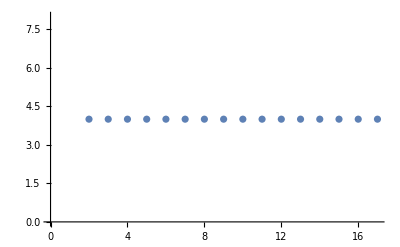

```mathematica
ListPlot[maxEV]
```

```mathematica
Pick[Re[EV[16]],Re[EV[16]],RankedMin[DeleteDuplicates@Re[EV[16]],2]]
```

{4.0648462481615511784174012775}

```mathematica
theta2 = {{3, Min[-Re[EV[3]]]}}
For[i=4,i<18,i++, AppendTo[theta2, {i,- Pick[Re[EV[i]],Re[EV[i]],RankedMin[DeleteDuplicates@Re[EV[i]],2]][[1]]}]]
```

{{3,-7.04441}}

```mathematica
theta2= {{3,-7.044413054249583},{4,-6.3887756207772295},{5,-5.867007753767463},{6,-5.448852582038963},{7,-5.11634631592154818060757425249104343291`26.39862387510801},{8,-4.85333399681403461854528805852786605003898960489722307075569135832341188831545`49.44673019553646},{9,-4.6462827659400978486694158672345609712525840473997111009009038990765899015826099505215161650724160934615982944160527`99.21637866627748},{10,-4.484293624417314227723860603565721398272323886534508016447014010473730225530817522588329475522969180034627277211615`99.4282774871019},{11,-4.35861102346628867428514017494852207735`19.52884128540465},{12,-4.2621187509022684851556768537331658707739406735489957363711`29.587129908974365},{13,-4.1889577322291242447697920853123254057894246546784005390336`29.667835756475068},{14,-4.1342656628265022215935603350257957766784744266593269186559`29.677818980635944},{15,-4.0940051091950668502302903845688310237934315355948514803712`29.684602092336064},{16,-4.064846248161551178417401277467392028644157630657985511424`29.689212105209712},{17,-4.044078491220758}};
```

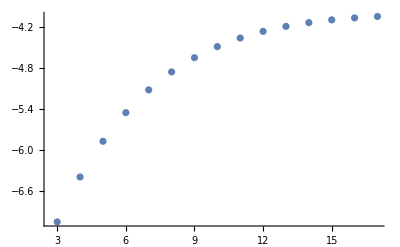

```mathematica
ListPlot[theta2]
```

```mathematica
theta3 = {{4, Min[-Re[EV[4]]]}}
For[i=5,i<18,i++, AppendTo[theta3, {i,- Pick[Re[EV[i]],Re[EV[i]],RankedMin[DeleteDuplicates@Re[EV[i]],3]][[1]]}]]
```

{{4,-12.0648}}

```mathematica
theta3 = {{4,-12.064765532201356},{5,-12.422512993599995},{6,-12.345800719755948},{7,-11.8942229471393707195743582820119711392`26.39862387510801},{8,-11.35392279041389426569012850288350568961645995757141483467785321287087574496096`49.44673019553646},{9,-10.8326912182567944468028401896416062569411012617501577893718504271208469745075013493314696594693911248428797834141329`99.21637866627748},{10,-10.3612103980801057712512035969647750032395669215613716859483267436117448599393229735049247481232784977249456800890405`99.4282774871019},{11,-9.94641139914405793873249740513540490323`19.52884128540465},{12,-9.58743302960339744240962137918020943394`29.587129908974365},{13,-9.2806809545509557086920337396867604371`29.667835756475068},{14,-9.02159433541385071194791731839155776657`29.677818980635944},{15,-8.80531755241467493169622937580582884443`29.684602092336064},{16,-8.62698030715160159197194722957437069258`29.689212105209712},{17,-8.481832048446643}};
```

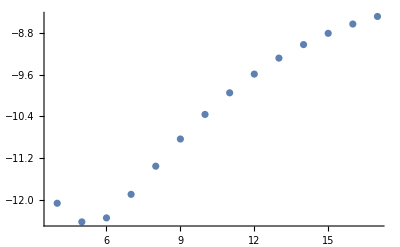

```mathematica
ListPlot[theta3]
```

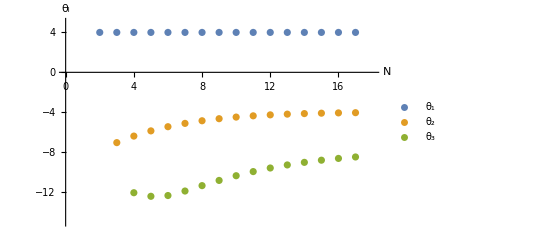

```mathematica
ListPlot[{maxEV, theta2, theta3},AxesLabel->{HoldForm[N],HoldForm[Subscript[θ, i]]},PlotRange->{{0, 18}, {-15, 5}}, PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{Subscript[θ, 1], Subscript[θ, 2], Subscript[θ, 3]}, AxesStyle->Directive[Black, 12]]
```

```mathematica
allu2 = { , -252.66, -91.24, -45.005, -23.6259, -14.076, -8.199, -4.8, -2.82, -1.65, -0.96, -0.55, -0.3, -0.18,-0.1, -0.058, -0.033};
allu3 = {  , ,  -18410, -11681, -7019.5, - 4198, -2506,  -1489.9, -881.3, -517.96 , -302, -175, -100, -57, -33, -18, -10.3 };
```

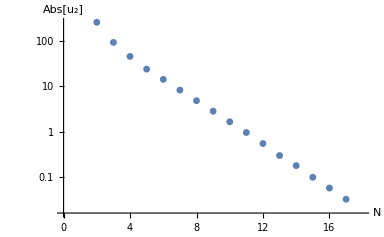

```mathematica
ListLogPlot[-allu2,AxesLabel->{Style[HoldForm[N], 14],Style[HoldForm[Abs[Subscript[u, 2]]],14]}, PlotRange->{{0, 18}, {-260, 0}}, AxesStyle->Directive[Black, 12]]
```

```mathematica
Export["u2valueeta0.png", %259, "PNG"]
```

u2valueeta0.png

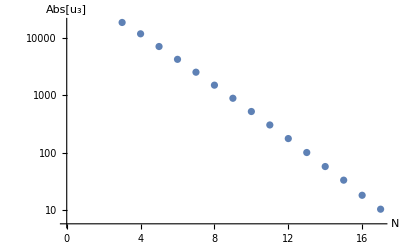

```mathematica
ListLogPlot[-allu3, AxesLabel->{Style[HoldForm[N], 14],Style[HoldForm[Abs[Subscript[u, 3]]],14]}, AxesStyle->Directive[Black, 12]]
```

```mathematica
Export["u3valueeta0.png", %263, "PNG"]
```

u3valueeta0.png